## Definitions

```mathematica
NbName = "802"; (*  ReverseSort[list_]:=Reverse@Sort@list;*)
λ0=0.5;       Needs["MaTeX`"]; t2=160;t2p=-60; U=2600; ttU=N[t2^2 t2p/U^3];

		Ls =Range[34,34,2]; 	    tV={0};				hV={{0.001,0,0}};

(*With[{φ=0,h=0.2},{ {h,0,φ}(*,{h,15,φ},{h,30,φ},{h,45,φ},{h,60,φ},{h,75,φ},{h,90,φ}*)  }]; (*.2612*) (*hV=Sort@Union[ Table[ {h,0,0},{h,0,.95,.025}]  ,  Table[ {h,0,0},{h,.0125,.95,.025}]] ;*)*)
		steps=350;                                     acuracy=5;   (* 4  32*)                             (* ΔeV=0.04999;*) ΔeV=0.099999; eVs=Table[ 1700 ξ, {ξ,0,0,ΔeV} ] ;  (*Table[ev,{ev,1500,1500,100}];*)

Js={0.};
Ks={-1.}; 
Γs={0.};(* Table[γ,{γ,0.,.0,.2}];*)
hV=Table[{h,0,0},{h,0.01,1,0.025}];
(*{  {0.1,0,0}  }*)(*Table[{h,0,0},{h,0.,1,.05}];*)(*Sort@Join[Table[{h^3,0,0},{h,.04,.4,.02}],Table[{h,0,0},{h,0.,1,.01}]  ]*)

(*hV={{0.00001,0,0} }  *)
```

#### Constants

```mathematica
mysort[list_]:=Module[ {sorted=Sort@list,half=⌊Length[list]/2⌋},  Join[ sorted[[half+1;;-1]], sorted[[half;;1;;-1]] ]  ];
```

```mathematica
Gmat={KroneckerProduct[  PauliMatrix[0],-ⅈ PauliMatrix[2] ],KroneckerProduct[- ⅈ PauliMatrix[2],PauliMatrix[3] ],KroneckerProduct[-ⅈ PauliMatrix[2],  PauliMatrix[1] ]};
Mmat= {KroneckerProduct[  PauliMatrix[3],ⅈ PauliMatrix[2] ],KroneckerProduct[ ⅈ PauliMatrix[2],PauliMatrix[0] ],KroneckerProduct[  PauliMatrix[1],ⅈ PauliMatrix[2] ]};
```

```mathematica
one[i_,j_,N_]:= SparseArray[ {i,j} -> 1, {N,N}];  block[i_,j_] := one[i,j,8];

hc=1/(√3){1,1,1};hb=1/(√2){1,-1,0};ha=1/(√6){1,1,-2};hx={1,0,0};
 hAngle[θ_,ϕ_]:= ha Cos[ϕ π/180] Sin[θ π/180]+hb Sin[ϕ π/180] Sin[θ π/180]+ hc Cos[θ π/180] ;  (* Magnetic field directions a, b, c*)
nx={1/2,(√3)/2};  ny={-1/2,(√3)/2};                                                                                           (* Honeycomb Bravais basis  *)

δx={-√3/2,-1/2}/√3;      
δy={√3/2,-1/2}/√3;     
δz={0,1}/√3;   
(* NN vectors  *)
```

```mathematica
(*χGx =- {{0.5249,0,0,0},{0,-1,0,0},{0,0,0,0},{0,0,0,0}};χGy = -{{0.5249,0,0,0},{0,0,0,0},{0,0,-1,0},{0,0,0,0}};χGz =-{{0.5249,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,-1}};
ωGA = {{ⅈ,0.000001,0.000001,0.000001},{-0.000001,ⅈ,0.000001,-0.000001},{-0.000001,-0.000001,ⅈ,0.000001},{-0.000001,0.000001,-0.000001,ⅈ}}; ωGB = ωGA;*)
```

```mathematica
round[x_]:=N[Round[1000000(x)]/1000000];
```

```mathematica
to3digits[list0_]:=Module[{list=list0},If[ Length@list>=3, list, list=Flatten[{{0},list},1]; If[ Length@list>=3, list,  list=Flatten[{{0},list},1] ] ]; StringJoin[ToString/@list]     ];
```

### matrices to TeX

```mathematica
Gmat=1/4{KroneckerProduct[  PauliMatrix[0],-ⅈ PauliMatrix[2] ],KroneckerProduct[- ⅈ PauliMatrix[2],PauliMatrix[3] ],KroneckerProduct[-ⅈ PauliMatrix[2],  PauliMatrix[1] ]};
Mmat= 1/4{KroneckerProduct[  PauliMatrix[3],ⅈ PauliMatrix[2] ],KroneckerProduct[ ⅈ PauliMatrix[2],PauliMatrix[0] ],KroneckerProduct[  PauliMatrix[1],ⅈ PauliMatrix[2] ]};
```

```mathematica
(*MatrixForm@Table[    Tr[ Pmat[[α]]^† .Pmat[[β]]]  , {α,1,3}, {β,1,3}]
MatrixForm@Table[    Tr[ Mmat[[α]]^† .Mmat[[β]]]  , {α,1,3}, {β,1,3}]
MatrixForm@Table[    Tr[ Mmat[[α]]^† .Gmat[[β]]]  , {α,1,3}, {β,1,3}]
MatrixForm@Table[    Tr[ Gmat[[α]]^† .Gmat[[β]]]  , {α,1,3}, {β,1,3}]
Module[{Jv,Kv,Gv,Gpv,ones,JM,Jbb},
ones={1,1,1};Jv={Subscript[J, x],Subscript[J, y],Subscript[J, z]};Kv=ones {Subscript[K, x],Subscript[K, y],Subscript[K, z]}; Gv={Subscript[Γ, x],Subscript[Γ, y],Subscript[Γ, z]}; Gpv=ones 0;
JM= Jmat[Jv,Kv,Gv,Gpv];
Print[MatrixForm/@JM];
Jbb=Table[ JM[[γ,γ,β]] ,{γ,1,3},{β,1,3}];
Print[MatrixForm@Jbb];(*
Print[TeXForm[Inverse@Jbb]];*)
Print[MatrixForm@(Inverse[Jbb].{h^x,h^y,h^z}    )  ];
];*)
```

```mathematica
Jmat[J_,K_,G_,Gp_]:={
{{J[[1]]+K[[1]],Gp[[1]],Gp[[1]]},{Gp[[1]],J[[1]],G[[1]]},{Gp[[1]],G[[1]],J[[1]]}},
{{J[[2]],Gp[[2]],G[[2]]},{Gp[[2]],J[[2]]+K[[2]],Gp[[2]]},{G[[2]],Gp[[2]],J[[2]]}},
{{J[[3]],G[[3]],Gp[[3]]},{G[[3]],J[[3]],Gp[[3]]},{Gp[[3]],Gp[[3]],J[[3]]+K[[3]]}}
};
```

```mathematica
ClearAll[Wi,Wj];
Wirm=Table[Subscript[Wi,α,β ],{α,0,3},{β,0,3}];
Wjrm=Table[Subscript[Wj,α,β ],{α,0,3},{β,0,3}];
Urm={Table[Subscript[Uxij,α,β ],{α,0,3},{β,0,3}],Table[Subscript[Uyij,α,β ],{α,0,3},{β,0,3}],Table[Subscript[Uzij,α,β ],{α,0,3},{β,0,3}] };
```

```mathematica
(*Tr[Wrm.Urm]==Sum[Wrm[[i,j]]Urm[[j,i]],{i,1,4},{j,1,4}]  
Tr[Wrm^ᵀ.Urm]==Sum[Wrm[[i,j]]Urm[[i,j]],{i,1,4},{j,1,4}]*)
```

```mathematica
(*ClearAll[J,K,Γ,Γp];
constantC=Module[{Jv,Kv,Gv,Gpv,ones},
ones={1,1,1};Jv=ones 0;Kv=ones K; Gv=ones 0; Gpv=ones 0;
Sum[Jmat[Jv,Kv,Gv,Gpv][[γ,α,β]](Tr[Wirm^ᵀ.Mmat[[α]] ]   Tr[Wjrm^ᵀ.Mmat[[β]] ] +2   Tr[Urm[[γ]]^ᵀ.Mmat[[α]].Urm[[γ]].Mmat[[β]] ]   ),{α,1,3},{β,1,3},{γ,1,3}]
];

Bham=Module[{Jv,Kv,Gv,Gpv,ones,hv,λv},
ones={1,1,1};Jv=ones 0;Kv=ones 0; Gv=ones 0; Gpv=ones 0;hv={hx,hy,hz};λv={λx,λy,λz};
Sum[ Sum[1/2 Jmat[Jv,Kv,Gv,Gpv][[γ,α,β]]Mmat[[α]]    Tr[Wjrm^ᵀ.Mmat[[β]] ],{α,1,3},{β,1,3}] - hv[[γ]] Mmat[[γ]] + λv[[γ]]Gmat⟦γ⟧ ,{γ,1,3}]
];
Aham=Module[{Jv,Kv,Gv,Gpv,ones}, 
ones={1,1,1};Jv=ones J;Kv=ones K; Gv=ones G; Gpv=ones 0;
Table[
Sum[Jmat[Jv,Kv,Gv,Gpv][[γ,α,β]](Mmat[[α]].Urm[[γ]].Mmat[[β]]    ),{α,1,3},{β,1,3}]
,{γ,1,3}]
];*)
```

### for pure

```mathematica
(*
g=toKappa[3 hAngle[180 x/π,0],1]
f=D[10/72 g,x]
f[x_]:=5 8 (Cos[(π x)/180]/(√3)+Sin[(π x)/180]/(√6))^2 (-(π Cos[(π x)/180])/(90 √6)-(π Sin[(π x)/180])/(180 √3))+5 16 (Cos[(π x)/180]/(√3)-√(2/3) Sin[(π x)/180]) (Cos[(π x)/180]/(√3)+Sin[(π x)/180]/(√6)) ((π Cos[(π x)/180])/(180 √6)-(π Sin[(π x)/180])/(180 √3))
th=Solve[f==0 && x<π 90/180 && x>π 50/180,x][[1,1,2]]
2 ArcTan[1/(√2)]
g=toKappa[3 hAngle[180 x/π,60],1];
f=D[20/72 g,x];
Plot[ {g,f },{x,0,π}]
g=toKappa[3 hAngle[180 x/π,0],1];
f=D[20/72 g,x];
Plot[ {g,  f },{x,0,π}]
*)
```

```mathematica
toλ[h_,Δv_:0.262]:= {h[[1]]^2,h[[2]]^2,h[[3]]^2}/Δv;
```

```mathematica
toKappa[h_,Δv_:0.262]:=8h[[1]]h[[2]]h[[3]]/(  3 Δv^2 );
```

if we know the direction, we can invert kappa to h

```mathematica
KappaToH[κ_,d_,Δv_:0.262]:=Module[{C=d[[1]]d[[2]]d[[3]]},If[C==0,{0,0,0},  d CubeRoot[3  Δv^2 κ/(8C)]   ]] ;
```

```mathematica
(*d={1,-1,0}/√2; abs=1;κ= toKappa[abs d];h=KappaToH[κ,d]; Print[N[abs d],"; ",h]*)
```

#### file

```mathematica
(*dataToFilePure[ parameters_,L_,acuracy_,gauge_,data_] :=
Module[ {path,f},		createDir@FileNameJoin[  {NotebookDirectory[], "Files","pure", gauge}] ;
		path = toPathPure[parameters,L,acuracy,gauge];		
		f = OpenWrite[path];
		 Write[ f, data];
		 Close[f];                ];
(*toPathPure[κ_,L_,K_,gauge_]:=  
FileNameJoin[  {NotebookDirectory[], "Files","pure", gauge,"data", StringReplace["K=Z-L=Y-kappa=M.txt",     {"Y"-> ToString[L], "M"->  ToString@N[Round[10000κ]/10000]  , "Z"-> ToString[K]}   ] }];*)

toPathPure[parameters0_,L_,acuracy_,gauge_]:= Module[{h ,hS,parameters=parameters0, r,ϕ,θ},h=parameters[[4]] ;hS=parameters[[8]]; {r,θ,ϕ}=hS;   
parameters[[1]]=0;parameters[[3]]=0;parameters[[5]]=0;parameters[[7]]=0;
FileNameJoin[{       NotebookDirectory[]   , "Files" ,"pure",gauge,StringReplace["t=X1_eV=X2_JKG=X3_JKGmod=X4",{"X1"->  ToString[parameters[[9]]],"X2"->  ToString[parameters[[10]]],"X3"->  ToString[parameters[[1;;3]]  ],"X4"->  ToString[parameters[[5;;7]]]   }] , "data"  , 
StringReplace["h=(M,N,T)_L=Y_A=Z.txt",{"Y"-> ToString[L], "Z"-> ToString[acuracy],"M"->  ToString[r,InputForm] ,"N"->ToString@ϕ,"T"->ToString@θ}   ] 
   }]];

loadDataPure[ path_]:= Module[{(*path,*)f,data}, 
(*path= toPathPure[κ,L,K,gauge];*)
f = OpenRead[path];
data=ReadList[ f];
Close[f];
data[[-1]]  ];*)
```

```mathematica
dataToFilePure[ parameters0_,L_,acuracy_,gauge_,data_] :=
Module[ {path,parameters=parameters0,f},		
(*createDir@FileNameJoin[{NotebookDirectory[],"Files","pure", gauge}] ;*)
parameters[[1]]=0;parameters[[3]]=0;parameters[[5]]=0;parameters[[7]]=0;
createDir@FileNameJoin[{NotebookDirectory[],"Files","pure",gauge, StringReplace["t=X1_eV=X2_JKG=X3_JKGmod=X4",
{"X1"->  ToString[parameters[[9]]],"X2"->  ToString[parameters[[10]]],"X3"->  ToString[parameters[[1;;3]]  ],"X4"->  ToString[parameters[[5;;7]]]   }]
           }] ;
		path = toPathPure[parameters,L,acuracy,gauge];		
		Print["Pure path=",path];Print[];
		f = OpenWrite[path];
		 Write[ f, data];
		 Close[f];                ];

toPathPure[parameters0_,L_,acuracy_,gauge_]:= Module[{h ,hS,parameters=parameters0, r,ϕ,θ},h=parameters[[4]] ;hS=parameters[[8]]; {r,θ,ϕ}=hS;   
parameters[[1]]=0;parameters[[3]]=0;parameters[[5]]=0;parameters[[7]]=0;
FileNameJoin[{NotebookDirectory[], "Files" ,"pure",gauge,StringReplace["t=X1_eV=X2_JKG=X3_JKGmod=X4",
{"X1"->  ToString[parameters[[9]]],"X2"->  ToString[parameters[[10]]],"X3"->  ToString[parameters[[1;;3]]  ],
"X4"->  ToString[parameters[[5;;7]]]   }] , "data"  , 
StringReplace["h=(M,N,T)_L=Y_A=Z.txt",{"Y"-> ToString[L], "Z"-> ToString[acuracy],"M"->  ToString[r,InputForm] ,"N"->ToString@ϕ,"T"->ToString@θ}   ] 
   }]];

loadDataPure[path_]:=Module[ {f,data},
f = OpenRead[path];
If[f==$Failed, Print["Failed to OpenRead file at: "]; Print[ path ]; Abort[] ];
data=ReadList[f];
Close[f];			
data[[-1]]
];
createDir[path_] :=
Module[ {l=Length@FileNames[path]},		
	If[ l==0,  CreateDirectory@File@FileNameJoin[{path,"data" }]; CreateDirectory@File@FileNameJoin[{path ,"graph" }]; 
,Null]  ];
```

```mathematica
dataToFilePure[ parameters0_,L_,acuracy_,data_,gauge_,NbName_]:=
Module[ {path,f,parameters=parameters0},
parameters[[1]]=0;parameters[[3]]=0;parameters[[5]]=0;parameters[[7]]=0;		
(*createDir@FileNameJoin[{Directory[],"Files","pure", gauge}] ;*)
createDir@FileNameJoin[{NotebookDirectory[],"Files",NbName,"pure",gauge, StringReplace["t=X1_eV=X2_JKG=X3_JKGmod=X4",
{"X1"->ToString[parameters[[9]]],"X2"->ToString[parameters[[10]]],"X3"->ToString[parameters[[1;;3]]],"X4"->ToString[parameters[[5;;7]]] }] }];
		path = toPathPure[parameters,L,acuracy,gauge,NbName];		
		(*Print["Pure path=",path];Print[];*)
		f = OpenAppend[path];
		 Write[ f, data];
		 Close[f];                ];		 
		 
toPathPure[parameters0_,L_,acuracy_,gauge_,NbName_]:= Module[{h ,hS,parameters=parameters0, r,ϕ,θ},h=parameters[[4]] ;hS=parameters[[8]]; {r,θ,ϕ}=hS;   
parameters[[1]]=0;parameters[[3]]=0;parameters[[5]]=0;parameters[[7]]=0;
FileNameJoin[{NotebookDirectory[], "Files" ,NbName,"pure",gauge,StringReplace["t=X1_eV=X2_JKG=X3_JKGmod=X4",
{"X1"->  ToString[parameters[[9]]],"X2"->  ToString[parameters[[10]]],"X3"->  ToString[parameters[[1;;3]]  ],
"X4"->  ToString[parameters[[5;;7]]]   }] , "data"  , 
StringReplace["h=(M,N,T)_L=Y_A=Z.txt",{"Y"-> ToString[L], "Z"-> ToString[acuracy],"M"->  ToString[r,InputForm] ,"N"->ToString@ϕ,"T"->ToString@θ}   ] 
   }]];

loadDataPure[path_]:=Module[ {f,data},
f = OpenRead[path];
If[f==$Failed, Print["Failed to OpenRead file at: "]; Print[ path ]; Abort[] ];
data=ReadList[f];
Close[f];			
data[[-1]]
];
```

```mathematica
quadrupoleToFilePure[parameters0_,L_,acuracy_,gauge_,data_,hI_]:= Module[{h,hS,path,r1,θ1,ϕ1,r2,θ2,ϕ2,f,parameters=parameters0,dirPath},
	parameters[[1]]=0; parameters[[3]]=0; parameters[[5]]=0; parameters[[7]]=0;		
	h=parameters[[4]]; hS=parameters[[8]]; {r1,θ1,ϕ1}=hI[[1]];  {r2,θ2,ϕ2}=hI[[-1]];  
	dirPath=FileNameJoin[{NotebookDirectory[],"Files",NbName,"pure",gauge,"QuadrupoleData"}];
	createDir@dirPath;
	path = FileNameJoin[{dirPath,"data", 
StringReplace["h=(M1,N1,T1)(M2,N2,T2)_L=Y_A=Z.txt",
{"Y"-> ToString[L], "Z"-> ToString[acuracy],"M1"->  ToString[r1,InputForm] ,"N1"->ToString@ϕ1,"T1"->ToString@θ1
,"M2"->  ToString[r2,InputForm] ,"N2"->ToString@ϕ2,"T2"->ToString@θ2}]   }];		
		(*Print["Quadrupole path path=",path];Print[];*)
		f = OpenAppend[path];
		 Write[ f, data];
		 Close[f];                ];

LoadquadrupolePure[parameters0_,L_,acuracy_,gauge_,hI_]:= Module[{h,hS,path,r1,θ1,ϕ1,r2,θ2,ϕ2,f,data,parameters=parameters0,dirPath},
	parameters[[1]]=0; parameters[[3]]=0; parameters[[5]]=0; parameters[[7]]=0;		
	h=parameters[[4]]; hS=parameters[[8]]; {r1,θ1,ϕ1}=hI[[1]];  {r2,θ2,ϕ2}=hI[[-1]];  
	dirPath=FileNameJoin[{NotebookDirectory[],"Files",NbName,"pure",gauge,"QuadrupoleData"}];
	createDir@dirPath;
	path = FileNameJoin[{dirPath,"data", StringReplace["h=(M1,N1,T1)(M2,N2,T2)_L=Y_A=Z.txt",
	{"Y"-> ToString[L], "Z"-> ToString[acuracy],"M1"->  ToString[r1,InputForm] ,"N1"->ToString@ϕ1,"T1"->ToString@θ1,"M2"->  ToString[r2,InputForm] ,"N2"->ToString@ϕ2,"T2"->ToString@θ2}]   }];		
	
	f = OpenRead[path];
	If[f==$Failed, Print["Failed to OpenRead file at: "]; Print[ path ]; Abort[] ];
	data=ReadList[f];
	Close[f];			
	data
        ];
```

#### Auxiliary matrices for the Hamiltonian [2x2 matrices]

we define Z2 gauge field u[r] for each unit cell r as a three component vector which each component correspond α to the gauge field in the α bond for the A site in the unit cell r.

```mathematica
toR[m0_,n0_,L_,M_]:= Module[{Δn=⌊n0/L⌋,n,m},n=Mod[n0 ,L]; m=Mod[m0+M Δn,L]; m + n L+1];
```

```mathematica
HNN[K_,κ_,λ_,u_,m_,n_,L_,M_]:=Module[{r=toR[m,n ,L,M]},Table[{{0,(-K⟦r,α⟧+λ[[α]]) u⟦r,α⟧ },{0,0}},{α,1,3}]]; 
HNNNA[K_,κ_,λ_,u_,m_,n_,L_,M_]:=Module[{
r1={toR[m,n ,L,M],toR[m,n ,L,M],toR[m,n,L,M]},
r2={toR[m+1,n-1 ,L,M],toR[m,n+1 ,L,M],toR[m-1,n,L,M]}        }      ,
Table[{{κ u[[r1[[α]],α]] u[[r2[[α]],Mod[α+1,3,1] ]],0},{0,0 }},{α,1,3}]
];
HNNNB[K_,κ_,λ_,u_,m_,n_,L_,M_]:=Module[{
r1={toR[m-1,n ,L,M],toR[m,n -1,L,M],toR[m,n,L,M]},
r2={toR[m-1,n ,L,M],toR[m,n-1 ,L,M],toR[m,n,L,M]}        }      ,
Table[{{0,0},{0,κ u[[r1[[α]],α]] u[[r2[[α]],Mod[α+1,3,1] ]]}},{α,1,3}]
];
					
Hreal[K_,κ_,λ_,u_,L_,M_,δk_] := Module[{Nc=L^2,H },

 H= ⅈ Sum[Module[{Hnn,HnnnA,HnnnB, φ=δk.(m nx+n ny),
r={toR[m+1,n ,L,M],toR[m,n+1 ,L,M],toR[m,n ,L,M]},
RA={toR[m+1,n-1 ,L,M],toR[m,n+1 ,L,M],toR[m-1,n,L,M]},
RB={toR[m-1,n+1 ,L,M],toR[m,n-1 ,L,M],toR[m+1,n,L,M]}    },

Hnn=HNN[K,κ,λ,u,m,n,L,M] ;HnnnA=HNNNA[K,κ,λ,u,m,n,L,M] ;HnnnB=HNNNB[K,κ,λ,u,m,n,L,M] ;

Sum[       KroneckerProduct[ one[r[[3]],r[[α]],Nc],Hnn[[α]]]   +
KroneckerProduct[ one[r[[3]],RA[[α]],Nc],HnnnA[[α]]]   +
KroneckerProduct[ one[r[[3]],RB[[α]],Nc],HnnnB[[α]]]   ,{α,1,3}] Exp[ⅈ φ]      ] 
,{m,0,L-1},{n,0,L-1}];

 H+H†];

TmatPure[L_] :=KroneckerProduct[   IdentityMatrix[L^2],  {{1,1},{ⅈ,-ⅈ}} ];
UmatPure[H_]:= Module[ {R=Quiet@Eigensystem@N[H]},ReverseSort[Rᵀ]ᵀ⟦2⟧ᵀ ];
EandUPure[H_]:= Module[ {R=Transpose@ReverseSort@Transpose@Quiet@Eigensystem@N[H]},{R[[1]],R⟦2⟧ᵀ }];
𝕌occupiedPure[TU_,Nc_]:= Drop[Take[TUᵀ,-Nc-1],{2}]ᵀ;


correlations[U_,u_,L_,M_] :=Module[  { Nc=L^2,𝕌,𝕌h,icc,SS },
𝕌=TmatPure[L].U;𝕌h=𝕌[[;;,-Nc;;-1]];icc=Chop[ⅈ  𝕌h.𝕌h† ];

SS[[3]]=ArrayFlatten[ # ,1]& @ Table[ 
Module[{ rz,Io,J},rz=m+(n-1)L-1; Io=Mod[α+2rz,2 L^2,1];J=Mod[β + 4 +2rz,2 L^2,1];
-u[[m,n]] icc[[J,Io]]    ], {m,1,L},{n,1,L},  {α,1,4},{β,1,4} ];

SS[[1]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,rx,mx,Io,J},mx=Mod[m+1,L,1]; rz=m+(n-1)L-1;rx=mx+(n-1)L-1;Io=Mod[α+2rz,2 L^2,1];J=Mod[β + 4+2rx,2 L^2,1];
icc[[J,Io]]      ]   , {m,1,L},{n,1,L},  {α,1,4},{β,1,4} ];
SS[[2]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,ry,my,ny,Io,J}, 
ny=Mod[n+1,L,1];my=If[ny==1,Mod[m-M,L,1] , m];  ry=my+(ny-1)L-1;rz=m+(n-1)L-1;Io=Mod[α+2rz,2 L^2,1];J=Mod[β + 4+2ry,2 L^2,1];
icc[[J,Io]]    ]    , {m,1,L},{n,1,L},  {α,1,4},{β,1,4} ];
SS
];
```

#### to MF pure

```mathematica
(* writting the exp values in the form of the MF parameters:   *)
toMFparametersPure[U_,u_,L_,M_] :=Module[  { Nc=L^2,𝕌,𝕌h,icc,SS=Array[Null,3]  },
𝕌=TmatPure[L].U;𝕌h=𝕌[[;;,-Nc;;-1]];icc=Chop[ⅈ  𝕌h.𝕌h† ];

SS[[3]]=ArrayFlatten[ # ,1]& @ Table[ 
Module[{ rz,Io,J},rz=m+n L; Io=Mod[1+2rz,2 L^2,1];J=Mod[1 + 1 +2rz,2 L^2,1];
 {{    1/2(icc[[J,Io]]-icc[[Io,J]] ),0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,u[[ Mod[rz+1, L^2,1] ,3]] }}    ],{n,0,L-1} , {m,0,L-1}];

SS[[1]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,rx,mx,Io,J},mx=Mod[m+1,L]; rz=m+n L;rx= mx+n L ;Io=Mod[1+2rz,2 L^2,1];J=Mod[1 + 1+2rx,2 L^2,1];
 {{   1/2(icc[[J,Io]]-icc[[Io,J]] ) ,0,0,0},{0,u[[ Mod[rz+1,L^2,1] ,1]] ,0,0},{0,0,0,0},{0,0,0,0}}     ] ,{n,0,L-1} , {m,0,L-1}];
SS[[2]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,ry,my,ny,Io,J}, ny=Mod[n+1,L];my=If[ny==0,Mod[m-M,L] , m];  ry= my+ny L;
rz=m+n L;Io=Mod[1+2rz,2 L^2,1];J=Mod[1+ 1+2ry,2 L^2,1];
 {{     1/2(icc[[J,Io]]-icc[[Io,J]] ),0,0,0},{0,0,0,0},{0,0,u[[ Mod[rz+1,L^2,1],2]] ,0},{0,0,0,0}}        ],{n,0,L-1} , {m,0,L-1}];
SS        ];

toMFparametersOccupiedPure[U_,u_,L_,M_] :=Module[  { Nc=L^2,𝕌,𝕌h,icc,SS=Array[Null,3]  },
𝕌=TmatPure[L].U;(*𝕌h=𝕌[[;;,-Nc;;-1]];*)𝕌h=𝕌occupiedPure[𝕌,Nc];icc=Chop[ⅈ  𝕌h.𝕌h† ];

SS[[3]]=ArrayFlatten[ # ,1]& @ Table[ 
Module[{ rz,Io,J},rz=m+n L; Io=Mod[1+2rz,2 L^2,1];J=Mod[1 + 1 +2rz,2 L^2,1];
 {{    1/2(icc[[J,Io]]-icc[[Io,J]] ),0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,u[[ Mod[rz+1, L^2,1] ,3]] }}    ],{n,0,L-1} , {m,0,L-1}];

SS[[1]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,rx,mx,Io,J},mx=Mod[m+1,L]; rz=m+n L;rx= mx+n L ;Io=Mod[1+2rz,2 L^2,1];J=Mod[1 + 1+2rx,2 L^2,1];
 {{   1/2(icc[[J,Io]]-icc[[Io,J]] ) ,0,0,0},{0,u[[ Mod[rz+1,L^2,1] ,1]] ,0,0},{0,0,0,0},{0,0,0,0}}     ] ,{n,0,L-1} , {m,0,L-1}];
SS[[2]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,ry,my,ny,Io,J}, ny=Mod[n+1,L];my=If[ny==0,Mod[m-M,L] , m];  ry= my+ny L;
rz=m+n L;Io=Mod[1+2rz,2 L^2,1];J=Mod[1+ 1+2ry,2 L^2,1];
 {{     1/2(icc[[J,Io]]-icc[[Io,J]] ),0,0,0},{0,0,0,0},{0,0,u[[ Mod[rz+1,L^2,1],2]] ,0},{0,0,0,0}}        ],{n,0,L-1} , {m,0,L-1}];
SS        ];
```

```mathematica
(* writting the exp values in the form of the MF parameters:   *)
toMFparametersPure[U_,u_,L_,M_] :=Module[  { Nc=L^2,𝕌,𝕌h,icc,SS=Array[Null,3]  },
𝕌=TmatPure[L].U;𝕌h=𝕌[[;;,-Nc;;-1]];icc=Chop[ⅈ  𝕌h.𝕌h† ];

SS[[3]]=ArrayFlatten[ # ,1]& @ Table[ 
Module[{ rz,Io,J},rz=m+n L; Io=Mod[1+2rz,2 L^2,1];J=Mod[1 + 1 +2rz,2 L^2,1];
 {{   -u[[rz+1,3]]  1/2(icc[[J,Io]]-icc[[Io,J]] ),0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,-1 }}    ],{n,0,L-1} , {m,0,L-1}];

SS[[1]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,rx,mx,Io,J},mx=Mod[m+1,L]; rz=m+n L;rx= mx+n L ;Io=Mod[1+2rz,2 L^2,1];J=Mod[1 + 1+2rx,2 L^2,1];
 {{ -u[[ rz+1 ,1]]  1/2(icc[[J,Io]]-icc[[Io,J]] ) ,0,0,0},{0,-1 ,0,0},{0,0,0,0},{0,0,0,0}}     ] ,{n,0,L-1} , {m,0,L-1}];
SS[[2]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,ry,my,ny,Io,J}, ny=Mod[n+1,L];my=If[ny==0,Mod[m-M,L] , m];  ry= my+ny L;
rz=m+n L;Io=Mod[1+2rz,2 L^2,1];J=Mod[1+ 1+2ry,2 L^2,1];
 {{   -u[[rz+1,2]]  1/2(icc[[J,Io]]-icc[[Io,J]] ),0,0,0},{0,0,0,0},{0,0,-1 ,0},{0,0,0,0}}        ],{n,0,L-1} , {m,0,L-1}];
SS        ];
```

#### gauge pure

```mathematica
nx={1/2,(√3)/2};ny={-1/2,(√3)/2};     δx={-√3/2,-1/2}/√3;δy={√3/2,-1/2}/√3;δz={0,1}/√3;
 
asites[m_,n_]:=m nx+n ny;
bsites[m_,n_]:=m nx+n ny-δz;
σsites[m_,n_,σ_]:=m nx+n ny-σ δz;
```

```mathematica
gaugeConfigUPure[σ_,L1_,L2_]:=Module[{bonds,linethick=.012 (Log[49]/Log[L1 L2]),lattice,size}, size = 0.01 (Log[49]/Log[L1 L2])^2 ;
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , {Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L1-1},{n,0,L2-1} ], 2    ];
bonds=Flatten[Table[
{    
{ If[σ[[m+n L1+1,3]]>= 0, Cyan ,Darker@Blue],Thickness[linethick],Line[{asites[m,n],bsites[m,n]}]},                   (*z-bonds*)
{If[σ[[m+n L1+1,1]]>= 0, Magenta ,Darker@Red],Thickness[linethick],Line[{asites[m,n],bsites[m+1,n]}]},             (*x-bonds*)
{If[σ[[m+n L1+1,2]]>= 0, Darker@Yellow ,Darker@Green],Thickness[linethick],Line[{asites[m,n],bsites[m,n+1]}]}              (*y-bonds*)
},{m,0,L1-1},{n,0,L2-1} ], 2    ];
Graphics[{bonds,lattice},ImageSize->300]            ];  

uniformU[u_,L1_,L2_]:=Table[   {u,u,u}     ,L1 L2];
flipUoneZbond[u0_,L1_,L2_]:= Module[{R1,u=u0,m0=⌈L1/2⌉ -1,n0=⌈(L2+1)/2⌉-1 }, R1= { m0,n0};
  Module[{r,m,n}, m =Mod[R1[[1]],L1] ; n=Mod[R1[[2]],L2] ; r = m+n L1+1;    u[[r, 3 ]] =-u0[[r,3 ]];      ]   ;  u           ];
flipUZMaxSpaced[u0_,L1_,L2_]:= Module[{R1,d,u=u0,m0=⌈L1/2⌉ -1,n0=⌈(L2+1)/2⌉-1 }, d=⌊(L1-1)/2⌋; R1= { m0,n0};
Do[  Module[{r,m,n}, m =Mod[R1[[1]]+i,L1] ; n=Mod[R1[[2]]-i,L2] ; r = m+n L1+1;    u[[r, 3 ]] =-u0[[r,3 ]];      ]   , {i,0,d-1}];  u           ];
```

consider other gauge configurations:

```mathematica
uniformU[u_,L_]:=Table[ {u,u,u},L^2];
gauge2vX[u0_,L_]:= Module[{d1,d2,u=u0,mS,nS,r2 },   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;  mS=r2-1;nS=r2-1;
Do[  Module[{r,m,n}, m =mS ; n=nS+i ; r = m+n L+1;    u[[r,1]] =-u0[[r,1]];      ]   , {i,1,d1}];               u           ];
gauge2vY[u0_,L_]:= Module[{d1,d2,u=u0,mW,nW,r2 },   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;  mW=r2-1;nW=L-r2-1;
Do[  Module[{r,m,n}, m =mW+i; n=nW; r = m+n L+1;    u[[r,2]] =-u0[[r,2]];      ]   , {i,1,d1}];                u           ];
gauge2vZ[u0_,L_]:= Module[{d1,d2,u=u0,mW,nW,r2 },   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;  mW=r2-1;nW=L-r2-1;
Do[  Module[{r,m,n}, m =mW+i; n=nW-i+1; r = m+n L+1;    u[[r,3]] =-u0[[r,3]];      ]   , {i,1,d1}];                u           ];
gauge4v[u0_,L_]:= Module[{d1,d2,u=u0,mS,nS,mN,nN,r2 },   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;  
mS=r2-1;nS=r2-1;mN=L-r2-1;nN=L-r2-1;
Do[  Module[{r,m,n}, m =mS ; n=nS+i ;       r = m+n L+1;    u[[r,1]] =-u0[[r,1]];      ]   , {i,1,d1}];   
Do[  Module[{r,m,n}, m =mN ; n=nN-i+1; r = m+n L+1;    u[[r,1]] =-u0[[r,1]];      ]   , {i,1,d1}];               u           ];
```

```mathematica
positionVortex[v_,L_]:=Module[{d1,d2,r2,mS,nS,mW,nW,mE,nE,mN,nN},
		 r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2; 

		 mS=r2-1;           nS=r2-1;
		 mW=r2-1;           nW=L-r2-1;
		 mE=L-r2-1;     nE=r2-1;
		 mN=L-r2-1;     nN=L-r2-1;

		{{mS,nS},{mW,nW},{mE,nE},{mN,nN}}[[v]]
]
```

v=1  South, v=2 West, v=3 East, v=4 North

```mathematica
gauge2v[u0_,L_,α_]:= Module[{d1,d2,u=u0,m0,n0,r2 ,v},   r2= ⌊1/2 ⌈L/2⌉⌋;   Do[  Module[{r,m,n},
							m={r2-1,             r2-1+i,              r2-1+i   }⟦α⟧; 
							n={r2-1+i,       L-r2-1,             L-r2-i   }⟦α⟧;
 r = m+n L+1;    u[[r,α]] =-u0[[r,α]];      ]   , {i,1,d1}];                u           ];
```

#### correlation

```mathematica
(*spin-spin correlation*)
ssC[χ_,ω_,r_,L_,M_]:=Module[ {m,n,mx,my,ny,R},n=⌊(r-1)/L⌋;m=r-1-n L;mx=Mod[m+1,L];ny=Mod[n+1,L];my=If[ny==0,Mod[m-M,L] , m];
 R={ mx+n L +1,my+ny L +1,m+n L +1};
Table[ ω[[1,r,α+1,0+1]]   ω[[2,R[[γ]],β+1,0+1]]   - χ[[γ,r,α+1,β+1]] χ[[γ,r,0+1,0+1]]  +  χ[[γ,r,α+1,0+1]] χ[[γ,r,0+1,β+1]]
,
{γ,1,3}, {α,1,3},{β,1,3}]
];

ssC2[χ_,ω_,m_,n_,L_]:=Module[ {mx,ny,R,r=Mod[m,L] +Mod[n,L] L +1},mx=Mod[m+1,L];ny=Mod[n+1,L]; R={ mx+n L +1,m+ny L +1,r};
Table[ ω[[1,r,α+1,0+1]]   ω[[2,R[[γ]],β+1,0+1]]   - χ[[γ,r,α+1,β+1]] χ[[γ,r,0+1,0+1]]  +  χ[[γ,r,α+1,0+1]] χ[[γ,r,0+1,β+1]],
{γ,1,3}, {α,1,3},{β,1,3}]                                      ];
```

#### electric field

```mathematica
uniform[K_,L1_,L2_]:=Table[   {K,K,K}     ,L1 L2];  

(************* Fix this ******************)
(*addVortex[ Ko_,K0_, R_,L1_,L2_]:= Module[ {m=R[[1]],n=R[[2]],K=Ko,r=Table[0,6]},
r[[1]]=m+n L1 +1;r[[2]]=Mod[m-1,L1]+Mod[n+1,L2] L1 +1;r[[3]]=Mod[m-1,L1]+n L1 +1;r[[4]]=Mod[m-1,L1]+Mod[n-1,L2] L1 +1;r[[5]]=m+Mod[n-1,L2] L1+1;r[[6]]=Mod[m+1,L1]+Mod[n-1,L2] L1 +1;
K[[ r[[1]],3    ]]=K0;K[[ r[[2]],2    ]]=K0;K[[ r[[3]],1    ]]=K0;K[[ r[[4]],3   ]]=K0;K[[ r[[5]],2    ]]=K0;K[[ r[[6]],1   ]]=K0;
K];*)
(**************         ****************)

addVortex[ Ko_,K0_, R_,L1_,L2_]:= Module[ {m=R[[1]],n=R[[2]],K=Ko,r=Table[0,6]},
K[[ m+n L1 +1,3    ]]=K0;  
K[[ Mod[m+1,L1]+Mod[n-1,L2] L1 +1  ,2    ]]=K0;
K[[ Mod[m+1,L1]+n L1 +1,1    ]]=K0;
K[[ Mod[m+1,L1]+Mod[n+1,L2] L1 +1  ,3   ]]=K0;
K[[ m+Mod[n+1,L2] L1+1   ,2    ]]=K0;
K[[ Mod[m-1,L1]+Mod[n+1,L2] L1 +1  ,1   ]]=K0;
K];
(*
addVortex[ Ko_,K0_, R_,L1_,L2_]:= Module[ {m=R[[1]],n=R[[2]],K=Ko,r=Table[0,6]},
K[[ m+n L1 +1,3    ]]=K0;
K[[ Mod[m-1,L1]+Mod[n+1,L2] L1 +1  ,2    ]]=K0;
K[[ Mod[m-1,L1]+n L1 +1,1    ]]=K0;
K[[ Mod[m-1,L1]+Mod[n-1,L2] L1 +1  ,3   ]]=K0;
K[[ m+Mod[n-1,L2] L1+1   ,2    ]]=K0;
K[[ Mod[m+1,L1]+Mod[n+1,L2] L1 +1  ,1   ]]=K0;
K];*)
add2Vortices[ Ko_,K1_,K2_, R1_,R2_,L1_,L2_] :=Module[ {K}, K = addVortex[ Ko,K1, R1,L1,L2]; addVortex[ K,K2, R2,L1,L2]];
add4Vortices[ K0_,Kmod_, R1_,R2_, R3_,R4_,L_] :=Module[ {K}, K = addVortex[ K0,Kmod, R1,L,L]; K = addVortex[ K,Kmod, R2,L,L]; K = addVortex[ K,Kmod, R3,L,L]; addVortex[ K,Kmod, R4,L,L]];
add2VorticesMaxSpaced[ Ko_,K1_,K2_,L1_,L2_] := Module[{R1,R2,d}, d=⌊(L1-1)/2⌋; R1= {⌊L1/2⌋ ,⌊(L2+1)/2⌋ };R2= {⌊L1/2⌋   +d,⌊(L2+1)/2⌋ -d};
	add2Vortices[ Ko,K1,K2, R1,R2,L1,L2]];
add4VorticesMaxSpaced[ K0_,Kmod_,L_] :=Module[ {RS,RE,RW,RN,r2},   r2= ⌊1/2 ⌈L/2⌉⌋;
		RS={(r2-1),(r2-1)};
		RW={(r2-1),(L-r2-1)};
		RE={(L-r2-1),(r2-1)};
		RN={(L-r2-1),(L-r2-1)};
add4Vortices[ K0,Kmod, RS,RW, RE,RN,L] ];

χGx = {{0.5249,0,0,0},{0,-1,0,0},{0,0,0,0},{0,0,0,0}};χGy = {{0.5249,0,0,0},{0,0,0,0},{0,0,-1,0},{0,0,0,0}};χGz ={{0.5249,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,-1}};
(*ωGA =  ⅈ IdentityMatrix[4];ωGB =  ⅈ IdentityMatrix[4];*)
```

#### more

```mathematica
asites[m_,n_]:=m nx+n ny;
bsites[m_,n_]:=m nx+n ny-δz;
gaugeConfig[χ_,L1_,L2_]:=Module[{bonds,linethick=.012 (Log[49]/Log[L1 L2]),lattice,size}, size = 0.01 (Log[49]/Log[L1 L2])^2 ;
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , {Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L1-1},{n,0,L2-1} ], 2    ];
bonds=Flatten[Table[
{    
{ If[χ[[3,m+n L1+1]][[4,4]]>= 0, Cyan ,Darker@Blue], If[χ[[3,m+n L1+1]][[4,4]]>= 0, Thickness[1.5 linethick] ,Thickness[linethick] ] ,Line[{asites[m,n],bsites[m,n]}]},                   (*z-bonds*)
{If[χ[[1,m+n L1+1]][[2,2]]>= 0, Magenta ,Darker@Red],If[χ[[1,m+n L1+1]][[2,2]]>= 0,Thickness[1.5 linethick] ,Thickness[linethick] ],Line[{asites[m,n],bsites[m+1,n]}]},             (*x-bonds*)
{If[χ[[2,m+n L1+1]][[3,3]]>= 0, Darker@Yellow ,Darker@Green],If[χ[[2,m+n L1+1]][[3,3]]>= 0, Thickness[1.5linethick] ,Thickness[linethick] ],Line[{asites[m,n],bsites[m,n+1]}]}              (*y-bonds*)
},{m,0,L1-1},{n,0,L2-1} ], 2    ];
Graphics[{bonds,lattice},ImageSize->300]
];
```

```mathematica
gaugeConfig[χ_,L1_,L2_]:=Module[{bonds,linethick=.012 (Log[49]/Log[L1 L2]),lattice,size}, size = 0.01 (Log[49]/Log[L1 L2])^2 ;
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , {Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L1-1},{n,0,L2-1} ], 2    ];
bonds=Flatten[Table[
{    
{ If[χ[[3,m+n L1+1]][[4,4]]>= 0, Darker@Yellow ,Darker@Blue],If[χ[[3,m+n L1+1]][[4,4]]>= 0,  Thickness[1.5linethick] ,Thickness[linethick] ] ,Line[{asites[m,n],bsites[m,n]}]},                   (*z-bonds*)
{If[χ[[1,m+n L1+1]][[2,2]]>= 0, Cyan,Darker@Red],If[χ[[1,m+n L1+1]][[2,2]]>= 0,Thickness[1.5 linethick] ,Thickness[linethick] ],Line[{asites[m,n],bsites[m+1,n]}]},             (*x-bonds*)
{If[χ[[2,m+n L1+1]][[3,3]]>= 0, Magenta ,Darker@Green],If[χ[[2,m+n L1+1]][[3,3]]>= 0, Thickness[1.5linethick] ,Thickness[linethick] ],Line[{asites[m,n],bsites[m,n+1]}]}              (*y-bonds*)
},{m,0,L1-1},{n,0,L2-1} ], 2    ];
Graphics[{bonds,lattice},ImageSize->300]
];
```

```mathematica
MFΓconfig[χ_,L_]:=Module[{bonds,linethick=.015 (Log[7]/Log[L]),lattice,size,Γx,Γy,Γz,max,meanX,meanY,meanZ}, size = 0.01 (Log[7]/Log[L])^2 ; 
Γx=Table[  (χ[[1,r]][[3,4]]+χ[[1,r]][[4,3]])/2, {r,1,L^2} ]; 
Γy=Table[  (χ[[2,r]][[2,4]]+χ[[2,r]][[4,2]])/2, {r,1,L^2} ];
Γz=Table[ (χ[[3,r]][[3,2]]+χ[[3,r]][[2,3]])/2, {r,1,L^2} ];
max=Max@Abs@Union[Γx,Γy,Γz];meanX=(Mean@Γx)/max; meanY=(Mean@Γy)/max; meanZ=(Mean@Γz)/max;
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , 
{Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L-1},{n,0,L-1} ], 2    ];
bonds=Flatten[Table[
Module[{χx,χy,χz},
χx=1/max(χ[[1,m+n L+1]][[3,4]]+χ[[1,m+n L+1]][[4,3]])/2;
χy=1/max(χ[[2,m+n L+1]][[2,4]]+χ[[2,m+n L+1]][[4,2]])/2;
χz=1/max(χ[[3,m+n L+1]][[2,3]]+χ[[3,m+n L+1]][[3,2]])/2;
{    
{Blend[ {Cyan,White,Darker@Red},1/2-χx/2],Opacity[.7+Abs[χx-meanX]],Thickness[  Abs[χx]^2.85 linethick],Line[{asites[m,n],bsites[m+1,n]}]},   (*x-bonds*)
{Blend[ {Magenta,White,Darker@Green},1/2-χy/2],Opacity[.7+Abs[χy-meanY]],Thickness[Abs[χy]^2.85 linethick],Line[{asites[m,n],bsites[m,n+1]}]}, (*y-bonds*)
{Blend[ {Darker@Yellow,White,Darker@Blue},1/2-χz/2],Opacity[.7+Abs[χz-meanZ]],Thickness[Abs[χz]^2.85 linethick],Line[{asites[m,n],bsites[m,n]}]}     (*z-bonds*)
}],{m,0,L-1},{n,0,L-1} ], 2    ];
Graphics[{bonds,lattice},ImageSize->600]
];
```

```mathematica
MFJconfig[χ_,L_]:=Module[{bonds,linethick=.015 (Log[7]/Log[L]),lattice,size,Jx,Jy,Jz,max,meanX,meanY,meanZ}, size = 0.01 (Log[7]/Log[L])^2 ; 
Jx=Table[  (χ[[1,r]][[3,3]]+χ[[1,r]][[4,4]])/2, {r,1,L^2} ]; 
Jy=Table[  (χ[[2,r]][[2,2]]+χ[[2,r]][[4,4]])/2, {r,1,L^2} ]; 
Jz=Table[ (χ[[3,r]][[2,2]]+χ[[3,r]][[3,3]])/2, {r,1,L^2} ]; 
max=Max@Abs@Union[Jx,Jy,Jz];meanX=(Mean@Jx)/max; meanY=(Mean@Jy)/max; meanZ=(Mean@Jz)/max;
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , 
{Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L-1},{n,0,L-1} ], 2    ];
bonds=Flatten[Table[
Module[{χx,χy,χz},
χx=1/max(χ[[1,m+n L+1]][[3,3]]+χ[[1,m+n L+1]][[4,4]])/2;
χy=1/max(χ[[2,m+n L+1]][[2,2]]+χ[[2,m+n L+1]][[4,4]])/2;
χz=1/max(χ[[3,m+n L+1]][[2,2]]+χ[[3,m+n L+1]][[3,3]])/2; (*Print["x=",χx,"; y=",χy,"; z=",χz,"; "];*)
{    
{Blend[ {Cyan,Gray,Darker@Red},1/2-χx/2],Opacity[.5+5Abs[χx-meanX]],Thickness[  Abs[χx]^2. linethick],Line[{asites[m,n],bsites[m+1,n]}]},   (*x-bonds*)
{Blend[ {Magenta,Gray,Darker@Green},1/2-χy/2],Opacity[.5+5Abs[χy-meanY]],Thickness[Abs[χy]^2. linethick],Line[{asites[m,n],bsites[m,n+1]}]}, (*y-bonds*)
{Blend[ {Darker@Yellow,Gray,Darker@Blue},1/2-χz/2],Opacity[.5+5Abs[χz-meanZ]],Thickness[Abs[χz]^2. linethick],Line[{asites[m,n],bsites[m,n]}]}     (*z-bonds*)
}],{m,0,L-1},{n,0,L-1} ], 2    ];
Graphics[{bonds,lattice},ImageSize->600]
];
```

```mathematica
MFKconfig[χ_,L_]:=Module[{bonds,linethick=.015 (Log[7]/Log[L]),lattice,size,Kx,Ky,Kz,max,meanX,meanY,meanZ}, size = 0.01 (Log[7]/Log[L])^2 ; 
Kx=Table[ χ[[1,r]][[2,2]]- (χ[[1,r]][[3,3]]+χ[[1,r]][[4,4]])/2, {r,1,L^2} ];  
Ky=Table[ χ[[2,r]][[3,3]]- (χ[[2,r]][[2,2]]+χ[[2,r]][[4,4]])/2, {r,1,L^2} ]; 
Kz=Table[χ[[3,r]][[4,4]]- (χ[[3,r]][[2,2]]+χ[[3,r]][[3,3]])/2, {r,1,L^2} ];  
max=Max@Abs@Union[Kx,Ky,Kz];meanX=(Mean@Kx)/max; meanY=(Mean@Ky)/max; meanZ=(Mean@Kz)/max;
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , 
{Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L-1},{n,0,L-1} ], 2    ];
bonds=Flatten[Table[
Module[{χx,χy,χz},
χx=1/max(χ[[1,m+n L+1]][[2,2]]-(χ[[1,m+n L+1]][[3,3]]+χ[[1,m+n L+1]][[4,4]])/2);
χy=1/max(χ[[2,m+n L+1]][[3,3]]-(χ[[2,m+n L+1]][[2,2]]+χ[[2,m+n L+1]][[4,4]])/2);
χz=1/max(χ[[3,m+n L+1]][[4,4]]-(χ[[3,m+n L+1]][[2,2]]+χ[[3,m+n L+1]][[3,3]])/2); (*Print["x=",χx,"; y=",χy,"; z=",χz,"; "];*)
{    
{Blend[ {Cyan,Gray,Darker@Red},1/2-χx/2],Opacity[.7+Abs[χx-meanX]],Thickness[  Abs[χx]^2.9 linethick],Line[{asites[m,n],bsites[m+1,n]}]},   (*x-bonds*)
{Blend[ {Magenta,Gray,Darker@Green},1/2-χy/2],Opacity[.7+Abs[χy-meanY]],Thickness[Abs[χy]^2.9 linethick],Line[{asites[m,n],bsites[m,n+1]}]}, (*y-bonds*)
{Blend[ {Darker@Yellow,Gray,Darker@Blue},1/2-χz/2],Opacity[.7+Abs[χz-meanZ]],Thickness[Abs[χz]^2.9 linethick],Line[{asites[m,n],bsites[m,n]}]}     (*z-bonds*)
}],{m,0,L-1},{n,0,L-1} ], 2    ];
Graphics[{bonds,lattice},ImageSize->600]
];
```

```mathematica
SSΓconfig[χ_,ω_,L_]:=Module[{bonds,linethick=.012 (Log[7]/Log[L]),lattice,size,x,y,z,ss,max,meanX,meanY,meanZ}, size = 0.01 (Log[7]/Log[L])^2 ; 
ss=sscNN[χ,ω,L];
x=Table[  (ss[[r,1]][[2,3]]+ss[[r,1]][[3,2]])/2, {r,1,L^2} ]; 
y=Table[  (ss[[r,2]][[1,3]]+ss[[r,2]][[3,1]])/2, {r,1,L^2} ]; 
z=Table[  (ss[[r,3]][[1,2]]+ss[[r,3]][[2,1]])/2, {r,1,L^2} ]; 
max=Max@Abs@Union[x,y,z];meanX=(Mean@x)/max; meanY=(Mean@y)/max; meanZ=(Mean@z)/max;
Print["Γ max= ",max,"; "];
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , 
{Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L-1},{n,0,L-1} ], 2    ];
bonds=Flatten[Table[
Module[{ssx,ssy,ssz},
ssx=1/max(ss[[m+n L+1,1]][[2,3]]+ss[[m+n L+1,1]][[3,2]])/2;
ssy=1/max(ss[[m+n L+1,2]][[1,3]]+ss[[m+n L+1,2]][[3,1]])/2;
ssz=1/max(ss[[m+n L+1,3]][[1,2]]+ss[[m+n L+1,3]][[2,1]])/2;
{    
{Blend[ {Cyan,White,Darker@Red},1/2+ssx/2],Opacity[.7+Abs[ssx-meanX]],Thickness[  Abs[ssx]^2.85 linethick],Line[{asites[m,n],bsites[m+1,n]}]},   (*x-bonds*)
{Blend[ {Magenta,White,Darker@Green},1/2+ssy/2],Opacity[.7+Abs[ssy-meanY]],Thickness[Abs[ssy]^2.85 linethick],Line[{asites[m,n],bsites[m,n+1]}]}, (*y-bonds*)
{Blend[ {Darker@Yellow,White,Darker@Blue},1/2+ssz/2],Opacity[.7+Abs[ssz-meanZ]],Thickness[Abs[ssz]^2.85 linethick],Line[{asites[m,n],bsites[m,n]}]}     (*z-bonds*)
}],{m,0,L-1},{n,0,L-1} ], 2    ];
Graphics[{bonds,lattice},ImageSize->600]
];
```

```mathematica
SSJconfig[χ_,ω_,L_]:=Module[{bonds,linethick=.012 (Log[7]/Log[L]),lattice,size,x,y,z,ss,max,mean,meanX,meanY,meanZ}, size = 0.01 (Log[7]/Log[L])^2 ; 
ss=sscNN[χ,ω,L];
x=Table[  (ss[[r,1]][[2,2]]+ss[[r,1]][[3,3]])/2, {r,1,L^2} ];
y=Table[  (ss[[r,2]][[1,1]]+ss[[r,2]][[3,3]])/2, {r,1,L^2} ];
z=Table[  (ss[[r,3]][[1,1]]+ss[[r,3]][[2,2]])/2, {r,1,L^2} ];
max=Max@Abs@Union[x,y,z];mean=(Mean@Union[x,y,z])/max; meanY=(Mean@y)/max; meanZ=(Mean@z)/max;
Print["J max= ",max,"; "];
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , 
{Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L-1},{n,0,L-1} ], 2    ];
bonds=Flatten[Table[
Module[{ssx,ssy,ssz},
ssx=1/max(ss[[m+n L+1,1]][[2,2]]+ss[[m+n L+1,1]][[3,3]])/2;
ssy=1/max(ss[[m+n L+1,2]][[1,1]]+ss[[m+n L+1,2]][[3,3]])/2;
ssz=1/max(ss[[m+n L+1,3]][[1,1]]+ss[[m+n L+1,3]][[2,2]])/2;
{    
{Blend[ {Cyan,White,Darker@Red},1/2+ssx/2],Opacity[.7+Abs[ssx-mean]],Thickness[  Abs[ssx]^2.85 linethick],Line[{asites[m,n],bsites[m+1,n]}]},   (*x-bonds*)
{Blend[ {Magenta,White,Darker@Green},1/2+ssy/2],Opacity[.7+Abs[ssy-mean]],Thickness[Abs[ssy]^2.85 linethick],Line[{asites[m,n],bsites[m,n+1]}]}, (*y-bonds*)
{Blend[ {Darker@Yellow,White,Darker@Blue},1/2+ssz/2],Opacity[.7+Abs[ssz-mean]],Thickness[Abs[ssz]^2.85 linethick],Line[{asites[m,n],bsites[m,n]}]}     (*z-bonds*)
}],{m,0,L-1},{n,0,L-1} ], 2    ];
Graphics[{bonds,lattice},ImageSize->600]
];
SSKconfig[χ_,ω_,L_]:=Module[{bonds,linethick=.016 (Log[7]/Log[L]),lattice,size,x,y,z,ss,max,mean,meanX,meanY,meanZ}, size = 0.01 (Log[7]/Log[L])^2 ; 
ss=sscNN[χ,ω,L];
x=Table[  ss[[r,1]][[1,1]]-(ss[[r,1]][[2,2]]+ss[[r,1]][[3,3]])/2, {r,1,L^2} ];
y=Table[  ss[[r,2]][[2,2]]-(ss[[r,2]][[1,1]]+ss[[r,2]][[3,3]])/2, {r,1,L^2} ];
z=Table[  ss[[r,3]][[3,3]]-(ss[[r,3]][[1,1]]+ss[[r,3]][[2,2]])/2, {r,1,L^2} ];
max=Max@Abs@Union[x,y,z];mean=(Mean@Union[x,y,z])/max; meanY=(Mean@y)/max; meanZ=(Mean@z)/max;
Print["K max= ",max,"; "];
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , 
{Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L-1},{n,0,L-1} ], 2    ];
bonds=Flatten[Table[
Module[{ssx,ssy,ssz},
ssx=1/max(ss[[m+n L+1,1]][[1,1]]-(ss[[m+n L+1,1]][[2,2]]+ss[[m+n L+1,1]][[3,3]])/2);
ssy=1/max(ss[[m+n L+1,2]][[2,2]]-(ss[[m+n L+1,2]][[1,1]]+ss[[m+n L+1,2]][[3,3]])/2);
ssz=1/max(ss[[m+n L+1,3]][[3,3]]-(ss[[m+n L+1,3]][[1,1]]+ss[[m+n L+1,3]][[2,2]])/2);
{    
{Blend[ {Cyan,White,Darker@Red},1/2+ssx/2],Opacity[.1+8Abs[ssx-mean]],Thickness[  Abs[ssx]^2.15 linethick],Line[{asites[m,n],bsites[m+1,n]}]},   (*x-bonds*)
{Blend[ {Magenta,White,Darker@Green},1/2+ssy/2],Opacity[.1+8Abs[ssy-mean]],Thickness[Abs[ssy]^2.15 linethick],Line[{asites[m,n],bsites[m,n+1]}]}, (*y-bonds*)
{Blend[ {Darker@Yellow,White,Darker@Blue},1/2+ssz/2],Opacity[.1+8Abs[ssz-mean]],Thickness[Abs[ssz]^2.15 linethick],Line[{asites[m,n],bsites[m,n]}]}     (*z-bonds*)
}],{m,0,L-1},{n,0,L-1} ], 2    ];
Graphics[{bonds,lattice},ImageSize->600]
];
```

#### MF config

```mathematica
MFΓconfig[χ_,L_]:=Module[{bonds,linethick=.015 (Log[7]/Log[L]),lattice,size,Γx,Γy,Γz,max,meanX,meanY,meanZ}, size = 0.01 (Log[7]/Log[L])^2 ; 
Γx=Table[  (χ[[1,r]][[3,4]]+χ[[1,r]][[4,3]])/2, {r,1,L^2} ]; 
Γy=Table[  (χ[[2,r]][[2,4]]+χ[[2,r]][[4,2]])/2, {r,1,L^2} ];
Γz=Table[ (χ[[3,r]][[3,2]]+χ[[3,r]][[2,3]])/2, {r,1,L^2} ];
max=Max@Abs@Union[Γx,Γy,Γz];meanX=(Mean@Γx)/max; meanY=(Mean@Γy)/max; meanZ=(Mean@Γz)/max;
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , 
{Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L-1},{n,0,L-1} ], 2    ];
bonds=Flatten[Table[
Module[{χx,χy,χz},
χx=1/max(χ[[1,m+n L+1]][[3,4]]+χ[[1,m+n L+1]][[4,3]])/2;
χy=1/max(χ[[2,m+n L+1]][[2,4]]+χ[[2,m+n L+1]][[4,2]])/2;
χz=1/max(χ[[3,m+n L+1]][[2,3]]+χ[[3,m+n L+1]][[3,2]])/2;
{    
{Blend[ {Cyan,White,Darker@Red},1/2-χx/2],Opacity[.7+Abs[χx-meanX]],Thickness[  Abs[χx]^2.85 linethick],Line[{asites[m,n],bsites[m+1,n]}]},   (*x-bonds*)
{Blend[ {Magenta,White,Darker@Green},1/2-χy/2],Opacity[.7+Abs[χy-meanY]],Thickness[Abs[χy]^2.85 linethick],Line[{asites[m,n],bsites[m,n+1]}]}, (*y-bonds*)
{Blend[ {Darker@Yellow,White,Darker@Blue},1/2-χz/2],Opacity[.7+Abs[χz-meanZ]],Thickness[Abs[χz]^2.85 linethick],Line[{asites[m,n],bsites[m,n]}]}     (*z-bonds*)
}],{m,0,L-1},{n,0,L-1} ], 2    ];
Graphics[{bonds,lattice},ImageSize->600]
];
```

```mathematica
MFJconfig[χ_,L_]:=Module[{bonds,linethick=.015 (Log[7]/Log[L]),lattice,size,Jx,Jy,Jz,max,meanX,meanY,meanZ}, size = 0.01 (Log[7]/Log[L])^2 ; 
Jx=Table[  (χ[[1,r]][[3,3]]+χ[[1,r]][[4,4]])/2, {r,1,L^2} ]; 
Jy=Table[  (χ[[2,r]][[2,2]]+χ[[2,r]][[4,4]])/2, {r,1,L^2} ]; 
Jz=Table[ (χ[[3,r]][[2,2]]+χ[[3,r]][[3,3]])/2, {r,1,L^2} ]; 
max=Max@Abs@Union[Jx,Jy,Jz];meanX=(Mean@Jx)/max; meanY=(Mean@Jy)/max; meanZ=(Mean@Jz)/max;
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , 
{Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L-1},{n,0,L-1} ], 2    ];
bonds=Flatten[Table[
Module[{χx,χy,χz},
χx=1/max(χ[[1,m+n L+1]][[3,3]]+χ[[1,m+n L+1]][[4,4]])/2;
χy=1/max(χ[[2,m+n L+1]][[2,2]]+χ[[2,m+n L+1]][[4,4]])/2;
χz=1/max(χ[[3,m+n L+1]][[2,2]]+χ[[3,m+n L+1]][[3,3]])/2; (*Print["x=",χx,"; y=",χy,"; z=",χz,"; "];*)
{    
{Blend[ {Cyan,Gray,Darker@Red},1/2-χx/2],Opacity[.5+5Abs[χx-meanX]],Thickness[  Abs[χx]^2. linethick],Line[{asites[m,n],bsites[m+1,n]}]},   (*x-bonds*)
{Blend[ {Magenta,Gray,Darker@Green},1/2-χy/2],Opacity[.5+5Abs[χy-meanY]],Thickness[Abs[χy]^2. linethick],Line[{asites[m,n],bsites[m,n+1]}]}, (*y-bonds*)
{Blend[ {Darker@Yellow,Gray,Darker@Blue},1/2-χz/2],Opacity[.5+5Abs[χz-meanZ]],Thickness[Abs[χz]^2. linethick],Line[{asites[m,n],bsites[m,n]}]}     (*z-bonds*)
}],{m,0,L-1},{n,0,L-1} ], 2    ];
Graphics[{bonds,lattice},ImageSize->600]
];
```

```mathematica
MFKconfig[χ_,L_]:=Module[{bonds,linethick=.015 (Log[7]/Log[L]),lattice,size,Kx,Ky,Kz,max,meanX,meanY,meanZ}, size = 0.01 (Log[7]/Log[L])^2 ; 
Kx=Table[ χ[[1,r]][[2,2]]- (χ[[1,r]][[3,3]]+χ[[1,r]][[4,4]])/2, {r,1,L^2} ];  
Ky=Table[ χ[[2,r]][[3,3]]- (χ[[2,r]][[2,2]]+χ[[2,r]][[4,4]])/2, {r,1,L^2} ]; 
Kz=Table[χ[[3,r]][[4,4]]- (χ[[3,r]][[2,2]]+χ[[3,r]][[3,3]])/2, {r,1,L^2} ];  
max=Max@Abs@Union[Kx,Ky,Kz];meanX=(Mean@Kx)/max; meanY=(Mean@Ky)/max; meanZ=(Mean@Kz)/max;
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , 
{Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L-1},{n,0,L-1} ], 2    ];
bonds=Flatten[Table[
Module[{χx,χy,χz},
χx=1/max(χ[[1,m+n L+1]][[2,2]]-(χ[[1,m+n L+1]][[3,3]]+χ[[1,m+n L+1]][[4,4]])/2);
χy=1/max(χ[[2,m+n L+1]][[3,3]]-(χ[[2,m+n L+1]][[2,2]]+χ[[2,m+n L+1]][[4,4]])/2);
χz=1/max(χ[[3,m+n L+1]][[4,4]]-(χ[[3,m+n L+1]][[2,2]]+χ[[3,m+n L+1]][[3,3]])/2); (*Print["x=",χx,"; y=",χy,"; z=",χz,"; "];*)
{    
{Blend[ {Cyan,Gray,Darker@Red},1/2-χx/2],Opacity[.7+Abs[χx-meanX]],Thickness[  Abs[χx]^2.9 linethick],Line[{asites[m,n],bsites[m+1,n]}]},   (*x-bonds*)
{Blend[ {Magenta,Gray,Darker@Green},1/2-χy/2],Opacity[.7+Abs[χy-meanY]],Thickness[Abs[χy]^2.9 linethick],Line[{asites[m,n],bsites[m,n+1]}]}, (*y-bonds*)
{Blend[ {Darker@Yellow,Gray,Darker@Blue},1/2-χz/2],Opacity[.7+Abs[χz-meanZ]],Thickness[Abs[χz]^2.9 linethick],Line[{asites[m,n],bsites[m,n]}]}     (*z-bonds*)
}],{m,0,L-1},{n,0,L-1} ], 2    ];
Graphics[{bonds,lattice},ImageSize->600]
];
```

```mathematica
(*Row[ {MFKconfig[χ0,Ls[[l]] ],MFJconfig[χ0,Ls[[l]] ],MFΓconfig[χ0,Ls[[l]] ]  }   ]*)
```

#### corr config

```mathematica
signPower[x_,exp_]:= x Power[Abs[x],exp-1];
```

```mathematica
With[{thick1=.015,thick2=0.01,op=0.1,opS=2.1,exp=2.05,colors={Hue[0.66,1,1],Gray,Hue[1,1,1]}  },

SSΓconfig[χ_,ω_,L_]:=Module[{bonds,linethick=thick1 (Log[7]/Log[L]),lattice,size,x,y,z,ss,max,m1,m2,mean}, size = thick2 (Log[7]/Log[L])^2 ; 
ss=sscNN[χ,ω,L];
x=Table[  (ss[[r,1]][[2,3]]+ss[[r,1]][[3,2]])/2, {r,1,L^2} ]; y=Table[  (ss[[r,2]][[1,3]]+ss[[r,2]][[3,1]])/2, {r,1,L^2} ]; z=Table[  (ss[[r,3]][[1,2]]+ss[[r,3]][[2,1]])/2, {r,1,L^2} ]; 
m1=Min@Union[x,y,z];m2=Max@Union[x,y,z];max=Max@Abs@{m1,m2};mean=(Mean@Union[x,y,z])/max; 
Print["Γ max= ",max,"; "];
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , 
{Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L-1},{n,0,L-1} ], 2    ];
bonds=Flatten[Table[
Module[{ssx,ssy,ssz},
ssx=1/max(ss[[m+n L+1,1]][[2,3]]+ss[[m+n L+1,1]][[3,2]])/2;
ssy=1/max(ss[[m+n L+1,2]][[1,3]]+ss[[m+n L+1,2]][[3,1]])/2;
ssz=1/max(ss[[m+n L+1,3]][[1,2]]+ss[[m+n L+1,3]][[2,1]])/2;
{    
{Blend[ colors,1/2+(ssx-mean)/Abs[m2-m1]],Opacity[op+opS Abs[ssx-mean]/Abs[m2-m1]],Thickness[  Abs[ssx/mean]^exp linethick],Line[{asites[m,n],bsites[m+1,n]}]},   (*x-bonds*)
{Blend[ colors,1/2+(ssy-mean)/Abs[m2-m1]],Opacity[op+opS Abs[ssy-mean]/Abs[m2-m1]],Thickness[Abs[ssy/mean]^exp linethick],Line[{asites[m,n],bsites[m,n+1]}]}, (*y-bonds*)
{Blend[ colors,1/2+(ssz-mean)/Abs[m2-m1]],Opacity[op+opS Abs[ssz-mean]/Abs[m2-m1]],Thickness[Abs[ssz/mean]^exp linethick],Line[{asites[m,n],bsites[m,n]}]}     (*z-bonds*)
}],{m,0,L-1},{n,0,L-1} ], 2    ];
Graphics[{bonds,lattice},ImageSize->600]
];
SSJconfig[χ_,ω_,L_]:=Module[{bonds,linethick=thick1 (Log[7]/Log[L]),lattice,size,x,y,z,ss,max,mean,m1,m2}, size = thick2 (Log[7]/Log[L])^2 ; 
ss=sscNN[χ,ω,L];
x=Table[  (ss[[r,1]][[2,2]]+ss[[r,1]][[3,3]])/2, {r,1,L^2} ];
y=Table[  (ss[[r,2]][[1,1]]+ss[[r,2]][[3,3]])/2, {r,1,L^2} ];
z=Table[  (ss[[r,3]][[1,1]]+ss[[r,3]][[2,2]])/2, {r,1,L^2} ];
{m1,m2}=Sort[{Min[#],Max[#]}&@Union[x,y,z]]; mean=((Mean@Union[x,y,z])-m1)/(m2-m1); 
Print["J max= ",max,"; "(*,m1,m2,mean,Sort@((x-m1)/(m2-m1)-mean)/(1+Abs@mean)*)];
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , 
{Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L-1},{n,0,L-1} ], 2    ];
bonds=Flatten[Table[
Module[{ssx,ssy,ssz},
ssx=1/(m2-m1)((ss[[m+n L+1,1]][[2,2]]+ss[[m+n L+1,1]][[3,3]])/2-m1);
ssy=1/(m2-m1)((ss[[m+n L+1,2]][[1,1]]+ss[[m+n L+1,2]][[3,3]])/2-m1);
ssz=1/(m2-m1)((ss[[m+n L+1,3]][[1,1]]+ss[[m+n L+1,3]][[2,2]])/2-m1);

{    
{Blend[ colors,0.5+(ssx-mean)/(1+Abs@mean)],Opacity[op+opS Abs[ssx-mean]],Thickness[ (1+signPower[(ssx-mean)/(1+Abs@mean),exp])linethick],Line[{asites[m,n],bsites[m+1,n]}]},   (*x-bonds*)
{Blend[ colors,0.5+ (ssy-mean)/(1+Abs@mean)],Opacity[op+opS Abs[ssy-mean]],Thickness[(1+signPower[(ssy-mean)/(1+Abs@mean),exp])linethick],Line[{asites[m,n],bsites[m,n+1]}]}, (*y-bonds*)
{Blend[ colors,0.5+ (ssz-mean)/(1+Abs@mean)],Opacity[op+opS Abs[ssz-mean]],Thickness[(1+signPower[(ssz-mean)/(1+Abs@mean),exp])linethick],Line[{asites[m,n],bsites[m,n]}]}     (*z-bonds*)
}],{m,0,L-1},{n,0,L-1} ], 2    ];
Graphics[{bonds,lattice},ImageSize->600]
];
SSKconfig[χ_,ω_,L_]:=Module[{bonds,linethick=thick1 (Log[7]/Log[L]),lattice,size,x,y,z,ss,max,mean,m1,m2}, size =thick2(Log[7]/Log[L])^2 ; 
ss=sscNN[χ,ω,L];
x=Table[  ss[[r,1]][[1,1]]-(ss[[r,1]][[2,2]]+ss[[r,1]][[3,3]])/2, {r,1,L^2} ];
y=Table[  ss[[r,2]][[2,2]]-(ss[[r,2]][[1,1]]+ss[[r,2]][[3,3]])/2, {r,1,L^2} ];
z=Table[  ss[[r,3]][[3,3]]-(ss[[r,3]][[1,1]]+ss[[r,3]][[2,2]])/2, {r,1,L^2} ];
m1=Min@Union[x,y,z];m2=Max@Union[x,y,z];max=Max@Abs@{m1,m2};mean=(Mean@Union[x,y,z])/max; 
Print["K max= ",max,"; "];
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , 
{Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L-1},{n,0,L-1} ], 2    ];
bonds=Flatten[Table[
Module[{ssx,ssy,ssz},
ssx=1/max(ss[[m+n L+1,1]][[1,1]]-(ss[[m+n L+1,1]][[2,2]]+ss[[m+n L+1,1]][[3,3]])/2);
ssy=1/max(ss[[m+n L+1,2]][[2,2]]-(ss[[m+n L+1,2]][[1,1]]+ss[[m+n L+1,2]][[3,3]])/2);
ssz=1/max(ss[[m+n L+1,3]][[3,3]]-(ss[[m+n L+1,3]][[1,1]]+ss[[m+n L+1,3]][[2,2]])/2);

{    
{Blend[ colors,1/2+(ssx-mean)/Abs[m2-m1]],Opacity[op+opS Abs[ssx-mean]/Abs[m2-m1]],Thickness[  Abs[ssx/mean]^exp linethick],Line[{asites[m,n],bsites[m+1,n]}]},   (*x-bonds*)
{Blend[ colors,1/2+(ssy-mean)/Abs[m2-m1]],Opacity[op+opS Abs[ssy-mean]/Abs[m2-m1]],Thickness[Abs[ssy/mean]^exp linethick],Line[{asites[m,n],bsites[m,n+1]}]}, (*y-bonds*)
{Blend[ colors,1/2+(ssz-mean)/Abs[m2-m1]],Opacity[op+opS Abs[ssz-mean]/Abs[m2-m1]],Thickness[Abs[ssz/mean]^exp linethick],Line[{asites[m,n],bsites[m,n]}]}     (*z-bonds*)
}],{m,0,L-1},{n,0,L-1} ], 2    ];
Graphics[{bonds,lattice},ImageSize->600]
];

];
```

```mathematica
(*SSJconfig[χ0,ω0,Ls[[l]] ]*)
```

```mathematica
(*Row[ {SSKconfig[χ0,ω0,Ls[[l]] ],SSJconfig[χ0,ω0,Ls[[l]] ],SSΓconfig[χ0,ω0,Ls[[l]] ]  }   ]*)
```

### MF definitions Old

#### Saving and Loading data

To create a given NotebookDirectory  “path” if it does not exist:

```mathematica
(*
createDir[path_] :=Module[ {l=Length@FileNames[path]},		
	If[ l==0,  CreateNotebookDirectory@File[path]; ,Null]  ]; *)
createDir[path_] :=
Module[ {l=Length@FileNames[path]},		
	If[ l==0,  CreateDirectory@File@FileNameJoin[{path,"data" }]; CreateDirectory@File@FileNameJoin[{path ,"graph" }]; 
,Null]  ];
```

to read the data at “pathData” :

```mathematica
loadData[pathData_]:=
Module[ {f,data},
		        f = OpenRead[pathData];
If[f==$Failed, Print["Failed to OpenRead file at: "]; Print[ pathData ]; Abort[] ];
		        data=ReadList[f];
		        Close[f];			data[[-1]]
];
```

```mathematica
toPath [parameters0_,L_,acuracy_,gauge_,NbName_]:= Module[{h ,hS,parameters=parameters0, filename,r,ϕ,θ},h=parameters[[4]] ;hS=parameters[[8]]; {r,θ,ϕ}=hS;   
If[gauge=="free",parameters[[5;;7]]=parameters0[[1;;3]];parameters[[10]]=0;];
filename="t=X1_eV=X2_JKG=X3_JKGmod=X4";
If[gauge=="free_lambda",parameters[[5;;7]]=parameters0[[1;;3]];filename="lambda_X2_JKG=X3"; ];
FileNameJoin[{       NotebookDirectory[]   , "Files" ,NbName,gauge,StringReplace[filename,{"X1"->  ToString[parameters[[9]]],"X2"->  ToString[parameters[[10]]],"X3"->  ToString[parameters[[1;;3]]  ],"X4"->  ToString[parameters[[5;;7]]]   }] , "data"  , 
StringReplace["h=(M,N,T)_L=Y_A=Z.txt",{"Y"-> ToString[L], "Z"-> ToString[acuracy],"M"->  ToString[r,InputForm] ,"N"->ToString@ϕ,"T"->ToString@θ}   ] 
   }]];
```

```mathematica
dataToFile[ parameters0_,L_,acuracy_,data_,gauge_,NbName_] :=
Module[ {path,f,filename,parameters=parameters0}, 
If[gauge=="free",parameters[[5;;7]]=parameters0[[1;;3]];parameters[[10]]=0;];
filename="t=X1_eV=X2_JKG=X3_JKGmod=X4";
If[gauge=="free_lambda",parameters[[5;;7]]=parameters0[[1;;3]];filename="lambda_X2_JKG=X3"; ];
		createDir@FileNameJoin[{ NotebookDirectory[] ,"Files",  NbName,gauge, StringReplace[filename,
{"X1"->  ToString[parameters[[9]]],"X2"->  ToString[parameters[[10]]],"X3"->  ToString[parameters[[1;;3]]  ],"X4"->  ToString[parameters[[5;;7]]]   }]      }] ;
		path = toPath[ parameters,L,acuracy,gauge,NbName];		
		f = OpenAppend[path];
		 Write[ f, data];
		 Close[f];                ];
```

create a function that automatically creates a path name given a set of values [  parameters = { J, K, Γ, {hx,hy,hz} }  ]

```mathematica
loadDataTry[pathData_]:=
Module[ {f,data,path=FindFile[pathData]},
If[path==$Failed,(*Print["New entry at:",pathData];*)Return[$Failed]];
		        f = OpenRead[pathData];
(*If[f==$Failed, Print["Failed to OpenRead file at: ", pathData ]; Abort[] ];*)
		        data=ReadList[f];
		        Close[f];			data[[-1]]
];
```

#### saving more draft

```mathematica
(*toPath [parameters_,L_,acuracy_,gauge_,NbName_]:= Module[{h=parameters[[4]] , r,ϕ,θ}, r=N[Round[ 10000Norm@h]/10000];θ=If[ Abs[r]<10^-5,0,Re@ArcCos[(h⟦1⟧+h[[2]]+h[[3]])/(√3    r)]];ϕ=If[ Abs[r Sin[θ]]<10^-5,0,Re@ArcCos[(h⟦1⟧+h[[2]]-2 h[[3]])/(r Sin[θ] √6) ]];   
FileNameJoin[{       NotebookDirectory[]   , "Files" ,NbName,gauge,StringReplace["JKG_P",{"P"->  ToString[parameters[[1;;3]]  ]}] , "data"  , 
StringReplace["h=(M,N,T)_L=Y_A=Z.txt",{"Y"-> ToString[L], "Z"-> ToString[acuracy],"M"->  ToString[r,InputForm] ,"N"-> If[Abs[ϕ-0]<10^-3,"0",ToString@Round[180/π ϕ] ] ,"T"-> If[Abs[θ-ArcTan[√2]]<10^-3,"0",If[Abs[θ]<10^-5,"0",ToString@Round[180/π θ]    ]  ]}   ] 
   }]];*)
```

```mathematica
(*saveGraph[file_,name_,parameters_,J_,K_,Γ_,gauge_,NbName_]:= Module[{filePath,h=parameters[[4]] , r,ϕ,θ}, r=Norm@h;
θ=If[Abs[r]<10^-5,0,Re@ArcCos[(h⟦1⟧+h[[2]]+h[[3]])/(√3    r)]]; ϕ=If[Abs[r Sin[θ]]<10^-5,π/4,Re@ArcCos[(h⟦1⟧+h[[2]]-2 h[[3]])/(r Sin[θ] √6) ]];   
filePath=FileNameJoin[{       NotebookDirectory[]   , "Files" ,NbName,gauge,StringReplace["JKG_P",{"P"->  ToString[ {J,K,Γ}  ] }] , "graph"  ,name   }];
Export[filePath,file]
];
saveFile[file_,name_,NbName_,options_:0]:= Module[{filePath},   
filePath=FileNameJoin[{       NotebookDirectory[]   , "Files" ,NbName,name}];
If[options===0,Export[filePath,file],  Export[filePath,file,options]]
];*)
```

```mathematica
(*createDir[path_] :=Module[ {l=Length@FileNames[path]},		If[ l==0,  CreateNotebookDirectory@File[path]; ,Null]  ]; *)
(*
createDir[path_] :=
Module[ {l=Length@FileNames[path]},		
	If[ l==0,  CreateNotebookDirectory@File@FileNameJoin[{path,"data" }]; CreateNotebookDirectory@File@FileNameJoin[{path ,"graph" }]; 
,Null]  ];
loadData[pathData_]:=
Module[ {f,data},
		        f = OpenRead[pathData];
		        data=ReadList[f];
		        Close[f];			data[[-1]]
];
dataToFile[ parameters_,L_,acuracy_,data_,gauge_,NbName_] :=
Module[ {path,f},
		createDir@FileNameJoin[{ NotebookDirectory[] ,"Files",  NbName,gauge, StringReplace["JKG_P",{"P"->  ToString[parameters[[1;;3]]  ]}]     }] ;
		path = toPath[ parameters,L,acuracy,gauge,NbName];		
		f = OpenWrite[path];
		 Write[ f, data];
		 Close[f];                ];
toPath [parameters_,L_,acuracy_,gauge_,NbName_]:= Module[{h=parameters[[4]] , r,ϕ,θ}, r=N[Round[10000 Norm@h]/10000];θ=If[ Abs[r]<10^-5,0,Re@ArcCos[(h[[1]]+h[[2]]+h[[3]])/(Sqrt[3]    r)]];ϕ=If[ Abs[r Sin[θ]]<10^-5,0,Re@ArcCos[(    h[[1]]+h[[2]]-2 h[[3]]    )/(r Sin[θ] Sqrt[6]) ]];   
FileNameJoin[{       NotebookDirectory[]   , "Files" ,NbName,gauge,StringReplace["JKG_P",{"P"->  ToString[parameters[[1;;3]]  ]}] , "data"  , 
StringReplace["h=(M,N,T)_L=Y_A=Z.txt",{"Y"-> ToString[L], "Z"-> ToString[acuracy],"M"->  ToString[r,InputForm] ,"N"-> If[Abs[ϕ-0]<10^-3,"0",ToString@Round[180/π ϕ] ] ,"T"-> If[Abs[θ-ArcTan[Sqrt[2]]]<10^-3,"0",If[Abs[θ]<10^-5,"0",ToString@Round[180/π θ]    ]  ]}   ] 
   }]];
saveGraph[file_,name_,parameters_,J_,K_,Γ_,gauge_,NbName_]:= Module[{filePath,h=parameters[[4]] , r,ϕ,θ}, r=Norm@h;
θ=If[Abs[r]<10^-5,0,Re@ArcCos[(h[[1]]+h[[2]]+h[[3]])/(Sqrt[3]    r)]]; ϕ=If[Abs[r Sin[θ]]<10^-5,π/4,Re@ArcCos[(    h[[1]]+h[[2]]-2 h[[3]]    )/(r Sin[θ] Sqrt[6] ) ]];   
filePath=FileNameJoin[{       NotebookDirectory[]   , "Files" ,NbName,gauge,StringReplace["JKG_P",{"P"->  ToString[ {J,K,Γ}  ] }] , "graph"  ,name   }];
Export[filePath,file]
];
saveFile[file_,name_,NbName_,options_:0]:= Module[{filePath},   
filePath=FileNameJoin[{       NotebookDirectory[]   , "Files" ,NbName,name}];
If[options===0,Export[filePath,file],  Export[filePath,file,options]]
];
*)
```

#### old matrix elements

```mathematica
(*{{0,0,0,0,-K ⟦r,1⟧χ⟦1,r,2,2⟧+Γ ⟦r,1⟧(-χ⟦1,r,3,4⟧-χ⟦1,r,4,3⟧)+J ⟦r,1⟧ (-χ⟦1,r,2,2⟧-χ⟦1,r,3,3⟧-χ⟦1,r,4,4⟧),J ⟦r,1⟧ χ⟦1,r,2,1⟧+K ⟦r,1⟧ χ⟦1,r,2,1⟧,J ⟦r,1⟧ χ⟦1,r,3,1⟧,J ⟦r,1⟧ χ⟦1,r,4,1⟧},
{0,0,0,0,J ⟦r,1⟧ χ⟦1,r,1,2⟧+K⟦r,1⟧ χ⟦1,r,1,2⟧,-J ⟦r,1⟧ χ⟦1,r,1,1⟧-K ⟦r,1⟧ χ⟦1,r,1,1⟧,0,0},
{0,0,0,0,Γ ⟦r,1⟧χ⟦1,r,4,1⟧+J ⟦r,1⟧ χ⟦1,r,1,3⟧,0,-J ⟦r,1⟧ χ⟦1,r,1,1⟧,Γ⟦r,1⟧ χ⟦1,r,1,1⟧},
{0,0,0,0, Γ⟦r,1⟧ χ⟦1,r,3,1⟧+J ⟦r,1⟧ χ⟦1,r,1,4⟧,0,Γ ⟦r,1⟧χ⟦1,r,1,1⟧,-J ⟦r,1⟧ χ⟦1,r,1,1⟧},
{0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0}}+*)
(*{
{0,0,0,0,             0,0,0,0 },
{-heff[J,K,Γ,h,ω, 2][[1]] + λ1⟦r,2,1⟧  ,0,λ2⟦r,2,3⟧,0,         0,0,0,0   },
{-heff[J,K,Γ,h,ω, 2][[2]] + λ1⟦r,2,2⟧ ,0,0,λ2⟦r,2,1⟧,         0,0,0,0   },
{-heff[J,K,Γ,h,ω, 2][[3]] + λ1⟦r,2,3⟧ ,λ2⟦r,2,2⟧,0,0,         0,0,0,0   },
{0,0,0,0,0,0,0,0},
{0,0,0,0,-heff[J,K,Γ,h,ω, 1][[1]] + λ1⟦r,1,1⟧  ,0,λ2⟦r,1,3⟧,0},
{0,0,0,0,-heff[J,K,Γ,h,ω, 1][[2]] + λ1⟦r,1,2⟧ ,0,0,λ2⟦r,1,1⟧},
{0,0,0,0,-heff[J,K,Γ,h,ω, 1][[3]] + λ1⟦r,1,3⟧ ,λ2⟦r,1,2⟧,0,0} }*)
(*
{{0,0,0,0,                Γ⟦r,3⟧  (-χ⟦3,r,2,3⟧-χ⟦3,r,3,2⟧)+J ⟦r,3⟧ (-χ⟦3,r,2,2⟧-χ⟦3,r,3,3⟧-χ⟦3,r,4,4⟧)-K⟦r,3⟧ χ⟦3,r,4,4⟧,J ⟦r,3⟧ χ⟦3,r,2,1⟧,J ⟦r,3⟧ χ⟦3,r,3,1⟧,J ⟦r,3⟧ χ⟦3,r,4,1⟧+K⟦r,3⟧  χ⟦3,r,4,1⟧},
{-heff[J,K,Γ,h,ω,r,2]⟦1⟧ (1-λ),0,λ heff[J,K,Γ,h,ω,r,2]⟦3⟧,0,        J ⟦r,3⟧ χ⟦3,r,1,2⟧+Γ⟦r,3⟧  χ⟦3,r,3,1⟧,-J ⟦r,3⟧ χ⟦3,r,1,1⟧,Γ⟦r,3⟧  χ⟦3,r,1,1⟧,0},{-heff[J,K,Γ,h,ω,r,2]⟦2⟧(1-λ),0,0,λ heff[J,K,Γ,h,ω,r,2]⟦1⟧,        J ⟦r,3⟧ χ⟦3,r,1,3⟧+Γ⟦r,3⟧  χ⟦3,r,2,1⟧,Γ⟦r,3⟧  χ⟦3,r,1,1⟧,-J ⟦r,3⟧ χ⟦3,r,1,1⟧, 0},{-heff[J,K,Γ,h,ω,r,2]⟦3⟧(1-λ),λ heff[J,K,Γ,h,ω,r,2]⟦2⟧,0,0,        J ⟦r,3⟧ χ⟦3,r,1,4⟧+K⟦r,3⟧  χ⟦3,r,1,4⟧,0,0,-J ⟦r,3⟧ χ⟦3,r,1,1⟧-K⟦r,3⟧  χ⟦3,r,1,1⟧},
{0,0,0,0,0,0,0,0},
{0,0,0,0,- heff[J,K,Γ,h,ω,r,1]⟦1⟧(1-λ),0,λ heff[J,K,Γ,h,ω,r,1]⟦3⟧,0},
{0,0,0,0,-heff[J,K,Γ,h,ω,r,1]⟦2⟧(1-λ),0,0,λ heff[J,K,Γ,h,ω,r,1]⟦1⟧ },
{0,0,0,0,-heff[J,K,Γ,h,ω,r,1]⟦3⟧ (1-λ),λ heff[J,K,Γ,h,ω,r,1]⟦2⟧,0,0}}*)(*{
{0,0,0,0,-K ⟦r,2⟧ χ⟦2,r,3,3⟧+Γ ⟦r,2⟧(-χ⟦2,r,2,4⟧-χ⟦2,r,4,2⟧)+J ⟦r,2⟧ (-χ⟦2,r,2,2⟧-χ⟦2,r,3,3⟧-χ⟦2,r,4,4⟧),J ⟦r,2⟧ χ⟦2,r,2,1⟧,
J ⟦r,2⟧ χ⟦2,r,3,1⟧+K ⟦r,2⟧ χ⟦2,r,3,1⟧,J ⟦r,2⟧ χ⟦2,r,4,1⟧},
{0,0,0,0,J ⟦r,2⟧ χ⟦2,r,1,2⟧+Γ ⟦r,2⟧χ⟦2,r,4,1⟧,-J ⟦r,2⟧ χ⟦2,r,1,1⟧,0,Γ ⟦r,2⟧χ⟦2,r,1,1⟧},
{0,0,0,0,J ⟦r,2⟧ χ⟦2,r,1,3⟧+K ⟦r,2⟧ χ⟦2,r,1,3⟧,0,-J ⟦r,2⟧ χ⟦2,r,1,1⟧-K ⟦r,2⟧χ⟦2,r,1,1⟧,0},
{0,0,0,0,Γ ⟦r,2⟧ χ⟦2,r,2,1⟧+J ⟦r,2⟧ χ⟦2,r,1,4⟧,Γ⟦r,2⟧ χ⟦2,r,1,1⟧,0,-J ⟦r,2⟧ χ⟦2,r,1,1⟧},
{0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0}}+*)
```

```mathematica
(*
Hpol = 1/(√3) KroneckerProduct[   {{0,0,0,0},
{-h,0,h,0},{-heff[J,K,Γ,h,ω,r,2]⟦2⟧,0,0,heff[J,K,Γ,h,ω,r,2]⟦1⟧,        J χ⟦2,r,1,3⟧+Γ χ⟦3,r,2,1⟧,Γ χ⟦3,r,1,1⟧,-J χ⟦2,r,1,1⟧, 0},{-heff[J,K,Γ,h,ω,r,2]⟦3⟧,heff[J,K,Γ,h,ω,r,2]⟦2⟧,0,0,        J χ⟦3,r,1,4⟧+K⟦r,3⟧  χ⟦3,r,1,4⟧,0,0,-J χ⟦3,r,1,1⟧-K⟦r,3⟧  χ⟦3,r,1,1⟧},
{0,0,0,0,0,0,0,0} }  ]
*)
```

#### Hamiltonian matrices

let K = K⟦r,α⟧

```mathematica
auxHx[J_,K_,Γ_,h_,χ_,ω_,r_]:={{0,0,0,0,-K ⟦r,1⟧χ⟦1,r,2,2⟧+Γ ⟦r,1⟧(-χ⟦1,r,3,4⟧-χ⟦1,r,4,3⟧)+J ⟦r,1⟧ (-χ⟦1,r,2,2⟧-χ⟦1,r,3,3⟧-χ⟦1,r,4,4⟧),J ⟦r,1⟧ χ⟦1,r,2,1⟧+K ⟦r,1⟧ χ⟦1,r,2,1⟧,J ⟦r,1⟧ χ⟦1,r,3,1⟧,J ⟦r,1⟧ χ⟦1,r,4,1⟧},
{0,0,0,0,J ⟦r,1⟧ χ⟦1,r,1,2⟧+K⟦r,1⟧ χ⟦1,r,1,2⟧,-J ⟦r,1⟧ χ⟦1,r,1,1⟧-K ⟦r,1⟧ χ⟦1,r,1,1⟧,0,0},
{0,0,0,0,Γ ⟦r,1⟧χ⟦1,r,4,1⟧+J ⟦r,1⟧ χ⟦1,r,1,3⟧,0,-J ⟦r,1⟧ χ⟦1,r,1,1⟧,Γ⟦r,1⟧ χ⟦1,r,1,1⟧},
{0,0,0,0, Γ⟦r,1⟧ χ⟦1,r,3,1⟧+J ⟦r,1⟧ χ⟦1,r,1,4⟧,0,Γ ⟦r,1⟧χ⟦1,r,1,1⟧,-J ⟦r,1⟧ χ⟦1,r,1,1⟧},
{0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0}}; 

auxHy[J_,K_,Γ_,h_,χ_,ω_,r_]:={{0,0,0,0,-K ⟦r,2⟧ χ⟦2,r,3,3⟧+Γ ⟦r,2⟧(-χ⟦2,r,2,4⟧-χ⟦2,r,4,2⟧)+J ⟦r,2⟧ (-χ⟦2,r,2,2⟧-χ⟦2,r,3,3⟧-χ⟦2,r,4,4⟧),J ⟦r,2⟧ χ⟦2,r,2,1⟧,
J ⟦r,2⟧ χ⟦2,r,3,1⟧+K ⟦r,2⟧ χ⟦2,r,3,1⟧,J ⟦r,2⟧ χ⟦2,r,4,1⟧},
{0,0,0,0,J ⟦r,2⟧ χ⟦2,r,1,2⟧+Γ ⟦r,2⟧χ⟦2,r,4,1⟧,-J ⟦r,2⟧ χ⟦2,r,1,1⟧,0,Γ ⟦r,2⟧χ⟦2,r,1,1⟧},
{0,0,0,0,J ⟦r,2⟧ χ⟦2,r,1,3⟧+K ⟦r,2⟧ χ⟦2,r,1,3⟧,0,-J ⟦r,2⟧ χ⟦2,r,1,1⟧-K ⟦r,2⟧χ⟦2,r,1,1⟧,0},
{0,0,0,0,Γ ⟦r,2⟧ χ⟦2,r,2,1⟧+J ⟦r,2⟧ χ⟦2,r,1,4⟧,Γ⟦r,2⟧ χ⟦2,r,1,1⟧,0,-J ⟦r,2⟧ χ⟦2,r,1,1⟧},
{0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0}};
(*
heff[J_,K_,Γ_,h_,ω_,r_,σ_]:=2{  1/2 h[[1]]- (3 J ⟦r⟧ +K ⟦r,1⟧)/2 ω⟦σ,r,2,1⟧ -Γ (ω⟦σ,r,3,1⟧ +ω⟦σ,r,4,1⟧ )
,1/2 h⟦2⟧- (3 J ⟦r⟧ +K ⟦r,2⟧)/2 ω⟦σ,r,3,1⟧-Γ (ω⟦σ,r,2,1⟧ +ω⟦σ,r,4,1⟧  )
,1/2 h⟦3⟧- (3 J ⟦r⟧ +K ⟦r,3⟧)/2 ω⟦σ,r,4,1⟧-Γ (ω⟦σ,r,2,1⟧ +ω⟦σ,r,3,1⟧ )  };        *)

heff[J_,K_,Γ_,h_,ω_,r_,σ_]:=
Module[ {R,m,n,mx,ny,L,Nc},  
Nc=Length@K; L= Round[√Nc ];   n=⌊(r-1)/L⌋;m=r-1-n L;  
If[σ==2,mx=Mod[m+1,L];ny=Mod[n+1,L];, mx=Mod[m-1,L];ny=Mod[n-1,L]; ]  ; R={mx+n L+1,m+ny L+1,m+n L+1}; 
{    h[[1]]-K ⟦r,1⟧ ω⟦σ,R[[1]],2,1⟧ -  J ⟦r,1⟧ ( ω⟦σ,R[[1]],2,1⟧ +ω⟦σ,R[[2]],2,1⟧ +ω⟦σ,R[[3]],2,1⟧ )-Γ⟦r,2⟧ ω⟦σ,R[[1]],4,1⟧ -Γ⟦r,3⟧ ω⟦σ,R[[1]],3,1⟧ 
,h⟦2⟧-K ⟦r,2⟧ ω⟦σ,R[[2]],3,1⟧ -  J ⟦r,2⟧ ( ω⟦σ,R[[1]],3,1⟧ +ω⟦σ,R[[2]],3,1⟧ +ω⟦σ,R[[3]],3,1⟧ )-Γ⟦r,3⟧ ω⟦σ,R[[2]],2,1⟧ -Γ⟦r,1⟧ ω⟦σ,R[[2]],4,1⟧  
,h⟦3⟧-K ⟦r,3⟧ ω⟦σ,R[[3]],4,1⟧ -  J ⟦r,3⟧ ( ω⟦σ,R[[1]],4,1⟧ +ω⟦σ,R[[2]],4,1⟧ +ω⟦σ,R[[3]],4,1⟧ )-Γ⟦r,1⟧ ω⟦σ,R[[3]],3,1⟧ -Γ⟦r,2⟧ ω⟦σ,R[[3]],2,1⟧ 
}];
```

```mathematica
HeffList[J_,K_,Γ_,h_,ω_]:=Module[{L,Nc},Nc=Length@K; L= Round[√Nc ];      Table[
Module[ {RA,RB,m,n,mAx,nAy,mBx,nBy},  n=⌊(r-1)/L⌋;m=r-1-n L;  
mAx=Mod[m+1,L];nAy=Mod[n+1,L]; mBx=Mod[m-1,L]; nBy=Mod[n-1,L];  RA={mAx+n L+1,m+nAy L+1,m+n L+1}; RB={mBx+n L+1,m+nBy L+1,m+n L+1}; 

{ {   h[[1]]-K ⟦r,1⟧ ω⟦2,r,2,1⟧-(J⟦r,1⟧+J⟦r,2⟧+J⟦r,3⟧) ω⟦2,r,2,1⟧ -2Γ⟦r,2⟧ ω⟦2,RA[[2]],4,1⟧ -2Γ⟦r,3⟧ ω⟦2,RA[[3]],3,1⟧ 
,h⟦2⟧-K ⟦r,2⟧ ω⟦2,r,3,1⟧-(J⟦r,1⟧+J⟦r,2⟧+J⟦r,3⟧) ω⟦2,r,3,1⟧ -2Γ⟦r,3⟧ ω⟦2,RA[[3]],2,1⟧ -2Γ⟦r,1⟧ ω⟦2,RA[[1]],4,1⟧  
,h⟦3⟧-K ⟦r,3⟧ ω⟦2,r,4,1⟧-(J⟦r,1⟧+J⟦r,2⟧+J⟦r,3⟧) ω⟦2,r,4,1⟧ -2Γ⟦r,1⟧ ω⟦2,RA[[1]],3,1⟧ -2Γ⟦r,2⟧ ω⟦2,RA[[2]],2,1⟧ 
} ,
{    h[[1]]-K ⟦RB[[1]],1⟧ ω⟦1,RB[[1]],2,1⟧-Sum[J⟦RB[[β]],β⟧ω⟦1,RB[[β]],2,1⟧,{β,1,3}] -2Γ⟦RB[[2]],2⟧ ω⟦1,RB[[2]],4,1⟧ -2Γ⟦RB[[3]],3⟧ ω⟦1,RB[[3]],3,1⟧ 
,h⟦2⟧-K ⟦RB[[2]],2⟧ ω⟦1,RB[[2]],3,1⟧-Sum[J⟦RB[[β]],β⟧ω⟦1,RB[[β]],3,1⟧,{β,1,3}] -2Γ⟦RB[[3]],3⟧ ω⟦1,RB[[3]],2,1⟧ -2Γ⟦RB[[1]],1⟧ ω⟦1,RB[[3]],4,1⟧  
,h⟦3⟧-K ⟦RB[[3]],3⟧ ω⟦1,RB[[3]],4,1⟧-Sum[J⟦RB[[β]],β⟧ω⟦1,RB[[β]],4,1⟧,{β,1,3}] -2Γ⟦RB[[1]],1⟧ ω⟦1,RB[[1]],3,1⟧ -2Γ⟦RB[[2]],2⟧ ω⟦1,RB[[2]],2,1⟧ 
}}
],    {r,1,Nc}]    ];

λ2List[Heff_,ω_]:=Module[{L,Nc},Nc=Length@Heff; L= Round[√Nc ];
Table[Module[ {RA,RB,m,n,mAx,nAy,mBx,nBy},  n=⌊(r-1)/L⌋;m=r-1-n L;  
mAx=Mod[m+1,L];nAy=Mod[n+1,L]; mBx=Mod[m-1,L];nBy=Mod[n-1,L];  RA={mAx+n L+1,m+nAy L+1,m+n L+1}; RB={mBx+n L+1,m+nBy L+1,m+n L+1}; 
Re@{{   Heff⟦r,1,1⟧ ω⟦2,r,2,1⟧/(ω⟦2,r,2,1⟧ -ω⟦2,r,3,4⟧+I 10^-9.9),   Heff⟦r,1,2⟧ ω⟦2,r,3,1⟧/(ω⟦2,r,3,1⟧ -ω⟦2,r,4,2⟧+I 10^-9.9),   Heff⟦r,1,3⟧ ω⟦2,r,4,1⟧/(ω⟦2,r,4,1⟧ -ω⟦2,r,2,3⟧ +I 10^-9.9)} ,
{   Heff⟦r,2,1⟧ ω⟦1,r,2,1⟧/(ω⟦1,r,2,1⟧ -ω⟦1,r,3,4⟧+I 10^-9.9),   Heff⟦r,2,2⟧ ω⟦1,r,3,1⟧/(ω⟦1,r,3,1⟧ -ω⟦1,r,4,2⟧ +I 10^-9.9),   Heff⟦r,2,3⟧ ω⟦1,r,4,1⟧/(ω⟦1,r,4,1⟧ -ω⟦1,r,2,3⟧+I 10^-9.9)}}
],    {r,1,Nc}] ];
λ1List[Heff_,ω_]:=Module[{L,Nc},Nc=Length@Heff; L= Round[√Nc ];
Table[
Re@{{   Heff⟦r,1,1⟧ (-ω⟦2,r,3,4⟧)/(ω⟦2,r,2,1⟧ -ω⟦2,r,3,4⟧+I 10^-9.9),   Heff⟦r,1,2⟧ (-ω⟦2,r,4,2⟧)/(ω⟦2,r,3,1⟧ -ω⟦2,r,4,2⟧ +I 10^-9.9),   Heff⟦r,1,3⟧ (-ω⟦2,r,2,3⟧)/(ω⟦2,r,4,1⟧ -ω⟦2,r,2,3⟧+I 10^-9.9)} ,
{   Heff⟦r,2,1⟧ (-ω⟦1,r,3,4⟧)/(ω⟦1,r,2,1⟧ -ω⟦1,r,3,4⟧+I 10^-9.9),   Heff⟦r,2,2⟧ (-ω⟦1,r,4,2⟧)/(ω⟦1,r,3,1⟧ -ω⟦1,r,4,2⟧ +I 10^-9.9),   Heff⟦r,2,3⟧ (-ω⟦1,r,2,3⟧)/(ω⟦1,r,4,1⟧ -ω⟦1,r,2,3⟧+I 10^-9.9)}}
,    {r,1,Nc}] ];
```

```mathematica
(*r=1; MatrixForm@auxHy[Jv,Kv,Γv,h,χ,ω,r]*)
```

```mathematica
auxHx[J_,K_,Γ_,h_,χ_,ω_,r_]:={
{0,0,0,0,-K⟦r,1⟧ χ[[1,r,2,2]],K⟦r,1⟧ χ[[1,r, 2,1]],0,0},
{0,0,0,0, K⟦r,1⟧ χ[[1,r, 1,2]],-K⟦r,1⟧ χ[[1,r, 1,1]],0,0},
{0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}+{
{0,0,0,0,J⟦r,1⟧ (-χ[[1, r,2,2]]-χ[[1, r,3,3]]-χ[[1,r, 4,4]]),J⟦r,1⟧ χ[[1,r, 2,1]],J⟦r,1⟧ χ[[1,r, 3,1]],J⟦r,1⟧ χ[[1,r, 4,1]]},
{0,0,0,0,J⟦r,1⟧ χ[[1,r, 1,2]],-J⟦r,1⟧ χ[[1,r, 1,1]],0,0},
{0,0,0,0,J⟦r,1⟧ χ[[1,r, 1,3]],0,-J⟦r,1⟧ χ[[1,r, 1,1]],0},
{0,0,0,0,J⟦r,1⟧ χ[[1,r, 1,4]],0,0,-J⟦r,1⟧ χ[[1,r, 1,1]]},
{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}+{
{0,0,0,0,Γ⟦r,1⟧ (-χ[[1,r,3,4]]-χ[[1,r, 4,3]]),0,Γ⟦r,1⟧ χ[[1,r, 4,1]],Γ⟦r,1⟧  χ[[1,r, 3,1]]},
{0,0,0,0,0,0,0,0},
{0,0,0,0,Γ⟦r,1⟧ χ[[1,r, 1,4]],0,0,Γ⟦r,1⟧ χ[[1,r, 1,1]]},
{0,0,0,0,Γ⟦r,1⟧ χ[[1,r, 1,3]],0,Γ⟦r,1⟧ χ[[1,r, 1,1]],0},
{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}; 

auxHy[J_,K_,Γ_,h_,χ_,ω_,r_]:={
{0,0,0,0,-K⟦r,2⟧ χ[[2,r, 3,3]],0,K ⟦r,2⟧ χ[[2,r, 3,1]],0},
{0,0,0,0,0,0,0,0},
{0,0,0,0,K⟦r,2⟧ χ[[2,r, 1,3]],0,-K ⟦r,2⟧ χ[[2,r, 1,1]],0},
{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}+{
{0,0,0,0,J⟦r,2⟧(-χ[[2,r, 2,2]]-χ[[2,r, 3,3]]-χ[[2,r, 4,4]]),J⟦r,2⟧  χ[[2,r, 2,1]],J⟦r,2⟧  χ[[2,r, 3,1]],J⟦r,2⟧  χ[[2,r, 4,1]]},
{0,0,0,0,J⟦r,2⟧χ[[2,r, 1,2]],-J⟦r,2⟧ χ[[2,r, 1,1]],0,0},
{0,0,0,0,J⟦r,2⟧ χ[[2,r, 1,3]],0,-J⟦r,2⟧ χ[[2,r, 1,1]],0},
{0,0,0,0,J⟦r,2⟧ χ[[2,r, 1,4]],0,0,-J⟦r,2⟧ χ[[2,r, 1,1]]},
{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}+{
{0,0,0,0,Γ⟦r,2⟧ (-χ[[2,r, 2,4]]-χ[[2, r,4,2]]),Γ⟦r,2⟧ χ[[2,r, 4,1]],0,Γ⟦r,2⟧ χ[[2,r, 2,1]]},
{0,0,0,0,Γ⟦r,2⟧ χ[[2,r, 1,4]],0,0,Γ⟦r,2⟧ χ[[2,r, 1,1]]},
{0,0,0,0,0,0,0,0},
{0,0,0,0,Γ⟦r,2⟧ χ[[2,r, 1,2]],Γ⟦r,2⟧ χ[[2,r, 1,1]],0,0},
{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}};
```

```mathematica
auxHz[J_,K_,Γ_,h_,χ_,ω_,r_,λ1_,λ2_,heff_]:={
{0,0,0,0,         -K⟦r,3⟧ χ[[3,r, 4,4]],0,0, K⟦r,3⟧ χ[[3,r, 4,1]]    },
{0,0,0,0,         0,0,0,0   },
{0,0,0,0,         0,0,0,0   },
{0,0,0,0,         K⟦r,3⟧ χ[[3,r, 1,4]],0,0,-K⟦r,3⟧ χ[[3,r, 1,1]]  },
{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}+{
{0,0,0,0,         J⟦r,3⟧(-χ[[3, r,2,2]]-χ[[3,r, 3,3]]-χ[[3,r, 4,4]]),J⟦r,3⟧ χ[[3, r,2,1]],J⟦r,3⟧ χ[[3,r, 3,1]],J⟦r,3⟧ χ[[3,r, 4,1]]    },
{0,0,0,0,         J⟦r,3⟧ χ[[3,r, 1,2]],-J⟦r,3⟧ χ[[3,r, 1,1]],0,0   },
{0,0,0,0,         J⟦r,3⟧ χ[[3,r, 1,3]],0,-J⟦r,3⟧ χ[[3,r, 1,1]], 0  },
{0,0,0,0,         J⟦r,3⟧ χ[[3,r, 1,4]],0,0,-J⟦r,3⟧ χ[[3,r, 1,1]]  },
{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}+{
{0,0,0,0,         Γ⟦r,3⟧(-χ[[3,r, 2,3]]-χ[[3,r, 3,2]]),Γ⟦r,3⟧ χ[[3,r, 3,1]],Γ⟦r,3⟧ χ[[3,r, 2,1]],0   },
{0,0,0,0,         Γ⟦r,3⟧ χ[[3,r, 1,3]],0,Γ⟦r,3⟧ χ[[3,r, 1,1]],0   },
{0,0,0,0,         Γ⟦r,3⟧ χ[[3,r, 1,2]],Γ⟦r,3⟧ χ[[3,r, 1,1]],0, 0  },
{0,0,0,0,         0,0,0,0  },
{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}+{
{0,0,0,0,             0,0,0,0 },
{-heff⟦r,2,2⟧+λ1⟦r,2,1⟧ ,0,λ2⟦r,2,3⟧,0,         0,0,0,0   },
{-heff⟦r,2,2⟧+λ1⟦r,2,2⟧ ,0,0,λ2⟦r,2,1⟧,         0,0,0,0   },
{-heff⟦r,2,3⟧+λ1⟦r,2,3⟧ ,λ2⟦r,2,2⟧,0,0,         0,0,0,0   },
{0,0,0,0,0,0,0,0},
{0,0,0,0,-heff⟦r,1,1⟧+λ1⟦r,1,1⟧  ,0,λ2⟦r,1,3⟧,0},
{0,0,0,0,-heff⟦r,1,2⟧+λ1⟦r,1,2⟧ ,0,0,λ2⟦r,1,1⟧},
{0,0,0,0,-heff⟦r,1,3⟧+λ1⟦r,1,3⟧ ,λ2⟦r,1,2⟧,0,0} };
```

```mathematica
HMF[J_,K_,Γ_,h_,χ_,ω_,L1_,L2_,λ1_,λ2_,Heff_] := Module[{Nc=L1 L2,H}, H= ⅈ Sum[Module[{rx,ry,rz,mx,ny}, mx=Mod[m+1,L1,1];ny=Mod[n+1,L2,1];
 rx=mx+(n-1)L1;ry=m+(ny-1)L1;rz=m+(n-1)L1;
 KroneckerProduct[ one[rz,rx,Nc],auxHx[J,K,Γ,h,χ,ω,rz]]+  KroneckerProduct[ one[rz,ry,Nc],auxHy[J,K,Γ,h,χ,ω,rz]]+ KroneckerProduct[ one[rz,rz,Nc],auxHz[J,K,Γ,h,χ,ω,rz,λ1,λ2,Heff] ]
] ,{m,1,L1},{n,1,L2}];  H+H†];
```

Energy

```mathematica
EnMF[J_,K_,Γ_,h_,χ_,ω_,L1_,L2_] := Module[{Nc=L1 L2,E},
E= Sum[Module[{r,mx,ny,ε=Abs@LeviCivitaTensor[3]}, 	mx=Mod[m+1,L1];ny=Mod[n+1,L2];   r={mx+n L1+1,m+ny L1+1,m+n L1+1};
-h[[ γ]] (   ω⟦1,r[[3]], γ+1,1⟧+ω⟦2,r[[ 3]] , γ+1,1⟧    )         

+J ⟦r[[3]],γ⟧  Sum[    ω⟦1,r[[3]],β+1,1⟧ω⟦2,r[[ γ]] ,β+1,1⟧  - χ⟦ γ,r[[3]],β+1,β+1⟧   χ⟦ γ,r[[3]],1,1⟧  +χ⟦ γ,r[[3]],β+1,1⟧   χ⟦ γ,r[[3]],1,1+β⟧      ,{β,1,3}] 

+K[[r[[3]], γ]] (  ω⟦1,r[[3]], γ+1,1⟧ω⟦2,r[[ γ]] , γ+1,1⟧  - χ⟦ γ,r[[3]], γ+1, γ+1⟧   χ⟦ γ,r[[3]],1,1⟧  +χ⟦ γ,r[[3]], γ+1,1⟧   χ⟦ γ,r[[3]],1,1+ γ⟧    )

+Sum[    Γ⟦r[[3]],γ⟧  ε[[α,β,γ]] (  ω⟦1,r[[3]], α+1,1⟧ω⟦2,r[[ γ]] , β+1,1⟧  - χ⟦ γ,r[[3]], α+1, β+1⟧   χ⟦ γ,r[[3]],1,1⟧  +χ⟦ γ,r[[3]], α+1,1⟧   χ⟦ γ,r[[3]],1,1+ β⟧    )
,     {α,1,3},  {β,1,3}]    ]

,     { γ,1,3},{m,0,L1-1},{n,0,L2-1} ]; Re@(E/Nc)   ];
EnLagMF[J_,K_,Γ_,h_,χ_,ω_,L1_,L2_,λ_:λ0] := Module[{Nc=L1 L2,E},
E= λ Sum[Module[{r,mx,ny}, 	mx=Mod[m+1,L1];ny=Mod[n+1,L2];   r={mx+n L1+1,m+ny L1+1,m+n L1+1};
      h[[1]] (   ω⟦σ,r[[3]],1+1,1⟧+ω⟦σ,r[[3]] , 2+1,3+1⟧    )  
+h[[2]] (   ω⟦σ,r[[3]],2+1,1⟧+ω⟦σ,r[[3]] , 3+1,1+1⟧    )  
+h[[3]] (   ω⟦σ,r[[3]],3+1,1⟧+ω⟦σ,r[[3]] , 1+1,2+1⟧    )         
  ], {σ,1,2},   {m,0,L1-1},{n,0,L2-1} ]; E/Nc   ];
```

#### Mean field

T matrix: from c Majorana fermions to f complex fermions

```mathematica
Tx = KroneckerProduct[ {{1,1},{ⅈ,-ⅈ}}, SparseArray[{Band[{1,1}]-> {0,1,0,0}},{4,4}]  ]; 
Ty = KroneckerProduct[ {{1,1},{ⅈ,-ⅈ}}, SparseArray[{Band[{1,1}]-> {0,0,1,0}},{4,4}]  ];
Tz = KroneckerProduct[ {{1,1},{ⅈ,-ⅈ}}, SparseArray[{Band[{1,1}]-> {1,0,0,1}},{4,4}]  ]; 
Tmat[L1_,L2_] := Module[{Nc=L1 L2,T}, T=Sum[Module[{rx,ry,rz,mx,ny},
 mx=Mod[m+1,L1,1];ny=Mod[n+1,L2,1]; rx=mx+(n-1)L1;ry=m+(ny-1)L1;rz=m+(n-1)L1;
 KroneckerProduct[ one[rz,rx,Nc],Tx]+  KroneckerProduct[ one[rz,ry,Nc],Ty]+ KroneckerProduct[ one[rz,rz,Nc],Tz ]] ,{m,1,L1},{n,1,L2}];T];
```

Eigen-values, eigen-vectors and U matrix

```mathematica
Umat[H_]:= Module[ {R=Quiet@Eigensystem@N[H]},ReverseSort[Rᵀ]ᵀ⟦2⟧ᵀ ];
EandU[H_]:= Module[ {R=Transpose@ReverseSort@Transpose@Quiet@Eigensystem@N[H]},{R[[1]],R⟦2⟧ᵀ }];
𝕌occupied[TU_,Nc_]:= Drop[Take[TUᵀ,-4Nc-1],{2}]ᵀ;
```

Computing all MF parameters at once

```mathematica
MFparametersALL[U_,L_] :=Module[  { Nc=L^2,TU,TUh,u,χ=Array[Null,3],ω=Array[Null,2]},
TU=Tmat[L,L].U;TUh=TU[[;;,-4Nc;;-1]];u=ⅈ  TUh.TUh† ;
χ[[3]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,Io,J},rz=m+n L; Io=Mod[α+8rz,8 L^2,1];J=Mod[β + 4 +8rz,8 L^2,1];
1/2( u[[J,Io]] -u[[Io,J]] )   ],{n,0,L-1}, {m,0,L-1},  {α,1,4},{β,1,4} ];
χ[[1]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,rx,mx,Io,J},mx=Mod[m+1,L ]; rz=m+n L;rx=mx+n L;Io=Mod[α+8rz,8 L^2,1];J=Mod[β + 4+8rx,8 L^2,1];
1/2( u[[J,Io]] -u[[Io,J]] )    ]   ,{n,0,L-1}, {m,0,L-1},  {α,1,4},{β,1,4} ];
χ[[2]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,ry,ny,Io,J}, ny=Mod[n+1,L];  ry=m+ny L;rz=m+n L;Io=Mod[α+8rz,8 L^2,1];J=Mod[β + 4+8ry,8 L^2,1];
1/2( u[[J,Io]] -u[[Io,J]])  ]    , {n,0,L-1}, {m,0,L-1},{α,1,4},{β,1,4} ];
ω[[1]]= ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,Io,J},rz=m+n L; Io=Mod[α+8rz,8 L^2,1];J=Mod[β +8rz,8 L^2,1];
ⅈ Io,J  + 1/2( u[[J,Io]] -u[[Io,J]]) (*+ 1/2(u[[J,Io]] -u[[Io,J]])  u[[J,Io]]  *)   ], {n,0,L-1}, {m,0,L-1},{α,1,4},{β,1,4} ];
ω[[2]]= ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,Io,J},rz=m+n L; Io=Mod[α+4+8rz,8 L^2,1];J=Mod[β +4+8rz,8 L^2,1];
ⅈ Io,J +1/2( u[[J,Io]] -u[[Io,J]]) (*+ 1/2(u[[J,Io]] -u[[Io,J]])  u[[J,Io]]  *)  ], {n,0,L-1}, {m,0,L-1},  {α,1,4},{β,1,4} ];
{χ[[1]],χ[[2]],χ[[3]],ω⟦1⟧,ω⟦2⟧,u}
]; 
bilinears[U_,L_] :=Module[  { Nc=L^2,TU,TUh,u,χ=Array[Null,3],ω=Array[Null,2],ξ=Array[Null,6]},
TU=Tmat[L,L].U;TUh=TU[[;;,-4Nc;;-1]];u=ⅈ  TUh.TUh† ;
χ[[3]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,Io,J},rz=m+n L; Io=Mod[α+8rz,8 L^2,1];J=Mod[β + 4 +8rz,8 L^2,1];
1/2( u[[J,Io]] -u[[Io,J]] )   ],{n,0,L-1}, {m,0,L-1},  {α,1,4},{β,1,4} ];
χ[[1]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,rx,mx,Io,J},mx=Mod[m+1,L ]; rz=m+n L;rx=mx+n L;Io=Mod[α+8rz,8 L^2,1];J=Mod[β + 4+8rx,8 L^2,1];
1/2( u[[J,Io]] -u[[Io,J]] )    ]   ,{n,0,L-1}, {m,0,L-1},  {α,1,4},{β,1,4} ];
χ[[2]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,ry,ny,Io,J}, ny=Mod[n+1,L];  ry=m+ny L;rz=m+n L;Io=Mod[α+8rz,8 L^2,1];J=Mod[β + 4+8ry,8 L^2,1];
1/2( u[[J,Io]] -u[[Io,J]])  ]    , {n,0,L-1}, {m,0,L-1},{α,1,4},{β,1,4} ];
ω[[1]]= ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,Io,J},rz=m+n L; Io=Mod[α+8rz,8 L^2,1];J=Mod[β +8rz,8 L^2,1];
ⅈ Io,J  + 1/2( u[[J,Io]] -u[[Io,J]]) (*+ 1/2(u[[J,Io]] -u[[Io,J]])  u[[J,Io]]  *)   ], {n,0,L-1}, {m,0,L-1},{α,1,4},{β,1,4} ];
ω[[2]]= ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,Io,J},rz=m+n L; Io=Mod[α+4+8rz,8 L^2,1];J=Mod[β +4+8rz,8 L^2,1];
ⅈ Io,J +1/2( u[[J,Io]] -u[[Io,J]]) (*+ 1/2(u[[J,Io]] -u[[Io,J]])  u[[J,Io]]  *)  ], {n,0,L-1}, {m,0,L-1},  {α,1,4},{β,1,4} ];
ξ[[1]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,r,Io,J}, rz=m+n L;r=m+Mod[n+1,L ] L;Io=Mod[α+8rz,8 L^2,1];J=Mod[β +8r,8 L^2,1];
1/2( u[[J,Io]] -u[[Io,J]])         ]    , {n,0,L-1}, {m,0,L-1},{α,1,4},{β,1,4} ];
ξ[[2]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,r,Io,J}, rz=m+n L;r=Mod[m-1,L ]+n L;Io=Mod[α+8rz,8 L^2,1];J=Mod[β +8r,8 L^2,1];
1/2( u[[J,Io]] -u[[Io,J]])           ]   ,{n,0,L-1}, {m,0,L-1},  {α,1,4},{β,1,4} ];
ξ[[3]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,r,Io,J}, rz=m+n L;  r=Mod[m+1,L ]+Mod[n-1,L] L; Io=Mod[α+8rz,8 L^2,1];J=Mod[β +8r,8 L^2,1];
1/2( u[[J,Io]] -u[[Io,J]])            ]    , {n,0,L-1}, {m,0,L-1},{α,1,4},{β,1,4} ];
ξ[[4]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,r,Io,J},  rz=m+n L;r=m+Mod[n-1,L ] L;Io=Mod[α+ 4+8rz,8 L^2,1];J=Mod[β + 4+8r,8 L^2,1];
1/2( u[[J,Io]] -u[[Io,J]])            ]    , {n,0,L-1}, {m,0,L-1},{α,1,4},{β,1,4} ];
ξ[[5]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,r,Io,J},  rz=m+n L;r=Mod[m+1,L ]+n L;Io=Mod[α+ 4+8rz,8 L^2,1];J=Mod[β + 4+8r,8 L^2,1];
1/2( u[[J,Io]] -u[[Io,J]])            ]   ,{n,0,L-1}, {m,0,L-1},  {α,1,4},{β,1,4} ];
ξ[[6]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,r,mx,ny,Io,J},
r=Mod[m-1,L ]+Mod[n+1,L] L;rz=m+n L; Io=Mod[α+4+8rz,8 L^2,1];J=Mod[β+4 +8r,8 L^2,1];
1/2( u[[J,Io]] -u[[Io,J]])           ]    , {n,0,L-1}, {m,0,L-1},{α,1,4},{β,1,4} ];
Chop[{χ[[1]],χ[[2]],χ[[3]],ω⟦1⟧,ω⟦2⟧,{ξ[[1]],ξ[[2]],ξ[[3]]},{ξ[[4]],ξ[[5]],ξ[[6]]} ,u },10^-16]
];

MFparametersALLoccupied[U_,L_] :=Module[  { Nc=L^2,TU,TUh,u,χ=Array[Null,3],ω=Array[Null,2]},
TU=Tmat[L,L].U;TUh=𝕌occupied[TU,Nc];u=Chop[ⅈ  TUh.TUh† ];
χ[[3]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,Io,J},rz=m+n L; Io=Mod[α+8rz,8 L^2,1];J=Mod[β + 4 +8rz,8 L^2,1];
1/2( u[[J,Io]] -u[[Io,J]] )   ],{n,0,L-1}, {m,0,L-1},  {α,1,4},{β,1,4} ];
χ[[1]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,rx,mx,Io,J},mx=Mod[m+1,L ]; rz=m+n L;rx=mx+n L;Io=Mod[α+8rz,8 L^2,1];J=Mod[β + 4+8rx,8 L^2,1];
1/2( u[[J,Io]] -u[[Io,J]] )    ]   ,{n,0,L-1}, {m,0,L-1},  {α,1,4},{β,1,4} ];
χ[[2]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,ry,ny,Io,J}, ny=Mod[n+1,L];  ry=m+ny L;rz=m+n L;Io=Mod[α+8rz,8 L^2,1];J=Mod[β + 4+8ry,8 L^2,1];
1/2( u[[J,Io]] -u[[Io,J]])  ]    , {n,0,L-1}, {m,0,L-1},{α,1,4},{β,1,4} ];
ω[[1]]= ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,Io,J},rz=m+n L; Io=Mod[α+8rz,8 L^2,1];J=Mod[β +8rz,8 L^2,1];
ⅈ Io,J  + 1/2( u[[J,Io]] -u[[Io,J]]) (*+ 1/2(u[[J,Io]] -u[[Io,J]])  u[[J,Io]]  *)   ], {n,0,L-1}, {m,0,L-1},{α,1,4},{β,1,4} ];
ω[[2]]= ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,Io,J},rz=m+n L; Io=Mod[α+4+8rz,8 L^2,1];J=Mod[β +4+8rz,8 L^2,1];
ⅈ Io,J +1/2( u[[J,Io]] -u[[Io,J]]) (*+ 1/2(u[[J,Io]] -u[[Io,J]])  u[[J,Io]]  *)  ], {n,0,L-1}, {m,0,L-1},  {α,1,4},{β,1,4} ];
{χ[[1]],χ[[2]],χ[[3]],ω⟦1⟧,ω⟦2⟧}
];
```

Changing individual JKΓ values due to electric field to trap the vortex

```mathematica
(*uniform[K_,L1_,L2_]:=Table[   {K,K,K}     ,L1 L2]; (* for K = J,K,Γ*)
addVortex[ Ko_,K0_, R_,L1_,L2_]:= Module[ {m=R[[1]],n=R[[2]],K=Ko,r=Table[0,6]},
r[[1]]=m+n L1 +1;r[[2]]=Mod[m,L1]+Mod[n+1,L2] L1 +1;r[[3]]=Mod[m-1,L1]+Mod[n+1,L2]L1 +1;r[[4]]=Mod[m-1,L1]+Mod[n+1,L2]L1 +1;r[[5]]=Mod[m-1,L1]+n L1 +1;r[[6]]=m+n L1 +1;
K[[ r[[1]],1]]=K0;K[[ r[[2]],3]]=K0;K[[ r[[3]],2]]=K0;
K[[ r[[4]],1]]=K0;K[[ r[[5]],3]]=K0;K[[ r[[6]],2]]=K0;
K];*)
```

```mathematica
(*add2Vortices[ Ko_,K1_,K2_, R1_,R2_,L1_,L2_] :=Module[ {K}, K = addVortex[ Ko,K1, R1,L1,L2]; addVortex[ K,K2, R2,L1,L2]];
add2VorticesMaxSpaced[ Ko_,K1_,K2_,L1_,L2_] := Module[{R1,R2,d}, d=⌊(L1-1)/2⌋; R1= {⌊L1/2⌋ ,⌊(L2+1)/2⌋ };R2= {⌊L1/2⌋   +d,⌊(L2+1)/2⌋ -d};
	add2Vortices[ Ko,K1,K2, R1,R2,L1,L2]];*)
```

```mathematica
(*flipBondsZMaxSpaced[χ0_,L1_,L2_]:= Module[{R1,d,χ=χ0,m0=⌈L1/2⌉ -1,n0=⌈(L2+1)/2⌉-1}, d=⌊(L1-1)/2⌋; R1= { m0,n0};
Do[  Module[{r,m,n}, m =Mod[R1[[1]]+i,L1] ; n=Mod[R1[[2]]-i,L2] ; r = m+n L1+1;       χ[[3, r ]][[4,4]] =-χ0[[3, r ]][[4,4]] ;       χ[[3, r ]][[1,1]] =-χ0[[3, r ]][[1,1]]  ]   , {i,0,d-1}];
χ           ];*)
```

#### Mean field 2

```mathematica
(*
chi[u_,L_]:=Module[ {Nc=L^2,χ},
χ=Array[Null,{3,Nc,4,4}];ω=Array[Null,{2,Nc,4,4}];
Do[
Module[{rz,rx,ry,Io},rz=m+n L;rx=Mod[m+1,L]+n L;ry=m+Mod[n+1,L] L;Io=Mod[α+8rz,8Nc,1];
χ[[1,rz+1,α,β]]=u[[Mod[β+4+8rx,8Nc,1],Io]];
χ[[2,rz+1,α,β]]=u[[Mod[β+4+8ry,8Nc,1],Io]];
χ[[3,rz+1,α,β]]=u[[Mod[β+4+8rz,8Nc,1],Io]];
ω[[1,rz+1,α,β]]=u[[Mod[β+8rz,8Nc,1],Io]];
ω[[2,rz+1,α,β]]=u[[Mod[β+4+8rz,8Nc,1],Mod[Io+4,8Nc,1]]];
]; 
, {n,0,L-1}, {m,0,L-1}, {α,1,4},{β,1,4}  ];
{χ[[1]],χ[[2]],χ[[3]],ω[[1]],ω[[2]],{{},{},{}},{{},{},{}},u }
];
*)
```

```mathematica
(*MFpParallel[U_,L_,T_] :=Module[  { Nc=L^2,TU,TUh,u,χ,ω},
χ=Array[Null,{3,Nc,4,4}];ω=Array[Null,{2,Nc,4,4}];
TU=T.U;TUh=TU[[;;,-4Nc;;-1]];u=Chop[I TUh.TUh†,10^-12];
Do[
Module[{rz,rx,ry,Io},rz=m+n L;rx=Mod[m+1,L]+n L;ry=m+Mod[n+1,L] L;Io=Mod[α+8rz,8Nc,1];
χ[[1,rz+1,α,β]]=u[[Mod[β+4+8rx,8Nc,1],Io]];
χ[[2,rz+1,α,β]]=u[[Mod[β+4+8ry,8Nc,1],Io]];
χ[[3,rz+1,α,β]]=u[[Mod[β+4+8rz,8Nc,1],Io]];
ω[[1,rz+1,α,β]]=u[[Mod[β+8rz,8Nc,1],Io]];
ω[[2,rz+1,α,β]]=u[[Mod[β+4+8rz,8Nc,1],Mod[Io+4,8Nc,1]]];
]; 
, {n,0,L-1}, {m,0,L-1}, {α,1,4},{β,1,4}  ];
{χ[[1]],χ[[2]],χ[[3]],ω[[1]],ω[[2]],{{},{},{}},{{},{},{}},u }
];*)
```

```mathematica
MFpParallel[U_,L_,T_] :=Module[  { Nc=L^2,TU,TUh,u,χ,ω},
χ=Array[Null,{3,Nc,4,4}];ω=Array[Null,{2,Nc,4,4}];
TU=T . U;TUh=TU[[;;,-4Nc;;-1]];u=Chop[I TUh . TUh†,10^-12];
   Do[ Module[{m,n,α,β,rz,rx,ry,Io}, rz=⌊R0/16⌋;β=⌊(R0-16rz)/4⌋+1;α=R0-16rz-4(β-1)+1;
   n=⌊rz/L⌋;m=rz-n L;rx=Mod[m+1,L]+n L;ry=m+Mod[n+1,L] L;Io=Mod[α+8rz,8Nc,1];
    χ[[1,rz+1,α,β]]=u[[Mod[β+4+8rx,8Nc,1],Io]];
    χ[[2,rz+1,α,β]]=u[[Mod[β+4+8ry,8Nc,1],Io]];
    χ[[3,rz+1,α,β]]=u[[Mod[β+4+8rz,8Nc,1],Io]];
    ω[[1,rz+1,α,β]]=u[[Mod[β+8rz,8Nc,1],Io]];
    ω[[2,rz+1,α,β]]=u[[Mod[β+4+8rz,8Nc,1],Mod[Io+4,8Nc,1]] ];
    ]; , {R0,0,16Nc-1}  ];
{χ[[1]],χ[[2]],χ[[3]],ω[[1]],ω[[2]],{{},{},{}},{{},{},{}},u }
];
```

```mathematica
BiParallel[U_,L_,T_] :=Module[  { Nc=L^2,TU,TUh,χ,ω,ξ,u},
χ=Array[Null,{3,Nc,4,4}];ω=Array[Null,{2,Nc,4,4}];ξ=Array[Null,{6,Nc,4,4}];
TU=T . U;TUh=TU[[;;,-4Nc;;-1]];u=Chop[I TUh . TUh†,10^-12];
Do[
Module[{rz,rx,ry,Io,R},rz=m+n L;rx=Mod[m+1,L]+n L;ry=m+Mod[n+1,L] L;Io=Mod[α+8rz,8Nc,1];
R={m+Mod[n+1,L]L,Mod[m-1,L]+n L,Mod[m+1,L]+Mod[n-1,L] L,m+Mod[n-1,L]L,Mod[m+1,L]+n L,Mod[m-1,L]+Mod[n+1,L] L};
χ[[1,rz+1,α,β]]=u[[Mod[β+4+8rx,8Nc,1],Mod[α+8rz,8Nc,1]]];
χ[[2,rz+1,α,β]]=u[[Mod[β+4+8ry,8Nc,1],Mod[α+8rz,8Nc,1]]];
χ[[3,rz+1,α,β]]=u[[Mod[β+4+8rz,8Nc,1],Mod[α+8rz,8Nc,1]]];
ω[[1,rz+1,α,β]]=u[[Mod[β+8rz,8Nc,1],  Mod[α+8rz,8Nc,1]]];
ω[[2,rz+1,α,β]]=u[[Mod[β+4+8rz,8Nc,1],Mod[α+4+8rz,8Nc,1]]];

ξ[[1,rz+1,α,β]]=u[[Mod[β+8R[[1]],8Nc,1],Mod[α+8rz,8Nc,1]]];
ξ[[2,rz+1,α,β]]=u[[Mod[β+8R[[2]],8Nc,1],Mod[α+8rz,8Nc,1]]];
ξ[[3,rz+1,α,β]]=u[[Mod[β+8R[[3]],8Nc,1],Mod[α+8rz,8Nc,1]]];
ξ[[4,rz+1,α,β]]=u[[Mod[β+4+8R[[4]],8Nc,1],Mod[α+4+8rz,8Nc,1]]];
ξ[[5,rz+1,α,β]]=u[[Mod[β+4+8R[[5]],8Nc,1],Mod[α+4+8rz,8Nc,1]]];
ξ[[6,rz+1,α,β]]=u[[Mod[β+4+8R[[6]],8Nc,1],Mod[α+4+8rz,8Nc,1]]];
]; 
, {n,0,L-1}, {m,0,L-1}, {α,1,4},{β,1,4}  ];
{χ[[1]],χ[[2]],χ[[3]],ω[[1]],ω[[2]],{ξ[[1]],ξ[[2]],ξ[[3]]},{ξ[[4]],ξ[[5]],ξ[[6]]} ,u }
];
```

```mathematica
(*u1=icc[u,L,T]; 
Do[ Module[{m,n,α,β,rz,rx,ry,Io}, rz=⌊R0/16⌋;β=⌊(R0-16rz)/4⌋+1;α=R0-16rz-4(β-1)+1;
   n=⌊rz/L⌋;m=rz-n L;rx=Mod[m+1,L]+n L;ry=m+Mod[n+1,L] L;Io=Mod[α+8rz,8Nc,1];
    χ[[1,rz+1,α,β]]=u1[[Mod[β+4+8rx,8Nc,1],Io]];
    χ[[2,rz+1,α,β]]=u1[[Mod[β+4+8ry,8Nc,1],Io]];
    χ[[3,rz+1,α,β]]=u1[[Mod[β+4+8rz,8Nc,1],Io]];
    ω[[1,rz+1,α,β]]=u1[[Mod[β+8rz,8Nc,1],Io]];
    ω[[2,rz+1,α,β]]=u1[[Mod[β+4+8rz,8Nc,1],Mod[Io+4,8Nc,1]] ];
    ]; , {R0,0,16Nc-1}  ];   
Do[
    Module[{rz,rx,ry,Io},rz=m+n L;rx=Mod[m+1,L]+n L;ry=m+Mod[n+1,L] L;Io=Mod[α+8rz,8Nc,1];
    χ[[1,rz+1,α,β]]=u1[[Mod[β+4+8rx,8Nc,1],Io]];
    χ[[2,rz+1,α,β]]=u1[[Mod[β+4+8ry,8Nc,1],Io]];
    χ[[3,rz+1,α,β]]=u1[[Mod[β+4+8rz,8Nc,1],Io]];
    ω[[1,rz+1,α,β]]=u1[[Mod[β+8rz,8Nc,1],Io]];
    ω[[2,rz+1,α,β]]=u1[[Mod[β+4+8rz,8Nc,1],Mod[Io+4,8Nc,1]] ];
    ]; , {n,0,L-1}, {m,0,L-1}, {α,1,4},{β,1,4}  ];
    Do[
    Module[{m,n,rx,ry,Io},n=⌊rz/L⌋;m=rz-n L;rx=Mod[m+1,L]+n L;ry=m+Mod[n+1,L] L;Io=Mod[α+8rz,8Nc,1];
    χ[[1,rz+1,α,β]]=u1[[Mod[β+4+8rx,8Nc,1],Io]];
    χ[[2,rz+1,α,β]]=u1[[Mod[β+4+8ry,8Nc,1],Io]];
    χ[[3,rz+1,α,β]]=u1[[Mod[β+4+8rz,8Nc,1],Io]];
    ω[[1,rz+1,α,β]]=u1[[Mod[β+8rz,8Nc,1],Io]];
    ω[[2,rz+1,α,β]]=u1[[Mod[β+4+8rz,8Nc,1],Mod[Io+4,8Nc,1]] ];
    ]; , {rz,0,Nc-1}, {α,1,4},{β,1,4}  ];*)
```

```mathematica
(*
MFp2Parallel[U_,L_,T_,u_,χ_,ω_] :=Module[  { Nc=L^2,TU,TUh},
χ=Array[Null,{3,Nc,4,4}];ω=Array[Null,{2,Nc,4,4}];
TU=T.U;TUh=TU[[;;,-4Nc;;-1]];u= Chop[I TUh.TUh†,10^-12];
Do[
Module[{rz,rx,ry,Io},rz=m+n L;rx=Mod[m+1,L]+n L;ry=m+Mod[n+1,L] L;Io=Mod[α+8rz,8Nc,1];
χ[[1,rz+1,α,β]]=u[[Mod[β+4+8rx,8Nc,1],Io]];
χ[[2,rz+1,α,β]]=u[[Mod[β+4+8ry,8Nc,1],Io]];
χ[[3,rz+1,α,β]]=u[[Mod[β+4+8rz,8Nc,1],Io]];
ω[[1,rz+1,α,β]]=u[[Mod[β+8rz,8Nc,1],Io]];
ω[[2,rz+1,α,β]]=u[[Mod[β+4+8rz,8Nc,1],Mod[Io+4,8Nc,1]]];
]; 
, {n,0,L-1}, {m,0,L-1}, {α,1,4},{β,1,4}  ];
];
Bi2Parallel[U_,L_,T_,u_,χ_,ω_,ξ_] :=Module[  { Nc=L^2,TU,TUh},
χ=Array[Null,{3,Nc,4,4}];ω=Array[Null,{2,Nc,4,4}];ξ=Array[Null,{6,Nc,4,4}];
TU=T.U;TUh=TU[[;;,-4Nc;;-1]];u=Chop[I TUh.TUh†,10^-12];
Do[
Module[{rz,rx,ry,Io,R},rz=m+n L;rx=Mod[m+1,L]+n L;ry=m+Mod[n+1,L] L;Io=Mod[α+8rz,8Nc,1];
R={m+Mod[n+1,L]L,Mod[m-1,L]+n L,Mod[m+1,L]+Mod[n-1,L] L,m+Mod[n-1,L]L,Mod[m+1,L]+n L,Mod[m-1,L]+Mod[n+1,L] L};
χ[[1,rz+1,α,β]]=u[[Mod[β+4+8rx,8Nc,1],Mod[α+8rz,8Nc,1]]];
χ[[2,rz+1,α,β]]=u[[Mod[β+4+8ry,8Nc,1],Mod[α+8rz,8Nc,1]]];
χ[[3,rz+1,α,β]]=u[[Mod[β+4+8rz,8Nc,1],Mod[α+8rz,8Nc,1]]];
ω[[1,rz+1,α,β]]=u[[Mod[β+8rz,8Nc,1],  Mod[α+8rz,8Nc,1]]];
ω[[2,rz+1,α,β]]=u[[Mod[β+4+8rz,8Nc,1],Mod[α+4+8rz,8Nc,1]]];

ξ[[1,rz+1,α,β]]=u[[Mod[β+8R[[1]],8Nc,1],Mod[α+8rz,8Nc,1]]];
ξ[[2,rz+1,α,β]]=u[[Mod[β+8R[[2]],8Nc,1],Mod[α+8rz,8Nc,1]]];
ξ[[3,rz+1,α,β]]=u[[Mod[β+8R[[3]],8Nc,1],Mod[α+8rz,8Nc,1]]];
ξ[[4,rz+1,α,β]]=u[[Mod[β+4+8R[[4]],8Nc,1],Mod[α+4+8rz,8Nc,1]]];
ξ[[5,rz+1,α,β]]=u[[Mod[β+4+8R[[5]],8Nc,1],Mod[α+4+8rz,8Nc,1]]];
ξ[[6,rz+1,α,β]]=u[[Mod[β+4+8R[[6]],8Nc,1],Mod[α+4+8rz,8Nc,1]]];
]; 
, {n,0,L-1}, {m,0,L-1}, {α,1,4},{β,1,4}  ];
];
*)
```

#### Mean field 3

```mathematica
χgauge4v[χ0_,L_]:= Module[{d1,d2,χ=χ0,mS,nS,mN,nN,r2 },   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;  mS=r2-1;nS=r2-1;mN=L-r2-1;nN=L-r2-1;
Do[  Module[{r,m,n}, m =mS ; n=nS+i ;       r = m+n L+1;    χ[[1,r]][[2,2]] =-χ0[[1,r]][[2,2]];      ]   , {i,1,d1}];   
Do[  Module[{r,m,n}, m =mN ; n=nN-i+1; r = m+n L+1;    χ[[1,r]][[2,2]] =-χ0[[1,r]][[2,2]];       ]   , {i,1,d1}];       χ ];
```

```mathematica
χfixgauge[χ0_,u0_,L_]:= Module[{χ=χ0 }, 
Do[  χ[[α,r]][[α+1,α+1]] = u0[[r,α]]Abs@χ0[[α,r]][[α+1,α+1]];      ,{α,1,3} , {r,1,L^2}];   
   χ ];
```

```mathematica
χgaugetransf[χ0_,u0_,L_]:= Module[{χ=χ0 }, 
Do[  χ[[α,r]][[1,1]] = -u0[[r,α]]χ0[[α,r]][[1,1]]; χ[[α,r]][[α+1,α+1]] = -u0[[r,α]]χ0[[α,r]][[α+1,α+1]];      ,{α,1,3} , {r,1,L^2}];   
   χ ];
```

```mathematica
χgaugetransf[χ0_,u0_,L_]:= Module[{χ=χ0 }, 
Do[  χ[[α,r]][[1,1]] = Abs@χ0[[α,r]][[1,1]]; χ[[α,r]][[α+1,α+1]] = -Abs@χ0[[α,r]][[α+1,α+1]];      ,{α,1,3} , {r,1,L^2}];   
   χ ];
```

```mathematica
icc[U_,L_,T_]:=Module[  { Nc=L^2,TUh,icc}, TUh=Chop[(T . U)[[;;,-4Nc;;-1]],10^-12];icc= I TUh . TUh† ; (icc-ConjugateTranspose[icc] )/2 ];
```

```mathematica
χgauge4vCHANGE[χ0_,L_]:= Module[{d1,d2,χ=χ0,mS,nS,mN,nN,r2 },   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;  mS=r2-1;nS=r2-1;mN=L-r2-1;nN=L-r2-1;
Do[  Module[{r,m,n}, m =mS ; n=nS+i ;                       r = m+n L+1;    χ[[1,r]][[2,2]] =-χ0[[1,r]][[2,2]];  χ[[1,r]][[1,1]] =-χ0[[1,r]][[1,1]];      ]   , {i,1,d1}];   
Do[  Module[{r,m,n}, m =mN ; n=nN-i+1;                  r = m+n L+1;    χ[[1,r]][[2,2]] =-χ0[[1,r]][[2,2]];  χ[[1,r]][[1,1]] =-χ0[[1,r]][[1,1]];         ]   , {i,1,d1}];
Do[  Module[{r,m,n}, m =mS ; n=Mod[nS-i,L] ;      r = m+n L+1;    χ[[1,r]][[2,2]] =-χ0[[1,r]][[2,2]];  χ[[1,r]][[1,1]] =-χ0[[1,r]][[1,1]];       ]   , {i,0,d1-1}];   
Do[  Module[{r,m,n}, m =mN ; n=Mod[nN+i+1,L]; r = m+n L+1;    χ[[1,r]][[2,2]] =-χ0[[1,r]][[2,2]];  χ[[1,r]][[1,1]] =-χ0[[1,r]][[1,1]];      ]   , {i,0,d1-1}];       χ ];
```

```mathematica
χgauge4vChangeXtoY[χ0_,L_]:= Module[{d1,d2,χ=χ0,mS,nS,mN,nN,r2 },   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;
d1=L-d2;  mS=r2-1;nS=r2-1;mN=L-r2-1;nN=L-r2-1;
Do[  Module[{r,m,n}, m =mS ; n=nS+i ;       r = m+n L+1;    χ[[1,r]][[2,2]] =-Abs@χ0[[1,r]][[2,2]];  χ[[1,r]][[1,1]] =Abs@χ0[[1,r]][[1,1]];      ]   , {i,1,d1}];   
Do[  Module[{r,m,n}, m =mN ; n=nN-i+1; r = m+n L+1;    χ[[1,r]][[2,2]] =-Abs@χ0[[1,r]][[2,2]];  χ[[1,r]][[1,1]] =Abs@χ0[[1,r]][[1,1]];         ]   , {i,1,d1}];
Do[  Module[{r,m,n},m =mS+i  ; n=nS;        r = m+n L+1;    χ[[2,r]][[3,3]] =Abs@χ0[[2,r]][[3,3]]; χ[[2,r]][[1,1]] =-Abs@χ0[[2,r]][[1,1]];       ]   , {i,1,d1}];   
Do[  Module[{r,m,n}, m =mN -i+1; n=nN; r = m+n L+1;    χ[[2,r]][[3,3]] =Abs@χ0[[2,r]][[3,3]]; χ[[2,r]][[1,1]] =-Abs@χ0[[2,r]][[1,1]];     ]   , {i,1,d1}];       χ ];
```

```mathematica
χgauge4vChangeXtoZ[χ0_,L_]:= Module[{d1,d2,χ=χ0,mS,nS,mN,nN,mW,nW,r2 },   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;
d1=L-d2;  mS=r2-1;nS=r2-1;mN=L-r2-1;nN=L-r2-1;mW=r2-1;nW=L-r2-1;
Do[  Module[{r,m,n}, m =mS ; n=nS+i ;       r = m+n L+1;    χ[[1,r]][[2,2]] =-Abs@χ0[[1,r]][[2,2]];  χ[[1,r]][[1,1]] =Abs@χ0[[1,r]][[1,1]];      ]   , {i,1,d1}];   
Do[  Module[{r,m,n}, m =mN ; n=nN-i+1; r = m+n L+1;    χ[[1,r]][[2,2]] =-Abs@χ0[[1,r]][[2,2]];  χ[[1,r]][[1,1]] =Abs@χ0[[1,r]][[1,1]];         ]   , {i,1,d1}];
Do[  Module[{r,m,n}, m =Mod[mS+i,L]; n=Mod[nS-i+1,L]; r = m+n L+1;    χ[[3,r]][[4,4]] =Abs@χ0[[3,r]][[4,4]]; χ[[3,r]][[1,1]] =-Abs@χ0[[3,r]][[1,1]];       ]   , {i,1,d1}];   
Do[  Module[{r,m,n}, m =Mod[mW+i,L]; n=Mod[nW-i+1,L]; r = m+n L+1;    χ[[3,r]][[4,4]] =Abs@χ0[[3,r]][[4,4]]; χ[[3,r]][[1,1]] =-Abs@χ0[[3,r]][[1,1]];     ]   , {i,1,d1}];       χ ];
```

#### Energy MF

```mathematica
EnMomentum[J_,K_,Γ_,h_,χ_,ω_,λ_:λ0]:=Module[{Emf,Eλ,ε=Abs@LeviCivitaTensor[3],heff},
Emf= Sum[ 
-h[[ γ]] (   ω⟦1,  γ+1,1⟧+ω⟦2,  γ+1,1⟧    )         

+J  Sum[    ω⟦1,β+1,1⟧ω⟦2,β+1,1⟧  - χ⟦ γ,β+1,β+1⟧   χ⟦ γ,1,1⟧  +χ⟦ γ,β+1,1⟧   χ⟦ γ,1,1+β⟧      ,{β,1,3}] 

+K (  ω⟦1, γ+1,1⟧ω⟦2, γ+1,1⟧  - χ⟦ γ, γ+1, γ+1⟧   χ⟦ γ,1,1⟧  +χ⟦ γ, γ+1,1⟧   χ⟦ γ,1,1+ γ⟧    )

+Sum[    Γ ε[[α,β,γ]] (  ω⟦1, α+1,1⟧ω⟦2, β+1,1⟧  - χ⟦ γ, α+1, β+1⟧   χ⟦ γ, 1,1⟧  +χ⟦ γ, α+1,1⟧   χ⟦ γ,1,1+ β⟧    )
,     {α,1,3},  {β,1,3}]       ,     { γ,1,3}];

heff={ {   h[[1]]-K  ω⟦2,2,1⟧-3J  ω⟦2,2,1⟧ -  Γ ω⟦2,4,1⟧ - Γ  ω⟦2,3,1⟧ 
,h⟦2⟧-K ω⟦2,3,1⟧-3J ω⟦2,3,1⟧ -  Γ ω⟦2,2,1⟧ - Γ ω⟦2,4,1⟧  
,h⟦3⟧-K  ω⟦2,4,1⟧-3J ω⟦2,4,1⟧ -   Γ ω⟦2,3,1⟧ - Γ ω⟦2,2,1⟧ 
} ,
{    h[[1]]-K  ω⟦1,2,1⟧-3J  ω⟦1,2,1⟧ - Γ  ω⟦1,4,1⟧ - Γ  ω⟦1,3,1⟧ 
,h⟦2⟧-K ω⟦1,3,1⟧-3J ω⟦1,3,1⟧ - Γ ω⟦1,2,1⟧ - Γ ω⟦1,4,1⟧  
,h⟦3⟧-K  ω⟦1,4,1⟧-3J ω⟦1,4,1⟧ -   Γ ω⟦1,3,1⟧ - Γ ω⟦1,2,1⟧ 
}};

Eλ= λ Sum[
      heff⟦σ,1⟧ (   ω⟦σ,1+1,1⟧+ω⟦σ, 2+1,3+1⟧    )  
+heff⟦σ,2⟧ (   ω⟦σ,2+1,1⟧+ω⟦σ, 3+1,1+1⟧    )  
+heff⟦σ,3⟧ (   ω⟦σ,3+1,1⟧+ω⟦σ, 1+1,2+1⟧    )         
  , {σ,1,2}   ];

{Emf,Eλ}
 ];
```

```mathematica
EnMF[J_,K_,Γ_,h_,χ_,ω_,L1_,L2_] := Module[{Nc=L1 L2,E},
E= Sum[Module[{r,mx,ny,ε=Abs@LeviCivitaTensor[3]}, 	mx=Mod[m+1,L1];ny=Mod[n+1,L2];   r={mx+n L1+1,m+ny L1+1,m+n L1+1};
-h[[ γ]] (   ω⟦1,r[[3]], γ+1,1⟧+ω⟦2,r[[ 3]] , γ+1,1⟧    )         

+J ⟦r[[3]],γ⟧  Sum[    ω⟦1,r[[3]],β+1,1⟧ω⟦2,r[[ γ]] ,β+1,1⟧  - χ⟦ γ,r[[3]],β+1,β+1⟧   χ⟦ γ,r[[3]],1,1⟧  +χ⟦ γ,r[[3]],β+1,1⟧   χ⟦ γ,r[[3]],1,1+β⟧      ,{β,1,3}] 

+K[[r[[3]], γ]] (  ω⟦1,r[[3]], γ+1,1⟧ω⟦2,r[[ γ]] , γ+1,1⟧  - χ⟦ γ,r[[3]], γ+1, γ+1⟧   χ⟦ γ,r[[3]],1,1⟧  +χ⟦ γ,r[[3]], γ+1,1⟧   χ⟦ γ,r[[3]],1,1+ γ⟧    )

+Sum[    Γ⟦r[[3]],γ⟧  ε[[α,β,γ]] (  ω⟦1,r[[3]], α+1,1⟧ω⟦2,r[[ γ]] , β+1,1⟧  - χ⟦ γ,r[[3]], α+1, β+1⟧   χ⟦ γ,r[[3]],1,1⟧  +χ⟦ γ,r[[3]], α+1,1⟧   χ⟦ γ,r[[3]],1,1+ β⟧    )
,     {α,1,3},  {β,1,3}]    ]

,     { γ,1,3},{m,0,L1-1},{n,0,L2-1} ]; Re@(E/Nc)   ];
EnLagMF[J_,K_,Γ_,h_,χ_,ω_,L1_,L2_,λ_:λ0] := Module[{Nc=L1 L2,E},
E= λ Sum[Module[{r,mx,ny}, 	mx=Mod[m+1,L1];ny=Mod[n+1,L2];   r={mx+n L1+1,m+ny L1+1,m+n L1+1};
      h[[1]] (   ω⟦σ,r[[3]],1+1,1⟧+ω⟦σ,r[[3]] , 2+1,3+1⟧    )  
+h[[2]] (   ω⟦σ,r[[3]],2+1,1⟧+ω⟦σ,r[[3]] , 3+1,1+1⟧    )  
+h[[3]] (   ω⟦σ,r[[3]],3+1,1⟧+ω⟦σ,r[[3]] , 1+1,2+1⟧    )         
  ], {σ,1,2},   {m,0,L1-1},{n,0,L2-1} ]; E/Nc   ];
```

```mathematica
EnLagMF[J_,K_,Γ_,h0_,χ_,ω_,L1_,L2_,λ_:λ0] := Module[{Nc=L1 L2,E,Heff},Heff=HeffList[J,K,Γ,h0,ω];
E= λ Sum[Module[{r,mx,ny,h}, 	mx=Mod[m+1,L1];ny=Mod[n+1,L2];   r={mx+n L1+1,m+ny L1+1,m+n L1+1}; (*h=heff[J,K,Γ,h0,ω,r,σ];*)
      Heff⟦r[[3]],σ,1⟧ (   ω⟦σ,r[[3]],1+1,1⟧+ω⟦σ,r[[3]] , 2+1,3+1⟧    )  
+Heff⟦r[[3]],σ,2⟧ (   ω⟦σ,r[[3]],2+1,1⟧+ω⟦σ,r[[3]] , 3+1,1+1⟧    )  
+Heff⟦r[[3]],σ,3⟧ (   ω⟦σ,r[[3]],3+1,1⟧+ω⟦σ,r[[3]] , 1+1,2+1⟧    )         
  ], {σ,1,2},   {m,0,L1-1},{n,0,L2-1} ]; E/Nc   ];
```

```mathematica
EnMF0[J_,K_,Γ_,h_,χ_,ω_,L1_,L2_] := Module[{Nc=L1 L2,E},
E= Sum[Module[{r,mx,ny,ε=Abs@LeviCivitaTensor[3]}, 	mx=Mod[m+1,L1];ny=Mod[n+1,L2];   r={mx+n L1+1,m+ny L1+1,m+n L1+1};
-2 h[[ γ]] (   ω⟦1,r[[3]], γ+1,1⟧+ω⟦2,r[[ 3]] , γ+1,1⟧    )         

+J ⟦r[[3]],γ⟧  Sum[    ω⟦1,r[[3]],β+1,1⟧ω⟦2,r[[ γ]] ,β+1,1⟧  - χ⟦ γ,r[[3]],β+1,β+1⟧   χ⟦ γ,r[[3]],1,1⟧    +χ⟦ γ,r[[3]],β+1,1⟧   χ⟦ γ,r[[3]],1,1+β⟧      ,{β,1,3}] 

+K[[r[[3]], γ]] (  ω⟦1,r[[3]], γ+1,1⟧ω⟦2,r[[ γ]] , γ+1,1⟧ +Abs[ - χ⟦ γ,r[[3]], γ+1, γ+1⟧   χ⟦ γ,r[[3]],1,1⟧ ] +χ⟦ γ,r[[3]], γ+1,1⟧   χ⟦ γ,r[[3]],1,1+ γ⟧    )

+Sum[    Γ⟦r[[3]],γ⟧  ε[[α,β,γ]] (  ω⟦1,r[[3]], α+1,1⟧ω⟦2,r[[ γ]] , β+1,1⟧  - χ⟦ γ,r[[3]], α+1, β+1⟧   χ⟦ γ,r[[3]],1,1⟧  +χ⟦ γ,r[[3]], α+1,1⟧   χ⟦ γ,r[[3]],1,1+ β⟧    )
,     {α,1,3},  {β,1,3}]    ]

,     { γ,1,3},{m,0,L1-1},{n,0,L2-1} ]; Re@(E/Nc)   ];
```

#### Spin-spin correlation

for NN

```mathematica
sscNNlocal[χ_,ω_,m_,n_,L_]:=Module[ {mx,ny,R,r=Mod[m,L] +Mod[n,L] L +1},mx=Mod[m+1,L];ny=Mod[n+1,L]; R={ mx+n L +1,m+ny L +1,r};
Table[ ω[[1,r,α+1,0+1]]   ω[[2,R[[γ]],β+1,0+1]]   - χ[[γ,r,α+1,β+1]] χ[[γ,r,0+1,0+1]]  +  χ[[γ,r,α+1,0+1]] χ[[γ,r,0+1,β+1]],
{γ,1,3}, {α,1,3},{β,1,3}]
];
sscNN[χ_,ω_,L_]:=Table[
Module[ {m,n,R}, n=⌊(r-1)/L⌋;m=r-n L-1;   R={ Mod[m+1,L]+n L +1,m+Mod[n+1,L] L +1,r};
Table[    ω[[1,r,α+1,0+1]]   ω[[2,R[[γ]],β+1,0+1]] +Abs[- χ[[γ,r,α+1,β+1]] χ[[γ,r,0+1,0+1]]  ] +  χ[[γ,r,α+1,0+1]] χ[[γ,r,0+1,β+1]] ,
{γ,1,3}, {α,1,3},{β,1,3}]
],{r,1,L^2}];   
(*
sscNN[χ0_,ω_,L_]:=Module[{χ=χ0},
Do[  χ[[α,r]][[1,1]] = Abs@χ0[[α,r]][[1,1]]; Do[χ[[α,r]][[β+1,γ+1]] = -Abs@χ0[[α,r]][[β+1,γ+1]] ,{β,1,3},{γ,1,3} ];      ,{α,1,3} , {r,1,L^2}];   

Table[ Module[ {m,n,R}, n=⌊(r-1)/L⌋;m=r-n L-1;   R={ Mod[m+1,L]+n L +1,m+Mod[n+1,L] L +1,r};
Table[    ω[[1,r,α+1,0+1]]   ω[[2,R[[γ]],β+1,0+1]] - χ[[γ,r,α+1,β+1]] χ[[γ,r,0+1,0+1]]   +  χ[[γ,r,α+1,0+1]] χ[[γ,r,0+1,β+1]] ,
{γ,1,3}, {α,1,3},{β,1,3}]
],{r,1,L^2}]];*)
```

```mathematica
changeSign[m_,s_]:={{s m⟦1,1⟧,m⟦1,2⟧,m⟦1,3⟧,m⟦1,4⟧},{m⟦2,1⟧,s m⟦2,2⟧,s m⟦2,3⟧,s m⟦2,4⟧},{m⟦3,1⟧,s m⟦3,2⟧,s m⟦3,3⟧,s m⟦3,4⟧},{m⟦4,1⟧,s m⟦4,2⟧,s m⟦4,3⟧,s m⟦4,4⟧}};
```

```mathematica
sscNN[χ0_,u0_,ω_,L_]:=Module[{χ=χ0},
Do[  χ[[α,r]] =χ0[[α,r]](-u0[[r,α]]) (*changeSign[   χ0[[α,r]],   (-u0[[r,α]])]*)       ,{α,1,3} , {r,1,L^2}];   
Table[ Module[ {m,n,R}, n=⌊(r-1)/L⌋;m=r-n L-1;   R={ Mod[m+1,L]+n L +1,m+Mod[n+1,L] L +1,r};
Table[     ω[[1,r,α+1,0+1]]   ω[[2,R[[γ]],β+1,0+1]] - χ[[γ,r,α+1,β+1]] χ[[γ,r,0+1,0+1]]   +  χ[[γ,r,α+1,0+1]] χ[[γ,r,0+1,β+1]] ,
{γ,1,3}, {α,1,3},{β,1,3}]        ],{r,1,L^2}]];
```

```mathematica
signSSNN[χ_,L_]:=Table[
Module[ {m,n,R}, n=⌊(r-1)/L⌋;m=r-n L-1;  Table[  Sign[ - χ[[γ,r,α+1,α+1]] χ[[γ,r,0+1,0+1]]] ,{γ,1,3}, {α,1,3}]  ],{r,1,L^2}];
```

for NNN

```mathematica
sscNNNlocal[ξ_,ω_,m_,n_,σ_,L_]:=Module[ {R,r}, r=m+n L +1;
R={    { m+Mod[n+1,L] L +1,Mod[m-1,L]+n L +1,Mod[m+1,L]+Mod[n-1,L] L +1},
	{ m+Mod[n-1,L] L +1,Mod[m+1,L]+n L +1,Mod[m-1,L]+Mod[n+1,L] L +1}};
Table[ ω[[σ,r,α+1,0+1]]   ω[[σ,R[[σ,γ]],β+1,0+1]]   - ξ[[σ,γ,r,α+1,β+1]] ξ[[σ,γ,r,0+1,0+1]]  +  ξ[[σ,γ,r,α+1,0+1]] ξ[[σ,γ,r,0+1,β+1]],
{γ,1,3}, {α,1,3},{β,1,3}]
];
```

```mathematica
sscNNN[ξ_,ω_,L_]:=Table[
Module[ {m,n,R}, n=⌊(r-1)/L⌋;m=r-n L-1;  
R={    { m+Mod[n+1,L] L +1,Mod[m-1,L]+n L +1,Mod[m+1,L]+Mod[n-1,L] L +1},
	{ m+Mod[n-1,L] L +1,Mod[m+1,L]+n L +1,Mod[m-1,L]+Mod[n+1,L] L +1}  };
Table[ ω[[σ,r,α+1,0+1]]   ω[[σ,R[[σ,γ]],β+1,0+1]]  - ξ[[σ,γ,r,α+1,β+1]] ξ[[σ,γ,r,0+1,0+1]]  +  ξ[[σ,γ,r,α+1,0+1]] ξ[[σ,γ,r,0+1,β+1]]  ,
{γ,1,3}, {α,1,3},{β,1,3}]
]
,{σ,1,2},{r,1,L^2}];
```

```mathematica
signSSNNN[ξ_,L_]:=Table[
Module[ {m,n,R}, n=⌊(r-1)/L⌋;m=r-n L-1;  Table[  Sign[ - ξ[[1,γ,r,α+1,β+1]] ξ[[1,γ,r,0+1,0+1]]] ,{γ,1,3}, {α,1,3},{β,1,3}]  ],{r,1,L^2}];
```

```mathematica
(*signSSNNN[ξ0,Ls[[1]] ]*)
```

#### MF more - reflection and symmetrization

```mathematica
reflectXinternal[m_]:={
{m[[1,1]],m[[1,3]],m[[1,2]],m[[1,4]]},
{m[[3,1]],m[[3,3]],m[[3,2]],m[[3,4]]},
{m[[2,1]],m[[2,3]],m[[2,2]],m[[2,4]]},
{m[[4,1]],m[[4,3]],m[[4,2]],m[[4,4]]} };
(*reflectX[χ0_,ω0_,L_]:=Module[{χ={0,0,0},ω={0,0}},
χ[[1]]=Flatten[Table[ reflectXinternal@χ0[[2]][[n+L m +1]] ,{m,0,L-1},{n,0,L-1}],1];
χ[[2]]=Flatten[Table[ reflectXinternal@χ0[[1]][[n+L m +1]] ,{m,0,L-1},{n,0,L-1}],1];
χ[[3]]=Flatten[Table[ reflectXinternal@χ0[[3]][[n+L m +1]] ,{m,0,L-1},{n,0,L-1}],1];
ω[[1]]=Flatten[Table[ reflectXinternal@ω0[[1]][[n+L m +1]] ,{m,0,L-1},{n,0,L-1}],1];
ω[[2]]=Flatten[Table[ reflectXinternal@ω0[[2]][[n+L m +1]] ,{m,0,L-1},{n,0,L-1}],1];
{χ,ω}
];*)

(*reflectXinternal[m_]:={{m⟦1,1⟧,m⟦1,2⟧,m⟦1,3⟧,m⟦1,4⟧},{m⟦2,1⟧,m⟦2,2⟧,m⟦2,3⟧,m⟦2,4⟧},{m⟦3,1⟧,m⟦3,2⟧,m⟦3,3⟧,m⟦3,4⟧},{m⟦4,1⟧,m⟦4,2⟧,m⟦4,3⟧,m⟦4,4⟧}};*)

reflectX[χ0_,ω0_,L_]:=Module[{χ=χ0,ω=ω0,Nc=L^2},
Do[ Module[{m,n}, 
   n=⌊r/L⌋;m=r-n L;(*rx=Mod[m+1,L]+n L;ry=m+Mod[n+1,L] L;Io=Mod[α+8rz,8Nc,1];rz=⌊R0/16⌋;β=⌊1+(R0-16rz)/4⌋;α=R0-16rz-4(β-1)+1; *)
    χ[[1,m+L n +1]]=reflectXinternal@χ0[[2]][[n+L m +1]] ;
    χ[[2,m+L n +1]]=reflectXinternal@χ0[[1]][[n+L m +1]] ;
    χ[[3,m+L n +1]]=reflectXinternal@χ0[[3]][[n+L m +1]] ;
    ω[[1,m+L n +1]]=reflectXinternal@ω0[[1]][[n+L m +1]] ;
    ω[[2,m+L n +1]]=reflectXinternal@ω0[[2]][[n+L m +1]] ;
    ]; , {r,0,Nc-1}  ];   
{χ,ω}];
(*
reflectX[χ0_,ω0_,L_]:=Module[{χ=χ0,ω=ω0,Nc=L^2},
Do[ Module[{m,n}, 
   n=⌊r/L⌋;m=r-n L;(*rx=Mod[m+1,L]+n L;ry=m+Mod[n+1,L] L;Io=Mod[α+8rz,8Nc,1];rz=⌊R0/16⌋;β=⌊1+(R0-16rz)/4⌋;α=R0-16rz-4(β-1)+1; *)
    χ[[1,m+L n +1]]=χ0[[2]][[n+L m +1]] ;
    χ[[2,m+L n +1]]=χ0[[1]][[n+L m +1]] ;
    χ[[3,m+L n +1]]=χ0[[3]][[n+L m +1]] ;
    ω[[1,m+L n +1]]=ω0[[1]][[n+L m +1]] ;
    ω[[2,m+L n +1]]=ω0[[2]][[n+L m +1]] ;
    ]; , {r,0,Nc-1}  ];   
{χ,ω}];*)
```

```mathematica
χgauge4v[χ0_,L_]:= Module[{d1,d2,χ=χ0,mS,nS,mN,nN,r2 },   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;  mS=r2-1;nS=r2-1;mN=L-r2-1;nN=L-r2-1;
Do[  Module[{r,m,n}, m =mS ; n=nS+i ; r = m+n L+1;    χ[[1,r]][[1,1]] = -Abs@χ0[[1,r]][[1,1]]; χ[[1,r]][[2,2]] = Abs@χ0[[1,r]][[2,2]];      ]   , {i,1,d1}];   
Do[  Module[{r,m,n}, m =mN ; n=nN-i+1;r = m+n L+1;    χ[[1,r]][[1,1]] = -Abs@χ0[[1,r]][[1,1]]; χ[[1,r]][[2,2]] = Abs@χ0[[1,r]][[2,2]];       ]   , {i,1,d1}];     χ ];
```

```mathematica
symmχgauge4v[χ0_,L_]:= Module[{d1,d2,χ=χ0,mS,nS,mN,nN,r2,Nc=L^2},   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;  mS=r2-1;nS=r2-1;mN=L-r2-1;nN=L-r2-1;
Do[Do[χ[[γ,r]][[1,1]]=Abs@χ0[[γ,r]][[1,1]];   χ[[γ,r]][[γ+1,γ+1]]=-Abs@χ0[[γ,r]][[γ+1,γ+1]];   ,{γ,1,3}];                ,{r,0,Nc-1}];   
Do[  Module[{r,m,n}, m =mS ; n=nS+i ;  r = m+n L+1;    χ[[1,r]][[1,1]] = -Abs@χ0[[1,r]][[1,1]]; χ[[1,r]][[2,2]] = Abs@χ0[[1,r]][[2,2]];      ]   , {i,1,d1}];   
Do[  Module[{r,m,n}, m =mN ; n=nN-i+1; r = m+n L+1;    χ[[1,r]][[1,1]] = -Abs@χ0[[1,r]][[1,1]]; χ[[1,r]][[2,2]] = Abs@χ0[[1,r]][[2,2]];      ]   , {i,1,d1}];     χ ];
```

```mathematica
patchχgauge4v[χ0_,ω0_,L_]:= Module[{d1,d2,χ=χ0,ω=ω0,mS,nS,mN,nN,r2,Nc=L^2},   
r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;  mS=r2-1;nS=r2-1;mN=L-r2-1;nN=L-r2-1;
Do[ Module[{m,n}, 
   n=⌊r/L⌋;m=r-n L;
    χ[[1,m+L n+1]]=reflectXinternal@χ0[[2]][[n+L m+1]] ;
    χ[[2,m+L n+1]]=reflectXinternal@χ0[[1]][[n+L m+1]] ;
    χ[[3,m+L n+1]]=reflectXinternal@χ0[[3]][[n+L m+1]] ;
    ω[[1,m+L n+1]]=reflectXinternal@ω0[[1]][[n+L m+1]] ;
    ω[[2,m+L n+1]]=reflectXinternal@ω0[[2]][[n+L m+1]] ;
]; , {r,0,Nc-1}  ];

Do[ Module[{r,m,n}, m=mS+i;   n=nS-δ; r=m+n L+1;  χ[[1,r]]=χ0[[1,r]]; χ[[2,r]]=χ0[[2,r]]; χ[[3,r]]=χ0[[3,r]]; ω[[1,r]]=ω0[[1,r]]; ω[[2,r]]=ω0[[2,r]];      ], {δ,{0}}, {i,1,d1}];   
Do[ Module[{r,m,n}, m=mN-i+1; n=nN+δ; r=m+n L+1;  χ[[1,r]]=χ0[[1,r]]; χ[[2,r]]=χ0[[2,r]]; χ[[3,r]]=χ0[[3,r]]; ω[[1,r]]=ω0[[1,r]]; ω[[2,r]]=ω0[[2,r]];      ], {δ,{0}}, {i,1,d1}]; 
 (* 
Do[Do[χ[[γ,r]][[1,1]]=Abs@χ0[[γ,r]][[1,1]];   χ[[γ,r]][[γ+1,γ+1]]=-Abs@χ0[[γ,r]][[γ+1,γ+1]];   ,{γ,1,3}];            ,{r,1,Nc}]; 
Do[  Module[{r,m,n}, m =mS ; n=nS+i ;  r = m+n L+1;    χ[[1,r]][[1,1]]=-Abs@χ[[1,r]][[1,1]]; Do[χ[[1,r]][[γ,γ]]=Abs@χ[[1,r]][[γ,γ]];,{γ,2,4}];      ]   , {i,1,d1}];   
Do[  Module[{r,m,n}, m =mN ; n=nN-i+1; r = m+n L+1;    χ[[1,r]][[1,1]]=-Abs@χ[[1,r]][[1,1]]; Do[χ[[1,r]][[γ,γ]]= Abs@χ[[1,r]][[γ,γ]];,{γ,2,4}];      ]   , {i,1,d1}]; 
*)
Do[  Module[{r,m,n}, m =mS ; n=nS+i ;  r = m+n L+1;    χ[[1,r]][[2,2]]=-χ[[1,r]][[2,2]]; χ[[1,r]][[1,1]]=-χ[[1,r]][[1,1]];      ]   , {i,1,d1}];   
Do[  Module[{r,m,n}, m =mN ; n=nN-i+1; r = m+n L+1;    χ[[1,r]][[2,2]]=-χ[[1,r]][[2,2]]; χ[[1,r]][[1,1]]=-χ[[1,r]][[1,1]];     ]   , {i,1,d1}]; 


{χ,ω}];
```

```mathematica
patchχgauge4v[χ0_,ω0_,L_]:= Module[{d1,d2,χ=χ0,ω=ω0,χ2=χ0,ω2=ω0,mS,nS,mN,nN,r2,Nc=L^2},   
r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;  mS=r2-1;nS=r2-1;mN=L-r2-1;nN=L-r2-1;
Do[ Module[{m,n}, 
   n=⌊r/L⌋;m=r-n L;
    χ[[1,m+L n+1]]=reflectXinternal@χ0[[2]][[n+L m+1]] ;
    χ[[2,m+L n+1]]=reflectXinternal@χ0[[1]][[n+L m+1]] ;
    χ[[3,m+L n+1]]=reflectXinternal@χ0[[3]][[n+L m+1]] ;
    ω[[1,m+L n+1]]=reflectXinternal@ω0[[1]][[n+L m+1]] ;
    ω[[2,m+L n+1]]=reflectXinternal@ω0[[2]][[n+L m+1]] ;
]; , {r,0,Nc-1}  ];


Do[ Module[{r,m,n}, m=mS+δ;   n=nS+i; r=m+n L+1;  χ2[[1,r]]=χ[[1,r]]; χ2[[2,r]]=χ[[2,r]]; χ2[[3,r]]=χ[[3,r]]; ω2[[1,r]]=ω[[1,r]]; ω2[[2,r]]=ω[[2,r]];      ], {δ,{0,1}}, {i,0,d1+1}];   (*
Do[ Module[{r,m,n}, m=mN-δ; n=nN-i+1; r=m+n L+1;  χ2[[1,r]]=χ[[1,r]]; χ2[[2,r]]=χ[[2,r]]; χ2[[3,r]]=χ[[3,r]]; ω2[[1,r]]=ω[[1,r]]; ω2[[2,r]]=ω[[2,r]];      ], {δ,{1}}, {i,2,d1-1}]; 
Do[ Module[{r,m,n}, m=mS+δ;   n=nS+i; r=m+n L+1;  χ2[[1,r]]=χ[[1,r]]; χ2[[2,r]]=χ[[2,r]]; χ2[[3,r]]=χ[[3,r]]; ω2[[1,r]]=ω[[1,r]]; ω2[[2,r]]=ω[[2,r]];      ], {δ,{1}}, {i,2,d1-1}];   *)
Do[ Module[{r,m,n}, m=mN-δ; n=nN-i+1; r=m+n L+1;  χ2[[1,r]]=χ[[1,r]]; χ2[[2,r]]=χ[[2,r]]; χ2[[3,r]]=χ[[3,r]]; ω2[[1,r]]=ω[[1,r]]; ω2[[2,r]]=ω[[2,r]];      ], {δ,{0,1}}, {i,0,d1+1}]; 
  
Do[Do[χ2[[γ,r]][[1,1]]=Abs@χ2[[γ,r]][[1,1]];   χ2[[γ,r]][[γ+1,γ+1]]=-Abs@χ2[[γ,r]][[γ+1,γ+1]];   ,{γ,1,3}];            ,{r,1,Nc}]; 
(*
Do[  Module[{r,m,n}, m =mS ; n=nS+i ;  r = m+n L+1;    χ[[1,r]][[1,1]]=-Abs@χ[[1,r]][[1,1]]; Do[χ[[1,r]][[γ,γ]]=Abs@χ[[1,r]][[γ,γ]];,{γ,2,4}];      ]   , {i,1,d1}];   
Do[  Module[{r,m,n}, m =mN ; n=nN-i+1; r = m+n L+1;    χ[[1,r]][[1,1]]=-Abs@χ[[1,r]][[1,1]]; Do[χ[[1,r]][[γ,γ]]= Abs@χ[[1,r]][[γ,γ]];,{γ,2,4}];      ]   , {i,1,d1}]; 
*)
(*
Do[  Module[{r,m,n}, m =mS ; n=nS+i ;  r = m+n L+1;    χ[[1,r]][[2,2]]=-χ[[1,r]][[2,2]]; χ[[1,r]][[1,1]]=-χ[[1,r]][[1,1]];      ]   , {i,1,d1}];   
Do[  Module[{r,m,n}, m =mN ; n=nN-i+1; r = m+n L+1;    χ[[1,r]][[2,2]]=-χ[[1,r]][[2,2]]; χ[[1,r]][[1,1]]=-χ[[1,r]][[1,1]];     ]   , {i,1,d1}]; 
*)
χ2=χgauge4v[χ2,L];

(*
Do[  Module[{r,m,n}, m =mS ; n=nS+i ; r = m+n L+1;     χ2[[1,r]][[1,1]] = -Abs@χ2[[1,r]][[1,1]]; χ2[[1,r]][[2,2]] = Abs@χ2[[1,r]][[2,2]]; 
Do[ χ2[[γ,r]][[1,1]] = Abs@χ2[[γ,r]][[1,1]];           χ2[[γ,r]][[γ+1,γ+1]] = -Abs@χ2[[γ,r]][[γ+1,γ+1]];          ,{γ,2,3}];      ]   , {i,1,d1}];   
Do[  Module[{r,m,n}, m =mN ; n=nN-i+1;r = m+n L+1;     χ2[[1,r]][[1,1]] = -Abs@χ2[[1,r]][[1,1]]; χ2[[1,r]][[2,2]] = Abs@χ2[[1,r]][[2,2]]; 
Do[ χ2[[γ,r]][[1,1]] = Abs@χ2[[γ,r]][[1,1]];           χ2[[γ,r]][[γ+1,γ+1]] = -Abs@χ2[[γ,r]][[γ+1,γ+1]];          ,{γ,2,3}];      ]   , {i,1,d1}];  *)

{χ2,ω2}];
```

```mathematica
patchχgauge4v[χ0_,ω0_,L_]:= Module[{d1,d2,χ=χ0,ω=ω0,χ2=χ0,ω2=ω0,mS,nS,mN,nN,r2,Nc=L^2},   
r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;  mS=r2-1;nS=r2-1;mN=L-r2-1;nN=L-r2-1;
Do[ Module[{m,n}, 
   n=⌊r/L⌋;m=r-n L;
    χ[[1,m+L n+1]]=reflectXinternal@χ0[[2]][[n+L m+1]] ;
    χ[[2,m+L n+1]]=reflectXinternal@χ0[[1]][[n+L m+1]] ;
    χ[[3,m+L n+1]]=reflectXinternal@χ0[[3]][[n+L m+1]] ;
    ω[[1,m+L n+1]]=reflectXinternal@ω0[[1]][[n+L m+1]] ;
    ω[[2,m+L n+1]]=reflectXinternal@ω0[[2]][[n+L m+1]] ;
]; , {r,0,Nc-1}  ];

Do[ Module[{r,m,n}, m=mS+δ;   n=nS+i; r=m+n L+1;  χ2[[1,r]]=χ[[1,r]]; χ2[[2,r]]=χ[[2,r]]; χ2[[3,r]]=χ[[3,r]]; ω2[[1,r]]=ω[[1,r]]; ω2[[2,r]]=ω[[2,r]];      ], {δ,{0,1}}, {i,0,d1+1}];
Do[ Module[{r,m,n}, m=mN-δ; n=nN-i+1; r=m+n L+1;  χ2[[1,r]]=χ[[1,r]]; χ2[[2,r]]=χ[[2,r]]; χ2[[3,r]]=χ[[3,r]]; ω2[[1,r]]=ω[[1,r]]; ω2[[2,r]]=ω[[2,r]];      ], {δ,{0,1}}, {i,0,d1+1}]; 
  
Do[Do[χ2[[γ,r]][[1,1]]=Abs@χ2[[γ,r]][[1,1]];   χ2[[γ,r]][[γ+1,γ+1]]=-Abs@χ2[[γ,r]][[γ+1,γ+1]];   ,{γ,1,3}];            ,{r,1,Nc}]; 

χ2=χgauge4v[χ2,L];

{χ2,ω2}];
```

```mathematica
patchTranslation2[χ0_,ω0_,L_]:= Module[{d1,d2,χ=χ0,ω=ω0,χ2=χ0,ω2=ω0,mS,nS,mN,nN,r2,Nc=L^2},   
r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;  mS=r2-1;nS=r2-1;mN=L-r2-1;nN=L-r2-1;
Do[ Module[{m,n,mT,nT}, 
   n=⌊r/L⌋;m=r-n L; nT=Mod[n+2r2,L];
    χ[[1,m+L n+1]]=χ0[[1]][[m+L nT+1]] ;
    χ[[2,m+L n+1]]=χ0[[2]][[m+L nT+1]] ;
    χ[[3,m+L n+1]]=χ0[[3]][[m+L nT+1]] ;
    ω[[1,m+L n+1]]=ω0[[1]][[m+L nT+1]] ;
    ω[[2,m+L n+1]]=ω0[[2]][[m+L nT+1]] ;
]; , {r,0,Nc-1}  ];

Do[ Module[{r,m,n}, m=mS+δ;   n=nS+i; r=m+n L+1;  χ2[[1,r]]=χ[[1,r]]; χ2[[2,r]]=χ[[2,r]]; χ2[[3,r]]=χ[[3,r]]; ω2[[1,r]]=ω[[1,r]]; ω2[[2,r]]=ω[[2,r]];      ], {δ,{0,1}}, {i,0,d1+1}];
Do[ Module[{r,m,n}, m=mN-δ; n=nN-i+1; r=m+n L+1;  χ2[[1,r]]=χ[[1,r]]; χ2[[2,r]]=χ[[2,r]]; χ2[[3,r]]=χ[[3,r]]; ω2[[1,r]]=ω[[1,r]]; ω2[[2,r]]=ω[[2,r]];      ], {δ,{0,1}}, {i,0,d1+1}]; 
  
Do[Do[χ2[[γ,r]][[1,1]]=Abs@χ2[[γ,r]][[1,1]];   χ2[[γ,r]][[γ+1,γ+1]]=-Abs@χ2[[γ,r]][[γ+1,γ+1]];   ,{γ,1,3}];            ,{r,1,Nc}]; 

χ2=χgauge4v[χ2,L];

{χ2,ω2}];
```

#### More reflections

```mathematica
(*reflectZ[χ0_,ω0_,L_]:=Module[{χ=χ0,ω=ω0,Nc=L^2},
Do[ Module[{m,n,mR,nR}, 
   n=⌊r/L⌋;m=r-n L;
mR=L-1-n;nR=L-1-m;
rx=Mod[m+1,L]+n L;ry=m+Mod[n+1,L] L;
    χ[[1,m+L n +1]]=reflectXinternal@χ0[[2]][[n+L m +1]] ;
    χ[[2,m+L n +1]]=reflectXinternal@χ0[[1]][[n+L m +1]] ;
    χ[[3,m+L n +1]]=reflectXinternal@χ0[[3]][[n+L m +1]] ;
    ω[[1,m+L n +1]]=reflectXinternal@ω0[[1]][[n+L m +1]] ;
    ω[[2,m+L n +1]]=reflectXinternal@ω0[[2]][[n+L m +1]] ;
    ]; , {r,0,Nc-1}  ];   
{χ,ω}];*)
```

```mathematica
reflectXinternalSign[m_]:={
{m[[1,1]],-m[[1,3]],-m[[1,2]],-m[[1,4]]},
{-m[[3,1]],m[[3,3]],m[[3,2]],m[[3,4]]},
{-m[[2,1]],m[[2,3]],m[[2,2]],m[[2,4]]},
{-m[[4,1]],m[[4,3]],m[[4,2]],m[[4,4]]} };

reflectXsign[χ0_,ω0_,L_]:=Module[{χ=χ0,ω=ω0,Nc=L^2},
Do[ Module[{m,n}, 
   n=⌊r/L⌋;m=r-n L;(*rx=Mod[m+1,L]+n L;ry=m+Mod[n+1,L] L;Io=Mod[α+8rz,8Nc,1];rz=⌊R0/16⌋;β=⌊1+(R0-16rz)/4⌋;α=R0-16rz-4(β-1)+1; *)
    χ[[1,m+L n +1]]=reflectXinternalSign@χ0[[2]][[n+L m +1]] ;
    χ[[2,m+L n +1]]=reflectXinternalSign@χ0[[1]][[n+L m +1]] ;
    χ[[3,m+L n +1]]=reflectXinternalSign@χ0[[3]][[n+L m +1]] ;
    ω[[1,m+L n +1]]=reflectXinternalSign@ω0[[1]][[n+L m +1]] ;
    ω[[2,m+L n +1]]=reflectXinternalSign@ω0[[2]][[n+L m +1]] ;
    ]; , {r,0,Nc-1}  ];   
{χ,ω}];
```

```mathematica
reflectX2[χ0_,ω0_,ξ0_,L_]:=Module[{χ=χ0,ω=ω0,ξ=ξ0,Nc=L^2},
Do[ Module[{m,n}, 
   n=⌊r/L⌋;m=r-n L;(*rx=Mod[m+1,L]+n L;ry=m+Mod[n+1,L] L;Io=Mod[α+8rz,8Nc,1];rz=⌊R0/16⌋;β=⌊1+(R0-16rz)/4⌋;α=R0-16rz-4(β-1)+1; *)
    χ[[1,m+L n +1]]=reflectXinternal@χ0[[2]][[n+L m +1]] ;
    χ[[2,m+L n +1]]=reflectXinternal@χ0[[1]][[n+L m +1]] ;
    χ[[3,m+L n +1]]=reflectXinternal@χ0[[3]][[n+L m +1]] ;
    ω[[1,m+L n +1]]=reflectXinternal@ω0[[1]][[n+L m +1]] ;
    ω[[2,m+L n +1]]=reflectXinternal@ω0[[2]][[n+L m +1]] ;

ξ[[1,1,m+L n +1]]=ξ0[[1,1]][[n+L m +1]] ;
ξ[[1,2,m+L n +1]]=ξ0[[1,2]][[n+L m +1]] ;
ξ[[1,3,m+L n +1]]=ξ0[[1,3]][[n+L m +1]] ;

ξ[[2,1,m+L n +1]]=ξ0[[2,1]][[n+L m +1]] ;
ξ[[2,2,m+L n +1]]=ξ0[[2,2]][[n+L m +1]] ;
ξ[[2,3,m+L n +1]]=ξ0[[2,3]][[n+L m +1]] ;


    ]; , {r,0,Nc-1}  ];   
{χ,ω,ξ}];
```

#### MF config

```mathematica
MFΓconfig[χ_,L_]:=Module[{bonds,linethick=.015 (Log[7]/Log[L]),lattice,size,Γx,Γy,Γz,max,meanX,meanY,meanZ}, size = 0.01 (Log[7]/Log[L])^2 ; 
Γx=Table[  (χ[[1,r]][[3,4]]+χ[[1,r]][[4,3]])/2, {r,1,L^2} ]; 
Γy=Table[  (χ[[2,r]][[2,4]]+χ[[2,r]][[4,2]])/2, {r,1,L^2} ];
Γz=Table[ (χ[[3,r]][[3,2]]+χ[[3,r]][[2,3]])/2, {r,1,L^2} ];
max=Max@Abs@Union[Γx,Γy,Γz];meanX=(Mean@Γx)/max; meanY=(Mean@Γy)/max; meanZ=(Mean@Γz)/max;
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , 
{Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L-1},{n,0,L-1} ], 2    ];
bonds=Flatten[Table[
Module[{χx,χy,χz},
χx=1/max(χ[[1,m+n L+1]][[3,4]]+χ[[1,m+n L+1]][[4,3]])/2;
χy=1/max(χ[[2,m+n L+1]][[2,4]]+χ[[2,m+n L+1]][[4,2]])/2;
χz=1/max(χ[[3,m+n L+1]][[2,3]]+χ[[3,m+n L+1]][[3,2]])/2;
{    
{Blend[ {Cyan,White,Darker@Red},1/2-χx/2],Opacity[.7+Abs[χx-meanX]],Thickness[  Abs[χx]^2.85 linethick],Line[{asites[m,n],bsites[m+1,n]}]},   (*x-bonds*)
{Blend[ {Magenta,White,Darker@Green},1/2-χy/2],Opacity[.7+Abs[χy-meanY]],Thickness[Abs[χy]^2.85 linethick],Line[{asites[m,n],bsites[m,n+1]}]}, (*y-bonds*)
{Blend[ {Darker@Yellow,White,Darker@Blue},1/2-χz/2],Opacity[.7+Abs[χz-meanZ]],Thickness[Abs[χz]^2.85 linethick],Line[{asites[m,n],bsites[m,n]}]}     (*z-bonds*)
}],{m,0,L-1},{n,0,L-1} ], 2    ];
Graphics[{bonds,lattice},ImageSize->600]
];
```

```mathematica
MFJconfig[χ_,L_]:=Module[{bonds,linethick=.015 (Log[7]/Log[L]),lattice,size,Jx,Jy,Jz,max,meanX,meanY,meanZ}, size = 0.01 (Log[7]/Log[L])^2 ; 
Jx=Table[  (χ[[1,r]][[3,3]]+χ[[1,r]][[4,4]])/2, {r,1,L^2} ]; 
Jy=Table[  (χ[[2,r]][[2,2]]+χ[[2,r]][[4,4]])/2, {r,1,L^2} ]; 
Jz=Table[ (χ[[3,r]][[2,2]]+χ[[3,r]][[3,3]])/2, {r,1,L^2} ]; 
max=Max@Abs@Union[Jx,Jy,Jz];meanX=(Mean@Jx)/max; meanY=(Mean@Jy)/max; meanZ=(Mean@Jz)/max;
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , 
{Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L-1},{n,0,L-1} ], 2    ];
bonds=Flatten[Table[
Module[{χx,χy,χz},
χx=1/max(χ[[1,m+n L+1]][[3,3]]+χ[[1,m+n L+1]][[4,4]])/2;
χy=1/max(χ[[2,m+n L+1]][[2,2]]+χ[[2,m+n L+1]][[4,4]])/2;
χz=1/max(χ[[3,m+n L+1]][[2,2]]+χ[[3,m+n L+1]][[3,3]])/2; (*Print["x=",χx,"; y=",χy,"; z=",χz,"; "];*)
{    
{Blend[ {Cyan,Gray,Darker@Red},1/2-χx/2],Opacity[.5+5Abs[χx-meanX]],Thickness[  Abs[χx]^2. linethick],Line[{asites[m,n],bsites[m+1,n]}]},   (*x-bonds*)
{Blend[ {Magenta,Gray,Darker@Green},1/2-χy/2],Opacity[.5+5Abs[χy-meanY]],Thickness[Abs[χy]^2. linethick],Line[{asites[m,n],bsites[m,n+1]}]}, (*y-bonds*)
{Blend[ {Darker@Yellow,Gray,Darker@Blue},1/2-χz/2],Opacity[.5+5Abs[χz-meanZ]],Thickness[Abs[χz]^2. linethick],Line[{asites[m,n],bsites[m,n]}]}     (*z-bonds*)
}],{m,0,L-1},{n,0,L-1} ], 2    ];
Graphics[{bonds,lattice},ImageSize->600]
];
```

```mathematica
MFKconfig[χ_,L_]:=Module[{bonds,linethick=.015 (Log[7]/Log[L]),lattice,size,Kx,Ky,Kz,max,meanX,meanY,meanZ}, size = 0.01 (Log[7]/Log[L])^2 ; 
Kx=Table[ χ[[1,r]][[2,2]]- (χ[[1,r]][[3,3]]+χ[[1,r]][[4,4]])/2, {r,1,L^2} ];  
Ky=Table[ χ[[2,r]][[3,3]]- (χ[[2,r]][[2,2]]+χ[[2,r]][[4,4]])/2, {r,1,L^2} ]; 
Kz=Table[χ[[3,r]][[4,4]]- (χ[[3,r]][[2,2]]+χ[[3,r]][[3,3]])/2, {r,1,L^2} ];  
max=Max@Abs@Union[Kx,Ky,Kz];meanX=(Mean@Kx)/max; meanY=(Mean@Ky)/max; meanZ=(Mean@Kz)/max;
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , 
{Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L-1},{n,0,L-1} ], 2    ];
bonds=Flatten[Table[
Module[{χx,χy,χz},
χx=1/max(χ[[1,m+n L+1]][[2,2]]-(χ[[1,m+n L+1]][[3,3]]+χ[[1,m+n L+1]][[4,4]])/2);
χy=1/max(χ[[2,m+n L+1]][[3,3]]-(χ[[2,m+n L+1]][[2,2]]+χ[[2,m+n L+1]][[4,4]])/2);
χz=1/max(χ[[3,m+n L+1]][[4,4]]-(χ[[3,m+n L+1]][[2,2]]+χ[[3,m+n L+1]][[3,3]])/2); (*Print["x=",χx,"; y=",χy,"; z=",χz,"; "];*)
{    
{Blend[ {Cyan,Gray,Darker@Red},1/2-χx/2],Opacity[.7+Abs[χx-meanX]],Thickness[  (Abs[χx+2]^0.2)linethick],Line[{asites[m,n],bsites[m+1,n]}]},   (*x-bonds*)
{Blend[ {Magenta,Gray,Darker@Green},1/2-χy/2],Opacity[.7+Abs[χy-meanY]],Thickness[(Abs[χy+2]^0.2)linethick],Line[{asites[m,n],bsites[m,n+1]}]}, (*y-bonds*)
{Blend[ {Darker@Yellow,Gray,Darker@Blue},1/2-χz/2],Opacity[.7+Abs[χz-meanZ]],Thickness[(Abs[χz+2]^0.2)linethick],Line[{asites[m,n],bsites[m,n]}]}     (*z-bonds*)
}],{m,0,L-1},{n,0,L-1} ], 2    ];
Graphics[{bonds,lattice},ImageSize->600]
];
```

```mathematica
(*Row[ {MFKconfig[χ0,Ls[[l]] ],MFJconfig[χ0,Ls[[l]] ],MFΓconfig[χ0,Ls[[l]] ]  }   ]*)
```

```mathematica
MFconfig[χ_,ω_,L_]:=Module[{bonds,linethick=.015 (Log[7]/Log[L]),lattice,size,Kx,Ky,Kz,Γx,Γy,Γz,Jx,Jy,Jz,max,meanY}, size = 0.01 (Log[7]/Log[L])^2 ; 
Kx=-Table[ χ[[1,r]][[2,2]]- (χ[[1,r]][[3,3]]+χ[[1,r]][[4,4]])/2, {r,1,L^2} ];  
Ky=-Table[ χ[[2,r]][[3,3]]- (χ[[2,r]][[2,2]]+χ[[2,r]][[4,4]])/2, {r,1,L^2} ]; 
Kz=-Table[χ[[3,r]][[4,4]]- (χ[[3,r]][[2,2]]+χ[[3,r]][[3,3]])/2, {r,1,L^2} ];  
Γx=Table[  (χ[[1,r]][[3,4]]+χ[[1,r]][[4,3]])/2, {r,1,L^2} ]; 
Γy=Table[  (χ[[2,r]][[2,4]]+χ[[2,r]][[4,2]])/2, {r,1,L^2} ];
Γz=Table[ (χ[[3,r]][[3,2]]+χ[[3,r]][[2,3]])/2, {r,1,L^2} ];
Jx=Table[  (χ[[1,r]][[3,3]]+χ[[1,r]][[4,4]])/2, {r,1,L^2} ]; 
Jy=Table[  (χ[[2,r]][[2,2]]+χ[[2,r]][[4,4]])/2, {r,1,L^2} ]; 
Jz=Table[ (χ[[3,r]][[2,2]]+χ[[3,r]][[3,3]])/2, {r,1,L^2} ]; 
max=Max@Abs@χ;meanY=(Mean@Ky)/max;
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , 
{Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L-1},{n,0,L-1} ], 2    ];
bonds=Flatten[Table[
(*Print["x=",χx,"; y=",χy,"; z=",χz,"; "];*)
Module[{colorX,colorY,colorZ,r=m+n L+1},
colorX= Blend[{Blend[ {Cyan,Gray,Darker@Red},1/2-Kx[[r]]/(2max)],Blend[ {Magenta,Gray,Darker@Green},1/2-Jx[[r]]/(2max)],Blend[ {Darker@Yellow,Gray,Darker@Blue},1/2-Γx[[r]]/(2max)]        }];
colorY= Blend[{Blend[ {Cyan,Gray,Darker@Red},1/2-Ky[[r]]/(2max)],Blend[ {Magenta,Gray,Darker@Green},1/2-Jy[[r]]/(2max)],Blend[ {Darker@Yellow,Gray,Darker@Blue},1/2-Γy[[r]]/(2max)]        }];
colorZ= Blend[{Blend[ {Cyan,Gray,Darker@Red},1/2-Kz[[r]]/(2max)],Blend[ {Magenta,Gray,Darker@Green},1/2-Jz[[r]]/(2max)],Blend[ {Darker@Yellow,Gray,Darker@Blue},1/2-Γz[[r]]/(2max)]        }];
{{colorX,Opacity[.7+Abs[Kx[[r]]/max-meanY]],Thickness[  Abs[Kx[[r]]/max]^2.9 linethick],Line[{asites[m,n],bsites[m+1,n]}]},   (*x-bonds*)
{colorY,Opacity[.7+Abs[Ky[[r]]/max-meanY]],Thickness[Abs[Ky[[r]]/max]^2.9 linethick],Line[{asites[m,n],bsites[m,n+1]}]}, (*y-bonds*)
{colorZ,Opacity[.7+Abs[Kz[[r]]/max-meanY]],Thickness[Abs[Kz[[r]]/max]^2.9 linethick],Line[{asites[m,n],bsites[m,n]}]}     (*z-bonds*)
}
],{m,0,L-1},{n,0,L-1} ], 2    ];
Graphics[{bonds,lattice},ImageSize->600]
];
```

#### corr config

```mathematica
signPower[x_,exp_]:= x Power[Abs[x],exp-1];
```

```mathematica
With[{thick1=.015,thick2=0.01,op=0.1,opS=2.1,exp=2.05,colors={Hue[0.66,1,1],Gray,Hue[1,1,1]}  },

SSΓconfig[χ_,ω_,L_]:=Module[{bonds,linethick=thick1 (Log[7]/Log[L]),lattice,size,x,y,z,ss,max,m1,m2,mean}, size = thick2 (Log[7]/Log[L])^2 ; 
ss=sscNN[χ,ω,L];
x=Table[  (ss[[r,1]][[2,3]]+ss[[r,1]][[3,2]])/2, {r,1,L^2} ]; y=Table[  (ss[[r,2]][[1,3]]+ss[[r,2]][[3,1]])/2, {r,1,L^2} ]; z=Table[  (ss[[r,3]][[1,2]]+ss[[r,3]][[2,1]])/2, {r,1,L^2} ]; 
m1=Min@Union[x,y,z];m2=Max@Union[x,y,z];max=Max@Abs@{m1,m2};mean=(Mean@Union[x,y,z])/max; 
Print["Γ max= ",max,"; "];
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , 
{Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L-1},{n,0,L-1} ], 2    ];
bonds=Flatten[Table[
Module[{ssx,ssy,ssz},
ssx=1/max(ss[[m+n L+1,1]][[2,3]]+ss[[m+n L+1,1]][[3,2]])/2;
ssy=1/max(ss[[m+n L+1,2]][[1,3]]+ss[[m+n L+1,2]][[3,1]])/2;
ssz=1/max(ss[[m+n L+1,3]][[1,2]]+ss[[m+n L+1,3]][[2,1]])/2;
{    
{Blend[ colors,1/2+(ssx-mean)/Abs[m2-m1]],Opacity[op+opS Abs[ssx-mean]/Abs[m2-m1]],Thickness[  Abs[ssx/mean]^exp linethick],Line[{asites[m,n],bsites[m+1,n]}]},   (*x-bonds*)
{Blend[ colors,1/2+(ssy-mean)/Abs[m2-m1]],Opacity[op+opS Abs[ssy-mean]/Abs[m2-m1]],Thickness[Abs[ssy/mean]^exp linethick],Line[{asites[m,n],bsites[m,n+1]}]}, (*y-bonds*)
{Blend[ colors,1/2+(ssz-mean)/Abs[m2-m1]],Opacity[op+opS Abs[ssz-mean]/Abs[m2-m1]],Thickness[Abs[ssz/mean]^exp linethick],Line[{asites[m,n],bsites[m,n]}]}     (*z-bonds*)
}],{m,0,L-1},{n,0,L-1} ], 2    ];
Graphics[{bonds,lattice},ImageSize->600]
];
SSJconfig[χ_,ω_,L_]:=Module[{bonds,linethick=thick1 (Log[7]/Log[L]),lattice,size,x,y,z,ss,max,mean,m1,m2}, size = thick2 (Log[7]/Log[L])^2 ; 
ss=sscNN[χ,ω,L];
x=Table[  (ss[[r,1]][[2,2]]+ss[[r,1]][[3,3]])/2, {r,1,L^2} ];
y=Table[  (ss[[r,2]][[1,1]]+ss[[r,2]][[3,3]])/2, {r,1,L^2} ];
z=Table[  (ss[[r,3]][[1,1]]+ss[[r,3]][[2,2]])/2, {r,1,L^2} ];
{m1,m2}=Sort[{Min[#],Max[#]}&@Union[x,y,z]]; mean=((Mean@Union[x,y,z])-m1)/(m2-m1); 
Print["J max= ",max,"; "(*,m1,m2,mean,Sort@((x-m1)/(m2-m1)-mean)/(1+Abs@mean)*)];
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , 
{Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L-1},{n,0,L-1} ], 2    ];
bonds=Flatten[Table[
Module[{ssx,ssy,ssz},
ssx=1/(m2-m1)((ss[[m+n L+1,1]][[2,2]]+ss[[m+n L+1,1]][[3,3]])/2-m1);
ssy=1/(m2-m1)((ss[[m+n L+1,2]][[1,1]]+ss[[m+n L+1,2]][[3,3]])/2-m1);
ssz=1/(m2-m1)((ss[[m+n L+1,3]][[1,1]]+ss[[m+n L+1,3]][[2,2]])/2-m1);

{    
{Blend[ colors,0.5+(ssx-mean)/(1+Abs@mean)],Opacity[op+opS Abs[ssx-mean]],Thickness[ (1+signPower[(ssx-mean)/(1+Abs@mean),exp])linethick],Line[{asites[m,n],bsites[m+1,n]}]},   (*x-bonds*)
{Blend[ colors,0.5+ (ssy-mean)/(1+Abs@mean)],Opacity[op+opS Abs[ssy-mean]],Thickness[(1+signPower[(ssy-mean)/(1+Abs@mean),exp])linethick],Line[{asites[m,n],bsites[m,n+1]}]}, (*y-bonds*)
{Blend[ colors,0.5+ (ssz-mean)/(1+Abs@mean)],Opacity[op+opS Abs[ssz-mean]],Thickness[(1+signPower[(ssz-mean)/(1+Abs@mean),exp])linethick],Line[{asites[m,n],bsites[m,n]}]}     (*z-bonds*)
}],{m,0,L-1},{n,0,L-1} ], 2    ];
Graphics[{bonds,lattice},ImageSize->600]
];
SSKconfig[χ_,ω_,L_]:=Module[{bonds,linethick=thick1 (Log[7]/Log[L]),lattice,size,x,y,z,ss,max,mean,m1,m2}, size =thick2(Log[7]/Log[L])^2 ; 
ss=sscNN[χ,ω,L];
x=Table[  ss[[r,1]][[1,1]]-(ss[[r,1]][[2,2]]+ss[[r,1]][[3,3]])/2, {r,1,L^2} ];
y=Table[  ss[[r,2]][[2,2]]-(ss[[r,2]][[1,1]]+ss[[r,2]][[3,3]])/2, {r,1,L^2} ];
z=Table[  ss[[r,3]][[3,3]]-(ss[[r,3]][[1,1]]+ss[[r,3]][[2,2]])/2, {r,1,L^2} ];
m1=Min@Union[x,y,z];m2=Max@Union[x,y,z];max=Max@Abs@{m1,m2};mean=(Mean@Union[x,y,z])/max; 
Print["K max= ",max,"; "];
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , 
{Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L-1},{n,0,L-1} ], 2    ];
bonds=Flatten[Table[
Module[{ssx,ssy,ssz},
ssx=1/max(ss[[m+n L+1,1]][[1,1]]-(ss[[m+n L+1,1]][[2,2]]+ss[[m+n L+1,1]][[3,3]])/2);
ssy=1/max(ss[[m+n L+1,2]][[2,2]]-(ss[[m+n L+1,2]][[1,1]]+ss[[m+n L+1,2]][[3,3]])/2);
ssz=1/max(ss[[m+n L+1,3]][[3,3]]-(ss[[m+n L+1,3]][[1,1]]+ss[[m+n L+1,3]][[2,2]])/2);

{    
{Blend[ colors,1/2+(ssx-mean)/Abs[m2-m1]],Opacity[op+opS Abs[ssx-mean]/Abs[m2-m1]],Thickness[  Abs[ssx/mean]^exp linethick],Line[{asites[m,n],bsites[m+1,n]}]},   (*x-bonds*)
{Blend[ colors,1/2+(ssy-mean)/Abs[m2-m1]],Opacity[op+opS Abs[ssy-mean]/Abs[m2-m1]],Thickness[Abs[ssy/mean]^exp linethick],Line[{asites[m,n],bsites[m,n+1]}]}, (*y-bonds*)
{Blend[ colors,1/2+(ssz-mean)/Abs[m2-m1]],Opacity[op+opS Abs[ssz-mean]/Abs[m2-m1]],Thickness[Abs[ssz/mean]^exp linethick],Line[{asites[m,n],bsites[m,n]}]}     (*z-bonds*)
}],{m,0,L-1},{n,0,L-1} ], 2    ];
Graphics[{bonds,lattice},ImageSize->600]
];

];
```

```mathematica
(*SSJconfig[χ0,ω0,Ls[[l]] ]*)
```

```mathematica
(*Row[ {SSKconfig[χ0,ω0,Ls[[l]] ],SSJconfig[χ0,ω0,Ls[[l]] ],SSΓconfig[χ0,ω0,Ls[[l]] ]  }   ]*)
```

#### local gauge violation ω

```mathematica
gaugeViolation[ω_,L_]:=Table[  1/3(ω[[σ,r,2,1]]+ω[[σ,r,3,4]]+ω[[σ,r,3,1]]+ω[[σ,r,4,2]]+ω[[σ,r,4,1]]+ω[[σ,r,2,3]])         ,{r,1,L^2},{σ,1,2}];
δωCF[δω_,mean_]:=Module[ {t,cr,num=(δω-mean)},cr=Sign[num](Abs@num)^(4/5);  t= ( cr +1 )/2;                Blend[{Hue[0,0.94,0.99],White,Hue[0.67,0.63,1.]  },t]       ];
```

```mathematica
(*{min,max}={Min[#],Max[#] }&@gaugeViolation[ω0,Ls[[1]]];
gaugeViolation[ω0,Ls[[1]]][[1,1]]*)
```

```mathematica
(*Max@Re@ω0*)
```

```mathematica
(*100 max/Max@Re@ω0*)
```

```mathematica
omegaConfig[ω_,χ_,L_]:=Module[{bonds,linethick=.016 (Log[7]/Log[L]),lattice,size,title,gV,min,max,mean,δω}, size = 0.013 (Log[7]/Log[L])^2 ;
gV=gaugeViolation[ω,L];
{min,max}={Min[#],Max[#] }&@gV; (*min=0;*)
δω=(gV-min)/(max-min);
mean=Mean@Mean@δω; mean=0;mean=δω[[1,1]];
lattice=Flatten[
Table[{  
{Black,PointSize[4 size],Point[asites[m,n]]},
{Black,PointSize[4 size],Point[bsites[m,n]]}  , 
{δωCF[δω[[m+n L+1,1]],mean     ],PointSize[2.35  size ],Point[asites[m,n]]},
{δωCF[δω[[m+n L+1,2]],mean     ],PointSize[2.35  size],Point[bsites[m,n]]}     
},{m,0,L-1},{n,0,L-1} ], 2    ];

bonds=Flatten[Table[{    
{If[χ[[3,m+n L+1]][[4,4]]>= 0, Yellow ,Darker@Blue],If[χ[[3,m+n L+1]][[4,4]]>= 0, Thickness[1.5 linethick] ,Thickness[linethick] ] , Opacity[0.6],Line[{asites[m,n],bsites[m,n]}]},                   (*z-bonds*)
{If[χ[[1,m+n L+1]][[2,2]]>= 0,Cyan ,Darker@Red],If[χ[[1,m+n L+1]][[2,2]]>= 0,Thickness[1.5 linethick] ,Thickness[linethick] ], Opacity[0.6],Line[{asites[m,n],bsites[m+1,n]}]},             (*x-bonds*)
{If[χ[[2,m+n L+1]][[3,3]]>= 0, Magenta ,Darker@Green],If[χ[[2,m+n L+1]][[3,3]]>= 0, Thickness[1.5linethick] ,Thickness[linethick] ],Opacity[0.6],Line[{asites[m,n],bsites[m,n+1]}]}              (*y-bonds*)
},{m,0,L-1},{n,0,L-1} ], 2    ];

	Graphics[{lattice},ImageSize->300]
];
```

```mathematica
(*omegaConfig[ω0,χ0,Ls[[1]]]*)
```

#### MF gauge-config 2

```mathematica
WilsonLoop[χ_,ω_,L_]:=Module[{cyc}, cyc={{3,4},{4,2},{2,3}};
Table[Module[{m,n,R,W={0,0,0,0}},  n=⌊p/L⌋;m=p-n L; 
R={    (*  r,σ,γ -> ext *)
{m+n L +1,0,3  },
{ Mod[m+1,L]+Mod[n,L] L +1  ,1,2 },
{Mod[m+1,L]+n L +1,0,1    },
{Mod[m+1,L]+Mod[n+1,L] L +1  ,1,3  },
{ m+Mod[n+1,L] L+1   ,0,2   },
{ Mod[m,L]+Mod[n+1,L] L +1  ,1,1 }
};
W[[1]]= Product[   Extract[ω[[R[[i,2]]+1,R[[i]][[1]]  ]],   cyc[[R[[i,3]]]]    ]  ,{i,1,6}];
W[[2]]= Product[   Module[{γ=cyc[[R[[i,3]]]] ⟦g⟧         },                     χ[[γ-1,R[[i]][[1]]  ]][[γ,γ]]
]  ,{i,{1,3,5}},{g,1,2}];
(-W[[1]]+W[[2]])
],{p,0,L^2-1}]  ];
```

```mathematica
setP[x_,p_]:=N[ Round[10^p x]/10^p];
setP1[x_]:=N[ Round[10 x]/10];
```

```mathematica
applyHueP[x_,p_]:=Hue@@Table[ setP[x[[n]],p[[n]] ],{n,1,4}]
```

```mathematica
WilsonLoopGraphicsZoom[χ_,ω_,L_]:=Module[{cyc,linethick=.01 (Log[7]/Log[L]) }, cyc={{3,4},{4,2},{2,3}};
Flatten[#,1]&@Table[Module[{R,W={0,0,0,0}},  
R={    (*  r,σ,γ -> ext *)
{m+n L +1,0,3  },
{ Mod[m+1,L]+n L +1  ,1,2 },
{Mod[m+1,L]+n L +1,0,1    },
{Mod[m+1,L]+Mod[n+1,L] L +1  ,1,3  },
{ m+Mod[n+1,L] L+1   ,0,2   },
{ m+Mod[n+1,L] L +1  ,1,1 }
};
W[[1]]= Product[   Extract[ω[[R[[i,2]]+1,R[[i]][[1]]  ]],   cyc[[R[[i,3]]]]    ]  ,{i,1,6}];
W[[2]]= Product[   Module[{γ=cyc[[R[[i,3]]]] ⟦g⟧         },                   χ[[γ-1,R[[i]][[1]]  ]][[γ,γ]]     ]  ,{i,{1,3,5}},{g,1,2}];
{applyHueP[#,{3,1,3,1}] & @ Blend[{ Hue[0.97,0.3,0.96], Hue[0.5,0,0.5,0.7] ,Hue[0.65,1,1,0.4]},(1/2+1/2(-W[[1]]+W[[2]]     ) )  ]   ,EdgeForm[{Thickness[5linethick],Hue[0.5,0.0,1,0.9]}  ], 
Polygon[{σsites[m+1,n,0],   σsites[m+1,n+1,1],σsites[m,n+1,0],σsites[m,n+1,1] ,σsites[m,n,0],σsites[m+1,n,1]}  ]
}  ],{m,0,L/2-1},{n,L/2,L-1}]  ];
```

```mathematica
MFgaugeConfigZoom[χ0_,ω_,L_,title_:"",comment_:{"",""}]:=Module[{bonds,linethick=.012 (Log[7]/Log[L]),lattice,size,χ,rt=0.8,max,plaquettes}, size = 0.01 (Log[7]/Log[L])^2 ; max=Max@Abs@χ0; χ=χ0/max;
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , {Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L/2-1},{n,L/2,L-1} ], 2    ];
bonds=Flatten[Table[
{    { Blend[{ Cyan, Gray ,Darker@Magenta},1/2(1-root[#,rt]&@χ[[3,m+n L+1]][[4,4]])  ],Thickness[(0.5+0.5root[#,rt]&@Abs@χ[[3,m+n L+1]][[4,4]])linethick],Line[{asites[m,n],bsites[m,n]}]},                   (*z-bonds*)
{ Blend[{ Cyan, Gray ,Darker@Magenta},1/2(1-root[#,rt]&@χ[[1,m+n L+1]][[2,2]])  ],Thickness[(0.5+0.5root[#,rt]&@Abs@χ[[1,m+n L+1]][[2,2]])linethick],Line[{asites[m,n],bsites[m+1,n]}]},             (*x-bonds*)
{ Blend[{ Cyan, Gray ,Darker@Magenta},1/2(1-root[#,rt]&@χ[[2,m+n L+1]][[3,3]])  ],Thickness[(0.5+0.5root[#,rt]&@Abs@χ[[2,m+n L+1]][[3,3]])linethick],Line[{asites[m,n],bsites[m,n+1]}]}              (*y-bonds*)
},{m,0,L/2-1},{n,L/2,L-1} ], 2    ];
plaquettes=WilsonLoopGraphicsZoom[χ,ω,L];
Graphics[{plaquettes,bonds,lattice},ImageSize->500,ContentSelectable->True,Epilog->{Inset[ MaTeX[title,Magnification->1.8] ,Scaled[{0,0.95}],{Left,Center}],Inset[ MaTeX[comment[[1]],Magnification->1.5] ,Scaled[{1.0,0.95}],{Right,Center}]
,Inset[ MaTeX[comment[[2]],Magnification->1.35] ,Scaled[{1.0,0.88}],{Right,Center}]}
]  ];
```

#### comment

```mathematica
(*MFgaugeConfig0[χ0_,ω_,L_]:=Module[{bonds,linethick=.01(Log[7]/Log[L]),lattice,size,χ,max,plaquettes}, size = 0.01 (Log[7]/Log[L])^2 ; max=Max@Abs@χ0; χ=χ0/max;
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , {Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L-1},{n,0,L-1} ], 2    ];
bonds=Flatten[Table[
{    { Blend[{ Darker@Yellow, Gray ,Darker@Blue},1/2(1-χ[[3,m+n L+1]][[4,4]])  ],Thickness[(1+Abs@χ[[3,m+n L+1]][[4,4]])linethick],Line[{asites[m,n],bsites[m,n]}]},                   (*z-bonds*)
{ Blend[{ Cyan, Gray ,Darker@Red},1/2(1-χ[[1,m+n L+1]][[2,2]])  ],Thickness[(1+Abs@χ[[1,m+n L+1]][[2,2]])linethick],Line[{asites[m,n],bsites[m+1,n]}]},             (*x-bonds*)
{ Blend[{ Magenta, Gray ,Darker@Green},1/2(1-χ[[2,m+n L+1]][[3,3]])  ],Thickness[(1+Abs@χ[[2,m+n L+1]][[3,3]])linethick],Line[{asites[m,n],bsites[m,n+1]}]}              (*y-bonds*)
},{m,0,L-1},{n,0,L-1} ], 2    ];
plaquettes=WilsonLoopGraphics[χ,ω,L];
Graphics[{plaquettes,bonds,lattice},ImageSize->300]
];*)
```

```mathematica
(*MFgaugeConfig[χ0_,ω_,L_,title_:"",comment_:{"",""}]:=Module[{bonds,linethick=.006 (Log[7]/Log[L]),lattice,size,χ,rt=0.8,max,plaquettes}, size = 0.01 (Log[7]/Log[L])^2 ; max=Max@Abs@χ0; χ=χ0/max;
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , {Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L-1},{n,0,L-1} ], 2    ];
bonds=Flatten[Table[
{    { Blend[{ Cyan, Gray ,Darker@Magenta},1/2(1-root[#,rt]&@χ[[3,m+n L+1]][[4,4]])  ],Thickness[(1+1.5root[#,rt]&@Abs@χ[[3,m+n L+1]][[4,4]])linethick],Line[{asites[m,n],bsites[m,n]}]},                   (*z-bonds*)
{ Blend[{ Cyan, Gray ,Darker@Magenta},1/2(1-root[#,rt]&@χ[[1,m+n L+1]][[2,2]])  ],Thickness[(1+1.5root[#,rt]&@Abs@χ[[1,m+n L+1]][[2,2]])linethick],Line[{asites[m,n],bsites[m+1,n]}]},             (*x-bonds*)
{ Blend[{ Cyan, Gray ,Darker@Magenta},1/2(1-root[#,rt]&@χ[[2,m+n L+1]][[3,3]])  ],Thickness[(1+1.5root[#,rt]&@Abs@χ[[2,m+n L+1]][[3,3]])linethick],Line[{asites[m,n],bsites[m,n+1]}]}              (*y-bonds*)
},{m,0,L-1},{n,0,L-1} ], 2    ];
plaquettes=WilsonLoopGraphics[χ,ω,L];
Graphics[{plaquettes,(*bonds,*)lattice},ImageSize->500,ContentSelectable->True(*,Epilog->{Inset[ MaTeX[title,Magnification->1.8] ,Scaled[{0,0.95}],{Left,Center}],Inset[ MaTeX[comment[[1]],Magnification->1.5] ,Scaled[{1.0,0.95}],{Right,Center}]
,Inset[ MaTeX[comment[[2]],Magnification->1.35] ,Scaled[{1.0,0.88}],{Right,Center}]}*)
]  ];*)
```

```mathematica
(*MFgaugeConfig[χ0_,ω_,L_,title_:"",comment_:{"",""}]:=Module[{bonds,linethick=.006 (Log[7]/Log[L]),lattice,size,χ,rt=0.8,max,plaquettes}, size = 0.01 (Log[7]/Log[L])^2 ; max=Max@Abs@χ0; χ=χ0/max;
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , {Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L-1},{n,0,L-1} ], 2    ];
bonds=Flatten[Table[
{    { Blend[{ Cyan, Gray ,Darker@Magenta},1/2(1-root[#,rt]&@χ[[3,m+n L+1]][[4,4]])  ],Thickness[(1+1.5root[#,rt]&@Abs@χ[[3,m+n L+1]][[4,4]])linethick],Line[{asites[m,n],bsites[m,n]}]},                   (*z-bonds*)
{ Blend[{ Cyan, Gray ,Darker@Magenta},1/2(1-root[#,rt]&@χ[[1,m+n L+1]][[2,2]])  ],Thickness[(1+1.5root[#,rt]&@Abs@χ[[1,m+n L+1]][[2,2]])linethick],Line[{asites[m,n],bsites[m+1,n]}]},             (*x-bonds*)
{ Blend[{ Cyan, Gray ,Darker@Magenta},1/2(1-root[#,rt]&@χ[[2,m+n L+1]][[3,3]])  ],Thickness[(1+1.5root[#,rt]&@Abs@χ[[2,m+n L+1]][[3,3]])linethick],Line[{asites[m,n],bsites[m,n+1]}]}              (*y-bonds*)
},{m,0,L-1},{n,0,L-1} ], 2    ];
plaquettes=WilsonLoopGraphics[χ,ω,L];
Graphics[{plaquettes,bonds,lattice},ImageSize->1000,Epilog->{Inset[ title ,Scaled[{0,0.95}],{Left,Center}],Inset[ comment[[1]] ,Scaled[{1.0,0.95}],{Right,Center}]
,Inset[ comment[[2]] ,Scaled[{1.0,0.88}],{Right,Center}]}
]  ];  *)
```

```mathematica
(*MFgaugeConfig[χ0,ω0,Ls[[1]], "step\\!=\\! XX, \\; \\xi\\!=\\!X4",{"J\\!=\\!X1, \\; K\\!=\\!X2, \\; \\Gamma\\!=\\!X3" ,"\\mathbf{h}=Y1"}]*)
```

```mathematica
(*Sort@WilsonLoop[χ0,ω0,Ls[[1]] ]*)
```

```mathematica
(*gaugeConfig[χ0,Ls[[1]],Ls[[1]] ]*)
```

```mathematica
WilsonLoopGraphics[χ_,ω_,L_]:=Module[{cyc,linethick=.01 (Log[7]/Log[L]) }, cyc={{3,4},{4,2},{2,3}};
Table[Module[{m,n,R,W={0,0,0,0}},  n=⌊p/L⌋;m=p-n L; 
R={    (*  r,σ,γ -> ext *)
{m+n L +1,0,3  },
{ Mod[m+1,L]+n L +1  ,1,2 },
{Mod[m+1,L]+n L +1,0,1    },
{Mod[m+1,L]+Mod[n+1,L] L +1  ,1,3  },
{ m+Mod[n+1,L] L+1   ,0,2   },
{ m+Mod[n+1,L] L +1  ,1,1 }
};
W[[1]]= Product[   Extract[ω[[R[[i,2]]+1,R[[i]][[1]]  ]],   cyc[[R[[i,3]]]]    ]  ,{i,1,6}];
W[[2]]= Product[   Module[{γ=cyc[[R[[i,3]]]] ⟦g⟧         },                   χ[[γ-1,R[[i]][[1]]  ]][[γ,γ]]     ]  ,{i,{1,3,5}},{g,1,2}];
{applyHueP[#,{3,1,3,1}] & @ Blend[{ Hue[0.05,1,0.9,0.8], Hue[0.5,0,0.5,0.7] ,Hue[0.65,1,1,0.4]},(1/2+1/2(-W[[1]]+W[[2]] ) )  ]   ,EdgeForm[{Thickness[5linethick],Hue[0.5,0.0,1,0.9]}  ],
Polygon[{σsites[m+1,n,0],   σsites[m+1,n+1,1],σsites[m,n+1,0],σsites[m,n+1,1] ,σsites[m,n,0],σsites[m+1,n,1]}  ]
}  ],{p,0,L^2-1}]  ];
```

```mathematica
WilsonLoopGraphics[χ_,ω_,L_]:=Module[{cyc,linethick=.01 (Log[7]/Log[L]) }, cyc={{3,4},{4,2},{2,3}};
Table[Module[{m,n,R,W={0,0,0,0}},  n=⌊p/L⌋;m=p-n L; 
R={    (*  r,σ,γ -> ext *)
{m+n L +1,0,3  },
{ Mod[m+1,L]+n L +1  ,1,2 },
{Mod[m+1,L]+n L +1,0,1    },
{Mod[m+1,L]+Mod[n+1,L] L +1  ,1,3  },
{ m+Mod[n+1,L] L+1   ,0,2   },
{ m+Mod[n+1,L] L +1  ,1,1 }
};
W[[1]]= Product[   Extract[ω[[R[[i,2]]+1,R[[i]][[1]]  ]],   cyc[[R[[i,3]]]]    ]  ,{i,1,6}];
W[[2]]= Product[   Module[{γ=cyc[[R[[i,3]]]] ⟦g⟧         },                   χ[[γ-1,R[[i]][[1]]  ]][[γ,γ]]     ]  ,{i,{1,3,5}},{g,1,2}];
{applyHueP[#,{3,1,3,1}] & @ Blend[{ Hue[0.97,0.3,0.96], Hue[0.5,0,0.5,0.7] ,Hue[0.65,1,1,0.4]},(1/2+1/2(-W[[1]]+W[[2]] ) )  ]   ,EdgeForm[{Thickness[5linethick],Hue[0.5,0.0,1,0.9]}  ],
Polygon[{σsites[m+1,n,0],   σsites[m+1,n+1,1],σsites[m,n+1,0],σsites[m,n+1,1] ,σsites[m,n,0],σsites[m+1,n,1]}  ]
}  ],{p,0,L^2-1}]  ];
```

```mathematica
MFgaugeConfig[χ0_,ω_,L_,title_:"",comment_:{"",""}]:=Module[{bonds,linethick=.012 (Log[7]/Log[L]),lattice,size,χ,rt=0.8,max,plaquettes}, size = 0.01 (Log[7]/Log[L])^2 ; max=Max@Abs@χ0; χ=χ0/max;
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , {Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L-1},{n,0,L-1} ], 2    ];
bonds=Flatten[Table[
{    { Blend[{ Cyan, Gray ,Darker@Magenta},1/2(1-root[#,rt]&@χ[[3,m+n L+1]][[4,4]])  ],Thickness[(0.5+0.5root[#,rt]&@Abs@χ[[3,m+n L+1]][[4,4]])linethick],Line[{asites[m,n],bsites[m,n]}]},                   (*z-bonds*)
{ Blend[{ Cyan, Gray ,Darker@Magenta},1/2(1-root[#,rt]&@χ[[1,m+n L+1]][[2,2]])  ],Thickness[(0.5+0.5root[#,rt]&@Abs@χ[[1,m+n L+1]][[2,2]])linethick],Line[{asites[m,n],bsites[m+1,n]}]},             (*x-bonds*)
{ Blend[{ Cyan, Gray ,Darker@Magenta},1/2(1-root[#,rt]&@χ[[2,m+n L+1]][[3,3]])  ],Thickness[(0.5+0.5root[#,rt]&@Abs@χ[[2,m+n L+1]][[3,3]])linethick],Line[{asites[m,n],bsites[m,n+1]}]}              (*y-bonds*)
},{m,0,L-1},{n,0,L-1} ], 2    ];
plaquettes=WilsonLoopGraphics[χ,ω,L];
Graphics[{plaquettes,bonds,lattice},ImageSize->500,ContentSelectable->True,Epilog->{Inset[ MaTeX[title,Magnification->1.8] ,Scaled[{0,0.95}],{Left,Center}],Inset[ MaTeX[comment[[1]],Magnification->1.5] ,Scaled[{1.0,0.95}],{Right,Center}]
,Inset[ MaTeX[comment[[2]],Magnification->1.35] ,Scaled[{1.0,0.88}],{Right,Center}]}
]  ];
```

### Charge density def

#### Couplings

```mathematica
Jc[eV0_,JH_,U_,t_]:=1/54 ((2 (t[[1]]-t[[3]])^2)/(eV0-JH+U)-(2 (t[[1]]-t[[3]])^2)/(eV0+JH-U)-(6 t[[1]] (t[[1]]+2 t[[3]]))/(eV0+3 JH-U)+(6 t[[1]] (t[[1]]+2 t[[3]]))/(eV0-3 JH+U)+(2 t[[1]]+t[[3]])^2/(-eV0+2 JH+U)+(2 t[[1]]+t[[3]])^2/(eV0+2 JH+U));
Kc[eV0_,JH_,U_,t_]:=(2JH)/9( (t[[1]]-t[[3]])^2-3 t[[2]]^2 ) (eV0^2+3 JH^2-4 JH U+U^2)/((eV0+JH-U) (eV0+3 JH-U) (eV0-3 JH+U) (eV0-JH+U));
Γc[eV0_,JH_,U_,t_]:= (4 JH t[[2]] (t[[1]]-t[[3]]))/9(eV0^2+3 JH^2-4 JH U+U^2)/((eV0+JH-U) (eV0+3 JH-U) (eV0-3 JH+U) (eV0-JH+U));
```

```mathematica
(* Winter 2017 - Table 1 - JH, U          Winter 2016 - Table 1 and 6 - t
Module[ {eV0,JH,U,t,J,K,Γ},
eV0=0;U=2.4;JH=0.4;t={50,160,-100,0,60};
J=Jc[eV0,JH,U,t];K=Kc[eV0,JH,U,t];Γ=Γc[eV0,JH,U,t];
Print["J=",N@Round[J]/1000," meV; K=",N@Round[K]/1000," meV; Γ=",N@Round[Γ]/1000," meV"];
Print["J/K=", J/K, "; ", "Γ/K=",Γ/K]
]*)
```

we may express in units where K( V0=0 ) = 1, so the couplings rates are

```mathematica
Jr[eV0_,JH_,U_,t_]:=Jc[eV0,JH,U,t]/Abs[Kc[0,JH,U,t]];
Kr[eV0_,JH_,U_,t_]:=Kc[eV0,JH,U,t]/Abs[Kc[0,JH,U,t]];
Γr[eV0_,JH_,U_,t_]:= Γc[eV0,JH,U,t]/Abs[Kc[0,JH,U,t]];
```

```mathematica
(*Module[{legends,plots,K05,Kc05},
legends=Table[ StringReplace[(*"J=Y1,\\;\\Gamma=Y2,\\; t_1=X1,\\;t_2=X2,\\;t_3=X3"*)"J(0)=Y1,\\;\\Gamma(0)=Y2",{"Y1"-> ToString[N@Round[100Jr[0,JH,U,ts[[i]] ]]/100],"Y2"->ToString[N@Round[100Γr[0,JH,U,ts[[i]] ]]/100],
"X1"-> ToString[ts[[i,1]]],"X2"-> ToString[ts[[i,2]]],"X3"-> ToString[ts[[i,3]]]    }    ],{i,1,Length@ts}];
K05=Table[{0.5,Kr[(U-3JH)0.5,JH,U,ts[[i]]]    },{i,1,Length@ts}];
Kc05=Table[{0.5,Kc[(U-3JH)0.5,JH,U,ts[[i]]]    },{i,1,Length@ts}];
plots={
Plot[  Evaluate@Table[Jr[(U-3JH)ξ,JH,U,ts[[i]] ],{i,1,Length@ts}]  ,{ξ,0,1},  Frame->True,ImageSize->800,PlotRange->Automatic,FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{" \\xi=eV_0/(U-3J_H) \\; ", "J(V_0)/K(0) "}, FrameStyle->Directive[Black,20],
  PlotLabel->MaTeX["\\text{Heisenberg coupling dependence on electrical potential}",Magnification->1.42],
PlotStyle->{{Darker[Orange],Opacity[0.8],Thickness[0.0023]},{Darker[Red],Opacity[0.8],Thickness[0.0023]},{Darker[Green],Opacity[0.8],Thickness[0.0023]},{Darker[Blue],Opacity[0.8],Thickness[0.0023]}   } ,PlotLegends-> Placed[ MaTeX[#,Magnification->1.2]&/@legends , {Scaled[{0.04,.05}],{0,0} } ] ],
Plot[  Evaluate@Table[Kr[(U-3JH)ξ,JH,U,ts[[i]] ],{i,1,Length@ts}]  ,{ξ,0,1},Epilog-> {Inset[MaTeX[ StringReplace["K(\\xi=0.5)=Z1 \\, K(0)","Z1"-> ToString[N@Round[100K05[[1,2]]    ]/100]    ]  ,Magnification->1.2 ],K05[[1]],Scaled[{-0.1,-0.15}]  ] , {PointSize[Large],Point[K05]}},
  Frame->True,ImageSize->800,PlotRange->Automatic,FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{" \\xi=eV_0/(U-3J_H) \\; ", "K(V_0)/K(0) "}, FrameStyle->Directive[Black,20],
  PlotLabel->MaTeX["\\text{Kitaev coupling dependence on electrical potential}",Magnification->1.42],
PlotStyle->{{Darker[Orange],Opacity[0.8],Thickness[0.0023]},{Darker[Red],Opacity[0.8],Thickness[0.0023]},{Darker[Green],Opacity[0.8],Thickness[0.0023]},{Darker[Blue],Opacity[0.8],Thickness[0.0023]}   } ,PlotLegends-> Placed[ MaTeX[#,Magnification->1.2]&/@legends , {Scaled[{0.04,.05}],{0,0} } ] ],(*
Plot[  Evaluate@Table[Kc[(U-3JH)ξ,JH,U,ts[[i]] ],{i,1,Length@ts}]  ,{ξ,0,1},Epilog-> {Inset[MaTeX[ StringReplace["K(\\xi=0.5)=Z1","Z1"-> ToString[N@Round[100Kc05[[1,2]]    ]/100]    ]  ,Magnification->1.2 ],Kc05[[1]],Scaled[{-0.1,-0.15}]  ] , {PointSize[Large],Point[Kc05]}},
  Frame->True,ImageSize->800,PlotRange->Automatic,FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{" \\xi=eV_0/(U-3J_H) \\; ", "K(V_0)/K(0) "}, FrameStyle->Directive[Black,20],
  PlotLabel->MaTeX["\\text{Kitaev coupling dependence on electrical potential}",Magnification->1.42],
PlotStyle->{{Darker[Orange],Opacity[0.8],Thickness[0.0023]},{Darker[Red],Opacity[0.8],Thickness[0.0023]},{Darker[Green],Opacity[0.8],Thickness[0.0023]},{Darker[Blue],Opacity[0.8],Thickness[0.0023]}   } ,PlotLegends-> Placed[ MaTeX[#,Magnification->1.2]&/@legends , {Scaled[{0.04,.05}],{0,0} } ] ],*)
Plot[  Evaluate@Table[Γr[(U-3JH)ξ,JH,U,ts[[i]] ],{i,1,Length@ts}]  ,{ξ,0,1},  Frame->True,ImageSize->800,PlotRange->Automatic,FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{" \\xi=eV_0/(U-3J_H) \\; ", "\\Gamma(V_0)/K(0) "}, FrameStyle->Directive[Black,20],
  PlotLabel->MaTeX["\\Gamma\\text{ coupling dependence on electrical potential}",Magnification->1.42],
PlotStyle->{{Darker[Orange],Opacity[0.8],Thickness[0.0023]},{Darker[Red],Opacity[0.8],Thickness[0.0023]},{Darker[Green],Opacity[0.8],Thickness[0.0023]},{Darker[Blue],Opacity[0.8],Thickness[0.0023]}   } ,PlotLegends-> Placed[ MaTeX[#,Magnification->1.2]&/@legends , {Scaled[{0.04,.95}],{0,1} } ] ]
};
plots
]*)
```

we can also use the explicit form

```mathematica
(*Jr[eV0_,JH_,U_,t_]:=((JH-U) (3 JH-U) (-3 JH+U) (-JH+U))/(12 JH (-3 t2^2+(t1-t3)^2) (3 JH^2-4 JH U+U^2))  (-(2 (t1-t3)^2)/(eV0+JH-U)-(6 t1 (t1+2 t3))/(eV0+3 JH-U)+(6 t1 (t1+2 t3))/(eV0-3 JH+U)+(2 (t1-t3)^2)/(eV0-JH+U)+(2 t1+t3)^2/(-eV0+2 JH+U)+(2 t1+t3)^2/(eV0+2 JH+U)) ;
Kr[eV0_,JH_,U_,t_]:=-((JH-U) (3 JH-U) (eV0^2+3 JH^2-4 JH U+U^2))/((eV0+JH-U) (eV0+3 JH-U) (eV0-3 JH+U) (eV0-JH+U));
Γr[eV0_,JH_,U_,t_]:= -(2t[[2]] (t[[1]]-t[[3]]))/( (t[[1]]-t[[3]])^2-3 t[[2]]^2 ) ((JH-U) (3 JH-U) (eV0^2+3 JH^2-4 JH U+U^2))/((eV0+JH-U) (eV0+3 JH-U) (eV0-3 JH+U) (eV0-JH+U));*)
```

```mathematica
(*ts = Table[ {5x,160,-12x,0,-60},{x,tV}];
hs =Table[  h[[1]]  hAngle[h[[2]],h[[3]]] , {h,hV}];  
eV0=0;U=2600;JH=300;
(*Js={N@Jr[eV0,JH,U,t]};Ks={N@Kr[eV0,JH,U,t]};Γs={N@Γr[eV0,JH,U,t]};  *)  
(*  κ=0.1 : h=0.3292;   κ=0.2 : 0.41475; κ=0.05 : 0.2612 *)
(*parameters = Tuples[{Js , Ks,Γs ,hs} ] ; *)
parameters=Flatten[ Table[ {N@Jr[eV0,JH,U,ts[[t]] ],N@Kr[eV0,JH,U,ts[[t]]],N@Γr[eV0,JH,U,ts[[t]]],hs[[h]] } ,  {t,1,Length@tV},  {h,1,Length@hV}],1];*)
```

```mathematica
ts = Table[ {5x,160,-12x,0,-60},{x,tV}];
hs =Table[  h[[1]]  hAngle[h[[2]],h[[3]]] , {h,hV}];  
eV0=0;U=2600;JH=300;
parameters=Table[Flatten[ Table[ {N@Jr[0,JH,U,ts[[t]] ],N@Kr[0,JH,U,ts[[t]]],N@Γr[0,JH,U,ts[[t]]],hs[[h]] ,N@Jr[eVs[[ev]],JH,U,ts[[t]] ],N@Kr[eVs[[ev]],JH,U,ts[[t]]],N@Γr[eVs[[ev]],JH,U,ts[[t]]]} , {t,1,Length@tV},  {h,1,Length@hV}],1] ,  {ev,1,Length@eVs}];
```

#### Coefficients - charge density

```mathematica
(*ClearAll[JH,U,t1,t2,t3,t4,t5,η]
C1=Table[0,4,4,4];
C2=Table[0,4,4,4];
With[ {t1=τ1 t2,t2=t2,t3=τ3 t2,t4=τ4 t2,t5=τ5 t2},
Do[C1[[μ+1,ν+1,ρ+1]] =coefTriang11[η U,U,{t1,t2,t3,t4,t5}][[μ+1,ν+1,ρ+1]] +coefTriang12[η U,U,{t1,t2,t3,t4,t5}][[ν+1,μ+1,ρ+1]] ;
C2[[μ+1,ν+1,ρ+1]] =coefTriang21[η U,U,{t1,t2,t3,t4,t5}][[μ+1,ν+1,ρ+1]] +coefTriang22[η U,U,{t1,t2,t3,t4,t5}][[ν+1,μ+1 ,ρ+1]] ;  
 ,{μ,0,3},{ν,0,3},{ρ,0,3} ] ;  ]
𝒞1= Factor@Simplify[ (C1 U^3 )/(t2^3 τ5) ];
𝒞2= Factor@Simplify[ (C2 U^3 )/(t2^3 τ5) ];
TeXForm[  C^{StringJoin[ToString[μ],ToString[ν],  ToString[ρ]  ]   }]
Column@Module[{align="&="},
Flatten@Table[ 
StringJoin[
StringReplace[ToString@TeXForm[  C^{StringJoin[ToString[μ],ToString[ν],  ToString[ρ]  ]   }] ,{"C"-> "\\mathbb{C}_{(s=11)}","\\left\{"->"","\\right\}"->""}]
,align
, StringReplace[ToString[TeXForm[Collect[# ,{τ1,τ3} ]&/@𝒞1[[μ+1,ν+1,ρ+1]]    ]], {"\\text{$\\tau $"->"\\tau_{"}]  
, " \\;  \\\\  "
]  ,{μ,1,3},{ν,1,3},{ρ,0,0} ]
]
Column@Module[{align="&="},
Flatten@Table[ 
StringJoin[
StringReplace[ToString@TeXForm[  C^{StringJoin[ToString[μ],ToString[ν],  ToString[ρ]  ]   }] ,{"C"-> "\\mathbb{C}_{(s=11)}","\\left\{"->"","\\right\}"->""}]
,align
, StringReplace[ToString@TeXForm[Collect[# ,{τ1,τ3} ]&/@𝒞1[[μ+1,ν+1,ρ+1]]], {"\\text{$\\tau $"->"\\tau_{"}]  
, " \\;  \\\\  "
]  ,{μ,1,3},{ν,0,0},{ρ,1,3} ]
]
Column@Module[{align="&="},
Flatten@Table[ 
StringJoin[
StringReplace[ToString@TeXForm[  C^{StringJoin[ToString[μ],ToString[ν],  ToString[ρ]  ]   }] ,{"C"-> "\\mathbb{C}_{(s=11)}","\\left\{"->"","\\right\}"->""}]
,align
, StringReplace[ToString@TeXForm[Collect[# ,{τ1,τ3} ]&/@𝒞1[[μ+1,ν+1,ρ+1]]], {"\\text{$\\tau $"->"\\tau_{"}]  
, " \\;  \\\\  "
]  ,{μ,0,0},{ν,1,3},{ρ,1,3} ]
]
Column@Module[{align="&="},
Flatten@Table[ 
StringJoin[
StringReplace[ToString@TeXForm[  C^{StringJoin[ToString[μ],ToString[ν],  ToString[ρ]  ]   }] ,{"C"-> "\\mathbb{C}_{(s=1)}","\\left\{"->"","\\right\}"->""}]
,align
, StringReplace[ToString@TeXForm[Collect[# ,{τ1,τ3} ]&/@𝒞2[[μ+1,ν+1,ρ+1]]], {"\\text{$\\tau $"->"\\tau_{"}]  
, " \\;  \\\\  "
]  ,{μ,1,3},{ν,1,3},{ρ,0,0} ]
]
Column@Module[{align="&="},
Flatten@Table[ 
StringJoin[
StringReplace[ToString@TeXForm[  C^{StringJoin[ToString[μ],ToString[ν],  ToString[ρ]  ]   }] ,{"C"-> "\\mathbb{C}_{(s=1)}","\\left\{"->"","\\right\}"->""}]
,align
, StringReplace[ToString@TeXForm[Collect[# ,{τ1,τ3} ]&/@𝒞2[[μ+1,ν+1,ρ+1]]], {"\\text{$\\tau $"->"\\tau_{"}]  
, " \\;  \\\\  "
]  ,{μ,1,3},{ν,0,0},{ρ,1,3} ]
]
Column@Module[{align="&="},
Flatten@Table[ 
StringJoin[
StringReplace[ToString@TeXForm[  C^{StringJoin[ToString[μ],ToString[ν],  ToString[ρ]  ]   }] ,{"C"-> "\\mathbb{C}_{(s=1)}","\\left\{"->"","\\right\}"->""}]
,align
, StringReplace[ToString@TeXForm[Collect[# ,{τ1,τ3} ]&/@𝒞2[[μ+1,ν+1,ρ+1]]], {"\\text{$\\tau $"->"\\tau_{"}]  
, " \\;  \\\\  "
]  ,{μ,0,0},{ν,1,3},{ρ,1,3} ]
]*)
```

```mathematica
coefTriang11[JH_,U_,t_]:={{{0,0,0,0},{0,(JH t[[2]]^2 t[[5]] (19 JH^2-14 JH U+3 U^2))/(54 (3 JH^2-4 JH U+U^2)^3),1/(108 (2 JH+U)^2 (3 JH^2-4 JH U+U^2)^3)t[[5]] (2 JH^5 (298 t[[1]]^2-87 t[[1]] t[[3]]-211 t[[3]]^2)+2 JH^4 (-10 t[[1]]^2+9 t[[1]] t[[3]]+t[[3]]^2) U+JH^3 (-312 t[[1]]^2+107 t[[1]] t[[3]]+205 t[[3]]^2) U^2+14 JH^2 (5 t[[1]]^2-2 t[[1]] t[[3]]-3 t[[3]]^2) U^3+JH (44 t[[1]]^2-13 t[[1]] t[[3]]-31 t[[3]]^2) U^4+12 (-2 t[[1]]^2+t[[1]] t[[3]]+t[[3]]^2) U^5),1/(108 (2 JH+U) (3 JH^2-4 JH U+U^2)^3)t[[2]] t[[5]] (4 JH^4 (63 t[[1]]+44 t[[3]])-9 JH^3 (16 t[[1]]+9 t[[3]]) U-2 JH^2 (45 t[[1]]+28 t[[3]]) U^2+JH (92 t[[1]]+49 t[[3]]) U^3-12 (2 t[[1]]+t[[3]]) U^4)},{0,1/(108 (2 JH+U)^2 (3 JH^2-4 JH U+U^2)^3)t[[5]] (JH^5 (-636 t[[1]]^2+386 t[[1]] t[[3]]+250 t[[3]]^2)+2 JH^4 (-30 t[[1]]^2+23 t[[1]] t[[3]]+7 t[[3]]^2) U+JH^3 (392 t[[1]]^2-219 t[[1]] t[[3]]-173 t[[3]]^2) U^2+2 JH^2 (-45 t[[1]]^2+22 t[[1]] t[[3]]+23 t[[3]]^2) U^3+JH (-44 t[[1]]^2+25 t[[1]] t[[3]]+19 t[[3]]^2) U^4+12 (2 t[[1]]^2-t[[1]] t[[3]]-t[[3]]^2) U^5),(JH t[[2]]^2 t[[5]] (11 JH^2-10 JH U+3 U^2))/(18 (3 JH^2-4 JH U+U^2)^3),(JH t[[2]] t[[5]] (JH^4 (-62 t[[1]]+11 t[[3]])+4 JH^3 (17 t[[1]]+7 t[[3]]) U-JH^2 (19 t[[1]]+29 t[[3]]) U^2+4 JH (t[[1]]+2 t[[3]]) U^3-9 t[[1]] U^4))/(54 (2 JH+U)^2 (3 JH^2-4 JH U+U^2)^3)},{0,1/(108 (2 JH+U) (3 JH^2-4 JH U+U^2)^3)t[[2]] t[[5]] (-4 JH^4 (97 t[[1]]+34 t[[3]])+45 JH^3 (4 t[[1]]+t[[3]]) U+2 JH^2 (59 t[[1]]+26 t[[3]]) U^2-JH (104 t[[1]]+37 t[[3]]) U^3+12 (2 t[[1]]+t[[3]]) U^4),-((JH t[[2]] t[[5]] (JH^2 (22 t[[1]]+29 t[[3]])+3 (t[[1]]+2 t[[3]]) U^2+JH (-8 t[[1]] U+14 t[[3]] U)))/(54 (JH-U) (3 JH-U)^3 (2 JH+U)^2)),-(JH t[[2]]^2 t[[5]] (7 JH^2-8 JH U+3 U^2))/(54 (3 JH^2-4 JH U+U^2)^3)}},{{0,0,1/(108 (2 JH+U) (3 JH^2-4 JH U+U^2)^3)JH t[[5]] (-2 JH^3 (98 t[[1]]^2-115 t[[1]] t[[3]]+17 t[[3]]^2)+JH^2 (106 t[[1]]^2-125 t[[1]] t[[3]]+19 t[[3]]^2) U+2 JH (19 t[[1]]^2-26 t[[1]] t[[3]]+7 t[[3]]^2) U^2+(-22 t[[1]]^2+29 t[[1]] t[[3]]-7 t[[3]]^2) U^3),(JH t[[2]] t[[5]] (JH^3 (236 t[[1]]+250 t[[3]])-9 JH^2 (14 t[[1]]+15 t[[3]]) U-2 JH (13 t[[1]]+23 t[[3]]) U^2+9 (2 t[[1]]+3 t[[3]]) U^3))/(108 (2 JH+U) (3 JH^2-4 JH U+U^2)^3)},{-(JH t[[2]]^2 t[[5]] (19 JH^2-14 JH U+3 U^2))/(54 (3 JH^2-4 JH U+U^2)^3),0,0,0},{1/(108 (2 JH+U)^2 (3 JH^2-4 JH U+U^2)^3)JH t[[5]] (JH^4 (-276 t[[1]]^2+250 t[[1]] t[[3]]+26 t[[3]]^2)+20 JH^3 (t[[1]]-t[[3]]) t[[3]] U+JH^2 (94 t[[1]]^2-87 t[[1]] t[[3]]-7 t[[3]]^2) U^2+2 JH (3 t[[1]]^2-t[[1]] t[[3]]-2 t[[3]]^2) U^3+(-22 t[[1]]^2+17 t[[1]] t[[3]]+5 t[[3]]^2) U^4),0,0,0},{(JH t[[2]] t[[5]] (JH^3 (68 t[[1]]+66 t[[3]])-9 JH^2 (2 t[[1]]+3 t[[3]]) U-2 JH (13 t[[1]]+9 t[[3]]) U^2+(10 t[[1]]+11 t[[3]]) U^3))/(36 (2 JH+U) (3 JH^2-4 JH U+U^2)^3),0,0,0}},{{0,1/(108 (2 JH+U) (3 JH^2-4 JH U+U^2)^3)JH t[[5]] (-2 JH^3 (98 t[[1]]^2-115 t[[1]] t[[3]]+17 t[[3]]^2)+JH^2 (106 t[[1]]^2-125 t[[1]] t[[3]]+19 t[[3]]^2) U+2 JH (19 t[[1]]^2-26 t[[1]] t[[3]]+7 t[[3]]^2) U^2+(-22 t[[1]]^2+29 t[[1]] t[[3]]-7 t[[3]]^2) U^3),(JH t[[2]]^2 t[[5]] (22 JH^2-23 JH U+6 U^2))/(27 (3 JH^2-4 JH U+U^2)^3),0},{1/(108 (2 JH+U)^2 (3 JH^2-4 JH U+U^2)^3)JH t[[5]] (JH^4 (-244 t[[1]]^2+186 t[[1]] t[[3]]+58 t[[3]]^2)+4 JH^3 (4 t[[1]]^2-3 t[[1]] t[[3]]-t[[3]]^2) U+JH^2 (86 t[[1]]^2-71 t[[1]] t[[3]]-15 t[[3]]^2) U^2+2 JH (t[[1]]^2+3 t[[1]] t[[3]]-4 t[[3]]^2) U^3+(-22 t[[1]]^2+17 t[[1]] t[[3]]+5 t[[3]]^2) U^4),0,0,0},{(JH t[[2]]^2 t[[5]] (7 JH^2-8 JH U+3 U^2))/(54 (3 JH^2-4 JH U+U^2)^3),0,0,0},{(JH t[[2]] t[[5]] (JH^4 (62 t[[1]]-11 t[[3]])-4 JH^3 (17 t[[1]]+7 t[[3]]) U+JH^2 (19 t[[1]]+29 t[[3]]) U^2-4 JH (t[[1]]+2 t[[3]]) U^3+9 t[[1]] U^4))/(54 (2 JH+U)^2 (3 JH^2-4 JH U+U^2)^3),0,0,0}},{{0,(JH t[[2]] t[[5]] (JH^3 (236 t[[1]]+250 t[[3]])-9 JH^2 (14 t[[1]]+15 t[[3]]) U-2 JH (13 t[[1]]+23 t[[3]]) U^2+9 (2 t[[1]]+3 t[[3]]) U^3))/(108 (2 JH+U) (3 JH^2-4 JH U+U^2)^3),0,-(JH t[[2]]^2 t[[5]] (22 JH^2-23 JH U+6 U^2))/(27 (3 JH^2-4 JH U+U^2)^3)},{(JH t[[2]] t[[5]] (2 JH^3 (122 t[[1]]+79 t[[3]])-45 JH^2 (2 t[[1]]+t[[3]]) U-2 JH (41 t[[1]]+25 t[[3]]) U^2+21 (2 t[[1]]+t[[3]]) U^3))/(108 (2 JH+U) (3 JH^2-4 JH U+U^2)^3),0,0,0},{(JH t[[2]] t[[5]] (JH^2 (22 t[[1]]+29 t[[3]])+3 (t[[1]]+2 t[[3]]) U^2+JH (-8 t[[1]] U+14 t[[3]] U)))/(54 (JH-U) (3 JH-U)^3 (2 JH+U)^2),0,0,0},{-(JH t[[2]]^2 t[[5]] (11 JH^2-10 JH U+3 U^2))/(18 (3 JH^2-4 JH U+U^2)^3),0,0,0}}}
```

```mathematica
coefTriang12[JH_,U_,t_]:={{{0,0,0,0},{0,(JH t[[2]]^2 t[[5]] (11 JH^2-10 JH U+3 U^2))/(18 (3 JH^2-4 JH U+U^2)^3),1/(108 (2 JH+U)^2 (3 JH^2-4 JH U+U^2)^3)t[[5]] (JH^5 (-636 t[[1]]^2+386 t[[1]] t[[3]]+250 t[[3]]^2)+2 JH^4 (-30 t[[1]]^2+23 t[[1]] t[[3]]+7 t[[3]]^2) U+JH^3 (392 t[[1]]^2-219 t[[1]] t[[3]]-173 t[[3]]^2) U^2+2 JH^2 (-45 t[[1]]^2+22 t[[1]] t[[3]]+23 t[[3]]^2) U^3+JH (-44 t[[1]]^2+25 t[[1]] t[[3]]+19 t[[3]]^2) U^4+12 (2 t[[1]]^2-t[[1]] t[[3]]-t[[3]]^2) U^5),(JH t[[2]] t[[5]] (JH^4 (-62 t[[1]]+11 t[[3]])+4 JH^3 (17 t[[1]]+7 t[[3]]) U-JH^2 (19 t[[1]]+29 t[[3]]) U^2+4 JH (t[[1]]+2 t[[3]]) U^3-9 t[[1]] U^4))/(54 (2 JH+U)^2 (3 JH^2-4 JH U+U^2)^3)},{0,1/(108 (2 JH+U)^2 (3 JH^2-4 JH U+U^2)^3)t[[5]] (2 JH^5 (298 t[[1]]^2-87 t[[1]] t[[3]]-211 t[[3]]^2)+2 JH^4 (-10 t[[1]]^2+9 t[[1]] t[[3]]+t[[3]]^2) U+JH^3 (-312 t[[1]]^2+107 t[[1]] t[[3]]+205 t[[3]]^2) U^2+14 JH^2 (5 t[[1]]^2-2 t[[1]] t[[3]]-3 t[[3]]^2) U^3+JH (44 t[[1]]^2-13 t[[1]] t[[3]]-31 t[[3]]^2) U^4+12 (-2 t[[1]]^2+t[[1]] t[[3]]+t[[3]]^2) U^5),(JH t[[2]]^2 t[[5]] (19 JH^2-14 JH U+3 U^2))/(54 (3 JH^2-4 JH U+U^2)^3),1/(108 (2 JH+U) (3 JH^2-4 JH U+U^2)^3)t[[2]] t[[5]] (4 JH^4 (63 t[[1]]+44 t[[3]])-9 JH^3 (16 t[[1]]+9 t[[3]]) U-2 JH^2 (45 t[[1]]+28 t[[3]]) U^2+JH (92 t[[1]]+49 t[[3]]) U^3-12 (2 t[[1]]+t[[3]]) U^4)},{0,-((JH t[[2]] t[[5]] (JH^2 (22 t[[1]]+29 t[[3]])+3 (t[[1]]+2 t[[3]]) U^2+JH (-8 t[[1]] U+14 t[[3]] U)))/(54 (JH-U) (3 JH-U)^3 (2 JH+U)^2)),1/(108 (2 JH+U) (3 JH^2-4 JH U+U^2)^3)t[[2]] t[[5]] (-4 JH^4 (97 t[[1]]+34 t[[3]])+45 JH^3 (4 t[[1]]+t[[3]]) U+2 JH^2 (59 t[[1]]+26 t[[3]]) U^2-JH (104 t[[1]]+37 t[[3]]) U^3+12 (2 t[[1]]+t[[3]]) U^4),-(JH t[[2]]^2 t[[5]] (7 JH^2-8 JH U+3 U^2))/(54 (3 JH^2-4 JH U+U^2)^3)}},{{0,(JH t[[2]]^2 t[[5]] (22 JH^2-23 JH U+6 U^2))/(27 (3 JH^2-4 JH U+U^2)^3),1/(108 (2 JH+U) (3 JH^2-4 JH U+U^2)^3)JH t[[5]] (-2 JH^3 (98 t[[1]]^2-115 t[[1]] t[[3]]+17 t[[3]]^2)+JH^2 (106 t[[1]]^2-125 t[[1]] t[[3]]+19 t[[3]]^2) U+2 JH (19 t[[1]]^2-26 t[[1]] t[[3]]+7 t[[3]]^2) U^2+(-22 t[[1]]^2+29 t[[1]] t[[3]]-7 t[[3]]^2) U^3),0},{(JH t[[2]]^2 t[[5]] (7 JH^2-8 JH U+3 U^2))/(54 (3 JH^2-4 JH U+U^2)^3),0,0,0},{1/(108 (2 JH+U)^2 (3 JH^2-4 JH U+U^2)^3)JH t[[5]] (JH^4 (-244 t[[1]]^2+186 t[[1]] t[[3]]+58 t[[3]]^2)+4 JH^3 (4 t[[1]]^2-3 t[[1]] t[[3]]-t[[3]]^2) U+JH^2 (86 t[[1]]^2-71 t[[1]] t[[3]]-15 t[[3]]^2) U^2+2 JH (t[[1]]^2+3 t[[1]] t[[3]]-4 t[[3]]^2) U^3+(-22 t[[1]]^2+17 t[[1]] t[[3]]+5 t[[3]]^2) U^4),0,0,0},{(JH t[[2]] t[[5]] (JH^4 (62 t[[1]]-11 t[[3]])-4 JH^3 (17 t[[1]]+7 t[[3]]) U+JH^2 (19 t[[1]]+29 t[[3]]) U^2-4 JH (t[[1]]+2 t[[3]]) U^3+9 t[[1]] U^4))/(54 (2 JH+U)^2 (3 JH^2-4 JH U+U^2)^3),0,0,0}},{{0,1/(108 (2 JH+U) (3 JH^2-4 JH U+U^2)^3)JH t[[5]] (-2 JH^3 (98 t[[1]]^2-115 t[[1]] t[[3]]+17 t[[3]]^2)+JH^2 (106 t[[1]]^2-125 t[[1]] t[[3]]+19 t[[3]]^2) U+2 JH (19 t[[1]]^2-26 t[[1]] t[[3]]+7 t[[3]]^2) U^2+(-22 t[[1]]^2+29 t[[1]] t[[3]]-7 t[[3]]^2) U^3),0,(JH t[[2]] t[[5]] (JH^3 (236 t[[1]]+250 t[[3]])-9 JH^2 (14 t[[1]]+15 t[[3]]) U-2 JH (13 t[[1]]+23 t[[3]]) U^2+9 (2 t[[1]]+3 t[[3]]) U^3))/(108 (2 JH+U) (3 JH^2-4 JH U+U^2)^3)},{1/(108 (2 JH+U)^2 (3 JH^2-4 JH U+U^2)^3)JH t[[5]] (JH^4 (-276 t[[1]]^2+250 t[[1]] t[[3]]+26 t[[3]]^2)+20 JH^3 (t[[1]]-t[[3]]) t[[3]] U+JH^2 (94 t[[1]]^2-87 t[[1]] t[[3]]-7 t[[3]]^2) U^2+2 JH (3 t[[1]]^2-t[[1]] t[[3]]-2 t[[3]]^2) U^3+(-22 t[[1]]^2+17 t[[1]] t[[3]]+5 t[[3]]^2) U^4),0,0,0},{-(JH t[[2]]^2 t[[5]] (19 JH^2-14 JH U+3 U^2))/(54 (3 JH^2-4 JH U+U^2)^3),0,0,0},{(JH t[[2]] t[[5]] (JH^3 (68 t[[1]]+66 t[[3]])-9 JH^2 (2 t[[1]]+3 t[[3]]) U-2 JH (13 t[[1]]+9 t[[3]]) U^2+(10 t[[1]]+11 t[[3]]) U^3))/(36 (2 JH+U) (3 JH^2-4 JH U+U^2)^3),0,0,0}},{{0,0,(JH t[[2]] t[[5]] (JH^3 (236 t[[1]]+250 t[[3]])-9 JH^2 (14 t[[1]]+15 t[[3]]) U-2 JH (13 t[[1]]+23 t[[3]]) U^2+9 (2 t[[1]]+3 t[[3]]) U^3))/(108 (2 JH+U) (3 JH^2-4 JH U+U^2)^3),-(JH t[[2]]^2 t[[5]] (22 JH^2-23 JH U+6 U^2))/(27 (3 JH^2-4 JH U+U^2)^3)},{(JH t[[2]] t[[5]] (JH^2 (22 t[[1]]+29 t[[3]])+3 (t[[1]]+2 t[[3]]) U^2+JH (-8 t[[1]] U+14 t[[3]] U)))/(54 (JH-U) (3 JH-U)^3 (2 JH+U)^2),0,0,0},{(JH t[[2]] t[[5]] (2 JH^3 (122 t[[1]]+79 t[[3]])-45 JH^2 (2 t[[1]]+t[[3]]) U-2 JH (41 t[[1]]+25 t[[3]]) U^2+21 (2 t[[1]]+t[[3]]) U^3))/(108 (2 JH+U) (3 JH^2-4 JH U+U^2)^3),0,0,0},{-(JH t[[2]]^2 t[[5]] (11 JH^2-10 JH U+3 U^2))/(18 (3 JH^2-4 JH U+U^2)^3),0,0,0}}};
```

```mathematica
coefTriang21[JH_,U_,t_]:=
{{{0,0,0,0},{0,(JH t[[2]]^2 t[[5]] (19 JH^2-14 JH U+3 U^2))/(54 (3 JH^2-4 JH U+U^2)^3),1/(108 (2 JH+U)^2 (3 JH^2-4 JH U+U^2)^3)JH t[[5]] (2 JH^4 (122 t[[1]]^2-93 t[[1]] t[[3]]-29 t[[3]]^2)+4 JH^3 (-4 t[[1]]^2+3 t[[1]] t[[3]]+t[[3]]^2) U+JH^2 (-86 t[[1]]^2+71 t[[1]] t[[3]]+15 t[[3]]^2) U^2-2 JH (t[[1]]^2+3 t[[1]] t[[3]]-4 t[[3]]^2) U^3+(22 t[[1]]^2-17 t[[1]] t[[3]]-5 t[[3]]^2) U^4),(JH t[[2]] t[[5]] (-2 JH^3 (122 t[[1]]+79 t[[3]])+45 JH^2 (2 t[[1]]+t[[3]]) U+2 JH (41 t[[1]]+25 t[[3]]) U^2-21 (2 t[[1]]+t[[3]]) U^3))/(108 (2 JH+U) (3 JH^2-4 JH U+U^2)^3)},{0,1/(108 (2 JH+U)^2 (3 JH^2-4 JH U+U^2)^3)JH t[[5]] (JH^4 (276 t[[1]]^2-250 t[[1]] t[[3]]-26 t[[3]]^2)-20 JH^3 (t[[1]]-t[[3]]) t[[3]] U+JH^2 (-94 t[[1]]^2+87 t[[1]] t[[3]]+7 t[[3]]^2) U^2+2 JH (-3 t[[1]]^2+t[[1]] t[[3]]+2 t[[3]]^2) U^3+(22 t[[1]]^2-17 t[[1]] t[[3]]-5 t[[3]]^2) U^4),-(JH t[[2]]^2 t[[5]] (7 JH^2-8 JH U+3 U^2))/(54 (3 JH^2-4 JH U+U^2)^3),-((JH t[[2]] t[[5]] (JH^2 (22 t[[1]]+29 t[[3]])+3 (t[[1]]+2 t[[3]]) U^2+JH (-8 t[[1]] U+14 t[[3]] U)))/(54 (JH-U) (3 JH-U)^3 (2 JH+U)^2))},{0,-((JH t[[2]] t[[5]] (JH^3 (68 t[[1]]+66 t[[3]])-9 JH^2 (2 t[[1]]+3 t[[3]]) U-2 JH (13 t[[1]]+9 t[[3]]) U^2+(10 t[[1]]+11 t[[3]]) U^3))/(36 (2 JH+U) (3 JH^2-4 JH U+U^2)^3)),(JH t[[2]] t[[5]] (JH^4 (-62 t[[1]]+11 t[[3]])+4 JH^3 (17 t[[1]]+7 t[[3]]) U-JH^2 (19 t[[1]]+29 t[[3]]) U^2+4 JH (t[[1]]+2 t[[3]]) U^3-9 t[[1]] U^4))/(54 (2 JH+U)^2 (3 JH^2-4 JH U+U^2)^3),(JH t[[2]]^2 t[[5]] (11 JH^2-10 JH U+3 U^2))/(18 (3 JH^2-4 JH U+U^2)^3)}},{{0,0,1/(108 (2 JH+U) (3 JH^2-4 JH U+U^2)^3)JH t[[5]] (2 JH^3 (98 t[[1]]^2-115 t[[1]] t[[3]]+17 t[[3]]^2)+JH^2 (-106 t[[1]]^2+125 t[[1]] t[[3]]-19 t[[3]]^2) U-2 JH (19 t[[1]]^2-26 t[[1]] t[[3]]+7 t[[3]]^2) U^2+(22 t[[1]]^2-29 t[[1]] t[[3]]+7 t[[3]]^2) U^3),(JH t[[2]] t[[5]] (-2 JH^3 (118 t[[1]]+125 t[[3]])+9 JH^2 (14 t[[1]]+15 t[[3]]) U+2 JH (13 t[[1]]+23 t[[3]]) U^2-9 (2 t[[1]]+3 t[[3]]) U^3))/(108 (2 JH+U) (3 JH^2-4 JH U+U^2)^3)},{-(JH t[[2]]^2 t[[5]] (19 JH^2-14 JH U+3 U^2))/(54 (3 JH^2-4 JH U+U^2)^3),0,0,0},{1/(108 (2 JH+U)^2 (3 JH^2-4 JH U+U^2)^3)t[[5]] (JH^5 (636 t[[1]]^2-386 t[[1]] t[[3]]-250 t[[3]]^2)+2 JH^4 (30 t[[1]]^2-23 t[[1]] t[[3]]-7 t[[3]]^2) U+JH^3 (-392 t[[1]]^2+219 t[[1]] t[[3]]+173 t[[3]]^2) U^2+2 JH^2 (45 t[[1]]^2-22 t[[1]] t[[3]]-23 t[[3]]^2) U^3+JH (44 t[[1]]^2-25 t[[1]] t[[3]]-19 t[[3]]^2) U^4+12 (-2 t[[1]]^2+t[[1]] t[[3]]+t[[3]]^2) U^5),0,0,0},{1/(108 (2 JH+U) (3 JH^2-4 JH U+U^2)^3)t[[2]] t[[5]] (4 JH^4 (97 t[[1]]+34 t[[3]])-45 JH^3 (4 t[[1]]+t[[3]]) U-2 JH^2 (59 t[[1]]+26 t[[3]]) U^2+JH (104 t[[1]]+37 t[[3]]) U^3-12 (2 t[[1]]+t[[3]]) U^4),0,0,0}},{{0,1/(108 (2 JH+U) (3 JH^2-4 JH U+U^2)^3)JH t[[5]] (2 JH^3 (98 t[[1]]^2-115 t[[1]] t[[3]]+17 t[[3]]^2)+JH^2 (-106 t[[1]]^2+125 t[[1]] t[[3]]-19 t[[3]]^2) U-2 JH (19 t[[1]]^2-26 t[[1]] t[[3]]+7 t[[3]]^2) U^2+(22 t[[1]]^2-29 t[[1]] t[[3]]+7 t[[3]]^2) U^3),-(JH t[[2]]^2 t[[5]] (22 JH^2-23 JH U+6 U^2))/(27 (3 JH^2-4 JH U+U^2)^3),0},{-1/(108 (2 JH+U)^2 (3 JH^2-4 JH U+U^2)^3)t[[5]] (2 JH^5 (298 t[[1]]^2-87 t[[1]] t[[3]]-211 t[[3]]^2)+2 JH^4 (-10 t[[1]]^2+9 t[[1]] t[[3]]+t[[3]]^2) U+JH^3 (-312 t[[1]]^2+107 t[[1]] t[[3]]+205 t[[3]]^2) U^2+14 JH^2 (5 t[[1]]^2-2 t[[1]] t[[3]]-3 t[[3]]^2) U^3+JH (44 t[[1]]^2-13 t[[1]] t[[3]]-31 t[[3]]^2) U^4+12 (-2 t[[1]]^2+t[[1]] t[[3]]+t[[3]]^2) U^5),0,0,0},{-(JH t[[2]]^2 t[[5]] (11 JH^2-10 JH U+3 U^2))/(18 (3 JH^2-4 JH U+U^2)^3),0,0,0},{(JH t[[2]] t[[5]] (JH^2 (22 t[[1]]+29 t[[3]])+3 (t[[1]]+2 t[[3]]) U^2+JH (-8 t[[1]] U+14 t[[3]] U)))/(54 (JH-U) (3 JH-U)^3 (2 JH+U)^2),0,0,0}},{{0,(JH t[[2]] t[[5]] (-2 JH^3 (118 t[[1]]+125 t[[3]])+9 JH^2 (14 t[[1]]+15 t[[3]]) U+2 JH (13 t[[1]]+23 t[[3]]) U^2-9 (2 t[[1]]+3 t[[3]]) U^3))/(108 (2 JH+U) (3 JH^2-4 JH U+U^2)^3),0,(JH t[[2]]^2 t[[5]] (22 JH^2-23 JH U+6 U^2))/(27 (3 JH^2-4 JH U+U^2)^3)},{1/(108 (2 JH+U) (3 JH^2-4 JH U+U^2)^3)t[[2]] t[[5]] (-4 JH^4 (63 t[[1]]+44 t[[3]])+9 JH^3 (16 t[[1]]+9 t[[3]]) U+2 JH^2 (45 t[[1]]+28 t[[3]]) U^2-JH (92 t[[1]]+49 t[[3]]) U^3+12 (2 t[[1]]+t[[3]]) U^4),0,0,0},{(JH t[[2]] t[[5]] (JH^4 (62 t[[1]]-11 t[[3]])-4 JH^3 (17 t[[1]]+7 t[[3]]) U+JH^2 (19 t[[1]]+29 t[[3]]) U^2-4 JH (t[[1]]+2 t[[3]]) U^3+9 t[[1]] U^4))/(54 (2 JH+U)^2 (3 JH^2-4 JH U+U^2)^3),0,0,0},{(JH t[[2]]^2 t[[5]] (7 JH^2-8 JH U+3 U^2))/(54 (3 JH^2-4 JH U+U^2)^3),0,0,0}}};
```

```mathematica
coefTriang22[JH_,U_,t_]:={{{0,0,0,0},{0,(JH t[[2]]^2 t[[5]] (11 JH^2-10 JH U+3 U^2))/(18 (3 JH^2-4 JH U+U^2)^3),1/(54 (2 JH+U) (3 JH^2-4 JH U+U^2)^3)t[[5]] (JH^4 (214 t[[1]]^2-115 t[[1]] t[[3]]-99 t[[3]]^2)+45 JH^3 (-2 t[[1]]^2+t[[1]] t[[3]]+t[[3]]^2) U+JH^2 (-70 t[[1]]^2+37 t[[1]] t[[3]]+33 t[[3]]^2) U^2+27 JH (2 t[[1]]^2-t[[1]] t[[3]]-t[[3]]^2) U^3+6 (-2 t[[1]]^2+t[[1]] t[[3]]+t[[3]]^2) U^4),-((JH t[[2]] t[[5]] (JH^3 (68 t[[1]]+66 t[[3]])-9 JH^2 (2 t[[1]]+3 t[[3]]) U-2 JH (13 t[[1]]+9 t[[3]]) U^2+(10 t[[1]]+11 t[[3]]) U^3))/(36 (2 JH+U) (3 JH^2-4 JH U+U^2)^3))},{0,-1/(54 (2 JH+U) (3 JH^2-4 JH U+U^2)^3)t[[5]] (JH^4 (94 t[[1]]^2-25 t[[1]] t[[3]]-69 t[[3]]^2)+18 JH^3 (-3 t[[1]]^2+t[[1]] t[[3]]+2 t[[3]]^2) U+JH^2 (-34 t[[1]]^2+13 t[[1]] t[[3]]+21 t[[3]]^2) U^2+2 JH (19 t[[1]]^2-8 t[[1]] t[[3]]-11 t[[3]]^2) U^3+6 (-2 t[[1]]^2+t[[1]] t[[3]]+t[[3]]^2) U^4),-(JH t[[2]]^2 t[[5]] (7 JH^2-8 JH U+3 U^2))/(54 (3 JH^2-4 JH U+U^2)^3),1/(108 (2 JH+U) (3 JH^2-4 JH U+U^2)^3)t[[2]] t[[5]] (-4 JH^4 (97 t[[1]]+34 t[[3]])+45 JH^3 (4 t[[1]]+t[[3]]) U+2 JH^2 (59 t[[1]]+26 t[[3]]) U^2-JH (104 t[[1]]+37 t[[3]]) U^3+12 (2 t[[1]]+t[[3]]) U^4)},{0,(JH t[[2]] t[[5]] (-2 JH^3 (122 t[[1]]+79 t[[3]])+45 JH^2 (2 t[[1]]+t[[3]]) U+2 JH (41 t[[1]]+25 t[[3]]) U^2-21 (2 t[[1]]+t[[3]]) U^3))/(108 (2 JH+U) (3 JH^2-4 JH U+U^2)^3),1/(108 (2 JH+U) (3 JH^2-4 JH U+U^2)^3)t[[2]] t[[5]] (4 JH^4 (63 t[[1]]+44 t[[3]])-9 JH^3 (16 t[[1]]+9 t[[3]]) U-2 JH^2 (45 t[[1]]+28 t[[3]]) U^2+JH (92 t[[1]]+49 t[[3]]) U^3-12 (2 t[[1]]+t[[3]]) U^4),(JH t[[2]]^2 t[[5]] (19 JH^2-14 JH U+3 U^2))/(54 (3 JH^2-4 JH U+U^2)^3)}},{{0,(JH t[[2]]^2 t[[5]] (22 JH^2-23 JH U+6 U^2))/(27 (3 JH^2-4 JH U+U^2)^3),0,(JH t[[2]] t[[5]] (-2 JH^3 (118 t[[1]]+125 t[[3]])+9 JH^2 (14 t[[1]]+15 t[[3]]) U+2 JH (13 t[[1]]+23 t[[3]]) U^2-9 (2 t[[1]]+3 t[[3]]) U^3))/(108 (2 JH+U) (3 JH^2-4 JH U+U^2)^3)},{(JH t[[2]]^2 t[[5]] (7 JH^2-8 JH U+3 U^2))/(54 (3 JH^2-4 JH U+U^2)^3),0,0,0},{-1/(54 (2 JH+U) (3 JH^2-4 JH U+U^2)^3)t[[5]] (JH^4 (214 t[[1]]^2-115 t[[1]] t[[3]]-99 t[[3]]^2)+45 JH^3 (-2 t[[1]]^2+t[[1]] t[[3]]+t[[3]]^2) U+JH^2 (-70 t[[1]]^2+37 t[[1]] t[[3]]+33 t[[3]]^2) U^2+27 JH (2 t[[1]]^2-t[[1]] t[[3]]-t[[3]]^2) U^3+6 (-2 t[[1]]^2+t[[1]] t[[3]]+t[[3]]^2) U^4),0,0,0},{1/(108 (2 JH+U) (3 JH^2-4 JH U+U^2)^3)t[[2]] t[[5]] (-4 JH^4 (63 t[[1]]+44 t[[3]])+9 JH^3 (16 t[[1]]+9 t[[3]]) U+2 JH^2 (45 t[[1]]+28 t[[3]]) U^2-JH (92 t[[1]]+49 t[[3]]) U^3+12 (2 t[[1]]+t[[3]]) U^4),0,0,0}},{{0,0,-(JH t[[2]]^2 t[[5]] (22 JH^2-23 JH U+6 U^2))/(27 (3 JH^2-4 JH U+U^2)^3),(JH t[[2]] t[[5]] (JH^3 (236 t[[1]]+250 t[[3]])-9 JH^2 (14 t[[1]]+15 t[[3]]) U-2 JH (13 t[[1]]+23 t[[3]]) U^2+9 (2 t[[1]]+3 t[[3]]) U^3))/(108 (2 JH+U) (3 JH^2-4 JH U+U^2)^3)},{1/(54 (2 JH+U) (3 JH^2-4 JH U+U^2)^3)t[[5]] (JH^4 (94 t[[1]]^2-25 t[[1]] t[[3]]-69 t[[3]]^2)+18 JH^3 (-3 t[[1]]^2+t[[1]] t[[3]]+2 t[[3]]^2) U+JH^2 (-34 t[[1]]^2+13 t[[1]] t[[3]]+21 t[[3]]^2) U^2+2 JH (19 t[[1]]^2-8 t[[1]] t[[3]]-11 t[[3]]^2) U^3+6 (-2 t[[1]]^2+t[[1]] t[[3]]+t[[3]]^2) U^4),0,0,0},{-(JH t[[2]]^2 t[[5]] (11 JH^2-10 JH U+3 U^2))/(18 (3 JH^2-4 JH U+U^2)^3),0,0,0},{(JH t[[2]] t[[5]] (2 JH^3 (122 t[[1]]+79 t[[3]])-45 JH^2 (2 t[[1]]+t[[3]]) U-2 JH (41 t[[1]]+25 t[[3]]) U^2+21 (2 t[[1]]+t[[3]]) U^3))/(108 (2 JH+U) (3 JH^2-4 JH U+U^2)^3),0,0,0}},{{0,(JH t[[2]] t[[5]] (-2 JH^3 (118 t[[1]]+125 t[[3]])+9 JH^2 (14 t[[1]]+15 t[[3]]) U+2 JH (13 t[[1]]+23 t[[3]]) U^2-9 (2 t[[1]]+3 t[[3]]) U^3))/(108 (2 JH+U) (3 JH^2-4 JH U+U^2)^3),(JH t[[2]] t[[5]] (JH^3 (236 t[[1]]+250 t[[3]])-9 JH^2 (14 t[[1]]+15 t[[3]]) U-2 JH (13 t[[1]]+23 t[[3]]) U^2+9 (2 t[[1]]+3 t[[3]]) U^3))/(108 (2 JH+U) (3 JH^2-4 JH U+U^2)^3),0},{1/(108 (2 JH+U) (3 JH^2-4 JH U+U^2)^3)t[[2]] t[[5]] (4 JH^4 (97 t[[1]]+34 t[[3]])-45 JH^3 (4 t[[1]]+t[[3]]) U-2 JH^2 (59 t[[1]]+26 t[[3]]) U^2+JH (104 t[[1]]+37 t[[3]]) U^3-12 (2 t[[1]]+t[[3]]) U^4),0,0,0},{(JH t[[2]] t[[5]] (JH^3 (68 t[[1]]+66 t[[3]])-9 JH^2 (2 t[[1]]+3 t[[3]]) U-2 JH (13 t[[1]]+9 t[[3]]) U^2+(10 t[[1]]+11 t[[3]]) U^3))/(36 (2 JH+U) (3 JH^2-4 JH U+U^2)^3),0,0,0},{-(JH t[[2]]^2 t[[5]] (19 JH^2-14 JH U+3 U^2))/(54 (3 JH^2-4 JH U+U^2)^3),0,0,0}}};
```

#### Map

for i0 I want it to be 1 or 2 depending if tNum indicates a triangle of type 1 or 2 ( l in the apex or in the base)

```mathematica
map[list_,tNum_]:= Module[ {p0,pS,i0},
i0= ((Sign[(Mod[ #,9,1] -3.1)]+1)/2+1)& @tNum;
p0={ {1,2,3}, {1,3,2} }[[i0]];
pS= {{3,1,2},{1,2,3},{2,3,1},
{1,3,2},{1,2,3},{2,1,3},{2,3,1},{3,2,1},{3,1,2},
{3,1,2},{1,2,3},{2,3,1},
{2,3,1},{2,1,3},{1,2,3},{1,3,2},{3,1,2},{3,2,1}   }[[tNum]];
list/.{pS[[1]]->p0[[1]],pS[[2]]->p0[[2]],    pS[[3]]->p0[[3]]   }  (* list/.{p0[[1]]->pS[[1]],p0[[2]]->pS[[2]],    p0[[3]]->pS[[3]]   }*)
];
```

Here I will include, for each triangle, the two contributions from  exchanging the positions for jk.
To do it I will consider the contribution from the coefficients for these two paths, and

```mathematica
(*densityTriangLocal[m_,n_,L_,C1_,C2_,sNN_,sNNN_]:=   Module[{δnA,δnB,δn=Table[0,18],r,R}, 
r=m +n L +1;
R={Mod[m+1,L]+Mod[n-1,L] L+1, Mod[m+1,L]+n L+1, m+Mod[n+1,L] L+1, Mod[m-1,L]+Mod[n+1,L] L+1, Mod[m-1,L]+n L+1, m+ Mod[n-1,L] L+1};

δn[[1]]=Sum[      C1@@map[ {α,0,β},1 ] sNN[[r]][[ 3,α,β ]]        +C1@@map[ {0,α,β},1 ] sNN[[r]][[ 1,α,β ]]                   +C1@@map[ {α,β,0},1 ] sNNN[[2,r]][[ 2,α,β ]]                        ,{α,1,3},{β,1,3}];
δn[[2]]=Sum[      C1@@map[ {α,0,β},2 ] sNN[[r]][[ 1,α,β ]]        +C1@@map[ {0,α,β},2 ] sNN[[r]][[ 2,α,β ]]                   +C1@@map[ {α,β,0},2 ] sNNN[[2,R[[2]] ]][[ 3,α,β ]]                ,{α,1,3},{β,1,3}];
δn[[3]]=Sum[      C1@@map[ {α,0,β},3 ] sNN[[r]][[ 2,α,β ]]        +C1@@map[ {0,α,β},3 ] sNN[[r]][[ 3,α,β ]]                   +C1@@map[ {α,β,0},3 ] sNNN[[2,R[[3]] ]][[ 1,α,β ]]                ,{α,1,3},{β,1,3}];

δn[[4]]=Sum[      C2@@map[ {α,0,β},4 ] sNN[[r]][[ 1,α,β ]]        +C2@@map[ {0,α,β},4 ] sNNN[[1,r]][[ 3,α,β ]]           +C2@@map[ {α,β,0},4 ] sNN[[R[[1]]]][[ 2,α,β ]]                     ,{α,1,3},{β,1,3}];
δn[[5]]=Sum[      C2@@map[ {α,0,β},5 ]sNN[[r]][[ 1,α,β ]]        +C2@@map[ {0,α,β},5 ]sNNN[[1,R[[2]] ]][[ 2,α,β ]]   +C2@@map[ {α,β,0},5 ] sNN[[R[[2]]]][[ 3,α,β ]]                ,{α,1,3},{β,1,3}];
δn[[6]]=Sum[      C2@@map[ {α,0,β},6 ] sNN[[r]][[ 2,α,β ]]        +C2@@map[ {0,α,β},6 ]sNNN[[1,r ]][[ 1,α,β ]]          +C2@@map[ {α,β,0},6 ] sNN[[R[[3]]]][[ 3,α,β ]]                      ,{α,1,3},{β,1,3}];

δn[[7]]=Sum[      C2@@map[ {α,0,β},7 ] sNN[[r]][[ 2,α,β ]]        +C2@@map[ {0,α,β},7 ]sNNN[[1,R[[4]] ]][[ 3,α,β ]]   +C2@@map[ {α,β,0},7 ]  sNN[[R[[4]]]][[ 1,α,β ]]                  ,{α,1,3},{β,1,3}];
δn[[8]]=Sum[      C2@@map[ {α,0,β},8 ] sNN[[r]][[ 3,α,β ]]        +C2@@map[ {0,α,β},8 ] sNNN[[1,r ]][[ 2,α,β ]]          +C2@@map[ {α,β,0},8 ] sNN[[R[[5]]]][[ 1,α,β ]]                        ,{α,1,3},{β,1,3}];
δn[[9]]=Sum[      C2@@map[ {α,0,β},9 ] sNN[[r]][[ 3,α,β ]]        +C2@@map[ {0,α,β},9 ] sNNN[[1,R[[6]] ]][[ 1,α,β ]]   +C2@@map[ {α,β,0},9 ]sNN[[R[[6]]]][[ 2,α,β ]]                 ,{α,1,3},{β,1,3}];


δn[[10]]=Sum[    C1@@map[{α,0,β},10]  sNN[[r]][[3,α,β]]        +C1@@map[{0,α,β},10] sNN[[R[[5]]]][[1,α,β]]              +C1@@map[{α,β,0},10] sNNN[[1,r]][[2,α,β]]                    ,{α,1,3},{β,1,3}];
δn[[11]]=Sum[    C1@@map[{α,0,β},11]  sNN[[R[[5]]]][[1,α,β]] +C1@@map[{0,α,β},11] sNN[[R[[6]]]][[2,α,β]]              +C1@@map[{α,β,0},11] sNNN[[1,R[[5]]]][[3,α,β]]             ,{α,1,3},{β,1,3}];
δn[[12]]=Sum[    C1@@map[{α,0,β},12]  sNN[[R[[6]]]][[2,α,β]] +C1@@map[{0,α,β},12] sNN[[r]][[3,α,β]]                     +C1@@map[{α,β,0},12 ] sNNN[[1,R[[6]]]][[1,α,β]]            ,{α,1,3},{β,1,3}];

δn[[13]]=Sum[    C2@@map[{α,0,β},13] sNN[[R[[6]]]][[2,α,β]] +C2@@map[{0,α,β},13] sNNN[[2,R[[1]]]][[3,α,β]]      +C2@@map[{α,β,0},13] sNN[[R[[6]]]][[1,α,β]]                ,{α,1,3},{β,1,3}];
δn[[14]]=Sum[    C2@@map[{α,0,β},14] sNN[[R[[6]]]][[2,α,β]] +C2@@map[{0,α,β},14] sNNN[[2,R[[6]]]][[1,α,β]]      +C2@@map[{α,β,0},14] sNN[[R[[6]]]][[3,α,β]]                ,{α,1,3},{β,1,3}];
δn[[15]]=Sum[    C2@@map[{α,0,β},15] sNN[[R[[5]]]][[1,α,β]] +C2@@map[{0,α,β},15] sNNN[[2,R[[5]]]][[2,α,β]]      +C2@@map[{α,β,0},15] sNN[[R[[5]]]][[3,α,β]]               ,{α,1,3},{β,1,3}];

δn[[16]]=Sum[    C2@@map[{α,0,β},16] sNN[[R[[5]]]][[1,α,β]] +C2@@map[{0,α,β},16] sNNN[[2,r]][[3,α,β]]              +C2@@map[{α,β,0},16] sNN[[R[[5]]]][[2,α,β]]                     ,{α,1,3},{β,1,3}];
δn[[17]]=Sum[    C2@@map[{α,0,β},17] sNN[[r]][[3,α,β]]        +C2@@map[{0,α,β},17] sNNN[[2,R[[3]]]][[1,α,β]]       +C2@@map[{α,β,0},17] sNN[[r]][[2,α,β]]              ,{α,1,3},{β,1,3}];
δn[[18]]=Sum[    C2@@map[{α,0,β},18] sNN[[r]][[3,α,β]]        +C2@@map[{0,α,β},18] sNNN[[2,R[[2]]]][[2,α,β]]       +C2@@map[{α,β,0},18] sNN[[r]][[1,α,β]]              ,{α,1,3},{β,1,3}];

δnA=Sum[δn[[i]]       ,{i,1,9}];
δnB=Sum[δn[[i+9]] ,{i,1,9}];

Re@{δnA,δnB}                                 ]; *)
```

```mathematica
densityTriangLocal[m_,n_,L_,C1_,C2_,sNN_,sNNN_]:=   Module[{δnA,δnB,δn=Table[0,18],r,R}, 
r=m +n L +1;
R={
Mod[m+1,L]+Mod[n-1,L] L+1, (* R[[1]] : m+1, n-1 *)
Mod[m+1,L]+n L+1,                         (* R[[2]] : m+1, n   *)
m+Mod[n+1,L] L+1,                         (* R[[3]] : m  , n+1 *)
Mod[m-1,L]+Mod[n+1,L] L+1, (* R[[4]] : m-1, n+1 *)
Mod[m-1,L]+n L+1,                         (* R[[5]] : m-1, n   *)
m+ Mod[n-1,L] L+1                            (* R[[6]] : m  , n-1 *)
};

δn[[1]]=Sum[      C1@@map[ {α,0,β},1 ] sNN[[r]][[ 3,β,α ]]        +C1@@map[ {0,α,β},1 ] sNN[[r]][[ 1,β,α ]]                   +C1@@map[ {α,β,0},1 ] sNNN[[2,r]][[ 2,α,β ]]                        ,{α,1,3},{β,1,3}];
δn[[2]]=Sum[      C1@@map[ {α,0,β},2 ] sNN[[r]][[ 1,β,α ]]        +C1@@map[ {0,α,β},2 ] sNN[[r]][[ 2,β,α ]]                   +C1@@map[ {α,β,0},2 ] sNNN[[2,R[[2]] ]][[ 3,α,β ]]                ,{α,1,3},{β,1,3}];
δn[[3]]=Sum[      C1@@map[ {α,0,β},3 ] sNN[[r]][[ 2,β,α ]]        +C1@@map[ {0,α,β},3 ] sNN[[r]][[ 3,β,α ]]                   +C1@@map[ {α,β,0},3 ] sNNN[[2,R[[3]] ]][[ 1,α,β ]]                ,{α,1,3},{β,1,3}];

δn[[4]]=Sum[      C2@@map[ {α,0,β},4 ] sNN[[r]][[ 1,β,α ]]        +C2@@map[ {0,α,β},4 ] sNNN[[1,r]][[ 3,β,α ]]           +C2@@map[ {α,β,0},4 ] sNN[[R[[1]]]][[ 2,β,α  ]]                     ,{α,1,3},{β,1,3}];
δn[[5]]=Sum[      C2@@map[ {α,0,β},5 ]sNN[[r]][[ 1,β,α ]]        +C2@@map[ {0,α,β},5 ]sNNN[[1,R[[2]] ]][[ 2,α,β ]]   +C2@@map[ {α,β,0},5 ] sNN[[R[[2]]]][[ 3,β,α  ]]                ,{α,1,3},{β,1,3}];
δn[[6]]=Sum[      C2@@map[ {α,0,β},6 ] sNN[[r]][[ 2,β,α ]]        +C2@@map[ {0,α,β},6 ]sNNN[[1,r ]][[ 1,β,α  ]]          +C2@@map[ {α,β,0},6 ] sNN[[R[[3]]]][[ 3,β,α  ]]                      ,{α,1,3},{β,1,3}];

δn[[7]]=Sum[      C2@@map[ {α,0,β},7 ] sNN[[r]][[ 2,β,α ]]        +C2@@map[ {0,α,β},7 ]sNNN[[1,R[[4]] ]][[ 3,α,β ]]   +C2@@map[ {α,β,0},7 ]  sNN[[R[[4]]]][[ 1,β,α  ]]                  ,{α,1,3},{β,1,3}];
δn[[8]]=Sum[      C2@@map[ {α,0,β},8 ] sNN[[r]][[ 3,β,α ]]        +C2@@map[ {0,α,β},8 ] sNNN[[1,r ]][[ 2,β,α  ]]          +C2@@map[ {α,β,0},8 ] sNN[[R[[5]]]][[ 1,β,α  ]]                        ,{α,1,3},{β,1,3}];
δn[[9]]=Sum[      C2@@map[ {α,0,β},9 ] sNN[[r]][[ 3,β,α ]]        +C2@@map[ {0,α,β},9 ] sNNN[[1,R[[6]] ]][[ 1,α,β ]]   +C2@@map[ {α,β,0},9 ]sNN[[R[[6]]]][[ 2,β,α  ]]                 ,{α,1,3},{β,1,3}];

δn[[10]]=Sum[    C1@@map[{α,0,β},10]  sNN[[r]][[3,α,β]]        +C1@@map[{0,α,β},10] sNN[[R[[5]]]][[1,α,β]]              +C1@@map[{α,β,0},10] sNNN[[1,r]][[2,α,β]]                    ,{α,1,3},{β,1,3}];
δn[[11]]=Sum[    C1@@map[{α,0,β},11]  sNN[[R[[5]]]][[1,α,β]] +C1@@map[{0,α,β},11] sNN[[R[[6]]]][[2,α,β]]              +C1@@map[{α,β,0},11] sNNN[[1,R[[5]]]][[3,α,β]]             ,{α,1,3},{β,1,3}];
δn[[12]]=Sum[    C1@@map[{α,0,β},12]  sNN[[R[[6]]]][[2,α,β]] +C1@@map[{0,α,β},12] sNN[[r]][[3,α,β]]                     +C1@@map[{α,β,0},12 ] sNNN[[1,R[[6]]]][[1,α,β]]            ,{α,1,3},{β,1,3}];

δn[[13]]=Sum[    C2@@map[{α,0,β},13] sNN[[R[[6]]]][[2,α,β]] +C2@@map[{0,α,β},13] sNNN[[2,R[[1]]]][[3,α,β]]      +C2@@map[{α,β,0},13] sNN[[R[[6]]]][[1,α,β]]                ,{α,1,3},{β,1,3}];
δn[[14]]=Sum[    C2@@map[{α,0,β},14] sNN[[R[[6]]]][[2,α,β]] +C2@@map[{0,α,β},14] sNNN[[2,r]][[1,β,α]]      +C2@@map[{α,β,0},14] sNN[[R[[6]]]][[3,α,β]]                ,{α,1,3},{β,1,3}];
δn[[15]]=Sum[    C2@@map[{α,0,β},15] sNN[[R[[5]]]][[1,α,β]] +C2@@map[{0,α,β},15] sNNN[[2,R[[5]]]][[2,α,β]]      +C2@@map[{α,β,0},15] sNN[[R[[5]]]][[3,α,β]]               ,{α,1,3},{β,1,3}];

δn[[16]]=Sum[    C2@@map[{α,0,β},16] sNN[[R[[5]]]][[1,α,β]] +C2@@map[{0,α,β},16] sNNN[[2,r]][[3,β,α]]              +C2@@map[{α,β,0},16] sNN[[R[[5]]]][[2,α,β]]                     ,{α,1,3},{β,1,3}];
δn[[17]]=Sum[    C2@@map[{α,0,β},17] sNN[[r]][[3,α,β]]        +C2@@map[{0,α,β},17] sNNN[[2,R[[3]]]][[1,α,β]]       +C2@@map[{α,β,0},17] sNN[[r]][[2,α,β]]              ,{α,1,3},{β,1,3}];
δn[[18]]=Sum[    C2@@map[{α,0,β},18] sNN[[r]][[3,α,β]]        +C2@@map[{0,α,β},18] sNNN[[2,r]][[2,β,α]]       +C2@@map[{α,β,0},18] sNN[[r]][[1,α,β]]              ,{α,1,3},{β,1,3}];

δnA=Sum[δn[[i]]       ,{i,1,9}];
δnB=Sum[δn[[i+9]] ,{i,1,9}];

(*Re@*)Chop[{δnA,δnB},10^(-16)]          ];
```

```mathematica
densityTriang[L_,c11_,c21_,c12_,c22_,sNN_,sNNN_]:= Module[{C1,C2},     
Do[C1[μ,ν,ρ]=c11[[μ+1,ν+1,ρ+1]] +c12[[ν+1,μ+1,ρ+1]] ;C2[μ,ν,ρ]=c21[[μ+1,ν+1,ρ+1]] +c22[[ν+1,μ+1 ,ρ+1]] ;  
 ,{μ,0,3},{ν,0,3},{ρ,0,3} ];
Table[    Module[{m,n}, n=⌊(r-1)/L⌋; m=r-n L-1; densityTriangLocal[m,n,L,C1,C2,sNN,sNNN] ]   ,{r,1,L^2}  ]                                       ];
```

```mathematica
densityTriangReflectZ[δn_,L_]:= Module[{δn2},   
δn2=Table[    Module[{m,n,mR,nR}, n=⌊(r-1)/L⌋; m=r-n L-1; mR=L-1-n; nR=L-1-m; {  δn[[r,1]] , δn[[mR+nR L+1,1]] }   ]   ,{r,1,L^2}  ] ;
Print[ Mean@Abs@(δn-δn2) ];
                             δn2     ];
```

```mathematica
(*δn2=densityTriangReflectZ[δn0,Ls[[1]] ];*)
```

#### Plot density

```mathematica
root[num_,r_]:=Sign[num](Abs@num)^r;
```

```mathematica
chargeCF[num_]:=Module[ {t},  t= ( CubeRoot[num] +1 )/2;                  Hue[ (t+1)/2,0.78,0.7]         ];
chargeCF[num_]:=Module[ {t},  t= ( num +1 )/2;                  Hue[ (t+1)/2,0.78,0.7]         ];
chargeCF[num_]:=Module[ {t,cr},cr=num;  t= ( cr +1 )/2;                Blend[{Hue[0,0.84,0.99],White,Hue[0.67,0.63,1.]  },t]       ];
chargeCF[num_]:=Module[ {t,cr},cr=Sign[num](Abs@num)^(3/5);  t= ( cr +1 )/2;                Blend[{Hue[0,0.84,0.99],White,Hue[0.67,0.63,1.]  },t]       ];
chargeCFgray[num_]:=Module[ {t,cr},cr=Sign[num]Sqrt[Abs@num];  t= ( cr +1 )/2;                Blend[{Hue[0,1,1],Gray,Hue[0.67,1,1]  },t]       ];

chargeCFbi[num_]:=Module[ {t,cr},cr=Sign[num];  t= ( cr +1 )/2;                Blend[{Hue[0,1,1],Gray,Hue[0.67,1,1]  },t]       ];
chargeCFgrayScaled[x_]:=Module[ {t,cr,num},num=2x-1; cr=Sign[num]Sqrt[Abs@num];  t= ( cr +1 )/2;            Blend[{Hue[0,1,1],Gray,Hue[0.67,1,1]  },t]       ];
```

```mathematica
asites[m_,n_]:=m nx+n ny;
bsites[m_,n_]:=m nx+n ny-δz;
chargeConfig[δn_,χ_,L_]:=Module[{bonds,linethick=.012 (Log[7]/Log[L+5]),lattice,size = 0.013 (Log[7]/Log[L+5])^2,title},
lattice=Flatten[
Table[{  
{Black,PointSize[4 size],Point[asites[m,n]]},
{Black,PointSize[4 size],Point[bsites[m,n]]}  , 
{chargeCF[δn[[m+n L+1,1]]     ],PointSize[2.35  size ],Point[asites[m,n]]},
{chargeCF[δn[[m+n L+1,2]]     ],PointSize[2.35  size],Point[bsites[m,n]]}     
},{m,0,L-1},{n,0,L-1} ], 2    ];

bonds=Flatten[Table[{    
{If[χ[[3,m+n L+1]][[4,4]]>= 0, Yellow ,Darker@Blue],If[χ[[3,m+n L+1]][[4,4]]>= 0, Thickness[1.5 linethick] ,Thickness[linethick] ] , Opacity[0.6],Line[{asites[m,n],bsites[m,n]}]},                   (*z-bonds*)
{If[χ[[1,m+n L+1]][[2,2]]>= 0,Cyan ,Darker@Red],If[χ[[1,m+n L+1]][[2,2]]>= 0,Thickness[1.5 linethick] ,Thickness[linethick] ], Opacity[0.6],Line[{asites[m,n],bsites[m+1,n]}]},             (*x-bonds*)
{If[χ[[2,m+n L+1]][[3,3]]>= 0, Magenta ,Darker@Green],If[χ[[2,m+n L+1]][[3,3]]>= 0, Thickness[1.5linethick] ,Thickness[linethick] ],Opacity[0.6],Line[{asites[m,n],bsites[m,n+1]}]}              (*y-bonds*)
},{m,0,L-1},{n,0,L-1} ], 2    ];

	Graphics[{bonds,lattice},ImageSize->300]
];
```

add a caption with parameters and max charge density:

```mathematica
chargeConfigCAP[δn_,χ_,L_,parameters_]:=Module[{bonds,linethick=.012 (Log[7]/Log[L]),lattice,size= 0.013 (Log[7]/Log[L])^2 ,J , K,Γ,h,κ,d,title}, 
size = 0.013  ;linethick=.012 ;
lattice=Flatten[
Table[{  
{Black,PointSize[4 size],Point[asites[m,n]]},
{Black,PointSize[4 size],Point[bsites[m,n]]}  , 
{chargeCF[δn[[m+n L+1,1]]     ],PointSize[2.35  size ],Point[asites[m,n]]},
{chargeCF[δn[[m+n L+1,2]]     ],PointSize[2.35  size],Point[bsites[m,n]]}     
},{m,0,L-1},{n,0,L-1} ], 2    ];

bonds=Flatten[Table[{    
{If[χ[[3,m+n L+1]][[4,4]]>= 0,Yellow ,Darker@Blue],If[χ[[3,m+n L+1]][[4,4]]>= 0, Thickness[1.5 linethick] ,Thickness[linethick] ] ,Opacity[0.6],Line[{asites[m,n],bsites[m,n]}]},                   (*z-bonds*)
{If[χ[[1,m+n L+1]][[2,2]]>= 0,Cyan ,Darker@Red],If[χ[[1,m+n L+1]][[2,2]]>= 0,Thickness[1.5 linethick] ,Thickness[linethick] ],Opacity[0.6],Line[{asites[m,n],bsites[m+1,n]}]},             (*x-bonds*)
{If[χ[[2,m+n L+1]][[3,3]]>= 0,  Magenta ,Darker@Green],If[χ[[2,m+n L+1]][[3,3]]>= 0, Thickness[1.5linethick] ,Thickness[linethick] ], Opacity[0.6],Line[{asites[m,n],bsites[m,n+1]}]}              (*y-bonds*)
},{m,0,L-1},{n,0,L-1} ], 2    ];
{J , K,Γ,h}=parameters[[1]]; If[  Norm[h]==0, κ=0;d={1,1,1};,κ= N@(Round[10000(Norm[h]/√3)^3/(0.262)^2]/10000);d= h/Norm[h];];
title=StringReplace["J=X1,\\;K=X2,\\;\\Gamma=X3,\\;h \\parallel(Y1,Y2,Y3),\\;\\kappa=Y4",{"X1"->ToString[N@(Round[1000J]/1000)],"X2"->ToString@N@(Round[1000K]/1000),"X3"-> ToString@N@(Round[1000Γ]/1000),"Y1"->ToString@d[[1]],"Y2"->ToString@d[[2]],"Y3"->ToString@d[[3]],"Y4"-> ToString@κ}] ;
	Show[Graphics[{bonds,lattice}, PlotRegion-> {{-L/2,L/2},{(L-3)/2 √3,(L+2)/2 √3}}],     Frame-> True,  
PlotLabel->MaTeX[title,Magnification->1.5] 
]
]
```

```mathematica
(*
chargeConfigCAP[δn1,χ0,Ls[[1]] , parameters]
Show[chargeConfigCAP[δn1,χ0,Ls[[1]] , parameters], PlotRange-> {(Ls[[1]]-3)/2 √3,(Ls[[1]]+2)/2 √3}  ]
*)
```

```mathematica
chargeConfigFlux[δn0_,χ_,ω_,L_,title_:"",comment_:{"",""}]:=Module[{bonds,linethick=.01(Log[7]/Log[L+6]),lattice,fluxes, size = 0.012 (Log[7]/Log[L+6])^2,min,max,total,δn},
{min,max}=MinMax[Abs@δn0];
total=Total[Total@δn0];
δn=If[max!=0,δn0/max,δn0];
lattice=Flatten[
Table[{  
{Black,PointSize[4 size],Point[asites[m,n]]},
{Black,PointSize[4 size],Point[bsites[m,n]]}  , 
{chargeCF[δn[[m+n L+1,1]]     ],PointSize[2.35  size ],Point[asites[m,n]]},
{chargeCF[δn[[m+n L+1,2]]     ],PointSize[2.35  size],Point[bsites[m,n]]}     
},{m,0,L-1},{n,0,L-1} ], 2    ];

bonds=Flatten[Table[{    
{If[χ[[3,m+n L+1]][[4,4]]>= 0, Yellow ,Darker@Blue],If[χ[[3,m+n L+1]][[4,4]]>= 0, Thickness[1.5 linethick] ,Thickness[linethick] ] , Opacity[0.6],Line[{asites[m,n],bsites[m,n]}]},                   (*z-bonds*)
{If[χ[[1,m+n L+1]][[2,2]]>= 0,Cyan ,Darker@Red],If[χ[[1,m+n L+1]][[2,2]]>= 0,Thickness[1.5 linethick] ,Thickness[linethick] ], Opacity[0.6],Line[{asites[m,n],bsites[m+1,n]}]},             (*x-bonds*)
{If[χ[[2,m+n L+1]][[3,3]]>= 0, Magenta ,Darker@Green],If[χ[[2,m+n L+1]][[3,3]]>= 0, Thickness[1.5linethick] ,Thickness[linethick] ],Opacity[0.6],Line[{asites[m,n],bsites[m,n+1]}]}              (*y-bonds*)
},{m,0,L-1},{n,0,L-1} ], 2    ];

fluxes=Module[{cyc,linethickFlux=.013 (Log[7]/Log[L+4]) }, cyc={{3,4},{4,2},{2,3}};
Flatten[#,1]&@Table[Module[{R,W={0,0,0,0}},  
R={    (*  r,σ,γ -> ext *)
{m+n L +1,0,3  },
{ Mod[m+1,L]+n L +1  ,1,2 },
{Mod[m+1,L]+n L +1,0,1    },
{Mod[m+1,L]+Mod[n+1,L] L +1  ,1,3  },
{ m+Mod[n+1,L] L+1   ,0,2   },
{ m+Mod[n+1,L] L +1  ,1,1 }
};
W[[1]]= Product[   Extract[ω[[R[[i,2]]+1,R[[i]][[1]]  ]],   cyc[[R[[i,3]]]]    ]  ,{i,1,6}];
W[[2]]= Product[   Module[{γ=cyc[[R[[i,3]]]] ⟦g⟧         },                   χ[[γ-1,R[[i]][[1]]  ]][[γ,γ]]     ]  ,{i,{1,3,5}},{g,1,2}];
{applyHueP[#,{3,1,3,1}] & @ Blend[{ Hue[0.97,0.5,0.96,1], Hue[0.5,0,0.5,0.3] ,Hue[0.65,1,1,0.2]},(1/2+1/2(-W[[1]]+W[[2]]     ) )  ]   ,EdgeForm[{Thickness[linethickFlux],Hue[0.5,0.0,1,0.9]}  ], 
Polygon[{σsites[m+1,n,0],   σsites[m+1,n+1,1],σsites[m,n+1,0],σsites[m,n+1,1] ,σsites[m,n,0],σsites[m+1,n,1]}  ]
}  ],{m,0,L-1},{n,0,L-1}]  ];
 


	Graphics[{fluxes,bonds,lattice},ImageSize->1000, Epilog->{Inset[ MaTeX[title,Magnification->1.8] ,Scaled[{0,0.98}],{Left,Center}],
Inset[ MaTeX[StringJoin["\\text{Max }|\\delta n_{j}|=",ToString[TeXForm@ScientificForm@max]   ],
Magnification->1.5] ,Scaled[{0,0.9}],{Left,Center}],
Inset[ MaTeX[StringJoin["\\text{Min }|\\delta n_{j}| =",ToString[TeXForm@ScientificForm@min]  ],
Magnification->1.5] ,Scaled[{0,0.88}],{Left,Center}],
Inset[ MaTeX[StringJoin["\\text{ }\\sum_j \\delta n_{j} =",ToString[TeXForm@ScientificForm@total]  ],
Magnification->1.5] ,Scaled[{0,0.855}],{Left,Center}],
Inset[ MaTeX[comment[[1]],Magnification->1.5] ,Scaled[{1.0,0.98}],{Right,Center}],
Inset[ MaTeX[comment[[2]],Magnification->1.5] ,Scaled[{1.0,0.9}],{Right,Center}]}]

];
```

```mathematica
chargeConfigFluxZoom[δn0_,χ_,ω_,L_,title_:"",comment_:{"",""}]:=Module[{bonds,linethick=.01(Log[7]/Log[L+6]),lattice,fluxes, size = 0.016(Log[7]/Log[L+5])^2,min,max,total,δn,height=0.12,
m0={0,0},n0={0,0}},
{min,max}=MinMax[Abs@δn0];
total=Total[δn0];
δn=If[max!=0,δn0/max,δn0];(*
m0[[1]]=0;m0[[2]]=L/2-1;
n0[[1]]=L/2;n0[[2]]=L-1;*)
m0=Take[ Range[0,L/2-1]  ,{Max[1,Round[L/4-6]  ],Min[Round[L/4+6],L/2]} ] ;
n0=Take[ Range[L/2-1,L-1] ,{Max[1,Round[L/4-6]  ],Min[Round[L/4+6],L/2]} ]  ;
lattice=Flatten[
Table[{  
{Black,PointSize[4 size],Point[asites[m,n]]},
{Black,PointSize[4 size],Point[bsites[m,n]]}  , 
{chargeCF[δn[[m+n L+1,1]]     ],PointSize[2.35  size ],Point[asites[m,n]]},
{chargeCF[δn[[m+n L+1,2]]     ],PointSize[2.35  size],Point[bsites[m,n]]}     
},{m,m0 },{n,n0} ], 2    ];

bonds=Flatten[Table[{    
{If[χ[[3,m+n L+1]][[4,4]]>= 0, Yellow ,Darker@Blue],If[χ[[3,m+n L+1]][[4,4]]>= 0, Thickness[1.5 linethick] ,Thickness[linethick] ] , Opacity[0.6],Line[{asites[m,n],bsites[m,n]}]},                   (*z-bonds*)
{If[χ[[1,m+n L+1]][[2,2]]>= 0,Cyan ,Darker@Red],If[χ[[1,m+n L+1]][[2,2]]>= 0,Thickness[1.5 linethick] ,Thickness[linethick] ], Opacity[0.6],Line[{asites[m,n],bsites[m+1,n]}]},             (*x-bonds*)
{If[χ[[2,m+n L+1]][[3,3]]>= 0, Magenta ,Darker@Green],If[χ[[2,m+n L+1]][[3,3]]>= 0, Thickness[1.5linethick] ,Thickness[linethick] ],Opacity[0.6],Line[{asites[m,n],bsites[m,n+1]}]}              (*y-bonds*)
}, {m,m0 },{n,n0} (*{m,0,L/2-1},{n,L/2,L-1}*) ], 2    ];

fluxes=Module[{cyc,linethickFlux=.02 (Log[7]/Log[L+5]) }, cyc={{3,4},{4,2},{2,3}};
Flatten[#,1]&@Table[Module[{R,W={0,0,0,0}},  
R={    (*  r,σ,γ -> ext *)
{m+n L +1,0,3  },
{ Mod[m+1,L]+n L +1  ,1,2 },
{Mod[m+1,L]+n L +1,0,1    },
{Mod[m+1,L]+Mod[n+1,L] L +1  ,1,3  },
{ m+Mod[n+1,L] L+1   ,0,2   },
{ m+Mod[n+1,L] L +1  ,1,1 }
};
W[[1]]= Product[   Extract[ω[[R[[i,2]]+1,R[[i]][[1]]  ]],   cyc[[R[[i,3]]]]    ]  ,{i,1,6}];
W[[2]]= Product[   Module[{γ=cyc[[R[[i,3]]]] ⟦g⟧         },                   χ[[γ-1,R[[i]][[1]]  ]][[γ,γ]]     ]  ,{i,{1,3,5}},{g,1,2}];
{applyHueP[#,{3,1,3,1}] & @ Blend[{ Hue[0.97,0.5,0.96,1], Hue[0.5,0,0.5,0.3] ,Hue[0.65,1,1,0.2]},(1/2+1/2(-W[[1]]+W[[2]]     ) )  ]   ,EdgeForm[{Thickness[linethickFlux],Hue[0.5,0.0,1,0.9]}  ], 
Polygon[{σsites[m+1,n,0],   σsites[m+1,n+1,1],σsites[m,n+1,0],σsites[m,n+1,1] ,σsites[m,n,0],σsites[m+1,n,1]}  ]
}  ],{m,m0 },{n,n0}]  ]; 


	Graphics[{fluxes,bonds,lattice},ImageSize->1000, Epilog->{Inset[ MaTeX[title,Magnification->1.8] ,Scaled[{0,0.98}],{Left,Center}],
Inset[ MaTeX[StringJoin["\\text{Max}|\\delta n_{j}|=",ToString[TeXForm@ScientificForm@max]   ],
Magnification->1.5] ,Scaled[{0,height}],{Left,Center}],
Inset[ MaTeX[StringJoin["\\text{Min }|\\delta n_{j}| =",ToString[TeXForm@ScientificForm@min]  ],
Magnification->1.5] ,Scaled[{0,height-0.02}],{Left,Center}],
Inset[ MaTeX[StringJoin["\\sum_{j\\in A,B}\\!\\delta n_{j} =",StringJoin[ToString@TeXForm@ScientificForm@Total@total [[1]] ,If[total[[2]]>0,"+","" ],ToString@TeXForm@ScientificForm@Total@total [[2]]     ]   ],
Magnification->1.5] ,Scaled[{0,height-0.045}],{Left,Center}],
Inset[ MaTeX[StringJoin["\\phantom{\\sum_{j\\in A,B}\\!\\delta n_{j}} =",StringJoin[ToString@TeXForm@ScientificForm@Total@total  ]   ],
Magnification->1.5] ,Scaled[{0,height-0.065}],{Left,Center}],
Inset[ MaTeX[comment[[1]],Magnification->1.5] ,Scaled[{1.0,0.98}],{Right,Center}],
Inset[ MaTeX[comment[[2]],Magnification->1.5] ,Scaled[{1.0,0.9}],{Right,Center}]}]

];
```

```mathematica
(* l=1; p=1;
Module[{χ,ω,ξ,jG,LG,EnG ,gauge="g0", Jv,Kv,Γv,J,K,Γ,L,Nc,h ,u0,H,T,u,t,t0,c11,c21,c12,c22,sNN,sNNN,δn,δn1,d,κ,tp=⌈p/Length@hV⌉,hp=Mod[p,Length@hV,1]}, 		 
	{J,K,Γ,h}=parameters⟦1,p⟧[[1;;4]];L=Ls⟦l⟧; Nc=L^2;
	{jG,LG,χ,ω,ξ,EnG}=Chop@loadData[toPath[parameters[[1,p]],L,acuracy, gauge,NbName ]  ];
	Kv= uniform[K,L,L];Jv=uniform[J,L,L];Γv=uniform[Γ,L,L];
d=parameters[[1,p]][[8]]; If[  Norm[h]==0, κ=0,κ= N@Round[10000(Norm[h]/√3)^3/(0.262)^2]/10000 ];

	u0= gauge4v[ uniformU[-1,L] ,L];     
        t=ts[[tp]];     nameComplement=StringReplace["t=X1_h=X2-L=X3-ac=X4",{"X1"-> ToString[tV[[tp]]],"X2"-> ToString[hV[[hp]]],"X3"-> ToString[L],"X4"-> ToString[acuracy]  }];                      
                                                                                                                      
c11=coefTriang11[JH,U,t];c21=coefTriang21[JH,U,t];  c12=coefTriang12[JH,U,t];c22=coefTriang22[JH,U,t];  
		sNN = sscNN[χ,ω,L]; sNNN= sscNNN[ξ,ω,L];
		δn=densityTriang[L,c11,c21,c12,c22,sNN,0sNNN];
(*δn0=δn; ξ0=ξ; sNN0=sNN;sNNN0=sNNN;χ0=χ;*)
(*δn1=  Module[ {max=Max[Abs@δn],δ0=Abs[4 ((JH t[[2]]^2 t[[5]] (11 JH^2-10 JH U+3 U^2))/(18 (3 JH^2-4 JH U+U^2)^3))]},(*Print["max/δ0=",max/δ0];*)    δn/max    ];*)	
Print[nameComplement];
(* graphics*)
{δn0,χ0,ω0,L0}={δn,χ,ω,L};

Print@chargeConfigFluxZoom[δn0,χ0,ω0,L0,StringReplace["J=X1,\\;K=X2,\\;\\Gamma=X3,\\;h \\parallel(Y1,Y2,Y3),\\;\\kappa=Y4,\\;L=X4",{"X1"->ToString[N@Round[1000J]/1000],"X2"->ToString@N@Round[1000K]/1000,"X3"-> ToString@N@Round[1000Γ]/1000,"Y1"->ToString@d[[1]],"Y2"->ToString@d[[2]],"Y3"->ToString@d[[3]],"Y4"-> ToString@κ,"X4"-> ToString@L}]       ]
]*)
```

### Charge config

```mathematica
ts = Table[ {5x,160,-12x,0,-60},{x,tV}];
hs =Table[  h[[1]]  hAngle[h[[2]],h[[3]]] , {h,hV}];  
eV0=0;U=2600;JH=300;
(*  κ=0.1 : h=0.3292;   κ=0.2 : 0.41475; κ=0.05 : 0.2612 *)
parameters=Table[Flatten[ Table[ {N@Jr[0,JH,U,ts[[t]] ],N@Kr[0,JH,U,ts[[t]]],N@Γr[0,JH,U,ts[[t]]],hs[[h]] ,N@Jr[eVs[[ev]],JH,U,ts[[t]] ],N@Kr[eVs[[ev]],JH,U,ts[[t]]],N@Γr[eVs[[ev]],JH,U,ts[[t]]],hV[[h]],tV[[t]],eVs[[ev]]} , {t,1,Length@tV},  {h,1,Length@hV}],1] ,  {ev,1,Length@eVs}];
```

#### circles

```mathematica
position[σ_,m_,n_]:=m nx+n ny-KroneckerDelta[σ,1]δz;
 rings[L_,m0_,n0_]:=Module[{Rv},Rv=m0 nx+n0 ny+{0,1/(√3)};
SortBy[Flatten[Table[{σ,m,n,N@Norm[position[σ,m,n]-Rv]},{σ,0,1},{m,0,L-1},{n,0,L-1} ],2] ,Last]  ];
```

```mathematica
angle[V0_]:=Module[{v=V0},180 N[  ArcTan[v⟦1⟧,v⟦2⟧  ]/π]      ];
```

```mathematica
pointsRings[L_,v_]:=Module[{m0,n0,d1,d2,d0,Rv,r2},   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;d0=Min[d1,d2]; {m0,n0}=positionVortex[v,L];Rv=m0 nx+n0 ny+{0,1/(√3)};
Select[SortBy[Flatten[Table[{σ,m,n,angle[position[σ,m,n]-Rv],N@Norm[position[σ,m,n]-Rv]},{σ,0,1},{m,-L,2L},{n,-L,2L} ],2] ,Last], #[[5]]<=(d0)&]  ];
```

```mathematica
chargePlotCircle[δn_,L_,par_,d_,v_:1]:=Module[{points,title,m0=0,n0=L-1,J,K,Γ,h,κ,max}, max=Max[Abs@δn];(*Print[max];*)
points = pointsRings[L,v];
points=Table[   Module[   {pi=points⟦i⟧,σ,m,n,φ},{σ,m,n,φ}=pi⟦1;;4⟧;
Style[   {φ, Abs@δn[[Mod[m,L]+Mod[n,L] L+1,σ+1]]    } , chargeCFgray[δn[[Mod[m,L]+Mod[n,L] L+1,σ+1]]/max ], Bold      ]     ]     ,{i,1,6+6 +12}];

{J , K,Γ,h}=par; If[  Norm[h]==0, κ=0,κ= N@(Round[10000(Norm[h]/√3)^3/(0.262)^2]/10000) ];
points=Sort/@Partition[points,6];
title=StringReplace["J=X1,\\;K=X2,\\;\\Gamma=X3,\\;h \\parallel(Y1,Y2,Y3),\\;\\kappa=Y4,\\;L=X4",{"X1"->ToString[N@(Round[1000J]/1000)],"X2"->ToString@N@(Round[1000K]/1000),"X3"-> ToString@N@(Round[1000Γ]/1000),"Y1"->ToString@d[[1]],"Y2"->ToString@d[[2]],"Y3"->ToString@d[[3]],"Y4"-> ToString@κ,"X4"-> ToString@L}] ;


ListPlot[ points,Joined->False,Frame->True,ImageSize->1000,FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{"\\varphi \\; ", "\\Vert \\, \\delta n_{l} \\,  \\Vert"}, FrameStyle->Directive[Black,20],PlotRange->{{-180,180},{0,1.1  max}} ,    PlotLabel->MaTeX[title,Magnification->2.2]                           ]                ];
```

```mathematica
chargeLogPlotCircle[δn_,L_,par_,d_]:=Module[{points,title,m0=0,n0=L-1,J,K,Γ,h,κ,max}, max=Max[Abs@δn];(* Print[max];*)
points = pointsRings[L,1];
points=Table[   Module[   {pi=points⟦i⟧,σ,m,n,φ},{σ,m,n,φ}=pi⟦1;;4⟧;
Style[   {φ, Abs@δn[[Mod[m,L]+Mod[n,L] L+1,σ+1]]    } , chargeCFgray[δn[[Mod[m,L]+Mod[n,L] L+1,σ+1]]/max ], Bold      ]     ]     ,{i,1,6+6 +12+12+18+18+24}];

{J , K,Γ,h}=par; If[  Norm[h]==0, κ=0,κ= N@(Round[10000(Norm[h]/√3)^3/(0.262)^2]/10000) ];
points=Sort/@Partition[points,6];
title=StringReplace["J=X1,\\;K=X2,\\;\\Gamma=X3,\\;h \\parallel(Y1,Y2,Y3),\\;\\kappa=Y4,\\;L=X4",{"X1"->ToString[N@(Round[1000J]/1000)],"X2"->ToString@N@(Round[1000K]/1000),"X3"-> ToString@N@(Round[1000Γ]/1000),"Y1"->ToString@d[[1]],"Y2"->ToString@d[[2]],"Y3"->ToString@d[[3]],"Y4"-> ToString@κ,"X4"-> ToString@L}] ;


ListLogPlot[ points,Joined->False,Frame->True,ImageSize->1000,FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{"\\varphi \\; ", "\\Vert \\, \\delta n_{l} \\,  \\Vert"}, FrameStyle->Directive[Black,20],PlotRange->{{-180,180},{0.0005max,1.2 max}} ,    PlotLabel->MaTeX[title,Magnification->2.2]                             ]                ];
```

```mathematica
(*chargeLogPlotCircle[δn0,Ls[[l]],parameters⟦p⟧,hV[[  Mod[p,Length@hV,1]  ]] ]*)
```

```mathematica
(*chargePlotCircle[δn0,Ls[[l]],parameters⟦p⟧,hV[[  Mod[p,Length@hV,1]  ]] ]*)
```

```mathematica
(* pline = chargeConfigZZ[δn1,χ0,Ls[[1]]]; pplot=chargePlotZZ[δn1,Ls[[1]] ,parameters,1 ]; *)
```

#### zigzag

```mathematica
(*position[σ_,m_,n_]:=m nx+n ny+σ,0δz;*)
position[σ_,m_,n_]:=m nx+n ny-KroneckerDelta[σ,1]δz;
```

```mathematica
position[σ_,m_,n_]:=m nx+n ny-σ δz;
```

```mathematica
lineZigZag[m0_,n0_,L_]:=Table[Module[{σ=Mod[i,2],m,n}, m=Mod[m0+i,L];n=Mod[n0-i-1+σ ,L] ; position[σ,m,n] ] , {i,0,L-1}];
```

```mathematica
(*
gauge2v[u0_,L_,α_]:= Module[{d1,d2,u=u0,m0,n0,r2 ,v},   r2= ⌊1/2 ⌈L/2⌉⌋;   Do[  Module[{r,m,n},
							m={r2-1,             r2-1+i,              r2-1+i   }⟦α⟧; 
							n={r2-1+i,       L-r2-1,             L-r2-i   }⟦α⟧;
 r = m+n L+1;    u[[r,α]] =-u0[[r,α]];      ]   , {i,1,d1}];                u           ];
*)
```

```mathematica
chargeConfigZZ[δn_,χ_,L_]:=Module[{bonds,linethick=.012 (Log[7]/Log[L]),lattice,size,title,m0,n0,i,mar=0.85,Op=0.3}, 
size = 0.013 (Log[7]/Log[L])^2 ;m0=0;n0=L-1;(*m0=⌈L/2⌉ -1;  n0=⌈(L+1)/2⌉-1*)
lattice=Flatten[Table[Module[{σ=Mod[i,2],m,n},m=Mod[m0+⌊(i-1)/2⌋,L];n=Mod[n0-⌊(i-1)/2⌋+σ-1,L] ;
{  
{Black,PointSize[4 size],Point[position[σ,m,n]]},
{chargeCF[δn[[m+n L+1,σ+1]]     ],PointSize[2.35  size],Point[position[σ,m,n]]} 
}  ]
,{i,1,2L-1} ]   ,1];
bonds=Flatten[Table[{    
{If[χ[[3,m+n L+1]][[4,4]]>= 0, Yellow ,Darker@Blue],If[χ[[3,m+n L+1]][[4,4]]>= 0, Thickness[1.5 linethick] ,Thickness[linethick] ] ,Opacity[Op],Line[{asites[m,n],bsites[m,n]}]},                   (*z-bonds*)
{If[χ[[1,m+n L+1]][[2,2]]>= 0, Cyan ,Darker@Red],If[χ[[1,m+n L+1]][[2,2]]>= 0,Thickness[1.5 linethick] ,Thickness[linethick] ],Opacity[Op],Line[{asites[m,n],bsites[m+1,n]}]},             (*x-bonds*)
{If[χ[[2,m+n L+1]][[3,3]]>= 0, Magenta ,Darker@Green],If[χ[[2,m+n L+1]][[3,3]]>= 0, Thickness[1.5linethick] ,Thickness[linethick] ],Opacity[Op],Line[{asites[m,n],bsites[m,n+1]}]}              (*y-bonds*)
},{m,0,L-1},{n,0,L-1} ], 2    ];
	Graphics[{bonds,lattice},ImageSize->1200,PlotRange->{(L-3.5)/2 √3+mar,(L-0.5)/2 √3-mar+1/(2 √3)}]
];
```

```mathematica
chargePlotZZ[δn_,L_,par_,d_]:=Module[{points,title,m0=0,n0=L-1,J,K,Γ,h,κ,min,max}, {min,max}=MinMax[Abs@δn]; (*Print[max];*)
{J , K,Γ,h}=par[[1;;4]]; If[  Norm[h]==0, κ=0,κ= N@(Round[10000(Norm[h]/√3)^3/(0.262)^2]/10000) ];
title=StringReplace["J=X1,\\;K=X2,\\;\\Gamma=X3,\\;h \\parallel(Y1,Y2,Y3),\\;\\kappa=Y4,\\;L=X4",{"X1"->ToString[N@(Round[1000J]/1000)],"X2"->ToString@N@(Round[1000K]/1000),"X3"-> ToString@N@(Round[1000Γ]/1000),"Y1"->ToString@d[[1]],"Y2"->ToString@d[[2]],"Y3"->ToString@d[[3]],"Y4"-> ToString@κ,"X4"-> ToString@L}] ;points = Table[   Module[   {σ=Mod[i,2],m,n},m=m0+⌊(i-1)/2⌋;n=n0-⌊(i-1)/2⌋-1+σ; 
Style[   {position[σ,m,n][[1]], Abs@δn[[Mod[m,L]+Mod[n,L] L+1,σ+1]]    } , chargeCFgray[δn[[Mod[m,L]+Mod[n,L] L+1,σ+1]]/max ], Bold      ]     ]     ,{i,1,2L-1}];ListLogPlot[ Sort@points,Joined->True,Frame->True,ImageSize->1000,FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{"x \\; ", "\\Vert \\, \\delta n_{l} \\,  \\Vert"}, FrameStyle->Directive[Black,20],PlotRange->{{-L/2-1.5,L/2+1},{min,1.5 max}} ,    PlotLabel->MaTeX[title,Magnification->2.2]                             ]                ];
```

```mathematica
chargePlotZZstring[δn_,L_,par_]:=Module[{points,title,m0,n0,J,K,Γ,JKΓmod,h,κ,d,max}, max=Max[Abs@δn]; (*Print[max];*)
{J , K,Γ,h}=par[[1;;4]];JKΓmod=par[[5;;7]] ;d=par[[8]]; If[  Norm[h]==0, κ=0,κ= N@(Round[10000(Norm[h]/√3)^3/(0.262)^2]/10000) ];
title=StringReplace["J=X1,\\;K=X2,\\;\\Gamma=X3,\\;h \\parallel(Y1,Y2,Y3),\\;\\kappa=Y4,\\;L=X4",{"X1"->ToString[N@(Round[1000J]/1000)],"X2"->ToString@N@(Round[1000K]/1000),"X3"-> ToString@N@(Round[1000Γ]/1000),"Y1"->ToString@d[[1]],"Y2"->ToString@d[[2]],"Y3"->ToString@d[[3]],"Y4"-> ToString@κ,"X4"-> ToString@L}] ;

{m0,n0}=positionVortex[1,L];
points = Table[   Module[   {σ=Mod[i-1,2],m,n},
m=m0;n=n0+⌈(i-1)/2⌉; 
Style[   { Mod[⌈(i-1)/2⌉-σ/2 +L/4,L] -L/2, Abs@δn[[Mod[m,L]+Mod[n,L] L+1,σ+1]]    } , chargeCFgray[δn[[Mod[m,L]+Mod[n,L] L+1,σ+1]]/max ], Bold      ]     ]     ,{i,1,2L}];ListLogPlot[ Sort@points,Joined->True,Frame->True,ImageSize->1000,FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{"\\left(-\\frac{1}{2},\\frac{\\sqrt{3}}{2}\\right) \\cdot \\big( \\mathbf{R}_l-\\mathbf{R}_0 \\big) \\; ", "\\Vert \\, \\delta n_{l} \\,  \\Vert"}, FrameStyle->Directive[Black,20],PlotRange->{{-L/2-1.5,L/2+1},{0.0005max,1.5 max}} ,    PlotLabel->MaTeX[title,Magnification->2.2]                             ]                ];
```

```mathematica
(*chargePlotZZstring[δn0,Ls[[l]],parameters⟦p⟧,hV[[  Mod[p,Length@hV,1]  ]] ]*)
```

```mathematica
(* pline = chargeConfigZZ[δn1,χ0,Ls[[1]]]; pplot=chargePlotZZ[δn1,Ls[[1]] ,parameters,1 ]; *)
```

#### moments circle

mainly the octopole, but it would be nice to also calculate the monopole and dipole for a given radius around the vortex
	take R<L about the two vortices at R_v1  and  R_v2,  from this the multipoles at the center of each vortex are ( where R_(l α) is the component of the vector  R-R_v for the respective vortex)
	q      =   ∑_l   δn_l             d_α      =   ∑_l   δn_l   R_(l α)             	Q_αβ      =   ∑_l   δn_l   ( 3  R_(l α)      R_(l α)     - | R_l|^2     δ_αβ  )             
	to calculate these sums, for each vortex, I will make a sequence will  {position, charge, distance}, where the distance it is with respect to the center of the vortex

```mathematica
rings[L_,m0_,n0_]:=Module[{Rv},Rv=m0 nx+n0 ny+{0,1/(√3)};
SortBy[Flatten[Table[{σ,m,n,N@Norm[position[σ,m,n]-Rv]},{σ,0,1},{m,0,L-1},{n,0,L-1} ],2] ,Last]  ];
```

```mathematica
ringsVortex[L_,v_]:=Module[{m0,n0,d1,d2,d0,Rv,r2},   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;d0=Min[d1,d2]; {m0,n0}=positionVortex[v,L];Rv=m0 nx+n0 ny+{0,1/(√3)};
Select[SortBy[Flatten[Table[{σ,m,n,N@Norm[position[σ,m,n]-Rv]},{σ,0,1},{m,-2,L+1},{n,-2,L+1} ],2] ,Last], #[[4]]<=((d0-0.5)/2)&]  ];
```

```mathematica
graphRings[δn1_,L_,v_]:=Module[{ sites= ringsVortex[L,v],bonds,linethick=.012 (Log[7]/Log[L]),lattice,size,J , K,Γ,h,κ,d,title}, size = 2 0.013 (Log[7]/Log[L])^2 ;
lattice=
Table[Module[{σ=sites[[i,1]],m=sites[[i,2]],n=sites[[i,3]]},
{  {Black,PointSize[4 size],Point[position[σ,m,n]]    },
{chargeCF[δn1[[Mod[m,L]+Mod[n,L] L+1,σ+1]]     ],PointSize[2.35  size],Point[position[σ,m,n]]    }     
}],{i,1,Length@sites} ];
	Graphics[{lattice},ImageSize->500]
];
```

```mathematica
chargeVortex[δn_,L_,v_,R0_:1]:=Module[{m0,n0,d1,d2,Rv,rings,R,r=6,ρ=-1.92289705 10^-6  ,d0,r2},   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;d0=Min[d1,d2];
{m0,n0}=positionVortex[v,L];  Rv=m0 nx+n0 ny+{0,1/(√3)};If[R0==1,R=d0/2,R=R0];
rings=Select[SortBy[Flatten[Table[{σ,m,n,N@Norm[position[σ,m,n]-Rv]},{σ,0,1},{m,-r,L+r},{n,-r,L+r} ],2] ,Last], #[[4]]<=R&];
Sum[        Module[{σ=rings[[l,1]],m=rings[[l,2]],n=rings[[l,3]]},      1/ρ δn[[Mod[m,L]+Mod[n,L] L+1,σ+1]]               ],{l,1,Length@rings} ]
];
dipoleVortex[δn_,L_,v_,R0_:1]:=Module[{m0,n0,d1,d2,Rv,rings,R,r=6,ρ=-1.92289705 10^-6,d0,r2},   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;d0=Min[d1,d2];
{m0,n0}=positionVortex[v,L]; Rv=m0 nx+n0 ny+{0,1/(√3)};If[R0==1,R=d0/2,R=R0];
rings=Select[SortBy[Flatten[Table[{σ,m,n,N@Norm[position[σ,m,n]-Rv]},{σ,0,1},{m,-r,L+r},{n,-r,L+r} ],2] ,Last], #[[4]]<=R&];
Sum[        Module[{σ=rings[[l,1]],m=rings[[l,2]],n=rings[[l,3]]},       1/ρ δn[[Mod[m,L]+Mod[n,L] L+1,σ+1]] (position[σ,m,n]-Rv)                                           ],{l,1,Length@rings} ]
];
quadrupoleVortex[δn_,L_,v_,R0_:1]:=Module[{m0,n0,d1,d2,Rv,rings,R,r=6,ρ=-1.92289705 10^-6,d0,r2},   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;d0=Min[d1,d2];
{m0,n0}=positionVortex[v,L];Rv=m0 nx+n0 ny+{0,1/(√3)};If[R0==1,R=d0/2,R=R0];
rings=Select[SortBy[Flatten[Table[{σ,m,n,N@Norm[position[σ,m,n]-Rv]},{σ,0,1},{m,-r,L+r},{n,-r,L+r} ],2] ,Last], #[[4]]<=R&];
Sum[        Module[{σ=rings[[l,1]],m=rings[[l,2]],n=rings[[l,3]],δR0,δR}, δR0=position[σ,m,n]-Rv;δR={δR0[[1]],δR0[[2]],0};

       1/ρ δn[[Mod[m,L]+Mod[n,L] L+1,σ+1]] (  3 TensorProduct[δR,δR ]  -Norm[δR]^2{{1,0,0},{0,1,0},{0,0,1}}      )            ],{l,1,Length@rings} ]

];
```

#### moments diamond

mainly the octopole, but it would be nice to also calculate the monopole and dipole for a given radius around the vortex
	take R<L about the two vortices at R_v1  and  R_v2,  from this the multipoles at the center of each vortex are ( where R_(l α) is the component of the vector  R-R_v for the respective vortex)
	q      =   ∑_l   δn_l             d_α      =   ∑_l   δn_l   R_(l α)             	Q_αβ      =   ∑_l   δn_l   ( 3  R_(l α)      R_(l α)     - | R_l|^2     δ_αβ  )             
	to calculate these sums, for each vortex, I will make a sequence will  {position, charge, distance}, where the distance it is with respect to the center of the vortex

```mathematica
Norm1[v_]:=Sum[Abs[v⟦i⟧],{i,1,Length[v]}]
```

```mathematica
diamond[L_,m0_,n0_]:=Module[{Rv},Rv=m0 nx+n0 ny+{0,1/(√3)};
SortBy[Flatten[Table[{σ,m,n,N@Norm1[position[σ,m,n]-Rv]},{σ,0,1},{m,0,L-1},{n,0,L-1} ],2] ,Last]  ];
```

```mathematica
ringsVortexDia[L_,v_]:=Module[{m0,n0,d1,d2,d0,Rv,r2},   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;d0=Min[d1,d2]; {m0,n0}=positionVortex[v,L];Rv=m0 nx+n0 ny+{0,1/(√3)};
Select[SortBy[Flatten[Table[{σ,m,n,N@Norm1[position[σ,m,n]-Rv]},{σ,0,1},{m,-2,L+1},{n,-2,L+1} ],2] ,Last], #[[4]]<(d0/2)&]  ];
```

```mathematica
graphRingsDia[δn1_,L_,v_]:=Module[{ sites= ringsVortexDia[L,v],bonds,linethick=.012 (Log[7]/Log[L]),lattice,size,J , K,Γ,h,κ,d,title}, size = 2 0.013 (Log[7]/Log[L])^2 ;
lattice=
Table[Module[{σ=sites[[i,1]],m=sites[[i,2]],n=sites[[i,3]]},
{  {Black,PointSize[4 size],Point[position[σ,m,n]]    },
{chargeCF[δn1[[Mod[m,L]+Mod[n,L] L+1,σ+1]]     ],PointSize[2.35  size],Point[position[σ,m,n]]    }     
}],{i,1,Length@sites} ];
	Graphics[{lattice},ImageSize->500]
];
```

```mathematica
chargeVortexDia[δn_,L_,v_,R0_:1]:=Module[{m0,n0,d1,d2,Rv,rings,R,r=6,ρ=-1.92289705 10^-6  ,d0,r2},   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;d0=Min[d1,d2];
{m0,n0}=positionVortex[v,L];  Rv=m0 nx+n0 ny+{0,1/(√3)};If[R0==1,R=(d0-1)/2,R=R0];
rings=Select[SortBy[Flatten[Table[{σ,m,n,N@Norm1[position[σ,m,n]-Rv]},{σ,0,1},{m,-r,L+r},{n,-r,L+r} ],2] ,Last], #[[4]]<R&];
Sum[        Module[{σ=rings[[l,1]],m=rings[[l,2]],n=rings[[l,3]]},      1/ρ δn[[Mod[m,L]+Mod[n,L] L+1,σ+1]]               ],{l,1,Length@rings} ]
];
dipoleVortexDia[δn_,L_,v_,R0_:1]:=Module[{m0,n0,d1,d2,Rv,rings,R,r=6,ρ=-1.92289705 10^-6,d0,r2},   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;d0=Min[d1,d2];
{m0,n0}=positionVortex[v,L]; Rv=m0 nx+n0 ny+{0,1/(√3)};If[R0==1,R=(d0-1)/2,R=R0];
rings=Select[SortBy[Flatten[Table[{σ,m,n,N@Norm1[position[σ,m,n]-Rv]},{σ,0,1},{m,-r,L+r},{n,-r,L+r} ],2] ,Last], #[[4]]<R&];
Sum[        Module[{σ=rings[[l,1]],m=rings[[l,2]],n=rings[[l,3]]},       1/ρ δn[[Mod[m,L]+Mod[n,L] L+1,σ+1]] (position[σ,m,n]-Rv)                                           ],{l,1,Length@rings} ]
];
quadrupoleVortexDia[δn_,L_,v_,R0_:1]:=Module[{m0,n0,d1,d2,Rv,rings,R,r=6,ρ=-1.92289705 10^-6,d0,r2},   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;d0=Min[d1,d2];
{m0,n0}=positionVortex[v,L];Rv=m0 nx+n0 ny+{0,1/(√3)};If[R0==1,R=(d0-1)/2,R=R0];
rings=Select[SortBy[Flatten[Table[{σ,m,n,N@Norm1[position[σ,m,n]-Rv]},{σ,0,1},{m,-r,L+r},{n,-r,L+r} ],2] ,Last], #[[4]]<R&];
Sum[        Module[{σ=rings[[l,1]],m=rings[[l,2]],n=rings[[l,3]],δR0,δR}, δR0=position[σ,m,n]-Rv;δR={δR0[[1]],δR0[[2]],0};

       1/ρ δn[[Mod[m,L]+Mod[n,L] L+1,σ+1]] (  3 TensorProduct[δR,δR ]  -Norm[δR]^2{{1,0,0},{0,1,0},{0,0,1}}      )            ],{l,1,Length@rings} ]

];
```

#### moments hexagon

```mathematica
(*Norm2[v_]:= √3(Abs[v. δx]+Abs[v. δy]+Abs[v. δz]);*)
```

```mathematica
Norm2[v_]:=1/(√3)(  Abs[v⟦2⟧]+1/2 Abs[√3 v⟦1⟧- v⟦2⟧]+1/2 Abs[√3 v⟦1⟧+ v⟦2⟧] );
```

```mathematica
(*With[{v={π,E}},Simplify[√3(Abs[v. δx]+Abs[v. δy]+Abs[v. δz]) ==(  Abs[v⟦2⟧]+1/2 Abs[√3 v⟦1⟧- v⟦2⟧]+1/2 Abs[√3 v⟦1⟧+ v⟦2⟧] )  ]   ]*)
```

```mathematica
hexagon[L_,m0_,n0_]:=Module[{Rv},Rv=m0 nx+n0 ny+{0,1/(√3)};
SortBy[Flatten[Table[{σ,m,n,N@Norm2[position[σ,m,n]-Rv]},{σ,0,1},{m,0,L-1},{n,0,L-1} ],2] ,Last]  ];
```

```mathematica
ringsVortexHex[L_,v_]:=Module[{m0,n0,d1,d2,d0,Rv,r2},   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;d0=Min[d1,d2]; {m0,n0}=positionVortex[v,L];Rv=m0 nx+n0 ny+{0,1/(√3)};
Select[SortBy[Flatten[Table[{σ,m,n,N@Norm2[position[σ,m,n]-Rv]},{σ,0,1},{m,-2,L+1},{n,-2,L+1} ],2] ,Last], #[[4]]<(d0/2)&]  ];
```

```mathematica
graphRingsHex[δn1_,L_,v_]:=Module[{ sites= ringsVortexHex[L,v],bonds,linethick=.012 (Log[7]/Log[L]),lattice,size,J , K,Γ,h,κ,d,title}, size = 2 0.013 (Log[7]/Log[L])^2 ;
lattice=
Table[Module[{σ=sites[[i,1]],m=sites[[i,2]],n=sites[[i,3]]},
{  {Black,PointSize[4 size],Point[position[σ,m,n]]    },
{chargeCF[δn1[[Mod[m,L]+Mod[n,L] L+1,σ+1]]     ],PointSize[2.35  size],Point[position[σ,m,n]]    }     
}],{i,1,Length@sites} ];
	Graphics[{lattice},ImageSize->500]
];
```

```mathematica
chargeVortexHex[δn_,L_,v_,R0_:1]:=Module[{m0,n0,d1,d2,Rv,rings,R,r=6,ρ=-1.92289705 10^-6  ,d0,r2},   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;d0=Min[d1,d2];
{m0,n0}=positionVortex[v,L];  Rv=m0 nx+n0 ny+{0,1/(√3)};If[R0==1,R=d0/2,R=R0];
rings=Select[SortBy[Flatten[Table[{σ,m,n,N@Norm2[position[σ,m,n]-Rv]},{σ,0,1},{m,-r,L+r},{n,-r,L+r} ],2] ,Last], #[[4]]<R&];
Sum[        Module[{σ=rings[[l,1]],m=rings[[l,2]],n=rings[[l,3]]},      1/ρ δn[[Mod[m,L]+Mod[n,L] L+1,σ+1]]               ],{l,1,Length@rings} ]
];
dipoleVortexHex[δn_,L_,v_,R0_:1]:=Module[{m0,n0,d1,d2,Rv,rings,R,r=6,ρ=-1.92289705 10^-6,d0,r2},   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;d0=Min[d1,d2];
{m0,n0}=positionVortex[v,L]; Rv=m0 nx+n0 ny+{0,1/(√3)};If[R0==1,R=d0/2,R=R0];
rings=Select[SortBy[Flatten[Table[{σ,m,n,N@Norm2[position[σ,m,n]-Rv]},{σ,0,1},{m,-r,L+r},{n,-r,L+r} ],2] ,Last], #[[4]]<R&];
Sum[        Module[{σ=rings[[l,1]],m=rings[[l,2]],n=rings[[l,3]]},       1/ρ δn[[Mod[m,L]+Mod[n,L] L+1,σ+1]] (position[σ,m,n]-Rv)               ],{l,1,Length@rings} ]
];
quadrupoleVortexHex[δn_,L_,v_,R0_:1]:=Module[{m0,n0,d1,d2,Rv,rings,R,r=6,ρ=-1.92289705 10^-6,d0,r2},   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;d0=Min[d1,d2];
{m0,n0}=positionVortex[v,L];Rv=m0 nx+n0 ny+{0,1/(√3)};If[R0==1,R=d0/2,R=R0];
rings=Select[SortBy[Flatten[Table[{σ,m,n,N@Norm2[position[σ,m,n]-Rv]},{σ,0,1},{m,-r,L+r},{n,-r,L+r} ],2] ,Last], #[[4]]<R&];
Sum[        Module[{σ=rings[[l,1]],m=rings[[l,2]],n=rings[[l,3]],δR0,δR}, δR0=position[σ,m,n]-Rv;δR={δR0[[1]],δR0[[2]],0};

       1/ρ δn[[Mod[m,L]+Mod[n,L] L+1,σ+1]] (  3 TensorProduct[δR,δR ]  -Norm[δR]^2{{1,0,0},{0,1,0},{0,0,1}}      )            ],{l,1,Length@rings} ]

];
```

#### moments hexagon 3

```mathematica
Norm3[v_]:= 1/(√3)(Abs[v. (-nx)]+Abs[v. (ny)]+Abs[v. (nx-ny)]);
```

```mathematica
Norm3[v0_]:=Module[{v=N@v0}, 1/(2 √3)( 2Abs[v⟦1⟧]+Abs[v⟦1⟧+ √3 v⟦2⟧]+Abs[-v⟦1⟧+ √3 v⟦2⟧] ) ];
```

```mathematica
(*With[{v={π,E}},Simplify[ (Abs[v. (-nx)]+Abs[v. (ny)]+Abs[v. (nx-ny)])==  ( Abs[v⟦1⟧]+Abs[-v⟦1⟧/2-1/2 √3 v⟦2⟧]+Abs[-v⟦1⟧/2+1/2 √3 v⟦2⟧] )  ]   ]*)
```

```mathematica
hexagon3[L_,m0_,n0_]:=Module[{Rv},Rv=m0 nx+n0 ny+{0,1/(√3)};
SortBy[Flatten[Table[{σ,m,n,N@Norm3[position[σ,m,n]-Rv]},{σ,0,1},{m,0,L-1},{n,0,L-1} ],2] ,Last]  ];
```

```mathematica
ringsVortexHex3[L_,v_]:=Module[{m0,n0,d1,d2,d0,Rv,r2},   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;d0=Min[d1,d2]; {m0,n0}=positionVortex[v,L];Rv=m0 nx+n0 ny+{0,1/(√3)};
Select[SortBy[Flatten[Table[{σ,m,n,N@Norm3[position[σ,m,n]-Rv]},{σ,0,1},{m,-2,L+1},{n,-2,L+1} ],2] ,Last], #[[4]]<(d0/2)&]  ];
```

```mathematica
graphRingsHex3[δn1_,L_,v_]:=Module[{ sites= ringsVortexHex3[L,v],bonds,linethick=.012 (Log[7]/Log[L]),lattice,size,J , K,Γ,h,κ,d,title}, size = 2 0.013 (Log[7]/Log[L])^2 ;
lattice=
Table[Module[{σ=sites[[i,1]],m=sites[[i,2]],n=sites[[i,3]]},
{  {Black,PointSize[4 size],Point[position[σ,m,n]]    },
{chargeCF[δn1[[Mod[m,L]+Mod[n,L] L+1,σ+1]]     ],PointSize[2.35  size],Point[position[σ,m,n]]    }     
}],{i,1,Length@sites} ];
	Graphics[{lattice},ImageSize->500]
];
```

```mathematica
chargeVortexHex3[δn_,L_,v_,R0_:1]:=Module[{m0,n0,d1,d2,Rv,rings,R,r=6,ρ=-1.92289705 10^-6  ,d0,r2},   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;d0=Min[d1,d2];
{m0,n0}=positionVortex[v,L];  Rv=m0 nx+n0 ny+{0,1/(√3)};If[R0==1,R=d0/2,R=R0];
rings=Select[SortBy[Flatten[Table[{σ,m,n,N@Norm3[position[σ,m,n]-Rv]},{σ,0,1},{m,-r,L+r},{n,-r,L+r} ],2] ,Last], #[[4]]<R&];
Sum[        Module[{σ=rings[[l,1]],m=rings[[l,2]],n=rings[[l,3]]},      1/ρ δn[[Mod[m,L]+Mod[n,L] L+1,σ+1]]               ],{l,1,Length@rings} ]
];
dipoleVortexHex3[δn_,L_,v_,R0_:1]:=Module[{m0,n0,d1,d2,Rv,rings,R,r=6,ρ=-1.92289705 10^-6,d0,r2},   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;d0=Min[d1,d2];
{m0,n0}=positionVortex[v,L]; Rv=m0 nx+n0 ny+{0,1/(√3)};If[R0==1,R=d0/2,R=R0];
rings=Select[SortBy[Flatten[Table[{σ,m,n,N@Norm3[position[σ,m,n]-Rv]},{σ,0,1},{m,-r,L+r},{n,-r,L+r} ],2] ,Last], #[[4]]<R&];
Sum[        Module[{σ=rings[[l,1]],m=rings[[l,2]],n=rings[[l,3]]},       1/ρ δn[[Mod[m,L]+Mod[n,L] L+1,σ+1]] (position[σ,m,n]-Rv)               ],{l,1,Length@rings} ]
];
quadrupoleVortexHex3[δn_,L_,v_,R0_:1]:=Module[{m0,n0,d1,d2,Rv,rings,R,r=6,ρ=-1.92289705 10^-6,d0,r2},   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;d0=Min[d1,d2];
{m0,n0}=positionVortex[v,L];Rv=m0 nx+n0 ny+{0,1/(√3)};If[R0==1,R=d0/2,R=R0];
rings=Select[SortBy[Flatten[Table[{σ,m,n,N@Norm3[position[σ,m,n]-Rv]},{σ,0,1},{m,-r,L+r},{n,-r,L+r} ],2] ,Last], #[[4]]<R&];
Sum[        Module[{σ=rings[[l,1]],m=rings[[l,2]],n=rings[[l,3]],δR0,δR}, δR0=position[σ,m,n]-Rv;δR={δR0[[1]],δR0[[2]],0};

       1/ρ δn[[Mod[m,L]+Mod[n,L] L+1,σ+1]] (  3 TensorProduct[δR,δR ]  -Norm[δR]^2{{1,0,0},{0,1,0},{0,0,1}}      )            ],{l,1,Length@rings} ]

];
```

#### Charge density - Vortex Hex

```mathematica
(*
Module[{v=1,m0,n0,d1,d2,Rv,rings,R,r,L=20,d0,r2,R0=5,rIndexes},   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;d0=Min[d1,d2];r=d2;
{m0,n0}=positionVortex[v,L];Rv=m0 nx+n0 ny+{0,1/(√3)};If[R0==1,R=d0/2,R=R0];
rings=Select[SortBy[Flatten[Table[{σ,m,n,Mod[m,L]+Mod[n,L] L+1,N@Norm2[position[σ,m,n]-Rv]},{σ,0,1},{m,-r,L+r},{n,-r,L+r} ],2] ,Last], #[[-1]]<R&];

Print@rings;

mnIndexes=rings[[;;,2;;3]];
rIndexes=Union@rings[[;;,4]]; 

Print["m=",m0,"; n=",n0,"; Index=",mnIndexes];
Print["r=",m0+L n0+1,"; Index=",rIndexes,"; Len=", Length@rIndexes];

];*)
```

```mathematica
densityTriangVortexHex[L_,c11_,c21_,c12_,c22_,sNN_,sNNN_,v_,R0_]:= Module[{C1,C2,m0,n0,d1,d2,Rv,rings,mnIndexes,rIndexes,R=5,r,d0,r2,δn},   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;d0=Min[d1,d2];
r=d2;
{m0,n0}=positionVortex[v,L];  Rv=m0 nx+n0 ny+{0,1/(√3)};If[R0==1,R=5,R=R0];
rings=Select[Flatten[Table[{σ,m,n,Mod[m,L]+Mod[n,L] L+1,N@Norm2[position[σ,m,n]-Rv]},{σ,0,1},{m,m0-r,m0+r},{n,n0-r,n0+r} ],2], #[[-1]]<=R&];
(*mnIndexes=rings[[;;,2;;3]];*)
rIndexes=Sort@rings[[;;,4]]; 

(*Print["m=",m0,"; n=",n0,"; Index=",mnIndexes];
Print["r=",m0+L n0+1,"; Index=",rIndexes];*)
 
Do[C1[μ,ν,ρ]=c11[[μ+1,ν+1,ρ+1]] +c12[[ν+1,μ+1,ρ+1]] ;C2[μ,ν,ρ]=c21[[μ+1,ν+1,ρ+1]] +c22[[ν+1,μ+1 ,ρ+1]] ;  
 ,{μ,0,3},{ν,0,3},{ρ,0,3} ];

δn=Table[{0,0} ,L^2  ];
Do[δn[[r]] = Module[{m,n}, n=⌊(r-1)/L⌋; m=r-n L-1;densityTriangLocal[m,n,L,C1,C2,sNN,sNNN]]  , {r,rIndexes}];

             δn           ];
```

testing timming

```mathematica
(*
p=1;l=-1;
Module[{χ,ω,ξ,jG,LG,EnG ,gauge="g4", Jv,Kv,Γv,J,K,Γ,L,Nc,h ,u0,H,T,u,t,t0,c11,c21,c12,c22,sNN,sNNN,δn,δn2,d,title,κ,tp=⌈p/Length@hV⌉,hp=Mod[p,Length@hV,1],T1,T2}, 		 
	{J,K,Γ,h}=parameters⟦1,p⟧[[1;;4]];L=Ls⟦l⟧; Nc=L^2;
	{jG,LG,χ,ω,ξ,EnG}=Chop@loadDataPure[toPathPure[parameters[[1,p]],L,acuracy, gauge ]  ];
               ω=Table[ωGA,2,{r,1,Nc} ];
          ξ=Table[0 ωGA,2,3,{r,1,Nc} ];
 
	d=parameters[[1,p]][[8]];
 	If[  Norm[h]==0, κ=0,κ= N@Round[10000toKappa[h]   ]/10000 ];
	u0= gauge4v[ uniformU[-1,L] ,L];     
	t=ts[[tp]];     
nameComplement=StringReplace["t=X1_h=X2-L=X3-ac=X4",{"X1"-> ToString[tV[[tp]]],"X2"-> ToString[hV[[hp]]],"X3"-> ToString[L],"X4"-> ToString[acuracy]  }];               
c11=coefTriang11[JH,U,t];c21=coefTriang21[JH,U,t];  c12=coefTriang12[JH,U,t];c22=coefTriang22[JH,U,t];  
		sNN = sscNN[χ,ω,L]; sNNN= sscNNN[ξ,ω,L];
		T1=RepeatedTiming[ δn=densityTriang[L,c11,c21,c12,c22,sNN,0sNNN]; ][[1]];
		T2=RepeatedTiming[ δn2=densityTriangVortexHex[L,c11,c21,c12,c22,sNN,0sNNN,1,5]; ][[1]]; 

Print["Full: t1=",T1,"; Q1=",MatrixForm@quadrupoleVortexHex[δn,L,1,5] ];
Print["Partial: t2=",T2,"; Q1=",MatrixForm@quadrupoleVortexHex[δn2,L,1,5] ];
]  
"Full: t1="50.1128175"; Q1="({{0.8292930536044381, 2.8520658057473725*^-12, 0.}, {2.8520658057473725*^-12, 0.8282244393923107, 0.}, {0., 0., -1.6575174929967478}})
"Partial: t2="3.0329486"; Q1="({{0.8292930536044381, 2.8520658057473725*^-12, 0.}, {2.8520658057473725*^-12, 0.8282244393923107, 0.}, {0., 0., -1.6575174929967478}})

*)
```

```mathematica
(*RepeatedTiming@
Module[{χ,ω,ξ,jG,LG,EnG ,gauge="g4", Jv,Kv,Γv,J,K,Γ,L,Nc,h ,u0,H,T,u,t,t0,c11,c21,c12,c22,sNN,sNNN,δn,δn1,d,title,κ,tp=⌈p/Length@hV⌉,hp=Mod[p,Length@hV,1]}, 		 
	{J,K,Γ,h}=parameters⟦1,p⟧[[1;;4]];L=Ls⟦l⟧; Nc=L^2;
	{jG,LG,χ,ω,ξ,EnG}=Chop@loadDataPure[toPathPure[parameters[[1,p]],L,acuracy, gauge ]  ];
               ω=Table[ωGA,2,{r,1,Nc} ];
          ξ=Table[0 ωGA,2,3,{r,1,Nc} ];

	Kv= uniform[K,L,L];Jv=uniform[J,L,L];Γv=uniform[Γ,L,L];
	d=parameters[[1,p]][[8]];
 	If[  Norm[h]==0, κ=0,κ= N@Round[10000toKappa[h]   ]/10000 ];
	u0= gauge4v[ uniformU[-1,L] ,L];     
	t=ts[[tp]];     
nameComplement=StringReplace["t=X1_h=X2-L=X3-ac=X4",{"X1"-> ToString[tV[[tp]]],"X2"-> ToString[hV[[hp]]],"X3"-> ToString[L],"X4"-> ToString[acuracy]  }];               
c11=coefTriang11[JH,U,t];c21=coefTriang21[JH,U,t];  c12=coefTriang12[JH,U,t];c22=coefTriang22[JH,U,t];  
		sNN = sscNN[χ,ω,L]; sNNN= sscNNN[ξ,ω,L];
		(*δn=densityTriang[L,c11,c21,c12,c22,sNN,0sNNN];*)
δn=densityTriangVortexHex[L,c11,c21,c12,c22,sNN,0sNNN,1,5];
Print[δn];
Print@MatrixForm@quadrupoleVortexHex[δn,L,1,5]
]  *)
```

### Momentum def

#### momentum

```mathematica
mx= 2π {1 , 1/Sqrt[3]}; my= 2π {-1 , 1/Sqrt[3]};
(*toMomentum[n_,Nb_]:= If[FractionalPart[Sqrt@Nb] ≠ 0, Print["Nb=",Nb,", is not a perfect square."];Abort[],
				Module[ {L = IntegerPart[Sqrt@Nb],p1,p2},  p1 =  Mod[n-1,L]+1; p2 =   (n-p1)/L+1;   mxp1/L +myp2/L]
];*)
toMomentum[n_,Nb_]:= Module[ {L = IntegerPart[Sqrt@Nb],p1,p2},  p1 =  Mod[n,L,1]; p2 =   (n-p1)/L+1;   mx p1/L +my p2/L];
toMomentumTable[L_]:=Table[Module[{p1,p2},p1=Mod[n,L,1];p2=(n-p1)/L+1;{(2(p1-p2)π)/L,(2 (p1+p2) π)/(Sqrt[3] L)}],{n,1,L^2}];
toMomentumInverse[k_,Nb_]:= If[FractionalPart[Sqrt@Nb] != 0, Print["Nb=",Nb,", is not a perfect square."];Abort[],    
Module[ {M = IntegerPart[Sqrt@Nb],p1,p2},   p1=k . nx M/(2π); p2=k . ny M/(2π);  Round[p1 + (p2-1)M ]  ]];
kD2=1/3 mx+2/3 my;
kD1=2/3 mx+1/3 my;
Γpoint={0,0};
Kpoint=2/3 mx+1/3 my;
KPpoint=1/3 mx+2/3 my;
Mpoint=1/2 (Kpoint+KPpoint);
MPpoint=1/2 (Kpoint-mx+KPpoint);
MPPpoint=1/2 (Kpoint+KPpoint-my);
```

```mathematica
Length[toMomentumTable[40] ]
```

1600

```mathematica
Length@uniformdisk[  {0,0},1,.1]
```

3

```mathematica
RandomReal[1,2]
```

{0.191578,0.502542}

```mathematica
disk[k_,R_,δr_,δθ_]:= Join[{k},Flatten[ Table[ k + (Δr+RandomReal[ Sqrt[δr Δr]/50]){Cos[Δθ],Sin[Δθ]} ,{Δr,δr,R,δr},{Δθ,0,2π-δθ π/180,π/180 δθ}] ,1]  ];
halfdisk[k_,R_,δr_,δθ_]:=Select[ disk[k,R,δr,δθ],#[[2]]<=0&];
uniformdisk[k_,R_,δr_]:= Select[  Join[{k},Flatten[ Table[ k + {Δx,Δy}+RandomReal[δr/5,2]   ,{Δx,-R,R,δr},{Δy,-R,R,δr}] ,1]  ] , Norm[#-k]<R& ];
```

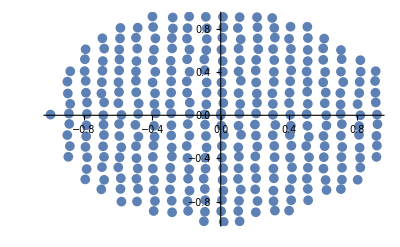

```mathematica
ListPlot[   uniformdisk[  {0,0},1,.1],  PlotMarkers->{Automatic, Medium}  ]
```

```mathematica
(*toLineΓKKΓ0[Nb_]:=Module[ {M = IntegerPart[Sqrt@Nb],ki=my,kf=mx},  Table[ ki+t(kf-ki),{t,0,1,1/M}]    ] ;*)
```

```mathematica
toLineΓKKΓ0[M_]:=Module[ {ki=my,kf=mx},  Table[ ki+t(kf-ki),{t,0,1,1/M}]    ] ;

toLineΓKMΓ[M_]:=Module[ {ks,Ne,Δt},(* 1: Γ=0, 2: K=(1/3,2/3), 3: K'=(2/3,3/3), 4: Γ=0,  *)
ks={ Γpoint,Kpoint,MPpoint,Γpoint }; 
Ne=Length[ks]-1; (* number of edges making the path in the BZ*) 
Flatten[ Table[ Table[ ks[[i]]+t(  ks[[i+1]]-ks[[i]]  ),{t,0,1-Ne/M(1-KroneckerDelta[i,Ne]),Ne/M}],{i,1,Ne}],1]
    ] ;
```

```mathematica
toLineΓKMΓ[M_]:=Module[ {ks,Ne,Δt},(* 1: Γ=0, 2: K=(1/3,2/3), 3: K'=(2/3,3/3), 4: Γ=0,  *)
ks={ Γpoint,Kpoint,MPpoint,Γpoint }; 
Ne=Length[ks]-1; (* number of edges making the path in the BZ*) 
Flatten[ Table[ Table[ ks[[i]]+t(  ks[[i+1]]-ks[[i]]  ),{t,Ne/M(1-KroneckerDelta[i,1]),1,Ne/M}],{i,1,Ne}],1]
    ] ;
```

```mathematica
toLineΓKMΓKMM[M_]:=Module[ {ks,Ne,Δt},(* 1: Γ=0, 2: K=(1/3,2/3), 3: K'=(2/3,3/3), 4: Γ=0,  *)
ks={ Γpoint,KPpoint,MPpoint,Γpoint,Kpoint,Mpoint,MPPpoint }; 
Ne=Length[ks]-1; (* number of edges making the path in the BZ*) 
Flatten[ Table[ Table[ ks[[i]]+t(  ks[[i+1]]-ks[[i]]  ),{t,Ne/M(1-KroneckerDelta[i,1]),1,Ne/M}],{i,1,Ne}],1]
    ] ;
```

#### old matrices

```mathematica
(*Hx[J_,K_,Γ_,h_,χ_,ω_]:={{0,0,0,0,-K χ[[1,2,2]]+Γ (-χ[[1,3,4]]-χ[[1, 4,3]])+J (-χ[[1, 2,2]]-χ[[1, 3,3]]-χ[[1, 4,4]]),J χ[[1, 2,1]]+K χ[[1, 2,1]],J χ[[1, 3,1]],J χ[[1, 4,1]]},
{0,0,0,0,J χ[[1, 1,2]]+K χ[[1, 1,2]],-J χ[[1, 1,1]]-K χ[[1, 1,1]],0,0},
{0,0,0,0,Γ χ[[1, 4,1]]+J χ[[1, 1,3]],0,-J χ[[2, 1,1]],Γ χ[[1, 1,1]]},
{0,0,0,0,Γ χ[[1, 3,1]]+J χ[[1, 1,4]],0,Γ χ[[1, 1,1]],-J χ[[1, 1,1]]},
{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}};
Hy[J_,K_,Γ_,h_,χ_,ω_]:={{0,0,0,0,-K χ[[2, 3,3]]+Γ (-χ[[2, 2,4]]-χ[[2, 4,2]])+J (-χ[[2, 2,2]]-χ[[2, 3,3]]-χ[[2, 4,4]]),J χ[[2, 2,1]],J χ[[2, 3,1]]+K χ[[2, 3,1]],J χ[[2, 4,1]]},
{0,0,0,0,J χ[[2, 1,2]]+Γ χ[[2, 4,1]],-J χ[[2, 1,1]],0,Γ χ[[2, 1,1]]},
{0,0,0,0,J χ[[2, 1,3]]+K χ[[2, 1,3]],0,-J χ[[2, 1,1]]-K χ[[2, 1,1]],0},
{0,0,0,0,Γ χ[[2, 2,1]]+J χ[[2, 1,4]],Γ χ[[2, 1,1]],0,-J χ[[2, 1,1]]},
{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}};
Hz[J_,K_,Γ_,h_,χ_,ω_,η_]:=
{{0,0,0,0,                
  Γ(-χ[[3, 2,3]]-χ[[3, 3,2]])+J(-χ[[3, 2,2]]-χ[[3, 3,3]]-χ[[3, 4,4]])-K χ[[3, 4,4]],J χ[[3, 2,1]],J χ[[3, 3,1]],J χ[[3, 4,1]]+K χ[[3, 4,1]]},
{-heffM0[J,K,Γ,h,ω, 2][[1]] + η heffM[J,K,Γ,h,ω, 2][[1]],0,η heffM[J,K,Γ,h,ω, 2][[3]],0,        J χ[[3, 1,2]]+Γ χ[[3, 3,1]],-J χ[[3, 1,1]],Γ χ[[3, 1,1]],0},
{-heffM0[J,K,Γ,h,ω, 2][[2]] + η heffM[J,K,Γ,h,ω, 2][[2]],0,0,η heffM[J,K,Γ,h,ω, 2][[1]],        J χ[[3, 1,3]]+Γ χ[[3, 2,1]],Γ χ[[3, 1,1]],-J χ[[3, 1,1]], 0},
{-heffM0[J,K,Γ,h,ω, 2][[3]] + η heffM[J,K,Γ,h,ω, 2][[3]],η heffM[J,K,Γ,h,ω, 2][[2]],0,0,        J χ[[3, 1,4]]+K χ[[3, 1,4]],0,0,-J χ[[3, 1,1]]-K χ[[3, 1,1]]},
{0,0,0,0,0,0,0,0},
{0,0,0,0,-heffM0[J,K,Γ,h,ω, 1][[1]] + η heffM[J,K,Γ,h,ω, 1][[1]],0,η heffM[J,K,Γ,h,ω, 1][[3]],0},
{0,0,0,0,-heffM0[J,K,Γ,h,ω, 1][[2]] + η heffM[J,K,Γ,h,ω, 1][[2]],0,0,η heffM[J,K,Γ,h,ω, 1][[1]] },
{0,0,0,0,-heffM0[J,K,Γ,h,ω, 1][[3]] + η heffM[J,K,Γ,h,ω, 1][[3]], η heffM[J,K,Γ,h,ω, 1][[2]],0,0}};*)
```

#### HMF

```mathematica
(*					
HMFk0[J_,K_,Γ_,h_,χ_,ω_,η_ ,k_] := 
Module[{hx,hy,hz, kx,ky},kx=k.nx;hx=Hx[J,K,Γ,h,χ,ω]; hy=Hy[J,K,Γ,h,χ,ω];hz=Hz[J,K,Γ,h,χ,ω,η];ky=k.ny; ⅈ(hx+hxᵀ) Exp[ⅈ kx]+ⅈ (hy+hyᵀ)Exp[ⅈ ky]+ⅈ (hz+hzᵀ)];
*)
HMFk[J_,K_,Γ_,h_,χ_,ω_,η_, k_] := 
Module[{hx,hy,hz,kx,ky,H},
kx=k . nx;hx=Hx[J,K,Γ,h,χ,ω]; hy=Hy[J,K,Γ,h,χ,ω];hz=Hz[J,K,Γ,h,χ,ω,η];ky=k . ny; H=I(hx) Exp[I kx]+I (hy)Exp[I ky]+I(hz); N@(H+H† ) ];

Tk=KroneckerProduct[ {{1,1},{I,-I}}, SparseArray[{Band[{1,1}]-> {1,1,1,1}},{4,4}] ]; 
UmatK[H_]:= Module[ {R=Quiet@Eigensystem@N[H]},ReverseSort[Rᵀ]ᵀ[[2]]ᵀ ];
(*EandU[H_]:= Module[ {R=Transpose@ReverseSort@Transpose@Quiet@Eigensystem@N[H]},{R[[1]],R⟦2⟧ᵀ }];*)

(*need a loop to sum over all k values*)
MFparK[J_,K_,Γ_,h_,η_, χ0_,ω0_,L_]:=Module[ { Nc=L^2,u,ux,uy,uz,χ=Array[Null,3],ω=Array[Null,2]},
u=Total@Table[ Module[{H,Hr,U,TU,TUh,k,uu},
k=toMomentum[l,Nc];
H=HMFk[J,K,Γ,h,χ0,ω0,η, k];Hr=Tk† . H . Tk; U=UmatK[Hr];
TU=Tk . U;TUh=TU[[;;,-4;;-1]];uu=(1/Nc)Chop[I TUh . TUh† ];uu=(uu-Transpose[uu])/2;
{uu Exp[I k . nx],uu Exp[I k . ny],uu }  ],{l,1,Nc}]; 
χ[[1]]=Table[ u[[1]][[β+4,α]]   ,  {α,1,4},{β,1,4} ];
χ[[2]]=Table[ u[[2]][[β+4,α]]   ,  {α,1,4},{β,1,4} ];
χ[[3]]=Table[ u[[3]][[β+4,α]]   ,  {α,1,4},{β,1,4} ];
ω[[1]]=Table[ u[[3]][[β,α]]     ,  {α,1,4},{β,1,4} ];
ω[[2]]=Table[ u[[3]][[β+4,α+4]] ,  {α,1,4},{β,1,4} ];
{χ[[1]],χ[[2]],χ[[3]],ω[[1]],ω[[2]]}
];
```

```mathematica
(*
(*spin-spin correlation*)
ssCk[χ_,ω_,r_,L_]:=Table[ ω[[1, α+1,0+1]]   ω[[2,β+1,0+1]]   - χ[[γ, α+1,β+1]] χ[[γ, 0+1,0+1]]  +  χ[[γ, α+1,0+1]] χ[[γ,0+1,β+1]]
,{γ,1,3}, {α,1,3},{β,1,3}];

χGx = {{0.5248657458506312014761390306,0,0,0},{0,-1,0,0},{0,0,0,0},{0,0,0,0}};χGy = {{0.5248657458506312014761390306,0,0,0},{0,0,0,0},{0,0,-1,0},{0,0,0,0}};χGz = {{0.5248657458506312014761390306,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,-1}};
ωGA =  ⅈ IdentityMatrix[4];ωGB =  ⅈ IdentityMatrix[4];
χGP= {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}};
ωGP[h_] :=  {{ⅈ,h[[1]],h[[2]],h[[3]]},{-h[[1]],ⅈ,h[[3]],-h[[2]]},{-h[[2]],-h[[3]],ⅈ,h[[1]]},{-h[[3]],h[[2]],-h[[1]],ⅈ}};
*)
```

```mathematica
χGx = {{0.5248657458506312014761390306,0,0,0},{0,-1,0,0},{0,0,0,0},{0,0,0,0}};χGy = {{0.5248657458506312014761390306,0,0,0},{0,0,0,0},{0,0,-1,0},{0,0,0,0}};χGz = {{0.5248657458506312014761390306,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,-1}};
ωGA = {{ⅈ,0,0,0},{0.000001,ⅈ,0,0},{0.000001,0,ⅈ,0},{0.000001,0,0,ⅈ}};ωGB = ωGA;
```

#### Auxiliary matrices for the Hamiltonian [8x8 matrices]

```mathematica
Hx[J_,K_,Γ_,h_,χ_,ω_]:={
{0,0,0,0,-K χ[[1,2,2]],K χ[[1, 2,1]],0,0},
{0,0,0,0, K χ[[1, 1,2]],-K χ[[1, 1,1]],0,0},
{0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}+{
{0,0,0,0,J (-χ[[1, 2,2]]-χ[[1, 3,3]]-χ[[1, 4,4]]),J χ[[1, 2,1]],J χ[[1, 3,1]],J χ[[1, 4,1]]},
{0,0,0,0,J χ[[1, 1,2]],-J χ[[1, 1,1]],0,0},
{0,0,0,0,J χ[[1, 1,3]],0,-J χ[[1, 1,1]],0},
{0,0,0,0,J χ[[1, 1,4]],0,0,-J χ[[1, 1,1]]},
{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}+{
{0,0,0,0,Γ (-χ[[1,3,4]]-χ[[1, 4,3]]),0,Γ χ[[1, 4,1]],Γ χ[[1, 3,1]]},
{0,0,0,0,0,0,0,0},
{0,0,0,0,Γ χ[[1, 1,4]],0,0,Γ χ[[1, 1,1]]},
{0,0,0,0,Γ χ[[1, 1,3]],0,Γ χ[[1, 1,1]],0},
{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}; 
Hy[J_,K_,Γ_,h_,χ_,ω_]:={
{0,0,0,0,-K χ[[2, 3,3]],0,K χ[[2, 3,1]],0},
{0,0,0,0,0,0,0,0},
{0,0,0,0,K χ[[2, 1,3]],0,-K χ[[2, 1,1]],0},
{0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}+{
{0,0,0,0,J (-χ[[2, 2,2]]-χ[[2, 3,3]]-χ[[2, 4,4]]),J χ[[2, 2,1]],J χ[[2, 3,1]],J χ[[2, 4,1]]},
{0,0,0,0,J χ[[2, 1,2]],-J χ[[2, 1,1]],0,0},
{0,0,0,0,J χ[[2, 1,3]],0,-J χ[[2, 1,1]],0},
{0,0,0,0,J χ[[2, 1,4]],0,0,-J χ[[2, 1,1]]},
{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}+{
{0,0,0,0,Γ (-χ[[2, 2,4]]-χ[[2, 4,2]]),Γ χ[[2, 4,1]],0,Γ χ[[2, 2,1]]},
{0,0,0,0,Γ χ[[2, 1,4]],0,0,Γ χ[[2, 1,1]]},
{0,0,0,0,0,0,0,0},
{0,0,0,0,Γ χ[[2, 1,2]],Γ χ[[2, 1,1]],0,0},
{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}};

Hz[J_,K_,Γ_,h_,χ_,ω_,η_]:=Module[{λ1,λ2,m,δω},
δω=Table[{ ω⟦σ,2,1⟧-ω⟦σ,3,4⟧,ω⟦σ,3,1⟧-ω⟦σ,4,2⟧,ω⟦σ,4,1⟧-ω⟦σ,2,3⟧}  ,{σ,1,2}]+I 10^-9.9;
m=Table[ ω⟦σ,2,1⟧ω⟦σ,3,4⟧+ω⟦σ,3,1⟧ω⟦σ,4,2⟧+ω⟦σ,4,1⟧ω⟦σ,2,3⟧ +1 ,{σ,1,2}];
λ2=Re@Table[{ω⟦σ,2,1⟧/δω⟦σ,1⟧,ω⟦σ,3,1⟧/δω⟦σ,2⟧,ω⟦σ,4,1⟧/δω⟦σ,3⟧ },{σ,1,2}];λ1=Re@Table[{(-ω⟦σ,3,4⟧)/δω⟦σ,1⟧,(-ω⟦σ,4,2⟧)/δω⟦σ,2⟧,(-ω⟦σ,2,3⟧)/δω⟦σ,3⟧},{σ,1,2}];
{
{0,0,0,0,         -K χ[[3, 4,4]],0,0, K χ[[3, 4,1]]    },
{0,0,0,0,         0,0,0,0   },
{0,0,0,0,         0,0,0,0   },
{0,0,0,0,         K χ[[3, 1,4]],0,0,-K χ[[3, 1,1]]  },
{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}+{
{0,0,0,0,         J(-χ[[3, 2,2]]-χ[[3, 3,3]]-χ[[3, 4,4]]),J χ[[3, 2,1]],J χ[[3, 3,1]],J χ[[3, 4,1]]    },
{0,0,0,0,         J χ[[3, 1,2]],-J χ[[3, 1,1]],0,0   },
{0,0,0,0,         J χ[[3, 1,3]],0,-J χ[[3, 1,1]], 0  },
{0,0,0,0,         J χ[[3, 1,4]],0,0,-J χ[[3, 1,1]]  },
{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}+{
{0,0,0,0,         Γ(-χ[[3, 2,3]]-χ[[3, 3,2]]),Γ χ[[3, 3,1]],Γ χ[[3, 2,1]],0   },
{0,0,0,0,         Γ χ[[3, 1,3]],0,Γ χ[[3, 1,1]],0   },
{0,0,0,0,         Γ χ[[3, 1,2]],Γ χ[[3, 1,1]],0, 0  },
{0,0,0,0,         0,0,0,0  },
{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}+{
{0,0,0,0,             0,0,0,0 },
{-heffM0[J,K,Γ,h,ω, 2][[1]] + λ1[[2,1]] heffM[J,K,Γ,h,ω, 2][[1]],0, λ2[[2,3]] heffM[J,K,Γ,h,ω, 2][[3]],0,         0,0,0,0   },
{-heffM0[J,K,Γ,h,ω, 2][[2]] + λ1[[2,2]] heffM[J,K,Γ,h,ω, 2][[2]],0,0,λ2[[2,1]]  heffM[J,K,Γ,h,ω, 2][[1]],         0,0,0,0   },
{-heffM0[J,K,Γ,h,ω, 2][[3]] + λ1[[2,3]]heffM[J,K,Γ,h,ω, 2][[3]],λ2[[2,2]] heffM[J,K,Γ,h,ω, 2][[2]],0,0,         0,0,0,0   },
{0,0,0,0,0,0,0,0},
{0,0,0,0,-heffM0[J,K,Γ,h,ω, 1][[1]] + λ1[[1,1]] heffM[J,K,Γ,h,ω, 1][[1]],0, λ2[[1,3]] heffM[J,K,Γ,h,ω, 1][[3]],0},
{0,0,0,0,-heffM0[J,K,Γ,h,ω, 1][[2]] + λ1[[1,2]]heffM[J,K,Γ,h,ω, 1][[2]],0,0, λ2[[1,1]] heffM[J,K,Γ,h,ω, 1][[1]] },
{0,0,0,0,-heffM0[J,K,Γ,h,ω, 1][[3]] + λ1[[1,3]]heffM[J,K,Γ,h,ω, 1][[3]], λ2[[1,2]]heffM[J,K,Γ,h,ω, 1][[2]],0,0} }];
```

#### heff momentum

```mathematica
heffM0[J_,K_,Γ_,h_,ω_,σ_]:={ 
h[[1]] -  K ω[[σ, 2,1]]-3J ω[[σ, 2,1]] -2Γ (ω[[σ, 3,1]] +ω[[σ, 4,1]]), 
h[[2]] -  K ω[[σ, 3,1]]-3 J ω[[σ, 3,1]]-2Γ (ω[[σ, 2,1]] +ω[[σ, 4,1]]), 
h[[3]] -  K ω[[σ, 4,1]]-3 J ω[[σ, 4,1]]-2Γ (ω[[σ, 2,1]] +ω[[σ, 3,1]])};
heffM[J_,K_,Γ_,h_,ω_,σ_]:=heffM0[J,K,Γ,h,ω,σ];
ωGA = {{ⅈ,0.000001,0.000001,0.000001},{-0.000001,ⅈ,0.000001,-0.000001},{-0.000001,-0.000001,ⅈ,0.000001},{-0.000001,0.000001,-0.000001,ⅈ}}; ωGB = ωGA;
```

#### definitions for dispersion

```mathematica
Energies[Nb_, J_,K_, Γ_, h_,χ_,ω_,η_] :=  Table[  N@ {   toMomentum[n,Nb], Chop@Sort[Eigenvalues[ N@HMFk[ J,K, Γ, h,χ,ω,η,toMomentum[n,Nb]]  ]]    }     , {n,1,Nb}] ;
```

```mathematica
dispersion[E_,Nb_]:= Transpose[    Table[  Flatten[{ E⟦i⟧⟦1⟧ , E⟦i⟧⟦2⟧⟦j⟧}] , {j,1,8}       , {i,1,Nb}]  ];
```

Instead of 3D plotting we can do a 2D plot like Fig.2 of Knolle et. al.   Define a path in k space that passes through the two Dirac points. 		A line:

```mathematica
toLineInMomentumSpace[Nb_]:= If[FractionalPart[Sqrt@Nb] ≠ 0, Print["Nb=",Nb,", should a perfect square."];Abort[],	Module[ {M = IntegerPart[Sqrt@Nb],ki=my,kf=mx},  Table[ ki+t(kf-ki),{t,0,1,1/M}]    ]   ];
```

```mathematica
Energiesline[Nb_, J_,K_, Γ_, h_,χ_,ω_,η_] :=Module[ {M = IntegerPart[Sqrt@Nb],line = toLineInMomentumSpace[Nb]},    Table[  N@ {   line⟦n⟧, Chop@Sort[Eigenvalues[ N@HMFk[ J,K, Γ, h,χ,ω,η, line⟦n⟧], 8 ]]    }     , {n,1,M}] ];
EnergieslinePositive[Nb_, J_,K_, Γ_, h_,χ_,ω_,η_] :=Module[ {M = IntegerPart[Sqrt@Nb],line = toLineInMomentumSpace[Nb]},   Table[  N@ {    line⟦n⟧   , Sort@Chop@Eigenvalues[ N@HMFk[  J,K, Γ, h,χ,ω,η,line⟦n⟧] , 4, Method->{"FEAST","Interval"->{- 10^-9,10}, "Tolerance"-> 10^-10}    ]    }     , {n,1,M}] ];
lineDispersion[E_,Nb_]:=Module[ {M = IntegerPart[Sqrt@Nb]},    Table[  { (i -1-M)/2  , E⟦i⟧⟦2⟧⟦j⟧ }, {j,1,8}       , {i,1,M} ]  ]
```

I want to output a list { {weight,energy},...} for each energy and sorted by weight  -- if weight is negative, then it has more weight of type-c fermions.
	Want a average of the abs values weighted -1 for c and +1 for b-fermions ( c  has 3x more weight).
	Note that  Sum[Abs[ES⟦i,2,a⟧]^2, {a,1,8}] = Norm[ ES⟦i,2⟧ ] = 1

```mathematica
cutNegativeEV[es_]:= Module[ {ES=Sort@Transpose[es]},  ES⟦5;;8⟧      ];
```

```mathematica
weightSort[es_] := Module[ {ES=es,weight, En},
En=Table[ { -4 Abs[ES⟦i,2,1⟧]^2 -4 Abs[ES⟦i,2,5⟧]^2 + 1,ES⟦i,1⟧ }, {i,1,Length[es]}];
Sort[En]];
```

```mathematica
EnergiesSortedW[Nb_, J_,K_, Γ_, h_,χ_,ω_,η_] :=  Module[ {M = IntegerPart[Sqrt@Nb],line = toLineInMomentumSpace[Nb]},Table[Chop@weightSort@cutNegativeEV[Eigensystem@N@HMFk[J,K,Γ,h,χ,ω,η,line⟦i⟧]]  , {i,1,M}]      ];
lineDispersionSortedW[E_]:=Module[ {M = Length[E]},    Table[  { i -1-M/2  , E⟦i⟧⟦j,2⟧ }, {j,1,4}       , {i,1,M} ]  ];
colorW[E_]:=Module[ {M = Length[E]},    Table[   E⟦i⟧⟦j,1⟧ , {j,1,4}       , {i,1,M} ]  ];
```

```mathematica
colorWscaled[E_]:=Module[ {M = Length[E], color=colorW[E]},    Table[   Rescale[    color⟦j,i⟧ ,{Min@color,Max@color}], {j,1,4}       , {i,1,M} ]  ];
colorWFunction[E_,a_]:= Function[{x,y},Module[ {M = Length[E], color=colorWscaled[E]},ColorData["Rainbow"][ color⟦a,Round[x+1+M/2]⟧   ]     ]  ];
```

```mathematica
energyGap[Nb_, J_,K_, Γ_, h_,χ_,ω_,η_] :=Module[ {energies},  energies= Sort[Abs/@Eigenvalues[ Chop@N@HMFk[ J,K, Γ, h,χ,ω,η, N@kD1], 8 ]]; energies⟦1⟧]
```

```mathematica
(*size=0.005;
Module[ {Γ,J,K,L=Ls[[1]],Nc,h,χ,ω,η=0.45 ,χ0,ω0 ,title, color, j0, L0, EnList0}, 

(*{j0,L0,χ0,ω0,EnList0}= loadData[toPath[parameters[[1]],L,acuracy]][[-1]];Nc = 180^2;*)
{J,K,Γ,h}=parameters[[1,1]][[1;;4]];
 Nc=L^2;
{χ,ω}={χG,ωG};
Nc=6^2 Nc;
En = EnergiesSortedW[Nc, J,K, Γ, h,χ,ω,η] ;
 Disp = lineDispersionSortedW[En];
cFun={colorWFunction[En,1],colorWFunction[En,2],colorWFunction[En,3],colorWFunction[En,4]};

title=StringReplace["J = X1, K = X2, \\Gamma = X3, \\mathbf{h} =  X4 \\, \\mathbf{c}",{"X1"-> ToString[J],"X2"-> ToString[K],"X3"-> ToString[Γ] ,"X4"-> ToString[Norm@h] ,"X5"-> ToString[η]   }] ;

Show[ ListPlot[ Disp⟦1⟧ ,PlotStyle->PointSize[size], Joined->False ,  PlotRange-> {0,1.61} , FrameLabel->{MaTeX[" ",Magnification->2] , MaTeX["E(\\mathbf{k})",Magnification->2] } ,ColorFunction-> colorWFunction[En,1],ColorFunctionScaling->False  , Frame->True ,   FrameStyle ->Directive[Black,20], FrameTicksStyle->Directive[Black,15],ImageSize->800, GridLines->Automatic,  PlotLabel-> Style[MaTeX[title,Magnification->2] ,20 ,Black ],  FrameTicks->{{ } , Automatic}(*
PlotLegends->BarLegend["Rainbow",LegendFunction->"Panel",LegendMargins->0,LabelStyle->Directive[Black,FontSize-> 18,FontFamily->"Helvetica"], LegendLabel->Placed[ MaTeX["0 \\to c, \\qquad \\qquad 1 \\to b ",Magnification->2] ,Left,Rotate[#,90Degree]&]   ],*)  ],
ListPlot[ Disp⟦2⟧ ,PlotStyle->PointSize[size], Joined->False , ColorFunction-> colorWFunction[En,2],ColorFunctionScaling->False  ] ,
ListPlot[ Disp⟦3⟧ ,PlotStyle->PointSize[size] , Joined->False , ColorFunction-> colorWFunction[En,3],ColorFunctionScaling->False ] ,
ListPlot[ Disp⟦4⟧ ,PlotStyle->PointSize[size], Joined->False , ColorFunction-> colorWFunction[En,4],ColorFunctionScaling->False ] 
]

]*)
```

```mathematica
(*
size=0.005;
Module[ {Γ,J,K,L=Ls[[1]],Nc,h,χ,ω,η=0.45 ,χ0,ω0 ,title, color, j0, L0, EnList0}, 

(*{j0,L0,χ0,ω0,EnList0}= loadData[toPath[parameters[[1]],L,acuracy]][[-1]];Nc = 180^2;*)
{J,K,Γ,h}=parameters[[1,1]][[1;;4]];
 Nc=L^2;
{χ,ω}={χG,ωG};
Nc=6^2 Nc;
En = EnergiesSortedW[Nc, J,K, Γ, h,χ,ω,η] ;
 Disp = lineDispersionSortedW[En];
cFun={colorWFunction[En,1],colorWFunction[En,2],colorWFunction[En,3],colorWFunction[En,4]};
(*
title=StringReplace["J = X1, K = X2, \\Gamma = X3, \\mathbf{h} =  X4 \\, \\mathbf{c}",{"X1"-> ToString[J],"X2"-> ToString[K],"X3"-> ToString[Γ] ,"X4"-> ToString[Norm@h] ,"X5"-> ToString[η]   }] ;

Show[ ListPlot[ Disp⟦1⟧ ,PlotStyle->PointSize[size], Joined->False ,  PlotRange-> {0,1.61} , FrameLabel->{MaTeX[" ",Magnification->2] , MaTeX["E(\\mathbf{k})",Magnification->2] } ,ColorFunction-> colorWFunction[En,1],ColorFunctionScaling->False  , Frame->True ,   FrameStyle ->Directive[Black,20], FrameTicksStyle->Directive[Black,15],ImageSize->800, GridLines->Automatic,  PlotLabel-> Style[MaTeX[title,Magnification->2] ,20 ,Black ],  FrameTicks->{{ } , Automatic}(*
PlotLegends->BarLegend["Rainbow",LegendFunction->"Panel",LegendMargins->0,LabelStyle->Directive[Black,FontSize-> 18,FontFamily->"Helvetica"], LegendLabel->Placed[ MaTeX["0 \\to c, \\qquad \\qquad 1 \\to b ",Magnification->2] ,Left,Rotate[#,90Degree]&]   ],*)  ],
ListPlot[ Disp⟦2⟧ ,PlotStyle->PointSize[size], Joined->False , ColorFunction-> colorWFunction[En,2],ColorFunctionScaling->False  ] ,
ListPlot[ Disp⟦3⟧ ,PlotStyle->PointSize[size] , Joined->False , ColorFunction-> colorWFunction[En,3],ColorFunctionScaling->False ] ,
ListPlot[ Disp⟦4⟧ ,PlotStyle->PointSize[size], Joined->False , ColorFunction-> colorWFunction[En,4],ColorFunctionScaling->False ] 
]
*)
]
*)
```

### Momentum def SO(4)

#### momentum

```mathematica
mx= 2π {1 , 1/Sqrt[3]}; my= 2π {-1 , 1/Sqrt[3]};
(*toMomentum[n_,Nb_]:= If[FractionalPart[Sqrt@Nb] ≠ 0, Print["Nb=",Nb,", is not a perfect square."];Abort[],
				Module[ {L = IntegerPart[Sqrt@Nb],p1,p2},  p1 =  Mod[n-1,L]+1; p2 =   (n-p1)/L+1;   mxp1/L +myp2/L]
];*)
toMomentum[n_,Nb_]:= Module[ {L = IntegerPart[Sqrt@Nb],p1,p2},  p1 =  Mod[n,L,1]; p2 =   (n-p1)/L+1;   mx p1/L +my p2/L];
toMomentumTable[L_]:=Table[Module[{p1,p2},p1=Mod[n,L,1];p2=(n-p1)/L+1;{(2(p1-p2)π)/L,(2 (p1+p2) π)/(Sqrt[3] L)}],{n,1,L^2}];
toMomentumInverse[k_,Nb_]:= If[FractionalPart[Sqrt@Nb] != 0, Print["Nb=",Nb,", is not a perfect square."];Abort[],    
Module[ {M = IntegerPart[Sqrt@Nb],p1,p2},   p1=k . nx M/(2π); p2=k . ny M/(2π);  Round[p1 + (p2-1)M ]  ]];
kD2=1/3 mx+2/3 my;
kD1=2/3 mx+1/3 my;
Γpoint={0,0};
Kpoint=2/3 mx+1/3 my;
KPpoint=1/3 mx+2/3 my;
Mpoint=1/2 (Kpoint+KPpoint);
MPpoint=1/2 (Kpoint-mx+KPpoint);
MPPpoint=1/2 (Kpoint+KPpoint-my);
```

```mathematica
(*toLineΓKKΓ0[Nb_]:=Module[ {M = IntegerPart[Sqrt@Nb],ki=my,kf=mx},  Table[ ki+t(kf-ki),{t,0,1,1/M}]    ] ;*)
```

```mathematica
toLineΓKKΓ0[M_]:=Module[ {ki=my,kf=mx},  Table[ ki+t(kf-ki),{t,0,1,1/M}]    ] ;

toLineΓKMΓ[M_]:=Module[ {ks,Ne,Δt},(* 1: Γ=0, 2: K=(1/3,2/3), 3: K'=(2/3,3/3), 4: Γ=0,  *)
ks={ Γpoint,Kpoint,MPpoint,Γpoint }; 
Ne=Length[ks]-1; (* number of edges making the path in the BZ*) 
Flatten[ Table[ Table[ ks[[i]]+t(  ks[[i+1]]-ks[[i]]  ),{t,0,1-Ne/M(1-KroneckerDelta[i,Ne]),Ne/M}],{i,1,Ne}],1]
    ] ;
```

```mathematica
toLineΓKMΓ[M_]:=Module[ {ks,Ne,Δt},(* 1: Γ=0, 2: K=(1/3,2/3), 3: K'=(2/3,3/3), 4: Γ=0,  *)
ks={ Γpoint,Kpoint,MPpoint,Γpoint }; 
Ne=Length[ks]-1; (* number of edges making the path in the BZ*) 
Flatten[ Table[ Table[ ks[[i]]+t(  ks[[i+1]]-ks[[i]]  ),{t,Ne/M(1-KroneckerDelta[i,1]),1,Ne/M}],{i,1,Ne}],1]
    ] ;
```

```mathematica
toLineΓKMΓKMM[M_]:=Module[ {ks,Ne,Δt},(* 1: Γ=0, 2: K=(1/3,2/3), 3: K'=(2/3,3/3), 4: Γ=0,  *)
ks={ Γpoint,KPpoint,MPpoint,Γpoint,Kpoint,Mpoint,MPPpoint }; 
Ne=Length[ks]-1; (* number of edges making the path in the BZ*) 
Flatten[ Table[ Table[ ks[[i]]+t(  ks[[i+1]]-ks[[i]]  ),{t,Ne/M(1-KroneckerDelta[i,1]),1,Ne/M}],{i,1,Ne}],1]
    ] ;
```

#### HMF

```mathematica
(*Gmat=  {KroneckerProduct[  PauliMatrix[0],-ⅈ PauliMatrix[2] ],KroneckerProduct[- ⅈ PauliMatrix[2],PauliMatrix[3] ],KroneckerProduct[-ⅈ PauliMatrix[2],  PauliMatrix[1] ]};
Mmat=  {KroneckerProduct[  PauliMatrix[3],ⅈ PauliMatrix[2] ],KroneckerProduct[ ⅈ PauliMatrix[2],PauliMatrix[0] ],KroneckerProduct[  PauliMatrix[1],ⅈ PauliMatrix[2] ]};
Nmat=(Mmat-Gmat)/2;
mx= 2π {1 , 1/Sqrt[3]}; my= 2π {-1 , 1/Sqrt[3]};
toMomentumTable[L_]:=N@Table[Module[{p1,p2},p1=Mod[n,L];p2=(n-p1)/L;{(2(p1-p2)π)/L,(2 (p1+p2) π)/(Sqrt[3] L)}],{n,0,L^2-1}];
(*toMomentumTable[L_]:=N@Table[Module[{p1,p2},p1=Mod[n,L,1];p2=(n-p1)/L+1;{(2(p1-p2)π)/L,(2 (p1+p2) π)/(Sqrt[3] L)}],{n,1,L^2}];*)
Jmat[J_,K_,G_,Gp_]:={
{{J[[1]]+K[[1]],Gp[[1]],Gp[[1]]},{Gp[[1]],J[[1]],G[[1]]},{Gp[[1]],G[[1]],J[[1]]}},
{{J[[2]],Gp[[2]],G[[2]]},{Gp[[2]],J[[2]]+K[[2]],Gp[[2]]},{G[[2]],Gp[[2]],J[[2]]}},
{{J[[3]],G[[3]],Gp[[3]]},{G[[3]],J[[3]],Gp[[3]]},{Gp[[3]],Gp[[3]],J[[3]]+K[[3]]}}   };
(*ClearAll[J,K,Γ,ωx,ωy,ωz]; 
jmat=Jmat[J{1,1,1},K{1,1,1},Γ{1,1,1},0{1,1,1} ];
ωmat=Sum[Gmat[[γ]] {ωx,ωy,ωz}[[γ]],{γ,1,3}];
{MatrixForm/@ jmat,MatrixForm@ ωmat}
MatrixForm@FullSimplify@Sum[ jmat[[γ]].{ωx,ωy,ωz} , {γ,1,3}]*)
(*Tk=KroneckerProduct[ {{1,1},{I,-I}}, SparseArray[{Band[{1,1}]-> {1,1,1,1}},{4,4}] ]; *)
Tmom[k_]:=Module[{kx=k.mx,ky=k.my},{{1,0,0,0,1,0,0,0},{0,1,0,0,0,1,0,0},{0,0,1,0,0,0,1,0},{0,0,0,1,0,0,0,1},{ⅈ,0,0,0,-ⅈ,0,0,0},{0,ⅈ ⅇ^(ⅈ kx),0,0,0,-ⅈ ⅇ^(ⅈ kx),0,0},{0,0,ⅈ ⅇ^(ⅈ ky),0,0,0,-ⅈ ⅇ^(ⅈ ky),0},{0,0,0,ⅈ,0,0,0,-ⅈ}}];
matrix inner product
AMF[Jm_,U_]:=Module[{AMF,M=2Nmat},  AMF=Table[    Sum[   1/2 Jm[[γ]][[α,β]] M[[α]].U[[γ]].M[[β]] ,{α,1,3},{β,1,3}]    ,{γ,1,3}];   KroneckerProduct[ {{0,1},{0,0}},#]&/@Re@AMF];
BMF[Jm_,h_,λ_,W_]:=Module[{Ba,Bb,M=Mmat,N=2Nmat,G=Gmat},
Ba=Sum[    Sum[   1/4  Jm[[γ]][[α,β]] N[[α]] Tr[W[[2]]^ᵀ.N[[β]] ],{α,1,3},{β,1,3}] - h[[γ]] M[[γ]] + λ[[1]][[γ]] G[[γ]]        ,{γ,1,3}];
Bb=Sum[    Sum[   1/4  Jm[[γ]][[α,β]] N[[α]] Tr[W[[1]]^ᵀ.N[[β]] ],{α,1,3},{β,1,3}] - h[[γ]] M[[γ]] + λ[[2]][[γ]] G[[γ]]         ,{γ,1,3}];
{KroneckerProduct[ {{1,0},{0,0}},Re@Ba],KroneckerProduct[ {{0,0},{0,1}},Re@Bb] }];
cMF[Jm_,U_,W_]:=Module[{M=2Nmat}, Sum[ 1/16  Jm[[γ]][[α,β]] (Tr[W[[1]]ᵀ.M[[α]] ] Tr[W[[2]]ᵀ.M[[β]]]+2  Tr[ U[[γ]]ᵀ. M[[α]].U[[γ]].M[[β]] ]   ),{α,1,3},{β,1,3},{γ,1,3}]          ];
enMF[Jm_,U_,W_,h_,λ_]:=Module[{M=Mmat,N=2Nmat,G=Gmat},    cMF[Jm,U,W] +1/4  Sum[   -h[[γ]] Tr[W[[σ]]ᵀ.M[[γ]] ] +λ[[σ,γ]] Tr[W[[σ]]ᵀ.G[[γ]] ]       ,{σ,1,2},{γ,1,3}]        ];
HmfMomentum[Jmatrice_,h_,λ_,U_,W_, k_] := 
Module[{Ax,Ay,Az,BA,BB, hx,hy,hz, kx,ky,ha,HA,HB}, kx=k . nx;ky=k . ny;
{Ax,Ay,Az}=ⅈ AMF[Jmatrice,U];  
ha=Exp[ ⅈ kx] Ax + Exp[ ⅈ ky] Ay + Az;
(*ha=Exp[I k.δx] Ax + Exp[I k.δy] Ay +Exp[I k.δz] Az;*)
HA=N@( ha+ConjugateTranspose@ha );
{BA,BB}= ⅈ BMF[Jmatrice,h,λ,W];
HB=BA+BB;
(HA+HB)   ];
(*mysort[list_]:=Module[ {sorted=Sort@list,half=⌊Length[list]/2⌋},  Join[ sorted[[half+1;;-1]], sorted[[half;;1;;-1]] ]  ];
UmatK[H_]:= Module[ {R=Eigensystem@N[H]},mysort[Rᵀ]ᵀ[[2]]ᵀ ];*)UmatK[H_]:= Module[ {R=Eigensystem@N[H]},ReverseSort[Rᵀ]ᵀ[[2]]ᵀ ];*)
```

```mathematica
(*iccK[icc_,k_]:=Module[{iccx,iccy},
iccx=KroneckerProduct[ {{0,1},{0,0}}, Exp[ⅈ k . nx] icc[[1;;4,5;;8]]    ]+KroneckerProduct[ {{0,0},{1,0}}, Exp[-ⅈ k . nx] icc[[5;;8,1;;4]]   ];
iccy=KroneckerProduct[ {{0,1},{0,0}}, Exp[ⅈ k . ny] icc[[1;;4,5;;8]]    ]+KroneckerProduct[ {{0,0},{1,0}}, Exp[-ⅈ k . ny] icc[[5;;8,1;;4]]   ];
N@{iccx ,iccy ,icc } ];*)
(*
parametersMomentum[Jm_,h_,λ_,UG_,WG_,L_]:=Module[ { Nc=L^2,mList,u,χ=Array[Null,3],ω=Array[Null,2]},
mList=toMomentumTable[L];
u=Total@Table[
 Module[{H,Hr,U,𝕌,𝕌less,k,icc,Tk=KroneckerProduct[ {{1,1},{I,-I}}, SparseArray[{Band[{1,1}]-> {1,1,1,1}},{4,4}] ];  },
k=mList[l];
H=N@HmfMomentum[Jm,h,λ,UG,WG, k];
Hr=Tk† . H . Tk; 
U=UmatK[Hr];
𝕌=Tk . U;
𝕌less=𝕌[[;;,1;;4]];
icc=(1/Nc)Chop[I 𝕌less . 𝕌less† ];
(*icc=(icc-Transpose[icc])/2;{icc Exp[I k . nx],icc Exp[I k . ny],icc }*)
iccK[icc,k]  ]
,{l,1,Nc}]; 
χ[[1]]=Table[ u[[1]][[α,β+4]]   ,  {α,1,4},{β,1,4} ];
χ[[2]]=Table[ u[[2]][[α,β+4]]   ,  {α,1,4},{β,1,4} ];
χ[[3]]=Table[ u[[3]][[α,β+4]]   ,  {α,1,4},{β,1,4} ];
ω[[1]]=Table[ u[[3]][[α,β]]          ,  {α,1,4},{β,1,4} ];
ω[[2]]=Table[ u[[3]][[α+4,β+4]] ,  {α,1,4},{β,1,4} ];
{χ[[1]],χ[[2]],χ[[3]],ω[[1]],ω[[2]]}
];*)
```

#### definitions for dispersion

```mathematica
Energies[Nb_, J_,K_, Γ_, h_,χ_,ω_,η_] :=  Table[  N@ {   toMomentum[n,Nb], Chop@Sort[Eigenvalues[ N@HMFk[ J,K, Γ, h,χ,ω,η,toMomentum[n,Nb]]  ]]    }     , {n,1,Nb}] ;
```

```mathematica
dispersion[E_,Nb_]:= Transpose[    Table[  Flatten[{ E⟦i⟧⟦1⟧ , E⟦i⟧⟦2⟧⟦j⟧}] , {j,1,8}       , {i,1,Nb}]  ];
```

Instead of 3D plotting we can do a 2D plot like Fig.2 of Knolle et. al.   Define a path in k space that passes through the two Dirac points. 		A line:

```mathematica
toLineInMomentumSpace[Nb_]:= If[FractionalPart[Sqrt@Nb] ≠ 0, Print["Nb=",Nb,", should a perfect square."];Abort[],	Module[ {M = IntegerPart[Sqrt@Nb],ki=my,kf=mx},  Table[ ki+t(kf-ki),{t,0,1,1/M}]    ]   ];
```

```mathematica
Energiesline[Nb_, J_,K_, Γ_, h_,χ_,ω_,η_] :=Module[ {M = IntegerPart[Sqrt@Nb],line = toLineInMomentumSpace[Nb]},    Table[  N@ {   line⟦n⟧, Chop@Sort[Eigenvalues[ N@HMFk[ J,K, Γ, h,χ,ω,η, line⟦n⟧], 8 ]]    }     , {n,1,M}] ];
EnergieslinePositive[Nb_, J_,K_, Γ_, h_,χ_,ω_,η_] :=Module[ {M = IntegerPart[Sqrt@Nb],line = toLineInMomentumSpace[Nb]},   Table[  N@ {    line⟦n⟧   , Sort@Chop@Eigenvalues[ N@HMFk[  J,K, Γ, h,χ,ω,η,line⟦n⟧] , 4, Method->{"FEAST","Interval"->{- 10^-9,10}, "Tolerance"-> 10^-10}    ]    }     , {n,1,M}] ];
lineDispersion[E_,Nb_]:=Module[ {M = IntegerPart[Sqrt@Nb]},    Table[  { (i -1-M)/2  , E⟦i⟧⟦2⟧⟦j⟧ }, {j,1,8}       , {i,1,M} ]  ]
```

I want to output a list { {weight,energy},...} for each energy and sorted by weight  -- if weight is negative, then it has more weight of type-c fermions.
	Want a average of the abs values weighted -1 for c and +1 for b-fermions ( c  has 3x more weight).
	Note that  Sum[Abs[ES⟦i,2,a⟧]^2, {a,1,8}] = Norm[ ES⟦i,2⟧ ] = 1

```mathematica
cutNegativeEV[es_]:= Module[ {ES=Sort@Transpose[es]},  ES⟦5;;8⟧      ];
```

```mathematica
weightSort[es_] := Module[ {ES=es,weight, En},
En=Table[ { -4 Abs[ES⟦i,2,1⟧]^2 -4 Abs[ES⟦i,2,5⟧]^2 + 1,ES⟦i,1⟧ }, {i,1,Length[es]}];
Sort[En]];
```

```mathematica
EnergiesSortedW[Nb_, J_,K_, Γ_, h_,χ_,ω_,η_] :=  Module[ {M = IntegerPart[Sqrt@Nb],line = toLineInMomentumSpace[Nb]},Table[Chop@weightSort@cutNegativeEV[Eigensystem@N@HMFk[J,K,Γ,h,χ,ω,η,line⟦i⟧]]  , {i,1,M}]      ];
lineDispersionSortedW[E_]:=Module[ {M = Length[E]},    Table[  { i -1-M/2  , E⟦i⟧⟦j,2⟧ }, {j,1,4}       , {i,1,M} ]  ];
colorW[E_]:=Module[ {M = Length[E]},    Table[   E⟦i⟧⟦j,1⟧ , {j,1,4}       , {i,1,M} ]  ];
```

```mathematica
colorWscaled[E_]:=Module[ {M = Length[E], color=colorW[E]},    Table[   Rescale[    color⟦j,i⟧ ,{Min@color,Max@color}], {j,1,4}       , {i,1,M} ]  ];
colorWFunction[E_,a_]:= Function[{x,y},Module[ {M = Length[E], color=colorWscaled[E]},ColorData["Rainbow"][ color⟦a,Round[x+1+M/2]⟧   ]     ]  ];
```

```mathematica
energyGap[Nb_, J_,K_, Γ_, h_,χ_,ω_,η_] :=Module[ {energies},  energies= Sort[Abs/@Eigenvalues[ Chop@N@HMFk[ J,K, Γ, h,χ,ω,η, N@kD1], 8 ]]; energies⟦1⟧]
```

```mathematica
(*size=0.005;
Module[ {Γ,J,K,L=Ls[[1]],Nc,h,χ,ω,η=0.45 ,χ0,ω0 ,title, color, j0, L0, EnList0}, 

(*{j0,L0,χ0,ω0,EnList0}= loadData[toPath[parameters[[1]],L,acuracy]][[-1]];Nc = 180^2;*)
{J,K,Γ,h}=parameters[[1,1]][[1;;4]];
 Nc=L^2;
{χ,ω}={χG,ωG};
Nc=6^2 Nc;
En = EnergiesSortedW[Nc, J,K, Γ, h,χ,ω,η] ;
 Disp = lineDispersionSortedW[En];
cFun={colorWFunction[En,1],colorWFunction[En,2],colorWFunction[En,3],colorWFunction[En,4]};

title=StringReplace["J = X1, K = X2, \\Gamma = X3, \\mathbf{h} =  X4 \\, \\mathbf{c}",{"X1"-> ToString[J],"X2"-> ToString[K],"X3"-> ToString[Γ] ,"X4"-> ToString[Norm@h] ,"X5"-> ToString[η]   }] ;

Show[ ListPlot[ Disp⟦1⟧ ,PlotStyle->PointSize[size], Joined->False ,  PlotRange-> {0,1.61} , FrameLabel->{MaTeX[" ",Magnification->2] , MaTeX["E(\\mathbf{k})",Magnification->2] } ,ColorFunction-> colorWFunction[En,1],ColorFunctionScaling->False  , Frame->True ,   FrameStyle ->Directive[Black,20], FrameTicksStyle->Directive[Black,15],ImageSize->800, GridLines->Automatic,  PlotLabel-> Style[MaTeX[title,Magnification->2] ,20 ,Black ],  FrameTicks->{{ } , Automatic}(*
PlotLegends->BarLegend["Rainbow",LegendFunction->"Panel",LegendMargins->0,LabelStyle->Directive[Black,FontSize-> 18,FontFamily->"Helvetica"], LegendLabel->Placed[ MaTeX["0 \\to c, \\qquad \\qquad 1 \\to b ",Magnification->2] ,Left,Rotate[#,90Degree]&]   ],*)  ],
ListPlot[ Disp⟦2⟧ ,PlotStyle->PointSize[size], Joined->False , ColorFunction-> colorWFunction[En,2],ColorFunctionScaling->False  ] ,
ListPlot[ Disp⟦3⟧ ,PlotStyle->PointSize[size] , Joined->False , ColorFunction-> colorWFunction[En,3],ColorFunctionScaling->False ] ,
ListPlot[ Disp⟦4⟧ ,PlotStyle->PointSize[size], Joined->False , ColorFunction-> colorWFunction[En,4],ColorFunctionScaling->False ] 
]

]*)
```

```mathematica
(*
size=0.005;
Module[ {Γ,J,K,L=Ls[[1]],Nc,h,χ,ω,η=0.45 ,χ0,ω0 ,title, color, j0, L0, EnList0}, 

(*{j0,L0,χ0,ω0,EnList0}= loadData[toPath[parameters[[1]],L,acuracy]][[-1]];Nc = 180^2;*)
{J,K,Γ,h}=parameters[[1,1]][[1;;4]];
 Nc=L^2;
{χ,ω}={χG,ωG};
Nc=6^2 Nc;
En = EnergiesSortedW[Nc, J,K, Γ, h,χ,ω,η] ;
 Disp = lineDispersionSortedW[En];
cFun={colorWFunction[En,1],colorWFunction[En,2],colorWFunction[En,3],colorWFunction[En,4]};
(*
title=StringReplace["J = X1, K = X2, \\Gamma = X3, \\mathbf{h} =  X4 \\, \\mathbf{c}",{"X1"-> ToString[J],"X2"-> ToString[K],"X3"-> ToString[Γ] ,"X4"-> ToString[Norm@h] ,"X5"-> ToString[η]   }] ;

Show[ ListPlot[ Disp⟦1⟧ ,PlotStyle->PointSize[size], Joined->False ,  PlotRange-> {0,1.61} , FrameLabel->{MaTeX[" ",Magnification->2] , MaTeX["E(\\mathbf{k})",Magnification->2] } ,ColorFunction-> colorWFunction[En,1],ColorFunctionScaling->False  , Frame->True ,   FrameStyle ->Directive[Black,20], FrameTicksStyle->Directive[Black,15],ImageSize->800, GridLines->Automatic,  PlotLabel-> Style[MaTeX[title,Magnification->2] ,20 ,Black ],  FrameTicks->{{ } , Automatic}(*
PlotLegends->BarLegend["Rainbow",LegendFunction->"Panel",LegendMargins->0,LabelStyle->Directive[Black,FontSize-> 18,FontFamily->"Helvetica"], LegendLabel->Placed[ MaTeX["0 \\to c, \\qquad \\qquad 1 \\to b ",Magnification->2] ,Left,Rotate[#,90Degree]&]   ],*)  ],
ListPlot[ Disp⟦2⟧ ,PlotStyle->PointSize[size], Joined->False , ColorFunction-> colorWFunction[En,2],ColorFunctionScaling->False  ] ,
ListPlot[ Disp⟦3⟧ ,PlotStyle->PointSize[size] , Joined->False , ColorFunction-> colorWFunction[En,3],ColorFunctionScaling->False ] ,
ListPlot[ Disp⟦4⟧ ,PlotStyle->PointSize[size], Joined->False , ColorFunction-> colorWFunction[En,4],ColorFunctionScaling->False ] 
]
*)
]
*)
```

### Dispersion

#### plain ΓKMΓ

```mathematica
toLineΓKMΓ[M_]:=Module[ {ks,Ne,Δt},(* 1: Γ=0, 2: K=(1/3,2/3), 3: K'=(2/3,3/3), 4: Γ=0,  *)
ks={ Γpoint,Kpoint,MPpoint,Γpoint }; 
Ne=Length[ks]-1; (* number of edges making the path in the BZ*) 
Flatten[ Table[ Table[ ks[[i]]+t(  ks[[i+1]]-ks[[i]]  ),{t,Ne/M(1-KroneckerDelta[i,1]),1,Ne/M}],{i,1,Ne}],1]
    ] ;
```

```mathematica
EnergiesSortedWΓKMΓ[L_,Jm_,h_,λ_,U_,W_] :=  Module[ {line = toLineΓKMΓ[L]},
Table[Chop[Sort@Eigenvalues@N@HmfMomentum[Jm,h,λ,U,W, line⟦i⟧] ][[5;;8]], {i,1,Length@line}]      ];
lineDispersionSortedW[E_]:=Module[ {M = Length[E]},    Table[  { i   , E⟦i⟧⟦j⟧ }, {j,1,4}       , {i,1,M} ]  ];
```

```mathematica
(*
dispΓKMΓ=Table[{},Length@parameters[[1]] ];
Do[
Module[{j0,L0,χ0,ω0,ξG,EnList0,J,K,Γ,h, en,λ,L,Nc, En,Disp,Jm,U,W},L=Ls[[1]];
(*{j0,L0,χ0,ω0,ξG,EnList0}= loadData[toPath[parameters[[1,p]],L,acuracy,"free",NbName ]  ];*)
U={χGx,χGy,χGz};W={ωGA,ωGB};
 L = 900;
{J,K,Γ,h}=parameters[[1,p]][[1;;4]];
Jm=Jmat[J{1,1,1},K{1,1,1},Γ{1,1,1},{0,0,0}];
Nc=L^2;
λ=parameters[[1,p]][[10]]{ h,h};
En = EnergiesSortedWΓKMΓ[L, Jm,h,λ,U,W] ;
Disp = lineDispersionSortedW[En];
dispΓKMΓ[[p]] = Disp    ],{p,1,Length@parameters[[1]]}];
ListPlot@dispΓKMΓ[[1]]
*)
```

```mathematica
(*
size=0.003;
p0=1;
Module[ {En, disp=dispΓKMΓ,L, J,K,Γ, h ,η, χ0,ω0 ,title, color, j0, L0, EnList0,Kval,Nc,Kticks},
Kval=disp[[1,1]][[;;,1]];
Nc=Length@Kval;
 {J,K,Γ,h}=parameters[[1,p0]][[1;;4]];
Kticks={ { Kval[[1]],MaTeX["\\Gamma",Magnification->1.8]},{Kval[[  ⌊Nc/3⌋+1  ]],MaTeX["\\mathrm{K}",Magnification->1.8]},{Kval[[ ⌊(2Nc)/3⌋+1]],MaTeX["\\mathrm{M}",Magnification->1.8]},{Kval[[-1]]+1,MaTeX["\\Gamma",Magnification->1.8]}};
title=StringReplace["J = X1, K = X2, \\Gamma = X3, \\mathbf{h} =  X4 \\, \\mathbf{c}",{"X1"-> ToString[NumberForm[J,{2,2}]],"X2"-> ToString[NumberForm[K,{2,2}]],"X3"-> ToString[NumberForm[Γ,{2,2}]] ,"X4"-> ToString[NumberForm[N[Round[100Norm@h]/100],{2,2}]]     }] ;
Show[{
 ListPlot[ disp[[p0]]  ,  Joined->False ,  PlotRange-> {-0.01,1.6} , FrameLabel->{MaTeX[" ",Magnification->2] , MaTeX["E(\\mathbf{k})",Magnification->2] } , Frame->True ,   FrameStyle ->Directive[Black,20], FrameTicksStyle->Directive[Black,15],(*PlotMarkers->Scaled[],*)ImageSize->1000,  PlotLabel-> Style[MaTeX[title,Magnification->2] ,20 ,Black ],  FrameTicks->{{Automatic,None}, {Kticks,None }  }    , 
Epilog->Inset[pathΓKMΓ,Scaled[{0.36,.95}],Scaled[{0.5,1}],Scaled[2.5]  ],
 PlotStyle->  {{ Blue,Opacity[0.4],PointSize[1.12 size]}}     ]  ,
ListPlot[ disp[[1]],   PlotStyle->  {{ Black,Opacity[0.8],PointSize[0.58size]}} ] 
}]
]
*)
```

#### plain ΓKMΓ

```mathematica
toLineΓKMΓ[M_]:=Module[ {ks,Ne,Δt},(* 1: Γ=0, 2: K=(1/3,2/3), 3: K'=(2/3,3/3), 4: Γ=0,  *)
ks={ Γpoint,Kpoint,MPpoint,Γpoint }; 
Ne=Length[ks]-1; (* number of edges making the path in the BZ*) 
Flatten[ Table[ Table[ ks[[i]]+t(  ks[[i+1]]-ks[[i]]  ),{t,Ne/M(1-KroneckerDelta[i,1]),1,Ne/M}],{i,1,Ne}],1]
    ] ;
```

```mathematica
pathΓKMΓ=With[{ps=.03,mag=1.7},
Graphics[{
{Red,Thickness[0.3ps],Opacity[1],Arrowheads[{{0.07,0.57}}],
Arrow[#]&/@Partition[  {Γpoint,Kpoint,Mpoint,Γpoint}  ,2,1]},
{Black,PointSize[ps],Point[Mpoint],Point[Γpoint],Point[Kpoint],Point[KPpoint]},
Inset[MaTeX["\\mathrm{M}",Magnification->mag],Mpoint,Scaled[{0.5,0}]  ],
Inset[MaTeX["\\mathrm{\\Gamma}",Magnification->mag],Γpoint,Scaled[{0.5,1.2}]  ],
Inset[MaTeX["\\mathrm{K}",Magnification->mag],Kpoint,Scaled[{0.5,0}]  ],
Inset[MaTeX["\\mathrm{K}^\\prime",Magnification->mag],KPpoint,Scaled[{0.5,0}]  ],
(*{Black,Dashed,Opacity[0.5],Arrow[{{0,0},mx}],Arrow[{{0,0},my}]},*)
Black,Dashed,Line[{ Kpoint,KPpoint,Kpoint-mx,KPpoint-mx-my,Kpoint-mx-my,KPpoint-my ,Kpoint}]
 },ImageSize->400]];
```

```mathematica
EnergiesSortedWΓKMΓ[L_,Jm_,h_,λ_,U_,W_] :=  Module[ {line = toLineΓKMΓ[L]},
Table[Chop@cutNegativeEV[Eigensystem@N@HmfMomentum[Jm,h,λ,U,W, line⟦i⟧]]  , {i,1,L}]      ];
lineDispersionSortedW[E_]:=Module[ {M = Length[E]},    Table[  { i   , E⟦i⟧⟦j,2⟧ }, {j,1,4}       , {i,1,M} ]  ];
```

```mathematica
(*
dispΓKMΓ=Table[{},Length@parameters[[1]] ];
Do[
Module[{j0,L0,χ0,ω0,ξG,EnList0,J,K,Γ,h, en,λ,L,Nc, En,Disp,Jm,U,W},L=Ls[[1]];
(*{j0,L0,χ0,ω0,ξG,EnList0}= loadData[toPath[parameters[[1,p]],L,acuracy,"free",NbName ]  ];*)
U={χGx,χGy,χGz};W={ωGA,ωGB};
 L = 120;
{J,K,Γ,h}=parameters[[1,p]][[1;;4]];
Jm=Jmat[J{1,1,1},K{1,1,1},Γ{1,1,1},{0,0,0}];
Nc=L^2;
λ=parameters[[1,p]][[10]]{ h,h};
En = EnergiesSortedWΓKMΓ[L, Jm,h,λ,U,W] ;
Disp = lineDispersionSortedW[En];
dispΓKMΓ[[p]] = Disp    ],{p,1,Length@parameters[[1]]}];
*)
```

```mathematica
(*
size=0.003;
p0=1;
Module[ {En, disp=dispΓKMΓ,L, J,K,Γ, h ,η, χ0,ω0 ,title, color, j0, L0, EnList0,Kval,Nc,Kticks},
Kval=disp[[1,1]][[;;,1]];
Nc=Length@Kval;
 {J,K,Γ,h}=parameters[[1,p0]][[1;;4]];
Kticks={ { Kval[[1]],MaTeX["\\Gamma",Magnification->1.8]},{Kval[[  ⌊Nc/3⌋+1  ]],MaTeX["\\mathrm{K}",Magnification->1.8]},{Kval[[ ⌊(2Nc)/3⌋+1]],MaTeX["\\mathrm{M}",Magnification->1.8]},{Kval[[-1]]+1,MaTeX["\\Gamma",Magnification->1.8]}};
title=StringReplace["J = X1, K = X2, \\Gamma = X3, \\mathbf{h} =  X4 \\, \\mathbf{c}",{"X1"-> ToString[NumberForm[J,{2,2}]],"X2"-> ToString[NumberForm[K,{2,2}]],"X3"-> ToString[NumberForm[Γ,{2,2}]] ,"X4"-> ToString[NumberForm[N[Round[100Norm@h]/100],{2,2}]]     }] ;
Show[{
 ListPlot[ disp[[p0]]  ,  Joined->False ,  PlotRange-> {-0.01,1.6} , FrameLabel->{MaTeX[" ",Magnification->2] , MaTeX["E(\\mathbf{k})",Magnification->2] } , Frame->True ,   FrameStyle ->Directive[Black,20], FrameTicksStyle->Directive[Black,15],(*PlotMarkers->Scaled[],*)ImageSize->1000,  PlotLabel-> Style[MaTeX[title,Magnification->2] ,20 ,Black ],  FrameTicks->{{Automatic,None}, {Kticks,None }  }    , 
Epilog->Inset[pathΓKMΓ,Scaled[{0.36,.95}],Scaled[{0.5,1}],Scaled[2.5]  ],
 PlotStyle->  {{ Blue,Opacity[0.4],PointSize[1.12 size]}}     ]  ,
ListPlot[ disp[[1]],   PlotStyle->  {{ Black,Opacity[0.8],PointSize[0.58size]}} ] 
}]
]
*)
```

#### sort for join

```mathematica
pairCP[changepoints_]:=If[Length@changepoints<= 2,{{3,3,3},{1,0,0}},  If[ Subtract@@changepoints[[1;;2,1]] ==0,changepoints[[1;;2]],pairCP@Drop[changepoints,1]   ]   ];
```

```mathematica
sortContinuos[ev_]:=Module[{L,evN=ev,Δcp=2,changepoints,a=0}, L=Length[ev];
While[ a<10 && Δcp>=2  , a=a+1;
changepoints=Sort@Flatten[   Select[#,Abs[#[[2]]  ]>1&]&/@(  Table[  {  i,L/2(evN⟦i+1⟧⟦n⟧-2evN⟦i⟧⟦n⟧+evN⟦i-1⟧⟦n⟧),n    }, {n,1,4}       , {i,2,L-1} ]   )  ,1] ;
Δcp=Length[   Select[ Split@Select[Flatten[changepoints],IntegerQ[#] && #>4&], Length[#]==2&]       ];
PrintTemporary[a];
If[Δcp<1,Continue[]  ];
(*Print[ "Δcp=", Δcp,"; points= ",Sort[    changepoints   ]   ];*)
{{i1,δ1,n1},{i2,δ2,n2}}=pairCP[changepoints];
evN=If[i1==i2 && Abs[δ1+δ2]<1,  Join[  evN[[1;;i1]],Permute[ #, Cycles[{    {n1,n2}         }] ]&/@evN[[i1+1;;-1]]   ],evN           ] 
(*Print[ListPlot[     Table[  { i   ,  evN⟦i⟧⟦j⟧    }, {j,1,4}       , {i,1,L} ] , PlotRange->Full,Joined->True]];*)
]  ;evN];
```

```mathematica
(*
Module[{j0,L0,χ0,ω0,ξG,EnList0,p=1,J,K,Γ,h, en,η=0.45,L,Nc, En,Disp,line },
L0=Ls[[1]];
L=1800;
line = toLineΓKMΓKMM[L];
{J,K,Γ,h}=parameters[[1,p]][[1;;4]];
{j0,L0,χ0,ω0,ξG,EnList0}= loadData[toPath[parameters[[1,p]],L0,acuracy,"free",NbName ]  ];
ev= sortContinuos@Table[Chop[cutNegativeEV[Eigenvalues@N@HMFk[J,K,Γ,h,χ0,ω0,η,line⟦i⟧]],10^-9]  , {i,1,L}]  ; 
disp=  Table[  { i ,1/2 ev⟦i⟧⟦j⟧ }, {j,1,4}       , {i,1,L} ];
];
*)
```

```mathematica
(*ListPlot[     disp , PlotRange->Full,Joined->True]*)
```

#### plain ΓKMΓ

```mathematica
dispersionContinumΓKMΓ[L_, J_,K_, Γ_, h_,χ_,ω_,η_] :=  Module[ {line,ks,Ne,Δt,M=L,ev},
ks={ Γpoint,Kpoint,MPpoint,Γpoint }; 
Ne=Length[ks]-1;  
line=Flatten[ Table[ Table[ ks[[i]]+t(  ks[[i+1]]-ks[[i]]  ),{t,Ne/M(1-KroneckerDelta[i,1]),1,Ne/M}],{i,1,Ne}],1];
ev= sortContinuos@Table[Chop@cutNegativeEV[ Eigenvalues@N@HMFk[J,K,Γ,h,χ,ω,η,line⟦i⟧ ] ]    , {i,1,L}]  ; 
Table[  { i ,1/2 ev⟦i⟧⟦j⟧ }, {j,1,4}       , {i,1,L} ]
 ];
```

```mathematica
pathΓKMΓ=With[{ps=.03,mag=1.7},
Graphics[{
{Red,Thickness[0.3ps],Opacity[1],Arrowheads[{{0.07,0.57}}],
Arrow[#]&/@Partition[  {Γpoint,Kpoint,Mpoint,Γpoint}  ,2,1]},
{Black,PointSize[ps],Point[Mpoint],Point[Γpoint],Point[Kpoint],Point[KPpoint]},
Inset[MaTeX["\\mathrm{M}",Magnification->mag],Mpoint,Scaled[{0.5,0}]  ],
Inset[MaTeX["\\mathrm{\\Gamma}",Magnification->mag],Γpoint,Scaled[{0.5,1.2}]  ],
Inset[MaTeX["\\mathrm{K}",Magnification->mag],Kpoint,Scaled[{0.5,0}]  ],
Inset[MaTeX["\\mathrm{K}^\\prime",Magnification->mag],KPpoint,Scaled[{0.5,0}]  ],
(*{Black,Dashed,Opacity[0.5],Arrow[{{0,0},mx}],Arrow[{{0,0},my}]},*)
Black,Dashed,Line[{ Kpoint,KPpoint,Kpoint-mx,KPpoint-mx-my,Kpoint-mx-my,KPpoint-my ,Kpoint}]
 },ImageSize->400]];
```

```mathematica
(*
dispΓKMΓ=Table[{},Length@parameters[[1]] ];
Do[
Module[{j0,L0,χ0,ω0,ξG,EnList0,J,K,Γ,h, en,η=0.45,L,Nc, En,Disp},L=Ls[[1]];
{j0,L0,χ0,ω0,ξG,EnList0}= loadData[toPath[parameters[[1,p]],L,acuracy,"free",NbName ]  ];
 L = 1800;
{J,K,Γ,h}=parameters[[1,p]][[1;;4]]; 
dispΓKMΓ[[p]] = dispersionContinumΓKMΓ[L, J,K, Γ, h,χ0,ω0,η] ;      ],{p,1,Length@parameters[[1]]}];
*)
```

```mathematica
(*
size=0.003;
p0=2;
Module[ {En, disp=dispΓKMΓ,L, J,K,Γ, h ,η, χ0,ω0 ,title, color, j0, L0, EnList0,Kval,Nc,Kticks},
Kval=disp[[1,1]][[;;,1]];
Nc=Length@Kval;
 {J,K,Γ,h}=parameters[[1,p0]][[1;;4]];
Kticks={ { Kval[[1]],MaTeX["\\Gamma",Magnification->1.8]},{Kval[[  ⌊Nc/3⌋+1  ]],MaTeX["\\mathrm{K}",Magnification->1.8]},{Kval[[ ⌊(2Nc)/3⌋+1]],MaTeX["\\mathrm{M}",Magnification->1.8]},{Kval[[-1]]+1,MaTeX["\\Gamma",Magnification->1.8]}};
title=StringReplace["J = X1, K = X2, \\Gamma = X3, \\mathbf{h} =  X4 \\, \\mathbf{c}",{"X1"-> ToString[NumberForm[J,{2,2}]],"X2"-> ToString[NumberForm[K,{2,2}]],"X3"-> ToString[NumberForm[Γ,{2,2}]] ,"X4"-> ToString[NumberForm[N[Round[100Norm@h]/100],{2,2}]]     }] ;
Show[{
 ListPlot[ disp[[p0]]  ,  Joined->True ,  PlotRange-> {-0.01,1.6} , FrameLabel->{MaTeX[" ",Magnification->2] , MaTeX["E(\\mathbf{k})",Magnification->2] } , Frame->True ,   FrameStyle ->Directive[Black,20], FrameTicksStyle->Directive[Black,15],(*PlotMarkers->Scaled[],*)ImageSize->1000,  PlotLabel-> Style[MaTeX[title,Magnification->2] ,20 ,Black ],  FrameTicks->{{Automatic,None}, {Kticks,None }  }    , 
Epilog->Inset[pathΓKMΓ,Scaled[{0.36,.95}],Scaled[{0.5,1}],Scaled[2.5]  ],
 PlotStyle->  {{ Blue,Opacity[0.8],PointSize[1.12 size]}}     ]  ,
ListPlot[ disp[[1]],  Joined->True ,PlotRange->All, PlotStyle->  {{ Black,Dashed,Opacity[0.8],PointSize[0.4size]}} ] 
}]
] *)
```

## Definitions 805

```mathematica
If[FileNameSplit[NotebookDirectory[]][[-1]]=="Mathematica2",SetDirectory[NotebookDirectory[]] ];Print[Directory[] ]
```

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\Mathematica2

#### Constants

```mathematica
ReverseSort[list_]:=Reverse@Sort@list;
uniform[K_,L1_,L2_]:=Table[   {K,K,K}     ,L1 L2];  
asites[m_,n_]:=m nx+n ny;
bsites[m_,n_]:=m nx+n ny-δz;
```

SetDelayed::write: Tag ReverseSort in ReverseSort[list_] is Protected.

```mathematica
one[i_,j_,N_]:= SparseArray[ {i,j} -> 1, {N,N}];  block[i_,j_] := one[i,j,8];
hc=1/Sqrt[3] {1,1,1};hb=1/Sqrt[2] {1,-1,0};ha=1/Sqrt[6] {1,1,-2};hx={1,0,0};
 hAngle[θ_,ϕ_]:= ha Cos[ϕ π/180] Sin[θ π/180]+hb Sin[ϕ π/180] Sin[θ π/180]+ hc Cos[θ π/180] ;  (* Magnetic field directions a, b, c*)
nx={1/2,Sqrt[3]/2};  ny={-(1/2),Sqrt[3]/2};                                                                                           (* Honeycomb Bravais basis  *)

δx={-Sqrt[3]/2,-1/2}/Sqrt[3];      δy={Sqrt[3]/2,-1/2}/Sqrt[3];        δz={0,1}/Sqrt[3];   

asites[m_,n_]:=m nx+n ny;
bsites[m_,n_]:=m nx+n ny-δz;
σsites[m_,n_,σ_]:=m nx+n ny-σ δz;
Gmat=  {KroneckerProduct[  PauliMatrix[0],-I PauliMatrix[2] ],KroneckerProduct[- I PauliMatrix[2],PauliMatrix[3] ],KroneckerProduct[-I PauliMatrix[2],  PauliMatrix[1] ]};
Mmat=  {KroneckerProduct[  PauliMatrix[3],I PauliMatrix[2] ],KroneckerProduct[ I PauliMatrix[2],PauliMatrix[0] ],KroneckerProduct[  PauliMatrix[1],I PauliMatrix[2] ]};
Nmat=(Mmat-Gmat)/2;
toλ[h_,Δv_:0.262]:= {h[[1]]^2,h[[2]]^2,h[[3]]^2}/Δv;
toKappa[h_,Δv_:0.262]:=8h[[1]]h[[2]]h[[3]]/(  3 Δv^2 );
KappaToH[κ_,d_,Δv_:0.262]:=Module[{C=d[[1]]d[[2]]d[[3]]},If[C==0,{0,0,0},  d CubeRoot[3  Δv^2 κ/(8C)]   ]] ;
χGx = {{0.5249,0,0,0},{0,-1,0,0},{0,0,0,0},{0,0,0,0}};χGy = {{0.5249,0,0,0},{0,0,0,0},{0,0,-1,0},{0,0,0,0}};χGz ={{0.5249,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,-1}};
ωGA = I IdentityMatrix[4]+10^-6 Sum[Mmat[[γ]],{γ,1,3}]; 
ωGB = ωGA;
Uguess=-{χGx,χGy,χGz};
Vguess={ωGA,ωGB};
to3digits[list0_]:=Module[{list=list0},If[ Length@list>=3, list, list=Flatten[{{0},list},1]; If[ Length@list>=3, list,  list=Flatten[{{0},list},1] ] ]; StringJoin[ToString/@list]     ];
round[x_,pow_:1000000]:=N[Round[pow(x)]/pow];
(* Module[{V=Table[v[[i,j]],{i,1,4},{j,1,4}]  },Table[Tr[V^ᵀ.Nmat[[γ]]],{γ,1,3}]] *)
sumtraceG[v_]:=-v[[1,2]]-v[[1,3]]-v[[1,4]]+v[[2,1]]-v[[2,3]]+v[[2,4]]+v[[3,1]]+v[[3,2]]-v[[3,4]]+v[[4,1]]-v[[4,2]]+v[[4,3]];
traceG[v_]:={-v[[1,2]]+v[[2,1]]-v[[3,4]]+v[[4,3]],-v[[1,3]]+v[[2,4]]+v[[3,1]]-v[[4,2]],-v[[1,4]]-v[[2,3]]+v[[3,2]]+v[[4,1]]};
sumtraceM[v_]:=v[[1,2]]-v[[2,1]]-v[[3,4]]+v[[4,3]]+v[[1,3]]+v[[2,4]]-v[[3,1]]-v[[4,2]]+v[[1,4]]-v[[2,3]]+v[[3,2]]-v[[4,1]];
traceM[v_]:={v[[1,2]]-v[[2,1]]-v[[3,4]]+v[[4,3]],v[[1,3]]+v[[2,4]]-v[[3,1]]-v[[4,2]],v[[1,4]]-v[[2,3]]+v[[3,2]]-v[[4,1]]};
sumtraceN[v_]:=v[[1,2]]+v[[1,3]]+v[[1,4]]-v[[2,1]]-v[[3,1]]-v[[4,1]];
traceN[v_]:={v[[1,2]]-v[[2,1]],v[[1,3]]-v[[3,1]],v[[1,4]]-v[[4,1]]};
traceUNUN[u_]:=2{{u[[1,2]] u[[2,1]]-u[[1,1]] u[[2,2]],u[[1,3]] u[[2,1]]-u[[1,1]] u[[2,3]],u[[1,4]] u[[2,1]]-u[[1,1]] u[[2,4]]},
{u[[1,2]] u[[3,1]]-u[[1,1]] u[[3,2]],u[[1,3]] u[[3,1]]-u[[1,1]] u[[3,3]],u[[1,4]] u[[3,1]]-u[[1,1]] u[[3,4]]},{u[[1,2]] u[[4,1]]-u[[1,1]] u[[4,2]],u[[1,3]] u[[4,1]]-u[[1,1]] u[[4,3]],u[[1,4]] u[[4,1]]-u[[1,1]] u[[4,4]]}};
```

```mathematica
toλ[{1,1,1}]
```

{3.81679,3.81679,3.81679}

```mathematica
toKappa[1/2{1,1,1}]
```

4.85597

### Pure Kitaev model definitions

#### file

```mathematica
dataToFilePure[ parameters0_,L_,acuracy_,gauge_,data_] :=
Module[ {path,parameters=parameters0,f},		
(*createDir@FileNameJoin[{NotebookDirectory[],"Files","pure", gauge}] ;*)
parameters[[1]]=0;parameters[[3]]=0;parameters[[5]]=0;parameters[[7]]=0;
createDir@FileNameJoin[{NotebookDirectory[],"Files","pure",gauge, StringReplace["t=X1_eV=X2_JKG=X3_JKGmod=X4",
{"X1"->  ToString[parameters[[9]]],"X2"->  ToString[parameters[[10]]],"X3"->  ToString[parameters[[1;;3]]  ],"X4"->  ToString[parameters[[5;;7]]]   }]
           }] ;
		path = toPathPure[parameters,L,acuracy,gauge];		
		Print["Pure path=",path];Print[];
		f = OpenWrite[path];
		 Write[ f, data];
		 Close[f];                ];

toPathPure[parameters0_,L_,acuracy_,gauge_]:= Module[{h ,hS,parameters=parameters0, r,ϕ,θ},h=parameters[[4]] ;hS=parameters[[8]]; {r,θ,ϕ}=hS;   
parameters[[1]]=0;parameters[[3]]=0;parameters[[5]]=0;parameters[[7]]=0;
FileNameJoin[{NotebookDirectory[], "Files" ,"pure",gauge,StringReplace["t=X1_eV=X2_JKG=X3_JKGmod=X4",
{"X1"->  ToString[parameters[[9]]],"X2"->  ToString[parameters[[10]]],"X3"->  ToString[parameters[[1;;3]]  ],
"X4"->  ToString[parameters[[5;;7]]]   }] , "data"  , 
StringReplace["h=(M,N,T)_L=Y_A=Z.txt",{"Y"-> ToString[L], "Z"-> ToString[acuracy],"M"->  ToString[r,InputForm] ,"N"->ToString@ϕ,"T"->ToString@θ}   ] 
   }]];

loadDataPure[path_]:=Module[ {f,data},
f = OpenRead[path];
If[f==$Failed, Print["Failed to OpenRead file at: "]; Print[ path ]; Abort[] ];
data=ReadList[f];
Close[f];			
data[[-1]]
];
createDir[path_] :=
Module[ {l=Length@FileNames[path]},		
	If[ l==0,  CreateDirectory@File@FileNameJoin[{path,"data" }]; CreateDirectory@File@FileNameJoin[{path ,"graph" }]; 
,Null]  ];
```

```mathematica
dataToFilePure800[ parameters0_,L_,acuracy_,gauge_,data_,NbName_] :=
Module[ {path,parameters=parameters0,f},		
(*createDir@FileNameJoin[{NotebookDirectory[],"Files","pure", gauge}] ;*)
createDir@FileNameJoin[{Directory[],"Files",ToString@NbName,"pure",gauge, StringReplace["t=X1_eV=X2_JKG=X3_JKGmod=X4",
{"X1"->  ToString[parameters[[5]]],"X2"->  ToString[parameters[[6]]],
"X3"->  ToString[NumberForm[#,{4,4}]&/@N@fromJmat@parameters[[1]]  ],
"X4"->  ToString[NumberForm[#,{4,4}]&/@N@fromJmat@parameters[[3]]] }]
           }] ;
		path = toPathPure800[parameters,L,acuracy,gauge,NbName];		
		Print["Pure path=",path];Print[];
		f = OpenWrite[path];
		 Write[ f, data];
		 Close[f];                ];

toPathPure800[parameters0_,L_,acuracy_,gauge_,NbName_]:= Module[{h ,hS,parameters=parameters0, r,ϕ,θ},
h=parameters[[2]] ;hS=parameters[[4]]; {r,θ,ϕ}=hS; 
FileNameJoin[{Directory[], "Files" ,ToString@NbName,"pure",gauge, StringReplace["t=X1_eV=X2_JKG=X3_JKGmod=X4",
{"X1"->  ToString[parameters[[5]]],"X2"->  ToString[parameters[[6]]],
"X3"->  ToString[NumberForm[#,{4,4}]&/@N@fromJmat@parameters[[1]]  ],
"X4"->  ToString[NumberForm[#,{4,4}]&/@N@fromJmat@parameters[[3]]] } ] , "data"  , 
StringReplace["h=(M,N,T)_L=Y_A=Z.txt",{"Y"-> ToString[L], "Z"-> ToString[acuracy],"M"->  ToString[r,InputForm] ,"N"->ToString@ϕ,"T"->ToString@θ}   ] 
   }]];
```

#### Auxiliary matrices for the Hamiltonian [2x2 matrices]

```mathematica
toR[m0_,n0_,L_,M_]:= Module[{Δn=⌊n0/L⌋,n,m},n=Mod[n0 ,L]; m=Mod[m0+M Δn,L]; m + n L+1];
HNN[K_,κ_,λ_,u_,m_,n_,L_,M_]:=Module[{r=toR[m,n ,L,M]},Table[{{0,(-K[[r,α]]+λ[[α]]) u[[r,α]] },{0,0}},{α,1,3}]]; 
HNNNA[K_,κ_,λ_,u_,m_,n_,L_,M_]:=Module[{
r1={toR[m,n ,L,M],toR[m,n ,L,M],toR[m,n,L,M]},
r2={toR[m+1,n-1 ,L,M],toR[m,n+1 ,L,M],toR[m-1,n,L,M]}        }      ,
Table[{{κ u[[r1[[α]],α]] u[[r2[[α]],Mod[α+1,3,1] ]],0},{0,0 }},{α,1,3}]
];
HNNNB[K_,κ_,λ_,u_,m_,n_,L_,M_]:=Module[{
r1={toR[m-1,n ,L,M],toR[m,n -1,L,M],toR[m,n,L,M]},
r2={toR[m-1,n ,L,M],toR[m,n-1 ,L,M],toR[m,n,L,M]}        }      ,
Table[{{0,0},{0,κ u[[r1[[α]],α]] u[[r2[[α]],Mod[α+1,3,1] ]]}},{α,1,3}]
];
					
Hreal[K_,κ_,λ_,u_,L_,M_,δk_] := Module[{Nc=L^2,H },

 H= I Sum[Module[{Hnn,HnnnA,HnnnB, φ=δk . (m nx+n ny),
r={toR[m+1,n ,L,M],toR[m,n+1 ,L,M],toR[m,n ,L,M]},
RA={toR[m+1,n-1 ,L,M],toR[m,n+1 ,L,M],toR[m-1,n,L,M]},
RB={toR[m-1,n+1 ,L,M],toR[m,n-1 ,L,M],toR[m+1,n,L,M]}    },

Hnn=HNN[K,κ,λ,u,m,n,L,M] ;HnnnA=HNNNA[K,κ,λ,u,m,n,L,M] ;HnnnB=HNNNB[K,κ,λ,u,m,n,L,M] ;

Sum[       KroneckerProduct[ one[r[[3]],r[[α]],Nc],Hnn[[α]]]   +
KroneckerProduct[ one[r[[3]],RA[[α]],Nc],HnnnA[[α]]]   +
KroneckerProduct[ one[r[[3]],RB[[α]],Nc],HnnnB[[α]]]   ,{α,1,3}] Exp[I φ]      ] 
,{m,0,L-1},{n,0,L-1}];

 H+H†];

TmatPure[L_] :=KroneckerProduct[   IdentityMatrix[L^2],  {{1,1},{I,-I}} ];
UmatPure[H_]:= Module[ {R=Quiet@Eigensystem@N[H]},ReverseSort[Rᵀ]ᵀ[[2]]ᵀ ];
EandUPure[H_]:= Module[ {R=Transpose@ReverseSort@Transpose@Quiet@Eigensystem@N[H]},{R[[1]],R[[2]]ᵀ }];
𝕌occupiedPure[TU_,Nc_]:= Drop[Take[TUᵀ,-Nc-1],{2}]ᵀ;
```

```mathematica
correlations[U_,u_,L_,M_] :=Module[  { Nc=L^2,𝕌,𝕌h,icc,SS },
𝕌=TmatPure[L] . U;𝕌h=𝕌[[;;,-Nc;;-1]];icc=Chop[I  𝕌h . 𝕌h† ];

SS[[3]]=ArrayFlatten[ # ,1]& @ Table[ 
Module[{ rz,Io,J},rz=m+(n-1)L-1; Io=Mod[α+2rz,2L^2,1];J=Mod[β + 4 +2rz,2L^2,1];
-u[[m,n]] icc[[J,Io]]    ], {m,1,L},{n,1,L},  {α,1,4},{β,1,4} ];

SS[[1]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,rx,mx,Io,J},mx=Mod[m+1,L,1]; rz=m+(n-1)L-1;rx=mx+(n-1)L-1;Io=Mod[α+2rz,2L^2,1];J=Mod[β + 4+2rx,2L^2,1];
icc[[J,Io]]      ]   , {m,1,L},{n,1,L},  {α,1,4},{β,1,4} ];
SS[[2]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,ry,my,ny,Io,J}, 
ny=Mod[n+1,L,1];my=If[ny==1,Mod[m-M,L,1] , m];  ry=my+(ny-1)L-1;rz=m+(n-1)L-1;Io=Mod[α+2rz,2L^2,1];J=Mod[β + 4+2ry,2L^2,1];
icc[[J,Io]]    ]    , {m,1,L},{n,1,L},  {α,1,4},{β,1,4} ];
SS
];
```

#### to MF pure + gauge

```mathematica
toMFparametersPure[U_,u_,L_,M_] :=Module[  { Nc=L^2,𝕌,𝕌h,icc,SS=Array[Null,3]  },
𝕌=TmatPure[L] . U;𝕌h=𝕌[[;;,-Nc;;-1]];icc=Chop[I  𝕌h . 𝕌h† ];

SS[[3]]=ArrayFlatten[ # ,1]& @ Table[ 
Module[{ rz,Io,J},rz=m+n L; Io=Mod[1+2rz,2L^2,1];J=Mod[1 + 1 +2rz,2L^2,1];
 {{     1/2 (icc[[J,Io]]-icc[[Io,J]] ),0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,u[[rz+1,3]]}}    ],{n,0,L-1} , {m,0,L-1}];

SS[[1]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,rx,mx,Io,J},mx=Mod[m+1,L]; rz=m+n L;rx= mx+n L ;Io=Mod[1+2rz,2L^2,1];J=Mod[1 + 1+2rx,2L^2,1];
 {{   1/2 (icc[[J,Io]]-icc[[Io,J]] ) ,0,0,0},{0,u[[ rz+1 ,1]] ,0,0},{0,0,0,0},{0,0,0,0}}     ] ,{n,0,L-1} , {m,0,L-1}];
SS[[2]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,ry,my,ny,Io,J}, ny=Mod[n+1,L];my=If[ny==0,Mod[m-M,L] , m];  ry= my+ny L;
rz=m+n L;Io=Mod[1+2rz,2L^2,1];J=Mod[1+ 1+2ry,2L^2,1];
 {{    1/2 (icc[[J,Io]]-icc[[Io,J]] ),0,0,0},{0,0,0,0},{0,0,u[[rz+1,2]]  ,0},{0,0,0,0}}        ],{n,0,L-1} , {m,0,L-1}];
SS        ];
toMFparametersPure[U_,u_,L_,M_] :=Module[  { Nc=L^2,𝕌,𝕌h,icc,SS=Array[Null,3]  },
𝕌=TmatPure[L] . U;𝕌h=𝕌[[;;,-Nc;;-1]];icc=Chop[I  𝕌h . 𝕌h† ];

SS[[3]]=ArrayFlatten[ # ,1]& @ Table[ 
Module[{ rz,Io,J},rz=m+n L; Io=Mod[1+2rz,2L^2,1];J=Mod[1 + 1 +2rz,2L^2,1];
 {{     1/2 (icc[[J,Io]]-icc[[Io,J]] ),0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,u[[rz+1,3]] }}    ],{n,0,L-1} , {m,0,L-1}];

SS[[1]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,rx,mx,Io,J},mx=Mod[m+1,L]; rz=m+n L;rx= mx+n L ;Io=Mod[1+2rz,2L^2,1];J=Mod[1 + 1+2rx,2L^2,1];
 {{  1/2 (icc[[J,Io]]-icc[[Io,J]] ) ,0,0,0},{0,u[[ rz+1 ,1]]  ,0,0},{0,0,0,0},{0,0,0,0}}     ] ,{n,0,L-1} , {m,0,L-1}];
SS[[2]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,ry,my,ny,Io,J}, ny=Mod[n+1,L];my=If[ny==0,Mod[m-M,L] , m];  ry= my+ny L;
rz=m+n L;Io=Mod[1+2rz,2L^2,1];J=Mod[1+ 1+2ry,2L^2,1];
 {{     1/2 (icc[[J,Io]]-icc[[Io,J]] ),0,0,0},{0,0,0,0},{0,0,u[[rz+1,2]] ,0},{0,0,0,0}}        ],{n,0,L-1} , {m,0,L-1}];
SS        ];
gaugeConfigUPure[σ_,L1_,L2_]:=Module[{bonds,linethick=.012 (Log[49]/Log[L1 L2]),lattice,size}, size = 0.01 (Log[49]/Log[L1 L2])^2 ;
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , {Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L1-1},{n,0,L2-1} ], 2    ];
bonds=Flatten[Table[
{    
{ If[σ[[m+n L1+1,3]]>= 0, Cyan ,Darker@Blue],Thickness[linethick],Line[{asites[m,n],bsites[m,n]}]},                   (*z-bonds*)
{If[σ[[m+n L1+1,1]]>= 0, Magenta ,Darker@Red],Thickness[linethick],Line[{asites[m,n],bsites[m+1,n]}]},             (*x-bonds*)
{If[σ[[m+n L1+1,2]]>= 0, Darker@Yellow ,Darker@Green],Thickness[linethick],Line[{asites[m,n],bsites[m,n+1]}]}              (*y-bonds*)
},{m,0,L1-1},{n,0,L2-1} ], 2    ];
Graphics[{bonds,lattice},ImageSize->300]            ];  

uniformU[u_,L1_,L2_]:=Table[   {u,u,u}     ,L1 L2];
flipUoneZbond[u0_,L1_,L2_]:= Module[{R1,u=u0,m0=⌈L1/2⌉ -1,n0=⌈(L2+1)/2⌉-1 }, R1= { m0,n0};
  Module[{r,m,n}, m =Mod[R1[[1]],L1] ; n=Mod[R1[[2]],L2] ; r = m+n L1+1;    u[[r, 3 ]] =-u0[[r,3 ]];      ]   ;  u           ];
flipUZMaxSpaced[u0_,L1_,L2_]:= Module[{R1,d,u=u0,m0=⌈L1/2⌉ -1,n0=⌈(L2+1)/2⌉-1 }, d=⌊(L1-1)/2⌋; R1= { m0,n0};
Do[  Module[{r,m,n}, m =Mod[R1[[1]]+i,L1] ; n=Mod[R1[[2]]-i,L2] ; r = m+n L1+1;    u[[r, 3 ]] =-u0[[r,3 ]];      ]   , {i,0,d-1}];  u           ];

uniformU[u_,L_]:=Table[ {u,u,u},L^2];
gauge4v[u0_,L_]:= Module[{d1,d2,u=u0,mS,nS,mN,nN,r2 },   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;  
mS=r2-1;nS=r2-1;mN=L-r2-1;nN=L-r2-1;
Do[  Module[{r,m,n}, m =mS ; n=nS+i ;       r = m+n L+1;    u[[r,1]] =-u0[[r,1]];      ]   , {i,1,d1}];   
Do[  Module[{r,m,n}, m =mN ; n=nN-i+1; r = m+n L+1;    u[[r,1]] =-u0[[r,1]];      ]   , {i,1,d1}];               u           ];
positionVortex[v_,L_]:=Module[{d1,d2,r2,mS,nS,mW,nW,mE,nE,mN,nN},
		 r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2; 

		 mS=r2-1;           nS=r2-1;
		 mW=r2-1;           nW=L-r2-1;
		 mE=L-r2-1;     nE=r2-1;
		 mN=L-r2-1;     nN=L-r2-1;

		{{mS,nS},{mW,nW},{mE,nE},{mN,nN}}[[v]]
];
(*v=1  South, v=2 West, v=3 East, v=4 North*)
gauge2v[u0_,L_,α_]:= Module[{d1,d2,u=u0,m0,n0,r2 ,v},   r2= ⌊1/2 ⌈L/2⌉⌋;   Do[  Module[{r,m,n},
							m={r2-1,             r2-1+i,              r2-1+i   }[[α]]; 
							n={r2-1+i,       L-r2-1,             L-r2-i   }[[α]];
 r = m+n L+1;    u[[r,α]] =-u0[[r,α]];      ]   , {i,1,d1}];                u           ];
gaugeConfig[χ_,L1_,L2_]:=Module[{bonds,linethick=.012 (Log[49]/Log[L1 L2]),lattice,size}, size = 0.01 (Log[49]/Log[L1 L2])^2 ;
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , {Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L1-1},{n,0,L2-1} ], 2    ];
bonds=Flatten[Table[
{    
{ If[χ[[3,m+n L1+1]][[4,4]]>= 0, Darker@Yellow ,Darker@Blue],If[χ[[3,m+n L1+1]][[4,4]]>= 0,  Thickness[1.5linethick] ,Thickness[linethick] ] ,Line[{asites[m,n],bsites[m,n]}]},                   (*z-bonds*)
{If[χ[[1,m+n L1+1]][[2,2]]>= 0, Cyan,Darker@Red],If[χ[[1,m+n L1+1]][[2,2]]>= 0,Thickness[1.5 linethick] ,Thickness[linethick] ],Line[{asites[m,n],bsites[m+1,n]}]},             (*x-bonds*)
{If[χ[[2,m+n L1+1]][[3,3]]>= 0, Magenta ,Darker@Green],If[χ[[2,m+n L1+1]][[3,3]]>= 0, Thickness[1.5linethick] ,Thickness[linethick] ],Line[{asites[m,n],bsites[m,n+1]}]}              (*y-bonds*)
},{m,0,L1-1},{n,0,L2-1} ], 2    ];
Graphics[{bonds,lattice},ImageSize->300]             ];
```

#### electric field

```mathematica
uniform[K_,L1_,L2_]:=Table[   {K,K,K}     ,L1 L2];  

addVortex[ Ko_,K0_, R_,L1_,L2_]:= Module[ {m=R[[1]],n=R[[2]],K=Ko,r=Table[0,6]},
K[[ m+n L1 +1,3    ]]=K0;  
K[[ Mod[m+1,L1]+Mod[n-1,L2] L1 +1  ,2    ]]=K0;
K[[ Mod[m+1,L1]+n L1 +1,1    ]]=K0;
K[[ Mod[m+1,L1]+Mod[n+1,L2] L1 +1  ,3   ]]=K0;
K[[ m+Mod[n+1,L2] L1+1   ,2    ]]=K0;
K[[ Mod[m-1,L1]+Mod[n+1,L2] L1 +1  ,1   ]]=K0;
K];

add2Vortices[ Ko_,K1_,K2_, R1_,R2_,L1_,L2_] :=Module[ {K}, K = addVortex[ Ko,K1, R1,L1,L2]; addVortex[ K,K2, R2,L1,L2]];
add4Vortices[ K0_,Kmod_, R1_,R2_, R3_,R4_,L_] :=Module[ {K}, K = addVortex[ K0,Kmod, R1,L,L]; K = addVortex[ K,Kmod, R2,L,L]; K = addVortex[ K,Kmod, R3,L,L]; addVortex[ K,Kmod, R4,L,L]];
add2VorticesMaxSpaced[ Ko_,K1_,K2_,L1_,L2_] := Module[{R1,R2,d}, d=⌊(L1-1)/2⌋; R1= {⌊L1/2⌋ ,⌊(L2+1)/2⌋ };R2= {⌊L1/2⌋   +d,⌊(L2+1)/2⌋ -d};
	add2Vortices[ Ko,K1,K2, R1,R2,L1,L2]];
add4VorticesMaxSpaced[ K0_,Kmod_,L_] :=Module[ {RS,RE,RW,RN,r2},   r2= ⌊1/2 ⌈L/2⌉⌋;
		RS={(r2-1),(r2-1)};
		RW={(r2-1),(L-r2-1)};
		RE={(L-r2-1),(r2-1)};
		RN={(L-r2-1),(L-r2-1)};
add4Vortices[ K0,Kmod, RS,RW, RE,RN,L] ];
```

### Momentum

#### consts

```mathematica
mx= 2π {1 , 1/Sqrt[3]}; my= 2π {-1 , 1/Sqrt[3]};
(*toMomentum[n_,Nb_]:= If[FractionalPart[Sqrt@Nb] ≠ 0, Print["Nb=",Nb,", is not a perfect square."];Abort[],
				Module[ {L = IntegerPart[Sqrt@Nb],p1,p2},  p1 =  Mod[n-1,L]+1; p2 =   (n-p1)/L+1;   mxp1/L +myp2/L]      ];*)
toMomentum[n_,Nb_]:= Module[ {L = IntegerPart[Sqrt@Nb],p1,p2},  p1 =  Mod[n,L,1]; p2 =   (n-p1)/L+1;   mx p1/L +my p2/L];
toMomentumTable[L_]:=Table[Module[{p1,p2},p1=Mod[n,L,1];p2=(n-p1)/L+1;{(2(p1-p2)π)/L,(2 (p1+p2) π)/(Sqrt[3] L)}],{n,1,L^2}];
toMomentumTable[L_]:=Table[Module[{m,n},m=Mod[r-1,L];n=⌊(r-1)/L⌋;{(2π(m-n))/L,(2π (m+n))/(Sqrt[3] L)}],{r,1,L^2}];
toMomentumInverse[k_,Nb_]:= If[FractionalPart[Sqrt@Nb] != 0, Print["Nb=",Nb,", is not a perfect square."];Abort[],    
Module[ {M = IntegerPart[Sqrt@Nb],p1,p2},   p1=k . nx M/(2π); p2=k . ny M/(2π);  Round[p1 + (p2-1)M ]  ]];
kD2=1/3 mx+2/3 my;
kD1=2/3 mx+1/3 my;
Γpoint={0,0};
Kpoint=2/3 mx+1/3 my;
KPpoint=1/3 mx+2/3 my;
Mpoint=1/2 (Kpoint+KPpoint);
MPpoint=1/2 (Kpoint-mx+KPpoint);
MPPpoint=1/2 (Kpoint+KPpoint-my);
```

```mathematica
toLineΓKKΓ0[M_]:=Module[ {ki=my,kf=mx},  Table[ ki+t(kf-ki),{t,0,1,1/M}]    ] ;
toLineΓKMΓ[M_]:=Module[ {ks,Ne,Δt},(* 1: Γ=0, 2: K=(1/3,2/3), 3: K'=(2/3,3/3), 4: Γ=0,  *)
ks={ Γpoint,Kpoint,MPpoint,Γpoint }; 
Ne=Length[ks]-1; (* number of edges making the path in the BZ*) 
Flatten[ Table[ Table[ ks[[i]]+t(  ks[[i+1]]-ks[[i]]  ),{t,0,1-Ne/M (1-KroneckerDelta[i,Ne]),Ne/M}],{i,1,Ne}],1]       ] ;
toLineΓKMΓ[M_]:=Module[ {ks,Ne,Δt},(* 1: Γ=0, 2: K=(1/3,2/3), 3: K'=(2/3,3/3), 4: Γ=0,  *)
ks={ Γpoint,Kpoint,MPpoint,Γpoint }; 
Ne=Length[ks]-1; (* number of edges making the path in the BZ*) 
Flatten[ Table[ Table[ ks[[i]]+t(  ks[[i+1]]-ks[[i]]  ),{t,Ne/M (1-KroneckerDelta[i,1]),1,Ne/M}],{i,1,Ne}],1]      ] ;
toLineΓKMΓKMM[M_]:=Module[ {ks,Ne,Δt},(* 1: Γ=0, 2: K=(1/3,2/3), 3: K'=(2/3,3/3), 4: Γ=0,  *)
ks={ Γpoint,KPpoint,MPpoint,Γpoint,Kpoint,Mpoint,MPPpoint }; 
Ne=Length[ks]-1; (* number of edges making the path in the BZ*) 
Flatten[ Table[ Table[ ks[[i]]+t(  ks[[i+1]]-ks[[i]]  ),{t,Ne/M (1-KroneckerDelta[i,1]),1,Ne/M}],{i,1,Ne}],1]
    ] ;
```

#### ham

```mathematica
(*Tmom[k_]:=Module[{kx=k.mx,ky=k.my},{{1,0,0,0,1,0,0,0},{0,1,0,0,0,1,0,0},{0,0,1,0,0,0,1,0},{0,0,0,1,0,0,0,1},{ⅈ,0,0,0,-ⅈ,0,0,0},{0,ⅈ ⅇ^(ⅈ kx),0,0,0,-ⅈ ⅇ^(ⅈ kx),0,0},{0,0,ⅈ ⅇ^(ⅈ ky),0,0,0,-ⅈ ⅇ^(ⅈ ky),0},{0,0,0,ⅈ,0,0,0,-ⅈ}}];*)
Tkmom=KroneckerProduct[ {{1,1},{I,-I}}, SparseArray[{Band[{1,1}]-> {1,1,1,1}},{4,4}] ]; 
AMFmom[Jm_,U_]:=Module[{AMF,N=Nmat},  AMF=Table[    Sum[   2 Jm[[γ]][[α,β]] N[[α]] . U[[γ]] . N[[β]] ,{α,1,3},{β,1,3}]    ,{γ,1,3}];   KroneckerProduct[ {{0,1},{0,0}},#]&/@Re@AMF];
BMFmom[Jm_,h_,λ_,V_]:=Module[{Ba,Bb,M=Mmat,N=Nmat,G=Gmat},
Ba=Sum[    Sum[    Jm[[γ]][[α,β]] N[[α]] traceN[ V[[2]] ][[β]] ,{α,1,3},{β,1,3}] -2 h[[γ]] N[[γ]] + λ[[1]][[γ]] G[[γ]]        ,{γ,1,3}];
Bb=Sum[    Sum[    Jm[[γ]][[α,β]] N[[α]] traceN[ V[[1]] ][[β]] ,{α,1,3},{β,1,3}] -2 h[[γ]] N[[γ]] + λ[[2]][[γ]] G[[γ]]         ,{γ,1,3}];
{KroneckerProduct[ {{1,0},{0,0}},Re@Ba],KroneckerProduct[ {{0,0},{0,1}},Re@Bb] }];

cMFmom[Jm_,U_,V_]:=Module[{N=Nmat}, Sum[ 1/8  Jm[[γ]][[α,β]] (traceN[ V[[1]] ][[α]]  traceN[ V[[2]] ][[β]] +2  Tr[ U[[γ]]ᵀ . N[[α]] . U[[γ]] . N[[β]] ]   ),{α,1,3},{β,1,3},{γ,1,3}]          ];
enMFmom[Jm_,U_,V_,h_,η_:0]   :=Module[{M=Mmat,N=Nmat,G=Gmat,λ},λ=η {h,h}+ λeffmom[Jm,h,V];  cMFmom[Jm,U,V]+1/4  Sum[-2h[[γ]] traceN[ V[[σ]] ][[γ]] + λ[[σ,γ]] traceG[ V[[σ]] ][[γ]]
,{σ,1,2},{γ,1,3}]        ];
enSUMmom[Jm_,U_,V_,h_,L_:30,η_:0]:=Module[{λ,mT=toMomentumTable[L]},(*λ=η {h,h}+ λeffmom[Jm,h,V];*)-cMFmom[Jm,U,V]+1/(2L^2) Sum[Total@Select[Eigenvalues@N@HmfMomentum[Jm,h,U,V,mT[[i]],η  ] ,#<=0& ] , {i,1,L^2}] ];

HmfMomentum[Jmatrice_,h_,U_,V_, k_,η_:0] := Module[{Ax,Ay,Az,BA,BB, hx,hy,hz, kx,ky,ha,HA,HB,λ}, kx=k . nx;ky=k . ny;
λ=η {h,h}+ λeffmom[Jmatrice,h,V];
{Ax,Ay,Az}=I AMFmom[Jmatrice,U];  ha= Exp[ I kx]  Ax + Exp[ I ky] Ay + Az;   
 (*ha=Exp[-I k.δx] Ax + Exp[-I k.δy] Ay +Exp[-I k.δz] Az;*)   HA=N@( ha+ConjugateTranspose@ha );
{BA,BB}= I BMFmom[Jmatrice,h,λ,V];   HB=BA+BB ; (*  HB=N[   ( HB+ConjugateTranspose@HB )/2 ];*)
1/2 (HA+HB)   ];
UmatK[H_]:= Module[ {R=Eigensystem@N[H]},ReverseSort[ Rᵀ ]ᵀ[[ 2 ]]ᵀ ];
λeffmom[Jmat_,h_,V_]:=Module[{M},M=Table[1/2 traceN[V[[σ]] ],{σ,1,2} ];  Table[- h+1/2 Sum[ Jmat[[γ]] . M[[  Mod[σ+1,2,1]  ]]  ,{γ,1,3}],    {σ,1,2}]     ];
HmfMomentumVec[Jmatrice_,h_,U_,V_, kTable_,η_:0] :=Table[HmfMomentum[Jmatrice,h,U,V, kTable[[l]],η],{l,1,Length@kTable}];
UmatVec[Jmatrice_,h_,U_,V_, kTable_,Tk_,η_:0] :=UmatK/@Table[ Tk† . HmfMomentum[Jmatrice,h,U,V, kTable[[l]],η] . Tk,{l,1,Length@kTable}];
```

### MF model definitions

#### Saving and Loading data

```mathematica
cyclicPermutation[A_,s_:1]:= If[ Length[A]==3 ∧ Length[A[[1]]]==3, Table[ A[[Mod[i-s,3,1],Mod[j-s,3,1]]],{i,1,3},{j,1,3}]  ];
fromJmat[Jm_]:= Module[{J,K,Γ,Γp,DM,jm}, jm=(  cyclicPermutation[Jm[[1]] ,2] + cyclicPermutation[Jm[[2]] ,1] + Jm[[3]] )/3; 
Γp=(jm[[1,3]]+jm[[2,3]]+jm[[3,1]]+jm[[3,2]])/4; 
K=( jm[[3,3]]-(jm[[2,2]] +jm[[1,1]] )/2); J=(jm[[3,3]]-K);DM=(jm[[1,2]]-jm[[2,1]])/2;Γ=(jm[[1,2]]+jm[[2,1]])/2;
N@Chop[{J,K,Γ,Γp 1.,DM},.00000999]       ];
createDir[path_] :=
Module[ {l=Length@FileNames[path]},		
	If[ l==0,  CreateDirectory@File@FileNameJoin[{path,"data" }]; CreateDirectory@File@FileNameJoin[{path ,"graph" }];  , Null]  ];
loadData[pathData_]:=
Module[{f,data},  f = OpenRead[pathData];
If[f==$Failed, Print["Failed to OpenRead file at: "]; Print[ pathData ]; Abort[]  ];
	data=ReadList[f]; Close[f]; data[[-1]]   ];
	
toPath800[parameters0_,L_,acuracy_,gauge_,NbName_]:= Module[{h ,hS,parameters=parameters0, filename,r,ϕ,θ},h=parameters[[2]] ;hS=parameters[[4]]; {r,θ,ϕ}=hS;   
filename="t=X1_eV=X2_JKG=X3_JKGmod=X4";
If[gauge=="free", parameters[[3]]=parameters0[[1]]; parameters[[6]]=0; filename="free_X2_JKG=X3";];
If[gauge=="free_lambda",parameters[[3]]=parameters0[[1]];filename="lambda_X2_JKG=X3"; ];
FileNameJoin[{       Directory[]   , "Files" ,NbName,gauge,StringReplace[filename,{"X1"->  ToString[parameters[[5]]],"X2"->  ToString[parameters[[6]]],
"X3"->  ToString[NumberForm[#,{4,4}]&/@N@fromJmat@parameters[[1]]  ],
"X4"->  ToString[NumberForm[#,{4,4}]&/@N@fromJmat@parameters[[3]]]   }] , "data"  , 
StringReplace["h=(M,N,T)_L=Y_A=Z.txt",{"Y"-> ToString[L], "Z"-> ToString[acuracy],"M"->  ToString[r,InputForm] ,"N"->ToString@θ,"T"->ToString@ϕ}   ] 
   }]];
dataToFile800[ parameters0_,L_,acuracy_,data_,gauge_,NbName_] :=
Module[ {path,f,filename,parameters=parameters0}, 
filename="t=X1_eV=X2_JKG=X3_JKGmod=X4";
If[gauge=="free",parameters[[3]]=parameters0[[1]];parameters[[6]]=0;filename="free_X2_JKG=X3";];
If[gauge=="free_lambda",parameters[[3]]=parameters0[[1]];filename="lambda_X2_JKG=X3"; ];
		createDir@FileNameJoin[{ Directory[] ,"Files",  NbName,gauge, StringReplace[filename,
{"X1"->ToString[parameters[[5]]],"X2"->ToString[parameters[[6]]],"X3"->ToString[NumberForm[#,{4,4}]&/@fromJmat@parameters[[1]]  ],"X4"->ToString[NumberForm[#,{4,4}]&/@fromJmat@parameters[[3]]]   }]     }] ;
		path = toPath800[parameters,L,acuracy,gauge,NbName];		
		f = OpenAppend[path];
		 Write[f, data];
		 Close[f];                ];

(*loadDataTry[pathData_]:=
Module[ {f,data,path=FindFile[pathData]},
If[path==$Failed,(*Print["New entry at:",pathData];*)Return[$Failed]];
		        f = OpenRead[pathData];
(*If[f==$Failed, Print["Failed to OpenRead file at: ", pathData ]; Abort[] ];*)
		        data=ReadList[f];
		        Close[f];			data[[-1]]
];*)
```

#### Hamiltonian matrices

```mathematica
Jmat[J_,K_,G_:{0,0,0},Gp_:{0,0,0},D_:{0,0,0}]:={
{{J[[1]]+K[[1]],Gp[[1]],Gp[[1]]},{Gp[[1]],J[[1]],G[[1]]+D[[1]]},{Gp[[1]],G[[1]]-D[[1]],J[[1]]}},
{{J[[2]],Gp[[2]],G[[2]]-D[[2]]},{Gp[[2]],J[[2]]+K[[2]],Gp[[2]]},{G[[2]]+D[[2]],Gp[[2]],J[[2]]}},
{{J[[3]],G[[3]]+D[[3]],Gp[[3]]},{G[[3]]-D[[3]],J[[3]],Gp[[3]]},{Gp[[3]],Gp[[3]],J[[3]]+K[[3]]}}   
 };
Hmf[Jmat_,h_,U_,V_,L_,η_:0] := Module[{Nc=L^2,H,Hmat,λ}, 
λ=η Table[{h,h},Nc]+λeff[Jmat,h,V,L];
Hmat=Haux[Jmat,h,U,V,λ,L];
H= Sum[Module[{rx,ry,rz,mx,ny}, mx=Mod[m+1,L];ny=Mod[n+1,L];  rx=mx+n L+1;ry=m+ny L+1;rz=m+n L+1;
  KroneckerProduct[ one[rz,rx,Nc],Hmat[[rz,1]]      ]+ KroneckerProduct[ one[rz,ry,Nc],Hmat[[rz,2]]    ]+ KroneckerProduct[ one[rz,rz,Nc],Hmat[[rz,3]]    ]
] ,{m,0,L-1},{n,0,L-1}];  
1/2 symmetryze@H ];
symmetryze[H_]:= 1/2 (H+ConjugateTranspose[H]);
Haux[Jmat_,h_,U_,V_,λ_,L_]:=Module[{M=Mmat,Nm=Nmat,G=Gmat},Table[Module[{ Ax,Ay,Az,BA,BB},
{Ax,Ay,Az}= 2 I KroneckerProduct[ {{0,1},{0,0}},#]&/@Re@Table[    Sum[   2  Jmat[[r,γ]][[α,β]] Nm[[α]] . U[[r,γ]] . Nm[[β]] ,{α,1,3},{β,1,3}], {γ,1,3}]   ;
{BA,BB}   =I{
KroneckerProduct[ {{1,0},{0,0}},Re@Sum[Sum[ Jmat[[r,γ]][[α,β]] Nm[[α]] Tr[Transpose[V[[r,2]]] . Nm[[β]] ],{α,1,3},{β,1,3}] -2 h[[γ]] Nm[[γ]]+λ[[r,1]][[γ]] G[[γ]],{γ,1,3}]],
KroneckerProduct[ {{0,0},{0,1}},Re@Sum[Sum[ Jmat[[r,γ]][[α,β]] Nm[[α]] Tr[Transpose[V[[r,1]]] . Nm[[β]] ],{α,1,3},{β,1,3}] -2 h[[γ]] Nm[[γ]]+λ[[r,2]][[γ]] G[[γ]],{γ,1,3}]]   };
{Ax,Ay,Az+BA+BB} ],{r,1,L^2}]                  ];
λeff[Jmat_,h_,V_,L_]:=Module[{M},  M=Table[1/2 traceN[V[[r,σ]] ],{r,1,L^2},{σ,1,2} ] ; Table[ -h+1/2 Sum[ 
Jmat[[r,γ]] . M[[   Mod[r+{ Mod[r,L]-Mod[r-1(2σ-3),L] ,(Mod[⌊(r-1)/L⌋+1(2σ-3),L]-Mod[⌊(r-1)/L⌋,L])  L,0 }[[γ]]  ,L^2,1],Mod[σ+1,2,1]]]  ,{γ,1,3}],{r,1,L^2},{σ,1,2}]    ];
```

```mathematica
λeff[Jmat_,h_,V_,L_]:=Module[{M},  M=Table[1/2 traceN[V[[r,σ]] ],{r,1,L^2},{σ,1,2} ] ; 
Table[ -h+1/2 Sum[ Jmat[[r,γ]] . M[[r,Mod[σ+1,2,1]]]  ,{γ,1,3}],{r,1,L^2},{σ,1,2}]    ];
```

```mathematica
UmatK[H_]:= Module[ {R=Eigensystem@N[H]},ReverseSort[Rᵀ]ᵀ[[2]]ᵀ ];
   
icc[U_,L_,T_]:=Module[  { Nc=L^2,TUh,icc}, TUh=Chop[(T . U)[[;;,-4Nc;;-1]],10^-12];
icc= I TUh . ConjugateTranspose[TUh]; (icc-ConjugateTranspose[icc] )/2  ];

Ugauge4v[U0_,L_]:= Module[{d1,d2,U=U0,mS,nS,mN,nN,r2 },   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;  mS=r2-1;nS=r2-1;mN=L-r2-1;nN=L-r2-1;
Do[  Module[{r,m,n}, m =mS ; n=nS+i ;       r = m+n L+1;    U[[r,1]][[1,1]] =-U0[[r,1]][[1,1]]; U[[r,1]][[2,2]] =-U0[[r,1]][[2,2]];      ]   , {i,1,d1}];   
Do[  Module[{r,m,n}, m =mN ; n=nN-i+1; r = m+n L+1;     U[[r,1]][[1,1]] =-U0[[r,1]][[1,1]];U[[r,1]][[2,2]] =-U0[[r,1]][[2,2]];       ]   , {i,1,d1}];     U];
(*
icc[U_,L_,T_]:=Module[  { Nc=L^2,TUh,icc}, TUh=Chop[(T . U)[[;;,-4Nc;;-1]],10^(-12)];icc= I TUh.TUh† 
(*; (icc-ConjugateTranspose[icc] )/2*) ];*)
```

#### Mean field parameters

```mathematica
Tx = KroneckerProduct[ {{1,1},{I,-I}}, SparseArray[{Band[{1,1}]-> {0,1,0,0}},{4,4}]  ]; 
Ty = KroneckerProduct[ {{1,1},{I,-I}}, SparseArray[{Band[{1,1}]-> {0,0,1,0}},{4,4}]  ];
Tz = KroneckerProduct[ {{1,1},{I,-I}}, SparseArray[{Band[{1,1}]-> {1,0,0,1}},{4,4}]  ]; 
Tmat[L1_,L2_] := Module[{Nc=L1 L2,T}, T=Sum[Module[{rx,ry,rz,mx,ny},
 mx=Mod[m+1,L1];ny=Mod[n+1,L2]; rx=mx+n L1+1;ry=m+ny L1+1;rz=m+n L1+1;
 KroneckerProduct[ one[rz,rx,Nc],Tx]+  KroneckerProduct[ one[rz,ry,Nc],Ty]+ KroneckerProduct[ one[rz,rz,Nc],Tz ]] ,{m,0,L1-1},{n,0,L2-1}];T];

bilinears[U_,L_] :=Module[  { Nc=L^2,TU,TUh,u,χ=Array[Null,3],ω=Array[Null,2],ξ=Array[Null,6]},
TU=Tmat[L,L] . U;TUh=TU[[;;,-4Nc;;-1]];u=I  TUh . TUh† ;
χ[[3]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,Io,J},rz=m+n L; Io=Mod[α+8rz,8L^2,1];J=Mod[β + 4 +8rz,8L^2,1];
1/2 ( u[[J,Io]] -u[[Io,J]] )   ],{n,0,L-1}, {m,0,L-1},  {α,1,4},{β,1,4} ];
χ[[1]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,rx,mx,Io,J},mx=Mod[m+1,L ]; rz=m+n L;rx=mx+n L;Io=Mod[α+8rz,8L^2,1];J=Mod[β + 4+8rx,8L^2,1];
1/2 ( u[[J,Io]] -u[[Io,J]] )    ]   ,{n,0,L-1}, {m,0,L-1},  {α,1,4},{β,1,4} ];
χ[[2]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,ry,ny,Io,J}, ny=Mod[n+1,L];  ry=m+ny L;rz=m+n L;Io=Mod[α+8rz,8L^2,1];J=Mod[β + 4+8ry,8L^2,1];
1/2 ( u[[J,Io]] -u[[Io,J]])  ]    , {n,0,L-1}, {m,0,L-1},{α,1,4},{β,1,4} ];
ω[[1]]= ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,Io,J},rz=m+n L; Io=Mod[α+8rz,8L^2,1];J=Mod[β +8rz,8L^2,1];
I KroneckerDelta[Io,J]  + 1/2 ( u[[J,Io]] -u[[Io,J]]) (*+ (1/2)(u[[J,Io]] -u[[Io,J]])  u[[J,Io]]  *)   ], {n,0,L-1}, {m,0,L-1},{α,1,4},{β,1,4} ];
ω[[2]]= ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,Io,J},rz=m+n L; Io=Mod[α+4+8rz,8L^2,1];J=Mod[β +4+8rz,8L^2,1];
I KroneckerDelta[Io,J] +1/2 ( u[[J,Io]] -u[[Io,J]]) (*+ (1/2)(u[[J,Io]] -u[[Io,J]])  u[[J,Io]]  *)  ], {n,0,L-1}, {m,0,L-1},  {α,1,4},{β,1,4} ];
ξ[[1]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,r,Io,J}, rz=m+n L;r=m+Mod[n+1,L ] L;Io=Mod[α+8rz,8L^2,1];J=Mod[β +8r,8L^2,1];
1/2 ( u[[J,Io]] -u[[Io,J]])         ]    , {n,0,L-1}, {m,0,L-1},{α,1,4},{β,1,4} ];
ξ[[2]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,r,Io,J}, rz=m+n L;r=Mod[m-1,L ]+n L;Io=Mod[α+8rz,8L^2,1];J=Mod[β +8r,8L^2,1];
1/2 ( u[[J,Io]] -u[[Io,J]])           ]   ,{n,0,L-1}, {m,0,L-1},  {α,1,4},{β,1,4} ];
ξ[[3]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,r,Io,J}, rz=m+n L;  r=Mod[m+1,L ]+Mod[n-1,L] L; Io=Mod[α+8rz,8L^2,1];J=Mod[β +8r,8L^2,1];
1/2 ( u[[J,Io]] -u[[Io,J]])            ]    , {n,0,L-1}, {m,0,L-1},{α,1,4},{β,1,4} ];
ξ[[4]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,r,Io,J},  rz=m+n L;r=m+Mod[n-1,L ] L;Io=Mod[α+ 4+8rz,8L^2,1];J=Mod[β + 4+8r,8L^2,1];
1/2 ( u[[J,Io]] -u[[Io,J]])            ]    , {n,0,L-1}, {m,0,L-1},{α,1,4},{β,1,4} ];
ξ[[5]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,r,Io,J},  rz=m+n L;r=Mod[m+1,L ]+n L;Io=Mod[α+ 4+8rz,8L^2,1];J=Mod[β + 4+8r,8L^2,1];
1/2 ( u[[J,Io]] -u[[Io,J]])            ]   ,{n,0,L-1}, {m,0,L-1},  {α,1,4},{β,1,4} ];
ξ[[6]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,r,mx,ny,Io,J},
r=Mod[m-1,L ]+Mod[n+1,L] L;rz=m+n L; Io=Mod[α+4+8rz,8L^2,1];J=Mod[β+4 +8r,8L^2,1];
1/2 ( u[[J,Io]] -u[[Io,J]])           ]    , {n,0,L-1}, {m,0,L-1},{α,1,4},{β,1,4} ];
Chop[{χ[[1]],χ[[2]],χ[[3]],ω[[1]],ω[[2]],{ξ[[1]],ξ[[2]],ξ[[3]]},{ξ[[4]],ξ[[5]],ξ[[6]]} ,u },10^-16]
];
χgauge4v[χ0_,L_]:= Module[{d1,d2,χ=χ0,mS,nS,mN,nN,r2 },   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;  mS=r2-1;nS=r2-1;mN=L-r2-1;nN=L-r2-1;
Do[  Module[{r,m,n}, m =mS ; n=nS+i ;       r = m+n L+1;    χ[[1,r]][[2,2]] =-χ0[[1,r]][[2,2]];      ]   , {i,1,d1}];   
Do[  Module[{r,m,n}, m =mN ; n=nN-i+1; r = m+n L+1;    χ[[1,r]][[2,2]] =-χ0[[1,r]][[2,2]];       ]   , {i,1,d1}];       χ ];
χfixgauge[χ0_,u0_,L_]:= Module[{χ=χ0 }, 
Do[  χ[[α,r]][[α+1,α+1]] = u0[[r,α]]Abs@χ0[[α,r]][[α+1,α+1]];      ,{α,1,3} , {r,1,L^2}];   
   χ ];
```

#### Energy MF

```mathematica
constantMF[Jmat_,U_,V_,L_]:= Module[{Nc=L^2,C}, C=Sum[Module[{r,rA,rB,mx,ny,N,G}, 	 mx=Mod[m+1,L];ny=Mod[n+1,L]; r=m+n L+1;    rA={mx+n L+1,m+ny L+1,m+n L+1}; mx=Mod[m-1,L];ny=Mod[n-1,L]; rB={mx+n L+1,m+ny L+1,m+n L+1};
 1/8 Sum[ traceN[V[[rA[[3]],1]]] . Jmat[[rA[[3]],γ]] . traceN[V[[rA[[γ]],2]]]+  traceN[V[[rB[[3]],2]]] . Jmat[[rB[[γ]],γ]] . traceN[V[[rB[[γ]],1]]],{γ,1,3}] +1/4 Sum[    2 Tr[Transpose[Jmat[[r,γ]]] . traceUNUN[ U[[r,γ]] ]]  ,{γ,1,3}]      ],{m,0,L-1},{n,0,L-1} ];   Re@(C/( 2 (L^2) ))   ];
EnMF[Jmat_,h_,U_,V_,L_,η_:1]:= Module[{Nc=L^2,E,λ}, If[η==1,λ=λeff[Jmat,h,V,L],λ=η λeff[Jmat,h,V,L]  ];
E=Sum[Module[{r,rA,rB,mx,ny,N,G}, 	mx=Mod[m+1,L];ny=Mod[n+1,L];r=m+n L+1;   rA={mx+n L+1,m+ny L+1,m+n L+1};mx=Mod[m-1,L];ny=Mod[n-1,L];rB={mx+n L+1,m+ny L+1,m+n L+1};
1/4 ( λ[[r,1]] . traceN[V[[r,1]]]+λ[[r,2]] . traceN[V[[r,2]]]  ) -1/2 h . (   traceN[V[[r,1]]]+traceN[V[[r,2]]]  )  + 1/8 Sum[ traceN[V[[rA[[3]],1]]] . Jmat[[rA[[3]],γ]] . traceN[V[[rA[[γ]],2]]]+ traceN[V[[rB[[3]],2]]] . Jmat[[rB[[γ]],γ]] . traceN[V[[rB[[γ]],1]]],{γ,1,3}]+1/4 Sum[    2 Tr[Transpose[Jmat[[r,γ]]] . traceUNUN[ U[[r,γ]] ]]  ,{γ,1,3}] 
   ],{m,0,L-1},{n,0,L-1} ];  Re@(E/( 2(L^2) ))   ];
eigenvaluesEmf[Jmat_,h_,U_,V_,L_,λ_]:=-constantMF[Jmat,U,V,L]+1/(2L^2) Total@Select[Quiet@Eigenvalues@N@Hmf[Jmat,h,U,V,L,λ] ,#<=0& ];
```

#### Wilson loop

```mathematica
WilsonLoop[U_,V_,L_]:=Module[{cyc}, cyc={{4,3},{2,4},{3,2}};
Table[Module[{m,n,R,Wilson={0,0,0,0}},  n=⌊p/L⌋;m=p-n L; 
R={    (*  r,σ,γ -> ext *)
{m+n L +1,0,3  },
{ Mod[m+1,L]+Mod[n,L] L +1  ,1,2 },
{Mod[m+1,L]+n L +1,0,1    },
{Mod[m+1,L]+Mod[n+1,L] L +1  ,1,3  },
{ m+Mod[n+1,L] L+1   ,0,2   },
{ Mod[m,L]+Mod[n+1,L] L +1  ,1,1 }
};
Wilson[[1]]= Product[   Extract[    V[[ R[[i]][[1]], R[[i,2]]+1  ]],cyc[[  R[[i,3]]  ]]    ]  ,{i,1,6}];
Wilson[[2]]= Product[   Module[{γ=cyc[[R[[i,3]]]] [[g]]         },           U[[ R[[i]][[1]] , γ-1  ]][[γ,γ]]
]  ,{i,{1,3,5}},{g,1,2}];
(Wilson[[1]]+Wilson[[2]])
],{p,0,L^2-1}]  ];
setP[x_,p_]:=N[ Round[10^p x]/10^p];
setP1[x_]:=N[ Round[10 x]/10];
applyHueP[x_,p_]:=Hue@@Table[ setP[x[[n]],p[[n]] ],{n,1,4}]
WilsonLoopGraphicsZoom[U_,V_,L_]:=Module[{cyc,linethick=.01 (Log[7]/Log[L]) },(* cyc={{3,4},{4,2},{2,3}};*)cyc={{4,3},{2,4},{3,2}};
Flatten[#,1]&@Table[Module[{R,Wilson={0,0,0,0}},  
R={    (*  r,σ,γ -> ext *)
{m+n L +1,0,3  },
{ Mod[m+1,L]+n L +1  ,1,2 },
{Mod[m+1,L]+n L +1,0,1    },
{Mod[m+1,L]+Mod[n+1,L] L +1  ,1,3  },
{ m+Mod[n+1,L] L+1   ,0,2   },
{ m+Mod[n+1,L] L +1  ,1,1 }
};
Wilson[[1]]= Product[   Extract[    V[[ R[[i]][[1]], R[[i,2]]+1  ]],cyc[[  R[[i,3]]  ]]    ]  ,{i,1,6}];
Wilson[[2]]= Product[   Module[{γ=cyc[[R[[i,3]]]] [[g]]         },           U[[ R[[i]][[1]] , γ-1  ]][[γ,γ]]
]  ,{i,{1,3,5}},{g,1,2}];
{applyHueP[#,{3,1,3,1}] & @ Blend[{ Hue[0.97,0.3,0.96], Hue[0.5,0,0.5,0.7] ,Hue[0.65,1,1,0.4]},(1/2+1/2 (Wilson[[2]] ) )  ]   ,EdgeForm[{Thickness[5linethick],Hue[0.5,0.0,1,0.9]}  ], 
Polygon[{σsites[m+1,n,0],   σsites[m+1,n+1,1],σsites[m,n+1,0],σsites[m,n+1,1] ,σsites[m,n,0],σsites[m+1,n,1]}  ]
}  ],{m,0,L/2-1},{n,L/2,L-1}]  ];
MFgaugeConfigZoom[U0_,V_,L_,title_:"",comment_:{"",""}]:=Module[{bonds,linethick=.012 (Log[7]/Log[L]),lattice,size,U,rt=0.8,max,plaquettes}, size = 0.01 (Log[7]/Log[L])^2 ; max=Max@Abs@U0; U=U0/max;
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , {Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L/2-1},{n,L/2,L-1} ], 2    ];
bonds=Flatten[Table[
{{ Blend[{ Cyan, Gray ,Darker@Magenta},1/2 (1-root[#,rt]&@U[[m+n L+1,3]][[4,4]])  ],Thickness[(0.5+0.5root[#,rt]&@Abs@U[[m+n L+1,3]][[4,4]])linethick],Line[{asites[m,n],bsites[m,n]}]},                   (*z-bonds*)
{ Blend[{ Cyan, Gray ,Darker@Magenta},1/2 (1-root[#,rt]&@U[[m+n L+1,1]][[2,2]])  ],Thickness[(0.5+0.5root[#,rt]&@Abs@χ[[1,m+n L+1]][[2,2]])linethick],Line[{asites[m,n],bsites[m+1,n]}]},             (*x-bonds*)
{ Blend[{ Cyan, Gray ,Darker@Magenta},1/2 (1-root[#,rt]&@U[[m+n L+1,2]][[3,3]])  ],Thickness[(0.5+0.5root[#,rt]&@Abs@U[[m+n L+1,2]][[3,3]])linethick],Line[{asites[m,n],bsites[m,n+1]}]}              (*y-bonds*)
},{m,0,L/2-1},{n,L/2,L-1} ], 2    ];
plaquettes=WilsonLoopGraphicsZoom[U,V,L];
Graphics[{plaquettes,bonds,lattice},ImageSize->500,ContentSelectable->True,Epilog->{Inset[ MaTeX[title,Magnification->1.8] ,Scaled[{0,0.95}],{Left,Center}],Inset[ MaTeX[comment[[1]],Magnification->1.5] ,Scaled[{1.0,0.95}],{Right,Center}]
,Inset[ MaTeX[comment[[2]],Magnification->1.35] ,Scaled[{1.0,0.88}],{Right,Center}]}
]  ];
```

#### Couplings

```mathematica
Jc[eV0_,JH_,U_,t_]:=1/54 ((2 (t[[1]]-t[[3]])^2)/(eV0-JH+U)-(2 (t[[1]]-t[[3]])^2)/(eV0+JH-U)-(6 t[[1]] (t[[1]]+2 t[[3]]))/(eV0+3 JH-U)+(6 t[[1]] (t[[1]]+2 t[[3]]))/(eV0-3 JH+U)+(2 t[[1]]+t[[3]])^2/(-eV0+2 JH+U)+(2 t[[1]]+t[[3]])^2/(eV0+2 JH+U));
Kc[eV0_,JH_,U_,t_]:=(2JH )/9 ( (t[[1]]-t[[3]])^2-3 t[[2]]^2 ) (eV0^2+3 JH^2-4 JH U+U^2)/((eV0+JH-U) (eV0+3 JH-U) (eV0-3 JH+U) (eV0-JH+U));
Γc[eV0_,JH_,U_,t_]:= (4 JH t[[2]] (t[[1]]-t[[3]]) )/9  (eV0^2+3 JH^2-4 JH U+U^2)/( (eV0+JH-U) (eV0+3 JH-U) (eV0-3 JH+U) (eV0-JH+U));
Jr[eV0_,JH_,U_,t_]:=Jc[eV0,JH,U,t]/Abs[Kc[0,JH,U,t]];
Kr[eV0_,JH_,U_,t_]:=Kc[eV0,JH,U,t]/Abs[Kc[0,JH,U,t]];
Γr[eV0_,JH_,U_,t_]:= Γc[eV0,JH,U,t]/Abs[Kc[0,JH,U,t]];
(*DMr[eV0_,JH_,U_,t_,Dmax_,s_:1]:=Dmax eV0/ Abs[s(3 JH-U)]  Abs[ Kc[eV0,JH,U,t]/Kc[s eV0,JH,U,t]];*)
DMr[eV0_,JH_,U_,t_,Dmax_:1,s_:1]:=Dmax(* eV0/ Abs[s(3 JH-U)]*) 1  Abs[ Kc[eV0,JH,U,t]/Kc[0,JH,U,t]];
JmatMicro[eV0_,JH_,U_,t_,Dmax_:1,s_:1]:=
Jmat[Jr[eV0,JH,U,t]{1,1,1},Kr[eV0,JH,U,t]{1,1,1},Γr[eV0,JH,U,t]{1,1,1},{0,0,0},DMr[eV0,JH,U,t,Dmax,s]{1,1,1}];
addVortexJarray[ Ko_,K0_, R_,L1_,L2_]:= Module[ {m=R[[1]],n=R[[2]],K=Ko,r=Table[0,6]},
K[[ m+n L1 +1,3    ]]=K0[[3]];  
K[[ Mod[m+1,L1]+Mod[n-1,L2] L1 +1  ,2    ]]=K0[[2]];
K[[ Mod[m+1,L1]+n L1 +1,1    ]]=K0[[1]];
K[[ Mod[m+1,L1]+Mod[n+1,L2] L1 +1  ,3   ]]=K0[[3]];
K[[ m+Mod[n+1,L2] L1+1   ,2    ]]=K0[[2]];
K[[ Mod[m-1,L1]+Mod[n+1,L2] L1 +1  ,1   ]]=K0[[1]];
K];
add4VorticesJarray[ K0_,Kmod_, R1_,R2_, R3_,R4_,L_] :=Module[ {K}, K = addVortexJarray[ K0,Kmod, R1,L,L]; K = addVortexJarray[ K,Kmod, R2,L,L]; K = addVortexJarray[ K,Kmod, R3,L,L]; addVortexJarray[ K,Kmod, R4,L,L]];
Jarray4v[Jarray_,JmatMicro_,L_]:=Module[ {RS,RE,RW,RN,r2},   r2= ⌊1/2 ⌈L/2⌉⌋;
		RS={(r2-1),(r2-1)};
		RW={(r2-1),(L-r2-1)};
		RE={(L-r2-1),(r2-1)};
		RN={(L-r2-1),(L-r2-1)};
add4VorticesJarray[ Jarray,JmatMicro, RS,RW, RE,RN,L] ];
```

## Figures

## Fig 1 - dispersion

### defs

#### color

```mathematica
Module[ {Γ,J,K,L=Ls[[1]],Nc,h,χ,ω,η=0.45 ,χ0,ω0 ,title, color, j0, L0, EnList0}, 
{J,K,Γ,h}=parameters[[1,1]][[1;;4]];
 Nc=L^2;

title=StringReplace["J = X1, K = X2, \\Gamma = X3, \\mathbf{h} =  X4 \\, \\mathbf{c}",{"X1"-> ToString[J],"X2"-> ToString[K],"X3"-> ToString[Γ] ,"X4"-> ToString[Norm@h] ,"X5"-> ToString[η]   }] ;

Show[ ListPlot[ Disp⟦1⟧ ,PlotStyle->PointSize[size], Joined->False ,  PlotRange-> {0,1.61} , FrameLabel->{MaTeX[" ",Magnification->2] , MaTeX["E(\\mathbf{k})",Magnification->2] } ,ColorFunction->cFun[[1]],ColorFunctionScaling->False  , Frame->True ,   FrameStyle ->Directive[Black,20], FrameTicksStyle->Directive[Black,15],ImageSize->800, GridLines->Automatic,  PlotLabel-> Style[MaTeX[title,Magnification->2] ,20 ,Black ],  FrameTicks->{{ } , Automatic}(*
PlotLegends->BarLegend["Rainbow",LegendFunction->"Panel",LegendMargins->0,LabelStyle->Directive[Black,FontSize-> 18,FontFamily->"Helvetica"], LegendLabel->Placed[ MaTeX["0 \\to c, \\qquad \\qquad 1 \\to b ",Magnification->2] ,Left,Rotate[#,90Degree]&]   ],*)  ],
ListPlot[ Disp⟦2⟧ ,PlotStyle->PointSize[size], Joined->False , ColorFunction-> cFun[[2]],ColorFunctionScaling->False  ] ,
ListPlot[ Disp⟦3⟧ ,PlotStyle->PointSize[size] , Joined->False , ColorFunction-> cFun[[3]],ColorFunctionScaling->False ] ,
ListPlot[ Disp⟦4⟧ ,PlotStyle->PointSize[size], Joined->False , ColorFunction-> cFun[[4]],ColorFunctionScaling->False ] 
]
]
```

Part::partd: Part specification Disp⟦1⟧ is longer than depth of object.

Part::partd: Part specification cFun⟦1⟧ is longer than depth of object.

Part::pkspec1: The expression False cannot be used as a part specification.

ListPlot::lpn: Disp⟦1⟧ is not a list of numbers or pairs of numbers.

Part::partd: Part specification Disp⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::pkspec1: The expression False cannot be used as a part specification.

ListPlot::lpn: Disp⟦2⟧ is not a list of numbers or pairs of numbers.

Part::pkspec1: The expression False cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

ListPlot::lpn: Disp⟦3⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

Show[ListPlot[Disp⟦1⟧,PlotStyle→PointSize[size],Joined→False,PlotRange→{0,1.61},FrameLabel→{-Graphics-,-Graphics-},ColorFunction→cFun⟦1⟧,ColorFunctionScaling→False,Frame→True,FrameStyle→Directive[GrayLevel[0],20],FrameTicksStyle→Directive[GrayLevel[0],15],ImageSize→800,GridLines→Automatic,PlotLabel→-Graphics-,FrameTicks→{{},Automatic}],ListPlot[Disp⟦2⟧,PlotStyle→PointSize[size],Joined→False,ColorFunction→cFun⟦2⟧,ColorFunctionScaling→False],ListPlot[Disp⟦3⟧,PlotStyle→PointSize[size],Joined→False,ColorFunction→cFun⟦3⟧,ColorFunctionScaling→False],ListPlot[Disp⟦4⟧,PlotStyle→PointSize[size],Joined→False,ColorFunction→cFun⟦4⟧,ColorFunctionScaling→False]]

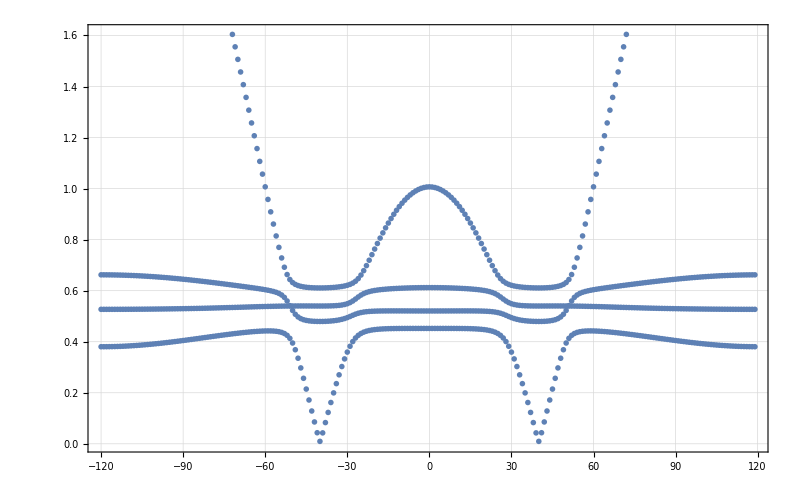

-Graphics-

#### plain

```mathematica
disp={};
Module[{j0,L0,χ0,ω0,EnList0,J,K,Γ,h, en,η=0.45,L,Nc, En,Disp},L=Ls[[1]];
(*{j0,L0,χ0,ω0,EnList0}= loadData[toPath[parameters[[p]],L,acuracy]][[-1]];*)
 Nc = 900^2;
{J,K,Γ,h}=parameters[[1,1]][[1;;4]];
{χ0,ω0}={χG,ωG};
En = EnergiesSortedW[Nc, J,K, Γ, h,χ0,ω0,η] ;
Disp = lineDispersionSortedW[En];
disp = Disp    ];
```

Part::partd: Part specification χG⟦1,2,2⟧ is longer than depth of object.

Part::partd: Part specification χG⟦1,2,1⟧ is longer than depth of object.

Part::partd: Part specification χG⟦1,1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
size=0.0056;Module[ {En, Disp,L, J,K,Γ, h ,η, χ0,ω0 ,title, color, j0, L0, EnList0,Kval,Nc,Kticks},
Kval=disp[[1]][[;;,1]];
Nc=Length@Kval;
 {J,K,Γ,h}=parameters[[1,1]][[1;;4]];
Kticks={ { Kval[[1]],MaTeX["\\Gamma",Magnification->1.8]},{Kval[[  ⌊Nc/3⌋+1  ]],MaTeX["\\mathrm{K}",Magnification->1.8]},{Kval[[ ⌊(2Nc)/3⌋+1]],MaTeX["\\mathrm{K}^\\prime",Magnification->1.8]},{Kval[[-1]]+1,MaTeX["\\Gamma",Magnification->1.8]}};
title=StringReplace["J = X1, K = X2, \\Gamma = X3, \\mathbf{h} =  X4 \\, \\mathbf{c}",{"X1"-> ToString[J],"X2"-> ToString[K],"X3"-> ToString[Γ] ,"X4"-> ToString[Norm@h]    }] ;
 ListPlot[ disp  , Joined->False ,  PlotRange-> {0,2*1.61} , FrameLabel->{MaTeX[" ",Magnification->2] , MaTeX["E(\\mathbf{k})",Magnification->2] } , Frame->True ,   FrameStyle ->Directive[Black,20], FrameTicksStyle->Directive[Black,15],(*PlotMarkers->Scaled[],*)ImageSize->1000, GridLines->Automatic,  PlotLabel-> Style[MaTeX[title,Magnification->2] ,20 ,Black ],  FrameTicks->{{Automatic,None}, {Kticks,None }  }    ,
  PlotStyle->  {{ Darker@Blue,PointSize[size]}}    ]   ]
```

#### plain ΓKMΓ

```mathematica
toLineΓKMΓ[M_]:=Module[ {ks,Ne,Δt},(* 1: Γ=0, 2: K=(1/3,2/3), 3: K'=(2/3,3/3), 4: Γ=0,  *)
ks={ Γpoint,Kpoint,MPpoint,Γpoint }; 
Ne=Length[ks]-1; (* number of edges making the path in the BZ*) 
Flatten[ Table[ Table[ ks[[i]]+t(  ks[[i+1]]-ks[[i]]  ),{t,Ne/M(1-KroneckerDelta[i,1]),1,Ne/M}],{i,1,Ne}],1]
    ] ;
```

```mathematica
pathΓKMΓ=With[{ps=.03,mag=1.7},
Graphics[{
{Red,Thickness[0.3ps],Opacity[1],Arrowheads[{{0.07,0.57}}],
Arrow[#]&/@Partition[  {Γpoint,Kpoint,Mpoint,Γpoint}  ,2,1]},
{Black,PointSize[ps],Point[Mpoint],Point[Γpoint],Point[Kpoint],Point[KPpoint]},
Inset[MaTeX["\\mathrm{M}",Magnification->mag],Mpoint,Scaled[{0.5,0}]  ],
Inset[MaTeX["\\mathrm{\\Gamma}",Magnification->mag],Γpoint,Scaled[{0.5,1.2}]  ],
Inset[MaTeX["\\mathrm{K}",Magnification->mag],Kpoint,Scaled[{0.5,0}]  ],
Inset[MaTeX["\\mathrm{K}^\\prime",Magnification->mag],KPpoint,Scaled[{0.5,0}]  ],
(*{Black,Dashed,Opacity[0.5],Arrow[{{0,0},mx}],Arrow[{{0,0},my}]},*)
Black,Dashed,Line[{ Kpoint,KPpoint,Kpoint-mx,KPpoint-mx-my,Kpoint-mx-my,KPpoint-my ,Kpoint}]
 },ImageSize->400]];
```

```mathematica
EnergiesSortedWΓKMΓ[L_, J_,K_, Γ_, h_,χ_,ω_,η_] :=  Module[ {line = toLineΓKMΓ[L]},
Table[Chop@cutNegativeEV[Eigensystem@N@HMFk[J,K,Γ,h,χ,ω,η,line⟦i⟧]]  , {i,1,L}]      ];
lineDispersionSortedW[E_]:=Module[ {M = Length[E]},    Table[  { i   ,1/2 E⟦i⟧⟦j,2⟧ }, {j,1,4}       , {i,1,M} ]  ];
```

```mathematica
dispΓKMΓ=Table[{},Length@parameters[[1]] ];
Do[
Module[{j0,L0,χ0,ω0,ξG,EnList0,J,K,Γ,h, en,η=0.45,L,Nc, En,Disp},L=Ls[[1]];
{j0,L0,χ0,ω0,ξG,EnList0}= loadData[toPath[parameters[[1,p]],L,acuracy,"free",NbName ]  ];
 L = 1800;
{J,K,Γ,h}=parameters[[1,p]][[1;;4]];
En = EnergiesSortedWΓKMΓ[L, J,K, Γ, h,χ0,ω0,η] ;
Disp = lineDispersionSortedW[En];
dispΓKMΓ[[p]] = Disp    ],{p,1,Length@parameters[[1]]}];
```

```mathematica
size=0.003;
p0=2;
Module[ {En, disp=dispΓKMΓ,L, J,K,Γ, h ,η, χ0,ω0 ,title, color, j0, L0, EnList0,Kval,Nc,Kticks},
Kval=disp[[1,1]][[;;,1]];
Nc=Length@Kval;
 {J,K,Γ,h}=parameters[[1,p0]][[1;;4]];
Kticks={ { Kval[[1]],MaTeX["\\Gamma",Magnification->1.8]},{Kval[[  ⌊Nc/3⌋+1  ]],MaTeX["\\mathrm{K}",Magnification->1.8]},{Kval[[ ⌊(2Nc)/3⌋+1]],MaTeX["\\mathrm{M}",Magnification->1.8]},{Kval[[-1]]+1,MaTeX["\\Gamma",Magnification->1.8]}};
title=StringReplace["J = X1, K = X2, \\Gamma = X3, \\mathbf{h} =  X4 \\, \\mathbf{c}",{"X1"-> ToString[NumberForm[J,{2,2}]],"X2"-> ToString[NumberForm[K,{2,2}]],"X3"-> ToString[NumberForm[Γ,{2,2}]] ,"X4"-> ToString[NumberForm[N[Round[100Norm@h]/100],{2,2}]]     }] ;
Show[{
 ListPlot[ disp[[p0]]  ,  Joined->False ,  PlotRange-> {-0.01,1.6} , FrameLabel->{MaTeX[" ",Magnification->2] , MaTeX["E(\\mathbf{k})",Magnification->2] } , Frame->True ,   FrameStyle ->Directive[Black,20], FrameTicksStyle->Directive[Black,15],(*PlotMarkers->Scaled[],*)ImageSize->1000,  PlotLabel-> Style[MaTeX[title,Magnification->2] ,20 ,Black ],  FrameTicks->{{Automatic,None}, {Kticks,None }  }    , 
Epilog->Inset[pathΓKMΓ,Scaled[{0.36,.95}],Scaled[{0.5,1}],Scaled[2.5]  ],
 PlotStyle->  {{ Blue,Opacity[0.4],PointSize[1.12 size]}}     ]  ,
ListPlot[ disp[[1]],   PlotStyle->  {{ Black,Opacity[0.8],PointSize[0.58size]}} ] 
}]
]
```

#### plain full path

```mathematica
toLineΓKMΓKMM[M_]:=Module[ {ks,Ne,Δt},(* 1: Γ=0, 2: K=(1/3,2/3), 3: K'=(2/3,3/3), 4: Γ=0,  *)
ks={ Γpoint,KPpoint,MPpoint,Γpoint,Kpoint,Mpoint,MPPpoint }; 
Ne=Length[ks]-1; (* number of edges making the path in the BZ*) 
Flatten[ Table[ Table[ ks[[i]]+t(  ks[[i+1]]-ks[[i]]  ),{t,Ne/M(1-KroneckerDelta[i,1]),1,Ne/M}],{i,1,Ne}],1]
    ] ;
```

```mathematica
pathΓKMΓKMM=With[{ps=.03,mag=1.7},
Graphics[{
{Red,Thickness[0.3ps],Opacity[1],Arrowheads[{{0.07,0.57}}],
Arrow[#]&/@Partition[  {Γpoint,KPpoint,MPpoint,Γpoint,Kpoint,Mpoint,MPPpoint}  ,2,1]},
{Black,PointSize[ps],Point[Mpoint],Point[MPpoint],Point[MPPpoint],Point[Γpoint],Point[Kpoint],Point[KPpoint]},
Inset[MaTeX["\\mathrm{M}",Magnification->mag],Mpoint,Scaled[{0.5,0}]  ],
Inset[MaTeX["\\mathrm{M}^{\\prime}",Magnification->mag],MPpoint,Scaled[{0.75,-0.25}]  ],
Inset[MaTeX["\\,\\mathrm{M}^{\\prime\\prime}",Magnification->mag],MPPpoint,Scaled[{0.25,-0.25}]  ],
Inset[MaTeX["\\mathrm{\\Gamma}",Magnification->mag],Γpoint,Scaled[{0.5,1.2}]  ],
Inset[MaTeX["\\mathrm{K}",Magnification->mag],Kpoint,Scaled[{0.5,0}]  ],
Inset[MaTeX["\\mathrm{K}^\\prime",Magnification->mag],KPpoint,Scaled[{0.5,0}]  ],
(*{Purple,Opacity[0.5],Arrowheads[Large],Arrow[{{0,0},mx}],Arrow[{{0,0},my}]},*)
Black,Dashed,Line[{ Kpoint,KPpoint,Kpoint-mx,KPpoint-mx-my,Kpoint-mx-my,KPpoint-my ,Kpoint}]
 },ImageSize->400]];
```

```mathematica
EnergiesSortedWΓKMΓKMM[L_, J_,K_, Γ_, h_,χ_,ω_,η_] :=  Module[ {line = toLineΓKMΓKMM[L]},
Table[Chop@weightSort@cutNegativeEV[Eigensystem@N@HMFk[J,K,Γ,h,χ,ω,η,line⟦i⟧]]  , {i,1,L}]      ];
lineDispersionSortedW[E_]:=Module[ {M = Length[E]},    Table[  { i ,1/2 E⟦i⟧⟦j,2⟧ }, {j,1,4}       , {i,1,M} ]  ];
```

```mathematica
dispΓKMΓKMM=Table[{},Length@parameters[[1]] ];
Do[
Module[{j0,L0,χ0,ω0,ξG,EnList0,J,K,Γ,h, en,η=0.45,L,Nc, En,Disp},L=Ls[[1]];
{j0,L0,χ0,ω0,ξG,EnList0}= loadData[toPath[parameters[[1,p]],L,acuracy,"free",NbName ]  ];
 L = 1800;
{J,K,Γ,h}=parameters[[1,p]][[1;;4]];
En = EnergiesSortedWΓKMΓKMM[L, J,K, Γ, h,χ0,ω0,η] ;
Disp = lineDispersionSortedW[En];
dispΓKMΓKMM[[p]] = Disp    ],{p,1,Length@parameters[[1]]}];
```

```mathematica
size=0.003;
p0=2;
Module[ {En,  disp=dispΓKMΓKMM,L, J,K,Γ, h ,η, χ0,ω0 ,title, color, j0, L0, EnList0,Kval,M,Kticks,ks,klabel,knum},
Kval=disp[[1,1,;;,1]];
M=Length@Kval;
 {J,K,Γ,h}=parameters[[1,p0]][[1;;4]];
knum=Length[{ Γpoint,KPpoint,MPpoint,Γpoint,Kpoint,Mpoint,MPPpoint }];
ks=Table[  Kval[[  ⌊(i M)/(knum-1)⌋  +1-KroneckerDelta[knum-1,i]]]  , {i,0,knum-1}];
klabel=MaTeX[#,Magnification->1.8]&/@{"\\Gamma","\\mathrm{K}^{\\prime}","\\mathrm{M}^{\\prime}","\\Gamma","\\mathrm{K}","\\mathrm{M}","\\mathrm{M}^{\\prime\\prime}"};
Kticks=Thread[{ks,klabel}]; 
title=StringReplace["J = X1, K = X2, \\Gamma = X3, \\mathbf{h} =  X4 \\, \\mathbf{c}",{"X1"-> ToString[NumberForm[J,{2,2}]],"X2"-> ToString[NumberForm[K,{2,2}]],"X3"-> ToString[NumberForm[Γ,{2,2}]] ,"X4"-> ToString[NumberForm[N[Round[100Norm@h]/100],{2,2}]]    }] ;

Show[{
 ListPlot[ disp[[p0]]  , Joined->False ,  PlotRange-> {0,1.61} , FrameLabel->{MaTeX[" ",Magnification->2] , MaTeX["E(\\mathbf{k})",Magnification->2] } , Frame->True ,   FrameStyle ->Directive[Black,20], FrameTicksStyle->Directive[Black,15],(*PlotMarkers->Scaled[],*)ImageSize->1000,  PlotLabel-> Style[MaTeX[title,Magnification->2] ,20 ,Black ],  FrameTicks->{{Automatic,None}, {Kticks,None }  }    , 
Epilog->Inset[path,Scaled[{0.8,.92}],Scaled[{0.5,1}],Scaled[3]  ],
   PlotStyle->  {{ Blue,PointSize[size]}}     ]  ,
ListPlot[ disp[[1]],PlotStyle->  {{ Black,PointSize[0.5size]}}  ] 
}]
 ]
```

#### sort for join test

```mathematica
(*Module[{ev0=ev,L,Δev0,ΔevF={},evF={},ΔevPerm,evPerm,indices={},j,x},
L=Length[ev0];
Δev0;
evPerm=Permutations/@ev0;
ΔevPerm=Permutations/@Δev0;(* Thread[  {Range[Factorial[4]],Permutations[#]}]&/@ev0;*)
AppendTo[indices,1];
AppendTo[ΔevF,ΔevPerm[[1,indices[[1]] ]]  ];
AppendTo[evF,evPerm[[1,indices[[1]] ]]  ];

Do[
x=SortBy[Table[{j,Total@Abs[evPerm[[i,j]]-evF[[i-1]]]},{j,1,Factorial[4]}  ],Last];
(*Print@x[[1;;3]];*)
j=x[[1,1]];

AppendTo[indices,j];
AppendTo[evF,evPerm[[i,indices[[i]] ]]];
,{i,2,L}];
Print[indices];
(*ListPlot[ evF ]*)
ListPlot[     Table[  { i   ,1/2 evF⟦i⟧⟦j⟧ }, {j,1,4}       , {i,1,L} ] , Joined->True]
]
weightSort2[es_] := Module[ {E1,ΔE1,E2},
E1=Sort@Table[ { es⟦n,1⟧,n}, {n,1,4}];
Sort[En]
];*)
```

```mathematica
Module[{j0,L0,χ0,ω0,ξG,EnList0,p=1,J,K,Γ,h, en,η=0.45,L,Nc, En,Disp,line },
L0=Ls[[1]];L=1800;
line = toLineΓKMΓKMM[L];
{J,K,Γ,h}=parameters[[1,p]][[1;;4]];
{j0,L0,χ0,ω0,ξG,EnList0}= loadData[toPath[parameters[[1,p]],L0,acuracy,"free",NbName ]  ];
ev= Table[Chop[cutNegativeEV[Eigenvalues@N@HMFk[J,K,Γ,h,χ0,ω0,η,line⟦i⟧]],10^-8]  , {i,1,L}]     
];
```

```mathematica
pairCP[changepoints_]:=If[Length@changepoints<= 2,{{3,3,3},{1,0,0}},  If[ Subtract@@changepoints[[1;;2,1]] ==0,changepoints[[1;;2]],pairCP@Drop[changepoints,1]   ]   ];
```

```mathematica
Module[{L=1800,evN=ev},

Print[ListPlot[     Table[  { i   ,  evN⟦i⟧⟦j⟧    }, {j,1,4}       , {i,1,L} ] , PlotRange->Full,Joined->True]];
changepoints=Sort[Flatten[Select[#,Abs[#[[2]]  ]>1&]&/@(  Table[  {  i,L/2(evN⟦i+1⟧⟦n⟧-2evN⟦i⟧⟦n⟧+evN⟦i-1⟧⟦n⟧),n    }, {n,1,4}       , {i,2,L-1} ]   ) ,1]];
Print@changepoints;
Print@changepoints[[1;;4]];
{{i1,δ1,n1},{i2,δ2,n2}}=pairCP[changepoints]  ;
Print[δ1+δ2];


Print[ListPlot[     Table[  { i   ,  evN⟦i⟧⟦j⟧    }, {j,1,4}       , {i,1,L} ] , PlotRange->Full,Joined->True]];
changepoints=Sort[Flatten[Select[#,Abs[#[[2]]  ]>1&]&/@(  Table[  {  i,L/2(evN⟦i+1⟧⟦n⟧-2evN⟦i⟧⟦n⟧+evN⟦i-1⟧⟦n⟧),n    }, {n,1,4}       , {i,2,L-1} ]   ) ,1]];
Print@changepoints;
Print@changepoints[[1;;4]];
{{i1,δ1,n1},{i2,δ2,n2}}=pairCP[changepoints]  ;
Print[δ1+δ2];


evN=If[i1==i2 && Abs[δ1+δ2]<1,  Join[  evN[[1;;i1]],Permute[ #, Cycles[{    {n1,n2}         }] ]&/@evN[[i1+1;;-1]],evN          ]                 ] ;

Print[ListPlot[     Table[  { i   ,  evN⟦i⟧⟦j⟧    }, {j,1,4}       , {i,1,L} ] , PlotRange->Full,Joined->True]];
changepoints=Sort[Flatten[Select[#,Abs[#[[2]]  ]>1&]&/@(  Table[  {  i,L/2(evN⟦i+1⟧⟦n⟧-2evN⟦i⟧⟦n⟧+evN⟦i-1⟧⟦n⟧),n    }, {n,1,4}       , {i,2,L-1} ]   ) ,1]];
Print@changepoints;
Print@changepoints[[1;;4]];
{{i1,δ1,n1},{i2,δ2,n2}}=pairCP[changepoints]  ;
Print[δ1+δ2];


evN=If[i1==i2 && Abs[δ1+δ2]<1,  Join[  evN[[1;;i1]],Permute[ #, Cycles[{    {n1,n2}         }] ]&/@evN[[i1+1;;-1]],evN          ]                 ] ;

Print[ListPlot[     Table[  { i   ,  evN⟦i⟧⟦j⟧    }, {j,1,4}       , {i,1,L} ] , PlotRange->Full,Joined->True]];
changepoints=Sort[Flatten[Select[#,Abs[#[[2]]  ]>1&]&/@(  Table[  {  i,L/2(evN⟦i+1⟧⟦n⟧-2evN⟦i⟧⟦n⟧+evN⟦i-1⟧⟦n⟧),n    }, {n,1,4}       , {i,2,L-1} ]   ) ,1]];
Print@changepoints;
Print@changepoints[[1;;4]];
{{i1,δ1,n1},{i2,δ2,n2}}=pairCP[changepoints]  ;
Print[δ1+δ2];


evN=If[i1==i2 && Abs[δ1+δ2]<1,  Join[  evN[[1;;i1]],Permute[ #, Cycles[{    {n1,n2}         }] ]&/@evN[[i1+1;;-1]],evN          ]                 ] ;
Print[ListPlot[     Table[  { i   ,  evN⟦i⟧⟦j⟧    }, {j,1,4}       , {i,1,L} ] , PlotRange->Full,Joined->True]];

changepoints=Sort[Flatten[Select[#,Abs[#[[2]]  ]>1&]&/@(  Table[  {  i,L/2(evN⟦i+1⟧⟦n⟧-2evN⟦i⟧⟦n⟧+evN⟦i-1⟧⟦n⟧),n    }, {n,1,4}       , {i,2,L-1} ]   ) ,1]];
Print@changepoints;
{{i1,δ1,n1},{i2,δ2,n2}}=pairCP[changepoints]  ;
Print[δ1+δ2];


evN=If[i1==i2 && Abs[δ1+δ2]<1,  Join[  evN[[1;;i1]],Permute[ #, Cycles[{    {n1,n2}         }] ]&/@evN[[i1+1;;-1]],evN          ]                 ] ;
Print[ListPlot[     Table[  { i   ,  evN⟦i⟧⟦j⟧    }, {j,1,4}       , {i,1,L} ] , PlotRange->Full,Joined->True]];

changepoints=Sort[Flatten[Select[#,Abs[#[[2]]  ]>1&]&/@(  Table[  {  i,L/2(evN⟦i+1⟧⟦n⟧-2evN⟦i⟧⟦n⟧+evN⟦i-1⟧⟦n⟧),n    }, {n,1,4}       , {i,2,L-1} ]   ) ,1]];
Print@changepoints;

{{i1,δ1,n1},{i2,δ2,n2}}=pairCP[changepoints]  ;
Print[δ1+δ2];

Print[i1==i2 && Abs[δ1+δ2]<1];


evN=If[i1==i2 && Abs[δ1+δ2]<1,  Join[  evN[[1;;i1]],Permute[ #, Cycles[{    {n1,n2}         }] ]&/@evN[[i1+1;;-1]]     ]     ,evN                      ] ;
Print[ListPlot[     Table[  { i   ,  evN⟦i⟧⟦j⟧    }, {j,1,4}       , {i,1,L} ] , PlotRange->Full,Joined->True]];


(*
evN=If[i1==i2 && Abs[δ1+δ2]<1,  Join[  evN[[1;;i1]],Permute[ #, Cycles[{    {n1,n2}         }] ]&/@evN[[i1+1;;-1]],evN          ]                 ] ;

Print[ListPlot[     Table[  { i   ,  evN⟦i⟧⟦j⟧    }, {j,1,4}       , {i,1,L} ] , PlotRange->Full,Joined->True]];
changepoints=Select[#,Abs[#[[2]]  ]>1&]&/@(  Table[  {  i,L/2(evN⟦i+1⟧⟦n⟧-2evN⟦i⟧⟦n⟧+evN⟦i-1⟧⟦n⟧),n    }, {n,1,4}       , {i,2,L-1} ]   ) ;
Print@changepoints;
Print@Sort[Flatten[changepoints,1]][[1;;2]];*)

(*ListPlot[     Table[  { i   , L/2(evN⟦i+1⟧⟦j⟧-2evN⟦i⟧⟦j⟧+evN⟦i-1⟧⟦j⟧)    }, {j,1,4}       , {i,2,L-1} ] , PlotRange->Full,Joined->True]*)
]
```

```mathematica
changepoints
```

```mathematica
DeleteDuplicates@Select[Select[Flatten[changepoints],IntegerQ[#]&],#<= 4&&#>= 1&]
```

```mathematica
Select[ Split@Select[Flatten[changepoints],IntegerQ[#] && #>4&], Length[#]==2&]
```

#### sort for join

```mathematica
pairCP[changepoints_]:=If[Length@changepoints<= 2,{{3,3,3},{1,0,0}},  If[ Subtract@@changepoints[[1;;2,1]] ==0,changepoints[[1;;2]],pairCP@Drop[changepoints,1]   ]   ];
```

```mathematica
sortContinuos[ev_]:=Module[{L,evN=ev,Δcp=2,changepoints,a=0}, L=Length[ev];
While[ a<10 && Δcp>=2  , a=a+1;
changepoints=Sort@Flatten[   Select[#,Abs[#[[2]]  ]>1&]&/@(  Table[  {  i,L/2(evN⟦i+1⟧⟦n⟧-2evN⟦i⟧⟦n⟧+evN⟦i-1⟧⟦n⟧),n    }, {n,1,4}       , {i,2,L-1} ]   )  ,1] ;
Δcp=Length[   Select[ Split@Select[Flatten[changepoints],IntegerQ[#] && #>4&], Length[#]==2&]       ];
PrintTemporary[a];
If[Δcp<1,Continue[]  ];
(*Print[ "Δcp=", Δcp,"; points= ",Sort[    changepoints   ]   ];*)
{{i1,δ1,n1},{i2,δ2,n2}}=pairCP[changepoints];
evN=If[i1==i2 && Abs[δ1+δ2]<1,  Join[  evN[[1;;i1]],Permute[ #, Cycles[{    {n1,n2}         }] ]&/@evN[[i1+1;;-1]]   ],evN           ] 
(*Print[ListPlot[     Table[  { i   ,  evN⟦i⟧⟦j⟧    }, {j,1,4}       , {i,1,L} ] , PlotRange->Full,Joined->True]];*)
]  ;evN];
```

```mathematica
Module[{j0,L0,χ0,ω0,ξG,EnList0,p=1,J,K,Γ,h, en,η=0.45,L,Nc, En,Disp,line },
L0=Ls[[1]];
L=1800;
line = toLineΓKMΓKMM[L];
{J,K,Γ,h}=parameters[[1,p]][[1;;4]];
{j0,L0,χ0,ω0,ξG,EnList0}= loadData[toPath[parameters[[1,p]],L0,acuracy,"free",NbName ]  ];
ev= sortContinuos@Table[Chop[cutNegativeEV[Eigenvalues@N@HMFk[J,K,Γ,h,χ0,ω0,η,line⟦i⟧]],10^-9]  , {i,1,L}]  ; 
disp=  Table[  { i ,1/2 ev⟦i⟧⟦j⟧ }, {j,1,4}       , {i,1,L} ];
];
```

```mathematica
(*ListPlot[     disp , PlotRange->Full,Joined->True]*)
```

#### plain ΓKMΓ

```mathematica
dispersionContinumΓKMΓ[L_, J_,K_, Γ_, h_,χ_,ω_,η_] :=  Module[ {line,ks,Ne,Δt,M=L,ev},
ks={ Γpoint,Kpoint,MPpoint,Γpoint }; 
Ne=Length[ks]-1;  
line=Flatten[ Table[ Table[ ks[[i]]+t(  ks[[i+1]]-ks[[i]]  ),{t,Ne/M(1-KroneckerDelta[i,1]),1,Ne/M}],{i,1,Ne}],1];
ev= sortContinuos@Table[Chop@cutNegativeEV[ Eigenvalues@N@HMFk[J,K,Γ,h,χ,ω,η,line⟦i⟧ ] ]    , {i,1,L}]  ; 
Table[  { i ,1/2 ev⟦i⟧⟦j⟧ }, {j,1,4}       , {i,1,L} ]
 ];
```

```mathematica
pathΓKMΓ=With[{ps=.03,mag=1.7},
Graphics[{
{Red,Thickness[0.3ps],Opacity[1],Arrowheads[{{0.07,0.57}}],
Arrow[#]&/@Partition[  {Γpoint,Kpoint,Mpoint,Γpoint}  ,2,1]},
{Black,PointSize[ps],Point[Mpoint],Point[Γpoint],Point[Kpoint],Point[KPpoint]},
Inset[MaTeX["\\mathrm{M}",Magnification->mag],Mpoint,Scaled[{0.5,0}]  ],
Inset[MaTeX["\\mathrm{\\Gamma}",Magnification->mag],Γpoint,Scaled[{0.5,1.2}]  ],
Inset[MaTeX["\\mathrm{K}",Magnification->mag],Kpoint,Scaled[{0.5,0}]  ],
Inset[MaTeX["\\mathrm{K}^\\prime",Magnification->mag],KPpoint,Scaled[{0.5,0}]  ],
(*{Black,Dashed,Opacity[0.5],Arrow[{{0,0},mx}],Arrow[{{0,0},my}]},*)
Black,Dashed,Line[{ Kpoint,KPpoint,Kpoint-mx,KPpoint-mx-my,Kpoint-mx-my,KPpoint-my ,Kpoint}]
 },ImageSize->400]];
```

### figs

```mathematica
NbName = "705"; 
		Ls =Range[40,40,2]; 	    tV={0};				hV={{0.001,0,0}};
		steps=600;                                     acuracy=6;                               ΔeV=0.099999;                                           eVs=Table[ 1700 ξ, {ξ,0,0,ΔeV} ] ; 

		Js={0.};
		Ks={-1.};
		Γs=Table[γ,{γ,0.,.2,.2}];
		hV=Table[{h,0,0},{h,0.,0.4,.2}];

		ts = Table[ {5x,160,-12x,0,-60},{x,tV}];
		hs =Table[  h[[1]]  hAngle[h[[2]],h[[3]]] , {h,hV}];  
		eV0=0;U=2600;JH=300;

		Module[{parameters0,parameters1},
				parameters0=Tuples[{Js,Ks,Γs,hs}];
				parameters1=Tuples[{Js,Ks,Γs,hV}];
				parameters={Table[  Flatten[{ parameters0[[i]],parameters1[[i]],{0},{0}},1],  {i,1,Length@parameters0}]};
		];
```

```mathematica
Column@parameters[[1]][[;;,5;;8]]
```

```mathematica
dispΓKMΓ=Table[{},Length@parameters[[1]] ];
Do[
Module[{j0,L0,χ0,ω0,ξG,EnList0,J,K,Γ,h, en,η=0.45,L,Nc, En,Disp},L=Ls[[1]];
{j0,L0,χ0,ω0,ξG,EnList0}= loadData[toPath[parameters[[1,p]],L,acuracy,"free",NbName ]  ];
 L = 1800;
{J,K,Γ,h}=parameters[[1,p]][[1;;4]]; 
dispΓKMΓ[[p]] = dispersionContinumΓKMΓ[L, J,K, Γ, h,χ0,ω0,η] ;      ],{p,1,Length@parameters[[1]]}];
```

```mathematica
parameters[[1,6]]
```

{0.,-1.,0.2,{0.23094,0.23094,0.23094},0.,-1.,0.2,{0.4,0,0},0,0}

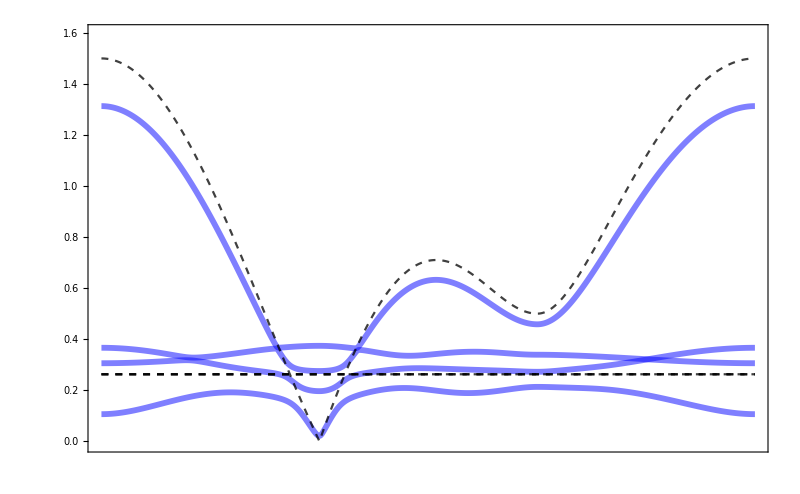

```mathematica
size=0.0035;
p0=6;
fig1a=Module[ {En, disp=dispΓKMΓ,L, J,K,Γ, h ,η, χ0,ω0 ,title, color,img=800, j0, L0, EnList0,Kval,Nc,Kticks},
Kval=disp[[1,1]][[;;,1]];
Nc=Length@Kval;
 {J,K,Γ,h}=parameters[[1,p0]][[1;;4]];
Kticks={ { Kval[[1]],MaTeX["\\Gamma",Magnification->1.8]},{Kval[[  ⌊Nc/3⌋+1  ]],MaTeX["\\mathrm{K}",Magnification->1.8]},{Kval[[ ⌊(2Nc)/3⌋+1]],MaTeX["\\mathrm{M}",Magnification->1.8]},{Kval[[-1]]+1,MaTeX["\\Gamma",Magnification->1.8]}};
title=StringReplace["J = X1, K = X2, \\Gamma = X3, \\mathbf{h} =  X4 \\, \\mathbf{c}",{"X1"-> ToString[NumberForm[J,{2,2}]],"X2"-> ToString[NumberForm[K,{2,2}]],"X3"-> ToString[NumberForm[Γ,{2,2}]] ,"X4"-> ToString[NumberForm[N[Round[100Norm@h]/100],{2,2}]]     }] ;
Show[{
 ListPlot[ disp[[p0]]  ,  Joined->True ,  PlotRange-> {-0.01,1.6} , FrameLabel->{MaTeX[" ",Magnification->2] , MaTeX["E(\\mathbf{k})",Magnification->2] } , Frame->True ,   FrameStyle ->Directive[Black,25], FrameTicksStyle->Directive[Black,15],(*PlotMarkers->Scaled[],*)ImageSize->img,  PlotLabel-> Style[MaTeX[title,Magnification->2] ,20 ,Black ],  FrameTicks->{{Automatic,None}, {Kticks,None }  }    , 
Epilog->Inset[pathΓKMΓ,Scaled[{0.36,.92}],Scaled[{0.5,1}],Scaled[4]  ],
 PlotStyle->  {{ Blue,Opacity[0.5],Thickness[1.5 size]}}     ]  ,
ListPlot[ disp[[1]],  Joined->True ,PlotRange->All, PlotStyle->  {{ Black,Dashed,Opacity[0.75],PointSize[0.99size]}} ] 
}]
]
```

```mathematica
ListPlot[dispΓKMΓ[[4]][[4]][[501;;701]], PlotRange->{0,.30}]
```

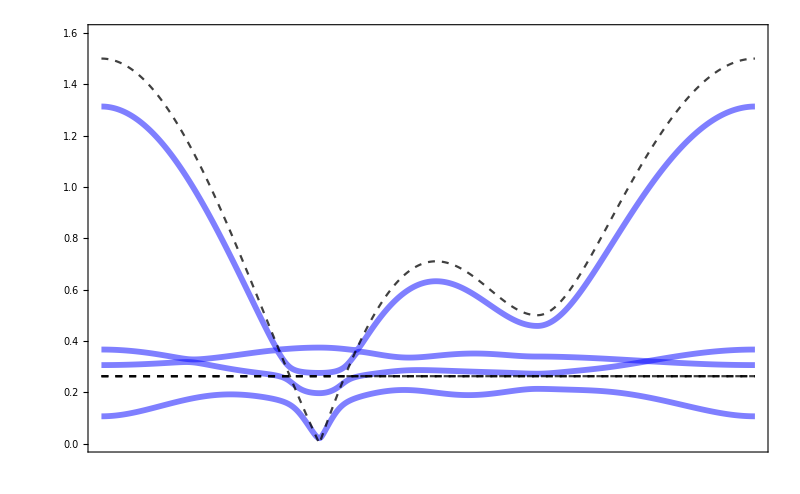

```mathematica
size=0.0035;
p0=6;
fig1b=Module[ {En, disp=dispΓKMΓ,L, J,K,Γ, h ,η, χ0,ω0 ,title, color,img=800, j0, L0, EnList0,Kval,Nc,Kticks,mag=2.2},
Kval=disp[[1,1]][[;;,1]];
Nc=Length@Kval;
 {J,K,Γ,h}=parameters[[1,p0]][[1;;4]];
Kticks={ { Kval[[1]],MaTeX["\\Gamma",Magnification->mag]},{Kval[[  ⌊Nc/3⌋+1  ]],MaTeX["\\mathrm{K}",Magnification->mag]},{Kval[[ ⌊(2Nc)/3⌋+1]],MaTeX["\\mathrm{M}",Magnification->mag]},{Kval[[-1]]+1,MaTeX["\\Gamma",Magnification->mag]}};
title=StringReplace["J = X1, K = X2, \\Gamma = X3, \\mathbf{h} =  X4 \\, \\mathbf{c}",{"X1"-> ToString[NumberForm[J,{2,2}]],"X2"-> ToString[NumberForm[K,{2,2}]],"X3"-> ToString[NumberForm[Γ,{2,2}]] ,"X4"-> ToString[NumberForm[N[Round[100Norm@h]/100],{2,2}]]     }] ;
Show[{
 ListPlot[ disp[[p0]]  ,  Joined->True ,  PlotRange-> {-0.001,1.6}  , FrameLabel->{MaTeX[" ",Magnification->2] , MaTeX["E(\\mathbf{k})",Magnification->2.2] } , Frame->True ,   FrameStyle ->Directive[Black,25], FrameTicksStyle->Directive[Black,15],(*PlotMarkers->Scaled[],*)ImageSize->img,  (*PlotLabel-> Style[MaTeX[title,Magnification->2] ,20 ,Black ], *) FrameTicks->{{Automatic,None}, {Kticks,None }  }    ,  
Epilog->{Inset[pathΓKMΓ,Scaled[{0.36,.92}],Scaled[{0.5,1}],Scaled[4]  ](*,
Inset[ ListPlot[ {disp[[p0]]  ,disp[[1]]},  Joined->True ,  PlotRange-> {{Kval[[  ⌊Nc/3⌋-10  ]],Kval[[  ⌊Nc/3⌋+10  ]]},{-0.0001,.01} },  PlotStyle-> {  { Blue,Opacity[0.5],Thickness[1.5 size]},  { Black,Dashed,Opacity[0.75],PointSize[1size]}  } , Frame->{False,True}     ]

,Scaled[{0.5,.001}],Scaled[{0,0}],Scaled[.15]      ]*)  },
 PlotStyle-> {{ Blue,Opacity[0.5],Thickness[1.5 size]}}        ]  ,
ListPlot[ disp[[1]],  Joined->True ,PlotRange->All, PlotStyle->  {{ Black,Dashed,Opacity[0.75],PointSize[1size]}} ] 
}]
]
```

```mathematica
Export["C:\\User\\lucas\\Desktop\\Wolfram Mathematica\\PhD-codes\\Figures_PhD\\New3\\fig01(h=0.4).pdf"  ,fig1b  ];
```

#### joined path ΓKMΓKMM

```mathematica
dispersionContinumΓKMΓKMM[L_, J_,K_, Γ_, h_,χ_,ω_,η_] :=  Module[ {line,ks,Ne,Δt,M=L,ev},
ks={ Γpoint,KPpoint,MPpoint,Γpoint,Kpoint,Mpoint,MPPpoint }; 
Ne=Length[ks]-1; (* number of edges making the path in the BZ*) 
line=Flatten[ Table[ Table[ ks[[i]]+t(  ks[[i+1]]-ks[[i]]  ),{t,Ne/M(1-KroneckerDelta[i,1]),1,Ne/M}],{i,1,Ne}],1];
ev= sortContinuos@Table[Chop@cutNegativeEV[ Eigenvalues@N@HMFk[J,K,Γ,h,χ,ω,η,line⟦i⟧ ] ]    , {i,1,L}]  ; 
Table[  { i ,1/2 ev⟦i⟧⟦j⟧ }, {j,1,4}       , {i,1,L} ]
 ];
```

```mathematica
pathΓKMΓKMM=With[{ps=.03,mag=1.7},
Graphics[{
{Red,Thickness[0.3ps],Opacity[1],Arrowheads[{{0.07,0.57}}],
Arrow[#]&/@Partition[  {Γpoint,KPpoint,MPpoint,Γpoint,Kpoint,Mpoint,MPPpoint}  ,2,1]},
{Black,PointSize[ps],Point[Mpoint],Point[MPpoint],Point[MPPpoint],Point[Γpoint],Point[Kpoint],Point[KPpoint]},
Inset[MaTeX["\\mathrm{M}",Magnification->mag],Mpoint,Scaled[{0.5,0}]  ],
Inset[MaTeX["\\mathrm{M}^{\\prime}",Magnification->mag],MPpoint,Scaled[{0.75,-0.25}]  ],
Inset[MaTeX["\\,\\mathrm{M}^{\\prime\\prime}",Magnification->mag],MPPpoint,Scaled[{0.25,-0.25}]  ],
Inset[MaTeX["\\mathrm{\\Gamma}",Magnification->mag],Γpoint,Scaled[{0.5,1.2}]  ],
Inset[MaTeX["\\mathrm{K}",Magnification->mag],Kpoint,Scaled[{0.5,0}]  ],
Inset[MaTeX["\\mathrm{K}^\\prime",Magnification->mag],KPpoint,Scaled[{0.5,0}]  ],
(*{Purple,Opacity[0.5],Arrowheads[Large],Arrow[{{0,0},mx}],Arrow[{{0,0},my}]},*)
Black,Dashed,Line[{ Kpoint,KPpoint,Kpoint-mx,KPpoint-mx-my,Kpoint-mx-my,KPpoint-my ,Kpoint}]
 },ImageSize->400]];
```

```mathematica
dispΓKMΓKMM=Table[{},Length@parameters[[1]] ];
Do[Module[{j0,L0,χ0,ω0,ξG,EnList0,J,K,Γ,h, en,η=0.45,L,Nc, En,Disp},L=Ls[[1]];
{j0,L0,χ0,ω0,ξG,EnList0}= loadData[toPath[parameters[[1,p]],L,acuracy,"free",NbName ]  ];
 L = 1800;
{J,K,Γ,h}=parameters[[1,p]][[1;;4]];
dispΓKMΓKMM[[p]] = dispersionContinumΓKMΓKMM[L, J,K, Γ, h,χ0,ω0,η] ;
],{p,1,Length@parameters[[1]]}];
```

```mathematica
size=0.003;
p0=2;
Module[ {En,  disp=dispΓKMΓKMM,L, J,K,Γ, h ,η, χ0,ω0 ,title, color, j0, L0, EnList0,Kval,M,Kticks,ks,klabel,knum},
Kval=disp[[1,1,;;,1]];
M=Length@Kval;
 {J,K,Γ,h}=parameters[[1,p0]][[1;;4]];
knum=Length[{ Γpoint,KPpoint,MPpoint,Γpoint,Kpoint,Mpoint,MPPpoint }];
ks=Table[  Kval[[  ⌊(i M)/(knum-1)⌋  +1-KroneckerDelta[knum-1,i]]]  , {i,0,knum-1}];
klabel=MaTeX[#,Magnification->1.8]&/@{"\\Gamma","\\mathrm{K}^{\\prime}","\\mathrm{M}^{\\prime}","\\Gamma","\\mathrm{K}","\\mathrm{M}","\\mathrm{M}^{\\prime\\prime}"};
Kticks=Thread[{ks,klabel}]; 
title=StringReplace["J = X1, K = X2, \\Gamma = X3, \\mathbf{h} =  X4 \\, \\mathbf{c}",{"X1"-> ToString[NumberForm[J,{2,2}]],"X2"-> ToString[NumberForm[K,{2,2}]],"X3"-> ToString[NumberForm[Γ,{2,2}]] ,"X4"-> ToString[NumberForm[N[Round[100Norm@h]/100],{2,2}]]    }] ;

Show[{
 ListPlot[ disp[[p0]]  , Joined->True ,  PlotRange-> {0,1.61} , FrameLabel->{MaTeX[" ",Magnification->2] , MaTeX["E(\\mathbf{k})",Magnification->2] } , Frame->True ,   FrameStyle ->Directive[Black,20], FrameTicksStyle->Directive[Black,15],(*PlotMarkers->Scaled[],*)ImageSize->1000,  PlotLabel-> Style[MaTeX[title,Magnification->2] ,20 ,Black ],  FrameTicks->{{Automatic,None}, {Kticks,None }  }    , 
Epilog->Inset[pathΓKMΓKMM,Scaled[{0.85,.92}],Scaled[{0.5,1}],Scaled[3.5]  ],
   PlotStyle->  {{ Blue,PointSize[size]}}     ]  ,
ListPlot[ disp[[1]],Joined->True ,PlotRange-> Full,PlotStyle->  {{ Black,Dashed,Opacity[0.8],PointSize[0.5size]}}  ] 
}]
 ]
```

```mathematica
Fig 1  -  dispersion
```

## video dispersion vs h, Γ

#### versus h for Γ=0

```mathematica
NbName = "705"; 
		Ls =Range[40,40,2]; 	    tV={0};	 
		hV=Table[{h,0,0},{h,0.,1,.01}];
		steps=350;                                     acuracy=6;                               ΔeV=0.099999;                                           eVs=Table[ 1700 ξ, {ξ,0,0,ΔeV} ] ; 
ts = Table[ {5x,160,-12x,0,-60},{x,tV}];
hs =Table[  h[[1]]  hAngle[h[[2]],h[[3]]] , {h,hV}];  
eV0=0;U=2600;JH=300;
parameters=Table[Flatten[ Table[ {N@Jr[0,JH,U,ts[[t]] ],N@Kr[0,JH,U,ts[[t]]],N@Γr[0,JH,U,ts[[t]]],hs[[h]] ,N@Jr[eVs[[ev]],JH,U,ts[[t]] ],N@Kr[eVs[[ev]],JH,U,ts[[t]]],N@Γr[eVs[[ev]],JH,U,ts[[t]]],hV[[h]],tV[[t]],eVs[[ev]]} , {t,1,Length@tV},  {h,1,Length@hV}],1] ,  {ev,1,Length@eVs}];
```

```mathematica
(*FileNameJoin[{ NotebookDirectory[], "\\..\\Figures_PhD\\Videos\\dispH1\\dispH1.mp4" }]*)
```

```mathematica
dispH=Table[{},Length@parameters[[1]] ]; 
Do[
Module[{j0,L0,χ0,ω0,ξG,EnList0,J,K,Γ,h, en,η=0.45,L,Nc, En,Disp},L=Ls[[1]];
{j0,L0,χ0,ω0,ξG,EnList0}= loadData[toPath[parameters[[1,p]],L,acuracy,"free",NbName ]  ];
 L = 300;
{J,K,Γ,h}=parameters[[1,p]][[1;;4]]; 
dispH[[p]] = dispersionContinumΓKMΓ[L, J,K, Γ, h,χ0,ω0,η] ;      ],{p,1,Length@parameters[[1]]}];
```

```mathematica
size=0.003;
Np=Length@parameters[[1]] ;
Export["C:\\User\\lucas\\Desktop\\Wolfram Mathematica\\PhD-codes\\Figures_PhD\\Videos\\dispH1\\dispH1.mkv",
Table[
Module[ {En, disp=dispH,L, J,K,Γ, h ,η, χ0,ω0 ,title, color,img=1400, j0, L0, EnList0,Kval,Nc,Kticks},
Kval=disp[[1,1]][[;;,1]];
Nc=Length@Kval;
 {J,K,Γ,h}=parameters[[1,p]][[1;;4]];
Kticks={ { Kval[[1]],MaTeX["\\Gamma",Magnification->1.8]},{Kval[[  ⌊Nc/3⌋+1  ]],MaTeX["\\mathrm{K}",Magnification->1.8]},{Kval[[ ⌊(2Nc)/3⌋+1]],MaTeX["\\mathrm{M}",Magnification->1.8]},{Kval[[-1]]+1,MaTeX["\\Gamma",Magnification->1.8]}};
title=StringReplace["J = X1, K = X2, \\Gamma = X3, \\mathbf{h} =  X4 \\, \\mathbf{c}",{"X1"-> ToString[NumberForm[J,{2,2}]],"X2"-> ToString[NumberForm[K,{2,2}]],"X3"-> ToString[NumberForm[Γ,{2,2}]] ,"X4"-> ToString[NumberForm[N[Round[100Norm@h]/100],{2,2}]]     }] ;


(*Export[ FileNameJoin[{ NotebookDirectory[], StringReplace["\\..\\Figures_PhD\\Videos\\Files\\dispH1\\dispH_XX_pure.png",{"XX"->StringJoin["h=",ToString[NumberForm[N[Round[100Norm@h]/100],{2,2}]] ,"_p=",ToString[ p]   ]  }]  }],  *) 
Show[{
 ListPlot[ disp[[p]]  ,  Joined->True ,  PlotRange-> {-0.01,1.6} , FrameLabel->{MaTeX[" ",Magnification->2] , MaTeX["E(\\mathbf{k})",Magnification->2] } , Frame->True ,   FrameStyle ->Directive[Black,25], FrameTicksStyle->Directive[Black,15],(*PlotMarkers->Scaled[],*)ImageSize->img,  PlotLabel-> Style[MaTeX[title,Magnification->2] ,20 ,Black ],  FrameTicks->{{Automatic,None}, {Kticks,None }  }    , 
Epilog->Inset[ Style[StringJoin["p = ",ToString@p],Bold,12],Scaled[{0.5,.975}],Scaled[{0.5,1}]  ],
 PlotStyle-> {{ Blue,Opacity[0.5],Thickness[1.5 size]}}        ]  ,
ListPlot[ disp[[1]][[3;;4]],  Joined->True ,PlotRange->All, PlotStyle->  {{ Black,Dashed,Opacity[0.3],PointSize[1.2size]}} ] 
}]
(*];*)
],{p,1,Np    }]
, (*AnimationRepetitions->∞  ,"DisplayDurations"-> Join[ Table[ 20/Np,Np-1],{2}] *) "FrameRate"-> 5       ]
```

#### versus Γ for h=0.05

```mathematica
NbName = "705"; 
		Ls = Range[40,40,4]; 				tV={0};	
		steps=500;				acuracy=6;     eVs=Table[1700 x, {x,0,0,0.099999}];  
		(* for equally spaced Gamma values *)
		Js={0.};
		Ks={-1.};
		Γs=Sort@Join[ Table[γ,{γ,0,1,.01}], Table[γ,{γ,0,-1,-.01}] ];
		hV={{0.2,0,0}};
		 
		hs =Table[  h[[1]]  hAngle[h[[2]],h[[3]]] , {h,hV}];  
		eV0=0;U=2600;JH=300;

		Module[{parameters0,parameters1},
				parameters0=Tuples[{Js,Ks,Γs,hs}];
				parameters1=Tuples[{Js,Ks,Γs,hV}];
				parameters={Table[  Flatten[{ parameters0[[i]],parameters1[[i]],{0},{0}},1],  {i,1,Length@parameters0}]}  ];
```

```mathematica
dispΓ=Table[{},Length@parameters[[1]] ]; 
Do[
Module[{j0,L0,χ0,ω0,ξG,EnList0,J,K,Γ,h, en,η=0.45,L,Nc, En,Disp},L=Ls[[1]];
{j0,L0,χ0,ω0,ξG,EnList0}= loadData[toPath[parameters[[1,p]],L,acuracy,"free",NbName ]  ];
 L = 300;
{J,K,Γ,h}=parameters[[1,p]][[1;;4]]; 
dispΓ[[p]] = dispersionContinumΓKMΓ[L, J,K, Γ, h,χ0,ω0,η] ;      ],{p,1,Length@parameters[[1]]}];
```

```mathematica
Np
```

```mathematica
size=0.003;
Np=Length@parameters[[1]] ;
Export["C:\\User\\lucas\\Desktop\\Wolfram Mathematica\\PhD-codes\\Figures_PhD\\Videos\\dispG1\\disp_vs_Gamma_with_h.2.mkv",
Table[ PrintTemporary["p=",p];
Module[ {En, disp=dispΓ,L, J,K,Γ, h ,η, χ0,ω0 ,title, color,img=1200, j0, L0, EnList0,Kval,Nc,Kticks},
Kval=disp[[1,1]][[;;,1]];
Nc=Length@Kval;
 {J,K,Γ,h}=parameters[[1,p]][[1;;4]];
Kticks={ { Kval[[1]],MaTeX["\\Gamma",Magnification->1.8]},{Kval[[  ⌊Nc/3⌋+1  ]],MaTeX["\\mathrm{K}",Magnification->1.8]},{Kval[[ ⌊(2Nc)/3⌋+1]],MaTeX["\\mathrm{M}",Magnification->1.8]},{Kval[[-1]]+1,MaTeX["\\Gamma",Magnification->1.8]}};
title=StringReplace["J = X1, K = X2, \\Gamma = X3, \\mathbf{h} =  X4 \\, \\mathbf{c}",{"X1"-> ToString[NumberForm[J,{2,2}]],"X2"-> ToString[NumberForm[K,{2,2}]],"X3"-> ToString[NumberForm[Γ,{2,2}]] ,"X4"-> ToString[NumberForm[N[Round[100Norm@h]/100],{2,2}]]     }] ;


(*Export[ FileNameJoin[{ NotebookDirectory[], StringReplace["\\..\\Figures_PhD\\Videos\\Files\\dispH1\\dispH_XX_pure.png",{"XX"->StringJoin["h=",ToString[NumberForm[N[Round[100Norm@h]/100],{2,2}]] ,"_p=",ToString[ p]   ]  }]  }],  *) 
Show[{
 ListPlot[ disp[[p]]  ,  Joined->True ,  PlotRange-> {-0.01,1.6} , FrameLabel->{MaTeX[" ",Magnification->2] , MaTeX["E(\\mathbf{k})",Magnification->2] } , Frame->True ,   FrameStyle ->Directive[Black,25], FrameTicksStyle->Directive[Black,15],(*PlotMarkers->Scaled[],*)ImageSize->img,  PlotLabel-> Style[MaTeX[title,Magnification->2] ,20 ,Black ],  FrameTicks->{{Automatic,None}, {Kticks,None }  }    , 
Epilog->Inset[ Style[StringJoin["p = ",ToString@p],Bold,12],Scaled[{0.5,.975}],Scaled[{0.5,1}]  ],
 PlotStyle-> {{ Blue,Opacity[0.5],Thickness[1.5 size]}}        ]  ,
ListPlot[ disp[[102]],  Joined->True ,PlotRange->All, PlotStyle->  {{ Black,Dashed,Opacity[0.35],PointSize[1.2size]}} ] 
}]
(*];*)
],{p,1,Np    }]
, (*AnimationRepetitions->∞  ,"DisplayDurations"-> Join[ Table[ 40/Np,Np-1],{2}]  *)"FrameRate"-> 4     ]
```

## Fig 2 - gap

```mathematica
NbName = "705"; 
		Ls =Range[40,40,2]; 	    tV={0};	 
		hV=Table[{h,0,0},{h,0.,1,.01}];
		steps=350;                                     acuracy=6;                               ΔeV=0.099999;                                           eVs=Table[ 1700 ξ, {ξ,0,0,ΔeV} ] ; 
ts = Table[ {5x,160,-12x,0,-60},{x,tV}];
hs =Table[  h[[1]]  hAngle[h[[2]],h[[3]]] , {h,hV}];  
eV0=0;U=2600;JH=300;
parameters=Table[Flatten[ Table[ {N@Jr[0,JH,U,ts[[t]] ],N@Kr[0,JH,U,ts[[t]]],N@Γr[0,JH,U,ts[[t]]],hs[[h]] ,N@Jr[eVs[[ev]],JH,U,ts[[t]] ],N@Kr[eVs[[ev]],JH,U,ts[[t]]],N@Γr[eVs[[ev]],JH,U,ts[[t]]],hV[[h]],tV[[t]],eVs[[ev]]} , {t,1,Length@tV},  {h,1,Length@hV}],1] ,  {ev,1,Length@eVs}];
gapH1={};gapKH1={};gapΓH1={};gapH1eff={};
Do[Module[{L,Nc,J,K, Γ, h,jG,LG,χ,ω,en,enΓ,enK,ξG,EnG,η=0,l}, l=1;
L=Ls[[l]];
{J,K, Γ, h}=parameters[[1,p]][[1;;4]];
{jG,LG,χ,ω,ξG,EnG}= loadData[toPath[parameters[[1,p]],L,acuracy,"free",NbName ]  ];

enK= Sort[Abs/@Eigenvalues[ Chop@N@HMFk[ J,K, Γ, h,χ,ω,η,N@kD1], 8 ]    ][[1]];
enΓ= Sort[Abs/@Eigenvalues[ Chop@N@HMFk[ J,K, Γ, h,χ,ω,η,{0,0}], 8 ]    ][[1]];
en=Min[enK,enΓ];

AppendTo[gapKH1,{Norm@h,enK}];
AppendTo[gapΓH1,{Norm@h,enΓ}] ; 
AppendTo[gapH1eff,{Norm[ h + .5 heffM0[J,K,Γ,h,ω,1]  ],en}];
AppendTo[gapH1,{Norm@h,en}]    ],
{p,1,Length@parameters[[1]]}];
```

```mathematica
NbName = "705";Ls = Range[40,40,4]; acuracy=12;   Js={0.};Ks={-1.}; Γs={ Join[ Table[γ,{γ,-0.01,-.12,-.02}] ,Table[γ,{γ,0.01,.12,.02}]   ][[12]]   }; Print["Γ=",Γs[[1]] ];
		hV=Join[  Table[{h,0,0},{h,0.01,1,.02}] (*, Table[{h,0,0},{h,0.01,1.2,.02}]*)   ];  hs= Table[  h[[1]]  hAngle[h[[2]],h[[3]]] , {h,hV}]; 
		eV0=0;U=2600;JH=300;
		Module[{parameters0,parameters1},
				parameters0=Tuples[{Js,Ks,Γs,hs}];
				parameters1=Tuples[{Js,Ks,Γs,hV}];				
parameters={Table[  Flatten[{ parameters0[[i]],parameters1[[i]],{0},{0}},1],  {i,1,Length@parameters0}]}  ];  
gapH2={};gapKH2={};gapΓH2={};
Do[Module[{L,Nc,J,K, Γ, h,jG,LG,χ,ω,en,enΓ,enK,ξG,EnG,η=0,l,ω0}, l=1;
L=Ls[[l]];
{J,K, Γ, h}=parameters[[1,p]][[1;;4]];
{jG,LG,χ,ω,ξG,EnG}= loadData[toPath[parameters[[1,p]],L,acuracy,"free",NbName ]  ];

enK= Sort[Abs/@Eigenvalues[ Chop@N@HMFk[ J,K, Γ, h,χ,ω,η,N@kD1], 8 ]    ][[1]];
enΓ= Sort[Abs/@Eigenvalues[ Chop@N@HMFk[ J,K, Γ, h,χ,ω,η,{0,0}], 8 ]    ][[1]];
en=Min[enK,enΓ];
AppendTo[gapKH2,{Norm@h,enK}];
AppendTo[gapΓH2,{Norm@h,enΓ}] ; 
AppendTo[gapH2,{Norm@h,en}]    ],
{p,1,Length@parameters[[1]]}];
```

Γ=0.11

```mathematica
(*ListPlot[ {gapKH2,gapΓH2}  , Joined->True ,  PlotRange-> {-0.015,1} , FrameLabel->{MaTeX["h",Magnification->2] , MaTeX["\\text{Gap } \\; \\Delta_f",Magnification->2] } , Frame->True, PlotMarkers->"OpenMarkers" ,   FrameStyle ->Directive[Black,20], FrameTicksStyle->Directive[Black,15],ImageSize->600,GridLines->None,  PlotStyle->  {{ Darker@Red, PointSize[1.5 size]},{ Red,Opacity[.8],PointSize[.8  size]}} , PlotLegends->  Placed[MaTeX[#,Magnification->1]&/@{"E(\\mathbf{k}=\\mathrm{K})","E(\\mathbf{k}=\\Gamma)"} ,Scaled[{0.115,0.85}]  ]   
] *)
```

```mathematica
NbName = "705";Ls = Range[40,40,4]; acuracy=12;   Js={0.};Ks={-1.}; Γs={ Join[ Table[γ,{γ,-0.01,-.12,-.02}] ,Table[γ,{γ,0.01,.12,.02}]   ][[5]]   }; Print["Γ=",Γs[[1]] ];
		hV=Join[  Table[{h,0,0},{h,0.01,1,.02}] (*, Table[{h,0,0},{h,0.01,1.2,.02}]*)   ];  hs= Table[  h[[1]]  hAngle[h[[2]],h[[3]]] , {h,hV}]; 
		eV0=0;U=2600;JH=300;
		Module[{parameters0,parameters1},
				parameters0=Tuples[{Js,Ks,Γs,hs}];
				parameters1=Tuples[{Js,Ks,Γs,hV}];				
parameters={Table[  Flatten[{ parameters0[[i]],parameters1[[i]],{0},{0}},1],  {i,1,Length@parameters0}]}  ];  
gapH3={};gapKH3={};gapΓH3={};
Do[Module[{L,Nc,J,K, Γ, h,jG,LG,χ,ω,en,enΓ,enK,ξG,EnG,η=0,l,ω0}, l=1;
L=Ls[[l]];
{J,K, Γ, h}=parameters[[1,p]][[1;;4]];
{jG,LG,χ,ω,ξG,EnG}= loadData[toPath[parameters[[1,p]],L,acuracy,"free",NbName ]  ];

enK= Sort[Abs/@Eigenvalues[ Chop@N@HMFk[ J,K, Γ, h,χ,ω,η,N@kD1], 8 ]    ][[1]];
enΓ= Sort[Abs/@Eigenvalues[ Chop@N@HMFk[ J,K, Γ, h,χ,ω,η,{0,0}], 8 ]    ][[1]];
en=Min[enK,enΓ];
AppendTo[gapKH3,{Norm@h,enK}];
AppendTo[gapΓH3,{Norm@h,enΓ}] ; 
AppendTo[gapH3,{Norm@h,en}]    ],
{p,1,Length@parameters[[1]]}];
```

Γ=-0.09

0.260825

0.304239

0.227624

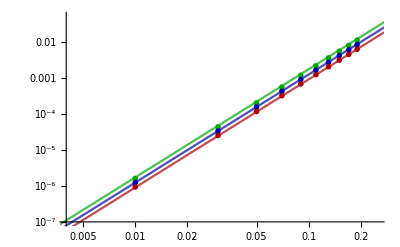

```mathematica
gap1=gapH1[[1;;20]];
gap2=gapH2[[1;;10]];
gap3=gapH3[[1;;10]];
(1/(√(a/(2 √3))))/.FindFit[ gap1[[1;;10]], a (h/(2 √3))^3, a,h]
(1/(√(a/(2 √3))))/.FindFit[ gap2[[1;;10]], a (h/(2 √3))^3, a,h]
(1/(√(a/(2 √3))))/.FindFit[ gap3[[1;;10]], a (h/(2 √3))^3, a,h]
size=0.009;
logInset=Show[ 
ListLogLogPlot[{gap3,gap1[[2;;-1;;2]],gap2},
  FrameStyle ->Directive[Black,18], FrameTicksStyle->Directive[Black,8],(*FrameTicks->None,*) PlotStyle->  { { Darker@Green,PointSize[size]},{ Darker@Blue,PointSize[size]} ,{ Darker@Red,PointSize[size]} } ,
  PlotRange-> {{0.004,0.25},{10^-7,5 10^-2}  } ,(* PlotLegends->  Placed[{   
MaTeX[#,Magnification->1.2]&@"\\Delta_{\, \\mathrm{v}}=0.22",
MaTeX[#,Magnification->1.2]&@"\\Delta_{\, \\mathrm{v}}=0.26",
MaTeX[#,Magnification->1.2]&@"\\Delta_{\, \\mathrm{v}}=0.30"}  ,Scaled[{0.2,0.61}]  ],*) PlotMarkers->"OpenMarkers"(*,Epilog->Inset[ MaTeX["\\Delta_f = \\frac{2 \\sqrt{3}}{\\Delta_{\, \\mathrm{v}}^2} \\; h^xh^yh^z",Magnification->1.3] ,Scaled[{0.24,0.16}] ,Scaled[{-0.1,0.5}]  ]*)  ],
LogLogPlot[{2 √3(Times@@hAngle[0,0])/(0.22)^2 (h/2)^3,  2 √3(Times@@hAngle[0,0])/(0.26)^2 (h/2)^3,  2 √3 Abs[Times@@hAngle[0,0]  ]/(0.304)^2 (h/2)^3 } ,{h,0.00001,0.85},PlotStyle->{ { Darker@Green,Opacity[.7],PointSize[size]},{ Darker@Blue,Opacity[.7],PointSize[size]} ,{ Darker@Red,Opacity[.7],PointSize[size]} }]              ]
```

```mathematica
Abs[Times@@hAngle[0,0]  ]
```

1/(3 √3)

```mathematica
const = 6 √3  1/(8 2); Print[const];
{#[[1]],Sqrt[ (const  Abs[Times@@hAngle[0,0]  ]   (#[[1]] )^3   )/(#[[2]]+10^-11)]    }&/@gap1
```

(3 √3)/8

{{0.,0.},{0.01,0.318603},{0.02,0.318641},{0.03,0.318702},{0.04,0.318788},{0.05,0.318899},{0.06,0.319034},{0.07,0.319194},{0.08,0.319379},{0.09,0.31959},{0.1,0.319826},{0.11,0.320087},{0.12,0.320375},{0.13,0.320688},{0.14,0.321026},{0.15,0.32139},{0.16,0.32178},{0.17,0.322194},{0.18,0.322633},{0.19,0.323097}}

```mathematica
gapH1[[2;;10]]
gapH1eff[[2;;10]]
```

{{0.01,1.23142×10^-6},{0.02,9.84908×10^-6},{0.03,0.0000332279},{0.04,0.00007872},{0.05,0.000153644},{0.06,0.000265271},{0.07,0.000420818},{0.08,0.000627431},{0.09,0.000892177}}

{{0.0177305,1.23142×10^-6},{0.0354619,9.84908×10^-6},{0.0531955,0.0000332279},{0.0709321,0.00007872},{0.0886728,0.000153644},{0.106419,0.000265271},{0.124171,0.000420818},{0.141931,0.000627431},{0.159699,0.000892177}}

```mathematica
const = 6 √3  1/(8 16); Print[const];
{#[[1]],Sqrt[ (const  (#[[1]] /√3)^3   )/(#[[2]]+10^-11)]    }&/@gapH1eff[[2;;10]]
```

(3 √3)/64

{{0.0177305,0.265941},{0.0354619,0.265984},{0.0531955,0.266054},{0.0709321,0.266153},{0.0886728,0.26628},{0.106419,0.266435},{0.124171,0.26662},{0.141931,0.266834},{0.159699,0.267078}}

```mathematica
gapH4=gapH3;
```

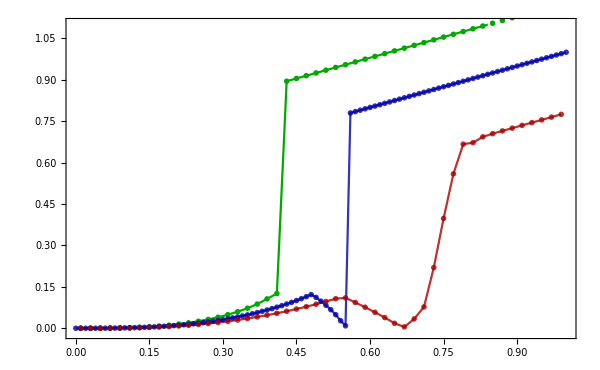

```mathematica
size=0.009;
fig2=Module[ {En, Disp,L, Nc,J,K,Γ, h ,η, χ0,ω0 ,title, color, j0, L0}, 
title=StringReplace["  ",{"X1"-> ToString[J],"X2"-> ToString[K],"X3"-> ToString[Γ] ,"X4"-> ToString[Norm@h]  }] ;
Show[
 ListPlot[ {gapH3,gapH1,gapH2}  , Joined->True ,  PlotRange-> {-0.015,1.1} , FrameLabel->{MaTeX["h",Magnification->2] , MaTeX["\\text{Gap } \\; \\Delta_f",Magnification->2] } , Frame->True, PlotMarkers->"OpenMarkers" ,   FrameStyle ->Directive[Black,20], FrameTicksStyle->Directive[Black,15],ImageSize->600,(* GridLines->None,*)  PlotLabel->Style[MaTeX[title,Magnification->2] ,20 ,Black ], PlotLegends->Placed[MaTeX[#,Magnification->1.5]&/@{"\\Gamma \\!= \\! -0.1","\\Gamma\\! =\\, 0.0","\\Gamma \\!= \\, 0.1"} ,Scaled[{0.89,0.175}]  ] ,  PlotStyle->{{ Darker@Green,PointSize[size]},{ Darker@Blue,Opacity[.8],PointSize[size]} ,{ Darker@Red,Opacity[.8],PointSize[size]} } , Epilog->Inset[logInset,Scaled[{0.25,0.74}],Center,{0.5,Automatic} ]   ]   
(*,Plot[  {   2 √3(Times@@hAngle[0,0])/(0.26)^2 (h/2)^3,  2 √3 Abs[Times@@hAngle[90,0]  ]/(0.26)^2 (h/2)^3 ,  2 √3(Times@@hAngle[0,0])/(0.3)^2 (h/2)^3} (*1.207 h^3*) ,{h,0.0000001,0.6}, PlotStyle->{{Black,Opacity[.25], Thickness[0.0035 ]}}]*)           ] ]
```

```mathematica
Export["C:\\User\\lucas\\Desktop\\Wolfram Mathematica\\PhD-codes\\Figures_PhD\\New2\\Fig02.pdf"  ,fig2  ];
```

## Fig 2.2 - gap 804

```mathematica
NbName = "705";  Ls =Range[40,40,2]; 	    tV={0};	  hV=Table[{h,0,0},{h,0.,1,.01}];
steps=350;                                     acuracy=11;                               ΔeV=0.099999;                                           eVs=Table[ 1700 ξ, {ξ,0,0,ΔeV} ] ; 
ts = Table[ {5x,160,-12x,0,-60},{x,tV}]; hs =Table[  h[[1]]  hAngle[h[[2]],h[[3]]] , {h,hV}];  
eV0=0;U=2600;JH=300; size=0.009;


NbName = "804"; 
		Ls = Range[41,41,4]; 				tV={0};			steps=500;			      eVs=Table[1700 x, {x,0,0,0.099999}];    		acuracy=5;    				
		Γs=(round@Table[x,{x,0,1,.05}])[[{8}]];  hV=round@Table[{x,0,0},{x,0.0001,2.01,.05}];  hs =Table[  h[[1]]  hAngle[h[[2]],h[[3]]] , {h,hV}];  
parametersMat={ Flatten[Table[{Jmat[0{1,1,1},-1{1,1,1},Γs[[t]]{1,1,1},0{1,1,1},0{1,1,1}], hs[[h]], {}, hV[[h]], 0, 0},{t,1,Length@Γs},{h,1,Length@hV}],1] };

gapH1={};gapKH1={};gapΓH1={};
Do[Module[{Jmat,L,Nc,J,K, Γ, h,jG,LG,U,V,en,enΓ,enK,ξG,EnG,η=0,l}, l=1;
L=Ls[[l]];
{Jmat, h}=parametersMat[[1,p]][[1;;2]]; h=h+10^-7 hc;
{J,K,Γ,Γp,DM}=fromJmat[ Jmat  ];
{jG,LG,U,V,ξG,EnG}=loadData[toPath800[parametersMat[[1,p]],L,acuracy,"free",NbName ]  ];

enK= Sort[Abs/@Eigenvalues[ Chop@N@HmfMomentum[Jmat,h,U,V, N@kD1,-.2], 8 ]    ][[1]];
enΓ= Sort[Abs/@Eigenvalues[ Chop@N@HmfMomentum[Jmat,h,U,V,{0,0},-.2], 8 ]    ][[1]];
en=Min[enK,enΓ];

AppendTo[gapKH1,{Norm@h,enK}];
AppendTo[gapΓH1,{Norm@h,enΓ}] ; 
AppendTo[gapH1,{Norm@h,en}]    ],
{p,1,Length@parametersMat[[1]] }];
```

```mathematica
ListPlot[ {gapH1}  , Joined->True ,  PlotRange-> {-0.015,Automatic} , FrameLabel->{MaTeX["h",Magnification->2] , MaTeX["\\text{Gap } \\; \\Delta_f",Magnification->2] } , Frame->True, PlotMarkers->"OpenMarkers" ,   FrameStyle ->Directive[Black,20], FrameTicksStyle->Directive[Black,15],ImageSize->600,GridLines->None,  PlotStyle->  {{ Darker@Blue, PointSize[1.5 size]},{ Blue,Opacity[.8],PointSize[.8  size]}} , PlotLegends->  Placed[MaTeX[#,Magnification->1]&/@{"E(\\mathbf{k}=\\mathrm{K})","E(\\mathbf{k}=\\Gamma)"} ,Scaled[{0.115,0.85}]  ]   
]
```

```mathematica
ListPlot[ {gapKH1,gapΓH1}  , Joined->True ,  PlotRange-> {-0.015,1} , FrameLabel->{MaTeX["h",Magnification->2] , MaTeX["\\text{Gap } \\; \\Delta_f",Magnification->2] } , Frame->True, PlotMarkers->"OpenMarkers" ,   FrameStyle ->Directive[Black,20], FrameTicksStyle->Directive[Black,15],ImageSize->600,GridLines->None,  PlotStyle->  {{ Darker@Blue, PointSize[1.5 size]},{ Blue,Opacity[.8],PointSize[.8  size]}} , PlotLegends->  Placed[MaTeX[#,Magnification->1]&/@{"E(\\mathbf{k}=\\mathrm{K})","E(\\mathbf{k}=\\Gamma)"} ,Scaled[{0.115,0.85}]  ]   
]
```

```mathematica
(*Module[{p=45,L=Ls[[1]],J,K, Γ, h,jG,LG,χ,ω,ξG,EnG, Nc},
{J,K, Γ, h}=parameters[[1]][[1+121+p]] [[1;;4]];
{jG,LG,χ,ω,ξG,EnG}= loadData[toPath[parameters[[1]][[1+121+p]] ,L,acuracy,"free",NbName ] ];
disp = dispersionContinumΓKMΓ[L, J,K, Γ, h,χ,ω,0] ;  
size=0.0035; 
Kval=disp[[1]][[;;,1]];
Nc=Length@Kval; 
Kticks={ { Kval[[1]],MaTeX["\\Gamma",Magnification->1.8]},{Kval[[  ⌊Nc/3⌋+1  ]],MaTeX["\\mathrm{K}",Magnification->1.8]},{Kval[[ ⌊(2Nc)/3⌋+1]],MaTeX["\\mathrm{M}",Magnification->1.8]},{Kval[[-1]]+1,MaTeX["\\Gamma",Magnification->1.8]}};
title=StringReplace["J = X1, K = X2, \\Gamma = X3, \\mathbf{h} =  X4 \\, \\mathbf{c}",{"X1"-> ToString[NumberForm[J,{2,2}]],"X2"-> ToString[NumberForm[K,{2,2}]],"X3"-> ToString[NumberForm[Γ,{2,2}]] ,"X4"-> ToString[NumberForm[N[Round[100Norm@h]/100],{2,2}]]     }] ;
 ListPlot[ disp  ,FrameTicks->{{Automatic,None}, {Kticks,None }  }    ,PlotLabel-> Style[MaTeX[title,Magnification->2] ,20 ,Black ],   Frame->True, PlotMarkers->"OpenMarkers" ,   FrameStyle ->Directive[Black,20], FrameTicksStyle->Directive[Black,15],ImageSize->600 ]

]*)
```

```mathematica
Γs=(round@Table[x,{x,0,1,.05}])[[{1}]];  hV=round@Table[{x,0,0},{x,0.0001,2.01,.05}];  hs =Table[  h[[1]]  hAngle[h[[2]],h[[3]]] , {h,hV}];  
parametersMat={ Flatten[Table[{Jmat[0{1,1,1},-1{1,1,1},Γs[[t]]{1,1,1},0{1,1,1},0{1,1,1}], hs[[h]], {}, hV[[h]], 0, 0},{t,1,Length@Γs},{h,1,Length@hV}],1] };

gapH2={};gapKH2={};gapΓH2={};
Do[Module[{Jmat,L,Nc,J,K, Γ, h,jG,LG,U,V,en,enΓ,enK,ξG,EnG,η=0,l}, l=1;
L=Ls[[l]];
{Jmat, h}=parametersMat[[1,p]][[1;;2]]; h=h+10^-7 hc;
{J,K,Γ,Γp,DM}=fromJmat[ Jmat  ];
{jG,LG,U,V,ξG,EnG}=loadData[toPath800[parametersMat[[1,p]],L,acuracy,"free",NbName ]  ];

enK= Sort[Abs/@Eigenvalues[ Chop@N@HmfMomentum[Jmat,h,U,V, N@kD1,-.2], 8 ]    ][[1]];
enΓ= Sort[Abs/@Eigenvalues[ Chop@N@HmfMomentum[Jmat,h,U,V,{0,0},-.2], 8 ]    ][[1]];
en=Min[enK,enΓ];

AppendTo[gapKH2,{Norm@h,enK}];
AppendTo[gapΓH2,{Norm@h,enΓ}] ; 
AppendTo[gapH2,{Norm@h,en}]    ],
{p,1,Length@parametersMat[[1]] }];
```

```mathematica
ListPlot[ {gapKH2,gapΓH2,gapH2}  , Joined->True ,  PlotRange-> {-0.015,1} , FrameLabel->{MaTeX["h",Magnification->2] , MaTeX["\\text{Gap } \\; \\Delta_f",Magnification->2] } , Frame->True, PlotMarkers->"OpenMarkers" ,   FrameStyle ->Directive[Black,20], FrameTicksStyle->Directive[Black,15],ImageSize->600,GridLines->None,  PlotStyle->  {{ Darker@Red, PointSize[1.5 size]},{ Red,Opacity[.8],PointSize[.8  size]},{ Blue,Opacity[.8],PointSize[.8  size]}} , PlotLegends->  Placed[MaTeX[#,Magnification->1]&/@{"E(\\mathbf{k}=\\mathrm{K})","E(\\mathbf{k}=\\Gamma)"} ,Scaled[{0.115,0.85}]  ]   
]
```

```mathematica
Γs=(round@Table[x,{x,0,1,.05}])[[{2}]];  hV=round@Table[{x,90,0},{x,0.0001,2.01,.05}];  hs =Table[  h[[1]]  hAngle[h[[2]],h[[3]]] , {h,hV}];  
parametersMat={ Flatten[Table[{Jmat[0{1,1,1},-1{1,1,1},Γs[[t]]{1,1,1},0{1,1,1},0{1,1,1}], hs[[h]], {}, hV[[h]], 0, 0},{t,1,Length@Γs},{h,1,Length@hV}],1] };

gapH3={};gapKH3={};gapΓH3={};
Do[Module[{Jmat,L,Nc,J,K, Γ, h,jG,LG,U,V,en,enΓ,enK,ξG,EnG,η=0,l}, l=1;
L=Ls[[l]];
{Jmat, h}=parametersMat[[1,p]][[1;;2]]; h=h+10^-7 hc;
{J,K,Γ,Γp,DM}=fromJmat[ Jmat  ];
{jG,LG,U,V,ξG,EnG}=loadData[toPath800[parametersMat[[1,p]],L,acuracy,"free",NbName ]  ];

enK= Sort[Abs/@Eigenvalues[ Chop@N@HmfMomentum[Jmat,h,U,V, N@kD1,-.2], 8 ]    ][[1]];
enΓ= Sort[Abs/@Eigenvalues[ Chop@N@HmfMomentum[Jmat,h,U,V,{0,0},-.2], 8 ]    ][[1]];
en=Min[enK,enΓ];

AppendTo[gapKH3,{Norm@h,enK}];
AppendTo[gapΓH3,{Norm@h,enΓ}] ; 
AppendTo[gapH3,{Norm@h,en}]    ],
{p,1,Length@parametersMat[[1]] }];
```

```mathematica
gap1=gapH1[[1;;5]];
gap2=gapH2[[1;;5]];
gap3=gapH3[[1;;5]];
```

```mathematica
Do[Module[{Δ1,Δ2,Δ3},
{Δ1,Δ2,Δ3}={
(1/(√(a/(2 √3))))/.FindFit[ gap1[[1;;p]], a Abs@( Times@@hAngle[0,0]) (h/2)^3   , a,h],
(1/(√(a/(2 √3))))/.FindFit[ gap2[[1;;p]], a Abs[Times@@hAngle[90,0]  ]  (h/2)^3, a,h],
(1/(√(a/(2 √3))))/.FindFit[ gap3[[1;;p]], a Abs@( Times@@hAngle[0,0]) (h/2)^3   , a,h]
};
Print["p=",p,"     ",
 ";Δv gap 1: ",NumberForm[Δ1,{3,3}], 
"; Δv gap 2: ",NumberForm[Δ2,{3,3}],
"; Δv gap 3: ", NumberForm[Δ3,{3,3}] ,". "
]],{p,2,5}]
```

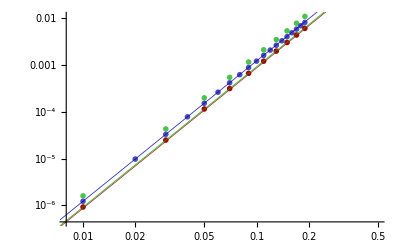

```mathematica
size=0.009;
logInset=Show[ 
ListLogLogPlot[{gap1,gap2,gap3},   FrameStyle ->Directive[Black,15], FrameTicksStyle->Directive[Black,8],(*FrameTicks->None, Frame->False,*)  PlotStyle->  {{ Darker@Blue,Opacity[.7],PointSize[size]},{ Darker@Red,PointSize[size]} ,{ Darker@Green,Opacity[.7],PointSize[size]}    } ,
  PlotRange-> {{0.008,0.5},Automatic } , PlotLegends->  Placed[{   
MaTeX[#,Magnification->.7]&@"\\Delta_{\, \\mathrm{v}}=0.26",
MaTeX[#,Magnification->.7]&@"\\Delta_{\, \\mathrm{v}}=0.26",
MaTeX[#,Magnification->.7]&@"\\Delta_{\, \\mathrm{v}}=0.30"}  ,Scaled[{0.75,0.3}]  ], PlotMarkers->"OpenMarkers", Epilog->Inset[ MaTeX["\\Delta_f =    \\frac{2 \\sqrt{3}}{\\Delta_{\, \\mathrm{v}}^2} \\; h^xh^yh^z",Magnification->.9] ,Scaled[{0.025,0.89}] ,Scaled[{-0.1,0.5}]  ]  ],
LogLogPlot[{  2 √3(Times@@hAngle[0,0])/(0.26)^2 (h/2)^3,  2 √3 Abs[Times@@hAngle[90,0]  ]/(0.26)^2 (h/2)^3 ,  2 √3(Times@@hAngle[0,0])/(0.3)^2 (h/2)^3} ,{h,0.00001,0.85},PlotStyle->{{Darker@Blue,Opacity[.8],Thickness[0.0015]},{Darker@Red,Opacity[.8],Thickness[0.0015]},{Darker@Green,Opacity[.8],Thickness[0.0015]}}]              ]
```

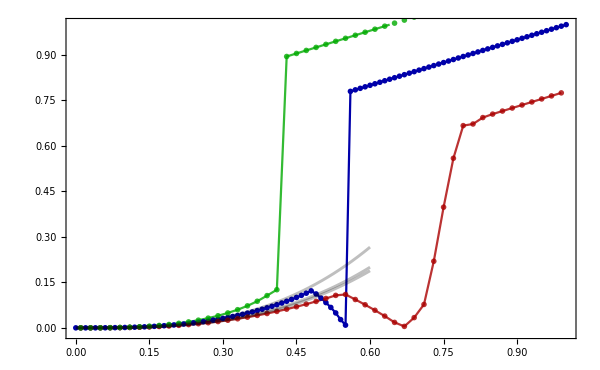

```mathematica
size=0.009;Module[ {En, Disp,L, Nc,J,K,Γ, h ,η, χ0,ω0 ,title, color, j0, L0}, 
title=StringReplace["  ",{"X1"-> ToString[J],"X2"-> ToString[K],"X3"-> ToString[Γ] ,"X4"-> ToString[Norm@h]  }] ;
Show[
 ListPlot[ {gapH1,gapH2,gapH3}  , Joined->True ,  PlotRange-> {-0.015,1} , FrameLabel->{MaTeX["h",Magnification->2] , MaTeX["\\text{Gap } \\; \\Delta_f",Magnification->2] } , Frame->True, PlotMarkers->"OpenMarkers" ,   FrameStyle ->Directive[Black,20], FrameTicksStyle->Directive[Black,15],ImageSize->600,(* GridLines->None,*)  PlotLabel-> Style[MaTeX[title,Magnification->2] ,20 ,Black ] , PlotLegends->  Placed[MaTeX[#,Magnification->1]&/@{"\\Gamma = 0 , \\, \\mathbf{h} \\parallel \\mathbf{c}","\\Gamma = 0 , \\, \\mathbf{h} \\parallel \\mathbf{a}","\\Gamma = 0.1 , \\, \\mathbf{h} \\parallel \\mathbf{c}"} ,Scaled[{0.85,0.5}]  ] ,  PlotStyle->  {{ Darker@Blue,PointSize[size]},{ Darker@Red,Opacity[.8],PointSize[size]} ,{ Darker@Green,Opacity[.8],PointSize[size]} } , Epilog->Inset[logInset,Scaled[{0.23,0.74}],Center,{0.5,Automatic} ]   ]   
,Plot[  {   2 √3(Times@@hAngle[0,0])/(0.26)^2 (h/2)^3,  2 √3 Abs[Times@@hAngle[90,0]  ]/(0.26)^2 (h/2)^3 ,  2 √3(Times@@hAngle[0,0])/(0.3)^2 (h/2)^3} (*1.207 h^3*) ,{h,0.0000001,0.6}, PlotStyle->{{Black,Opacity[.25], Thickness[0.0035 ]}}]           ] ]
```

## Fig 3 a - Phase diagram Γ and h

```mathematica
ClearAll[parameters]; 
                  
		NbName = "705"; 
		Ls = Range[40,40,4]; 				tV={0};	
		steps=500;			      eVs=Table[1700 x, {x,0,0,0.099999}];  
		(* for equally spaced Gamma values *)

		acuracy=12;   
		
		Js={0.};
		Ks={-1.};
		Γs=Table[γ,{γ,-.7,.4,.02}];
		Γs=Join[ Γs[[1;;35]], Γs[[36+1;;-1]] ];
		hV=Table[{h,0,0},{h,0,.6,.02}];
		
		Γs=Join[Table[γ,{γ,0.01,.82,.02}],Table[γ,{γ,-0.01,-.7,-.02}]     ];
		hV= Table[{h,0,0},{h,0.01,1,.02}];
(*
acuracy=11;   		hV=Table[{h,0,0},{h,0.01,1.2,.01}];
Γs=Join[ Table[γ,{γ,0.01,.7,.02}][[1;;14]] ,Table[γ,{γ,-0.01,-.7,-.02}] ];		*)
		 
		hs =Table[  h[[1]]  hAngle[h[[2]],h[[3]]] , {h,hV}];  
		eV0=0;U=2600;JH=300;
		Module[{parameters0,parameters1},
				parameters0=Tuples[{Js,Ks,Γs,hs}];
				parameters1=Tuples[{Js,Ks,Γs,hV}];				parameters={Table[  Flatten[{ parameters0[[i]],parameters1[[i]],{0},{0}},1],  {i,1,Length@parameters0}]}  ];  
		

Γs=Table[γ,{γ,0.01,.7,.02}];
hV=Table[{h,0,0},{h,0.01,1.2,.02}][[51;;-1]];
hs =Table[  h[[1]]  hAngle[h[[2]],h[[3]]] , {h,hV}];  
Module[{parameters0,parameters1},
				parameters0=Tuples[{Js,Ks,Γs,hs}];
				parameters1=Tuples[{Js,Ks,Γs,hV}];				parameters2={Table[  Flatten[{ parameters0[[i]],parameters1[[i]],{0},{0}},1],  {i,1,Length@parameters0}]}  ];  

parameters={  Join[parameters[[1]] ,parameters2[[1]]  ]  };
```

```mathematica
(*{jG,LG,χ0,ω0,ξG,EnG}= loadData[toPath[parameters[[1,1801]],Ls[[1]],acuracy,"free",NbName ]  ];*)
```

```mathematica
WriteString["stdout",StringJoin["[", ToString[   Length[parameters[[1]] ]   ],"]: "]   ] 
AbsoluteTiming[(*
ωH={};χKH={};χcH={};χΓH={};χJH={}; EnKSL={}; EnPP={}; ΔW={}; Wp={};Wp2={};  ωHG={};   ωHG3={};*)
 Do[Module[{L,Nc,J,K, Γ, h,jG,LG,en,ξG,EnG,η=0,l,χ0,ω0, χc,χK,ωM,χJ,χΓ,ωM2,ωA,ωB}, l=1;
If[Mod[p,500,0]==0,    WriteString["stdout",StringJoin[   ToString[ p],"; "]   ]    ];
L=Ls[[l]];Nc=L^2;
{J,K, Γ, h}=parameters[[1,p]][[1;;4]]; h=h+10^-7 hc;
{jG,LG,χ0,ω0,ξG,EnG}= loadData[toPath[parameters[[1,p]],L,acuracy,"free",NbName ]  ];

(*χc=1/3( χ0[[1]][[1,1]]   + χ0[[2]][[1,1]]+χ0[[3]][[1,1]]); *)
χJ=1/6( χ0[[1]][[3,3]]+χ0[[1]][[4,4]] + χ0[[2]][[2,2]]+ χ0[[2]][[4,4]]+χ0[[3]][[2,2]] +χ0[[3]][[3,3]]   );
χK=1/3( χ0[[1]][[2,2]]   + χ0[[2]][[3,3]]+χ0[[3]][[4,4]] - 3χJ );
(*χΓ=1/6( χ0[[1]][[3,4]]+χ0[[1]][[4,3]] + χ0[[2]][[2,4]]+ χ0[[2]][[4,2]]+χ0[[3]][[2,3]] +χ0[[3]][[3,2]]   );
ωM= 1/(2Norm[h]+10^-9) ( h.{ω0[[1]][[2,1]],ω0[[1]][[3,1]],ω0[[1]][[4,1]]}   + h.{ω0[[2]][[2,1]],ω0[[2]][[3,1]],ω0[[2]][[4,1]]}   );


ωA={ω0[[1]][[2,1]],ω0[[1]][[3,1]],ω0[[1]][[4,1]]};
ωB={ω0[[2]][[2,1]],ω0[[2]][[3,1]],ω0[[2]][[4,1]]} ;

Module[{enKSL,enPP,ω=ω0,χPP=0χ0,ωPP,heff},
heff={   h[[1]]-K  ω⟦2,2,1⟧-3J  ω⟦2,2,1⟧ -Γ ω⟦2,4,1⟧ -Γ  ω⟦2,3,1⟧ 
,h⟦2⟧-K ω⟦2,3,1⟧-3J ω⟦2,3,1⟧ -Γ ω⟦2,2,1⟧ -Γ ω⟦2,4,1⟧  
,h⟦3⟧-K  ω⟦2,4,1⟧-3J ω⟦2,4,1⟧ - Γ  ω⟦2,3,1⟧ -Γ ω⟦2,2,1⟧ 
} +1/3 hc 10^-11;
ωM2= (h.(heff-2h))/(2Norm[h]+10^-11); 
ωM2= 1/(2Norm[h]+2 10^-11) (    heff.{ω0[[1]][[2,1]],ω0[[1]][[3,1]],ω0[[1]][[4,1]]}   + heff.{ω0[[2]][[2,1]],ω0[[2]][[3,1]],ω0[[2]][[4,1]]}     );  
(*
ωPP=Table[ⅈ IdentityMatrix[4]+Sum[ Gmat[[γ]] Chop[heff[[γ]]/Norm[heff]  ] , {γ,1,3}],{σ,1,2}];
	enKSL=EnMomentum[J,K,Γ,h,χ0,ω0,0.46];
	EnKSL={EnKSL,{Norm[h],Γ,Total@enKSL,Chop[Abs[χK],10^-2]} };
	enPP=EnMomentum[J,K,Γ,h,χPP,ωPP,0];
	EnPP={EnPP,{Norm[h],Γ,Total@enPP,0} };
*)];*)
χKH={χKH,{Norm[h],Γ,Abs@χK}};(*
If[ (EnG[[4,-1,2]]<10^-7)∧(EnG[[4,-1,1]]<400),
ΔW={ΔW,{Norm[h],Γ,EnG[[5,-1,2]]  } };
ωHG={ωHG,{Norm[h],Γ,Norm[ωA.hc]  } };
ωHG3={ωHG3,{Norm[h],Γ,Norm[ωA]  } };
χKH={χKH,{Norm[h],Γ,Abs@χK} };
Wp={Wp,{Norm[h],Γ,Abs[ χ0[[1]][[2,2]]  χ0[[2]][[3,3]]χ0[[3]][[4,4]] ]} };(*
Wp2={Wp2,{Norm[h],Γ,(Abs@χK)^3} };*),
ΔW={ΔW,{Norm[h],Γ,∞} };
ωHG={ωHG,{Norm[h],Γ,∞ } };
ωHG3={ωHG3,{Norm[h],Γ,∞  } };
χKH={χKH,{Norm[h],Γ,∞ } };
Wp={Wp,{Norm[h],Γ,∞ } };
]*)
(* AppendTo[ωH,{h,Γ,ωM }];  AppendTo[χcH,{h,Γ,χc}]; AppendTo[χΓH,{h,Γ,χΓ}];  AppendTo[χJH,{h,Γ,χJ}];  *)            
 ]; , {p,1,Length[parameters[[1]] ]    } ];
χKH=Partition[Flatten@χKH,3];(*
ωHG=Partition[Flatten@ωHG,3];
ωHG3=Partition[Flatten@ωHG3,3];
Wp=Partition[Flatten@Wp,3];(*
Wp2=Partition[Flatten@Wp2,3];*)
ΔW=Partition[Flatten@ΔW,3];*)
(*
EnKSL=Partition[Flatten@EnKSL,4];
EnPP=Partition[Flatten@EnPP,4];
*)
]
```

[4150]: 500; 1000; 1500; 2000; 2500; 3000; 3500; 4000;

{7.29246,Null}

```mathematica
AbsoluteTiming[(*
phaseTransition={};en={};*)
 Do[Module[{L,Nc,J,K, Γ, h,jG,LG,ξG,EnG,η=0,l,χ0,ω0, χc,χK,ωM,χJ,χΓ,ωM2,ωA,ωB,En}, l=1;
If[Mod[p,500,0]==0,    WriteString["stdout",StringJoin[   ToString[ p],"; "]   ]    ];
L=Ls[[l]];Nc=L^2;
{J,K, Γ, h}=parameters[[1,p]][[1;;4]]; h=h+10^-7 hc;
{jG,LG,χ0,ω0,ξG,EnG}= loadData[toPath[parameters[[1,p]],L,acuracy,"free",NbName ]  ];
En=Sort[Abs/@Eigenvalues[ Chop@N@HMFk[ J,K, Γ, h,χ0,ω0,η,{0,0}], 8 ]    ][[1]];
en={en,{Norm[h],Γ,En} };
If[  En<10^-3,phaseTransition={phaseTransition,{Norm[h],Γ} };];
 ]; , {p,1,Length[parameters[[1]] ]    } ];
en=Partition[Flatten@en,3];
phaseTransition=Partition[Flatten@phaseTransition,2];]
```

500; 1000; 1500; 2000; 2500; 3000; 3500; 4000;

{9.94933,Null}

```mathematica
(*jointlist=DeleteDuplicatesBy[
Sort@Join[ Select[ en  , (#[[2]]<.5∧ #[[3]]<.03)&][[;;,1;;2]] (* , Select[ en  , #[[3]]<.002&][[;;,1;;2]] [[1;;-3]]  *) ],First][[3;;-1]]
gapclosing= ListPlot[jointlist
,PlotMarkers->"OpenMarkers",PlotStyle->{{Black,Dotted,Thick,Opacity[.8]}}, Joined->True,PlotRange->All,ImageSize->Large]
Select[ en, #[[2]]==-0.11&][[;;,3]]//ListPlot
Show[ListDensityPlot[en,PlotLegends->Automatic,ColorFunction->"TemperatureMap",PlotRange->{-.5,.7}],gapclosing ]*)
```

```mathematica
(*Module[{list=Select[ΔW,#[[2]]==.13&]},
ListPlot@Table[ {list[[i,1]],list[[i,3]]},{i,1,Length@list}]
]*)
```

```mathematica
(*ListDensityPlot[  Wp ,ImageSize->500,PlotLabel->MaTeX[" W_p  \\qquad \\mathbf{h} \\parallel \\mathbf{c}",Magnification->1.4]    , Frame->True, PlotLegends->Automatic , FrameStyle->Directive[Black,16], FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"h","\\Gamma  "},ColorFunction->"TemperatureMap"  ]*)
```

```mathematica
(*jointlist=
SortBy[#,Last]&@ ((*   DeleteDuplicatesBy[#,Last]&@*)(             ReverseSortBy[#,First]&@ Select[ en  , (#[[3]]<.03)&][[;;,1;;2]]   )           ) ;
gapclosing= ListPlot[jointlist,PlotMarkers->"OpenMarkers",PlotStyle->{{Black,Dotted,Thick,Opacity[.8]}}, Joined->True,PlotRange->All,ImageSize->Large]*)
```

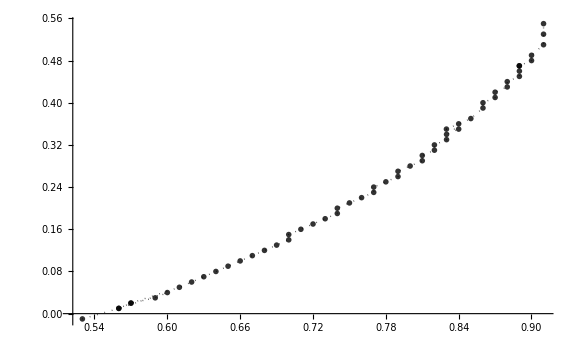

```mathematica
jointlist=Select[ Join[   
SortBy[#,Last]&@ (   DeleteDuplicatesBy[#,Last]&@(             ReverseSortBy[#,First]&@ Select[ en  , (#[[2]]<.05∧ #[[3]]<.024)&][[;;,1;;2]]   )           ) 
, SortBy[#,Last]&@ (   DeleteDuplicatesBy[#,Last]&@(             ReverseSortBy[#,First]&@ Select[ en  , (#[[2]]>-.6∧ #[[3]]<.008)&][[;;,1;;2]]   )           )  
  ], #[[2]]>-.4&] ;
gapclosing= ListPlot[jointlist,PlotMarkers->"OpenMarkers",PlotStyle->{{Black,Dotted,Thick,Opacity[.8]}}, Joined->True,PlotRange->All,ImageSize->Large]
```

{0,1.}

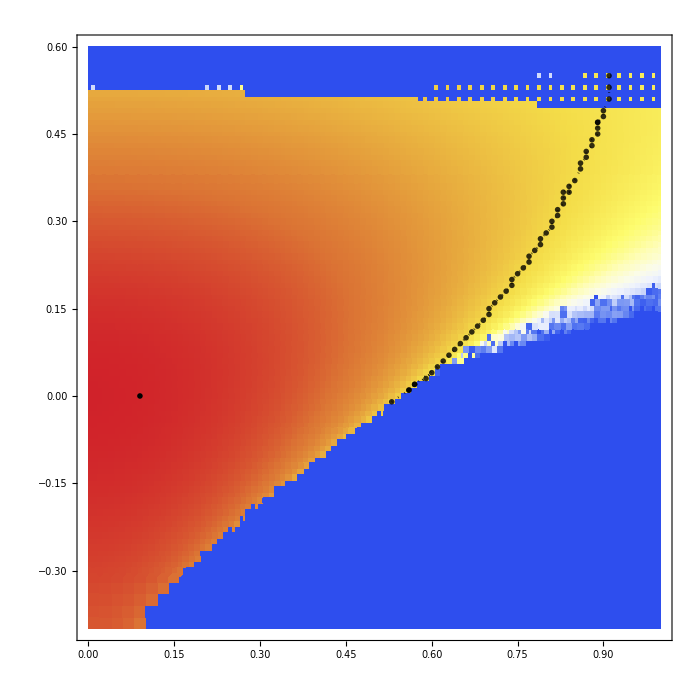

```mathematica
fig3a=Module[{minmax,max,contoursLevels,colors,δ=0,imgs=700,pRange={{0,1},{-.4,.6},{0,1.01}}},
minmax=MinMax@Abs[  χKH[[;;,3]]  ]; Print[minmax];max=N@(Ceiling[minmax[[2]] 100]/100);(*contoursLevels=Table[ (max/10)  x ,{x,1,10}];*)
colors={{0,Lighter@Orange},{0.05,White},(*{0.5-δ,White},{0.5+δ,White},*){1,Darker@Cyan}};
Show[ListDensityPlot[ Select[ Join[ χKH/.(∞->0),{{1.19,-0.69,0.},{1.19,0.8,0.}}], (#[[2]]>=pRange[[2,1]])&], PlotRange-> pRange,
ImageSize->imgs,(*PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}},*)Frame->True, MeshFunctions->{#1 & , #2 & }(*, PlotLabel->MaTeX[" \\mathrm{U}_{\\gamma}^{\\gamma \\gamma}  \\qquad \\mathbf{h} \\parallel \\mathbf{c}",Magnification->2]   *), 
PlotLegends->BarLegend[ "TemperatureMap",None,LegendLabel->MaTeX["\\mathrm{U}_{\\gamma}^{\\gamma \\gamma}\\;\\;   ",Magnification->2],LegendMarkerSize-> {20,300},LabelStyle->{Black,FontSize->20,FontFamily->"Helvetica"}  ] , 
FrameStyle->Directive[Black,20], FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{"h","\\Gamma  "},ColorFunction->"TemperatureMap"(*(Blend[colors,#/ minmax[[2]]]&)  *), ColorFunctionScaling->True,InterpolationOrder->0  (*,Contours->5(*contoursLevels*)*),
Epilog->{Inset[MaTeX["\\textbf{KSL}",Magnification->2.5],{.09,0},Scaled[{.5,.5}]],
(*Inset[MaTeX["\\textbf{PP}",Magnification->2.4],Scaled[{.7,.15}],Scaled[{.5,.5}]]   ,*)
Inset[MaTeX["\\mathrm{(a)}",Magnification->2.4],Scaled[{.12,.93}],Scaled[{.5,.5}]]  }
,ClippingStyle->{{Lighter@Pink,Opacity[.5]}}         ](*,
Plot[  {.52+.045x,-.7+.95Sqrt[x]  },{x,0.015,1.19} , PlotStyle->{{Black,Thickness[0.005],Opacity[.8] }} ]*)
,gapclosing]        ]
```

```mathematica
Module[{Fig3Raster},
Fig3Raster=Rasterize[fig3a,"Image",RasterSize->5000];
Export["C:\\User\\lucas\\Desktop\\Wolfram Mathematica\\PhD-codes\\Figures_PhD\\New2\\fig3a.pdf"  ,Fig3Raster  ];
];
```

```mathematica
(*Module[{minmax,max,contoursLevels,colors,δ=0,imgs=500},
minmax=MinMax@Abs[  ωHG[[;;,3]]  ]; Print[minmax];max=N@(Ceiling[minmax[[2]] 100]/100);(*contoursLevels=Table[ (max/10)  x ,{x,1,10}];*)
colors={{0,Lighter@Orange},{0.05,White},(*{0.5-δ,White},{0.5+δ,White},*){1,Darker@Cyan}};
Show[ListDensityPlot[ Join[ωHG,{{1.19,0.81,0.27},{1.19,-0.69,1}}], 
ImageSize->imgs, PlotRange->{0,1},(*PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}},*)Frame->True, PlotLabel->MaTeX[" \\left< \\sigma \\right> \\cdot \\mathbf{c}    \\qquad \\mathbf{h} \\parallel \\mathbf{c}",Magnification->1.4]   , PlotLegends->Automatic , FrameStyle->Directive[Black,16], FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"h","\\Gamma  "},ColorFunction->(ColorData["TemperatureMap",(1-(#)^(3/5)  )]&),  (*(Blend[colors,#/ minmax[[2]]]&)  *) ColorFunctionScaling->True,InterpolationOrder-> 2  (*,Contours->5(*contoursLevels*)*),
Epilog->{Inset[MaTeX["\\text{KSL}",Magnification->2],Scaled[{.2,.5}],Scaled[{.5,0}]],
Inset[MaTeX["\\text{PP}",Magnification->2],Scaled[{.7,.15}],Scaled[{.5,0}]]  },ClippingStyle->Automatic        ],
Plot[  {.52+.045x,-.7+.95Sqrt[x]  },{x,0.015,1.19} , PlotStyle->{{Black,Thickness[0.005],Opacity[.8] }} ]
]        ]*)
```

```mathematica
Export["C:\\User\\lucas\\Desktop\\Wolfram Mathematica\\PhD-codes\\Magnetization_out_of_plane.pdf"  ,%   ];
```

```mathematica
(*Module[{minmax,max,contoursLevels,colors,δ=0,imgs=500},

minmax=MinMax@Abs[  Wp[[;;,3]]  ];

max=N@(Ceiling[minmax[[2]] 100]/100);
(*contoursLevels=Table[ (max/10)  x ,{x,1,10}];*)
colors={{0,Lighter@Orange},{0.05,White},(*{0.5-δ,White},{0.5+δ,White},*){1,Darker@Cyan}};

{
ListDensityPlot[ Wp, 
ImageSize->imgs,(*PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}},*)Frame->True, PlotLabel->MaTeX[" W_p  \\qquad \\mathbf{h} \\parallel \\mathbf{c}",Magnification->1.4]   , PlotLegends->Automatic , FrameStyle->Directive[Black,16], FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"h","\\Gamma  "},ColorFunction->(Blend[colors,#/ minmax[[2]]]&)  , ColorFunctionScaling->False,InterpolationOrder-> 2  (*,Contours->5(*contoursLevels*)*),
Epilog->{Inset[MaTeX["\\text{KSL}",Magnification->2],Scaled[{.1,.5}],Scaled[{.5,0}]],
Inset[MaTeX["\\text{PP}",Magnification->2],Scaled[{.7,.15}],Scaled[{.5,0}]]  },ClippingStyle->{{Lighter@Pink,Opacity[.5]}}  
] 
}

]*)
```

```mathematica
(*Module[{χK=χKH,minmax,max,contoursLevels,colors,δ=0,imgs=500},

minmax=MinMax@Abs[  χK[[;;,3]] ];

max=N@(Ceiling[minmax[[2]] 100]/100);
(*contoursLevels=Table[ (max/10)  x ,{x,1,10}];*)
colors={{0,Lighter@Orange},{0.05,White},(*{0.5-δ,White},{0.5+δ,White},*){1,Darker@Cyan}};

plotFig3A=ListContourPlot[ χK, 
ImageSize->imgs,(*PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}},*)Frame->True, PlotLabel->MaTeX[" \\mathrm{U}^{\\gamma \\gamma}_\\gamma  = \\left< \\mathrm{i} c^\\gamma_i c^\\gamma_j \\right>  \\quad \\mathbf{h} \\parallel \\mathbf{c}",Magnification->1.4]   , PlotLegends->BarLegend[Automatic,All] , FrameStyle->Directive[Black,16], FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"h","\\Gamma  "},ColorFunction->(Blend[colors,#/ minmax[[2]]]&)  , ColorFunctionScaling->False,InterpolationOrder-> 1  ,Contours->5(*contoursLevels*),
Epilog->{Inset[MaTeX["\\text{KSL}",Magnification->2],Scaled[{.1,.5}],Scaled[{.5,0}]],
Inset[MaTeX["\\text{PP}",Magnification->2],Scaled[{.7,.15}],Scaled[{.5,0}]]  }
] 

]*)
```

```mathematica
(*int=Interpolation[χKH[[1;;-1]] ];
Show[{ContourPlot[int[x,y],{x,0,.6},{y,-.7,.7}]}]*)
```

```mathematica
{min,max}=MinMax@Abs[  ΔW[[;;,3]]  ];
ListDensityPlot[ Join[ΔW,{{1.19,0.81,0},{1.19,-0.69,0}}]   ,ImageSize->500,PlotLabel->MaTeX[" \\mathrm{tr}\\left( \\mathrm{W}^\\mathrm{T} \\mathrm{G}^{\\gamma}\\right)  
= \\left< \\mathrm{i} c^\\gamma_i \\mathrm{G}^{\\gamma} c^\\gamma_i \\right>  \\; , \\quad \\mathbf{h} \\parallel \\mathbf{c}",Magnification->1.4]   , Frame->True, PlotLegends->Automatic , FrameStyle->Directive[Black,16], FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"h","\\Gamma  "},
ColorFunction->"TemperatureMap",ColorFunctionScaling->True,ClippingStyle->Automatic,PlotRange->{0,0.05}  ]
```

```mathematica
Export["C:\\User\\lucas\\Desktop\\Wolfram Mathematica\\PhD-codes\\DeltaW.pdf"  ,%   ];
```

#### line plot

```mathematica
Module[{title,img=700,x=-.03}, title="J=0, \\, K=-1 , \\,   \\mathbf{h}=0.2 \\mathbf{c}";
gK=ListPlot[χKH,Joined->True,PlotMarkers->{"●",Small}, PlotStyle->{Darker[Blue]},Frame->True,FrameStyle->Directive[Black,16],PlotLabel->(MaTeX[#,Magnification->1.6]&)@" ",FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"\\Gamma ","\\text{MF parameters}"},ImageSize->img,PlotLegends->Placed[(MaTeX[#,Magnification->1.3]&)/@{"\\mathrm{U}_{\\!K}\\!=\\mathrm{U}_{\\gamma}^{\\gamma\\gamma}"},{.901+x,.94}],
PlotRange->All,Frame->True,FrameStyle->Directive[Black,16], ImageSize->img,PlotRange->All,GridLines->None];
gc=ListPlot[χcH,Joined->True,PlotMarkers->{"●",Small}, PlotStyle->{Darker[Red]},Frame->True,FrameStyle->Directive[Black,16],PlotLabel->(MaTeX[#,Magnification->1.6]&)@title,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"\\Gamma ","\\text{MF parameters}"},ImageSize->img,PlotLegends->Placed[(MaTeX[#,Magnification->1.3]&)/@{"\\mathrm{U}_{0}=\\mathrm{U}_{\\gamma}^{00}"},{.9+x,.9}],PlotRange->All,Frame->True,FrameStyle->Directive[Black,16], ImageSize->img,PlotRange->All,GridLines->Automatic];
gΓ = ListPlot[χΓH,Joined->True,PlotMarkers->{"●",Small}, PlotStyle->{ Orange },Frame->True,FrameStyle->Directive[Black,16],PlotLabel->(MaTeX[#,Magnification->1.6]&)@title,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"\\Gamma ","\\text{MF parameters}"},ImageSize->img,PlotLegends->Placed[(MaTeX[#,Magnification->1.3]&)/@{"\\mathrm{U}_{\\Gamma}=\\mathrm{U}_{\\gamma}^{\\alpha\\beta}"},{.903+x,.86}],
PlotRange->All,Frame->True,FrameStyle->Directive[Black,16], ImageSize->img,PlotRange->All,GridLines->Automatic];
gJ = ListPlot[χJH,Joined->True,PlotMarkers->{"●",Small}, PlotStyle->{ Orange },Frame->True,FrameStyle->Directive[Black,16],PlotLabel->(MaTeX[#,Magnification->1.6]&)@title,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"\\Gamma ","\\text{MF parameters}"},ImageSize->img,PlotLegends->Placed[(MaTeX[#,Magnification->1.3]&)/@{"\\mathrm{U}_{J}=\\mathrm{U}_{\\gamma}^{\\alpha\\alpha}"},{.9+x,.82}],
PlotRange->All,Frame->True,FrameStyle->Directive[Black,16], ImageSize->img,PlotRange->All,GridLines->Automatic];
gM = ListPlot[ωH,Joined->True,PlotMarkers->{"●",Small}, PlotStyle->{Darker[Green]},Frame->True,FrameStyle->Directive[Black,16],PlotLabel->(MaTeX[#,Magnification->1.6]&)@title,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"\\Gamma ","\\text{MF parameters}"},ImageSize->img,PlotLegends->Placed[(MaTeX[#,Magnification->1.3]&)/@{"\\langle \\sigma \\rangle = \\mathrm{W}^{0\\alpha} \\hat{h}^{\\alpha}"},{.919+x,.82}],
PlotRange->All,Frame->True,FrameStyle->Directive[Black,16], ImageSize->500,PlotRange->All,GridLines->Automatic];
Show[gK,gc,(*gJ,*)gM, gΓ,PlotRange-> { {-0.75,.75},{-1.1,1.1} }  ]
]
```

also, we could insert both Γ and J in the horizontal axis, just changing the plot markers

```mathematica
NbName = "705"; 
		Ls =Range[40,40,2]; 	    tV={0};				hV={{0.001,0,0}};
		steps=600;                                     acuracy=6;                               ΔeV=0.099999;                                           eVs=Table[ 1700 ξ, {ξ,0,0,ΔeV} ] ; 

		Js=Table[j,{j,-1,1,.05}];
		Ks={-1.};
		Γs= {0.};
		hV=Table[{h,0,0},{h,0.2,0.2,.2}];

		ts = Table[ {5x,160,-12x,0,-60},{x,tV}];
		hs =Table[  h[[1]]  hAngle[h[[2]],h[[3]]] , {h,hV}];  
		eV0=0;U=2600;JH=300;

		Module[{parameters0,parameters1},
				parameters0=Tuples[{Js,Ks,Γs,hs}];
				parameters1=Tuples[{Js,Ks,Γs,hV}];
				parameters={Table[  Flatten[{ parameters0[[i]],parameters1[[i]],{0},{0}},1],  {i,1,Length@parameters0}]};
		]
```

```mathematica
ωH2={};χKH2={};χcH2={};χΓH2={};χJH2={};
 Do[Module[{L,Nc,J,K, Γ, h,jG,LG,en,ξG,EnG,η=0,l,χ0,ω0, χc,χK,ωM,χJ,χΓ}, l=1;
L=Ls[[l]];
{J,K, Γ, h}=parameters[[1,p]][[1;;4]];
{jG,LG,χ0,ω0,ξG,EnG}= loadData[toPath[parameters[[1,p]],L,acuracy,"free",NbName ]  ];

χc=1/3( χ0[[1]][[1,1]]   + χ0[[2]][[1,1]]+χ0[[3]][[1,1]]);
χJ=1/6( χ0[[1]][[3,3]]+χ0[[1]][[4,4]] + χ0[[2]][[2,2]]+ χ0[[2]][[4,4]]+χ0[[3]][[2,2]] +χ0[[3]][[3,3]]   ); 
χK=1/3( χ0[[1]][[2,2]]   + χ0[[2]][[3,3]]+χ0[[3]][[4,4]] - 3χJ );
χΓ=1/6( χ0[[1]][[3,4]]+χ0[[1]][[4,3]] + χ0[[2]][[2,4]]+ χ0[[2]][[4,2]]+χ0[[3]][[2,3]] +χ0[[3]][[3,2]]   );
ωM= 1/(2Norm[h]) ( h.{ω0[[1]][[2,1]],ω0[[1]][[3,1]],ω0[[1]][[4,1]]}   + h.{ω0[[2]][[2,1]],ω0[[2]][[3,1]],ω0[[2]][[4,1]]}   );

 AppendTo[ωH2,{Γ,ωM }]; AppendTo[χKH2,{Γ,χK}]; AppendTo[χcH2,{Γ,χc}]; AppendTo[χΓH2,{Γ,χΓ}];  AppendTo[χJH2,{Γ,χJ}];               ];
, {p,1,Length[parameters[[1]] ]} ]
```

```mathematica
Module[{title}, title="J=0, \\, K=-1 , \\,   \\mathbf{h}=0.2 \\mathbf{c}";
g1=ListPlot[{χKH,χcH,χΓH,χJH,ωH},Joined->True,PlotMarkers->"○" ,
 PlotStyle->{Darker[Blue],Darker[Red],Orange,Pink,Darker[Green]},
Frame->True,FrameStyle->Directive[Black,16],
PlotLabel->(MaTeX[#,Magnification->1.6]&)@title,
FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"\\Gamma[\\circ] , \\, J [\triangle] ","\\text{MF parameters}"},
ImageSize->500,
PlotLegends->Placed[(MaTeX[#,Magnification->1.3]&)/@{"\\mathrm{U}_K=\\mathrm{U}_{\\gamma}^{\\gamma\\gamma}","\\mathrm{U}_{0}=\\mathrm{U}_{\\gamma}^{00}","\\mathrm{U}_{\\Gamma}=\\mathrm{U}_{\\gamma}^{\\alpha\\beta}","\\mathrm{U}_{J}=\\mathrm{U}_{\\gamma}^{\\alpha\\alpha}","\\braket{\\sigma}=\\mathrm{W}^{0\\alpha}\\hat{h}^{\\alpha}"},{.08,.9}],
PlotRange->All,Frame->True,FrameStyle->Directive[Black,16], ImageSize->500,PlotRange->All,GridLines->False,
PlotRange-> { -1,1 }];

g2=ListPlot[{χKH2,χcH2,χΓH2,χJH2,ωH2},Joined->True,PlotMarkers->"△" ,
 PlotStyle->{Darker[Blue],Darker[Red],Orange,Pink,Darker[Green]},
Frame->True,FrameStyle->Directive[Black,16],
ImageSize->500,
PlotRange->All,Frame->True,FrameStyle->Directive[Black,16], ImageSize->500,PlotRange->All,GridLines->False,
PlotRange-> { -1,1 }];


Show[g1,g2,PlotRange-> { {-0.72,0.72},{-1,1} }  ]
]
```

#### energy criterea

```mathematica
Module[{J,K,Γ,h,p,jG,LG,χ,ω,ξG,EnG,heff},
p=2050; 
{J,K,Γ,h}=parameters[[1,p]][[1;;4]];
{jG,LG,χ,ω,ξG,EnG}= loadData[toPath[parameters[[1,p]],L,acuracy,"free",NbName ]  ];
heff={   h[[1]]-K  ω⟦2,2,1⟧-3J  ω⟦2,2,1⟧ -2Γ ω⟦2,4,1⟧ -2Γ  ω⟦2,3,1⟧ 
,h⟦2⟧-K ω⟦2,3,1⟧-3J ω⟦2,3,1⟧ -2 Γ ω⟦2,2,1⟧ -2Γ ω⟦2,4,1⟧  
,h⟦3⟧-K  ω⟦2,4,1⟧-3J ω⟦2,4,1⟧ -2 Γ  ω⟦2,3,1⟧ -2Γ ω⟦2,2,1⟧ 
} +10^-11;
MatrixForm@Sum[ Gmat[[γ]] Chop[heff[[γ]]/Norm[heff] ], {γ,1,3}]  
]
```

```mathematica
PHdiagram=Table[ Join[EnPP[[i,1;;2]],{If[ EnKSL[[i,4]]<10^-2,0,
		If[Chop[EnKSL[[i,3]]-EnPP[[i,3]]]<10^-3,0.5,
				If[EnKSL[[i,3]]>EnPP[[i,3]],0.5,1 ] ]   ] }  ]  , {i,1,Length[EnPP]}];
```

```mathematica
Module[{colors,contoursLevels,δ=0.01,min,max},
{max,min}=-MinMax@Join[ {EnKSL[[;;,3]],EnPP[[;;,3]]} ];
(*max=minmax[[1]];*)
contoursLevels=Table[ -(min+((max-min)/9)  x ),{x,1,10}];

colors={{0,Darker@Blue},{0.5-δ,White},{1,Darker@Red}};
ListContourPlot[  #,PlotLegends->Automatic,ImageSize->400,ColorFunctionScaling->False,ColorFunction->(Blend[colors,(-#-min)/(max-min) ]&)  , Contours->contoursLevels ]&/@ {EnKSL[[;;,1;;3]],EnPP[[;;,1;;3]]}
]
```

## Fig 3 a.2 - Phase diagram Γ and h

```mathematica
ClearAll[parameters]; 
                  
		NbName = "705"; 
		Ls = Range[40,40,4]; 				tV={0};	
		steps=500;			      eVs=Table[1700 x, {x,0,0,0.099999}];  
		(* for equally spaced Gamma values *)

(*		acuracy=12;   
		
		Js={0.};
		Ks={-1.};
		Γs=Table[γ,{γ,-.7,.7,.02}];
		Γs=Join[ Γs[[1;;35]], Γs[[36+1;;-1]] ];
		hV=Table[{h,0,0},{h,0,.6,.02}];
		
		Γs=Join[Table[γ,{γ,0.01,.82,.02}],Table[γ,{γ,-0.01,-.7,-.02}]     ];
		hV= Table[{h,0,0},{h,0.01,1,.02}];
(*
acuracy=11;   		hV=Table[{h,0,0},{h,0.01,1.2,.01}];
Γs=Join[ Table[γ,{γ,0.01,.7,.02}][[1;;14]] ,Table[γ,{γ,-0.01,-.7,-.02}] ];		*)
		 
		hs =Table[  h[[1]]  hAngle[h[[2]],h[[3]]] , {h,hV}];  
		eV0=0;U=2600;JH=300;
		Module[{parameters0,parameters1},
				parameters0=Tuples[{Js,Ks,Γs,hs}];
				parameters1=Tuples[{Js,Ks,Γs,hV}];				parameters={Table[  Flatten[{ parameters0[[i]],parameters1[[i]],{0},{0}},1],  {i,1,Length@parameters0}]}  ];  
		

Γs=Table[γ,{γ,0.01,.7,.02}];
hV=Table[{h,0,0},{h,0.01,1.2,.02}][[51;;-1]];
hs =Table[  h[[1]]  hAngle[h[[2]],h[[3]]] , {h,hV}];  
Module[{parameters0,parameters1},
				parameters0=Tuples[{Js,Ks,Γs,hs}];
				parameters1=Tuples[{Js,Ks,Γs,hV}];				parameters2={Table[  Flatten[{ parameters0[[i]],parameters1[[i]],{0},{0}},1],  {i,1,Length@parameters0}]}  ];  

parameters={  Join[parameters[[1]] ,parameters2[[1]]  ]  };

*)
		
		acuracy=6.1; 
		Γs=round@Drop[Table[x,{x,-.3,.6,.01}],{-23}];      (* MF did not congerved for Γ=0.38 and h >= 0.8; run code again with larger step *)
		Ks={-1.};
		Js={0.};
		hV=round@Table[{x,0,0},{x,0.0001,1.21,.01}];
		
		steps=500;  
		ts = Table[ {5x,160,-12x,0,-60},{x,tV}];
		hs = Table[  h[[1]]  hAngle[h[[2]],h[[3]]] , {h,hV}];  
		eVs= Table[1700 x, {x,0,0,0.099999}];   

		Module[{parameters0,parameters1},
				parameters0=Tuples[{Js,Ks,Γs,hs}];
				parameters1=Tuples[{Js,Ks,Γs,hV}];
				parameters={Table[  Flatten[{ parameters0[[i]],parameters1[[i]],{0},{0}},1],  {i,1,Length@parameters0}]}  ];
```

```mathematica
(*{jG,LG,χ0,ω0,ξG,EnG}= loadData[toPath[parameters[[1,1801]],Ls[[1]],acuracy,"free",NbName ]  ];*)
```

```mathematica
WriteString["stdout",StringJoin["[", ToString[   Length[parameters[[1]] ]   ],"]: "]   ] 
AbsoluteTiming[
ωH={};χKH={};χcH={};χΓH={};χJH={}; EnKSL={}; EnPP={}; ΔW={}; Wp={};Wp2={};  ωHG={};   ωHG3={};
 Do[Module[{L,Nc,J,K, Γ, h,jG,LG,en,ξG,EnG,η=0,l,χ0,ω0, χc,χK,ωM,χJ,χΓ,ωM2,ωA,ωB}, l=1;
If[Mod[p,500,0]==0,    WriteString["stdout",StringJoin[   ToString[ p],"; "]   ]    ];
L=Ls[[l]];Nc=L^2;
{J,K, Γ, h}=parameters[[1,p]][[1;;4]]; h=h+10^-7 hc;
{jG,LG,χ0,ω0,ξG,EnG}= loadData[toPath[parameters[[1,p]],L,acuracy,"free",NbName ]  ];
χJ=1/6( χ0[[1]][[3,3]]+χ0[[1]][[4,4]] + χ0[[2]][[2,2]]+ χ0[[2]][[4,4]]+χ0[[3]][[2,2]] +χ0[[3]][[3,3]]   );
χK=1/3( χ0[[1]][[2,2]]   + χ0[[2]][[3,3]]+χ0[[3]][[4,4]] - 3χJ );
χKH={χKH,{Norm[h],Γ,Abs@χK}};     
 ]; , {p,1,Length[parameters[[1]] ]    } ];
χKH=Partition[Flatten@χKH,3];
]
```

[10890]: 500; 1000; 1500; 2000; 2500; 3000; 3500; 4000; 4500; 5000; 5500; 6000; 6500; 7000; 7500; 8000; 8500; 9000; 9500; 10000; 10500;

{14.0925,Null}

```mathematica
AbsoluteTiming[
phaseTransition={};en={};
 Do[Module[{L,Nc,J,K, Γ, h,jG,LG,ξG,EnG,η=0,l,χ0,ω0, χc,χK,ωM,χJ,χΓ,ωM2,ωA,ωB,En}, l=1;
If[Mod[p,500,0]==0,    WriteString["stdout",StringJoin[   ToString[ p],"; "]   ]    ];
L=Ls[[l]];Nc=L^2;
{J,K, Γ, h}=parameters[[1,p]][[1;;4]]; h=h+10^-7 hc;
{jG,LG,χ0,ω0,ξG,EnG}= loadData[toPath[parameters[[1,p]],L,acuracy,"free",NbName ]  ];
En=Sort[Abs/@Eigenvalues[ Chop@N@HMFk[ J,K, Γ, h,χ0,ω0,η,{0,0}], 8 ]    ][[1]];
en={en,{Norm[h],Γ,En} };
If[  En<10^-3,phaseTransition={phaseTransition,{Norm[h],Γ} };];
 ]; , {p,1,Length[parameters[[1]] ]    } ];
en=Partition[Flatten@en,3];
phaseTransition=Partition[Flatten@phaseTransition,2];]
```

500; 1000; 1500; 2000; 2500; 3000; 3500; 4000; 4500; 5000; 5500; 6000; 6500; 7000; 7500; 8000; 8500; 9000; 9500; 10000; 10500;

{240.037,Null}

```mathematica
(*jointlist=DeleteDuplicatesBy[
Sort@Join[ Select[ en  , (#[[2]]<.5∧ #[[3]]<.03)&][[;;,1;;2]] (* , Select[ en  , #[[3]]<.002&][[;;,1;;2]] [[1;;-3]]  *) ],First][[3;;-1]]
gapclosing= ListPlot[jointlist
,PlotMarkers->"OpenMarkers",PlotStyle->{{Black,Dotted,Thick,Opacity[.8]}}, Joined->True,PlotRange->All,ImageSize->Large]
Select[ en, #[[2]]==-0.11&][[;;,3]]//ListPlot
Show[ListDensityPlot[en,PlotLegends->Automatic,ColorFunction->"TemperatureMap",PlotRange->{-.5,.7}],gapclosing ]*)
```

```mathematica
(*Module[{list=Select[ΔW,#[[2]]==.13&]},
ListPlot@Table[ {list[[i,1]],list[[i,3]]},{i,1,Length@list}]
]*)
```

```mathematica
(*ListDensityPlot[  Wp ,ImageSize->500,PlotLabel->MaTeX[" W_p  \\qquad \\mathbf{h} \\parallel \\mathbf{c}",Magnification->1.4]    , Frame->True, PlotLegends->Automatic , FrameStyle->Directive[Black,16], FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"h","\\Gamma  "},ColorFunction->"TemperatureMap"  ]*)
```

```mathematica
(*jointlist=
SortBy[#,Last]&@ ((*   DeleteDuplicatesBy[#,Last]&@*)(             ReverseSortBy[#,First]&@ Select[ en  , (#[[3]]<.03)&][[;;,1;;2]]   )           ) ;
gapclosing= ListPlot[jointlist,PlotMarkers->"OpenMarkers",PlotStyle->{{Black,Dotted,Thick,Opacity[.8]}}, Joined->True,PlotRange->All,ImageSize->Large]*)
```

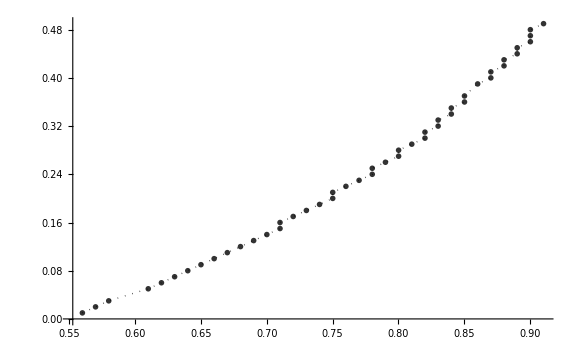

```mathematica
jointlist=Select[ 
 SortBy[#,Last]&@ (   DeleteDuplicatesBy[#,Last]&@(             ReverseSortBy[#,First]&@ Select[ en  , (  #[[3]]<.01)&][[;;,1;;2]]   )           )  
  , #[[2]]>-.4&] ;
gapclosing= ListPlot[jointlist,PlotMarkers->"OpenMarkers",PlotStyle->{{Black,Dotted,Thick,Opacity[.8]}}, Joined->True,PlotRange->All,ImageSize->Large]
```

{0,1.}

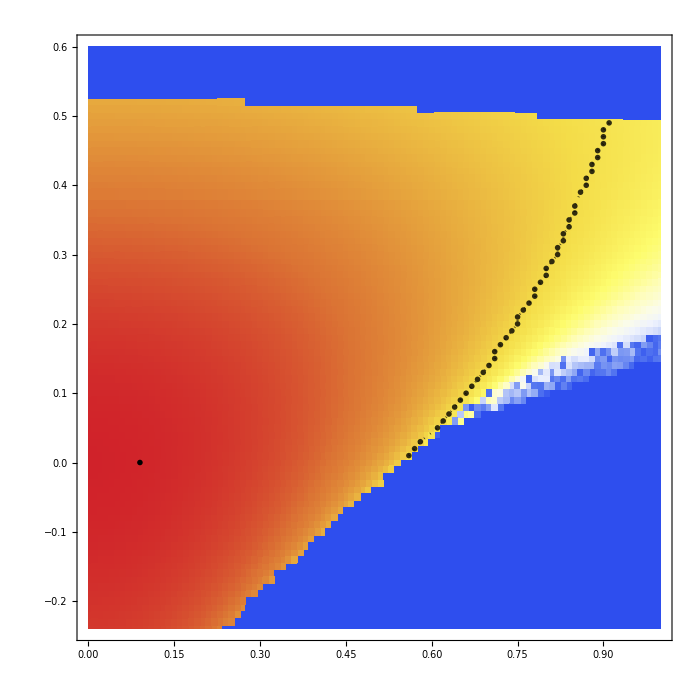

```mathematica
fig3a=Module[{minmax,max,contoursLevels,colors,δ=0,imgs=700,pRange={{0,1},{-.24,.6},{0,1.01}}},
minmax=MinMax@Abs[  χKH[[;;,3]]  ]; Print[minmax];max=N@(Ceiling[minmax[[2]] 100]/100);(*contoursLevels=Table[ (max/10)  x ,{x,1,10}];*)
colors={{0,Lighter@Orange},{0.05,White},(*{0.5-δ,White},{0.5+δ,White},*){1,Darker@Cyan}};
Show[ListDensityPlot[ Select[ Join[ χKH/.(∞->0),{{1.19,-0.69,0.},{1.19,0.8,0.}}], (#[[2]]>=pRange[[2,1]])&], PlotRange-> pRange,
ImageSize->imgs,Frame->True, MeshFunctions->{#1 & , #2 & } , 
PlotLegends->BarLegend[ "TemperatureMap",None,LegendLabel->MaTeX["\\mathrm{U}_{\\gamma}^{\\gamma \\gamma}\\;\\;   ",Magnification->2],LegendMarkerSize-> {20,300},LabelStyle->{Black,FontSize->20,FontFamily->"Helvetica"}  ] , 
FrameStyle->Directive[Black,20], FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{"h","\\Gamma  "},ColorFunction->"TemperatureMap"(*(Blend[colors,#/ minmax[[2]]]&)  *), ColorFunctionScaling->True,InterpolationOrder->0  (*,Contours->5(*contoursLevels*)*),
Epilog->{Inset[MaTeX["\\textbf{KSL}",Magnification->2.5],{.09,0},Scaled[{.5,.5}]],
(*Inset[MaTeX["\\textbf{PP}",Magnification->2.4],Scaled[{.7,.15}],Scaled[{.5,.5}]]   ,*)
Inset[MaTeX["\\mathrm{(a)}",Magnification->2.4],Scaled[{.12,.93}],Scaled[{.5,.5}]]  }
,ClippingStyle->{{Lighter@Pink,Opacity[.5]}}         ](*,
Plot[  {.52+.045x,-.7+.95Sqrt[x]  },{x,0.015,1.19} , PlotStyle->{{Black,Thickness[0.005],Opacity[.8] }} ]*)
,gapclosing]        ]
```

```mathematica
Module[{Fig3Raster},
Fig3Raster=Rasterize[fig3a,"Image",RasterSize->5000];
Export["C:\\User\\lucas\\Desktop\\Wolfram Mathematica\\PhD-codes\\Figures_PhD\\New3\\fig3a(2).pdf"  ,Fig3Raster  ];
];
```

```mathematica
(*Module[{minmax,max,contoursLevels,colors,δ=0,imgs=500},
minmax=MinMax@Abs[  ωHG[[;;,3]]  ]; Print[minmax];max=N@(Ceiling[minmax[[2]] 100]/100);(*contoursLevels=Table[ (max/10)  x ,{x,1,10}];*)
colors={{0,Lighter@Orange},{0.05,White},(*{0.5-δ,White},{0.5+δ,White},*){1,Darker@Cyan}};
Show[ListDensityPlot[ Join[ωHG,{{1.19,0.81,0.27},{1.19,-0.69,1}}], 
ImageSize->imgs, PlotRange->{0,1},(*PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}},*)Frame->True, PlotLabel->MaTeX[" \\left< \\sigma \\right> \\cdot \\mathbf{c}    \\qquad \\mathbf{h} \\parallel \\mathbf{c}",Magnification->1.4]   , PlotLegends->Automatic , FrameStyle->Directive[Black,16], FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"h","\\Gamma  "},ColorFunction->(ColorData["TemperatureMap",(1-(#)^(3/5)  )]&),  (*(Blend[colors,#/ minmax[[2]]]&)  *) ColorFunctionScaling->True,InterpolationOrder-> 2  (*,Contours->5(*contoursLevels*)*),
Epilog->{Inset[MaTeX["\\text{KSL}",Magnification->2],Scaled[{.2,.5}],Scaled[{.5,0}]],
Inset[MaTeX["\\text{PP}",Magnification->2],Scaled[{.7,.15}],Scaled[{.5,0}]]  },ClippingStyle->Automatic        ],
Plot[  {.52+.045x,-.7+.95Sqrt[x]  },{x,0.015,1.19} , PlotStyle->{{Black,Thickness[0.005],Opacity[.8] }} ]
]        ]*)
```

```mathematica
Export["C:\\User\\lucas\\Desktop\\Wolfram Mathematica\\PhD-codes\\Magnetization_out_of_plane.pdf"  ,%   ];
```

```mathematica
(*Module[{minmax,max,contoursLevels,colors,δ=0,imgs=500},

minmax=MinMax@Abs[  Wp[[;;,3]]  ];

max=N@(Ceiling[minmax[[2]] 100]/100);
(*contoursLevels=Table[ (max/10)  x ,{x,1,10}];*)
colors={{0,Lighter@Orange},{0.05,White},(*{0.5-δ,White},{0.5+δ,White},*){1,Darker@Cyan}};

{
ListDensityPlot[ Wp, 
ImageSize->imgs,(*PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}},*)Frame->True, PlotLabel->MaTeX[" W_p  \\qquad \\mathbf{h} \\parallel \\mathbf{c}",Magnification->1.4]   , PlotLegends->Automatic , FrameStyle->Directive[Black,16], FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"h","\\Gamma  "},ColorFunction->(Blend[colors,#/ minmax[[2]]]&)  , ColorFunctionScaling->False,InterpolationOrder-> 2  (*,Contours->5(*contoursLevels*)*),
Epilog->{Inset[MaTeX["\\text{KSL}",Magnification->2],Scaled[{.1,.5}],Scaled[{.5,0}]],
Inset[MaTeX["\\text{PP}",Magnification->2],Scaled[{.7,.15}],Scaled[{.5,0}]]  },ClippingStyle->{{Lighter@Pink,Opacity[.5]}}  
] 
}

]*)
```

```mathematica
(*Module[{χK=χKH,minmax,max,contoursLevels,colors,δ=0,imgs=500},

minmax=MinMax@Abs[  χK[[;;,3]] ];

max=N@(Ceiling[minmax[[2]] 100]/100);
(*contoursLevels=Table[ (max/10)  x ,{x,1,10}];*)
colors={{0,Lighter@Orange},{0.05,White},(*{0.5-δ,White},{0.5+δ,White},*){1,Darker@Cyan}};

plotFig3A=ListContourPlot[ χK, 
ImageSize->imgs,(*PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}},*)Frame->True, PlotLabel->MaTeX[" \\mathrm{U}^{\\gamma \\gamma}_\\gamma  = \\left< \\mathrm{i} c^\\gamma_i c^\\gamma_j \\right>  \\quad \\mathbf{h} \\parallel \\mathbf{c}",Magnification->1.4]   , PlotLegends->BarLegend[Automatic,All] , FrameStyle->Directive[Black,16], FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"h","\\Gamma  "},ColorFunction->(Blend[colors,#/ minmax[[2]]]&)  , ColorFunctionScaling->False,InterpolationOrder-> 1  ,Contours->5(*contoursLevels*),
Epilog->{Inset[MaTeX["\\text{KSL}",Magnification->2],Scaled[{.1,.5}],Scaled[{.5,0}]],
Inset[MaTeX["\\text{PP}",Magnification->2],Scaled[{.7,.15}],Scaled[{.5,0}]]  }
] 

]*)
```

```mathematica
(*int=Interpolation[χKH[[1;;-1]] ];
Show[{ContourPlot[int[x,y],{x,0,.6},{y,-.7,.7}]}]*)
```

```mathematica
{min,max}=MinMax@Abs[  ΔW[[;;,3]]  ];
ListDensityPlot[ Join[ΔW,{{1.19,0.81,0},{1.19,-0.69,0}}]   ,ImageSize->500,PlotLabel->MaTeX[" \\mathrm{tr}\\left( \\mathrm{W}^\\mathrm{T} \\mathrm{G}^{\\gamma}\\right)  
= \\left< \\mathrm{i} c^\\gamma_i \\mathrm{G}^{\\gamma} c^\\gamma_i \\right>  \\; , \\quad \\mathbf{h} \\parallel \\mathbf{c}",Magnification->1.4]   , Frame->True, PlotLegends->Automatic , FrameStyle->Directive[Black,16], FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"h","\\Gamma  "},
ColorFunction->"TemperatureMap",ColorFunctionScaling->True,ClippingStyle->Automatic,PlotRange->{0,0.05}  ]
```

```mathematica
Export["C:\\User\\lucas\\Desktop\\Wolfram Mathematica\\PhD-codes\\DeltaW.pdf"  ,%   ];
```

#### line plot

```mathematica
Module[{title,img=700,x=-.03}, title="J=0, \\, K=-1 , \\,   \\mathbf{h}=0.2 \\mathbf{c}";
gK=ListPlot[χKH,Joined->True,PlotMarkers->{"●",Small}, PlotStyle->{Darker[Blue]},Frame->True,FrameStyle->Directive[Black,16],PlotLabel->(MaTeX[#,Magnification->1.6]&)@" ",FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"\\Gamma ","\\text{MF parameters}"},ImageSize->img,PlotLegends->Placed[(MaTeX[#,Magnification->1.3]&)/@{"\\mathrm{U}_{\\!K}\\!=\\mathrm{U}_{\\gamma}^{\\gamma\\gamma}"},{.901+x,.94}],
PlotRange->All,Frame->True,FrameStyle->Directive[Black,16], ImageSize->img,PlotRange->All,GridLines->None];
gc=ListPlot[χcH,Joined->True,PlotMarkers->{"●",Small}, PlotStyle->{Darker[Red]},Frame->True,FrameStyle->Directive[Black,16],PlotLabel->(MaTeX[#,Magnification->1.6]&)@title,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"\\Gamma ","\\text{MF parameters}"},ImageSize->img,PlotLegends->Placed[(MaTeX[#,Magnification->1.3]&)/@{"\\mathrm{U}_{0}=\\mathrm{U}_{\\gamma}^{00}"},{.9+x,.9}],PlotRange->All,Frame->True,FrameStyle->Directive[Black,16], ImageSize->img,PlotRange->All,GridLines->Automatic];
gΓ = ListPlot[χΓH,Joined->True,PlotMarkers->{"●",Small}, PlotStyle->{ Orange },Frame->True,FrameStyle->Directive[Black,16],PlotLabel->(MaTeX[#,Magnification->1.6]&)@title,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"\\Gamma ","\\text{MF parameters}"},ImageSize->img,PlotLegends->Placed[(MaTeX[#,Magnification->1.3]&)/@{"\\mathrm{U}_{\\Gamma}=\\mathrm{U}_{\\gamma}^{\\alpha\\beta}"},{.903+x,.86}],
PlotRange->All,Frame->True,FrameStyle->Directive[Black,16], ImageSize->img,PlotRange->All,GridLines->Automatic];
gJ = ListPlot[χJH,Joined->True,PlotMarkers->{"●",Small}, PlotStyle->{ Orange },Frame->True,FrameStyle->Directive[Black,16],PlotLabel->(MaTeX[#,Magnification->1.6]&)@title,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"\\Gamma ","\\text{MF parameters}"},ImageSize->img,PlotLegends->Placed[(MaTeX[#,Magnification->1.3]&)/@{"\\mathrm{U}_{J}=\\mathrm{U}_{\\gamma}^{\\alpha\\alpha}"},{.9+x,.82}],
PlotRange->All,Frame->True,FrameStyle->Directive[Black,16], ImageSize->img,PlotRange->All,GridLines->Automatic];
gM = ListPlot[ωH,Joined->True,PlotMarkers->{"●",Small}, PlotStyle->{Darker[Green]},Frame->True,FrameStyle->Directive[Black,16],PlotLabel->(MaTeX[#,Magnification->1.6]&)@title,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"\\Gamma ","\\text{MF parameters}"},ImageSize->img,PlotLegends->Placed[(MaTeX[#,Magnification->1.3]&)/@{"\\langle \\sigma \\rangle = \\mathrm{W}^{0\\alpha} \\hat{h}^{\\alpha}"},{.919+x,.82}],
PlotRange->All,Frame->True,FrameStyle->Directive[Black,16], ImageSize->500,PlotRange->All,GridLines->Automatic];
Show[gK,gc,(*gJ,*)gM, gΓ,PlotRange-> { {-0.75,.75},{-1.1,1.1} }  ]
]
```

also, we could insert both Γ and J in the horizontal axis, just changing the plot markers

```mathematica
NbName = "705"; 
		Ls =Range[40,40,2]; 	    tV={0};				hV={{0.001,0,0}};
		steps=600;                                     acuracy=6;                               ΔeV=0.099999;                                           eVs=Table[ 1700 ξ, {ξ,0,0,ΔeV} ] ; 

		Js=Table[j,{j,-1,1,.05}];
		Ks={-1.};
		Γs= {0.};
		hV=Table[{h,0,0},{h,0.2,0.2,.2}];

		ts = Table[ {5x,160,-12x,0,-60},{x,tV}];
		hs =Table[  h[[1]]  hAngle[h[[2]],h[[3]]] , {h,hV}];  
		eV0=0;U=2600;JH=300;

		Module[{parameters0,parameters1},
				parameters0=Tuples[{Js,Ks,Γs,hs}];
				parameters1=Tuples[{Js,Ks,Γs,hV}];
				parameters={Table[  Flatten[{ parameters0[[i]],parameters1[[i]],{0},{0}},1],  {i,1,Length@parameters0}]};
		]
```

```mathematica
ωH2={};χKH2={};χcH2={};χΓH2={};χJH2={};
 Do[Module[{L,Nc,J,K, Γ, h,jG,LG,en,ξG,EnG,η=0,l,χ0,ω0, χc,χK,ωM,χJ,χΓ}, l=1;
L=Ls[[l]];
{J,K, Γ, h}=parameters[[1,p]][[1;;4]];
{jG,LG,χ0,ω0,ξG,EnG}= loadData[toPath[parameters[[1,p]],L,acuracy,"free",NbName ]  ];

χc=1/3( χ0[[1]][[1,1]]   + χ0[[2]][[1,1]]+χ0[[3]][[1,1]]);
χJ=1/6( χ0[[1]][[3,3]]+χ0[[1]][[4,4]] + χ0[[2]][[2,2]]+ χ0[[2]][[4,4]]+χ0[[3]][[2,2]] +χ0[[3]][[3,3]]   ); 
χK=1/3( χ0[[1]][[2,2]]   + χ0[[2]][[3,3]]+χ0[[3]][[4,4]] - 3χJ );
χΓ=1/6( χ0[[1]][[3,4]]+χ0[[1]][[4,3]] + χ0[[2]][[2,4]]+ χ0[[2]][[4,2]]+χ0[[3]][[2,3]] +χ0[[3]][[3,2]]   );
ωM= 1/(2Norm[h]) ( h.{ω0[[1]][[2,1]],ω0[[1]][[3,1]],ω0[[1]][[4,1]]}   + h.{ω0[[2]][[2,1]],ω0[[2]][[3,1]],ω0[[2]][[4,1]]}   );

 AppendTo[ωH2,{Γ,ωM }]; AppendTo[χKH2,{Γ,χK}]; AppendTo[χcH2,{Γ,χc}]; AppendTo[χΓH2,{Γ,χΓ}];  AppendTo[χJH2,{Γ,χJ}];               ];
, {p,1,Length[parameters[[1]] ]} ]
```

```mathematica
Module[{title}, title="J=0, \\, K=-1 , \\,   \\mathbf{h}=0.2 \\mathbf{c}";
g1=ListPlot[{χKH,χcH,χΓH,χJH,ωH},Joined->True,PlotMarkers->"○" ,
 PlotStyle->{Darker[Blue],Darker[Red],Orange,Pink,Darker[Green]},
Frame->True,FrameStyle->Directive[Black,16],
PlotLabel->(MaTeX[#,Magnification->1.6]&)@title,
FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"\\Gamma[\\circ] , \\, J [\triangle] ","\\text{MF parameters}"},
ImageSize->500,
PlotLegends->Placed[(MaTeX[#,Magnification->1.3]&)/@{"\\mathrm{U}_K=\\mathrm{U}_{\\gamma}^{\\gamma\\gamma}","\\mathrm{U}_{0}=\\mathrm{U}_{\\gamma}^{00}","\\mathrm{U}_{\\Gamma}=\\mathrm{U}_{\\gamma}^{\\alpha\\beta}","\\mathrm{U}_{J}=\\mathrm{U}_{\\gamma}^{\\alpha\\alpha}","\\braket{\\sigma}=\\mathrm{W}^{0\\alpha}\\hat{h}^{\\alpha}"},{.08,.9}],
PlotRange->All,Frame->True,FrameStyle->Directive[Black,16], ImageSize->500,PlotRange->All,GridLines->False,
PlotRange-> { -1,1 }];

g2=ListPlot[{χKH2,χcH2,χΓH2,χJH2,ωH2},Joined->True,PlotMarkers->"△" ,
 PlotStyle->{Darker[Blue],Darker[Red],Orange,Pink,Darker[Green]},
Frame->True,FrameStyle->Directive[Black,16],
ImageSize->500,
PlotRange->All,Frame->True,FrameStyle->Directive[Black,16], ImageSize->500,PlotRange->All,GridLines->False,
PlotRange-> { -1,1 }];


Show[g1,g2,PlotRange-> { {-0.72,0.72},{-1,1} }  ]
]
```

#### energy criterea

```mathematica
Module[{J,K,Γ,h,p,jG,LG,χ,ω,ξG,EnG,heff},
p=2050; 
{J,K,Γ,h}=parameters[[1,p]][[1;;4]];
{jG,LG,χ,ω,ξG,EnG}= loadData[toPath[parameters[[1,p]],L,acuracy,"free",NbName ]  ];
heff={   h[[1]]-K  ω⟦2,2,1⟧-3J  ω⟦2,2,1⟧ -2Γ ω⟦2,4,1⟧ -2Γ  ω⟦2,3,1⟧ 
,h⟦2⟧-K ω⟦2,3,1⟧-3J ω⟦2,3,1⟧ -2 Γ ω⟦2,2,1⟧ -2Γ ω⟦2,4,1⟧  
,h⟦3⟧-K  ω⟦2,4,1⟧-3J ω⟦2,4,1⟧ -2 Γ  ω⟦2,3,1⟧ -2Γ ω⟦2,2,1⟧ 
} +10^-11;
MatrixForm@Sum[ Gmat[[γ]] Chop[heff[[γ]]/Norm[heff] ], {γ,1,3}]  
]
```

```mathematica
PHdiagram=Table[ Join[EnPP[[i,1;;2]],{If[ EnKSL[[i,4]]<10^-2,0,
		If[Chop[EnKSL[[i,3]]-EnPP[[i,3]]]<10^-3,0.5,
				If[EnKSL[[i,3]]>EnPP[[i,3]],0.5,1 ] ]   ] }  ]  , {i,1,Length[EnPP]}];
```

```mathematica
Module[{colors,contoursLevels,δ=0.01,min,max},
{max,min}=-MinMax@Join[ {EnKSL[[;;,3]],EnPP[[;;,3]]} ];
(*max=minmax[[1]];*)
contoursLevels=Table[ -(min+((max-min)/9)  x ),{x,1,10}];

colors={{0,Darker@Blue},{0.5-δ,White},{1,Darker@Red}};
ListContourPlot[  #,PlotLegends->Automatic,ImageSize->400,ColorFunctionScaling->False,ColorFunction->(Blend[colors,(-#-min)/(max-min) ]&)  , Contours->contoursLevels ]&/@ {EnKSL[[;;,1;;3]],EnPP[[;;,1;;3]]}
]
```

## definition 804

#### Constants

```mathematica
(*ReverseSort[list_]:=Reverse@Sort@list;*)
```

```mathematica
one[i_,j_,N_]:= SparseArray[ {i,j} -> 1, {N,N}];  block[i_,j_] := one[i,j,8];
hc=1/Sqrt[3] {1,1,1};hb=1/Sqrt[2] {1,-1,0};ha=1/Sqrt[6] {1,1,-2};hx={1,0,0};
 hAngle[θ_,ϕ_]:= ha Cos[ϕ π/180] Sin[θ π/180]+hb Sin[ϕ π/180] Sin[θ π/180]+ hc Cos[θ π/180] ;  (* Magnetic field directions a, b, c*)
nx={1/2,Sqrt[3]/2};  ny={-(1/2),Sqrt[3]/2};                                                                                           (* Honeycomb Bravais basis  *)

δx={-Sqrt[3]/2,-1/2}/Sqrt[3];      δy={Sqrt[3]/2,-1/2}/Sqrt[3];        δz={0,1}/Sqrt[3];   

asites[m_,n_]:=m nx+n ny;
bsites[m_,n_]:=m nx+n ny-δz;
σsites[m_,n_,σ_]:=m nx+n ny-σ δz;
Gmat=  {KroneckerProduct[  PauliMatrix[0],-I PauliMatrix[2] ],KroneckerProduct[- I PauliMatrix[2],PauliMatrix[3] ],KroneckerProduct[-I PauliMatrix[2],  PauliMatrix[1] ]};
Mmat=  {KroneckerProduct[  PauliMatrix[3],I PauliMatrix[2] ],KroneckerProduct[ I PauliMatrix[2],PauliMatrix[0] ],KroneckerProduct[  PauliMatrix[1],I PauliMatrix[2] ]};
Nmat=(Mmat-Gmat)/2;
toλ[h_,Δv_:0.262]:= {h[[1]]^2,h[[2]]^2,h[[3]]^2}/Δv;
toKappa[h_,Δv_:0.262]:=8h[[1]]h[[2]]h[[3]]/(  3 Δv^2 );
KappaToH[κ_,d_,Δv_:0.262]:=Module[{C=d[[1]]d[[2]]d[[3]]},If[C==0,{0,0,0},  d CubeRoot[3  Δv^2 κ/(8C)]   ]] ;
χGx = {{0.5249,0,0,0},{0,-1,0,0},{0,0,0,0},{0,0,0,0}};χGy = {{0.5249,0,0,0},{0,0,0,0},{0,0,-1,0},{0,0,0,0}};χGz ={{0.5249,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,-1}};
ωGA = I IdentityMatrix[4]+10^-6 Sum[Mmat[[γ]],{γ,1,3}]; 
ωGB = ωGA;
Uguess=-{χGx,χGy,χGz};
Vguess={ωGA,ωGB};
to3digits[list0_]:=Module[{list=list0},If[ Length@list>=3, list, list=Flatten[{{0},list},1]; If[ Length@list>=3, list,  list=Flatten[{{0},list},1] ] ]; StringJoin[ToString/@list]     ];
round[x_]:=N[Round[1000000(x)]/1000000];
(* Module[{V=Table[v[[i,j]],{i,1,4},{j,1,4}]  },Table[Tr[V^ᵀ.Nmat[[γ]]],{γ,1,3}]] *)
sumtraceG[v_]:=-v[[1,2]]-v[[1,3]]-v[[1,4]]+v[[2,1]]-v[[2,3]]+v[[2,4]]+v[[3,1]]+v[[3,2]]-v[[3,4]]+v[[4,1]]-v[[4,2]]+v[[4,3]];
traceG[v_]:={-v[[1,2]]+v[[2,1]]-v[[3,4]]+v[[4,3]],-v[[1,3]]+v[[2,4]]+v[[3,1]]-v[[4,2]],-v[[1,4]]-v[[2,3]]+v[[3,2]]+v[[4,1]]};
sumtraceM[v_]:=v[[1,2]]-v[[2,1]]-v[[3,4]]+v[[4,3]]+v[[1,3]]+v[[2,4]]-v[[3,1]]-v[[4,2]]+v[[1,4]]-v[[2,3]]+v[[3,2]]-v[[4,1]];
traceM[v_]:={v[[1,2]]-v[[2,1]]-v[[3,4]]+v[[4,3]],v[[1,3]]+v[[2,4]]-v[[3,1]]-v[[4,2]],v[[1,4]]-v[[2,3]]+v[[3,2]]-v[[4,1]]};
sumtraceN[v_]:=v[[1,2]]+v[[1,3]]+v[[1,4]]-v[[2,1]]-v[[3,1]]-v[[4,1]];
traceN[v_]:={v[[1,2]]-v[[2,1]],v[[1,3]]-v[[3,1]],v[[1,4]]-v[[4,1]]};
traceUNUN[u_]:=2{{u[[1,2]] u[[2,1]]-u[[1,1]] u[[2,2]],u[[1,3]] u[[2,1]]-u[[1,1]] u[[2,3]],u[[1,4]] u[[2,1]]-u[[1,1]] u[[2,4]]},
{u[[1,2]] u[[3,1]]-u[[1,1]] u[[3,2]],u[[1,3]] u[[3,1]]-u[[1,1]] u[[3,3]],u[[1,4]] u[[3,1]]-u[[1,1]] u[[3,4]]},{u[[1,2]] u[[4,1]]-u[[1,1]] u[[4,2]],u[[1,3]] u[[4,1]]-u[[1,1]] u[[4,3]],u[[1,4]] u[[4,1]]-u[[1,1]] u[[4,4]]}};
```

### for pure

```mathematica
toλ[h_,Δv_:0.262]:= {h[[1]]^2,h[[2]]^2,h[[3]]^2}/(2Δv);
toKappa[h_,Δv_:0.262]:=8h[[1]]h[[2]]h[[3]]/(  3 Δv^2 );
KappaToH[κ_,d_,Δv_:0.262]:=Module[{C=d[[1]]d[[2]]d[[3]]},If[C==0,{0,0,0},  d CubeRoot[3  Δv^2 κ/(8C)]   ]] ;
```

#### file

```mathematica
dataToFilePure[ parameters0_,L_,acuracy_,gauge_,data_] :=
Module[ {path,f,parameters=parameters0},
parameters[[1]]=0;parameters[[3]]=0;parameters[[5]]=0;parameters[[7]]=0;		
(*createDir@FileNameJoin[{Directory[],"Files","pure", gauge}] ;*)
createDir@FileNameJoin[{Directory[],"Files",NbName,"pure",gauge, StringReplace["t=X1_eV=X2_JKG=X3_JKGmod=X4",
{"X1"->ToString[parameters[[9]]],"X2"->ToString[parameters[[10]]],"X3"->ToString[parameters[[1;;3]]],"X4"->ToString[parameters[[5;;7]]] }] }];
		path = toPathPure[parameters,L,acuracy,gauge,NbName];		
		(*Print["Pure path=",path];Print[];*)
		f = OpenAppend[path];
		 Write[ f, data];
		 Close[f];                ];	
		 		 
toPathPure[parameters0_,L_,acuracy_,gauge_]:= 
 Module[{h ,hS,parameters=parameters0, r,ϕ,θ},h=parameters[[4]] ;hS=parameters[[8]]; {r,θ,ϕ}=hS;   
parameters[[1]]=0;parameters[[3]]=0;parameters[[5]]=0;parameters[[7]]=0;
FileNameJoin[{Directory[], "Files" ,NbName,"pure",gauge,StringReplace["t=X1_eV=X2_JKG=X3_JKGmod=X4",
{"X1"->  ToString[parameters[[9]]],"X2"->  ToString[parameters[[10]]],"X3"->  ToString[parameters[[1;;3]]  ],
"X4"->  ToString[parameters[[5;;7]]]   }] , "data"  , 
StringReplace["h=(M,N,T)_L=Y_A=Z.txt",{"Y"-> ToString[L], "Z"-> ToString[acuracy],"M"->  ToString[r,InputForm] ,"N"->ToString@ϕ,"T"->ToString@θ}   ] 
   }]];
```

```mathematica
createDir[path_] :=
Module[ {l=Length@FileNames[path]},		
	If[ l==0,  (*CreateDirectory@File@FileNameJoin[{path}];*) 
	CreateDirectory@File@FileNameJoin[{path,"data" }]; CreateDirectory@File@FileNameJoin[{path,"graph" }]; , Null]  ];
```

```mathematica
dataToFilePure[ parameters0_,L_,acuracy_,data_,gauge_,NbName_]:=
Module[ {path,f,parameters=parameters0},
parameters[[1]]=0;parameters[[3]]=0;parameters[[5]]=0;parameters[[7]]=0;		
(*createDir@FileNameJoin[{Directory[],"Files","pure", gauge}] ;*)
createDir@FileNameJoin[{Directory[],"Files",NbName,"pure",gauge, StringReplace["t=X1_eV=X2_JKG=X3_JKGmod=X4",
{"X1"->ToString[parameters[[9]]],"X2"->ToString[parameters[[10]]],"X3"->ToString[parameters[[1;;3]]],"X4"->ToString[parameters[[5;;7]]] }] }];
		path = toPathPure[parameters,L,acuracy,gauge,NbName];		
		(*Print["Pure path=",path];Print[];*)
		f = OpenAppend[path];
		 Write[ f, data];
		 Close[f];                ];		 
		 
toPathPure[parameters0_,L_,acuracy_,gauge_,NbName_]:= Module[{h ,hS,parameters=parameters0, r,ϕ,θ},h=parameters[[4]] ;hS=parameters[[8]]; {r,θ,ϕ}=hS;   
parameters[[1]]=0;parameters[[3]]=0;parameters[[5]]=0;parameters[[7]]=0;
FileNameJoin[{Directory[], "Files" ,NbName,"pure",gauge,StringReplace["t=X1_eV=X2_JKG=X3_JKGmod=X4",
{"X1"->  ToString[parameters[[9]]],"X2"->  ToString[parameters[[10]]],"X3"->  ToString[parameters[[1;;3]]  ],
"X4"->  ToString[parameters[[5;;7]]]   }] , "data"  , 
StringReplace["h=(M,N,T)_L=Y_A=Z.txt",{"Y"-> ToString[L], "Z"-> ToString[acuracy],"M"->  ToString[r,InputForm] ,"N"->ToString@ϕ,"T"->ToString@θ}   ] 
   }]];

loadDataPure[path_]:=Module[ {f,data},
f = OpenRead[path];
If[f==$Failed, Print["Failed to OpenRead file at: "]; Print[ path ]; Abort[] ];
data=ReadList[f];
Close[f];			
data[[-1]]
];
```

#### Auxiliary matrices for the Hamiltonian [2x2 matrices]

we define Z2 gauge field u[r] for each unit cell r as a three component vector which each component correspond α to the gauge field in the α bond for the A site in the unit cell r.

```mathematica
toR[m0_,n0_,L_,M_]:= Module[{Δn=⌊n0/L⌋,n,m},n=Mod[n0 ,L]; m=Mod[m0+M Δn,L]; m + n L+1];
HNN[K_,κ_,λ_,u_,m_,n_,L_,M_]:=Module[{r=toR[m,n ,L,M]},Table[{{0,(-K[[r,α]]+λ[[α]]) u[[r,α]] },{0,0}},{α,1,3}]]; 
HNNNA[K_,κ_,λ_,u_,m_,n_,L_,M_]:=Module[{
r1={toR[m,n ,L,M],toR[m,n ,L,M],toR[m,n,L,M]},
r2={toR[m+1,n-1 ,L,M],toR[m,n+1 ,L,M],toR[m-1,n,L,M]}        }      ,
Table[{{κ u[[r1[[α]],α]] u[[r2[[α]],Mod[α+1,3,1] ]],0},{0,0 }},{α,1,3}]
];
HNNNB[K_,κ_,λ_,u_,m_,n_,L_,M_]:=Module[{
r1={toR[m-1,n ,L,M],toR[m,n -1,L,M],toR[m,n,L,M]},
r2={toR[m-1,n ,L,M],toR[m,n-1 ,L,M],toR[m,n,L,M]}        }      ,
Table[{{0,0},{0,κ u[[r1[[α]],α]] u[[r2[[α]],Mod[α+1,3,1] ]]}},{α,1,3}]
];
					
Hreal[K_,κ_,λ_,u_,L_,M_,δk_] := Module[{Nc=L^2,H },

 H= I Sum[Module[{Hnn,HnnnA,HnnnB, φ=δk . (m nx+n ny),
r={toR[m+1,n ,L,M],toR[m,n+1 ,L,M],toR[m,n ,L,M]},
RA={toR[m+1,n-1 ,L,M],toR[m,n+1 ,L,M],toR[m-1,n,L,M]},
RB={toR[m-1,n+1 ,L,M],toR[m,n-1 ,L,M],toR[m+1,n,L,M]}    },

Hnn=HNN[K,κ,λ,u,m,n,L,M] ;HnnnA=HNNNA[K,κ,λ,u,m,n,L,M] ;HnnnB=HNNNB[K,κ,λ,u,m,n,L,M] ;

Sum[       KroneckerProduct[ one[r[[3]],r[[α]],Nc],Hnn[[α]]]   +
KroneckerProduct[ one[r[[3]],RA[[α]],Nc],HnnnA[[α]]]   +
KroneckerProduct[ one[r[[3]],RB[[α]],Nc],HnnnB[[α]]]   ,{α,1,3}] Exp[I φ]      ] 
,{m,0,L-1},{n,0,L-1}];

 H+H†];

TmatPure[L_] :=KroneckerProduct[   IdentityMatrix[L^2],  {{1,1},{I,-I}} ];
UmatPure[H_]:= Module[ {R=Quiet@Eigensystem@N[H]},ReverseSort[Rᵀ]ᵀ[[2]]ᵀ ];
EandUPure[H_]:= Module[ {R=Transpose@ReverseSort@Transpose@Quiet@Eigensystem@N[H]},{R[[1]],R[[2]]ᵀ }];
𝕌occupiedPure[TU_,Nc_]:= Drop[Take[TUᵀ,-Nc-1],{2}]ᵀ;
```

```mathematica
correlations[U_,u_,L_,M_] :=Module[  { Nc=L^2,𝕌,𝕌h,icc,SS },
𝕌=TmatPure[L] . U;𝕌h=𝕌[[;;,-Nc;;-1]];icc=Chop[I  𝕌h . 𝕌h† ];

SS[[3]]=ArrayFlatten[ # ,1]& @ Table[ 
Module[{ rz,Io,J},rz=m+(n-1)L-1; Io=Mod[α+2rz,2L^2,1];J=Mod[β + 4 +2rz,2L^2,1];
-u[[m,n]] icc[[J,Io]]    ], {m,1,L},{n,1,L},  {α,1,4},{β,1,4} ];

SS[[1]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,rx,mx,Io,J},mx=Mod[m+1,L,1]; rz=m+(n-1)L-1;rx=mx+(n-1)L-1;Io=Mod[α+2rz,2L^2,1];J=Mod[β + 4+2rx,2L^2,1];
icc[[J,Io]]      ]   , {m,1,L},{n,1,L},  {α,1,4},{β,1,4} ];
SS[[2]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,ry,my,ny,Io,J}, 
ny=Mod[n+1,L,1];my=If[ny==1,Mod[m-M,L,1] , m];  ry=my+(ny-1)L-1;rz=m+(n-1)L-1;Io=Mod[α+2rz,2L^2,1];J=Mod[β + 4+2ry,2L^2,1];
icc[[J,Io]]    ]    , {m,1,L},{n,1,L},  {α,1,4},{β,1,4} ];
SS
];

(* writting the exp values in the form of the MF parameters:   *)
toMFparametersPure[U_,u_,L_,M_] :=Module[  { Nc=L^2,𝕌,𝕌h,icc,SS=Array[Null,3]  },
𝕌=TmatPure[L] . U;𝕌h=𝕌[[;;,-Nc;;-1]];icc=Chop[I  𝕌h . 𝕌h† ];

SS[[3]]=ArrayFlatten[ # ,1]& @ Table[ 
Module[{ rz,Io,J},rz=m+n L; Io=Mod[1+2rz,2L^2,1];J=Mod[1 + 1 +2rz,2L^2,1];
 {{    1/2 (icc[[J,Io]]-icc[[Io,J]] ),0,0,0},{0,0.01,0,0},{0,0,0.01,0},{0,0,0,u[[ Mod[rz+1, L^2,1] ,3]] }}    ],{n,0,L-1} , {m,0,L-1}];

SS[[1]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,rx,mx,Io,J},mx=Mod[m+1,L]; rz=m+n L;rx= mx+n L ;Io=Mod[1+2rz,2L^2,1];J=Mod[1 + 1+2rx,2L^2,1];
 {{   1/2 (icc[[J,Io]]-icc[[Io,J]] ) ,0,0,0},{0,u[[ Mod[rz+1,L^2,1] ,1]] ,0,0},{0,0,0.01,0},{0,0,0,0.01}}     ] ,{n,0,L-1} , {m,0,L-1}];
SS[[2]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,ry,my,ny,Io,J}, ny=Mod[n+1,L];my=If[ny==0,Mod[m-M,L] , m];  ry= my+ny L;
rz=m+n L;Io=Mod[1+2rz,2L^2,1];J=Mod[1+ 1+2ry,2L^2,1];
 {{     1/2 (icc[[J,Io]]-icc[[Io,J]] ),0,0,0},{0,0.01,0,0},{0,0,u[[ Mod[rz+1,L^2,1],2]] ,0},{0,0,0,0.01}}        ],{n,0,L-1} , {m,0,L-1}];
SS        ];

toMFparametersOccupiedPure[U_,u_,L_,M_] :=Module[  { Nc=L^2,𝕌,𝕌h,icc,SS=Array[Null,3]  },
𝕌=TmatPure[L] . U;(*𝕌h=𝕌[[;;,-Nc;;-1]];*)𝕌h=𝕌occupiedPure[𝕌,Nc];icc=Chop[I  𝕌h . 𝕌h† ];

SS[[3]]=ArrayFlatten[ # ,1]& @ Table[ 
Module[{ rz,Io,J},rz=m+n L; Io=Mod[1+2rz,2L^2,1];J=Mod[1 + 1 +2rz,2L^2,1];
 {{    1/2 (icc[[J,Io]]-icc[[Io,J]] ),0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,u[[ Mod[rz+1, L^2,1] ,3]] }}    ],{n,0,L-1} , {m,0,L-1}];

SS[[1]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,rx,mx,Io,J},mx=Mod[m+1,L]; rz=m+n L;rx= mx+n L ;Io=Mod[1+2rz,2L^2,1];J=Mod[1 + 1+2rx,2L^2,1];
 {{   1/2 (icc[[J,Io]]-icc[[Io,J]] ) ,0,0,0},{0,u[[ Mod[rz+1,L^2,1] ,1]] ,0,0},{0,0,0,0},{0,0,0,0}}     ] ,{n,0,L-1} , {m,0,L-1}];
SS[[2]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,ry,my,ny,Io,J}, ny=Mod[n+1,L];my=If[ny==0,Mod[m-M,L] , m];  ry= my+ny L;
rz=m+n L;Io=Mod[1+2rz,2L^2,1];J=Mod[1+ 1+2ry,2L^2,1];
 {{     1/2 (icc[[J,Io]]-icc[[Io,J]] ),0,0,0},{0,0,0,0},{0,0,u[[ Mod[rz+1,L^2,1],2]] ,0},{0,0,0,0}}        ],{n,0,L-1} , {m,0,L-1}];
SS        ];
```

#### to MF pure

```mathematica
(* writting the exp values in the form of the MF parameters:   *)
toMFparametersPure[U_,u_,L_,M_] :=Module[  { Nc=L^2,𝕌,𝕌h,icc,SS=Array[Null,3]  },
𝕌=TmatPure[L] . U;𝕌h=𝕌[[;;,-Nc;;-1]];icc=Chop[I  𝕌h . 𝕌h† ];

SS[[3]]=ArrayFlatten[ # ,1]& @ Table[ 
Module[{ rz,Io,J},rz=m+n L; Io=Mod[1+2rz,2L^2,1];J=Mod[1 + 1 +2rz,2L^2,1];
 {{    1/2 (icc[[J,Io]]-icc[[Io,J]] ),0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,u[[ Mod[rz+1, L^2,1] ,3]] }}    ],{n,0,L-1} , {m,0,L-1}];

SS[[1]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,rx,mx,Io,J},mx=Mod[m+1,L]; rz=m+n L;rx= mx+n L ;Io=Mod[1+2rz,2L^2,1];J=Mod[1 + 1+2rx,2L^2,1];
 {{   1/2 (icc[[J,Io]]-icc[[Io,J]] ) ,0,0,0},{0,u[[ Mod[rz+1,L^2,1] ,1]] ,0,0},{0,0,0,0},{0,0,0,0}}     ] ,{n,0,L-1} , {m,0,L-1}];
SS[[2]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,ry,my,ny,Io,J}, ny=Mod[n+1,L];my=If[ny==0,Mod[m-M,L] , m];  ry= my+ny L;
rz=m+n L;Io=Mod[1+2rz,2L^2,1];J=Mod[1+ 1+2ry,2L^2,1];
 {{     1/2 (icc[[J,Io]]-icc[[Io,J]] ),0,0,0},{0,0,0,0},{0,0,u[[ Mod[rz+1,L^2,1],2]] ,0},{0,0,0,0}}        ],{n,0,L-1} , {m,0,L-1}];
SS        ];

toMFparametersOccupiedPure[U_,u_,L_,M_] :=Module[  { Nc=L^2,𝕌,𝕌h,icc,SS=Array[Null,3]  },
𝕌=TmatPure[L] . U;(*𝕌h=𝕌[[;;,-Nc;;-1]];*)𝕌h=𝕌occupiedPure[𝕌,Nc];icc=Chop[I  𝕌h . 𝕌h† ];

SS[[3]]=ArrayFlatten[ # ,1]& @ Table[ 
Module[{ rz,Io,J},rz=m+n L; Io=Mod[1+2rz,2L^2,1];J=Mod[1 + 1 +2rz,2L^2,1];
 {{    1/2 (icc[[J,Io]]-icc[[Io,J]] ),0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,u[[ Mod[rz+1, L^2,1] ,3]] }}    ],{n,0,L-1} , {m,0,L-1}];

SS[[1]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,rx,mx,Io,J},mx=Mod[m+1,L]; rz=m+n L;rx= mx+n L ;Io=Mod[1+2rz,2L^2,1];J=Mod[1 + 1+2rx,2L^2,1];
 {{   1/2 (icc[[J,Io]]-icc[[Io,J]] ) ,0,0,0},{0,u[[ Mod[rz+1,L^2,1] ,1]] ,0,0},{0,0,0,0},{0,0,0,0}}     ] ,{n,0,L-1} , {m,0,L-1}];
SS[[2]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,ry,my,ny,Io,J}, ny=Mod[n+1,L];my=If[ny==0,Mod[m-M,L] , m];  ry= my+ny L;
rz=m+n L;Io=Mod[1+2rz,2L^2,1];J=Mod[1+ 1+2ry,2L^2,1];
 {{     1/2 (icc[[J,Io]]-icc[[Io,J]] ),0,0,0},{0,0,0,0},{0,0,u[[ Mod[rz+1,L^2,1],2]] ,0},{0,0,0,0}}        ],{n,0,L-1} , {m,0,L-1}];
SS        ];
```

```mathematica
(* writting the exp values in the form of the MF parameters:   *)
toMFparametersPure[U_,u_,L_,M_] :=Module[  { Nc=L^2,𝕌,𝕌h,icc,SS=Array[Null,3]  },
𝕌=TmatPure[L] . U;𝕌h=𝕌[[;;,-Nc;;-1]];icc=Chop[I  𝕌h . 𝕌h† ];

SS[[3]]=ArrayFlatten[ # ,1]& @ Table[ 
Module[{ rz,Io,J},rz=m+n L; Io=Mod[1+2rz,2L^2,1];J=Mod[1 + 1 +2rz,2L^2,1];
 {{   -u[[rz+1,3]]  1/2 (icc[[J,Io]]-icc[[Io,J]] ),0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,-1 }}    ],{n,0,L-1} , {m,0,L-1}];

SS[[1]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,rx,mx,Io,J},mx=Mod[m+1,L]; rz=m+n L;rx= mx+n L ;Io=Mod[1+2rz,2L^2,1];J=Mod[1 + 1+2rx,2L^2,1];
 {{ -u[[ rz+1 ,1]]  1/2 (icc[[J,Io]]-icc[[Io,J]] ) ,0,0,0},{0,-1 ,0,0},{0,0,0,0},{0,0,0,0}}     ] ,{n,0,L-1} , {m,0,L-1}];
SS[[2]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,ry,my,ny,Io,J}, ny=Mod[n+1,L];my=If[ny==0,Mod[m-M,L] , m];  ry= my+ny L;
rz=m+n L;Io=Mod[1+2rz,2L^2,1];J=Mod[1+ 1+2ry,2L^2,1];
 {{   -u[[rz+1,2]]  1/2 (icc[[J,Io]]-icc[[Io,J]] ),0,0,0},{0,0,0,0},{0,0,-1 ,0},{0,0,0,0}}        ],{n,0,L-1} , {m,0,L-1}];
SS        ];
```

#### gauge pure

```mathematica
nx={1/2,Sqrt[3]/2};ny={-(1/2),Sqrt[3]/2};     δx={-Sqrt[3]/2,-1/2}/Sqrt[3];δy={Sqrt[3]/2,-1/2}/Sqrt[3];δz={0,1}/Sqrt[3];
 
asites[m_,n_]:=m nx+n ny;
bsites[m_,n_]:=m nx+n ny-δz;
gaugeConfigUPure[σ_,L1_,L2_]:=Module[{bonds,linethick=.012 (Log[49]/Log[L1 L2]),lattice,size}, size = 0.01 (Log[49]/Log[L1 L2])^2 ;
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , {Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L1-1},{n,0,L2-1} ], 2    ];
bonds=Flatten[Table[
{    
{ If[σ[[m+n L1+1,3]]>= 0, Cyan ,Darker@Blue],Thickness[linethick],Line[{asites[m,n],bsites[m,n]}]},                   (*z-bonds*)
{If[σ[[m+n L1+1,1]]>= 0, Magenta ,Darker@Red],Thickness[linethick],Line[{asites[m,n],bsites[m+1,n]}]},             (*x-bonds*)
{If[σ[[m+n L1+1,2]]>= 0, Darker@Yellow ,Darker@Green],Thickness[linethick],Line[{asites[m,n],bsites[m,n+1]}]}              (*y-bonds*)
},{m,0,L1-1},{n,0,L2-1} ], 2    ];
Graphics[{bonds,lattice},ImageSize->300]            ];  

uniformU[u_,L1_,L2_]:=Table[   {u,u,u}     ,L1 L2];
flipUoneZbond[u0_,L1_,L2_]:= Module[{R1,u=u0,m0=⌈L1/2⌉ -1,n0=⌈(L2+1)/2⌉-1 }, R1= { m0,n0};
  Module[{r,m,n}, m =Mod[R1[[1]],L1] ; n=Mod[R1[[2]],L2] ; r = m+n L1+1;    u[[r, 3 ]] =-u0[[r,3 ]];      ]   ;  u           ];
flipUZMaxSpaced[u0_,L1_,L2_]:= Module[{R1,d,u=u0,m0=⌈L1/2⌉ -1,n0=⌈(L2+1)/2⌉-1 }, d=⌊(L1-1)/2⌋; R1= { m0,n0};
Do[  Module[{r,m,n}, m =Mod[R1[[1]]+i,L1] ; n=Mod[R1[[2]]-i,L2] ; r = m+n L1+1;    u[[r, 3 ]] =-u0[[r,3 ]];      ]   , {i,0,d-1}];  u           ];
```

consider other gauge configurations:

```mathematica
uniformU[u_,L_]:=Table[ {u,u,u},L^2];
gauge2vX[u0_,L_]:= Module[{d1,d2,u=u0,mS,nS,r2 },   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;  mS=r2-1;nS=r2-1;
Do[  Module[{r,m,n}, m =mS ; n=nS+i ; r = m+n L+1;    u[[r,1]] =-u0[[r,1]];      ]   , {i,1,d1}];               u           ];
gauge2vY[u0_,L_]:= Module[{d1,d2,u=u0,mW,nW,r2 },   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;  mW=r2-1;nW=L-r2-1;
Do[  Module[{r,m,n}, m =mW+i; n=nW; r = m+n L+1;    u[[r,2]] =-u0[[r,2]];      ]   , {i,1,d1}];                u           ];
gauge2vZ[u0_,L_]:= Module[{d1,d2,u=u0,mW,nW,r2 },   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;  mW=r2-1;nW=L-r2-1;
Do[  Module[{r,m,n}, m =mW+i; n=nW-i+1; r = m+n L+1;    u[[r,3]] =-u0[[r,3]];      ]   , {i,1,d1}];                u           ];
gauge4v[u0_,L_]:= Module[{d1,d2,u=u0,mS,nS,mN,nN,r2 },   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;  mS=r2-1;nS=r2-1;mN=L-r2-1;nN=L-r2-1;
Do[  Module[{r,m,n}, m =mS ; n=nS+i ;       r = m+n L+1;    u[[r,1]] =-u0[[r,1]];      ]   , {i,1,d1}];   
Do[  Module[{r,m,n}, m =mN ; n=nN-i+1; r = m+n L+1;    u[[r,1]] =-u0[[r,1]];      ]   , {i,1,d1}];               u           ];
positionVortex[v_,L_]:=Module[{d1,d2,r2,mS,nS,mW,nW,mE,nE,mN,nN},
		 r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2; 

		 mS=r2-1;           nS=r2-1;
		 mW=r2-1;           nW=L-r2-1;
		 mE=L-r2-1;     nE=r2-1;
		 mN=L-r2-1;     nN=L-r2-1;

		{{mS,nS},{mW,nW},{mE,nE},{mN,nN}}[[v]]
] ;
```

v=1  South, v=2 West, v=3 East, v=4 North

```mathematica
gauge2v[u0_,L_,α_]:= Module[{d1,d2,u=u0,m0,n0,r2 ,v},   r2= ⌊1/2 ⌈L/2⌉⌋;   Do[  Module[{r,m,n},
							m={r2-1,             r2-1+i,              r2-1+i   }[[α]]; 
							n={r2-1+i,       L-r2-1,             L-r2-i   }[[α]];
 r = m+n L+1;    u[[r,α]] =-u0[[r,α]];      ]   , {i,1,d1}];                u           ];
```

#### correlation

```mathematica
spin-spin correlation
```

spin-correlation spin

```mathematica
ssC[χ_,ω_,r_,L_,M_]:=Module[ {m,n,mx,my,ny,R},n=⌊(r-1)/L⌋;m=r-1-n L;mx=Mod[m+1,L];ny=Mod[n+1,L];my=If[ny==0,Mod[m-M,L] , m];
 R={ mx+n L +1,my+ny L +1,m+n L +1};
Table[ ω[[1,r,α+1,0+1]]   ω[[2,R[[γ]],β+1,0+1]]   - χ[[γ,r,α+1,β+1]] χ[[γ,r,0+1,0+1]]  +  χ[[γ,r,α+1,0+1]] χ[[γ,r,0+1,β+1]]
,
{γ,1,3}, {α,1,3},{β,1,3}]
];

ssC2[χ_,ω_,m_,n_,L_]:=Module[ {mx,ny,R,r=Mod[m,L] +Mod[n,L] L +1},mx=Mod[m+1,L];ny=Mod[n+1,L]; R={ mx+n L +1,m+ny L +1,r};
Table[ ω[[1,r,α+1,0+1]]   ω[[2,R[[γ]],β+1,0+1]]   - χ[[γ,r,α+1,β+1]] χ[[γ,r,0+1,0+1]]  +  χ[[γ,r,α+1,0+1]] χ[[γ,r,0+1,β+1]],
{γ,1,3}, {α,1,3},{β,1,3}]                                      ];
```

#### electric field

```mathematica
uniformK[K_,L1_,L2_]:=Table[   {K,K,K}     ,L1 L2];

addVortex[ Ko_,K0_, R_,L1_,L2_]:= Module[ {m=R[[1]],n=R[[2]],K=Ko},
K[[ m+n L1 +1,3    ]]=K0;
K[[ Mod[m+1,L1]+Mod[n-1,L2] L1 +1  ,2    ]]=K0;
K[[ Mod[m+1,L1]+n L1 +1,1    ]]=K0;
K[[ Mod[m+1,L1]+Mod[n+1,L2] L1 +1  ,3   ]]=K0;
K[[ m+Mod[n+1,L2] L1+1   ,2    ]]=K0;
K[[ Mod[m-1,L1]+Mod[n+1,L2] L1 +1  ,1   ]]=K0;
K];

add2Vortices[ Ko_,K1_,K2_, R1_,R2_,L1_,L2_] :=Module[ {K}, K = addVortex[ Ko,K1, R1,L1,L2]; addVortex[ K,K2, R2,L1,L2]];
add4Vortices[ Ko_,Kmod_, R1_,R2_, R3_,R4_,L_] :=Module[ {K}, K = addVortex[ Ko,Kmod, R1,L,L]; K = addVortex[ K,Kmod, R2,L,L]; K = addVortex[ K,Kmod, R3,L,L]; addVortex[ K,Kmod, R4,L,L]];

add2VorticesMaxSpaced[ Ko_,K1_,K2_,L1_,L2_] := Module[{R1,R2,d}, d=⌊(L1-1)/2⌋; R1= {⌊L1/2⌋ ,⌊(L2+1)/2⌋ };R2= {⌊L1/2⌋   +d,⌊(L2+1)/2⌋ -d};
	add2Vortices[ Ko,K1,K2, R1,R2,L1,L2]];

add4VorticesMaxSpaced[ K0_,Kmod_,L_] :=Module[ {RS,RE,RW,RN,r2},   r2= ⌊1/2 ⌈L/2⌉⌋;
		RS={(r2-1),(r2-1)};
		RW={(r2-1),(L-r2-1)};
		RE={(L-r2-1),(r2-1)};
		RN={(L-r2-1),(L-r2-1)};
add4Vortices[ K0,Kmod, RS,RW, RE,RN,L] ];

χGx = {{0.5249,0,0,0},{0,-1,0,0},{0,0,0,0},{0,0,0,0}};χGy = {{0.5249,0,0,0},{0,0,0,0},{0,0,-1,0},{0,0,0,0}};χGz ={{0.5249,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,-1}};

ωGA = {{I,0.000001,0.000001,0.000001},{-0.000001,I,0.000001,-0.000001},{-0.000001,-0.000001,I,0.000001},{-0.000001,0.000001,-0.000001,I}}; ωGB = ωGA;
```

#### more

```mathematica
asites[m_,n_]:=m nx+n ny;
bsites[m_,n_]:=m nx+n ny-δz;
```

### Momentum

#### consts

```mathematica
mx= 2π {1 , 1/Sqrt[3]}; my= 2π {-1 , 1/Sqrt[3]};
(*toMomentum[n_,Nb_]:= If[FractionalPart[Sqrt@Nb] ≠ 0, Print["Nb=",Nb,", is not a perfect square."];Abort[],
				Module[ {L = IntegerPart[Sqrt@Nb],p1,p2},  p1 =  Mod[n-1,L]+1; p2 =   (n-p1)/L+1;   mxp1/L +myp2/L]      ];*)
toMomentum[n_,Nb_]:= Module[ {L = IntegerPart[Sqrt@Nb],p1,p2},  p1 =  Mod[n,L,1]; p2 =   (n-p1)/L+1;   mx p1/L +my p2/L];
toMomentumTable[L_]:=Table[Module[{p1,p2},p1=Mod[n,L,1];p2=(n-p1)/L+1;{(2(p1-p2)π)/L,(2 (p1+p2) π)/(Sqrt[3] L)}],{n,1,L^2}];
toMomentumTable[L_]:=Table[Module[{m,n},m=Mod[r-1,L];n=⌊(r-1)/L⌋;{(2π(m-n))/L,(2π (m+n))/(Sqrt[3] L)}],{r,1,L^2}];
toMomentumInverse[k_,Nb_]:= If[FractionalPart[Sqrt@Nb] != 0, Print["Nb=",Nb,", is not a perfect square."];Abort[],    
Module[ {M = IntegerPart[Sqrt@Nb],p1,p2},   p1=k . nx M/(2π); p2=k . ny M/(2π);  Round[p1 + (p2-1)M ]  ]];
kD2=1/3 mx+2/3 my;
kD1=2/3 mx+1/3 my;
Γpoint={0,0};
Kpoint=2/3 mx+1/3 my;
KPpoint=1/3 mx+2/3 my;
Mpoint=1/2 (Kpoint+KPpoint);
MPpoint=1/2 (Kpoint-mx+KPpoint);
MPPpoint=1/2 (Kpoint+KPpoint-my);
```

```mathematica
toLineΓKKΓ0[M_]:=Module[ {ki=my,kf=mx},  Table[ ki+t(kf-ki),{t,0,1,1/M}]    ] ;
toLineΓKMΓ[M_]:=Module[ {ks,Ne,Δt},(* 1: Γ=0, 2: K=(1/3,2/3), 3: K'=(2/3,3/3), 4: Γ=0,  *)
ks={ Γpoint,Kpoint,MPpoint,Γpoint }; 
Ne=Length[ks]-1; (* number of edges making the path in the BZ*) 
Flatten[ Table[ Table[ ks[[i]]+t(  ks[[i+1]]-ks[[i]]  ),{t,0,1-Ne/M (1-KroneckerDelta[i,Ne]),Ne/M}],{i,1,Ne}],1]       ] ;
toLineΓKMΓ[M_]:=Module[ {ks,Ne,Δt},(* 1: Γ=0, 2: K=(1/3,2/3), 3: K'=(2/3,3/3), 4: Γ=0,  *)
ks={ Γpoint,Kpoint,MPpoint,Γpoint }; 
Ne=Length[ks]-1; (* number of edges making the path in the BZ*) 
Flatten[ Table[ Table[ ks[[i]]+t(  ks[[i+1]]-ks[[i]]  ),{t,Ne/M (1-KroneckerDelta[i,1]),1,Ne/M}],{i,1,Ne}],1]      ] ;
toLineΓKMΓKMM[M_]:=Module[ {ks,Ne,Δt},(* 1: Γ=0, 2: K=(1/3,2/3), 3: K'=(2/3,3/3), 4: Γ=0,  *)
ks={ Γpoint,KPpoint,MPpoint,Γpoint,Kpoint,Mpoint,MPPpoint }; 
Ne=Length[ks]-1; (* number of edges making the path in the BZ*) 
Flatten[ Table[ Table[ ks[[i]]+t(  ks[[i+1]]-ks[[i]]  ),{t,Ne/M (1-KroneckerDelta[i,1]),1,Ne/M}],{i,1,Ne}],1]
    ] ;
```

#### ham

```mathematica
(*Tmom[k_]:=Module[{kx=k.mx,ky=k.my},{{1,0,0,0,1,0,0,0},{0,1,0,0,0,1,0,0},{0,0,1,0,0,0,1,0},{0,0,0,1,0,0,0,1},{ⅈ,0,0,0,-ⅈ,0,0,0},{0,ⅈ ⅇ^(ⅈ kx),0,0,0,-ⅈ ⅇ^(ⅈ kx),0,0},{0,0,ⅈ ⅇ^(ⅈ ky),0,0,0,-ⅈ ⅇ^(ⅈ ky),0},{0,0,0,ⅈ,0,0,0,-ⅈ}}];*)
Tkmom=KroneckerProduct[ {{1,1},{I,-I}}, SparseArray[{Band[{1,1}]-> {1,1,1,1}},{4,4}] ]; 
AMFmom[Jm_,U_]:=Module[{AMF,N=Nmat},  AMF=Table[    Sum[   2 Jm[[γ]][[α,β]] N[[α]] . U[[γ]] . N[[β]] ,{α,1,3},{β,1,3}]    ,{γ,1,3}];   KroneckerProduct[ {{0,1},{0,0}},#]&/@Re@AMF];
BMFmom[Jm_,h_,λ_,V_]:=Module[{Ba,Bb,M=Mmat,N=Nmat,G=Gmat},
Ba=Sum[    Sum[    Jm[[γ]][[α,β]] N[[α]] traceN[ V[[2]] ][[β]] ,{α,1,3},{β,1,3}] -2 h[[γ]] N[[γ]] + λ[[1]][[γ]] G[[γ]]        ,{γ,1,3}];
Bb=Sum[    Sum[    Jm[[γ]][[α,β]] N[[α]] traceN[ V[[1]] ][[β]] ,{α,1,3},{β,1,3}] -2 h[[γ]] N[[γ]] + λ[[2]][[γ]] G[[γ]]         ,{γ,1,3}];
{KroneckerProduct[ {{1,0},{0,0}},Re@Ba],KroneckerProduct[ {{0,0},{0,1}},Re@Bb] }];

cMFmom[Jm_,U_,V_]:=Module[{N=Nmat}, Sum[ 1/8  Jm[[γ]][[α,β]] (traceN[ V[[1]] ][[α]]  traceN[ V[[2]] ][[β]] +2  Tr[ U[[γ]]ᵀ . N[[α]] . U[[γ]] . N[[β]] ]   ),{α,1,3},{β,1,3},{γ,1,3}]          ];
enMFmom[Jm_,U_,V_,h_,η_:0]:=Module[{M=Mmat,N=Nmat,G=Gmat,λ},λ=η{h,h}+λeffmom[Jm,h,V];  cMFmom[Jm,U,V]+1/4  Sum[-2h[[γ]] traceN[ V[[σ]] ][[γ]] + λ[[σ,γ]] traceG[ V[[σ]] ][[γ]]
,{σ,1,2},{γ,1,3}]        ];
enSUMmom[Jm_,U_,V_,h_,L_:30,η_:0]:=Module[{λ,mT=toMomentumTable[L]},-cMFmom[Jm,U,V]+1/(2L^2) Sum[Total@Select[Eigenvalues@N@HmfMomentum[Jm,h,U,V,mT[[i]],η],#<=0& ], {i,1,L^2}] ];

HmfMomentum[Jmatrice_,h_,U_,V_, k_,η_:0] := Module[{Ax,Ay,Az,BA,BB, hx,hy,hz, kx,ky,ha,HA,HB,λ}, kx=k . nx;ky=k . ny;
λ=η{h,h}+ λeffmom[Jmatrice,h,V];
{Ax,Ay,Az}=I AMFmom[Jmatrice,U];  ha= Exp[ I kx]  Ax + Exp[ I ky] Ay + Az;   
 (*ha=Exp[-I k.δx] Ax + Exp[-I k.δy] Ay +Exp[-I k.δz] Az;*)   HA=N@( ha+ConjugateTranspose@ha );
{BA,BB}= I BMFmom[Jmatrice,h,λ,V];   HB=BA+BB ; (*  HB=N[   ( HB+ConjugateTranspose@HB )/2 ];*)
1/2 (HA+HB)   ];
UmatK[H_]:= Module[ {R=Eigensystem@N[H]},ReverseSort[ Rᵀ ]ᵀ[[ 2 ]]ᵀ ];
λeffmom[Jmat_,h_,V_]:=Module[{M},M=N@Table[1/2 traceN[V[[σ]] ],{σ,1,2} ];  Table[ -h + 1/2 Sum[ Jmat[[γ]] . M[[  Mod[σ+1,2,1]  ]]  ,{γ,1,3}],    {σ,1,2}]     ];
HmfMomentumVec[Jmatrice_,h_,U_,V_, kTable_,η_:0] :=Table[HmfMomentum[Jmatrice,h,U,V, kTable[[l]],η],{l,1,Length@kTable}];
UmatVec[Jmatrice_,h_,U_,V_, kTable_,Tk_,η_:0] :=UmatK/@Table[ Tk† . HmfMomentum[Jmatrice,h,U,V, kTable[[l]],η] . Tk,{l,1,Length@kTable}];
```

### MF model definitions

#### Saving and Loading data

```mathematica
cyclicPermutation[A_,s_:1]:= If[ Length[A]==3 ∧ Length[A[[1]]]==3, Table[ A[[Mod[i-s,3,1],Mod[j-s,3,1]]],{i,1,3},{j,1,3}]  ];
fromJmat[Jm_]:= Module[{J,K,Γ,Γp,DM,jm}, jm=(  cyclicPermutation[Jm[[1]] ,2] + cyclicPermutation[Jm[[2]] ,1] + Jm[[3]] )/3; 
Γp=(jm[[1,3]]+jm[[2,3]]+jm[[3,1]]+jm[[3,2]])/4; 
K=( jm[[3,3]]-(jm[[2,2]] +jm[[1,1]] )/2); J=(jm[[3,3]]-K);DM=(jm[[1,2]]-jm[[2,1]])/2;Γ=(jm[[1,2]]+jm[[2,1]])/2;
N@{J,K,Γ,Γp,DM}    ];
createDir[path_] :=
Module[ {l=Length@FileNames[path]},		
	If[ l==0,  CreateDirectory@File@FileNameJoin[{path,"data" }]; CreateDirectory@File@FileNameJoin[{path ,"graph" }];  , Null]  ];
loadData[pathData_]:=
Module[{f,data},  f = OpenRead[pathData];
If[f==$Failed, Print["Failed to OpenRead file at: "]; Print[ pathData ]; Abort[]  ];
	data=ReadList[f]; Close[f]; data[[-1]]   ];
toPath800 [parameters0_,L_,acuracy_,gauge_,NbName_]:= Module[{h ,hS,parameters=parameters0, filename,r,ϕ,θ},h=parameters[[2]] ;hS=parameters[[4]]; {r,θ,ϕ}=hS;   
filename="t=X1_eV=X2_JKG=X3_JKGmod=X4";
If[gauge=="free", parameters[[3]]=parameters0[[1]]; parameters[[6]]=0; filename="free_X2_JKG=X3";];
If[gauge=="free_lambda",parameters[[3]]=parameters0[[1]];filename="lambda_X2_JKG=X3"; ];
FileNameJoin[{       NotebookDirectory[]   , "Files" ,NbName,gauge,StringReplace[filename,{"X1"->  ToString[parameters[[5]]],"X2"->  ToString[parameters[[6]]],
"X3"->  ToString[NumberForm[#,{4,4}]&/@fromJmat@parameters[[1]]  ],
"X4"->  ToString[NumberForm[#,{4,4}]&/@fromJmat@parameters[[3]]]   }] , "data"  , 
StringReplace["h=(M,N,T)_L=Y_A=Z.txt",{"Y"-> ToString[L], "Z"-> ToString[acuracy],"M"->  ToString[r,InputForm] ,"N"->ToString@θ,"T"->ToString@ϕ}   ] 
   }]];
dataToFile800[ parameters0_,L_,acuracy_,data_,gauge_,NbName_] :=
Module[ {path,f,filename,parameters=parameters0}, 
filename="t=X1_eV=X2_JKG=X3_JKGmod=X4";
If[gauge=="free",parameters[[3]]=parameters0[[1]];parameters[[6]]=0;filename="free_X2_JKG=X3";];
If[gauge=="free_lambda",parameters[[3]]=parameters0[[1]];filename="lambda_X2_JKG=X3"; ];
		createDir@FileNameJoin[{ NotebookDirectory[] ,"Files",  NbName,gauge, StringReplace[filename,
{"X1"->ToString[parameters[[5]]],"X2"->ToString[parameters[[6]]],"X3"->ToString[NumberForm[#,{4,4}]&/@fromJmat@parameters[[1]]  ],"X4"->ToString[NumberForm[#,{4,4}]&/@fromJmat@parameters[[3]]]   }]     }] ;
		path = toPath800[parameters,L,acuracy,gauge,NbName];		
		f = OpenAppend[path];
		 Write[f, data];
		 Close[f];                ];
loadDataTry[pathData_]:=
Module[ {f,data,path=FindFile[pathData]},
If[path==$Failed,(*Print["New entry at:",pathData];*)Return[$Failed]];
		        f = OpenRead[pathData];
(*If[f==$Failed, Print["Failed to OpenRead file at: ", pathData ]; Abort[] ];*)
		        data=ReadList[f];
		        Close[f];			data[[-1]]
];
```

#### Hamiltonian matrices

```mathematica
ClearAll[Jmat];
Jmat[J_,K_,G_,Gp_,D_]:={
{{J[[1]]+K[[1]],Gp[[1]],Gp[[1]]},{Gp[[1]],J[[1]],G[[1]]+D[[1]]},{Gp[[1]],G[[1]]-D[[1]],J[[1]]}},
{{J[[2]],Gp[[2]],G[[2]]-D[[2]]},{Gp[[2]],J[[2]]+K[[2]],Gp[[2]]},{G[[2]]+D[[2]],Gp[[2]],J[[2]]}},
{{J[[3]],G[[3]]+D[[3]],Gp[[3]]},{G[[3]]-D[[3]],J[[3]],Gp[[3]]},{Gp[[3]],Gp[[3]],J[[3]]+K[[3]]}}   
 };
Hmf[Jmat_,h_,U_,V_,L_,η_:1] := Module[{Nc=L^2,H,Hmat,λ}, 
λ=η λeff[Jmat,h,V,L];
Hmat=Haux[Jmat,h,U,V,λ,L];
H= I Sum[Module[{rx,ry,rz,mx,ny}, mx=Mod[m+1,L];ny=Mod[n+1,L];
 rx=mx+n L+1;ry=m+ny L+1;rz=m+n L+1;
  KroneckerProduct[ one[rz,rx,Nc],Hmat[[rz,1]]      ]+ 
KroneckerProduct[ one[rz,ry,Nc],Hmat[[rz,2]]    ]+ 
KroneckerProduct[ one[rz,rz,Nc],Hmat[[rz,3]]    ]
] ,{m,0,L-1},{n,0,L-1}];  1/2 (H+H†)];
Haux[Jmat_,h_,U_,V_,λ_,L_]:=Module[{M=Mmat,Nm=Nmat,G=Gmat},Table[Module[{ Ax,Ay,Az,BA,BB},
{Ax,Ay,Az}=I KroneckerProduct[ {{0,1},{0,0}},#]&/@Re@Table[    Sum[   2  Jmat[[r,γ]][[α,β]] Nm[[α]] . U[[r,γ]] . Nm[[β]] ,{α,1,3},{β,1,3}], {γ,1,3}]   ;
{BA,BB}        =I{
KroneckerProduct[ {{1,0},{0,0}},Re@Sum[Sum[ Jmat[[r,γ]][[α,β]] Nm[[α]] Tr[Transpose[V[[r,2]]] . Nm[[β]] ],{α,1,3},{β,1,3}] -2 h[[γ]] Nm[[γ]]+λ[[r,1]][[γ]] G[[γ]],{γ,1,3}]],
KroneckerProduct[ {{0,0},{0,1}},Re@Sum[Sum[ Jmat[[r,γ]][[α,β]] Nm[[α]] Tr[Transpose[V[[r,1]]] . Nm[[β]] ],{α,1,3},{β,1,3}] -2 h[[γ]] Nm[[γ]]+λ[[r,2]][[γ]] G[[γ]],{γ,1,3}]]   };
{Ax,Ay,Az+BA+BB} ],{r,1,L^2}]                  ];
UmatK[H_]:= Module[ {R=Eigensystem@N[H]},ReverseSort[Rᵀ]ᵀ[[2]]ᵀ ];
λeff[Jmat_,h_,V_,L_]:=Module[{M},  M=Table[1/2 traceN[V[[r,σ]] ],{r,1,L^2},{σ,1,2} ] ; Table[ h-1/2 Sum[ 
Jmat[[r,γ]] . M[[   Mod[r+{ Mod[r,L]-Mod[r-1(2σ-3),L] ,(Mod[⌊(r-1)/L⌋+1(2σ-3),L]-Mod[⌊(r-1)/L⌋,L])  L,0 }[[γ]]  ,L^2,1],Mod[σ+1,2,1]]]  ,{γ,1,3}],{r,1,L^2},{σ,1,2}]    ];
```

#### Mean field parameters

```mathematica
Tx = KroneckerProduct[ {{1,1},{I,-I}}, SparseArray[{Band[{1,1}]-> {0,1,0,0}},{4,4}]  ]; 
Ty = KroneckerProduct[ {{1,1},{I,-I}}, SparseArray[{Band[{1,1}]-> {0,0,1,0}},{4,4}]  ];
Tz = KroneckerProduct[ {{1,1},{I,-I}}, SparseArray[{Band[{1,1}]-> {1,0,0,1}},{4,4}]  ]; 
Tmat[L1_,L2_] := Module[{Nc=L1 L2,T}, T=Sum[Module[{rx,ry,rz,mx,ny},
 mx=Mod[m+1,L1,1];ny=Mod[n+1,L2,1]; rx=mx+(n-1)L1;ry=m+(ny-1)L1;rz=m+(n-1)L1;
 KroneckerProduct[ one[rz,rx,Nc],Tx]+  KroneckerProduct[ one[rz,ry,Nc],Ty]+ KroneckerProduct[ one[rz,rz,Nc],Tz ]] ,{m,1,L1},{n,1,L2}];T];

bilinears[U_,L_] :=Module[  { Nc=L^2,TU,TUh,u,χ=Array[Null,3],ω=Array[Null,2],ξ=Array[Null,6]},
TU=Tmat[L,L] . U;TUh=TU[[;;,-4Nc;;-1]];u=I  TUh . TUh† ;
χ[[3]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,Io,J},rz=m+n L; Io=Mod[α+8rz,8L^2,1];J=Mod[β + 4 +8rz,8L^2,1];
1/2 ( u[[J,Io]] -u[[Io,J]] )   ],{n,0,L-1}, {m,0,L-1},  {α,1,4},{β,1,4} ];
χ[[1]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,rx,mx,Io,J},mx=Mod[m+1,L ]; rz=m+n L;rx=mx+n L;Io=Mod[α+8rz,8L^2,1];J=Mod[β + 4+8rx,8L^2,1];
1/2 ( u[[J,Io]] -u[[Io,J]] )    ]   ,{n,0,L-1}, {m,0,L-1},  {α,1,4},{β,1,4} ];
χ[[2]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,ry,ny,Io,J}, ny=Mod[n+1,L];  ry=m+ny L;rz=m+n L;Io=Mod[α+8rz,8L^2,1];J=Mod[β + 4+8ry,8L^2,1];
1/2 ( u[[J,Io]] -u[[Io,J]])  ]    , {n,0,L-1}, {m,0,L-1},{α,1,4},{β,1,4} ];
ω[[1]]= ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,Io,J},rz=m+n L; Io=Mod[α+8rz,8L^2,1];J=Mod[β +8rz,8L^2,1];
I KroneckerDelta[Io,J]  + 1/2 ( u[[J,Io]] -u[[Io,J]]) (*+ (1/2)(u[[J,Io]] -u[[Io,J]])  u[[J,Io]]  *)   ], {n,0,L-1}, {m,0,L-1},{α,1,4},{β,1,4} ];
ω[[2]]= ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,Io,J},rz=m+n L; Io=Mod[α+4+8rz,8L^2,1];J=Mod[β +4+8rz,8L^2,1];
I KroneckerDelta[Io,J] +1/2 ( u[[J,Io]] -u[[Io,J]]) (*+ (1/2)(u[[J,Io]] -u[[Io,J]])  u[[J,Io]]  *)  ], {n,0,L-1}, {m,0,L-1},  {α,1,4},{β,1,4} ];
ξ[[1]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,r,Io,J}, rz=m+n L;r=m+Mod[n+1,L ] L;Io=Mod[α+8rz,8L^2,1];J=Mod[β +8r,8L^2,1];
1/2 ( u[[J,Io]] -u[[Io,J]])         ]    , {n,0,L-1}, {m,0,L-1},{α,1,4},{β,1,4} ];
ξ[[2]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,r,Io,J}, rz=m+n L;r=Mod[m-1,L ]+n L;Io=Mod[α+8rz,8L^2,1];J=Mod[β +8r,8L^2,1];
1/2 ( u[[J,Io]] -u[[Io,J]])           ]   ,{n,0,L-1}, {m,0,L-1},  {α,1,4},{β,1,4} ];
ξ[[3]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,r,Io,J}, rz=m+n L;  r=Mod[m+1,L ]+Mod[n-1,L] L; Io=Mod[α+8rz,8L^2,1];J=Mod[β +8r,8L^2,1];
1/2 ( u[[J,Io]] -u[[Io,J]])            ]    , {n,0,L-1}, {m,0,L-1},{α,1,4},{β,1,4} ];
ξ[[4]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,r,Io,J},  rz=m+n L;r=m+Mod[n-1,L ] L;Io=Mod[α+ 4+8rz,8L^2,1];J=Mod[β + 4+8r,8L^2,1];
1/2 ( u[[J,Io]] -u[[Io,J]])            ]    , {n,0,L-1}, {m,0,L-1},{α,1,4},{β,1,4} ];
ξ[[5]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,r,Io,J},  rz=m+n L;r=Mod[m+1,L ]+n L;Io=Mod[α+ 4+8rz,8L^2,1];J=Mod[β + 4+8r,8L^2,1];
1/2 ( u[[J,Io]] -u[[Io,J]])            ]   ,{n,0,L-1}, {m,0,L-1},  {α,1,4},{β,1,4} ];
ξ[[6]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,r,mx,ny,Io,J},
r=Mod[m-1,L ]+Mod[n+1,L] L;rz=m+n L; Io=Mod[α+4+8rz,8L^2,1];J=Mod[β+4 +8r,8L^2,1];
1/2 ( u[[J,Io]] -u[[Io,J]])           ]    , {n,0,L-1}, {m,0,L-1},{α,1,4},{β,1,4} ];
Chop[{χ[[1]],χ[[2]],χ[[3]],ω[[1]],ω[[2]],{ξ[[1]],ξ[[2]],ξ[[3]]},{ξ[[4]],ξ[[5]],ξ[[6]]} ,u },10^-16]
];
χgauge4v[χ0_,L_]:= Module[{d1,d2,χ=χ0,mS,nS,mN,nN,r2 },   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;  mS=r2-1;nS=r2-1;mN=L-r2-1;nN=L-r2-1;
Do[  Module[{r,m,n}, m =mS ; n=nS+i ;       r = m+n L+1;    χ[[1,r]][[2,2]] =-χ0[[1,r]][[2,2]];      ]   , {i,1,d1}];   
Do[  Module[{r,m,n}, m =mN ; n=nN-i+1; r = m+n L+1;    χ[[1,r]][[2,2]] =-χ0[[1,r]][[2,2]];       ]   , {i,1,d1}];       χ ];
χfixgauge[χ0_,u0_,L_]:= Module[{χ=χ0 }, 
Do[  χ[[α,r]][[α+1,α+1]] = u0[[r,α]]Abs@χ0[[α,r]][[α+1,α+1]];      ,{α,1,3} , {r,1,L^2}];   
   χ ];
icc[U_,L_,T_]:=Module[  { Nc=L^2,TUh,icc}, TUh=Chop[(T . U)[[;;,-4Nc;;-1]],10^-12];icc= I TUh . TUh† ; (icc-ConjugateTranspose[icc] )/2 ];
```

#### Energy MF

```mathematica
constantMF[Jmat_,U_,V_,L_]:= Module[{Nc=L^2,C},
C=Sum[Module[{r,rA,rB,mx,ny,N,G}, 	
mx=Mod[m+1,L];ny=Mod[n+1,L];
r=m+n L+1;   
rA={mx+n L+1,m+ny L+1,m+n L+1};
mx=Mod[m-1,L];ny=Mod[n-1,L];
rB={mx+n L+1,m+ny L+1,m+n L+1};
 1/8 Sum[ traceN[V[[rA[[3]],1]]] . Jmat[[rA[[3]],γ]] . traceN[V[[rA[[γ]],2]]]+ 
traceN[V[[rB[[3]],2]]] . Jmat[[rB[[γ]],γ]] . traceN[V[[rB[[γ]],1]]],{γ,1,3}]
+1/4 Sum[    2 Tr[Transpose[Jmat[[r,γ]]] . traceUNUN[ U[[r,γ]] ]]  ,{γ,1,3}] 
    ],{m,0,L-1},{n,0,L-1} ];   Re@(C/( 2Nc ))   ];
EnMF[Jmat_,h_,U_,V_,L_,η_:1]:= Module[{Nc=L^2,E,λ},
If[η==1,λ=λeff[Jmat,h,V,L],λ=η λeff[Jmat,h,V,L]  ];

E=Sum[Module[{r,rA,rB,mx,ny,N,G}, 	
mx=Mod[m+1,L];ny=Mod[n+1,L];
r=m+n L+1;   
rA={mx+n L+1,m+ny L+1,m+n L+1};
mx=Mod[m-1,L];ny=Mod[n-1,L];
rB={mx+n L+1,m+ny L+1,m+n L+1};

1/4 ( λ[[r,1]] . traceN[V[[r,1]]]+λ[[r,2]] . traceN[V[[r,2]]]  ) 
-1/2 h . (   traceN[V[[r,1]]]+traceN[V[[r,2]]]  )         
+ 1/8 Sum[ traceN[V[[rA[[3]],1]]] . Jmat[[rA[[3]],γ]] . traceN[V[[rA[[γ]],2]]]+ 
traceN[V[[rB[[3]],2]]] . Jmat[[rB[[γ]],γ]] . traceN[V[[rB[[γ]],1]]],{γ,1,3}]
+1/4 Sum[    2 Tr[Transpose[Jmat[[r,γ]]] . traceUNUN[ U[[r,γ]] ]]  ,{γ,1,3}] 
    ],{m,0,L-1},{n,0,L-1} ]; 

Re@(E/( 2Nc ))   ];
eigenvaluesEmf[Jmat_,h_,U_,V_,L_,λ_]:=-constantMF[Jmat,U,V,L]+1/(2L^2) Total@Select[Quiet@Eigenvalues@N@Hmf[Jmat,h,U,V,L,λ] ,#<=0& ];
```

#### Wilson loop

```mathematica
WilsonLoop[U_,V_,L_]:=Module[{cyc}, cyc={{4,3},{2,4},{3,2}};
Table[Module[{m,n,R,Wilson={0,0,0,0}},  n=⌊p/L⌋;m=p-n L; 
R={    (*  r,σ,γ -> ext *)
{m+n L +1,0,3  },
{ Mod[m+1,L]+Mod[n,L] L +1  ,1,2 },
{Mod[m+1,L]+n L +1,0,1    },
{Mod[m+1,L]+Mod[n+1,L] L +1  ,1,3  },
{ m+Mod[n+1,L] L+1   ,0,2   },
{ Mod[m,L]+Mod[n+1,L] L +1  ,1,1 }
};
Wilson[[1]]= Product[   Extract[    V[[ R[[i]][[1]], R[[i,2]]+1  ]],cyc[[  R[[i,3]]  ]]    ]  ,{i,1,6}];
Wilson[[2]]= Product[   Module[{γ=cyc[[R[[i,3]]]] [[g]]         },           U[[ R[[i]][[1]] , γ-1  ]][[γ,γ]]
]  ,{i,{1,3,5}},{g,1,2}];
(Wilson[[1]]+Wilson[[2]])
],{p,0,L^2-1}]  ];
setP[x_,p_]:=N[ Round[10^p x]/10^p];
setP1[x_]:=N[ Round[10 x]/10];
applyHueP[x_,p_]:=Hue@@Table[ setP[x[[n]],p[[n]] ],{n,1,4}]
WilsonLoopGraphicsZoom[U_,V_,L_]:=Module[{cyc,linethick=.01 (Log[7]/Log[L]) },(* cyc={{3,4},{4,2},{2,3}};*)cyc={{4,3},{2,4},{3,2}};
Flatten[#,1]&@Table[Module[{R,Wilson={0,0,0,0}},  
R={    (*  r,σ,γ -> ext *)
{m+n L +1,0,3  },
{ Mod[m+1,L]+n L +1  ,1,2 },
{Mod[m+1,L]+n L +1,0,1    },
{Mod[m+1,L]+Mod[n+1,L] L +1  ,1,3  },
{ m+Mod[n+1,L] L+1   ,0,2   },
{ m+Mod[n+1,L] L +1  ,1,1 }
};
Wilson[[1]]= Product[   Extract[    V[[ R[[i]][[1]], R[[i,2]]+1  ]],cyc[[  R[[i,3]]  ]]    ]  ,{i,1,6}];
Wilson[[2]]= Product[   Module[{γ=cyc[[R[[i,3]]]] [[g]]         },           U[[ R[[i]][[1]] , γ-1  ]][[γ,γ]]
]  ,{i,{1,3,5}},{g,1,2}];
{applyHueP[#,{3,1,3,1}] & @ Blend[{ Hue[0.97,0.3,0.96], Hue[0.5,0,0.5,0.7] ,Hue[0.65,1,1,0.4]},(1/2+1/2 (Wilson[[2]] ) )  ]   ,EdgeForm[{Thickness[5linethick],Hue[0.5,0.0,1,0.9]}  ], 
Polygon[{σsites[m+1,n,0],   σsites[m+1,n+1,1],σsites[m,n+1,0],σsites[m,n+1,1] ,σsites[m,n,0],σsites[m+1,n,1]}  ]
}  ],{m,0,L/2-1},{n,L/2,L-1}]  ];
MFgaugeConfigZoom[U0_,V_,L_,title_:"",comment_:{"",""}]:=Module[{bonds,linethick=.012 (Log[7]/Log[L]),lattice,size,U,rt=0.8,max,plaquettes}, size = 0.01 (Log[7]/Log[L])^2 ; max=Max@Abs@U0; U=U0/max;
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , {Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L/2-1},{n,L/2,L-1} ], 2    ];
bonds=Flatten[Table[
{{ Blend[{ Cyan, Gray ,Darker@Magenta},1/2 (1-root[#,rt]&@U[[m+n L+1,3]][[4,4]])  ],Thickness[(0.5+0.5root[#,rt]&@Abs@U[[m+n L+1,3]][[4,4]])linethick],Line[{asites[m,n],bsites[m,n]}]},                   (*z-bonds*)
{ Blend[{ Cyan, Gray ,Darker@Magenta},1/2 (1-root[#,rt]&@U[[m+n L+1,1]][[2,2]])  ],Thickness[(0.5+0.5root[#,rt]&@Abs@χ[[1,m+n L+1]][[2,2]])linethick],Line[{asites[m,n],bsites[m+1,n]}]},             (*x-bonds*)
{ Blend[{ Cyan, Gray ,Darker@Magenta},1/2 (1-root[#,rt]&@U[[m+n L+1,2]][[3,3]])  ],Thickness[(0.5+0.5root[#,rt]&@Abs@U[[m+n L+1,2]][[3,3]])linethick],Line[{asites[m,n],bsites[m,n+1]}]}              (*y-bonds*)
},{m,0,L/2-1},{n,L/2,L-1} ], 2    ];
plaquettes=WilsonLoopGraphicsZoom[U,V,L];
Graphics[{plaquettes,bonds,lattice},ImageSize->500,ContentSelectable->True,Epilog->{Inset[ MaTeX[title,Magnification->1.8] ,Scaled[{0,0.95}],{Left,Center}],Inset[ MaTeX[comment[[1]],Magnification->1.5] ,Scaled[{1.0,0.95}],{Right,Center}]
,Inset[ MaTeX[comment[[2]],Magnification->1.35] ,Scaled[{1.0,0.88}],{Right,Center}]}
]  ];
```

#### Couplings

```mathematica
Jc[eV0_,JH_,U_,t_]:=1/54 ((2 (t[[1]]-t[[3]])^2)/(eV0-JH+U)-(2 (t[[1]]-t[[3]])^2)/(eV0+JH-U)-(6 t[[1]] (t[[1]]+2 t[[3]]))/(eV0+3 JH-U)+(6 t[[1]] (t[[1]]+2 t[[3]]))/(eV0-3 JH+U)+(2 t[[1]]+t[[3]])^2/(-eV0+2 JH+U)+(2 t[[1]]+t[[3]])^2/(eV0+2 JH+U));
Kc[eV0_,JH_,U_,t_]:=(2JH )/9 ( (t[[1]]-t[[3]])^2-3 t[[2]]^2 ) (eV0^2+3 JH^2-4 JH U+U^2)/((eV0+JH-U) (eV0+3 JH-U) (eV0-3 JH+U) (eV0-JH+U));
Γc[eV0_,JH_,U_,t_]:= (4 JH t[[2]] (t[[1]]-t[[3]]) )/9  (eV0^2+3 JH^2-4 JH U+U^2)/( (eV0+JH-U) (eV0+3 JH-U) (eV0-3 JH+U) (eV0-JH+U));
Jr[eV0_,JH_,U_,t_]:=Jc[eV0,JH,U,t]/Abs[Kc[0,JH,U,t]];
Kr[eV0_,JH_,U_,t_]:=Kc[eV0,JH,U,t]/Abs[Kc[0,JH,U,t]];
Γr[eV0_,JH_,U_,t_]:= Γc[eV0,JH,U,t]/Abs[Kc[0,JH,U,t]];
DMr[eV0_,JH_,U_,t_,Dmax_,s_:.8]:=Dmax eV0/ Abs[s(3 JH-U)]  Kc[eV0,JH,U,t]/Abs[Kc[s eV0,JH,U,t]];
JmatMicro[eV0_,JH_,U_,t_,Dmax_:.5,s_:.8]:=Jmat[Jr[eV0,JH,U,t]{1,1,1},Kr[eV0,JH,U,t]{1,1,1},Γr[eV0,JH,U,t]{1,1,1},{0,0,0},DMr[eV0,JH,U,t,Dmax,s]{1,1,1}];

addVortex[ Ko_,K0_, R_,L1_,L2_]:= Module[ {m=R[[1]],n=R[[2]],K=Ko,r=Table[0,6]},
K[[ m+n L1 +1,3    ]]=K0;  
K[[ Mod[m+1,L1]+Mod[n-1,L2] L1 +1  ,2    ]]=K0;
K[[ Mod[m+1,L1]+n L1 +1,1    ]]=K0;
K[[ Mod[m+1,L1]+Mod[n+1,L2] L1 +1  ,3   ]]=K0;
K[[ m+Mod[n+1,L2] L1+1   ,2    ]]=K0;
K[[ Mod[m-1,L1]+Mod[n+1,L2] L1 +1  ,1   ]]=K0;
K];
add4Vortices[ K0_,Kmod_, R1_,R2_, R3_,R4_,L_] :=Module[ {K}, K = addVortex[ K0,Kmod, R1,L,L]; K = addVortex[ K,Kmod, R2,L,L]; K = addVortex[ K,Kmod, R3,L,L]; addVortex[ K,Kmod, R4,L,L]];
Jarray4v[Jarray_,JmatMicro_,L_]:=Module[ {RS,RE,RW,RN,r2},   r2= ⌊1/2 ⌈L/2⌉⌋;
		RS={(r2-1),(r2-1)};
		RW={(r2-1),(L-r2-1)};
		RE={(L-r2-1),(r2-1)};
		RN={(L-r2-1),(L-r2-1)};
add4Vortices[ Jarray,JmatMicro, RS,RW, RE,RN,L] ];
```

## Fig 3 a - Phase diagram Γ and h - c J=-0.1

```mathematica
ClearAll[parameters]; 
                  
		NbName = "804"; 
		Ls = Range[41,41,4]; 				tV={0};	
		steps=500;			      eVs=Table[1700 x, {x,0,0,0.099999}];  		acuracy=4;   
				
(*Γs=round@Join[Table[x,{x,-.01,-.5,-.05}],round@Table[x,{x,0,1,.05}]];
hV=round@Table[{x,90,0},{x,0.0001,2.01,.05}];*)

Γs=round@Table[x,{x,-.2,.59,.01}];
Js={-0.1};
hV=round@Table[{x,0,0},{x,0.0001,1.21,.01}];
hs =Table[  h[[1]]  hAngle[h[[2]],h[[3]]] , {h,hV}];  
parametersMat={
Flatten[Table[{Jmat[ Js[[1]]{1,1,1},-1{1,1,1},Γs[[t]]{1,1,1},0{1,1,1},0{1,1,1}], hs[[h]], {}, hV[[h]], 0, 0},{t,1,Length@Γs},{h,1,Length@hV}],1]
};
```

```mathematica
(*{jG,LG,χ0,ω0,ξG,EnG}= loadData[toPath[parameters[[1,1801]],Ls[[1]],acuracy,"free",NbName ]  ];*)
```

```mathematica
χKH[[-5;;-1]]
```

{{0.8101,0.6,0.294928},{0.8201,0.6,0.293942},{0.8301,0.6,0.292943},{0.8401,0.6,0.291928},{0.8501,0.6,0.290899}}

```mathematica
χKH={};
WriteString["stdout",StringJoin["[", ToString[   Length[parametersMat[[1]] ]   ],"]: "]   ] 
AbsoluteTiming[Do[
Module[{L,Nc,J,K, Γ,Γp,DM, h,jG,LG,en,ξG,EnG,η=0,l,χ0,ω0, χc,χK,ωM,χJ,χΓ,ωM2,ωA,ωB,Jmat}, l=1;
If[Mod[p,500,0]==0,    WriteString["stdout",StringJoin[   ToString[ p],"; "]   ]    ];
L=Ls[[l]];Nc=L^2;
{Jmat, h}=parametersMat[[1,p]][[1;;2]]; h=h+10^-7 hc;
{J,K,Γ,Γp,DM}=fromJmat[ Jmat  ];
{jG,LG,χ0,ω0,ξG,EnG}=loadData[toPath800[parametersMat[[1,p]],L,acuracy,"free",NbName ]  ];
χJ=1/6( χ0[[1]][[3,3]]+χ0[[1]][[4,4]] + χ0[[2]][[2,2]]+ χ0[[2]][[4,4]]+χ0[[3]][[2,2]] +χ0[[3]][[3,3]]   ); 
χK=1/3( χ0[[1]][[2,2]]   + χ0[[2]][[3,3]]+χ0[[3]][[4,4]] - 3χJ );
AppendTo[χKH,{Norm[h],Γ,χK} ];
 ]; , {p,1,Length[parametersMat[[1]] ]    } ]; 
]
```

[9680]: 500; 1000; 1500; 2000; 2500; 3000; 3500; 4000; 4500; 5000; 5500; 6000; 6500; 7000; 7500; 8000; 8500; 9000; 9500;

{16.4218,Null}

```mathematica
AbsoluteTiming[
phaseTransition={};en={};
 Do[Module[{L,Nc,J,K, Γ, h,jG,LG,ξG,EnG,η=0,l,χ0,ω0, χc,χK,ωM,χJ,χΓ,ωM2,ωA,ωB,En,Jmat}, l=1;
If[Mod[p,500,0]==0,    WriteString["stdout",StringJoin[   ToString[ p],"; "]   ]    ];
L=Ls[[l]];Nc=L^2;

{Jmat, h}=parametersMat[[1,p]][[1;;2]]; h=h+10^-7 hc;
{J,K,Γ,Γp,DM}=fromJmat[ Jmat  ];
{jG,LG,χ0,ω0,ξG,EnG}=loadData[toPath800[parametersMat[[1,p]],L,acuracy,"free",NbName ]  ];
En=Sort[Abs/@Eigenvalues[ Chop@N@HmfMomentum[Jmat,h,χ0,ω0,{0,0},-.2+1.13Γ], 8 ]    ][[1]]; 
en={en,{Norm[h],Γ,En} };
If[  En<10^-1,phaseTransition={phaseTransition,{Norm[h],Γ} };];
 ]; , {p,1,Length[parametersMat[[1]] ]       } ];
en=Partition[Flatten@en,3];
phaseTransition=Partition[Flatten@phaseTransition,2];]
```

500; 1000; 1500; 2000; 2500; 3000; 3500; 4000; 4500; 5000; 5500; 6000; 6500; 7000; 7500; 8000; 8500; 9000; 9500;

{26.5641,Null}

```mathematica
en=Partition[Flatten@en,3];
phaseTransition=Partition[Flatten@phaseTransition,2];
```

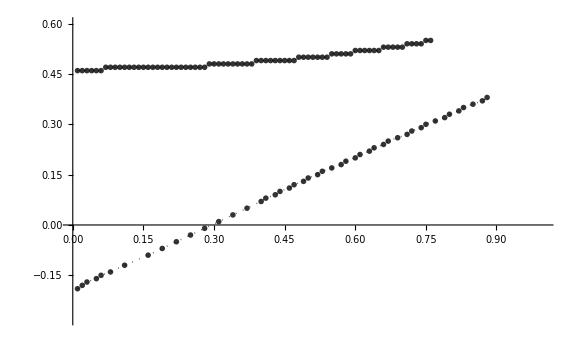

```mathematica
jointlist=SortBy[#,Last]&/@{
DeleteDuplicatesBy[#,First]&@SortBy[#,Last]&@(        Select[ en ,(#[[1]]>0.01∧ #[[2]]>.4∧ #[[3]]<.2)&][[;;,1;;2]]     )   ,
DeleteDuplicatesBy[#,Last]&@ReverseSortBy[#,Last]&@(   Select[ en ,(#[[1]]>0.01∧ #[[2]]<.4∧ #[[3]]<.26)&][[;;,1;;2]]  )
} ;

gapclosing=Show[ ListPlot[jointlist[[1]],PlotMarkers->"OpenMarkers",PlotStyle->{{Black,Dotted,Thick,Opacity[.8]}}, Joined->True,PlotRange->{{0,1},{-.28,.6}},ImageSize->Large],
 ListPlot[jointlist[[2]],PlotMarkers->"OpenMarkers",PlotStyle->{{Black,Dotted,Thick,Opacity[.8]}}, Joined->True,PlotRange->{{0,1},{-.28,.6}},ImageSize->Large] ]
```

{0,0.950251}

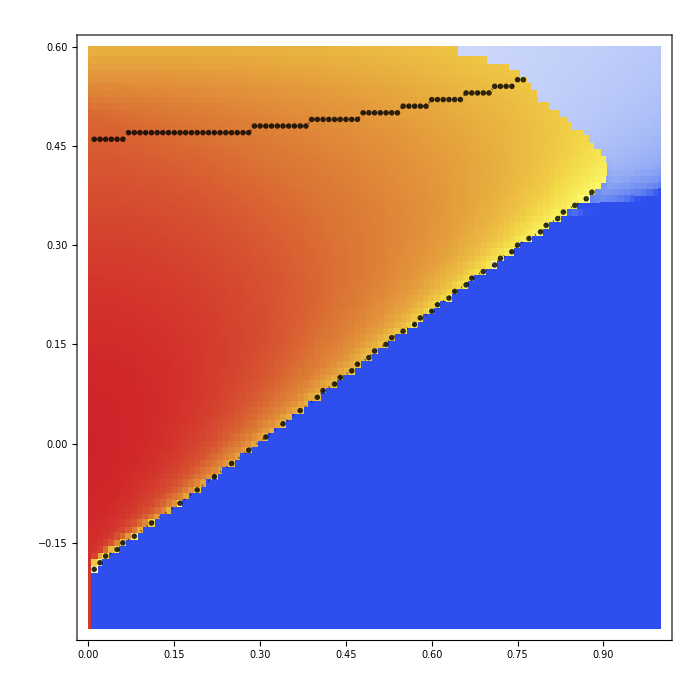

```mathematica
fig3a=Module[{minmax,max,contoursLevels,colors,δ=0,imgs=700},
minmax=MinMax@Abs[  χKH[[;;,3]]  ]; Print[minmax];max=N@(Ceiling[minmax[[2]] 100]/100);(*contoursLevels=Table[ (max/10)  x ,{x,1,10}];*)
colors={{0,Lighter@Orange},{0.05,White},(*{0.5-δ,White},{0.5+δ,White},*){1,Darker@Cyan}};
Show[ListDensityPlot[ Join[ χKH], PlotRange-> {{0,1},{-.28,.6},{0,1.01}}, 
ImageSize->imgs,(*PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}},*)Frame->True, (*PlotLabel->MaTeX["\\left< \\mathrm{U}_\\gamma^{\\gamma\\gamma}\\right> \\quad \\mathbf{h}\\parallel \\mathbf{a}",Magnification->2]   , *)PlotLegends->BarLegend[ "TemperatureMap",None,LegendLabel->MaTeX["\\mathrm{U}_{\\gamma}^{\\gamma \\gamma}\\;\\;   ",Magnification->2],LegendMarkerSize-> {20,300},LabelStyle->{Black,FontSize->20,FontFamily->"Helvetica"}  ]  ,
 FrameStyle->Directive[Black,20], FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{"h","\\Gamma  "},ColorFunction->(ColorData["TemperatureMap",((#)^1 )]&)(*(Blend[colors,#/ minmax[[2]]]&)  *), ColorFunctionScaling->True,InterpolationOrder->0  ,MeshFunctions->{#1 & , #2 & },
Epilog->{Inset[MaTeX["\\textbf{KSL}",Magnification->2.5],Scaled[{.15,.3}],Scaled[{.5,0}]],
Inset[MaTeX["\\textbf{PP}",Magnification->2.5],Scaled[{.8,.3}],Scaled[{.5,0}]]  ,
Inset[MaTeX["\\mathrm{(a)}",Magnification->2.5],Scaled[{.12,.92}],Scaled[{.5,.5}]]  }
,ClippingStyle->Automatic     ]
(*,
Plot[  {.52+.045x,-.7+.95Sqrt[x]  },{x,0.015,1.19} , PlotStyle->{{Black,Thickness[0.005],Opacity[.8] }} ]*)
,gapclosing]        ]
```

```mathematica
Fig3bRaster=Rasterize[fig3a,"Image",RasterSize->5000];
```

```mathematica
Export["C:\\User\\lucas\\Desktop\\Wolfram Mathematica\\PhD-codes\\Figures_PhD\\New2\\Fig3a_J.pdf"  ,Fig3bRaster  ];
```

#### other

```mathematica
Module[{minmax,max,contoursLevels,colors,δ=0,imgs=500},
minmax=MinMax@Abs[  χKH[[;;,3]]  ]; Print[minmax];
minmax=MinMax@Abs[  χKHc[[;;,3]]  ]; Print[minmax];max=N@(Ceiling[minmax[[2]] 100]/100);(*contoursLevels=Table[ (max/10)  x ,{x,1,10}];*)
colors={{0,Lighter@Orange},{0.05,White},(*{0.5-δ,White},{0.5+δ,White},*){1,Darker@Cyan}};
Show[ListDensityPlot[ Join[ χKH(*,{{1.19,-0.69,0.},{1.19,0.8,0.}}   *)], PlotRange-> {{0,1.51},{-.28,1.01},{0,1.01}}, 
ImageSize->imgs,(*PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}},*)Frame->True, PlotLabel->MaTeX["\\left< \\mathrm{U}_\\gamma^{\\gamma\\gamma}\\right>  \\qquad \\mathbf{h} \\parallel \\mathbf{a} ",Magnification->1.4]   , PlotLegends->Automatic , FrameStyle->Directive[Black,16], FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"h","\\Gamma  "},ColorFunction->(ColorData["TemperatureMap",((#)^1.1  )]&)(*(Blend[colors,#/ minmax[[2]]]&)  *), ColorFunctionScaling->True,InterpolationOrder->0  (*,Contours->5(*contoursLevels*)*),
Epilog->{Inset[MaTeX["\\text{KSL}",Magnification->2],Scaled[{.1,.3}],Scaled[{.5,0}]],
Inset[MaTeX["\\text{PP}",Magnification->2],Scaled[{.8,.3}],Scaled[{.5,0}]]  },ClippingStyle->Automatic     ]
(*,
Plot[  {.52+.045x,-.7+.95Sqrt[x]  },{x,0.015,1.19} , PlotStyle->{{Black,Thickness[0.005],Opacity[.8] }} ]*)
]        ]
```

```mathematica
Export["C:\\User\\lucas\\Desktop\\Wolfram Mathematica\\PhD-codes\\Figures_PhD\\Fig3b_ha.pdf"  ,%   ];
```

```mathematica
Module[{minmax,max,contoursLevels,colors,δ=0,imgs=500},
minmax=MinMax@Abs[  ωHG[[;;,3]]  ]; Print[minmax];
minmax=MinMax@Abs[  χKH3[[;;,3]]  ]; Print[minmax];max=N@(Ceiling[minmax[[2]] 100]/100);(*contoursLevels=Table[ (max/10)  x ,{x,1,10}];*)
colors={{0,Lighter@Orange},{0.05,White},(*{0.5-δ,White},{0.5+δ,White},*){1,Darker@Cyan}};
Show[ListDensityPlot[ Join[ ωHG3(*,{{1.19,-0.69,0.},{1.19,0.8,0.}}   *)], PlotRange-> {{0,2.01},{-.36,1.01},{0,1.01}}, 
ImageSize->imgs,(*PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}},*)Frame->True, PlotLabel->MaTeX[" | \\left< \\sigma \\right> |   \\qquad \\mathbf{h} \\parallel \\mathbf{c}",Magnification->1.4]   , PlotLegends->Automatic , FrameStyle->Directive[Black,16], FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"h","\\Gamma  "},ColorFunction->(ColorData["TemperatureMap",(1-(#)^(4.9/5)  )]&)(*(Blend[colors,#/ minmax[[2]]]&)  *), ColorFunctionScaling->True,InterpolationOrder->0  (*,Contours->5(*contoursLevels*)*),
Epilog->{Inset[MaTeX["\\text{KSL}",Magnification->2],Scaled[{.1,.4}],Scaled[{.5,0}]],
Inset[MaTeX["\\text{PP}",Magnification->2],Scaled[{.8,.3}],Scaled[{.5,0}]]  },ClippingStyle->Automatic     ]
(*,
Plot[  {.52+.045x,-.7+.95Sqrt[x]  },{x,0.015,1.19} , PlotStyle->{{Black,Thickness[0.005],Opacity[.8] }} ]*)
]        ]
```

```mathematica
Module[{minmax,max,contoursLevels,colors,δ=0,imgs=500},
minmax=MinMax@Abs[  ωHG[[;;,3]]  ]; Print[minmax];
minmax=MinMax@Abs[  ωHGa[[;;,3]]  ]; Print[minmax];max=N@(Ceiling[minmax[[2]] 100]/100);(*contoursLevels=Table[ (max/10)  x ,{x,1,10}];*)
colors={{0,Lighter@Orange},{0.05,White},(*{0.5-δ,White},{0.5+δ,White},*){1,Darker@Cyan}};
Show[ListDensityPlot[ Join[ ωHGa(*,{{1.19,-0.69,0.},{1.19,0.8,0.}}   *)], PlotRange-> {{0,2.01},{-.28,1.01},{0,1.01}}, 
ImageSize->imgs,(*PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}},*)Frame->True, PlotLabel->MaTeX[" || \\left< \\sigma \\right> \\times \\mathbf{c} \\, ||    \\qquad \\mathbf{h} \\parallel \\mathbf{c}",Magnification->1.4]   , PlotLegends->Automatic , FrameStyle->Directive[Black,16], FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"h","\\Gamma  "},ColorFunction->(ColorData["TemperatureMap",(1-(#)^(5/5)  )]&)(*(Blend[colors,#/ minmax[[2]]]&)  *), ColorFunctionScaling->True,InterpolationOrder->0  (*,Contours->5(*contoursLevels*)*),
Epilog->{Inset[MaTeX["\\text{KSL}",Magnification->2],Scaled[{.1,.4}],Scaled[{.5,0}]],
Inset[MaTeX["\\text{PP}",Magnification->2],Scaled[{.8,.3}],Scaled[{.5,0}]]  },ClippingStyle->{Green}     ]
(*,
Plot[  {.52+.045x,-.7+.95Sqrt[x]  },{x,0.015,1.19} , PlotStyle->{{Black,Thickness[0.005],Opacity[.8] }} ]*)
]        ]
```

```mathematica
(*Module[{minmax,max,contoursLevels,colors,δ=0,imgs=500},
minmax=MinMax@Abs[  ωHG[[;;,3]]  ]; Print[minmax];max=N@(Ceiling[minmax[[2]] 100]/100);(*contoursLevels=Table[ (max/10)  x ,{x,1,10}];*)
colors={{0,Lighter@Orange},{0.05,White},(*{0.5-δ,White},{0.5+δ,White},*){1,Darker@Cyan}};
Show[ListDensityPlot[ Join[ωHG(*,{{1.19,0.81,0.27},{1.19,-0.69,1}}*)], 
ImageSize->imgs, PlotRange->{0,1},(*PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}},*)Frame->True, PlotLabel->MaTeX[" \\left< \\sigma \\right> \\cdot \\mathbf{c}    \\qquad \\mathbf{h} \\parallel \\mathbf{c}",Magnification->1.4]   , PlotLegends->Automatic , FrameStyle->Directive[Black,16], FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"h","\\Gamma  "},ColorFunction->(ColorData["TemperatureMap",(1-(#)^(3/5)  )]&),  (*(Blend[colors,#/ minmax[[2]]]&)  *) ColorFunctionScaling->True,InterpolationOrder-> 2  (*,Contours->5(*contoursLevels*)*),
Epilog->{Inset[MaTeX["\\text{KSL}",Magnification->2],Scaled[{.2,.5}],Scaled[{.5,0}]],
Inset[MaTeX["\\text{PP}",Magnification->2],Scaled[{.7,.15}],Scaled[{.5,0}]]  },ClippingStyle->Automatic        ],
Plot[  {.52+.045x,-.7+.95Sqrt[x]  },{x,0.015,1.19} , PlotStyle->{{Black,Thickness[0.005],Opacity[.8] }} ]
]        ]  *)
```

```mathematica
Export["C:\\User\\lucas\\Desktop\\Wolfram Mathematica\\PhD-codes\\Magnetization_out_of_plane.pdf"  ,%   ];
```

```mathematica
(*Module[{minmax,max,contoursLevels,colors,δ=0,imgs=500},

minmax=MinMax@Abs[  Wp[[;;,3]]  ];

max=N@(Ceiling[minmax[[2]] 100]/100);
(*contoursLevels=Table[ (max/10)  x ,{x,1,10}];*)
colors={{0,Lighter@Orange},{0.05,White},(*{0.5-δ,White},{0.5+δ,White},*){1,Darker@Cyan}};

{
ListDensityPlot[ Wp, 
ImageSize->imgs,(*PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}},*)Frame->True, PlotLabel->MaTeX[" W_p  \\qquad \\mathbf{h} \\parallel \\mathbf{c}",Magnification->1.4]   , PlotLegends->Automatic , FrameStyle->Directive[Black,16], FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"h","\\Gamma  "},ColorFunction->(Blend[colors,#/ minmax[[2]]]&)  , ColorFunctionScaling->False,InterpolationOrder-> 2  (*,Contours->5(*contoursLevels*)*),
Epilog->{Inset[MaTeX["\\text{KSL}",Magnification->2],Scaled[{.1,.5}],Scaled[{.5,0}]],
Inset[MaTeX["\\text{PP}",Magnification->2],Scaled[{.7,.15}],Scaled[{.5,0}]]  },ClippingStyle->{{Lighter@Pink,Opacity[.5]}}  
] 
}
]*)
```

```mathematica
(*Module[{χK=χKH,minmax,max,contoursLevels,colors,δ=0,imgs=500},

minmax=MinMax@Abs[  χK[[;;,3]] ];

max=N@(Ceiling[minmax[[2]] 100]/100);
(*contoursLevels=Table[ (max/10)  x ,{x,1,10}];*)
colors={{0,Lighter@Orange},{0.05,White},(*{0.5-δ,White},{0.5+δ,White},*){1,Darker@Cyan}};

plotFig3A=ListContourPlot[ χK, 
ImageSize->imgs,(*PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}},*)Frame->True, PlotLabel->MaTeX[" \\mathrm{U}^{\\gamma \\gamma}_\\gamma  = \\left< \\mathrm{i} c^\\gamma_i c^\\gamma_j \\right>  \\quad \\mathbf{h} \\parallel \\mathbf{c}",Magnification->1.4]   , PlotLegends->BarLegend[Automatic,All] , FrameStyle->Directive[Black,16], FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"h","\\Gamma  "},ColorFunction->(Blend[colors,#/ minmax[[2]]]&)  , ColorFunctionScaling->False,InterpolationOrder-> 1  ,Contours->5(*contoursLevels*),
Epilog->{Inset[MaTeX["\\text{KSL}",Magnification->2],Scaled[{.1,.5}],Scaled[{.5,0}]],
Inset[MaTeX["\\text{PP}",Magnification->2],Scaled[{.7,.15}],Scaled[{.5,0}]]  }
] 
]*)
```

```mathematica
(*int=Interpolation[χKH[[1;;-1]] ];
Show[{ContourPlot[int[x,y],{x,0,.6},{y,-.7,.7}]}]*)
```

```mathematica
{min,max}=MinMax@Abs[  ΔW[[;;,3]]  ];  Print[{min,max}];
ListDensityPlot[ Join[ΔW(*,{{1.19,0.81,0},{1.19,-0.69,0}}*)]   ,ImageSize->500,PlotLabel->MaTeX[ "\\Delta \\mathrm{V}"
(*" \\mathrm{tr}\\left( \\mathrm{W}^\\mathrm{T} \\mathrm{G}^{\\gamma}\\right) = \\left< \\mathrm{i} c^\\gamma_i \\mathrm{G}^{\\gamma} c^\\gamma_i \\right>  \\; , \\quad \\mathbf{h} \\parallel \\mathbf{c}"*),Magnification->1.4]   , Frame->True, PlotLegends->Automatic , FrameStyle->Directive[Black,16], FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"h","\\Gamma  "},
ColorFunction->"TemperatureMap",ColorFunctionScaling->True,ClippingStyle->Automatic,PlotRange->{0,0.05}  ]
```

```mathematica
Export["C:\\User\\lucas\\Desktop\\Wolfram Mathematica\\PhD-codes\\DeltaW.pdf"  ,%   ];
```

#### line plot

```mathematica
Module[{title,img=700,x=-.03}, title="J=0, \\, K=-1 , \\,   \\mathbf{h}=0.2 \\mathbf{c}";
gK=ListPlot[χKH,Joined->True,PlotMarkers->{"●",Small}, PlotStyle->{Darker[Blue]},Frame->True,FrameStyle->Directive[Black,16],PlotLabel->(MaTeX[#,Magnification->1.6]&)@" ",FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"\\Gamma ","\\text{MF parameters}"},ImageSize->img,PlotLegends->Placed[(MaTeX[#,Magnification->1.3]&)/@{"\\mathrm{U}_{\\!K}\\!=\\mathrm{U}_{\\gamma}^{\\gamma\\gamma}"},{.901+x,.94}],
PlotRange->All,Frame->True,FrameStyle->Directive[Black,16], ImageSize->img,PlotRange->All,GridLines->None];
gc=ListPlot[χcH,Joined->True,PlotMarkers->{"●",Small}, PlotStyle->{Darker[Red]},Frame->True,FrameStyle->Directive[Black,16],PlotLabel->(MaTeX[#,Magnification->1.6]&)@title,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"\\Gamma ","\\text{MF parameters}"},ImageSize->img,PlotLegends->Placed[(MaTeX[#,Magnification->1.3]&)/@{"\\mathrm{U}_{0}=\\mathrm{U}_{\\gamma}^{00}"},{.9+x,.9}],PlotRange->All,Frame->True,FrameStyle->Directive[Black,16], ImageSize->img,PlotRange->All,GridLines->Automatic];
gΓ = ListPlot[χΓH,Joined->True,PlotMarkers->{"●",Small}, PlotStyle->{ Orange },Frame->True,FrameStyle->Directive[Black,16],PlotLabel->(MaTeX[#,Magnification->1.6]&)@title,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"\\Gamma ","\\text{MF parameters}"},ImageSize->img,PlotLegends->Placed[(MaTeX[#,Magnification->1.3]&)/@{"\\mathrm{U}_{\\Gamma}=\\mathrm{U}_{\\gamma}^{\\alpha\\beta}"},{.903+x,.86}],
PlotRange->All,Frame->True,FrameStyle->Directive[Black,16], ImageSize->img,PlotRange->All,GridLines->Automatic];
gJ = ListPlot[χJH,Joined->True,PlotMarkers->{"●",Small}, PlotStyle->{ Orange },Frame->True,FrameStyle->Directive[Black,16],PlotLabel->(MaTeX[#,Magnification->1.6]&)@title,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"\\Gamma ","\\text{MF parameters}"},ImageSize->img,PlotLegends->Placed[(MaTeX[#,Magnification->1.3]&)/@{"\\mathrm{U}_{J}=\\mathrm{U}_{\\gamma}^{\\alpha\\alpha}"},{.9+x,.82}],
PlotRange->All,Frame->True,FrameStyle->Directive[Black,16], ImageSize->img,PlotRange->All,GridLines->Automatic];
gM = ListPlot[ωH,Joined->True,PlotMarkers->{"●",Small}, PlotStyle->{Darker[Green]},Frame->True,FrameStyle->Directive[Black,16],PlotLabel->(MaTeX[#,Magnification->1.6]&)@title,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"\\Gamma ","\\text{MF parameters}"},ImageSize->img,PlotLegends->Placed[(MaTeX[#,Magnification->1.3]&)/@{"\\langle \\sigma \\rangle = \\mathrm{W}^{0\\alpha} \\hat{h}^{\\alpha}"},{.919+x,.82}],
PlotRange->All,Frame->True,FrameStyle->Directive[Black,16], ImageSize->500,PlotRange->All,GridLines->Automatic];
Show[gK,gc,(*gJ,*)gM, gΓ,PlotRange-> { {-0.75,.75},{-1.1,1.1} }  ]
]
```

also, we could insert both Γ and J in the horizontal axis, just changing the plot markers

```mathematica
NbName = "705"; 
		Ls =Range[40,40,2]; 	    tV={0};				hV={{0.001,0,0}};
		steps=600;                                     acuracy=6;                               ΔeV=0.099999;                                           eVs=Table[ 1700 ξ, {ξ,0,0,ΔeV} ] ; 

		Js=Table[j,{j,-1,1,.05}];
		Ks={-1.};
		Γs= {0.};
		hV=Table[{h,0,0},{h,0.2,0.2,.2}];

		ts = Table[ {5x,160,-12x,0,-60},{x,tV}];
		hs =Table[  h[[1]]  hAngle[h[[2]],h[[3]]] , {h,hV}];  
		eV0=0;U=2600;JH=300;

		Module[{parameters0,parameters1},
				parameters0=Tuples[{Js,Ks,Γs,hs}];
				parameters1=Tuples[{Js,Ks,Γs,hV}];
				parameters={Table[  Flatten[{ parameters0[[i]],parameters1[[i]],{0},{0}},1],  {i,1,Length@parameters0}]};
		]
```

```mathematica
ωH2={};χKH2={};χcH2={};χΓH2={};χJH2={};
 Do[Module[{L,Nc,J,K, Γ, h,jG,LG,en,ξG,EnG,η=0,l,χ0,ω0, χc,χK,ωM,χJ,χΓ}, l=1;
L=Ls[[l]];
{J,K, Γ, h}=parameters[[1,p]][[1;;4]];
{jG,LG,χ0,ω0,ξG,EnG}= loadData[toPath[parameters[[1,p]],L,acuracy,"free",NbName ]  ];

χc=1/3( χ0[[1]][[1,1]]   + χ0[[2]][[1,1]]+χ0[[3]][[1,1]]);
χJ=1/6( χ0[[1]][[3,3]]+χ0[[1]][[4,4]] + χ0[[2]][[2,2]]+ χ0[[2]][[4,4]]+χ0[[3]][[2,2]] +χ0[[3]][[3,3]]   ); 
χK=1/3( χ0[[1]][[2,2]]   + χ0[[2]][[3,3]]+χ0[[3]][[4,4]] - 3χJ );
χΓ=1/6( χ0[[1]][[3,4]]+χ0[[1]][[4,3]] + χ0[[2]][[2,4]]+ χ0[[2]][[4,2]]+χ0[[3]][[2,3]] +χ0[[3]][[3,2]]   );
ωM= 1/(2Norm[h]) ( h.{ω0[[1]][[2,1]],ω0[[1]][[3,1]],ω0[[1]][[4,1]]}   + h.{ω0[[2]][[2,1]],ω0[[2]][[3,1]],ω0[[2]][[4,1]]}   );

 AppendTo[ωH2,{Γ,ωM }]; AppendTo[χKH2,{Γ,χK}]; AppendTo[χcH2,{Γ,χc}]; AppendTo[χΓH2,{Γ,χΓ}];  AppendTo[χJH2,{Γ,χJ}];               ];
, {p,1,Length[parameters[[1]] ]} ]
```

```mathematica
Module[{title}, title="J=0, \\, K=-1 , \\,   \\mathbf{h}=0.2 \\mathbf{c}";
g1=ListPlot[{χKH,χcH,χΓH,χJH,ωH},Joined->True,PlotMarkers->"○" ,
 PlotStyle->{Darker[Blue],Darker[Red],Orange,Pink,Darker[Green]},
Frame->True,FrameStyle->Directive[Black,16],
PlotLabel->(MaTeX[#,Magnification->1.6]&)@title,
FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"\\Gamma[\\circ] , \\, J [\triangle] ","\\text{MF parameters}"},
ImageSize->500,
PlotLegends->Placed[(MaTeX[#,Magnification->1.3]&)/@{"\\mathrm{U}_K=\\mathrm{U}_{\\gamma}^{\\gamma\\gamma}","\\mathrm{U}_{0}=\\mathrm{U}_{\\gamma}^{00}","\\mathrm{U}_{\\Gamma}=\\mathrm{U}_{\\gamma}^{\\alpha\\beta}","\\mathrm{U}_{J}=\\mathrm{U}_{\\gamma}^{\\alpha\\alpha}","\\braket{\\sigma}=\\mathrm{W}^{0\\alpha}\\hat{h}^{\\alpha}"},{.08,.9}],
PlotRange->All,Frame->True,FrameStyle->Directive[Black,16], ImageSize->500,PlotRange->All,GridLines->False,
PlotRange-> { -1,1 }];

g2=ListPlot[{χKH2,χcH2,χΓH2,χJH2,ωH2},Joined->True,PlotMarkers->"△" ,
 PlotStyle->{Darker[Blue],Darker[Red],Orange,Pink,Darker[Green]},
Frame->True,FrameStyle->Directive[Black,16],
ImageSize->500,
PlotRange->All,Frame->True,FrameStyle->Directive[Black,16], ImageSize->500,PlotRange->All,GridLines->False,
PlotRange-> { -1,1 }];


Show[g1,g2,PlotRange-> { {-0.72,0.72},{-1,1} }  ]
]
```

#### energy criterea

```mathematica
Module[{J,K,Γ,h,p,jG,LG,χ,ω,ξG,EnG,heff},
p=2050; 
{J,K,Γ,h}=parameters[[1,p]][[1;;4]];
{jG,LG,χ,ω,ξG,EnG}= loadData[toPath[parameters[[1,p]],L,acuracy,"free",NbName ]  ];
heff={   h[[1]]-K  ω⟦2,2,1⟧-3J  ω⟦2,2,1⟧ -2Γ ω⟦2,4,1⟧ -2Γ  ω⟦2,3,1⟧ 
,h⟦2⟧-K ω⟦2,3,1⟧-3J ω⟦2,3,1⟧ -2 Γ ω⟦2,2,1⟧ -2Γ ω⟦2,4,1⟧  
,h⟦3⟧-K  ω⟦2,4,1⟧-3J ω⟦2,4,1⟧ -2 Γ  ω⟦2,3,1⟧ -2Γ ω⟦2,2,1⟧ 
} +10^-11;
MatrixForm@Sum[ Gmat[[γ]] Chop[heff[[γ]]/Norm[heff] ], {γ,1,3}]  
]
```

```mathematica
PHdiagram=Table[ Join[EnPP[[i,1;;2]],{If[ EnKSL[[i,4]]<10^-2,0,
		If[Chop[EnKSL[[i,3]]-EnPP[[i,3]]]<10^-3,0.5,
				If[EnKSL[[i,3]]>EnPP[[i,3]],0.5,1 ] ]   ] }  ]  , {i,1,Length[EnPP]}];
```

```mathematica
Module[{colors,contoursLevels,δ=0.01,min,max},
{max,min}=-MinMax@Join[ {EnKSL[[;;,3]],EnPP[[;;,3]]} ];
(*max=minmax[[1]];*)
contoursLevels=Table[ -(min+((max-min)/9)  x ),{x,1,10}];

colors={{0,Darker@Blue},{0.5-δ,White},{1,Darker@Red}};
ListContourPlot[  #,PlotLegends->Automatic,ImageSize->400,ColorFunctionScaling->False,ColorFunction->(Blend[colors,(-#-min)/(max-min) ]&)  , Contours->contoursLevels ]&/@ {EnKSL[[;;,1;;3]],EnPP[[;;,1;;3]]}
]
```

## Fig 3 a - Phase diagram Γ and h - c J=0

```mathematica
ClearAll[parameters]; 
                  
		NbName = "804"; 
		Ls = Range[41,41,4]; 				tV={0};	
		steps=500;			      eVs=Table[1700 x, {x,0,0,0.099999}];  		acuracy=4;   
				
(*Γs=round@Join[Table[x,{x,-.01,-.5,-.05}],round@Table[x,{x,0,1,.05}]];
hV=round@Table[{x,90,0},{x,0.0001,2.01,.05}];*)

Γs=round@Table[x,{x,-.2,.59,.01}];
Js={0.};
hV=round@Table[{x,0,0},{x,0.0001,1.21,.01}];
hs =Table[  h[[1]]  hAngle[h[[2]],h[[3]]] , {h,hV}];  
parametersMat={
Flatten[Table[{Jmat[ Js[[1]]{1,1,1},-1{1,1,1},Γs[[t]]{1,1,1},0{1,1,1},0{1,1,1}], hs[[h]], {}, hV[[h]], 0, 0},{t,1,Length@Γs},{h,1,Length@hV}],1]
};
```

```mathematica
(*{jG,LG,χ0,ω0,ξG,EnG}= loadData[toPath[parameters[[1,1801]],Ls[[1]],acuracy,"free",NbName ]  ];*)
```

```mathematica
χKH3a={};
WriteString["stdout",StringJoin["[", ToString[   Length[parametersMat[[1]] ]   ],"]: "]   ] 
AbsoluteTiming[Do[
Module[{L,Nc,J,K, Γ,Γp,DM, h,jG,LG,en,ξG,EnG,η=0,l,χ0,ω0, χc,χK,ωM,χJ,χΓ,ωM2,ωA,ωB,Jmat}, l=1;
If[Mod[p,500,0]==0,    WriteString["stdout",StringJoin[   ToString[ p],"; "]   ]    ];
L=Ls[[l]];Nc=L^2;
{Jmat, h}=parametersMat[[1,p]][[1;;2]]; h=h+10^-7 hc;
{J,K,Γ,Γp,DM}=fromJmat[ Jmat  ];
{jG,LG,χ0,ω0,ξG,EnG}=loadData[toPath800[parametersMat[[1,p]],L,acuracy,"free",NbName ]  ];
χJ=1/6( χ0[[1]][[3,3]]+χ0[[1]][[4,4]] + χ0[[2]][[2,2]]+ χ0[[2]][[4,4]]+χ0[[3]][[2,2]] +χ0[[3]][[3,3]]   ); 
χK=1/3( χ0[[1]][[2,2]]   + χ0[[2]][[3,3]]+χ0[[3]][[4,4]] - 3χJ );
AppendTo[χKH3a,{Norm[h],Γ,χK} ];
 ]; , {p,1,Length[parametersMat[[1]] ]    } ]; 
]
```

[9680]: 500; 1000; 1500; 2000; 2500; 3000; 3500; 4000; 4500; 5000;

$Aborted

```mathematica
AbsoluteTiming[
phaseTransition3a={};en3a={};
 Do[Module[{L,Nc,J,K, Γ, h,jG,LG,ξG,EnG,η=0,l,χ0,ω0, χc,χK,ωM,χJ,χΓ,ωM2,ωA,ωB,En,Jmat}, l=1;
If[Mod[p,500,0]==0,    WriteString["stdout",StringJoin[   ToString[ p],"; "]   ]    ];
L=Ls[[l]];Nc=L^2;

{Jmat, h}=parametersMat[[1,p]][[1;;2]]; h=h+10^-7 hc;
{J,K,Γ,Γp,DM}=fromJmat[ Jmat  ];
{jG,LG,χ0,ω0,ξG,EnG}=loadData[toPath800[parametersMat[[1,p]],L,acuracy,"free",NbName ]  ];
En=Sort[Abs/@Eigenvalues[ Chop@N@HmfMomentum[Jmat,h,χ0,ω0,{0,0},-.2+1.13Γ], 8 ]    ][[1]]; 
en3a={en3a,{Norm[h],Γ,En} };
If[  En<10^-1,phaseTransition3a={phaseTransition3a,{Norm[h],Γ} };];
 ]; , {p,1,Length[parametersMat[[1]] ]       } ];
en3a=Partition[Flatten@en3a,3];
phaseTransition3a=Partition[Flatten@phaseTransition3a,2];]
```

500; 1000; 1500; 2000; 2500; 3000; 3500; 4000; 4500; 5000; 5500; 6000; 6500; 7000; 7500; 8000; 8500; 9000; 9500;

{19.2131,Null}

```mathematica
(*
en=Partition[Flatten@en,3];
phaseTransition=Partition[Flatten@phaseTransition,2];*)
```

```mathematica
Join@@jointlist[[2;;3]]
```

{{0.1001,-0.2},{0.1101,-0.19},{0.1301,-0.18},{0.1401,-0.17},{0.1601,-0.16},{0.1701,-0.15},{0.1901,-0.14},{0.2001,-0.13},{0.2201,-0.12},{0.2301,-0.11},{0.2501,-0.1},{0.2601,-0.09},{0.2701,-0.08},{0.2901,-0.07},{0.3001,-0.06},{0.3201,-0.05},{0.3301,-0.04},{0.3501,-0.03},{0.3601,-0.02},{0.3701,-0.01},{0.3901,0.},{0.4001,0.01},{0.4201,0.02},{0.4301,0.03},{0.4501,0.04},{0.4601,0.05},{0.4801,0.06},{0.4901,0.07},{0.5001,0.08},{0.5201,0.09},{0.5301,0.1},{0.5501,0.11},{0.5601,0.12},{0.5801,0.13},{0.5901,0.14},{0.6101,0.15},{0.6201,0.16},{0.6401,0.17},{0.6501,0.18},{0.6701,0.19},{0.6801,0.2},{0.7001,0.21},{0.7201,0.22},{0.7301,0.23},{0.7501,0.24},{0.7601,0.25},{0.7801,0.26},{0.7901,0.27},{0.8101,0.28},{0.8301,0.29},{0.8401,0.3},{0.8601,0.31},{0.8801,0.32},{0.8901,0.33},{0.9101,0.34},{0.9301,0.35},{0.9401,0.36},{0.9601,0.37},{0.9801,0.38},{0.9901,0.39},{1.0101,0.4},{1.0301,0.41},{1.0401,0.42},{1.0501,0.43},{1.0601,0.44},{1.0701,0.45},{1.0701,0.46},{1.0701,0.47},{1.0601,0.48},{1.0501,0.49},{1.0401,0.5},{1.0201,0.51},{1.0001,0.52}}

```mathematica
jointlist[[2;;3]]
```

{{{0.1001,-0.2},{0.1101,-0.19},{0.1301,-0.18},{0.1401,-0.17},{0.1601,-0.16},{0.1701,-0.15},{0.1901,-0.14},{0.2001,-0.13},{0.2201,-0.12},{0.2301,-0.11},{0.2501,-0.1},{0.2601,-0.09},{0.2701,-0.08},{0.2901,-0.07},{0.3001,-0.06},{0.3201,-0.05},{0.3301,-0.04},{0.3501,-0.03},{0.3601,-0.02},{0.3701,-0.01},{0.3901,0.},{0.4001,0.01},{0.4201,0.02},{0.4301,0.03},{0.4501,0.04},{0.4601,0.05},{0.4801,0.06},{0.4901,0.07},{0.5001,0.08},{0.5201,0.09},{0.5301,0.1},{0.5501,0.11},{0.5601,0.12},{0.5801,0.13},{0.5901,0.14},{0.6101,0.15},{0.6201,0.16},{0.6401,0.17},{0.6501,0.18},{0.6701,0.19},{0.6801,0.2},{0.7001,0.21},{0.7201,0.22},{0.7301,0.23},{0.7501,0.24},{0.7601,0.25},{0.7801,0.26},{0.7901,0.27},{0.8101,0.28},{0.8301,0.29},{0.8401,0.3},{0.8601,0.31},{0.8801,0.32},{0.8901,0.33},{0.9101,0.34},{0.9301,0.35},{0.9401,0.36},{0.9601,0.37},{0.9801,0.38},{0.9901,0.39}},{{1.0101,0.4},{1.0301,0.41},{1.0401,0.42},{1.0501,0.43},{1.0601,0.44},{1.0701,0.45},{1.0701,0.46},{1.0701,0.47},{1.0601,0.48},{1.0501,0.49},{1.0401,0.5},{1.0201,0.51},{1.0001,0.52}}}

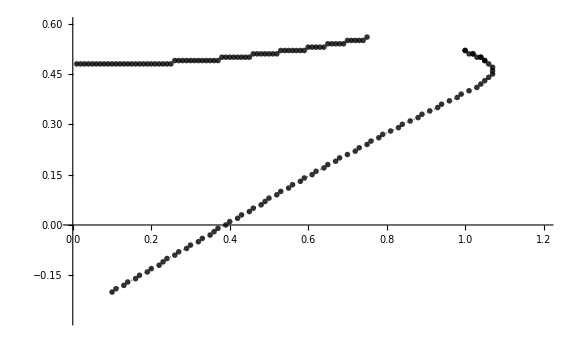

```mathematica
jointlist=SortBy[#,Last]&/@{
DeleteDuplicatesBy[#,First]&@SortBy[#,Last]&@(        Select[ en3a ,(#[[1]]>0.01∧#[[1]]<.8∧ #[[2]]>.4∧ #[[3]]<.03)&][[;;,1;;2]]     )   ,
DeleteDuplicatesBy[#,First]&@ReverseSortBy[#,Last]&@(        Select[ en3a ,(#[[1]]>1∧ #[[2]]>.44∧ #[[3]]<.2)&][[;;,1;;2]]     )   ,
DeleteDuplicatesBy[#,Last]&@ReverseSortBy[#,Last]&@(   Select[ en3a ,(#[[1]]>0.01∧ #[[2]]<.4∧ #[[3]]<.18)&][[;;,1;;2]]  )  ,
DeleteDuplicatesBy[#,Last]&@ReverseSortBy[#,Last]&@(   Select[ en3a ,(#[[1]]>1∧ #[[3]]<.26)&][[;;,1;;2]]  )
} ;

gapclosing=Show[ ListPlot[jointlist[[1]],PlotMarkers->"OpenMarkers",PlotStyle->{{Black,Dotted,Thick,Opacity[.8]}}, Joined->True,PlotRange->{{0,1.2},{-.28,.6}},ImageSize->Large],
 ListPlot[Join@@jointlist[[{3,4,2}]]  ,PlotMarkers->"OpenMarkers",PlotStyle->{{Black,Dotted,Thick,Opacity[.8]}}, Joined->True,PlotRange->{{0,1.2},{-.28,.6}},ImageSize->Large] ]
```

{0,1.}

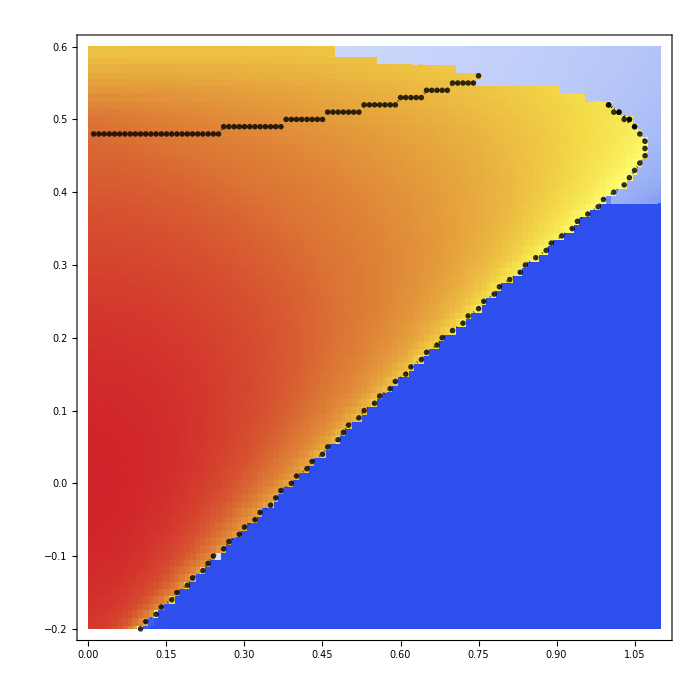

```mathematica
fig3a=Module[{minmax,max,contoursLevels,colors,δ=0,imgs=700},
minmax=MinMax@Abs[  χKH3a[[;;,3]]  ]; Print[minmax];max=N@(Ceiling[minmax[[2]] 100]/100);(*contoursLevels=Table[ (max/10)  x ,{x,1,10}];*)
colors={{0,Lighter@Orange},{0.05,White},(*{0.5-δ,White},{0.5+δ,White},*){1,Darker@Cyan}};
Show[ListDensityPlot[ Join[ χKH3a], PlotRange-> {{0,1.1},{-.2,.6},{0,1.01}}, 
ImageSize->imgs,(*PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}},*)Frame->True, (*PlotLabel->MaTeX["\\left< \\mathrm{U}_\\gamma^{\\gamma\\gamma}\\right> \\quad \\mathbf{h}\\parallel \\mathbf{a}",Magnification->2]   , *)PlotLegends->BarLegend[ "TemperatureMap",None,LegendLabel->MaTeX["\\mathrm{U}_{\\gamma}^{\\gamma \\gamma}\\;\\;   ",Magnification->2],LegendMarkerSize-> {20,300},LabelStyle->{Black,FontSize->20,FontFamily->"Helvetica"}  ]  ,
 FrameStyle->Directive[Black,20], FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{"h","\\Gamma  "},ColorFunction->(ColorData["TemperatureMap",((#)^1 )]&)(*(Blend[colors,#/ minmax[[2]]]&)  *), ColorFunctionScaling->True,InterpolationOrder->0  ,MeshFunctions->{#1 & , #2 & },
Epilog->{Inset[MaTeX["\\textbf{KSL}",Magnification->2.5],Scaled[{.15,.3}],Scaled[{.5,0}]],
(*Inset[MaTeX["\\textbf{PP}",Magnification->2.5],Scaled[{.8,.3}],Scaled[{.5,0}]]  ,*)
Inset[MaTeX["\\mathrm{(a)}",Magnification->2.5],Scaled[{.12,.92}],Scaled[{.5,.5}]]  }
,ClippingStyle->Automatic     ]
(*,
Plot[  {.52+.045x,-.7+.95Sqrt[x]  },{x,0.015,1.19} , PlotStyle->{{Black,Thickness[0.005],Opacity[.8] }} ]*)
,gapclosing]        ]
```

```mathematica
Fig3aRaster=Rasterize[fig3a,"Image",RasterSize->5000];
```

```mathematica
Export["C:\\User\\lucas\\Desktop\\Wolfram Mathematica\\PhD-codes\\Figures_PhD\\New2\\Fig3a_J0.pdf"  ,Fig3aRaster  ];
```

#### other

```mathematica
Module[{minmax,max,contoursLevels,colors,δ=0,imgs=500},
minmax=MinMax@Abs[  χKH[[;;,3]]  ]; Print[minmax];
minmax=MinMax@Abs[  χKHc[[;;,3]]  ]; Print[minmax];max=N@(Ceiling[minmax[[2]] 100]/100);(*contoursLevels=Table[ (max/10)  x ,{x,1,10}];*)
colors={{0,Lighter@Orange},{0.05,White},(*{0.5-δ,White},{0.5+δ,White},*){1,Darker@Cyan}};
Show[ListDensityPlot[ Join[ χKH(*,{{1.19,-0.69,0.},{1.19,0.8,0.}}   *)], PlotRange-> {{0,1.51},{-.28,1.01},{0,1.01}}, 
ImageSize->imgs,(*PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}},*)Frame->True, PlotLabel->MaTeX["\\left< \\mathrm{U}_\\gamma^{\\gamma\\gamma}\\right>  \\qquad \\mathbf{h} \\parallel \\mathbf{a} ",Magnification->1.4]   , PlotLegends->Automatic , FrameStyle->Directive[Black,16], FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"h","\\Gamma  "},ColorFunction->(ColorData["TemperatureMap",((#)^1.1  )]&)(*(Blend[colors,#/ minmax[[2]]]&)  *), ColorFunctionScaling->True,InterpolationOrder->0  (*,Contours->5(*contoursLevels*)*),
Epilog->{Inset[MaTeX["\\text{KSL}",Magnification->2],Scaled[{.1,.3}],Scaled[{.5,0}]],
Inset[MaTeX["\\text{PP}",Magnification->2],Scaled[{.8,.3}],Scaled[{.5,0}]]  },ClippingStyle->Automatic     ]
(*,
Plot[  {.52+.045x,-.7+.95Sqrt[x]  },{x,0.015,1.19} , PlotStyle->{{Black,Thickness[0.005],Opacity[.8] }} ]*)
]        ]
```

```mathematica
Export["C:\\User\\lucas\\Desktop\\Wolfram Mathematica\\PhD-codes\\Figures_PhD\\Fig3b_ha.pdf"  ,%   ];
```

```mathematica
Module[{minmax,max,contoursLevels,colors,δ=0,imgs=500},
minmax=MinMax@Abs[  ωHG[[;;,3]]  ]; Print[minmax];
minmax=MinMax@Abs[  χKH3[[;;,3]]  ]; Print[minmax];max=N@(Ceiling[minmax[[2]] 100]/100);(*contoursLevels=Table[ (max/10)  x ,{x,1,10}];*)
colors={{0,Lighter@Orange},{0.05,White},(*{0.5-δ,White},{0.5+δ,White},*){1,Darker@Cyan}};
Show[ListDensityPlot[ Join[ ωHG3(*,{{1.19,-0.69,0.},{1.19,0.8,0.}}   *)], PlotRange-> {{0,2.01},{-.36,1.01},{0,1.01}}, 
ImageSize->imgs,(*PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}},*)Frame->True, PlotLabel->MaTeX[" | \\left< \\sigma \\right> |   \\qquad \\mathbf{h} \\parallel \\mathbf{c}",Magnification->1.4]   , PlotLegends->Automatic , FrameStyle->Directive[Black,16], FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"h","\\Gamma  "},ColorFunction->(ColorData["TemperatureMap",(1-(#)^(4.9/5)  )]&)(*(Blend[colors,#/ minmax[[2]]]&)  *), ColorFunctionScaling->True,InterpolationOrder->0  (*,Contours->5(*contoursLevels*)*),
Epilog->{Inset[MaTeX["\\text{KSL}",Magnification->2],Scaled[{.1,.4}],Scaled[{.5,0}]],
Inset[MaTeX["\\text{PP}",Magnification->2],Scaled[{.8,.3}],Scaled[{.5,0}]]  },ClippingStyle->Automatic     ]
(*,
Plot[  {.52+.045x,-.7+.95Sqrt[x]  },{x,0.015,1.19} , PlotStyle->{{Black,Thickness[0.005],Opacity[.8] }} ]*)
]        ]
```

```mathematica
Module[{minmax,max,contoursLevels,colors,δ=0,imgs=500},
minmax=MinMax@Abs[  ωHG[[;;,3]]  ]; Print[minmax];
minmax=MinMax@Abs[  ωHGa[[;;,3]]  ]; Print[minmax];max=N@(Ceiling[minmax[[2]] 100]/100);(*contoursLevels=Table[ (max/10)  x ,{x,1,10}];*)
colors={{0,Lighter@Orange},{0.05,White},(*{0.5-δ,White},{0.5+δ,White},*){1,Darker@Cyan}};
Show[ListDensityPlot[ Join[ ωHGa(*,{{1.19,-0.69,0.},{1.19,0.8,0.}}   *)], PlotRange-> {{0,2.01},{-.28,1.01},{0,1.01}}, 
ImageSize->imgs,(*PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}},*)Frame->True, PlotLabel->MaTeX[" || \\left< \\sigma \\right> \\times \\mathbf{c} \\, ||    \\qquad \\mathbf{h} \\parallel \\mathbf{c}",Magnification->1.4]   , PlotLegends->Automatic , FrameStyle->Directive[Black,16], FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"h","\\Gamma  "},ColorFunction->(ColorData["TemperatureMap",(1-(#)^(5/5)  )]&)(*(Blend[colors,#/ minmax[[2]]]&)  *), ColorFunctionScaling->True,InterpolationOrder->0  (*,Contours->5(*contoursLevels*)*),
Epilog->{Inset[MaTeX["\\text{KSL}",Magnification->2],Scaled[{.1,.4}],Scaled[{.5,0}]],
Inset[MaTeX["\\text{PP}",Magnification->2],Scaled[{.8,.3}],Scaled[{.5,0}]]  },ClippingStyle->{Green}     ]
(*,
Plot[  {.52+.045x,-.7+.95Sqrt[x]  },{x,0.015,1.19} , PlotStyle->{{Black,Thickness[0.005],Opacity[.8] }} ]*)
]        ]
```

```mathematica
(*Module[{minmax,max,contoursLevels,colors,δ=0,imgs=500},
minmax=MinMax@Abs[  ωHG[[;;,3]]  ]; Print[minmax];max=N@(Ceiling[minmax[[2]] 100]/100);(*contoursLevels=Table[ (max/10)  x ,{x,1,10}];*)
colors={{0,Lighter@Orange},{0.05,White},(*{0.5-δ,White},{0.5+δ,White},*){1,Darker@Cyan}};
Show[ListDensityPlot[ Join[ωHG(*,{{1.19,0.81,0.27},{1.19,-0.69,1}}*)], 
ImageSize->imgs, PlotRange->{0,1},(*PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}},*)Frame->True, PlotLabel->MaTeX[" \\left< \\sigma \\right> \\cdot \\mathbf{c}    \\qquad \\mathbf{h} \\parallel \\mathbf{c}",Magnification->1.4]   , PlotLegends->Automatic , FrameStyle->Directive[Black,16], FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"h","\\Gamma  "},ColorFunction->(ColorData["TemperatureMap",(1-(#)^(3/5)  )]&),  (*(Blend[colors,#/ minmax[[2]]]&)  *) ColorFunctionScaling->True,InterpolationOrder-> 2  (*,Contours->5(*contoursLevels*)*),
Epilog->{Inset[MaTeX["\\text{KSL}",Magnification->2],Scaled[{.2,.5}],Scaled[{.5,0}]],
Inset[MaTeX["\\text{PP}",Magnification->2],Scaled[{.7,.15}],Scaled[{.5,0}]]  },ClippingStyle->Automatic        ],
Plot[  {.52+.045x,-.7+.95Sqrt[x]  },{x,0.015,1.19} , PlotStyle->{{Black,Thickness[0.005],Opacity[.8] }} ]
]        ]  *)
```

```mathematica
Export["C:\\User\\lucas\\Desktop\\Wolfram Mathematica\\PhD-codes\\Magnetization_out_of_plane.pdf"  ,%   ];
```

```mathematica
(*Module[{minmax,max,contoursLevels,colors,δ=0,imgs=500},

minmax=MinMax@Abs[  Wp[[;;,3]]  ];

max=N@(Ceiling[minmax[[2]] 100]/100);
(*contoursLevels=Table[ (max/10)  x ,{x,1,10}];*)
colors={{0,Lighter@Orange},{0.05,White},(*{0.5-δ,White},{0.5+δ,White},*){1,Darker@Cyan}};

{
ListDensityPlot[ Wp, 
ImageSize->imgs,(*PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}},*)Frame->True, PlotLabel->MaTeX[" W_p  \\qquad \\mathbf{h} \\parallel \\mathbf{c}",Magnification->1.4]   , PlotLegends->Automatic , FrameStyle->Directive[Black,16], FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"h","\\Gamma  "},ColorFunction->(Blend[colors,#/ minmax[[2]]]&)  , ColorFunctionScaling->False,InterpolationOrder-> 2  (*,Contours->5(*contoursLevels*)*),
Epilog->{Inset[MaTeX["\\text{KSL}",Magnification->2],Scaled[{.1,.5}],Scaled[{.5,0}]],
Inset[MaTeX["\\text{PP}",Magnification->2],Scaled[{.7,.15}],Scaled[{.5,0}]]  },ClippingStyle->{{Lighter@Pink,Opacity[.5]}}  
] 
}
]*)
```

```mathematica
(*Module[{χK=χKH,minmax,max,contoursLevels,colors,δ=0,imgs=500},

minmax=MinMax@Abs[  χK[[;;,3]] ];

max=N@(Ceiling[minmax[[2]] 100]/100);
(*contoursLevels=Table[ (max/10)  x ,{x,1,10}];*)
colors={{0,Lighter@Orange},{0.05,White},(*{0.5-δ,White},{0.5+δ,White},*){1,Darker@Cyan}};

plotFig3A=ListContourPlot[ χK, 
ImageSize->imgs,(*PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}},*)Frame->True, PlotLabel->MaTeX[" \\mathrm{U}^{\\gamma \\gamma}_\\gamma  = \\left< \\mathrm{i} c^\\gamma_i c^\\gamma_j \\right>  \\quad \\mathbf{h} \\parallel \\mathbf{c}",Magnification->1.4]   , PlotLegends->BarLegend[Automatic,All] , FrameStyle->Directive[Black,16], FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"h","\\Gamma  "},ColorFunction->(Blend[colors,#/ minmax[[2]]]&)  , ColorFunctionScaling->False,InterpolationOrder-> 1  ,Contours->5(*contoursLevels*),
Epilog->{Inset[MaTeX["\\text{KSL}",Magnification->2],Scaled[{.1,.5}],Scaled[{.5,0}]],
Inset[MaTeX["\\text{PP}",Magnification->2],Scaled[{.7,.15}],Scaled[{.5,0}]]  }
] 
]*)
```

```mathematica
(*int=Interpolation[χKH[[1;;-1]] ];
Show[{ContourPlot[int[x,y],{x,0,.6},{y,-.7,.7}]}]*)
```

```mathematica
{min,max}=MinMax@Abs[  ΔW[[;;,3]]  ];  Print[{min,max}];
ListDensityPlot[ Join[ΔW(*,{{1.19,0.81,0},{1.19,-0.69,0}}*)]   ,ImageSize->500,PlotLabel->MaTeX[ "\\Delta \\mathrm{V}"
(*" \\mathrm{tr}\\left( \\mathrm{W}^\\mathrm{T} \\mathrm{G}^{\\gamma}\\right) = \\left< \\mathrm{i} c^\\gamma_i \\mathrm{G}^{\\gamma} c^\\gamma_i \\right>  \\; , \\quad \\mathbf{h} \\parallel \\mathbf{c}"*),Magnification->1.4]   , Frame->True, PlotLegends->Automatic , FrameStyle->Directive[Black,16], FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"h","\\Gamma  "},
ColorFunction->"TemperatureMap",ColorFunctionScaling->True,ClippingStyle->Automatic,PlotRange->{0,0.05}  ]
```

```mathematica
Export["C:\\User\\lucas\\Desktop\\Wolfram Mathematica\\PhD-codes\\DeltaW.pdf"  ,%   ];
```

#### line plot

```mathematica
Module[{title,img=700,x=-.03}, title="J=0, \\, K=-1 , \\,   \\mathbf{h}=0.2 \\mathbf{c}";
gK=ListPlot[χKH,Joined->True,PlotMarkers->{"●",Small}, PlotStyle->{Darker[Blue]},Frame->True,FrameStyle->Directive[Black,16],PlotLabel->(MaTeX[#,Magnification->1.6]&)@" ",FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"\\Gamma ","\\text{MF parameters}"},ImageSize->img,PlotLegends->Placed[(MaTeX[#,Magnification->1.3]&)/@{"\\mathrm{U}_{\\!K}\\!=\\mathrm{U}_{\\gamma}^{\\gamma\\gamma}"},{.901+x,.94}],
PlotRange->All,Frame->True,FrameStyle->Directive[Black,16], ImageSize->img,PlotRange->All,GridLines->None];
gc=ListPlot[χcH,Joined->True,PlotMarkers->{"●",Small}, PlotStyle->{Darker[Red]},Frame->True,FrameStyle->Directive[Black,16],PlotLabel->(MaTeX[#,Magnification->1.6]&)@title,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"\\Gamma ","\\text{MF parameters}"},ImageSize->img,PlotLegends->Placed[(MaTeX[#,Magnification->1.3]&)/@{"\\mathrm{U}_{0}=\\mathrm{U}_{\\gamma}^{00}"},{.9+x,.9}],PlotRange->All,Frame->True,FrameStyle->Directive[Black,16], ImageSize->img,PlotRange->All,GridLines->Automatic];
gΓ = ListPlot[χΓH,Joined->True,PlotMarkers->{"●",Small}, PlotStyle->{ Orange },Frame->True,FrameStyle->Directive[Black,16],PlotLabel->(MaTeX[#,Magnification->1.6]&)@title,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"\\Gamma ","\\text{MF parameters}"},ImageSize->img,PlotLegends->Placed[(MaTeX[#,Magnification->1.3]&)/@{"\\mathrm{U}_{\\Gamma}=\\mathrm{U}_{\\gamma}^{\\alpha\\beta}"},{.903+x,.86}],
PlotRange->All,Frame->True,FrameStyle->Directive[Black,16], ImageSize->img,PlotRange->All,GridLines->Automatic];
gJ = ListPlot[χJH,Joined->True,PlotMarkers->{"●",Small}, PlotStyle->{ Orange },Frame->True,FrameStyle->Directive[Black,16],PlotLabel->(MaTeX[#,Magnification->1.6]&)@title,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"\\Gamma ","\\text{MF parameters}"},ImageSize->img,PlotLegends->Placed[(MaTeX[#,Magnification->1.3]&)/@{"\\mathrm{U}_{J}=\\mathrm{U}_{\\gamma}^{\\alpha\\alpha}"},{.9+x,.82}],
PlotRange->All,Frame->True,FrameStyle->Directive[Black,16], ImageSize->img,PlotRange->All,GridLines->Automatic];
gM = ListPlot[ωH,Joined->True,PlotMarkers->{"●",Small}, PlotStyle->{Darker[Green]},Frame->True,FrameStyle->Directive[Black,16],PlotLabel->(MaTeX[#,Magnification->1.6]&)@title,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"\\Gamma ","\\text{MF parameters}"},ImageSize->img,PlotLegends->Placed[(MaTeX[#,Magnification->1.3]&)/@{"\\langle \\sigma \\rangle = \\mathrm{W}^{0\\alpha} \\hat{h}^{\\alpha}"},{.919+x,.82}],
PlotRange->All,Frame->True,FrameStyle->Directive[Black,16], ImageSize->500,PlotRange->All,GridLines->Automatic];
Show[gK,gc,(*gJ,*)gM, gΓ,PlotRange-> { {-0.75,.75},{-1.1,1.1} }  ]
]
```

also, we could insert both Γ and J in the horizontal axis, just changing the plot markers

```mathematica
NbName = "705"; 
		Ls =Range[40,40,2]; 	    tV={0};				hV={{0.001,0,0}};
		steps=600;                                     acuracy=6;                               ΔeV=0.099999;                                           eVs=Table[ 1700 ξ, {ξ,0,0,ΔeV} ] ; 

		Js=Table[j,{j,-1,1,.05}];
		Ks={-1.};
		Γs= {0.};
		hV=Table[{h,0,0},{h,0.2,0.2,.2}];

		ts = Table[ {5x,160,-12x,0,-60},{x,tV}];
		hs =Table[  h[[1]]  hAngle[h[[2]],h[[3]]] , {h,hV}];  
		eV0=0;U=2600;JH=300;

		Module[{parameters0,parameters1},
				parameters0=Tuples[{Js,Ks,Γs,hs}];
				parameters1=Tuples[{Js,Ks,Γs,hV}];
				parameters={Table[  Flatten[{ parameters0[[i]],parameters1[[i]],{0},{0}},1],  {i,1,Length@parameters0}]};
		]
```

```mathematica
ωH2={};χKH2={};χcH2={};χΓH2={};χJH2={};
 Do[Module[{L,Nc,J,K, Γ, h,jG,LG,en,ξG,EnG,η=0,l,χ0,ω0, χc,χK,ωM,χJ,χΓ}, l=1;
L=Ls[[l]];
{J,K, Γ, h}=parameters[[1,p]][[1;;4]];
{jG,LG,χ0,ω0,ξG,EnG}= loadData[toPath[parameters[[1,p]],L,acuracy,"free",NbName ]  ];

χc=1/3( χ0[[1]][[1,1]]   + χ0[[2]][[1,1]]+χ0[[3]][[1,1]]);
χJ=1/6( χ0[[1]][[3,3]]+χ0[[1]][[4,4]] + χ0[[2]][[2,2]]+ χ0[[2]][[4,4]]+χ0[[3]][[2,2]] +χ0[[3]][[3,3]]   ); 
χK=1/3( χ0[[1]][[2,2]]   + χ0[[2]][[3,3]]+χ0[[3]][[4,4]] - 3χJ );
χΓ=1/6( χ0[[1]][[3,4]]+χ0[[1]][[4,3]] + χ0[[2]][[2,4]]+ χ0[[2]][[4,2]]+χ0[[3]][[2,3]] +χ0[[3]][[3,2]]   );
ωM= 1/(2Norm[h]) ( h.{ω0[[1]][[2,1]],ω0[[1]][[3,1]],ω0[[1]][[4,1]]}   + h.{ω0[[2]][[2,1]],ω0[[2]][[3,1]],ω0[[2]][[4,1]]}   );

 AppendTo[ωH2,{Γ,ωM }]; AppendTo[χKH2,{Γ,χK}]; AppendTo[χcH2,{Γ,χc}]; AppendTo[χΓH2,{Γ,χΓ}];  AppendTo[χJH2,{Γ,χJ}];               ];
, {p,1,Length[parameters[[1]] ]} ]
```

```mathematica
Module[{title}, title="J=0, \\, K=-1 , \\,   \\mathbf{h}=0.2 \\mathbf{c}";
g1=ListPlot[{χKH,χcH,χΓH,χJH,ωH},Joined->True,PlotMarkers->"○" ,
 PlotStyle->{Darker[Blue],Darker[Red],Orange,Pink,Darker[Green]},
Frame->True,FrameStyle->Directive[Black,16],
PlotLabel->(MaTeX[#,Magnification->1.6]&)@title,
FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"\\Gamma[\\circ] , \\, J [\triangle] ","\\text{MF parameters}"},
ImageSize->500,
PlotLegends->Placed[(MaTeX[#,Magnification->1.3]&)/@{"\\mathrm{U}_K=\\mathrm{U}_{\\gamma}^{\\gamma\\gamma}","\\mathrm{U}_{0}=\\mathrm{U}_{\\gamma}^{00}","\\mathrm{U}_{\\Gamma}=\\mathrm{U}_{\\gamma}^{\\alpha\\beta}","\\mathrm{U}_{J}=\\mathrm{U}_{\\gamma}^{\\alpha\\alpha}","\\braket{\\sigma}=\\mathrm{W}^{0\\alpha}\\hat{h}^{\\alpha}"},{.08,.9}],
PlotRange->All,Frame->True,FrameStyle->Directive[Black,16], ImageSize->500,PlotRange->All,GridLines->False,
PlotRange-> { -1,1 }];

g2=ListPlot[{χKH2,χcH2,χΓH2,χJH2,ωH2},Joined->True,PlotMarkers->"△" ,
 PlotStyle->{Darker[Blue],Darker[Red],Orange,Pink,Darker[Green]},
Frame->True,FrameStyle->Directive[Black,16],
ImageSize->500,
PlotRange->All,Frame->True,FrameStyle->Directive[Black,16], ImageSize->500,PlotRange->All,GridLines->False,
PlotRange-> { -1,1 }];


Show[g1,g2,PlotRange-> { {-0.72,0.72},{-1,1} }  ]
]
```

#### energy criterea

```mathematica
Module[{J,K,Γ,h,p,jG,LG,χ,ω,ξG,EnG,heff},
p=2050; 
{J,K,Γ,h}=parameters[[1,p]][[1;;4]];
{jG,LG,χ,ω,ξG,EnG}= loadData[toPath[parameters[[1,p]],L,acuracy,"free",NbName ]  ];
heff={   h[[1]]-K  ω⟦2,2,1⟧-3J  ω⟦2,2,1⟧ -2Γ ω⟦2,4,1⟧ -2Γ  ω⟦2,3,1⟧ 
,h⟦2⟧-K ω⟦2,3,1⟧-3J ω⟦2,3,1⟧ -2 Γ ω⟦2,2,1⟧ -2Γ ω⟦2,4,1⟧  
,h⟦3⟧-K  ω⟦2,4,1⟧-3J ω⟦2,4,1⟧ -2 Γ  ω⟦2,3,1⟧ -2Γ ω⟦2,2,1⟧ 
} +10^-11;
MatrixForm@Sum[ Gmat[[γ]] Chop[heff[[γ]]/Norm[heff] ], {γ,1,3}]  
]
```

```mathematica
PHdiagram=Table[ Join[EnPP[[i,1;;2]],{If[ EnKSL[[i,4]]<10^-2,0,
		If[Chop[EnKSL[[i,3]]-EnPP[[i,3]]]<10^-3,0.5,
				If[EnKSL[[i,3]]>EnPP[[i,3]],0.5,1 ] ]   ] }  ]  , {i,1,Length[EnPP]}];
```

```mathematica
Module[{colors,contoursLevels,δ=0.01,min,max},
{max,min}=-MinMax@Join[ {EnKSL[[;;,3]],EnPP[[;;,3]]} ];
(*max=minmax[[1]];*)
contoursLevels=Table[ -(min+((max-min)/9)  x ),{x,1,10}];

colors={{0,Darker@Blue},{0.5-δ,White},{1,Darker@Red}};
ListContourPlot[  #,PlotLegends->Automatic,ImageSize->400,ColorFunctionScaling->False,ColorFunction->(Blend[colors,(-#-min)/(max-min) ]&)  , Contours->contoursLevels ]&/@ {EnKSL[[;;,1;;3]],EnPP[[;;,1;;3]]}
]
```

## Fig 3 b - Phase diagram Γ and h - a

```mathematica
ClearAll[parameters]; 
                  
		NbName = "804"; 
		Ls = Range[41,41,4]; 				tV={0};	
		steps=500;			      eVs=Table[1700 x, {x,0,0,0.099999}];  
		(* for equally spaced Gamma values *)

		acuracy=4;   
				
(*Γs=round@Join[Table[x,{x,-.01,-.5,-.05}],round@Table[x,{x,0,1,.05}]];
hV=round@Table[{x,90,0},{x,0.0001,2.01,.05}];*)

Γs=round@Table[x,{x,-.4,.6,.01}];
hV=round@Table[{x,90,0},{x,0.0001,1.21,.01}];
hs =Table[  h[[1]]  hAngle[h[[2]],h[[3]]] , {h,hV}];  
parametersMat={
Flatten[Table[{Jmat[0{1,1,1},-1{1,1,1},Γs[[t]]{1,1,1},0{1,1,1},0{1,1,1}], hs[[h]], {}, hV[[h]], 0, 0},{t,1,Length@Γs},{h,1,Length@hV}],1]
};

hs =Table[  h[[1]]  hAngle[h[[2]],h[[3]]] , {h,hV}];  
parametersMat={
Flatten[Table[{Jmat[0{1,1,1},-1{1,1,1},Γs[[t]]{1,1,1},0{1,1,1},0{1,1,1}], hs[[h]], {}, hV[[h]], 0, 0},{t,1,Length@Γs},{h,1,Length@hV}],1]
};
```

```mathematica
(*{jG,LG,χ0,ω0,ξG,EnG}= loadData[toPath[parameters[[1,1801]],Ls[[1]],acuracy,"free",NbName ]  ];*)
```

```mathematica
(*WriteString["stdout",StringJoin["[", ToString[   Length[parametersMat[[1]] ]   ],"]: "]   ] 
AbsoluteTiming[
ωH={};χKH={};χcH={};χΓH={};χJH={}; EnKSL={}; EnPP={}; ΔW={}; Wp={};Wp2={};  ωHG={};   ωHG3={};ωHGa={};χKHc={};χKH3={};
 Do[Module[{L,Nc,J,K, Γ,Γp,DM, h,jG,LG,en,ξG,EnG,η=0,l,χ0,ω0, χc,χK,ωM,χJ,χΓ,ωM2,ωA,ωB,Jmat}, l=1;
If[Mod[p,500,0]==0,    WriteString["stdout",StringJoin[   ToString[ p],"; "]   ]    ];
L=Ls[[l]];Nc=L^2;

{Jmat, h}=parametersMat[[1,p]][[1;;2]]; h=h+10^-7 hc;
{J,K,Γ,Γp,DM}=fromJmat[ Jmat  ];
{jG,LG,χ0,ω0,ξG,EnG}=loadData[toPath800[parametersMat[[1,p]],L,acuracy,"free",NbName ]  ];

χc=1/3( χ0[[1]][[1,1]]   + χ0[[2]][[1,1]]+χ0[[3]][[1,1]]);
χJ=1/6( χ0[[1]][[3,3]]+χ0[[1]][[4,4]] + χ0[[2]][[2,2]]+ χ0[[2]][[4,4]]+χ0[[3]][[2,2]] +χ0[[3]][[3,3]]   ); 
χK=1/3( χ0[[1]][[2,2]]   + χ0[[2]][[3,3]]+χ0[[3]][[4,4]] - 3χJ );
χΓ=1/6( χ0[[1]][[3,4]]+χ0[[1]][[4,3]] + χ0[[2]][[2,4]]+ χ0[[2]][[4,2]]+χ0[[3]][[2,3]] +χ0[[3]][[3,2]]   );
ωM= 1/(2Norm[h]+10^-9) ( h.{ω0[[1]][[2,1]],ω0[[1]][[3,1]],ω0[[1]][[4,1]]}   + h.{ω0[[2]][[2,1]],ω0[[2]][[3,1]],ω0[[2]][[4,1]]}   );


ωA={ω0[[1]][[2,1]],ω0[[1]][[3,1]],ω0[[1]][[4,1]]};
ωB={ω0[[2]][[2,1]],ω0[[2]][[3,1]],ω0[[2]][[4,1]]} ;

Module[{enKSL,enPP,ω=ω0,χPP=0χ0,ωPP,heff},
heff={   h[[1]]-K  ω⟦2,2,1⟧-3J  ω⟦2,2,1⟧ -Γ ω⟦2,4,1⟧ -Γ  ω⟦2,3,1⟧ 
,h⟦2⟧-K ω⟦2,3,1⟧-3J ω⟦2,3,1⟧ -Γ ω⟦2,2,1⟧ -Γ ω⟦2,4,1⟧  
,h⟦3⟧-K  ω⟦2,4,1⟧-3J ω⟦2,4,1⟧ - Γ  ω⟦2,3,1⟧ -Γ ω⟦2,2,1⟧ 
} +1/3 hc 10^-11;
ωM2= (h.(heff-2h))/(2Norm[h]+10^-11); 
ωM2= 1/(2Norm[h]+2 10^-11) (    heff.{ω0[[1]][[2,1]],ω0[[1]][[3,1]],ω0[[1]][[4,1]]}   + heff.{ω0[[2]][[2,1]],ω0[[2]][[3,1]],ω0[[2]][[4,1]]}     );  
(*
ωPP=Table[ⅈ IdentityMatrix[4]+Sum[ Gmat[[γ]] Chop[heff[[γ]]/Norm[heff]  ] , {γ,1,3}],{σ,1,2}];
	enKSL=EnMomentum[J,K,Γ,h,χ0,ω0,0.46];
	EnKSL={EnKSL,{Norm[h],Γ,Total@enKSL,Chop[Abs[χK],10^-2]} };
	enPP=EnMomentum[J,K,Γ,h,χPP,ωPP,0];
	EnPP={EnPP,{Norm[h],Γ,Total@enPP,0} };
*)];

ΔW={ΔW,{Norm[h],Γ,EnG[[5,-1,2]]  } };
ωHG={ωHG,{Norm[h],Γ,Norm[ωA.hc]  } };
ωHGa={ωHGa,{Norm[h],Γ,Norm[ωA.ha] +Norm[ωA.hb] } };
ωHG3={ωHG3,{Norm[h],Γ,Norm[ωA]  } };
χKH={χKH,{Norm[h],Γ,χK} };
χKHc={χKHc,{Norm[h],Γ,(Abs@χc) } };
χKH3={χKH3,{Norm[h],Γ,(Abs@χK)^3} };

(*If[ (EnG[[4,-1,2]]< 10^-5)∧(EnG[[4,-1,1]]<500),
ΔW={ΔW,{Norm[h],Γ,EnG[[5,-1,2]]  } };
ωHG={ωHG,{Norm[h],Γ,Norm[ωA.hc]  } };
ωHGa={ωHGa,{Norm[h],Γ,Norm[ωA.ha] +Norm[ωA.hb] } };
ωHG3={ωHG3,{Norm[h],Γ,Norm[ωA]  } };
χKH={χKH,{Norm[h],Γ,χK} };
χKHc={χKHc,{Norm[h],Γ,(Abs@χc) } };
χKH3={χKH3,{Norm[h],Γ,(Abs@χK)^3} };
Wp={Wp,{Norm[h],Γ,Abs[ χ0[[1]][[2,2]]  χ0[[2]][[3,3]]χ0[[3]][[4,4]] ]} };(*
Wp2={Wp2,{Norm[h],Γ,(Abs@χK)^3} };*),
ΔW={ΔW,{Norm[h],Γ, ∞ } };
ωHG={ωHG,{Norm[h],Γ,∞  } };
ωHGa={ωHGa,{Norm[h],Γ,∞ } };
ωHG3={ωHG3,{Norm[h],Γ,∞ } };
χKH={χKH,{Norm[h],Γ,∞} };
χKHc={χKHc,{Norm[h],Γ,∞} };
χKH3={χKH3,{Norm[h],Γ,∞} };
Wp={Wp,{Norm[h],Γ, ∞ }   };(*
Wp2={Wp2,{Norm[h],Γ,(Abs@χK)^3} };*)
]*)
(* AppendTo[ωH,{h,Γ,ωM }];  AppendTo[χcH,{h,Γ,χc}]; AppendTo[χΓH,{h,Γ,χΓ}];  AppendTo[χJH,{h,Γ,χJ}];  *)            
 ]; , {p,1,Length[parametersMat[[1]] ]    } ];
χKHc=Partition[Flatten@χKHc,3];
χKH=Partition[Flatten@χKH,3];
χKH3=Partition[Flatten@χKH3,3];
ωHG=Partition[Flatten@ωHG,3];
ωHGa=Partition[Flatten@ωHGa,3];
ωHG3=Partition[Flatten@ωHG3,3];
Wp=Partition[Flatten@Wp,3];(*
Wp2=Partition[Flatten@Wp2,3];*)
ΔW=Partition[Flatten@ΔW,3];
(*
EnKSL=Partition[Flatten@EnKSL,4];
EnPP=Partition[Flatten@EnPP,4];
*) ]
*)
```

```mathematica
(*ClearAll[parameters]; 
                  
		NbName = "804"; 
		Ls = Range[41,41,4]; 				tV={0};	
		steps=500;			      eVs=Table[1700 x, {x,0,0,0.099999}];  
		(* for equally spaced Gamma values *)

		acuracy=5;   
				
		Γs=round@Join[Table[x,{x,-.01,-.3,-.05}] ];
hV=round@Table[{x,90,0},{x,0.0001,2.01,.05}];


hs =Table[  h[[1]]  hAngle[h[[2]],h[[3]]] , {h,hV}];  
parametersMat={
Flatten[Table[{Jmat[0{1,1,1},-1{1,1,1},Γs[[t]]{1,1,1},0{1,1,1},0{1,1,1}], hs[[h]], {}, hV[[h]], 0, 0},{t,1,Length@Γs},{h,1,Length@hV}],1]
};*)
```

```mathematica
(*{jG,LG,χ0,ω0,ξG,EnG}= loadData[toPath[parameters[[1,1801]],Ls[[1]],acuracy,"free",NbName ]  ];*)
```

```mathematica
χKH3b={};
WriteString["stdout",StringJoin["[", ToString[   Length[parametersMat[[1]] ]   ],"]: "]   ] 
AbsoluteTiming[
 Do[Module[{L,Nc,J,K, Γ,Γp,DM, h,jG,LG,en,ξG,EnG,η=0,l,χ0,ω0, χc,χK,ωM,χJ,χΓ,ωM2,ωA,ωB,Jmat}, l=1;
If[Mod[p,500,0]==0,    WriteString["stdout",StringJoin[   ToString[ p],"; "]   ]    ];
L=Ls[[l]];Nc=L^2;
{Jmat, h}=parametersMat[[1,p]][[1;;2]]; h=h+10^-7 hc;
{J,K,Γ,Γp,DM}=fromJmat[ Jmat  ];
{jG,LG,χ0,ω0,ξG,EnG}=loadData[toPath800[parametersMat[[1,p]],L,acuracy,"free",NbName ]  ];
χJ=1/6( χ0[[1]][[3,3]]+χ0[[1]][[4,4]] + χ0[[2]][[2,2]]+ χ0[[2]][[4,4]]+χ0[[3]][[2,2]] +χ0[[3]][[3,3]]   ); 
χK=1/3( χ0[[1]][[2,2]]   + χ0[[2]][[3,3]]+χ0[[3]][[4,4]] - 3χJ );
AppendTo[χKH3b,{Norm[h],Γ,χK} ];
 ]; , {p,1,Length[parametersMat[[1]] ]    } ]; 
]
```

[12221]: 500; 1000; 1500; 2000; 2500; 3000; 3500; 4000; 4500; 5000; 5500; 6000; 6500; 7000; 7500; 8000; 8500; 9000; 9500; 10000; 10500; 11000; 11500; 12000;

{62.7488,Null}

```mathematica
AbsoluteTiming[
phaseTransition3b={};en3b={};
 Do[Module[{L,Nc,J,K, Γ, h,jG,LG,ξG,EnG,η=0,l,χ0,ω0, χc,χK,ωM,χJ,χΓ,ωM2,ωA,ωB,En,Jmat}, l=1;
If[Mod[p,500,0]==0,    WriteString["stdout",StringJoin[   ToString[ p],"; "]   ]    ];
L=Ls[[l]];Nc=L^2;

{Jmat, h}=parametersMat[[1,p]][[1;;2]]; h=h+10^-7 hc;
{J,K,Γ,Γp,DM}=fromJmat[ Jmat  ];
{jG,LG,χ0,ω0,ξG,EnG}=loadData[toPath800[parametersMat[[1,p]],L,acuracy,"free",NbName ]  ];
En=Sort[Abs/@Eigenvalues[ Chop@N@HmfMomentum[Jmat,h,χ0,ω0,{0,0},-.2+1.13Γ], 8 ]    ][[1]]; 
en3b={en3b,{Norm[h],Γ,En} };
If[  En<10^-1,phaseTransition3b={phaseTransition3b,{Norm[h],Γ} };];
 ]; , {p,1,Length[parametersMat[[1]] ]       } ];
en3b=Partition[Flatten@en3b,3];
phaseTransition3b=Partition[Flatten@phaseTransition3b,2];]
```

500; 1000; 1500; 2000; 2500; 3000; 3500; 4000; 4500; 5000; 5500; 6000; 6500; 7000; 7500; 8000; 8500; 9000; 9500; 10000; 10500; 11000; 11500; 12000;

{23.1821,Null}

```mathematica
(*Select[ en, #[[2]]==0.05&][[;;,3]]//ListPlot
 Select[ en  , (#[[3]]<.15)&]*)
```

```mathematica
(*Module[{list=Select[ΔW,#[[2]]==.13&]},
ListPlot@Table[ {list[[i,1]],list[[i,3]]},{i,1,Length@list}]
]*)
```

```mathematica
(*ListDensityPlot[  Wp ,ImageSize->500,PlotLabel->MaTeX[" W_p  \\qquad \\mathbf{h} \\parallel \\mathbf{c}",Magnification->1.4]    , Frame->True, PlotLegends->Automatic , FrameStyle->Directive[Black,16], FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"h","\\Gamma  "},ColorFunction->"TemperatureMap"  ]*)
```

```mathematica
(*Export["C:\\User\\lucas\\Desktop\\Wolfram Mathematica\\PhD-codes\\Figures_PhD\\New2\\Fig3b_h=a.pdf"  ,fig3b  ];*)
```

{0,1.}

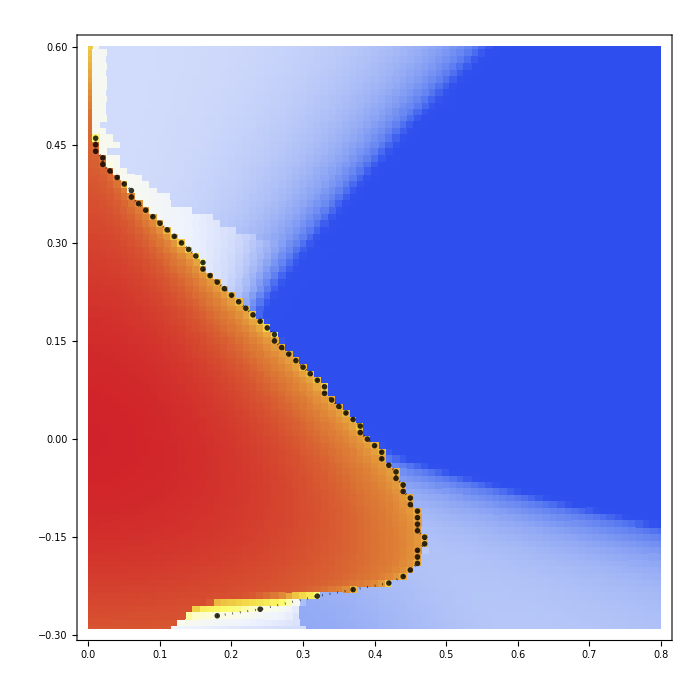

```mathematica
jointlist=SortBy[#,Last]&@(  DeleteDuplicatesBy[#,Last]&@ReverseSortBy[#,Last]&@(        Select[ en3b ,(#[[1]]>0.01∧ ( (#[[2]]>-.25∧#[[3]]<.142)∨(#[[2]]<-.25∧#[[3]]<.08) )    )&][[;;,1;;2]]     )        ) ;
gapclosing= ListPlot[jointlist,PlotMarkers->"OpenMarkers",PlotStyle->{{Black,Dotted,Thick,Opacity[.8]}}, Joined->True,PlotRange->All,ImageSize->Large];

fig3b=Module[{minmax,max,contoursLevels,colors,δ=0,imgs=700},
minmax=MinMax@Abs[  χKH3b[[;;,3]]  ]; Print[minmax];(*
minmax=MinMax@Abs[  χKH3[[;;,3]]  ]; Print[minmax];*)
max=N@(Ceiling[minmax[[2]] 100]/100);(*contoursLevels=Table[ (max/10)  x ,{x,1,10}];*)
colors={{0,Lighter@Orange},{0.05,White},(*{0.5-δ,White},{0.5+δ,White},*){1,Darker@Cyan}};
Show[ListDensityPlot[ Join[ χKH3b], PlotRange-> {{0,.8},{-.29,.6},{0,1.01}}, 
ImageSize->imgs,(*PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}},*)Frame->True, (*PlotLabel->MaTeX["\\left< \\mathrm{U}_\\gamma^{\\gamma\\gamma}\\right> \\quad \\mathbf{h}\\parallel \\mathbf{a}",Magnification->2]   , *)PlotLegends->BarLegend[ "TemperatureMap",None,LegendLabel->MaTeX["\\mathrm{U}_{\\gamma}^{\\gamma \\gamma}\\;\\;   ",Magnification->2],LegendMarkerSize-> {20,300},LabelStyle->{Black,FontSize->20,FontFamily->"Helvetica"}  ]  ,
 FrameStyle->Directive[Black,20], FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{"h","\\Gamma  "},ColorFunction->(ColorData["TemperatureMap",((#)^1 )]&)(*(Blend[colors,#/ minmax[[2]]]&)  *), ColorFunctionScaling->True,InterpolationOrder->0  ,MeshFunctions->{#1 & , #2 & },
Epilog->{Inset[MaTeX["\\textbf{KSL}",Magnification->2.5],Scaled[{.15,.3}],Scaled[{.5,0}]],
(*Inset[MaTeX["\\textbf{PP}",Magnification->2.5],Scaled[{.8,.3}],Scaled[{.5,0}]]  ,*)
Inset[MaTeX["\\mathrm{(b)}",Magnification->2.5],Scaled[{.12,.92}],Scaled[{.5,.5}]]  }
,ClippingStyle->Automatic     ]
(*,
Plot[  {.52+.045x,-.7+.95Sqrt[x]  },{x,0.015,1.19} , PlotStyle->{{Black,Thickness[0.005],Opacity[.8] }} ]*)
,gapclosing]        ]
```

```mathematica
Module[{Fig3bRaster},
Fig3bRaster=Rasterize[fig3b,"Image",RasterSize->5000];
Export["C:\\User\\lucas\\Desktop\\Wolfram Mathematica\\PhD-codes\\Figures_PhD\\New3\\fig3b.pdf"  ,Fig3bRaster  ];
]
```

#### other

```mathematica
Module[{minmax,max,contoursLevels,colors,δ=0,imgs=500},
minmax=MinMax@Abs[  χKH[[;;,3]]  ]; Print[minmax];
minmax=MinMax@Abs[  χKHc[[;;,3]]  ]; Print[minmax];max=N@(Ceiling[minmax[[2]] 100]/100);(*contoursLevels=Table[ (max/10)  x ,{x,1,10}];*)
colors={{0,Lighter@Orange},{0.05,White},(*{0.5-δ,White},{0.5+δ,White},*){1,Darker@Cyan}};
Show[ListDensityPlot[ Join[ χKH(*,{{1.19,-0.69,0.},{1.19,0.8,0.}}   *)], PlotRange-> {{0,1.51},{-.28,1.01},{0,1.01}}, 
ImageSize->imgs,(*PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}},*)Frame->True, PlotLabel->MaTeX["\\left< \\mathrm{U}_\\gamma^{\\gamma\\gamma}\\right>  \\qquad \\mathbf{h} \\parallel \\mathbf{a} ",Magnification->1.4]   , PlotLegends->Automatic , FrameStyle->Directive[Black,16], FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"h","\\Gamma  "},ColorFunction->(ColorData["TemperatureMap",((#)^1.1  )]&)(*(Blend[colors,#/ minmax[[2]]]&)  *), ColorFunctionScaling->True,InterpolationOrder->0  (*,Contours->5(*contoursLevels*)*),
Epilog->{Inset[MaTeX["\\text{KSL}",Magnification->2],Scaled[{.1,.3}],Scaled[{.5,0}]],
Inset[MaTeX["\\text{PP}",Magnification->2],Scaled[{.8,.3}],Scaled[{.5,0}]]  },ClippingStyle->Automatic     ]
(*,
Plot[  {.52+.045x,-.7+.95Sqrt[x]  },{x,0.015,1.19} , PlotStyle->{{Black,Thickness[0.005],Opacity[.8] }} ]*)
]        ]
```

```mathematica
Export["C:\\User\\lucas\\Desktop\\Wolfram Mathematica\\PhD-codes\\Figures_PhD\\Fig3b_ha.pdf"  ,%   ];
```

```mathematica
Module[{minmax,max,contoursLevels,colors,δ=0,imgs=500},
minmax=MinMax@Abs[  ωHG[[;;,3]]  ]; Print[minmax];
minmax=MinMax@Abs[  χKH3[[;;,3]]  ]; Print[minmax];max=N@(Ceiling[minmax[[2]] 100]/100);(*contoursLevels=Table[ (max/10)  x ,{x,1,10}];*)
colors={{0,Lighter@Orange},{0.05,White},(*{0.5-δ,White},{0.5+δ,White},*){1,Darker@Cyan}};
Show[ListDensityPlot[ Join[ ωHG3(*,{{1.19,-0.69,0.},{1.19,0.8,0.}}   *)], PlotRange-> {{0,2.01},{-.36,1.01},{0,1.01}}, 
ImageSize->imgs,(*PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}},*)Frame->True, PlotLabel->MaTeX[" | \\left< \\sigma \\right> |   \\qquad \\mathbf{h} \\parallel \\mathbf{c}",Magnification->1.4]   , PlotLegends->Automatic , FrameStyle->Directive[Black,16], FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"h","\\Gamma  "},ColorFunction->(ColorData["TemperatureMap",(1-(#)^(4.9/5)  )]&)(*(Blend[colors,#/ minmax[[2]]]&)  *), ColorFunctionScaling->True,InterpolationOrder->0  (*,Contours->5(*contoursLevels*)*),
Epilog->{Inset[MaTeX["\\text{KSL}",Magnification->2],Scaled[{.1,.4}],Scaled[{.5,0}]],
Inset[MaTeX["\\text{PP}",Magnification->2],Scaled[{.8,.3}],Scaled[{.5,0}]]  },ClippingStyle->Automatic     ]
(*,
Plot[  {.52+.045x,-.7+.95Sqrt[x]  },{x,0.015,1.19} , PlotStyle->{{Black,Thickness[0.005],Opacity[.8] }} ]*)
]        ]
```

```mathematica
Module[{minmax,max,contoursLevels,colors,δ=0,imgs=500},
minmax=MinMax@Abs[  ωHG[[;;,3]]  ]; Print[minmax];
minmax=MinMax@Abs[  ωHGa[[;;,3]]  ]; Print[minmax];max=N@(Ceiling[minmax[[2]] 100]/100);(*contoursLevels=Table[ (max/10)  x ,{x,1,10}];*)
colors={{0,Lighter@Orange},{0.05,White},(*{0.5-δ,White},{0.5+δ,White},*){1,Darker@Cyan}};
Show[ListDensityPlot[ Join[ ωHGa(*,{{1.19,-0.69,0.},{1.19,0.8,0.}}   *)], PlotRange-> {{0,2.01},{-.28,1.01},{0,1.01}}, 
ImageSize->imgs,(*PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}},*)Frame->True, PlotLabel->MaTeX[" || \\left< \\sigma \\right> \\times \\mathbf{c} \\, ||    \\qquad \\mathbf{h} \\parallel \\mathbf{c}",Magnification->1.4]   , PlotLegends->Automatic , FrameStyle->Directive[Black,16], FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"h","\\Gamma  "},ColorFunction->(ColorData["TemperatureMap",(1-(#)^(5/5)  )]&)(*(Blend[colors,#/ minmax[[2]]]&)  *), ColorFunctionScaling->True,InterpolationOrder->0  (*,Contours->5(*contoursLevels*)*),
Epilog->{Inset[MaTeX["\\text{KSL}",Magnification->2],Scaled[{.1,.4}],Scaled[{.5,0}]],
Inset[MaTeX["\\text{PP}",Magnification->2],Scaled[{.8,.3}],Scaled[{.5,0}]]  },ClippingStyle->{Green}     ]
(*,
Plot[  {.52+.045x,-.7+.95Sqrt[x]  },{x,0.015,1.19} , PlotStyle->{{Black,Thickness[0.005],Opacity[.8] }} ]*)
]        ]
```

```mathematica
(*Module[{minmax,max,contoursLevels,colors,δ=0,imgs=500},
minmax=MinMax@Abs[  ωHG[[;;,3]]  ]; Print[minmax];max=N@(Ceiling[minmax[[2]] 100]/100);(*contoursLevels=Table[ (max/10)  x ,{x,1,10}];*)
colors={{0,Lighter@Orange},{0.05,White},(*{0.5-δ,White},{0.5+δ,White},*){1,Darker@Cyan}};
Show[ListDensityPlot[ Join[ωHG(*,{{1.19,0.81,0.27},{1.19,-0.69,1}}*)], 
ImageSize->imgs, PlotRange->{0,1},(*PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}},*)Frame->True, PlotLabel->MaTeX[" \\left< \\sigma \\right> \\cdot \\mathbf{c}    \\qquad \\mathbf{h} \\parallel \\mathbf{c}",Magnification->1.4]   , PlotLegends->Automatic , FrameStyle->Directive[Black,16], FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"h","\\Gamma  "},ColorFunction->(ColorData["TemperatureMap",(1-(#)^(3/5)  )]&),  (*(Blend[colors,#/ minmax[[2]]]&)  *) ColorFunctionScaling->True,InterpolationOrder-> 2  (*,Contours->5(*contoursLevels*)*),
Epilog->{Inset[MaTeX["\\text{KSL}",Magnification->2],Scaled[{.2,.5}],Scaled[{.5,0}]],
Inset[MaTeX["\\text{PP}",Magnification->2],Scaled[{.7,.15}],Scaled[{.5,0}]]  },ClippingStyle->Automatic        ],
Plot[  {.52+.045x,-.7+.95Sqrt[x]  },{x,0.015,1.19} , PlotStyle->{{Black,Thickness[0.005],Opacity[.8] }} ]
]        ]  *)
```

```mathematica
Export["C:\\User\\lucas\\Desktop\\Wolfram Mathematica\\PhD-codes\\Magnetization_out_of_plane.pdf"  ,%   ];
```

```mathematica
(*Module[{minmax,max,contoursLevels,colors,δ=0,imgs=500},

minmax=MinMax@Abs[  Wp[[;;,3]]  ];

max=N@(Ceiling[minmax[[2]] 100]/100);
(*contoursLevels=Table[ (max/10)  x ,{x,1,10}];*)
colors={{0,Lighter@Orange},{0.05,White},(*{0.5-δ,White},{0.5+δ,White},*){1,Darker@Cyan}};

{
ListDensityPlot[ Wp, 
ImageSize->imgs,(*PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}},*)Frame->True, PlotLabel->MaTeX[" W_p  \\qquad \\mathbf{h} \\parallel \\mathbf{c}",Magnification->1.4]   , PlotLegends->Automatic , FrameStyle->Directive[Black,16], FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"h","\\Gamma  "},ColorFunction->(Blend[colors,#/ minmax[[2]]]&)  , ColorFunctionScaling->False,InterpolationOrder-> 2  (*,Contours->5(*contoursLevels*)*),
Epilog->{Inset[MaTeX["\\text{KSL}",Magnification->2],Scaled[{.1,.5}],Scaled[{.5,0}]],
Inset[MaTeX["\\text{PP}",Magnification->2],Scaled[{.7,.15}],Scaled[{.5,0}]]  },ClippingStyle->{{Lighter@Pink,Opacity[.5]}}  
] 
}
]*)
```

```mathematica
(*Module[{χK=χKH,minmax,max,contoursLevels,colors,δ=0,imgs=500},

minmax=MinMax@Abs[  χK[[;;,3]] ];

max=N@(Ceiling[minmax[[2]] 100]/100);
(*contoursLevels=Table[ (max/10)  x ,{x,1,10}];*)
colors={{0,Lighter@Orange},{0.05,White},(*{0.5-δ,White},{0.5+δ,White},*){1,Darker@Cyan}};

plotFig3A=ListContourPlot[ χK, 
ImageSize->imgs,(*PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}},*)Frame->True, PlotLabel->MaTeX[" \\mathrm{U}^{\\gamma \\gamma}_\\gamma  = \\left< \\mathrm{i} c^\\gamma_i c^\\gamma_j \\right>  \\quad \\mathbf{h} \\parallel \\mathbf{c}",Magnification->1.4]   , PlotLegends->BarLegend[Automatic,All] , FrameStyle->Directive[Black,16], FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"h","\\Gamma  "},ColorFunction->(Blend[colors,#/ minmax[[2]]]&)  , ColorFunctionScaling->False,InterpolationOrder-> 1  ,Contours->5(*contoursLevels*),
Epilog->{Inset[MaTeX["\\text{KSL}",Magnification->2],Scaled[{.1,.5}],Scaled[{.5,0}]],
Inset[MaTeX["\\text{PP}",Magnification->2],Scaled[{.7,.15}],Scaled[{.5,0}]]  }
] 
]*)
```

```mathematica
(*int=Interpolation[χKH[[1;;-1]] ];
Show[{ContourPlot[int[x,y],{x,0,.6},{y,-.7,.7}]}]*)
```

```mathematica
{min,max}=MinMax@Abs[  ΔW[[;;,3]]  ];  Print[{min,max}];
ListDensityPlot[ Join[ΔW(*,{{1.19,0.81,0},{1.19,-0.69,0}}*)]   ,ImageSize->500,PlotLabel->MaTeX[ "\\Delta \\mathrm{V}"
(*" \\mathrm{tr}\\left( \\mathrm{W}^\\mathrm{T} \\mathrm{G}^{\\gamma}\\right) = \\left< \\mathrm{i} c^\\gamma_i \\mathrm{G}^{\\gamma} c^\\gamma_i \\right>  \\; , \\quad \\mathbf{h} \\parallel \\mathbf{c}"*),Magnification->1.4]   , Frame->True, PlotLegends->Automatic , FrameStyle->Directive[Black,16], FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"h","\\Gamma  "},
ColorFunction->"TemperatureMap",ColorFunctionScaling->True,ClippingStyle->Automatic,PlotRange->{0,0.05}  ]
```

```mathematica
Export["C:\\User\\lucas\\Desktop\\Wolfram Mathematica\\PhD-codes\\DeltaW.pdf"  ,%   ];
```

#### line plot

```mathematica
Module[{title,img=700,x=-.03}, title="J=0, \\, K=-1 , \\,   \\mathbf{h}=0.2 \\mathbf{c}";
gK=ListPlot[χKH,Joined->True,PlotMarkers->{"●",Small}, PlotStyle->{Darker[Blue]},Frame->True,FrameStyle->Directive[Black,16],PlotLabel->(MaTeX[#,Magnification->1.6]&)@" ",FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"\\Gamma ","\\text{MF parameters}"},ImageSize->img,PlotLegends->Placed[(MaTeX[#,Magnification->1.3]&)/@{"\\mathrm{U}_{\\!K}\\!=\\mathrm{U}_{\\gamma}^{\\gamma\\gamma}"},{.901+x,.94}],
PlotRange->All,Frame->True,FrameStyle->Directive[Black,16], ImageSize->img,PlotRange->All,GridLines->None];
gc=ListPlot[χcH,Joined->True,PlotMarkers->{"●",Small}, PlotStyle->{Darker[Red]},Frame->True,FrameStyle->Directive[Black,16],PlotLabel->(MaTeX[#,Magnification->1.6]&)@title,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"\\Gamma ","\\text{MF parameters}"},ImageSize->img,PlotLegends->Placed[(MaTeX[#,Magnification->1.3]&)/@{"\\mathrm{U}_{0}=\\mathrm{U}_{\\gamma}^{00}"},{.9+x,.9}],PlotRange->All,Frame->True,FrameStyle->Directive[Black,16], ImageSize->img,PlotRange->All,GridLines->Automatic];
gΓ = ListPlot[χΓH,Joined->True,PlotMarkers->{"●",Small}, PlotStyle->{ Orange },Frame->True,FrameStyle->Directive[Black,16],PlotLabel->(MaTeX[#,Magnification->1.6]&)@title,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"\\Gamma ","\\text{MF parameters}"},ImageSize->img,PlotLegends->Placed[(MaTeX[#,Magnification->1.3]&)/@{"\\mathrm{U}_{\\Gamma}=\\mathrm{U}_{\\gamma}^{\\alpha\\beta}"},{.903+x,.86}],
PlotRange->All,Frame->True,FrameStyle->Directive[Black,16], ImageSize->img,PlotRange->All,GridLines->Automatic];
gJ = ListPlot[χJH,Joined->True,PlotMarkers->{"●",Small}, PlotStyle->{ Orange },Frame->True,FrameStyle->Directive[Black,16],PlotLabel->(MaTeX[#,Magnification->1.6]&)@title,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"\\Gamma ","\\text{MF parameters}"},ImageSize->img,PlotLegends->Placed[(MaTeX[#,Magnification->1.3]&)/@{"\\mathrm{U}_{J}=\\mathrm{U}_{\\gamma}^{\\alpha\\alpha}"},{.9+x,.82}],
PlotRange->All,Frame->True,FrameStyle->Directive[Black,16], ImageSize->img,PlotRange->All,GridLines->Automatic];
gM = ListPlot[ωH,Joined->True,PlotMarkers->{"●",Small}, PlotStyle->{Darker[Green]},Frame->True,FrameStyle->Directive[Black,16],PlotLabel->(MaTeX[#,Magnification->1.6]&)@title,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"\\Gamma ","\\text{MF parameters}"},ImageSize->img,PlotLegends->Placed[(MaTeX[#,Magnification->1.3]&)/@{"\\langle \\sigma \\rangle = \\mathrm{W}^{0\\alpha} \\hat{h}^{\\alpha}"},{.919+x,.82}],
PlotRange->All,Frame->True,FrameStyle->Directive[Black,16], ImageSize->500,PlotRange->All,GridLines->Automatic];
Show[gK,gc,(*gJ,*)gM, gΓ,PlotRange-> { {-0.75,.75},{-1.1,1.1} }  ]
]
```

also, we could insert both Γ and J in the horizontal axis, just changing the plot markers

```mathematica
NbName = "705"; 
		Ls =Range[40,40,2]; 	    tV={0};				hV={{0.001,0,0}};
		steps=600;                                     acuracy=6;                               ΔeV=0.099999;                                           eVs=Table[ 1700 ξ, {ξ,0,0,ΔeV} ] ; 

		Js=Table[j,{j,-1,1,.05}];
		Ks={-1.};
		Γs= {0.};
		hV=Table[{h,0,0},{h,0.2,0.2,.2}];

		ts = Table[ {5x,160,-12x,0,-60},{x,tV}];
		hs =Table[  h[[1]]  hAngle[h[[2]],h[[3]]] , {h,hV}];  
		eV0=0;U=2600;JH=300;

		Module[{parameters0,parameters1},
				parameters0=Tuples[{Js,Ks,Γs,hs}];
				parameters1=Tuples[{Js,Ks,Γs,hV}];
				parameters={Table[  Flatten[{ parameters0[[i]],parameters1[[i]],{0},{0}},1],  {i,1,Length@parameters0}]};
		]
```

```mathematica
ωH2={};χKH2={};χcH2={};χΓH2={};χJH2={};
 Do[Module[{L,Nc,J,K, Γ, h,jG,LG,en,ξG,EnG,η=0,l,χ0,ω0, χc,χK,ωM,χJ,χΓ}, l=1;
L=Ls[[l]];
{J,K, Γ, h}=parameters[[1,p]][[1;;4]];
{jG,LG,χ0,ω0,ξG,EnG}= loadData[toPath[parameters[[1,p]],L,acuracy,"free",NbName ]  ];

χc=1/3( χ0[[1]][[1,1]]   + χ0[[2]][[1,1]]+χ0[[3]][[1,1]]);
χJ=1/6( χ0[[1]][[3,3]]+χ0[[1]][[4,4]] + χ0[[2]][[2,2]]+ χ0[[2]][[4,4]]+χ0[[3]][[2,2]] +χ0[[3]][[3,3]]   ); 
χK=1/3( χ0[[1]][[2,2]]   + χ0[[2]][[3,3]]+χ0[[3]][[4,4]] - 3χJ );
χΓ=1/6( χ0[[1]][[3,4]]+χ0[[1]][[4,3]] + χ0[[2]][[2,4]]+ χ0[[2]][[4,2]]+χ0[[3]][[2,3]] +χ0[[3]][[3,2]]   );
ωM= 1/(2Norm[h]) ( h.{ω0[[1]][[2,1]],ω0[[1]][[3,1]],ω0[[1]][[4,1]]}   + h.{ω0[[2]][[2,1]],ω0[[2]][[3,1]],ω0[[2]][[4,1]]}   );

 AppendTo[ωH2,{Γ,ωM }]; AppendTo[χKH2,{Γ,χK}]; AppendTo[χcH2,{Γ,χc}]; AppendTo[χΓH2,{Γ,χΓ}];  AppendTo[χJH2,{Γ,χJ}];               ];
, {p,1,Length[parameters[[1]] ]} ]
```

```mathematica
Module[{title}, title="J=0, \\, K=-1 , \\,   \\mathbf{h}=0.2 \\mathbf{c}";
g1=ListPlot[{χKH,χcH,χΓH,χJH,ωH},Joined->True,PlotMarkers->"○" ,
 PlotStyle->{Darker[Blue],Darker[Red],Orange,Pink,Darker[Green]},
Frame->True,FrameStyle->Directive[Black,16],
PlotLabel->(MaTeX[#,Magnification->1.6]&)@title,
FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"\\Gamma[\\circ] , \\, J [\triangle] ","\\text{MF parameters}"},
ImageSize->500,
PlotLegends->Placed[(MaTeX[#,Magnification->1.3]&)/@{"\\mathrm{U}_K=\\mathrm{U}_{\\gamma}^{\\gamma\\gamma}","\\mathrm{U}_{0}=\\mathrm{U}_{\\gamma}^{00}","\\mathrm{U}_{\\Gamma}=\\mathrm{U}_{\\gamma}^{\\alpha\\beta}","\\mathrm{U}_{J}=\\mathrm{U}_{\\gamma}^{\\alpha\\alpha}","\\braket{\\sigma}=\\mathrm{W}^{0\\alpha}\\hat{h}^{\\alpha}"},{.08,.9}],
PlotRange->All,Frame->True,FrameStyle->Directive[Black,16], ImageSize->500,PlotRange->All,GridLines->False,
PlotRange-> { -1,1 }];

g2=ListPlot[{χKH2,χcH2,χΓH2,χJH2,ωH2},Joined->True,PlotMarkers->"△" ,
 PlotStyle->{Darker[Blue],Darker[Red],Orange,Pink,Darker[Green]},
Frame->True,FrameStyle->Directive[Black,16],
ImageSize->500,
PlotRange->All,Frame->True,FrameStyle->Directive[Black,16], ImageSize->500,PlotRange->All,GridLines->False,
PlotRange-> { -1,1 }];


Show[g1,g2,PlotRange-> { {-0.72,0.72},{-1,1} }  ]
]
```

#### energy criterea

```mathematica
Module[{J,K,Γ,h,p,jG,LG,χ,ω,ξG,EnG,heff},
p=2050; 
{J,K,Γ,h}=parameters[[1,p]][[1;;4]];
{jG,LG,χ,ω,ξG,EnG}= loadData[toPath[parameters[[1,p]],L,acuracy,"free",NbName ]  ];
heff={   h[[1]]-K  ω⟦2,2,1⟧-3J  ω⟦2,2,1⟧ -2Γ ω⟦2,4,1⟧ -2Γ  ω⟦2,3,1⟧ 
,h⟦2⟧-K ω⟦2,3,1⟧-3J ω⟦2,3,1⟧ -2 Γ ω⟦2,2,1⟧ -2Γ ω⟦2,4,1⟧  
,h⟦3⟧-K  ω⟦2,4,1⟧-3J ω⟦2,4,1⟧ -2 Γ  ω⟦2,3,1⟧ -2Γ ω⟦2,2,1⟧ 
} +10^-11;
MatrixForm@Sum[ Gmat[[γ]] Chop[heff[[γ]]/Norm[heff] ], {γ,1,3}]  
]
```

```mathematica
PHdiagram=Table[ Join[EnPP[[i,1;;2]],{If[ EnKSL[[i,4]]<10^-2,0,
		If[Chop[EnKSL[[i,3]]-EnPP[[i,3]]]<10^-3,0.5,
				If[EnKSL[[i,3]]>EnPP[[i,3]],0.5,1 ] ]   ] }  ]  , {i,1,Length[EnPP]}];
```

```mathematica
Module[{colors,contoursLevels,δ=0.01,min,max},
{max,min}=-MinMax@Join[ {EnKSL[[;;,3]],EnPP[[;;,3]]} ];
(*max=minmax[[1]];*)
contoursLevels=Table[ -(min+((max-min)/9)  x ),{x,1,10}];

colors={{0,Darker@Blue},{0.5-δ,White},{1,Darker@Red}};
ListContourPlot[  #,PlotLegends->Automatic,ImageSize->400,ColorFunctionScaling->False,ColorFunction->(Blend[colors,(-#-min)/(max-min) ]&)  , Contours->contoursLevels ]&/@ {EnKSL[[;;,1;;3]],EnPP[[;;,1;;3]]}
]
```

## Fig 5 - Charge density radial plot

```mathematica
NbName = "705";  t2=160;t2p=-60; U=2600; ttU=N[t2^2 t2p/U^3];

		Ls = Range[40,40,4]; 				tV={2.74356};			
		hV= { {0.2,0,0}};

		steps=500;				acuracy=8;     eVs=Table[1700 x, {x,0,0,0.099999}];  (* eV=ξ(U-3JH)=1500ξ *)

		ts = Table[ {5x,160,-12x,0,-60},{x,tV}];
		hs =Table[  h[[1]]  hAngle[h[[2]],h[[3]]] , {h,hV}];  
		eV0=0;U=2600;JH=300;
 
		parameters=Table[
Flatten[ Table[ {N@Jr[0,JH,U,ts[[t]] ],N@Kr[0,JH,U,ts[[t]]],N@Γr[0,JH,U,ts[[t]]],hs[[h]] ,N@Jr[eVs[[ev]],JH,U,ts[[t]] ],N@Kr[eVs[[ev]],JH,U,ts[[t]]],N@Γr[eVs[[ev]],JH,U,ts[[t]]],hV[[h]],tV[[t]],eVs[[ev]]} , {t,1,Length@tV},  {h,1,Length@hV}],1] ,  {ev,1,Length@eVs}];
```

```mathematica
Module[{(*χ,ω,ξ,jG,LG,EnG ,*)gauge="g4",p,l,L,Nc,J,K,Γ,h},                 p=1; l=1;
{J,K,Γ,h}=parameters⟦1,p⟧[[1;;4]];L=Ls⟦l⟧; Nc=L^2;
{jG,LG,χ,ω,ξ,EnG}=Chop@loadData[toPath[parameters[[1,p]],L,acuracy, gauge,NbName ]  ];
Print[ AbsoluteTiming[  hefflist=HeffList[J,K,Γ,h,ω]; ] ];(*
Print[ AbsoluteTiming[Htest = HMF[J,K,Γ,h,χ,ω,L,L,.5 {hefflist,hefflist},.5 {hefflist,hefflist},{hefflist,hefflist}] ;  ] ];*)

]
```

{0.0000579,Null}

```mathematica
χ[[1]]//Length
```

1600

### mudar a escala da figura

```mathematica
Module[{ bonds,linethick , title, χ,ω,ξ,jG,LG ,gauge="g4", Jv,Kv,Γv,J,K,Γ,Nc,h ,u0,H,T,u,t,t0,c11,c21,c12,c22,sNN,sNNN,δn,δn1,d,κ,p,l,tp,hp},
L=Ls[[1]]; 
sites= ringsVortex[L,2];
linethick=.012 (Log[7]/Log[L]);
size = 2 0.013 (Log[7]/Log[L])^2 ;
l=1;
p=1;tp=⌈p/Length@hV⌉;hp=Mod[p,Length@hV,1]; 		 
	{J,K,Γ,h}=parameters⟦1,p⟧[[1;;4]];L=Ls⟦l⟧; Nc=L^2;
	{jG,LG,χ,ω,ξ,EnG}=Chop@loadData[toPath[parameters[[1,p]],L,acuracy, gauge,NbName ]  ];
	Kv= uniform[K,L,L];Jv=uniform[J,L,L];Γv=uniform[Γ,L,L];
	d=parameters[[1,p]][[8]]; 
	u0= gauge4v[ uniformU[-1,L] ,L];     
        t=ts[[tp]];                   
                                                                                                                      
		c11=coefTriang11[JH,U,t];c21=coefTriang21[JH,U,t];  c12=coefTriang12[JH,U,t];c22=coefTriang22[JH,U,t];  
		sNN = sscNN[χ,ω,L]; sNNN= sscNNN[ξ,ω,L];
		δn=densityTriang[L,c11,c21,c12,c22,sNN,0  sNNN];
		(* δn1=  Module[ {max=Max[Abs@δn]},   δn/max    ];	 *)
max=Max@Abs[δn];
δn0=δn/Max@Abs[δn];


];
```

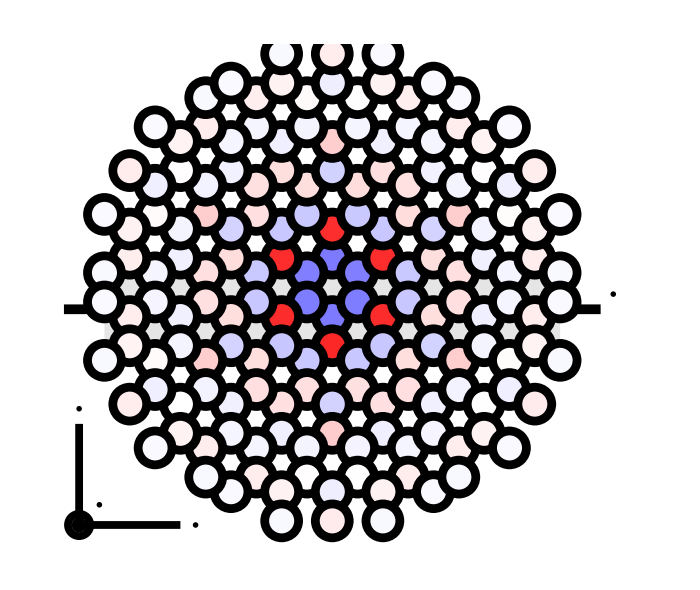

```mathematica
maxN=Abs[1/ttU]max;

L=20;
linethick=.012 (Log[7]/Log[L]);
size = 2 0.013 (Log[7]/Log[L])^2 ;
sites = Module[{m0,n0,d1,d2,d0,r2,v=2,L=40},   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;d0=Min[d1,d2];
 d0=10; {m0,n0}=positionVortex[v,L];Rv=m0 nx+n0 ny+{0,1/(√3)}; 
Select[SortBy[Flatten[Table[{σ,m,n,N@Norm[position[σ,m,n]-Rv]},{σ,0,1},{m,-2,L+1},{n,-2,L+1} ],2] ,Last], #[[4]]<=((d0-0.5)/2)&]  ];
barlegend=BarLegend[(* { chargeCF[#/maxN]&,{-maxN,maxN} }, None,LabelStyle->{Black,FontSize->16,FontFamily->"Helvetica" }  *)
{chargeCF[#/maxN]&,{-maxN,maxN} },None,LegendLabel->MaTeX["\\delta n_l \\qquad    ",Magnification->3],LegendMarkerSize-> {20,250},LabelStyle->{Black,FontSize->20,FontFamily->"Helvetica"} ];
L=40;
origin={-5.3,-5}+Rv+{+.3,+.3};
lattice=
Table[Module[{σ=sites[[i,1]],m=sites[[i,2]],n=sites[[i,3]]},
{  {Black,PointSize[4 size],Point[position[σ,m,n]]    },
{chargeCF[δn0[[Mod[m,L]+Mod[n,L] L+1,σ+1]]     ],PointSize[2.35  size],Point[position[σ,m,n]]    }     
}],{i,1,Length@sites} ];	
grap4=Graphics[{
{White,Line[{{5.3,0}+Rv ,{6,0}+Rv  } ]  }   ,
{Thickness[.1],Gray,Opacity[.2],Line[{{-4.5,0}+Rv-{0,3/(4 √3)} ,{4.5,0}+Rv-{0,3/(4 √3)}  } ]  }   ,{Thickness[.01],Black,Opacity[1],Arrowheads[.04], Arrow[{{-5.3,0}+Rv-{0,3/(4 √3)} ,{5.3,0}+Rv-{0,3/(4 √3)}  } ]  }    ,lattice  ,
{Thickness[.008],Black,Opacity[1],Arrowheads[.04], Arrow[{{-.05,0}+origin ,{2,0}+origin } ]  }  ,
{Thickness[.008],Black,Opacity[1],Arrowheads[.04], Arrow[{{0,-.05}+origin ,origin+{0,2}  } ]  } ,
{Thickness[.008],Black,Opacity[1],Circle[origin ,.22  ]} ,
{Thickness[.008],Black,Opacity[1],Circle[origin ,.07  ]} 
},
 Epilog->{Inset[MaTeX["R_{1}",Magnification->2],{5.55,.3}+Rv-{0,3/(4 √3)} ,Scaled[{.5,.5}]],Inset[MaTeX["c",Magnification->2],{.4,0+.4}+origin    ],
Inset[MaTeX["a",Magnification->2],origin+{2.3,0}    ],Inset[MaTeX["b",Magnification->2],origin+{0,2.3}  ]}  ,ImageSize->700];

fig4=Show@Legended[grap4,Placed[barlegend,Scaled[{1,0.5}] ]]
```

```mathematica
Export["C:\\User\\lucas\\Desktop\\Wolfram Mathematica\\PhD-codes\\Figures_PhD\\New2\\Fig4.pdf",    fig4];
```

## Fig 6 - Charge density line plot

```mathematica
(*Simplify@hAngle[180/π ArcTan[√2],180]*)
```

```mathematica
NbName = "705";   t2=160;t2p=-60; U=2600; ttU=N[t2^2 t2p/U^3];

		Ls = Range[40,40,4]; 				tV={0};			
		hV= {  {0.0001,0,0}  };hV= {  {0.3,0,0}  };

		steps=500;				acuracy=8;     eVs=Table[1700 x, {x,0,0,0.099999}];  (* eV=ξ(U-3JH)=1500ξ *)

		ts = Table[ {5x,160,-12x,0,-60},{x,tV}];
		hs =Table[  h[[1]]  hAngle[h[[2]],h[[3]]] , {h,hV}];  
		eV0=0;U=2600;JH=300;
 
		parameters=Table[
Flatten[ Table[ {N@Jr[0,JH,U,ts[[t]] ],N@Kr[0,JH,U,ts[[t]]],N@Γr[0,JH,U,ts[[t]]],hs[[h]] ,N@Jr[eVs[[ev]],JH,U,ts[[t]] ],N@Kr[eVs[[ev]],JH,U,ts[[t]]],N@Γr[eVs[[ev]],JH,U,ts[[t]]],hV[[h]],tV[[t]],eVs[[ev]]} , {t,1,Length@tV},  {h,1,Length@hV}],1] ,  {ev,1,Length@eVs}];
xVortexCenter=10;

Module[{χ,ω,ξ,jG,LG,EnG ,gauge="g4", Jv,Kv,Γv,J,K,Γ,L,Nc,h ,u0,H,T,u,t,t0,c11,c21,c12,c22,sNN,sNNN,δn,δn1,d,κ,p,l,tp,hp},
p=1;l=1;
	{J,K,Γ,h}=parameters⟦1,p⟧[[1;;4]];L=Ls⟦l⟧; Nc=L^2;
	{jG,LG,χ,ω,ξ,EnG}=Chop@loadData[toPath[parameters[[1,p]],L,acuracy, gauge,NbName ]  ];
	Kv= uniform[K,L,L];Jv=uniform[J,L,L];Γv=uniform[Γ,L,L];	d=parameters[[1,p]][[8]]; 	u0= gauge4v[ uniformU[-1,L] ,L];             t=ts[[p]];               
		c11=coefTriang11[JH,U,t];c21=coefTriang21[JH,U,t];  c12=coefTriang12[JH,U,t];c22=coefTriang22[JH,U,t];  
		sNN = sscNN[χ,ω,L]; sNNN= sscNNN[ξ,ω,L];
		δn=densityTriang[L,c11,c21,c12,c22,sNN,0  sNNN];	(* δn1=  Module[ {max=Max[Abs@δn]},   δn/max    ];	 *)
δnP=δn;
chPlotZZ0=Module[{points,title,m0=0,n0=L-1,min,max}, {min,max}=1/Abs[ttU] MinMax[Abs@δn]; (*Print[max];*)
points = Table[   Module[   {σ=Mod[i,2],m,n},m=Mod[m0+⌊(i-1)/2⌋,L];n=Mod[n0-⌊(i-1)/2⌋-1+σ,L]; 
  {position[σ,m,n][[1]]-xVortexCenter, 1/Abs[ttU] Abs@δn[[m+n L+1,σ+1]]    }     ]     ,{i,1,2L+1}];ListLogPlot[ Sort@points,Joined->True,PlotStyle->Directive[Gray,Dashed,Bold],Frame->True,ImageSize->1000,FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{"x \\; ", "\\vert \\, \\delta n_{l} \\,  \\vert"}, FrameStyle->Directive[Black,20],PlotRange->{{0-xVortexCenter,L/2-xVortexCenter},{1/Abs[ttU] 10^-10,1/Abs[ttU] 1.25 10^-6}}                       ]            ];
];
```

```mathematica
xVortexCenter=10;
```

```mathematica
tV={3};  hV= {  {0.3,0,0}  }; acuracy=7;   
		ts = Table[ {5x,160,-12x,0,-60},{x,tV}];
		hs =Table[  h[[1]]  hAngle[h[[2]],h[[3]]] , {h,hV}];   
		parameters=Table[
Flatten[ Table[ {N@Jr[0,JH,U,ts[[t]] ],N@Kr[0,JH,U,ts[[t]]],N@Γr[0,JH,U,ts[[t]]],hs[[h]] ,N@Jr[eVs[[ev]],JH,U,ts[[t]] ],N@Kr[eVs[[ev]],JH,U,ts[[t]]],N@Γr[eVs[[ev]],JH,U,ts[[t]]],hV[[h]],tV[[t]],eVs[[ev]]} , {t,1,Length@tV},  {h,1,Length@hV}],1] ,  {ev,1,Length@eVs}];
Module[{χ,ω,ξ,jG,LG,EnG ,gauge="g4", Jv,Kv,Γv,J,K,Γ,L,Nc,h ,u0,H,T,u,t,t0,c11,c21,c12,c22,sNN,sNNN,δn,δn1,d,κ,p,l,tp,hp}, l=1;
p=1;tp=⌈p/Length@hV⌉;hp=Mod[p,Length@hV,1]; 		 
	{J,K,Γ,h}=parameters⟦1,p⟧[[1;;4]];L=Ls⟦l⟧; Nc=L^2;
	{jG,LG,χ,ω,ξ,EnG}=Chop@loadData[toPath[parameters[[1,p]],L,acuracy, gauge,NbName ]  ];
	Kv= uniform[K,L,L];Jv=uniform[J,L,L];Γv=uniform[Γ,L,L];
	d=parameters[[1,p]][[8]]; 
	u0= gauge4v[ uniformU[-1,L] ,L];     
        t=ts[[tp]];                                                                                   
		c11=coefTriang11[JH,U,t];c21=coefTriang21[JH,U,t];  c12=coefTriang12[JH,U,t];c22=coefTriang22[JH,U,t];  
		sNN = sscNN[χ,ω,L]; sNNN= sscNNN[ξ,ω,L];
		δn=densityTriang[L,c11,c21,c12,c22,sNN,0  sNNN];  δnHc=δn;
chPlotZZHc=Module[{points,title,m0=0,n0=L-1,min,max}, {min,max}=MinMax[Abs@δn]; (*Print[max];*) maxC=1/Abs[ttU] max;
points = Table[   Module[   {σ=Mod[i,2],m,n},m=Mod[m0+⌊(i-1)/2⌋,L];n=Mod[n0-⌊(i-1)/2⌋-1+σ,L]; 
Style[   {position[σ,m,n][[1]]-xVortexCenter, 1/Abs[ttU] Abs@δn[[m+n L+1,σ+1]]    } , chargeCFgray[δn[[m+n L+1,σ+1]]/max ], Bold      ]     ]     ,{i,1,2L+1}];ListLogPlot[ Sort@points,Joined->True,Frame->True,ImageSize->1000,FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{"x \\; ", "\\vert \\, \\delta n_{l} \\,  \\vert"}, FrameStyle->Directive[Black,Thick,26],PlotRange->{{0-xVortexCenter,L/2-xVortexCenter},{1/Abs[ttU] 10^-9.5,1/Abs[ttU] 1.25 10^-6}}                       ]            ];
]
```

```mathematica
NbName = "705";   t2=160;t2p=-60; U=2600; ttU=N[t2^2 t2p/U^3];

		Ls = Range[40,40,4]; 				tV={0};			
		hV= {  {0.2,180/π ArcTan[√2],180}  };

		steps=500;				acuracy=1.5;     eVs=Table[1700 x, {x,0,0,0.099999}];  (* eV=ξ(U-3JH)=1500ξ *)

		ts = Table[ {5x,160,-12x,0,-60},{x,tV}];
		hs =FullSimplify@Table[  h[[1]]  hAngle[h[[2]],h[[3]]] , {h,hV}];   hV=N@hV;
		eV0=0;U=2600;JH=300;
 
		parameters=Table[
Flatten[ Table[ {N@Jr[0,JH,U,ts[[t]] ],N@Kr[0,JH,U,ts[[t]]],N@Γr[0,JH,U,ts[[t]]],hs[[h]] ,N@Jr[eVs[[ev]],JH,U,ts[[t]] ],N@Kr[eVs[[ev]],JH,U,ts[[t]]],N@Γr[eVs[[ev]],JH,U,ts[[t]]],hV[[h]],tV[[t]],eVs[[ev]]} , {t,1,Length@tV},  {h,1,Length@hV}],1] ,  {ev,1,Length@eVs}];
xVortexCenter=10;

Module[{χ,ω,ξ,jG,LG,EnG ,gauge="g4", Jv,Kv,Γv,J,K,Γ,L,Nc,h ,u0,H,T,u,t,t0,c11,c21,c12,c22,sNN,sNNN,δn,δn1,d,κ,p,l,tp,hp},
p=1;l=1;
	{J,K,Γ,h}=parameters⟦1,p⟧[[1;;4]];L=Ls⟦l⟧; Nc=L^2;
	{jG,LG,χ,ω,ξ,EnG}=Chop@loadData[toPath[parameters[[1,p]],L,acuracy, gauge,NbName ]  ];
	Kv= uniform[K,L,L];Jv=uniform[J,L,L];Γv=uniform[Γ,L,L];	d=parameters[[1,p]][[8]]; 	u0= gauge4v[ uniformU[-1,L] ,L];             t=ts[[p]];               
		c11=coefTriang11[JH,U,t];c21=coefTriang21[JH,U,t];  c12=coefTriang12[JH,U,t];c22=coefTriang22[JH,U,t];  
		sNN = sscNN[χ,ω,L]; sNNN= sscNNN[ξ,ω,L];
		δn=densityTriang[L,c11,c21,c12,c22,sNN,0  sNNN];	(* δn1=  Module[ {max=Max[Abs@δn]},   δn/max    ];	 *)
δnP=δn;
chPlotZZ0z=Module[{points,title,m0=0,n0=L-1,min,max}, {min,max}=1/Abs[ttU] MinMax[Abs@δn]; (*Print[max];*)
points = Table[   Module[   {σ=Mod[i,2],m,n},m=Mod[m0+⌊(i-1)/2⌋,L];n=Mod[n0-⌊(i-1)/2⌋-1+σ,L]; 
  {position[σ,m,n][[1]]-xVortexCenter, 1/Abs[ttU] Abs@δn[[m+n L+1,σ+1]]    }     ]     ,{i,1,2L+1}];ListLogPlot[ Sort@points,Joined->True,PlotStyle->Directive[Gray,Dashed,Bold],Frame->True,ImageSize->1000,FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{"x \\; ", "\\vert \\, \\delta n_{l} \\,  \\vert"}, FrameStyle->Directive[Black,20],PlotRange->{{0-xVortexCenter,L/2-xVortexCenter},{1/Abs[ttU] 10^-10,1/Abs[ttU] 1.25 10^-6}}                       ]            ];
];
```

```mathematica
tV={2};  hV= {  {0.2,180/π ArcTan[√2],180}  }; acuracy=5;   
		ts = Table[ {5x,160,-12x,0,-60},{x,tV}];
		hs =FullSimplify@Table[  h[[1]]  hAngle[h[[2]],h[[3]]] , {h,hV}];   hV=N@hV;
		parameters=Table[
Flatten[ Table[ {N@Jr[0,JH,U,ts[[t]] ],N@Kr[0,JH,U,ts[[t]]],N@Γr[0,JH,U,ts[[t]]],hs[[h]] ,N@Jr[eVs[[ev]],JH,U,ts[[t]] ],N@Kr[eVs[[ev]],JH,U,ts[[t]]],N@Γr[eVs[[ev]],JH,U,ts[[t]]],hV[[h]],tV[[t]],eVs[[ev]]} , {t,1,Length@tV},  {h,1,Length@hV}],1] ,  {ev,1,Length@eVs}];
Module[{χ,ω,ξ,jG,LG,EnG ,gauge="g4", Jv,Kv,Γv,J,K,Γ,L,Nc,h ,u0,H,T,u,t,t0,c11,c21,c12,c22,sNN,sNNN,δn,δn1,d,κ,p,l,tp,hp},l=1;
p=1;tp=⌈p/Length@hV⌉;hp=Mod[p,Length@hV,1]; 		 
	{J,K,Γ,h}=parameters⟦1,p⟧[[1;;4]];L=Ls⟦l⟧; Nc=L^2;
	{jG,LG,χ,ω,ξ,EnG}=Chop@loadData[toPath[parameters[[1,p]],L,acuracy, gauge,NbName ]  ];
	Kv= uniform[K,L,L];Jv=uniform[J,L,L];Γv=uniform[Γ,L,L];
	d=parameters[[1,p]][[8]]; 
	u0= gauge4v[ uniformU[-1,L] ,L];     
        t=ts[[tp]];                                                                                   
		c11=coefTriang11[JH,U,t];c21=coefTriang21[JH,U,t];  c12=coefTriang12[JH,U,t];c22=coefTriang22[JH,U,t];  
		sNN = sscNN[χ,ω,L]; sNNN= sscNNN[ξ,ω,L];
		δn=densityTriang[L,c11,c21,c12,c22,sNN,0  sNNN];  δnHz=δn;
chPlotZZHz=Module[{points,title,m0=0,n0=L-1,min,max}, {min,max}=MinMax[Abs@δn]; (*Print[max];*)maxZ=1/Abs[ttU] max;
points = Table[   Module[   {σ=Mod[i,2],m,n},m=Mod[m0+⌊(i-1)/2⌋,L];n=Mod[n0-⌊(i-1)/2⌋-1+σ,L]; 
Style[   {position[σ,m,n][[1]]-xVortexCenter,1/Abs[ttU] Abs@δn[[m+n L+1,σ+1]]    } , chargeCFgray[δn[[m+n L+1,σ+1]]/max ], Bold      ]     ]     ,{i,1,2L+1}];ListLogPlot[ Sort@points,Joined->True,Frame->True,ImageSize->1000,FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{"x \\; ", "\\vert \\, \\delta n_{l} \\,  \\vert"}, FrameStyle->Directive[Black,Thick,26],PlotRange->{{0-xVortexCenter,L/2-xVortexCenter},{1/Abs[ttU] 10^-9.5,1/Abs[ttU] 1.25 10^-6}}                       ]            ];
]
```

```mathematica
(*L=40;
Table[   Module[   {σ=Mod[i,2],m,n},m=Mod[0+⌊(i-1)/2⌋,L];n=Mod[L-1-⌊(i-1)/2⌋-1+σ,L];   {{m,n},N@position[σ,m,n][[1]], m+n L+1,σ+1 }     ]     ,{i,1,2L}]*)
(*Legended[Show[{chPlotZZHc,chPlotZZ0} ]     , BarLegend[ {chargeCFgray[#/maxC ]&, {-maxC,maxC} }  ]   ]
Legended[Show[{chPlotZZHz,chPlotZZ0} ]     , BarLegend[ {chargeCFgray[#/maxZ ]&, {-maxZ,maxZ} }  ]   ]*)
```

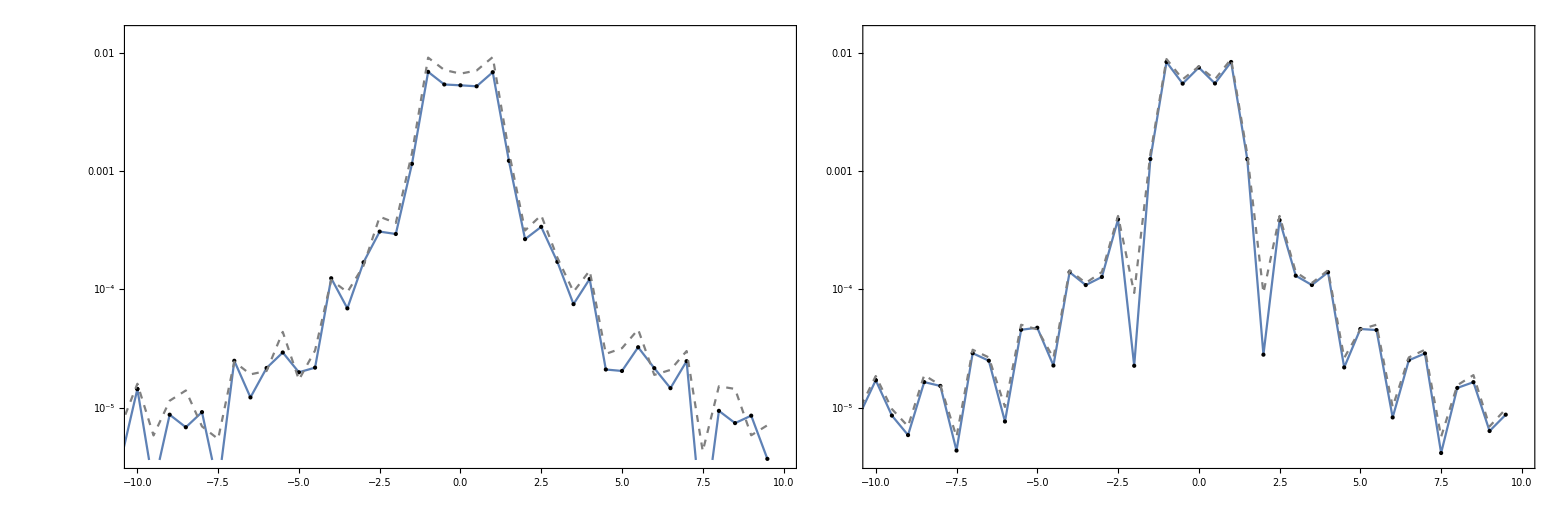

```mathematica
fig5=Legended[Show[
GraphicsRow[{  Show[{chPlotZZHc,chPlotZZ0},FrameLabel->{(MaTeX[#,Magnification->3.5]&)@"R_1 \\; ",None},(*ImageSize->1000,*)Frame->{{True,False},{True,True}} ]   , Show[{chPlotZZHz,chPlotZZ0z},FrameLabel->(MaTeX[#,Magnification->3.5]&)/@{"R_1 \\; ", "\\vert \\, \\delta n_{l} \\,  \\vert"} ,(*ImageSize->1000,*)Frame->{{True,True},{True,True}}    ]        },-110,
Epilog-> {
Inset[MaTeX["\\mathrm{(a)}",Magnification->3],{126,-75},Scaled[{.5,.5}]     ],
Inset[MaTeX["\\mathrm{(b)}",Magnification->3],{1043,-75},Scaled[{.5,.5}]   ]
}]
,ImageSize->2000]
,Placed[ BarLegend[ {chargeCFgray[#/maxZ ]&, {-maxZ,maxZ} },None,LegendLabel->MaTeX["\\delta n_l \\qquad \\quad   ",Magnification->3],LegendMarkerSize-> {30,500},LabelStyle->{Black,FontSize->26,FontFamily->"Helvetica"}  ],After] ]
```

```mathematica
Export["C:\\User\\lucas\\Desktop\\Wolfram Mathematica\\PhD-codes\\Figures_PhD\\New2\\Fig6.pdf"  ,fig5  ];
```

#### c violation

```mathematica
sitesRotated[m_,n_,σ_]:={(m-n)/2,(3 (m+n)-2 σ)/(2 √3)};
```

```mathematica
Module[{χ,ω,ξ,jG,LG ,gauge="g4", Jv,Kv,Γv,J,K,Γ,L,Nc,h ,u0,H,T,u,t,t0,c11,c21,c12,c22,sNN,sNNN,δn,δn1,d,κ,p,l,tp,hp},
l=1;
p=1;tp=⌈p/Length@hV⌉;hp=Mod[p,Length@hV,1]; 		 
	{J,K,Γ,h}=parameters⟦1,p⟧[[1;;4]];L=Ls⟦l⟧; Nc=L^2;
	{jG,LG,χ,ω,ξ,EnG}=Chop@loadData[toPath[parameters[[1,p]],L,acuracy, gauge,NbName ]  ];
	cViolation=(    Flatten[Table[      Join[sitesRotated[m,n,σ],{1/3 Abs@Sum[Tr[ Transpose[ω[[σ,m+n L +1]] ].Mmat[[γ]]  ],{γ,1,3} ]} ]  , {m,0,L/2-1},{n,0,L/2-1},{σ,1,2}],2]    );
]
```

```mathematica
Print[  {min,max}=MinMax@Abs[  cViolation[[;;,3]]  ]  ];
cvStyled=Table[ Style[    cViolation[[t]][[1;;2]]    ,ColorData["TemperatureMap"][  (cViolation[[t,3]]-min)/(max-min) ]       ]     ,{t,1,Length@cViolation}];
```

```mathematica
cvStyled=Table[ Style[ cViolation[[t]][[1;;2]],{"●",ColorData["TemperatureMap"][  (cViolation[[t,3]]-min)/(max-min) ]  }]     ,{t,1,Length@cViolation}];
```

```mathematica
Legended[
ListPlot[  cvStyled,PlotRange->  {{-5.8,5.8},{10,22}},AspectRatio->{1,1}, ImageSize->500,
PlotLabel->MaTeX[" \\mathrm{tr}\\left( \\mathrm{W}^\\mathrm{T} \\mathrm{G}^{\\gamma}\\right)  
= \\left< \\mathrm{i} c^\\gamma_i \\mathrm{G}^{\\gamma} c^\\gamma_i \\right>  \\; , \\quad \\mathbf{h}=0.2 \\,  \\mathbf{c}, \\;  \\Gamma=0.2",Magnification->1.4]   , Frame->True, PlotLegends->Automatic , FrameStyle->Directive[Black,16], FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"x","y"}
],BarLegend[ {"TemperatureMap",{min,max}},None] ]
```

```mathematica
Export["C:\\User\\lucas\\Desktop\\Wolfram Mathematica\\PhD-codes\\Figures_PhD\\DeltaW_Real.pdf"  ,%   ];
```

```mathematica
dp=ListDensityPlot[  cViolation   ,ImageSize->500,PlotRange->{{-6,6},{4,26},{0,1}},InterpolationOrder->1,PlotLabel->MaTeX[" \\mathrm{tr}\\left( \\mathrm{W}^\\mathrm{T} \\mathrm{G}^{\\gamma}\\right)  
= \\left< \\mathrm{i} c^\\gamma_i \\mathrm{G}^{\\gamma} c^\\gamma_i \\right>  \\; , \\quad \\mathbf{h}=0.2 \\,  \\mathbf{c}, \\;  \\Gamma=0.2",Magnification->1.4]   , Frame->True, PlotLegends->Automatic , FrameStyle->Directive[Black,16], FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"x","y"},
ColorFunction->"TemperatureMap",ColorFunctionScaling->True,ClippingStyle->Automatic  ]
```

```mathematica
Export["C:\\User\\lucas\\Desktop\\Wolfram Mathematica\\PhD-codes\\Fig3_Wp.pdf"  ,%   ];
```

## Fig 6 - Charge density line plot - - binary colors

```mathematica
chargeCFbi[num_]:=Module[ {t,cr},cr=Sign[num];  t= ( cr +1 )/2;                Blend[{Hue[0,1,1],Gray,Hue[0.67,1,1]  },t]       ];
```

```mathematica
(*Simplify@hAngle[180/π ArcTan[√2],180]*)
```

```mathematica
NbName = "705";   t2=160;t2p=-60; U=2600; ttU=N[t2^2 t2p/U^3];

		Ls = Range[40,40,4]; 				tV={0};			
		hV= {  {0.0001,0,0}  };hV= {  {0.3,0,0}  };

		steps=500;				acuracy=8;     eVs=Table[1700 x, {x,0,0,0.099999}];  (* eV=ξ(U-3JH)=1500ξ *)

		ts = Table[ {5x,160,-12x,0,-60},{x,tV}];
		hs =Table[  h[[1]]  hAngle[h[[2]],h[[3]]] , {h,hV}];  
		eV0=0;U=2600;JH=300;
 
		parameters=Table[
Flatten[ Table[ {N@Jr[0,JH,U,ts[[t]] ],N@Kr[0,JH,U,ts[[t]]],N@Γr[0,JH,U,ts[[t]]],hs[[h]] ,N@Jr[eVs[[ev]],JH,U,ts[[t]] ],N@Kr[eVs[[ev]],JH,U,ts[[t]]],N@Γr[eVs[[ev]],JH,U,ts[[t]]],hV[[h]],tV[[t]],eVs[[ev]]} , {t,1,Length@tV},  {h,1,Length@hV}],1] ,  {ev,1,Length@eVs}];
xVortexCenter=10;

Module[{χ,ω,ξ,jG,LG,EnG ,gauge="g4", Jv,Kv,Γv,J,K,Γ,L,Nc,h ,u0,H,T,u,t,t0,c11,c21,c12,c22,sNN,sNNN,δn,δn1,d,κ,p,l,tp,hp},
p=1;l=1;
	{J,K,Γ,h}=parameters⟦1,p⟧[[1;;4]];L=Ls⟦l⟧; Nc=L^2;
	{jG,LG,χ,ω,ξ,EnG}=Chop@loadData[toPath[parameters[[1,p]],L,acuracy, gauge,NbName ]  ];
	Kv= uniform[K,L,L];Jv=uniform[J,L,L];Γv=uniform[Γ,L,L];	d=parameters[[1,p]][[8]]; 	u0= gauge4v[ uniformU[-1,L] ,L];             t=ts[[p]];               
		c11=coefTriang11[JH,U,t];c21=coefTriang21[JH,U,t];  c12=coefTriang12[JH,U,t];c22=coefTriang22[JH,U,t];  
		sNN = sscNN[χ,ω,L]; sNNN= sscNNN[ξ,ω,L];
		δn=densityTriang[L,c11,c21,c12,c22,sNN,0  sNNN];	(* δn1=  Module[ {max=Max[Abs@δn]},   δn/max    ];	 *)
δnP=δn;
chPlotZZ0=Module[{points,title,m0=0,n0=L-1,min,max}, {min,max}=1/Abs[ttU] MinMax[Abs@δn]; (*Print[max];*)
points = Table[   Module[   {σ=Mod[i,2],m,n},m=Mod[m0+⌊(i-1)/2⌋,L];n=Mod[n0-⌊(i-1)/2⌋-1+σ,L]; 
  {position[σ,m,n][[1]]-xVortexCenter, 1/Abs[ttU] Abs@δn[[m+n L+1,σ+1]]    }     ]     ,{i,1,2L+1}];ListLogPlot[ Sort@points,Joined->True,PlotStyle->Directive[Gray,Dashed,Bold],Frame->True,ImageSize->1000,FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{"x \\; ", "\\vert \\, \\delta n_{l} \\,  \\vert"}, FrameStyle->Directive[Black,20],PlotRange->{{0-xVortexCenter,L/2-xVortexCenter},{1/Abs[ttU] 10^-10,1/Abs[ttU] 1.25 10^-6}}                       ]            ];
];
```

```mathematica
xVortexCenter=10;
```

```mathematica
tV={3};  hV= {  {0.3,0,0}  }; acuracy=7;   
		ts = Table[ {5x,160,-12x,0,-60},{x,tV}];
		hs =Table[  h[[1]]  hAngle[h[[2]],h[[3]]] , {h,hV}];   
		parameters=Table[
Flatten[ Table[ {N@Jr[0,JH,U,ts[[t]] ],N@Kr[0,JH,U,ts[[t]]],N@Γr[0,JH,U,ts[[t]]],hs[[h]] ,N@Jr[eVs[[ev]],JH,U,ts[[t]] ],N@Kr[eVs[[ev]],JH,U,ts[[t]]],N@Γr[eVs[[ev]],JH,U,ts[[t]]],hV[[h]],tV[[t]],eVs[[ev]]} , {t,1,Length@tV},  {h,1,Length@hV}],1] ,  {ev,1,Length@eVs}];
Module[{χ,ω,ξ,jG,LG,EnG ,gauge="g4", Jv,Kv,Γv,J,K,Γ,L,Nc,h ,u0,H,T,u,t,t0,c11,c21,c12,c22,sNN,sNNN,δn,δn1,d,κ,p,l,tp,hp}, l=1;
p=1;tp=⌈p/Length@hV⌉;hp=Mod[p,Length@hV,1]; 		 
	{J,K,Γ,h}=parameters⟦1,p⟧[[1;;4]];L=Ls⟦l⟧; Nc=L^2;
	{jG,LG,χ,ω,ξ,EnG}=Chop@loadData[toPath[parameters[[1,p]],L,acuracy, gauge,NbName ]  ];
	Kv= uniform[K,L,L];Jv=uniform[J,L,L];Γv=uniform[Γ,L,L];
	d=parameters[[1,p]][[8]]; 
	u0= gauge4v[ uniformU[-1,L] ,L];     
        t=ts[[tp]];                                                                                   
		c11=coefTriang11[JH,U,t];c21=coefTriang21[JH,U,t];  c12=coefTriang12[JH,U,t];c22=coefTriang22[JH,U,t];  
		sNN = sscNN[χ,ω,L]; sNNN= sscNNN[ξ,ω,L];
		δn=densityTriang[L,c11,c21,c12,c22,sNN,0  sNNN];  δnHc=δn;
chPlotZZHc=Module[{points,title,m0=0,n0=L-1,min,max}, {min,max}=MinMax[Abs@δn]; (*Print[max];*) maxC=1/Abs[ttU] max;
points = Table[   Module[   {σ=Mod[i,2],m,n},m=Mod[m0+⌊(i-1)/2⌋,L];n=Mod[n0-⌊(i-1)/2⌋-1+σ,L]; 
Style[   {position[σ,m,n][[1]]-xVortexCenter, 1/Abs[ttU] Abs@δn[[m+n L+1,σ+1]]    } , chargeCFbi[δn[[m+n L+1,σ+1]]/max ], Bold      ]     ]     ,{i,1,2L+1}];ListLogPlot[ Sort@points,Joined->True,Frame->True,ImageSize->1000,FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{"x \\; ", "\\vert \\, \\delta n_{l} \\,  \\vert"}, FrameStyle->Directive[Black,Thick,26],PlotRange->{{0-xVortexCenter,L/2-xVortexCenter},{1/Abs[ttU] 10^-9.5,1/Abs[ttU] 1.25 10^-6}}                      
]            ];
]
```

```mathematica
NbName = "705";   t2=160;t2p=-60; U=2600; ttU=N[t2^2 t2p/U^3];

		Ls = Range[40,40,4]; 				tV={0};			
		hV= {  {0.2,180/π ArcTan[√2],180}  };

		steps=500;				acuracy=1.5;     eVs=Table[1700 x, {x,0,0,0.099999}];  (* eV=ξ(U-3JH)=1500ξ *)

		ts = Table[ {5x,160,-12x,0,-60},{x,tV}];
		hs =FullSimplify@Table[  h[[1]]  hAngle[h[[2]],h[[3]]] , {h,hV}];   hV=N@hV;
		eV0=0;U=2600;JH=300;
 
		parameters=Table[
Flatten[ Table[ {N@Jr[0,JH,U,ts[[t]] ],N@Kr[0,JH,U,ts[[t]]],N@Γr[0,JH,U,ts[[t]]],hs[[h]] ,N@Jr[eVs[[ev]],JH,U,ts[[t]] ],N@Kr[eVs[[ev]],JH,U,ts[[t]]],N@Γr[eVs[[ev]],JH,U,ts[[t]]],hV[[h]],tV[[t]],eVs[[ev]]} , {t,1,Length@tV},  {h,1,Length@hV}],1] ,  {ev,1,Length@eVs}];
xVortexCenter=10;

Module[{χ,ω,ξ,jG,LG,EnG ,gauge="g4", Jv,Kv,Γv,J,K,Γ,L,Nc,h ,u0,H,T,u,t,t0,c11,c21,c12,c22,sNN,sNNN,δn,δn1,d,κ,p,l,tp,hp},
p=1;l=1;
	{J,K,Γ,h}=parameters⟦1,p⟧[[1;;4]];L=Ls⟦l⟧; Nc=L^2;
	{jG,LG,χ,ω,ξ,EnG}=Chop@loadData[toPath[parameters[[1,p]],L,acuracy, gauge,NbName ]  ];
	Kv= uniform[K,L,L];Jv=uniform[J,L,L];Γv=uniform[Γ,L,L];	d=parameters[[1,p]][[8]]; 	u0= gauge4v[ uniformU[-1,L] ,L];             t=ts[[p]];               
		c11=coefTriang11[JH,U,t];c21=coefTriang21[JH,U,t];  c12=coefTriang12[JH,U,t];c22=coefTriang22[JH,U,t];  
		sNN = sscNN[χ,ω,L]; sNNN= sscNNN[ξ,ω,L];
		δn=densityTriang[L,c11,c21,c12,c22,sNN,0  sNNN];	(* δn1=  Module[ {max=Max[Abs@δn]},   δn/max    ];	 *)
δnP=δn;
chPlotZZ0z=Module[{points,title,m0=0,n0=L-1,min,max}, {min,max}=1/Abs[ttU] MinMax[Abs@δn]; (*Print[max];*)
points = Table[   Module[   {σ=Mod[i,2],m,n},m=Mod[m0+⌊(i-1)/2⌋,L];n=Mod[n0-⌊(i-1)/2⌋-1+σ,L]; 
  {position[σ,m,n][[1]]-xVortexCenter, 1/Abs[ttU] Abs@δn[[m+n L+1,σ+1]]    }     ]     ,{i,1,2L+1}];ListLogPlot[ Sort@points,Joined->True,PlotStyle->Directive[Gray,Dashed,Bold],Frame->True,ImageSize->1000,FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{"x \\; ", "\\vert \\, \\delta n_{l} \\,  \\vert"}, FrameStyle->Directive[Black,20],PlotRange->{{0-xVortexCenter,L/2-xVortexCenter},{1/Abs[ttU] 10^-10,1/Abs[ttU] 1.25 10^-6}}                       ]            ];
];
```

```mathematica
tV={2};  hV= {  {0.2,180/π ArcTan[√2],180}  }; acuracy=5;   
		ts = Table[ {5x,160,-12x,0,-60},{x,tV}];
		hs =FullSimplify@Table[  h[[1]]  hAngle[h[[2]],h[[3]]] , {h,hV}];   hV=N@hV;
		parameters=Table[
Flatten[ Table[ {N@Jr[0,JH,U,ts[[t]] ],N@Kr[0,JH,U,ts[[t]]],N@Γr[0,JH,U,ts[[t]]],hs[[h]] ,N@Jr[eVs[[ev]],JH,U,ts[[t]] ],N@Kr[eVs[[ev]],JH,U,ts[[t]]],N@Γr[eVs[[ev]],JH,U,ts[[t]]],hV[[h]],tV[[t]],eVs[[ev]]} , {t,1,Length@tV},  {h,1,Length@hV}],1] ,  {ev,1,Length@eVs}];
Module[{χ,ω,ξ,jG,LG,EnG ,gauge="g4", Jv,Kv,Γv,J,K,Γ,L,Nc,h ,u0,H,T,u,t,t0,c11,c21,c12,c22,sNN,sNNN,δn,δn1,d,κ,p,l,tp,hp},l=1;
p=1;tp=⌈p/Length@hV⌉;hp=Mod[p,Length@hV,1]; 		 
	{J,K,Γ,h}=parameters⟦1,p⟧[[1;;4]];L=Ls⟦l⟧; Nc=L^2;
	{jG,LG,χ,ω,ξ,EnG}=Chop@loadData[toPath[parameters[[1,p]],L,acuracy, gauge,NbName ]  ];
	Kv= uniform[K,L,L];Jv=uniform[J,L,L];Γv=uniform[Γ,L,L];
	d=parameters[[1,p]][[8]]; 
	u0= gauge4v[ uniformU[-1,L] ,L];     
        t=ts[[tp]];                                                                                   
		c11=coefTriang11[JH,U,t];c21=coefTriang21[JH,U,t];  c12=coefTriang12[JH,U,t];c22=coefTriang22[JH,U,t];  
		sNN = sscNN[χ,ω,L]; sNNN= sscNNN[ξ,ω,L];
		δn=densityTriang[L,c11,c21,c12,c22,sNN,0  sNNN];  δnHz=δn;
chPlotZZHz=Module[{points,title,m0=0,n0=L-1,min,max}, {min,max}=MinMax[Abs@δn]; (*Print[max];*)maxZ=1/Abs[ttU] max;
points = Table[   Module[   {σ=Mod[i,2],m,n},m=Mod[m0+⌊(i-1)/2⌋,L];n=Mod[n0-⌊(i-1)/2⌋-1+σ,L]; 
Style[   {position[σ,m,n][[1]]-xVortexCenter,1/Abs[ttU] Abs@δn[[m+n L+1,σ+1]]    } , chargeCFbi[δn[[m+n L+1,σ+1]]/max ], Bold      ]     ]     ,{i,1,2L+1}];ListLogPlot[ Sort@points,Joined->True,Frame->True,ImageSize->1000,FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{"x \\; ", "\\vert \\, \\delta n_{l} \\,  \\vert"}, FrameStyle->Directive[Black,Thick,26],PlotRange->{{0-xVortexCenter,L/2-xVortexCenter},{1/Abs[ttU] 10^-9.5,1/Abs[ttU] 1.25 10^-6}}                       ]            ];
]
```

```mathematica
(*L=40;
Table[   Module[   {σ=Mod[i,2],m,n},m=Mod[0+⌊(i-1)/2⌋,L];n=Mod[L-1-⌊(i-1)/2⌋-1+σ,L];   {{m,n},N@position[σ,m,n][[1]], m+n L+1,σ+1 }     ]     ,{i,1,2L}]*)
(*Legended[Show[{chPlotZZHc,chPlotZZ0} ]     , BarLegend[ {chargeCFgray[#/maxC ]&, {-maxC,maxC} }  ]   ]
Legended[Show[{chPlotZZHz,chPlotZZ0} ]     , BarLegend[ {chargeCFgray[#/maxZ ]&, {-maxZ,maxZ} }  ]   ]*)
```

```mathematica
lattice = Import[ "C:\\User\\lucas\\Desktop\\Wolfram Mathematica\\PhD-codes\\Figures_PhD\\New3\\honeycomb_4v.pdf" ][[1]];
```

```mathematica
legend=Grid[  {  {Graphics[{Blue,Disk[{0,1},5]},ImageSize->12], MaTeX["\\; \\delta n_{l}>0",Magnification->2.5]    } , {Graphics[{Red,Disk[{0,1},5]},ImageSize->12], MaTeX["\\; \\delta n_{l}<0",Magnification->2.5]    }    }  ,Frame->None,Alignment->{Center,Center} ];
```

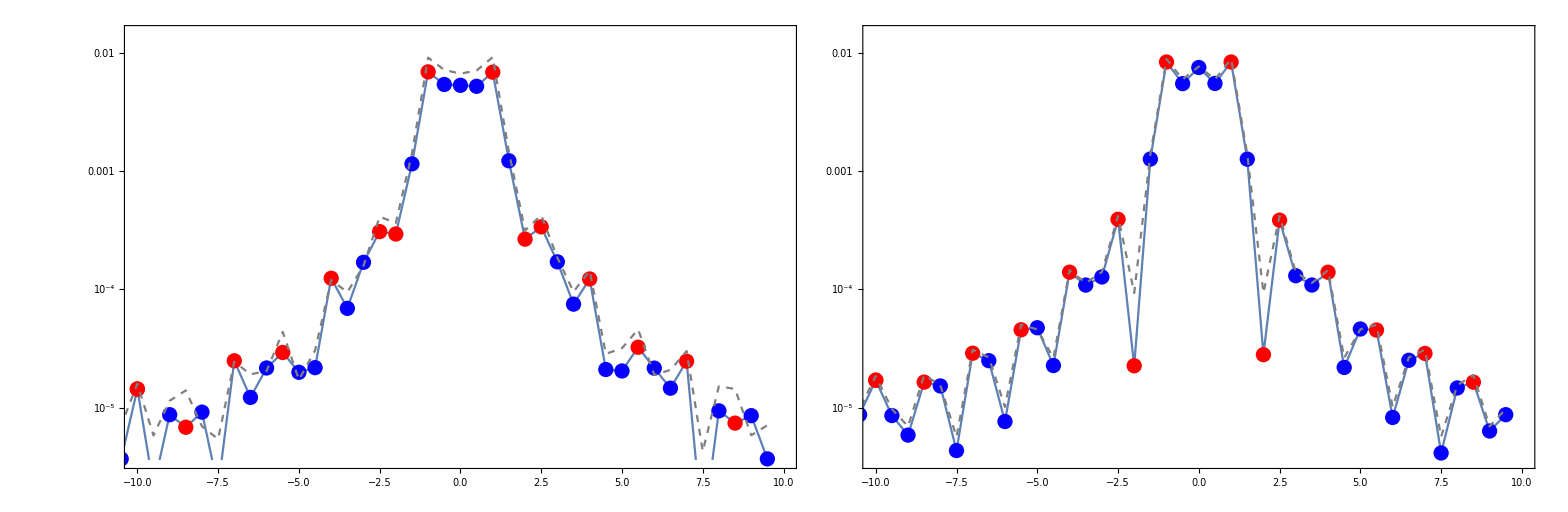

```mathematica
fig5=Show[
GraphicsRow[{  Show[{chPlotZZHc,chPlotZZ0},FrameLabel->{(MaTeX[#,Magnification->3.5]&)@"R_1 \\; ",None},(*ImageSize->1000,*)Frame->{{True,False},{True,True}}  
]   , Show[{chPlotZZHz,chPlotZZ0z},FrameLabel->(MaTeX[#,Magnification->3.5]&)/@{"R_1 \\; ", "\\vert \\, \\delta n_{l} \\,  \\vert"} ,(*ImageSize->1000,*)Frame->{{True,True},{True,True}}    ]        },-110,
Epilog-> {
Inset[MaTeX["\\mathrm{(a)}",Magnification->3],{126,-75},Scaled[{.5,.5}]     ],
Inset[MaTeX["\\mathrm{(b)}",Magnification->3],{1043,-75},Scaled[{.5,.5}]   ],
Inset[lattice,{1680,-180},Scaled[{.5,.5}],180   ],
Inset[legend,{80,-185},Scaled[{0,.5}],200   ]
}]
,ImageSize->2000]
```

```mathematica
Export["C:\\User\\lucas\\Desktop\\Wolfram Mathematica\\PhD-codes\\Figures_PhD\\New3\\fig5.pdf"  ,fig5  ];
```

#### c violation

```mathematica
sitesRotated[m_,n_,σ_]:={(m-n)/2,(3 (m+n)-2 σ)/(2 √3)};
```

```mathematica
Module[{χ,ω,ξ,jG,LG ,gauge="g4", Jv,Kv,Γv,J,K,Γ,L,Nc,h ,u0,H,T,u,t,t0,c11,c21,c12,c22,sNN,sNNN,δn,δn1,d,κ,p,l,tp,hp},
l=1;
p=1;tp=⌈p/Length@hV⌉;hp=Mod[p,Length@hV,1]; 		 
	{J,K,Γ,h}=parameters⟦1,p⟧[[1;;4]];L=Ls⟦l⟧; Nc=L^2;
	{jG,LG,χ,ω,ξ,EnG}=Chop@loadData[toPath[parameters[[1,p]],L,acuracy, gauge,NbName ]  ];
	cViolation=(    Flatten[Table[      Join[sitesRotated[m,n,σ],{1/3 Abs@Sum[Tr[ Transpose[ω[[σ,m+n L +1]] ].Mmat[[γ]]  ],{γ,1,3} ]} ]  , {m,0,L/2-1},{n,0,L/2-1},{σ,1,2}],2]    );
]
```

```mathematica
Print[  {min,max}=MinMax@Abs[  cViolation[[;;,3]]  ]  ];
cvStyled=Table[ Style[    cViolation[[t]][[1;;2]]    ,ColorData["TemperatureMap"][  (cViolation[[t,3]]-min)/(max-min) ]       ]     ,{t,1,Length@cViolation}];
```

{0.00337563,0.0050322}

```mathematica
cvStyled=Table[ Style[ cViolation[[t]][[1;;2]],{"●",ColorData["TemperatureMap"][  (cViolation[[t,3]]-min)/(max-min) ]  }]     ,{t,1,Length@cViolation}];
```

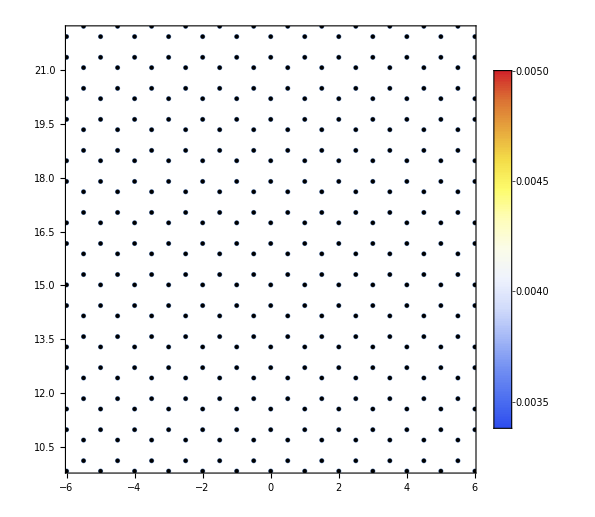

```mathematica
Legended[
ListPlot[  cvStyled,PlotRange->  {{-5.8,5.8},{10,22}},AspectRatio->{1,1}, ImageSize->500,
PlotLabel->MaTeX[" \\mathrm{tr}\\left( \\mathrm{W}^\\mathrm{T} \\mathrm{G}^{\\gamma}\\right)  
= \\left< \\mathrm{i} c^\\gamma_i \\mathrm{G}^{\\gamma} c^\\gamma_i \\right>  \\; , \\quad \\mathbf{h}=0.2 \\,  \\mathbf{c}, \\;  \\Gamma=0.2",Magnification->1.4]   , Frame->True, PlotLegends->Automatic , FrameStyle->Directive[Black,16], FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"x","y"}
],BarLegend[ {"TemperatureMap",{min,max}},None] ]
```

```mathematica
Export["C:\\User\\lucas\\Desktop\\Wolfram Mathematica\\PhD-codes\\Figures_PhD\\DeltaW_Real.pdf"  ,%   ];
```

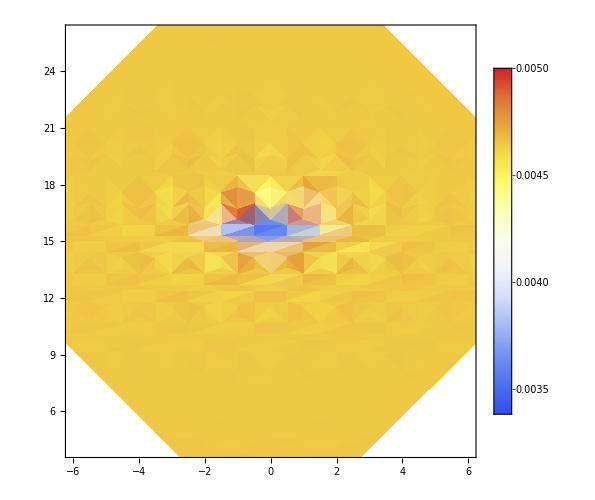

```mathematica
dp=ListDensityPlot[  cViolation   ,ImageSize->500,PlotRange->{{-6,6},{4,26},{0,1}},InterpolationOrder->1,PlotLabel->MaTeX[" \\mathrm{tr}\\left( \\mathrm{W}^\\mathrm{T} \\mathrm{G}^{\\gamma}\\right)  
= \\left< \\mathrm{i} c^\\gamma_i \\mathrm{G}^{\\gamma} c^\\gamma_i \\right>  \\; , \\quad \\mathbf{h}=0.2 \\,  \\mathbf{c}, \\;  \\Gamma=0.2",Magnification->1.4]   , Frame->True, PlotLegends->Automatic , FrameStyle->Directive[Black,16], FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"x","y"},
ColorFunction->"TemperatureMap",ColorFunctionScaling->True,ClippingStyle->Automatic  ]
```

```mathematica
Export["C:\\User\\lucas\\Desktop\\Wolfram Mathematica\\PhD-codes\\Fig3_Wp.pdf"  ,%   ];
```

## Fig 7*- Quadrupole projected [old]

```mathematica
θφQzz[charge_]:=Table[ {charge[[i,6]][[2]],charge[[i,6]][[3]],charge[[i,5]][[3,3]]  },{i,1,Length@charge}   ];θφQxxQyy[charge_]:=Table[ {charge[[i,6]][[2]],charge[[i,6]][[3]],charge[[i,5]][[1,1]] -charge[[i,5]][[2,2]]  },{i,1,Length@charge}   ];θφQxy[charge_]:=Table[ {charge[[i,6]][[2]],charge[[i,6]][[3]],charge[[i,5]][[1,2]] +charge[[i,5]][[2,1]]  },{i,1,Length@charge}   ];

anisotropy[Q_]:=√(Q⟦1,1⟧^2+4 Q⟦1,2⟧ Q⟦2,1⟧-2 Q⟦1,1⟧ Q⟦2,2⟧+Q⟦2,2⟧^2);    (*  2 Sqrt[ ((Qxx-Qyy)/2)^2+ QxyQyx   ] 00  *)
θφAni[charge_]:=Table[ {charge[[i,6]][[2]],charge[[i,6]][[3]],anisotropy@charge[[i,5]]  },{i,1,Length@charge}   ];
θφAni2[charge_]:=Table[ {charge[[i,6]][[2]],charge[[i,6]][[3]],1/Abs[charge[[i,5]][[3,3]]] anisotropy@charge[[i,5]]  },{i,1,Length@charge}   ];
```

```mathematica
NbName="709";
		Ls = Range[42,42,2]; 				tV={0};				
		hV=With[{h=0.2},Flatten[Table[{h,θ,φ},{φ,0.1,360.1,1},{θ,0.1,180.1,1}],1]        ]; 
		θV = Table[θ,{θ,0,180,1}];	

		φV1 = Table[φ,{φ,0,60,1}];	
		hV1 = With[{h=0.2},Flatten[Table[{h,θ,φ},{φ,φV1},{θ,θV}],1]        ]; 
		φV2 = Table[φ,{φ,64,120,1}];	
		hV2 = With[{h=0.2},Flatten[Table[{h,θ,φ},{φ,φV2},{θ,θV}],1]        ]; 
		φV3 = Table[φ,{φ,124,180,1}];	
		hV3 = With[{h=0.2},Flatten[Table[{h,θ,φ},{φ,φV3},{θ,θV}],1]        ]; 

		acuracy=9;
```

```mathematica
λpoints={{},{},{}} ;
κpoints={};
hV=Sort@With[{h=0.2},Flatten[Table[{h,θ,φ},{φ,0.1,360.1,1},{θ,0.1,180.1,1}],1]        ];

Do[ Module[{ h,hv }, 	
	hv=hV[[hp]];
	h=hv[[1]]  hAngle[hv[[2]],hv[[3]]] ;
AppendTo[κpoints,         {hv[[2]],hv[[3]],  toKappa[h]}  ];
AppendTo[λpoints[[1]],  {hv[[2]],hv[[3]],  toλ[h].ha  }  ];
AppendTo[λpoints[[2]],  {hv[[2]],hv[[3]],  toλ[h].hb  }  ];
AppendTo[λpoints[[3]],  {hv[[2]],hv[[3]],  toλ[h].hc  }  ];
(*nameComplement=StringReplace["t=X1_h=X2-ac=X4",{"X1"-> ToString[tV[[tp]]],"X2"-> ToString[hV[[hp]]], "X4"-> ToString[acuracy]  }];      *)
],{hp,1,Length@hV,2 }];
```

```mathematica
pmax=Length[  parameters[[1]]   ];Δp=1;   (*  chargeHex01={};*)
extCharge[ch_]:= Join[ch,(  {#[[1]],#[[2]],#[[3]],#[[4]],#[[5]],{#[[6,1]],180-#[[6,2]],180+#[[6,3]]}}    )&/@ch];
Module[{cH1,cH2,cH3,l,χ,ω,ξ,jG,LG,EnG ,gauge="g4",ev=1,p=1,L=Ls[[1]] },
ClearAll[chargeHex0,chargeHex00];
cH1=LoadquadrupolePure[parameters[[ev,p]],L,acuracy,gauge,{hV1[[1]],hV1[[-1]]}];
cH2=LoadquadrupolePure[parameters[[ev,p]],L,acuracy,gauge,{hV2[[1]],hV2[[-1]]}];
cH3=LoadquadrupolePure[parameters[[ev,p]],L,acuracy,gauge,{hV3[[1]],hV3[[-1]]}];
chargeHex0=Select[ Join[cH1,cH2,cH3],(#[[6,3]]>=0&&#[[6,3]]<=180)& ];
chargeHex00=extCharge[chargeHex0];
]
```

#### projective

```mathematica
projectSouthHemesphere[list0_]:=Module[{list}, list=Select[list0,(#[[1]]>=90∧#[[1]]<=180)& ];  Table[{(Cos[π list[[i,2]]/180]Sin[π list[[i,1]]/180])/(1-Cos[π list[[i,1]]/180]), (Sin[π list[[i,2]]/180]Sin[π list[[i,1]]/180])/(1-Cos[π list[[i,1]]/180]),list[[i,3]] },{i,1,Length@list}   ] ];
projecthHemesphereSquare[list0_]:=Select[ Module[{list}, list=Select[list0,(#[[1]]>=10)& ];  Table[{(Cos[π list[[i,2]]/180]Sin[π list[[i,1]]/180])/(1-Cos[π list[[i,1]]/180]), (Sin[π list[[i,2]]/180]Sin[π list[[i,1]]/180])/(1-Cos[π list[[i,1]]/180]),list[[i,3]] },{i,1,Length@list}   ] ], (Abs[#[[1]]]<=1&&Abs[#[[2]]]<=1)&  ];
```

```mathematica
projectAnyHemesphere[list0_,θ_,φ_]:=Module[{list}, 
list=Table[ { Mod[ list0[[i,1]]-θ, 180,1], Mod[ list0[[i,2]], 360,1],list0[[i,3]] },{i,1,Length@list0}   ];
list=Select[list,(#[[1]]>=90∧#[[1]]<=180)& ];  
Table[{(Cos[π list[[i,2]]/180]Sin[π list[[i,1]]/180])/(1-Cos[π list[[i,1]]/180]), (Sin[π list[[i,2]]/180]Sin[π list[[i,1]]/180])/(1-Cos[π list[[i,1]]/180]),list[[i,3]] },{i,1,Length@list}   ] 
];
```

```mathematica
(*N[(160^2 60)/2600^3 1/(1.92289705 10^(-6))]*)
```

```mathematica
projectAnyHemesphere[list0_,θ0_,φ0_,s_:1]:=Select[Module[{list,rot,θ=π θ0/180,φ=π φ0/180,Scale}, 
(*list=Table[ { Mod[ list0[[i,1]]-θ, 180,1], Mod[ list0[[i,2]], 360,1],list0[[i,3]] },{i,1,Length@list0}   ];*)
If[s!=1,Scale=N[(160^2 60)/3000^3 1/(1.92289705 10^(-6))]       ];
list=Select[list0,Abs[#[[1]]-θ]>1& ];  
rot=(*RotationMatrix[θ,{0,1,0}].*)RotationMatrix[-θ,{0,-1,0}].RotationMatrix[-φ,{0,0,1}];
Table[ Module[{xt,yt,zt},
{xt,yt,zt}=rot.{Cos[π list[[i,2]]/180]Sin[π list[[i,1]]/180],Sin[π list[[i,2]]/180]Sin[π list[[i,1]]/180],Cos[π list[[i,1]]/180]};
{xt/(1-zt), yt/(1-zt),1/Scale list[[i,3]] }],{i,1,Length@list}   ] 
], (Abs[#[[1]]]<=1&&Abs[#[[2]]]<=1)&  ];
```

```mathematica
(*projectAnyHemesphere[list0_,θ0_,φ0_,]:=Select[Module[{list,rot,θ=π θ0/180,φ=π φ0/180}, 
(*list=Table[ { Mod[ list0[[i,1]]-θ, 180,1], Mod[ list0[[i,2]], 360,1],list0[[i,3]] },{i,1,Length@list0}   ];*)
list=Select[list0,Abs[#[[1]]-θ]>1& ];  
rot=(*RotationMatrix[θ,{0,1,0}].*)RotationMatrix[-θ,{0,-1,0}].RotationMatrix[-φ,{0,0,1}];
Table[
Module[{xt,yt,zt},
{xt,yt,zt}=rot.{Cos[π list[[i,2]]/180]Sin[π list[[i,1]]/180],Sin[π list[[i,2]]/180]Sin[π list[[i,1]]/180],Cos[π list[[i,1]]/180]};
{xt/(1-zt), yt/(1-zt),list[[i,3]] }],{i,1,Length@list}   ] 
], (Abs[#[[1]]]<=1&&Abs[#[[2]]]<=1)&  ];*)
```

```mathematica
Module[{epilog={},title,plotsContour,plotsDensity,chargeList,listQ ,κp,λp,name,ΔL=1,rangeθ={-1,1},rangeφ={-1,1},imgs=800 },
epilog ={"\\Vert h \\Vert = 0.2"} ;
chargeList= chargeHex00;
listQ0={       θφQzz[chargeList ],θφQxxQyy[chargeList ],θφQxy[chargeList ](*,θφAni[chargeList ]  *),θφAni2[chargeList ]        };
listQ=listQ0 ;
list0=listQ0[[1]]; 
title="\\text{Quadrupole for pure Kitaev model } \\vec{h}=h \\big( \\mathbf{c} \\cos\\theta + \\mathbf{a} \\sin\\theta \\big)";
max1=N@(Ceiling[Max@Abs[  listQ0[[1]][[;;,3]]   ]  100]/100);
max4=N@(Ceiling[Max@Abs[  listQ0[[4]][[;;,3]]   ]  100]/100);
max2=Max@Abs[  Join[listQ0[[2]][[;;,3]] ,listQ0[[3]][[;;,3]]]];
max=N@(Ceiling[max2 100]/100);
contoursLevels=Flatten[Table[ max/8  x s,{x,1,10},{s,{-1,+1}}],1];
contoursLevels4=Flatten[Table[ max4/8  x s,{x,1,10},{s,{-1,+1}}],1];
δ=0.03;(*  Print[max1, "; "max2, "; "max, "; "δ];    Abort[];  *)
colors={{0,Red},{0.5-δ,White},{0.5+δ,White},{1,Blue}};


maxκ=N@(Ceiling[Max@Abs[  κpoints[[;;,3]]   ] 100]/100);

contoursLevelsκ=Flatten[Table[ maxκ/8  x s,{x,1,10},{s,{-1,+1}}],1];
maxλ1=Max@Abs[  λpoints[[1,;;,3]]   ];maxλ1=N@(Ceiling[maxλ1 100]/100);
contoursLevelsλ1=Flatten[Table[ maxλ1/8  x s,{x,1,10},{s,{-1,+1}}],1];

maxλ2=Max@Abs[  λpoints[[2,;;,3]]   ];maxλ2=N@(Ceiling[maxλ2 100]/100);
contoursLevelsλ2=Flatten[Table[ maxλ2/8  x s,{x,1,8},{s,{-1,+1}}],1];

 {θ,φ}={180- N[360  ArcTan[√(2+√3) ]/π ],0};
(* {θ,φ}={60,60}; {θ,φ}={180/π 2 ArcTan[1/(√2)],0};
Print[ListContourPlot[ projectAnyHemesphere[κpoints,θ,φ], ImageSize->imgs,PlotLegends->BarLegend[Automatic,9] ,ColorFunction->(Blend[colors,1/2+#/(2 maxκ)]&)  , ColorFunctionScaling->False,Contours->contoursLevelsκ, Frame->False,ImageSize->imgs,PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}}, PlotLabel->MaTeX["\\kappa",Magnification->1.4]  ] ];  Abort[];  {θ,φ}={60,120}; *)
Print[1];
Print@AbsoluteTiming[
listQ=projectAnyHemesphere[#,θ,φ]&/@listQ;
];
listq0=listQ;
Print@AbsoluteTiming[
κp=projectAnyHemesphere[#,θ,φ]&@κpoints;
];
Print@AbsoluteTiming[
λp=projectAnyHemesphere[#,θ,φ]&/@λpoints;
];
listQ0=listQ;
plotsContour={
ListContourPlot[ listQ[[1]], ImageSize->imgs,PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}},Frame->False, PlotLabel->MaTeX[" Q_{zz} ",Magnification->1.4]  , PlotLegends->BarLegend[Automatic,All] ,ColorFunction->(Blend[colors,0.15+# .8]&)  , (*Contours->contoursLevels,*) ColorFunctionScaling->True,Contours->9
],
ListContourPlot[ listQ[[2]], ImageSize->imgs,PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}},Frame->False, PlotLabel->MaTeX[" Q_{xx}-Q_{yy} ",Magnification->1.4]   , PlotLegends->BarLegend[Automatic,All] ,ColorFunction->(Blend[colors,1/2+#/(2 max2)]&)  , ColorFunctionScaling->False,Contours->contoursLevels]   ,
ListContourPlot[ listQ[[3]], ImageSize->imgs,PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}},FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{"\\theta \\; ","\\varphi"},  PlotLabel->MaTeX[" Q_{xy} ",Magnification->1.4]       (*,PlotLegends->Placed[MaTeX[epilog,Magnification->1.5] ,{Scaled[{0.02,.97}],{0,1} } ]*), PlotLegends->BarLegend[Automatic,All] ,ColorFunction->(Blend[colors,1/2+#/(2 max2)]&)  ,Frame->False,  ColorFunctionScaling->False,Contours->contoursLevels],
ListContourPlot[ listQ[[4]], ImageSize->imgs,PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}},Frame->False, PlotLabel->MaTeX[" Q_{xx}^\\prime-Q_{yy}^\\prime ",Magnification->1.4]  , PlotLegends->Automatic , ColorFunction->(Blend[colors,1/2+#/(2 max4)]&)  , ColorFunctionScaling->False,Contours->contoursLevels4]    ,
ListContourPlot[κp,PlotLegends->BarLegend[Automatic,9] ,ColorFunction->(Blend[colors,1/2+#/(2 maxκ)]&)  , ColorFunctionScaling->False,Contours->contoursLevelsκ, Frame->False,ImageSize->imgs,PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}}, PlotLabel->MaTeX["\\kappa",Magnification->1.4] ],
ListContourPlot[λp[[1]], PlotLegends->BarLegend[Automatic,9] ,ColorFunction->(Blend[colors,1/2+#/(2 maxλ1)]&) , ColorFunctionScaling->False,Contours->contoursLevelsλ1, Frame->False,ImageSize->imgs,PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}}, PlotLabel->MaTeX["\\lambda \\cdot \\mathbf{a} ",Magnification->1.4]  ] ,
ListContourPlot[λp[[2]],  PlotLegends->BarLegend[Automatic,9] ,ColorFunction->(Blend[colors,1/2+#/(2 maxλ2)]&)  , ColorFunctionScaling->False,Contours->contoursLevelsλ2, Frame->False,ImageSize->imgs,PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}},PlotLabel->MaTeX["\\lambda \\cdot \\mathbf{b} ",Magnification->1.4]]
};
name="h=.2_L=42_square_minima"; Print[name];
plotsContour0=plotsContour;
(*  Print[plotsContour ];                   *)(*
Export[ FileNameJoin[{ NotebookDirectory[], StringReplace["\\Figures\\pure\\QUADRUPOLE_th_ph\\Qzz_XX_pure.pdf","XX"->name]  }],      plotsContour[[1]]        ];
Export[ FileNameJoin[{ NotebookDirectory[], StringReplace["\\Figures\\pure\\QUADRUPOLE_th_ph\\QxxQyy_XX_pure.pdf","XX"->name]  }],plotsContour[[2]]           ];
Export[ FileNameJoin[{ NotebookDirectory[], StringReplace["\\Figures\\pure\\QUADRUPOLE_th_ph\\Qxy_XX_pure.pdf","XX"-> name]  }],      plotsContour[[3]]       ];
Export[ FileNameJoin[{ NotebookDirectory[], StringReplace["\\Figures\\pure\\QUADRUPOLE_th_ph\\Qani_XX_pure.pdf","XX"-> name]  }],    plotsContour[[4]]        ];
Export[ FileNameJoin[{ NotebookDirectory[], StringReplace["\\Figures\\pure\\QUADRUPOLE_th_ph\\Qani2_XX_pure.pdf","XX"-> name]  }],    plotsContour[[5]]       ];
Export[ FileNameJoin[{ NotebookDirectory[], StringReplace["\\Figures\\pure\\QUADRUPOLE_th_ph\\Qani2_Theta_XX_pure.pdf","XX"-> name]  }],    plots[[5]]      ];
Export[ FileNameJoin[{ NotebookDirectory[], StringReplace["\\Figures\\pure\\QUADRUPOLE_th_ph\\kappa_XX_pure.pdf","XX"-> name]  }],      plotsContour[[5]]     ];
Export[ FileNameJoin[{ NotebookDirectory[], StringReplace["\\Figures\\pure\\QUADRUPOLE_th_ph\\lambdaA_XX_pure.pdf","XX"-> name]  }],      plotsContour[[6]]   ];
Export[ FileNameJoin[{ NotebookDirectory[], StringReplace["\\Figures\\pure\\QUADRUPOLE_th_ph\\lambdaB_XX_pure.pdf","XX"-> name]  }],    plotsContour[[7]]     ];   *)
 ]
```

```mathematica
N[360  ArcTan[√(2+√3) ]/π ]-60
```

```mathematica
N[  180/π 2 ArcTan[1/(√2)]  ]
```

```mathematica
ListContourPlot[ listQ0[[1]], ImageSize->600,PlotRange->{{-.97,.97},{-.97,.97}},Frame->False, PlotLabel->MaTeX[" Q_{zz} ",Magnification->1.4]  , PlotLegends->BarLegend[Automatic,All] ,ColorFunction->(Blend[colors,0.15+# .8]&)  , (*Contours->contoursLevels,*) ColorFunctionScaling->True,Contours->8 ]
```

#### texture to sphere plot

```mathematica
θφQzz[charge_]:=Table[ {π/180 charge[[i,6]][[2]],π/180 charge[[i,6]][[3]],charge[[i,5]][[3,3]]  },{i,1,Length@charge}   ];θφQxxQyy[charge_]:=Table[ {π/180 charge[[i,6]][[2]],π/180 charge[[i,6]][[3]],charge[[i,5]][[1,1]] -charge[[i,5]][[2,2]]  },{i,1,Length@charge}   ];θφQxy[charge_]:=Table[ {π/180 charge[[i,6]][[2]],π/180 charge[[i,6]][[3]],charge[[i,5]][[1,2]] +charge[[i,5]][[2,1]]  },{i,1,Length@charge}   ];

anisotropy[Q_]:=√(Q⟦1,1⟧^2+4 Q⟦1,2⟧ Q⟦2,1⟧-2 Q⟦1,1⟧ Q⟦2,2⟧+Q⟦2,2⟧^2);    (*  2 Sqrt[ ((Qxx-Qyy)/2)^2+ QxyQyx   ] 00  *)
θφAni[charge_]:=Table[ {π/180 charge[[i,6]][[2]],π/180 charge[[i,6]][[3]],anisotropy@charge[[i,5]]  },{i,1,Length@charge}   ];
θφAni2[charge_]:=Table[ {π/180 charge[[i,6]][[2]],π/180 charge[[i,6]][[3]],1/Abs[charge[[i,5]][[3,3]]] anisotropy@charge[[i,5]]  },{i,1,Length@charge}   ]; 

toPi[list_]:=Table[ {π/180 list[[i,1]],π/180 list[[i,2]],list[[i,3]]  },{i,1,Length@list}   ];
```

```mathematica
Module[{epilog={},title,plotsContour,plotsDensity,chargeList,listQ ,κp,λp,name,ΔL=1,rangeθ={-1,1},rangeφ={-1,1},imgs=1000 },
epilog ={"\\Vert h \\Vert = 0.2"} ;
chargeList= chargeHex00;
listQ0={       θφQzz[chargeList ],θφQxxQyy[chargeList ],θφQxy[chargeList ](*,θφAni[chargeList ]  *),θφAni2[chargeList ]        };
listQ=listQ0 ;
list0=listQ0[[1]]; 
title="\\text{Quadrupole for pure Kitaev model } \\vec{h}=h \\big( \\mathbf{c} \\cos\\theta + \\mathbf{a} \\sin\\theta \\big)";
max1=N@(Ceiling[Max@Abs[  listQ0[[1]][[;;,3]]   ]  100]/100);
max4=N@(Ceiling[Max@Abs[  listQ0[[4]][[;;,3]]   ]  100]/100);
max2=Max@Abs[  Join[listQ0[[2]][[;;,3]] ,listQ0[[3]][[;;,3]]]];
max=N@(Ceiling[max2 100]/100);
contoursLevels=Flatten[Table[ max/8  x s,{x,1,10},{s,{-1,+1}}],1];
contoursLevels4=Flatten[Table[ max4/8  x s,{x,1,10},{s,{-1,+1}}],1];
δ=0.03;(*
Print[max1, "; "max2, "; "max, "; "δ];
Abort[];*)
colors={{0,Red},{0.5-δ,White},{0.5+δ,White},{1,Blue}};
maxκ=N@(Ceiling[Max@Abs[  κpoints[[;;,3]]   ] 100]/100);

contoursLevelsκ=Flatten[Table[ maxκ/8  x s,{x,1,10},{s,{-1,+1}}],1];
maxλ1=Max@Abs[  λpoints[[1,;;,3]]   ];maxλ1=N@(Ceiling[maxλ1 100]/100);
contoursLevelsλ1=Flatten[Table[ maxλ1/8  x s,{x,1,10},{s,{-1,+1}}],1];

maxλ2=Max@Abs[  λpoints[[2,;;,3]]   ];maxλ2=N@(Ceiling[maxλ2 100]/100);
contoursLevelsλ2=Flatten[Table[ maxλ2/8  x s,{x,1,8},{s,{-1,+1}}],1];

 {θ,φ}={180- N[360  ArcTan[√(2+√3) ]/π ],0}; 
rangeθ={0,π};
rangeφ={0,2π};
κp=toPi@κpoints;
λp=toPi/@λpoints;

plotsContour={
ListContourPlot[ listQ[[1]], ImageSize->imgs,PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}},Frame->False, PlotRangePadding->None ,ColorFunction->(Blend[colors,0.15+# .8]&)   , PlotLegends->BarLegend[Automatic,All],(* Contours->contoursLevels,*) ColorFunctionScaling->True,Contours->9
],
ListContourPlot[ listQ[[2]], ImageSize->imgs,PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}},Frame->False,  PlotRangePadding->None    , PlotLegends->BarLegend[Automatic,All], ColorFunction->(Blend[colors,1/2+#/(2 max2)]&)  , ColorFunctionScaling->False,Contours->contoursLevels]   ,
ListContourPlot[ listQ[[3]], ImageSize->imgs,PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}},   PlotRangePadding->None, PlotLegends->BarLegend[Automatic,All] ,ColorFunction->(Blend[colors,1/2+#/(2 max2)]&)  ,Frame->False,  ColorFunctionScaling->False,Contours->contoursLevels],
ListContourPlot[ listQ[[4]], ImageSize->imgs,PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}},Frame->False,  PlotRangePadding->None   , PlotLegends->Automatic , ColorFunction->(Blend[colors,1/2+#/(2 max4)]&)  , ColorFunctionScaling->False,Contours->contoursLevels4]    ,
ListContourPlot[κp,PlotLegends->BarLegend[Automatic,9] ,ColorFunction->(Blend[colors,1/2+#/(2 maxκ)]&)  , ColorFunctionScaling->False,Contours->contoursLevelsκ, Frame->False,ImageSize->imgs,PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}}, PlotRangePadding->None ],
ListContourPlot[λp[[1]], PlotLegends->BarLegend[Automatic,9] ,ColorFunction->(Blend[colors,1/2+#/(2 maxλ1)]&) , ColorFunctionScaling->False,Contours->contoursLevelsλ1, Frame->False,ImageSize->imgs,PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}},  PlotRangePadding->None ] ,
ListContourPlot[λp[[2]],  PlotLegends->BarLegend[Automatic,9] ,ColorFunction->(Blend[colors,1/2+#/(2 maxλ2)]&)  , ColorFunctionScaling->False,Contours->contoursLevelsλ2, Frame->False,ImageSize->imgs,PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}}, PlotRangePadding->None ]
};
name="h=.2_L=42_sphere"; Print[name];
plotsContour0=plotsContour;

(*Print[plotsContour ];
*)

lightining=With[{v=2,gl=0.1},
{
{"Ambient",GrayLevel[0.92]},
{"Directional",GrayLevel[gl/3],ImageScaled[{v,0,v}]},
{"Directional",GrayLevel[√(3/2)gl/3],ImageScaled[{v,v,v}]},
{"Directional",GrayLevel[gl/3],ImageScaled[{0,v,v}]}}
];


plotsSphere=SphericalPlot3D[1,{u,0,π},{v,0,2π}, ImageSize->(imgs), (* PlotLabel->MaTeX[" Q_{zz} ",Magnification->1.4]  ,*) PlotLegends-># [[2]] ,
PlotStyle->Directive[Texture[# [[1]]  ]  ], Lighting->lightining,  
(*AxesLabel->{x,y,z},*) Boxed->False, Axes->False, Mesh->None, MeshStyle->Opacity[0.1], PlotPoints->100, MaxRecursion->2,ViewPoint->{0,0,Infinity}
]&/@plotsContour;

(*
{
ListContourPlot[ listQ[[1]], ImageSize->imgs,PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}},Frame->False, PlotLabel->MaTeX[" Q_{zz} ",Magnification->1.4]  , PlotLegends->BarLegend[Automatic,All] ,ColorFunction->(Blend[colors,0.15+# .8]&)  , (*Contours->contoursLevels,*) ColorFunctionScaling->True,Contours->9
],
ListContourPlot[ listQ[[2]], ImageSize->imgs,PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}},Frame->False, PlotLabel->MaTeX[" Q_{xx}-Q_{yy} ",Magnification->1.4]   , PlotLegends->BarLegend[Automatic,All] ,ColorFunction->(Blend[colors,1/2+#/(2 max2)]&)  , ColorFunctionScaling->False,Contours->contoursLevels]   ,
ListContourPlot[ listQ[[3]], ImageSize->imgs,PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}},FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{"\\theta \\; ","\\varphi"},  PlotLabel->MaTeX[" Q_{xy} ",Magnification->1.4]       (*,PlotLegends->Placed[MaTeX[epilog,Magnification->1.5] ,{Scaled[{0.02,.97}],{0,1} } ]*), PlotLegends->BarLegend[Automatic,All] ,ColorFunction->(Blend[colors,1/2+#/(2 max2)]&)  ,Frame->False,  ColorFunctionScaling->False,Contours->contoursLevels],
ListContourPlot[ listQ[[4]], ImageSize->imgs,PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}},Frame->False, PlotLabel->MaTeX[" Q_{xx}^\\prime-Q_{yy}^\\prime ",Magnification->1.4]  , PlotLegends->Automatic , ColorFunction->(Blend[colors,1/2+#/(2 max4)]&)  , ColorFunctionScaling->False,Contours->contoursLevels4]    ,
ListContourPlot[κp,PlotLegends->BarLegend[Automatic,9] ,ColorFunction->(Blend[colors,1/2+#/(2 maxκ)]&)  , ColorFunctionScaling->False,Contours->contoursLevelsκ, Frame->False,ImageSize->imgs,PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}}, PlotLabel->MaTeX["\\kappa",Magnification->1.4] ],
ListContourPlot[λp[[1]], PlotLegends->BarLegend[Automatic,9] ,ColorFunction->(Blend[colors,1/2+#/(2 maxλ1)]&) , ColorFunctionScaling->False,Contours->contoursLevelsλ1, Frame->False,ImageSize->imgs,PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}}, PlotLabel->MaTeX["\\lambda \\cdot \\mathbf{a} ",Magnification->1.4]  ] ,
ListContourPlot[λp[[2]],  PlotLegends->BarLegend[Automatic,9] ,ColorFunction->(Blend[colors,1/2+#/(2 maxλ2)]&)  , ColorFunctionScaling->False,Contours->contoursLevelsλ2, Frame->False,ImageSize->imgs,PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}},PlotLabel->MaTeX["\\lambda \\cdot \\mathbf{b} ",Magnification->1.4]]
};
*)
 

 ]
```

```mathematica
plotsSphere[[1]]
```

```mathematica
name="h=.2_L=42_sphere";
Export[ FileNameJoin[{ NotebookDirectory[], StringReplace["\\Figures\\pure\\QUADRUPOLE_sp\\Qzz_XX_pure.pdf","XX"->name]  }],      plotsSphere[[1]]      ];
Export[ FileNameJoin[{ NotebookDirectory[], StringReplace["\\Figures\\pure\\QUADRUPOLE_sp\\QxxQyy_XX_pure.pdf","XX"->name]  }],plotsSphere[[2]]      ];
Export[ FileNameJoin[{ NotebookDirectory[], StringReplace["\\Figures\\pure\\QUADRUPOLE_sp\\Qxy_XX_pure.pdf","XX"-> name]  }],      plotsSphere[[3]]      ];
Export[ FileNameJoin[{ NotebookDirectory[], StringReplace["\\Figures\\pure\\QUADRUPOLE_sp\\Qani_XX_pure.pdf","XX"-> name]  }],    plotsSphere[[4]]      ];
Export[ FileNameJoin[{ NotebookDirectory[], StringReplace["\\Figures\\pure\\QUADRUPOLE_sp\\Qani2_XX_pure.pdf","XX"-> name]  }],    plotsSphere[[5]]      ];
(*Export[ FileNameJoin[{ NotebookDirectory[], StringReplace["\\Figures\\pure\\QUADRUPOLE_sp\\Qani2_Theta_XX_pure.pdf","XX"-> name]  }],    plots[[5]]      ];*)
Export[ FileNameJoin[{ NotebookDirectory[], StringReplace["\\Figures\\pure\\QUADRUPOLE_sp\\kappa_XX_pure.pdf","XX"-> name]  }],      plotsSphere[[5]]      ];
Export[ FileNameJoin[{ NotebookDirectory[], StringReplace["\\Figures\\pure\\QUADRUPOLE_sp\\lambdaA_XX_pure.pdf","XX"-> name]  }],      plotsSphere[[6]]      ];
Export[ FileNameJoin[{ NotebookDirectory[], StringReplace["\\Figures\\pure\\QUADRUPOLE_sp\\lambdaB_XX_pure.pdf","XX"-> name]  }],    plotsSphere[[7]]      ];
```

```mathematica
{RGBColor[{.35,.35,.35}],RGBColor[{.37,.37,.37}],Hue[0.5,0,0.9]}
```

```mathematica
lightining=With[{v=2,gl=0.1},
{
{"Ambient",GrayLevel[0.92]},
{"Directional",GrayLevel[gl/3],ImageScaled[{v,0,v}]},
{"Directional",GrayLevel[√(3/2)gl/3],ImageScaled[{v,v,v}]},
{"Directional",GrayLevel[gl/3],ImageScaled[{0,v,v}]}}
];
Show[ 
SphericalPlot3D[1,{u,0,π},{v,0,2π}, ImageSize->(1000),PlotStyle->Directive[Texture[plotsContour0[[2,1]]  ]  ], Lighting->lightining,  
 Boxed->False, Axes->False, Mesh->None, MeshStyle->Opacity[0.1], PlotPoints->100, MaxRecursion->2,ViewPoint->{0,0,Infinity},PlotRange->Full  ],
Graphics3D[ {Black,Arrowheads[0.03],Arrow[Tube[{ {0,0,0},{0,0,1.2}}]  ] , Thickness[0.01]       }   ],PlotRange->Full
]
```

```mathematica
(*SphericalPlot3D[1,{u,0,π},{v,0,2π}, ImageSize->500,  PlotLabel->MaTeX[" Q_{zz} ",Magnification->1.4]  , PlotLegends->BarLegend[Automatic,All] ,PlotStyle->Directive[Texture[plotsContour0[[1,1]]  ]], Lighting->"Neutral", RotationAction->"Clip", 
(*AxesLabel->{x,y,z},*) Boxed->False, Axes->False, Mesh->None, MeshStyle->Opacity[0.1], PlotPoints->100, MaxRecursion->2,ViewPoint->{0,0,2.2}
]*)
```

## Fig 7 - Quadrupole sphere

```mathematica
(*Eigenvalues@{{q11,q12},{q12,q22}}
Simplify[  1/2 (q11+q22-√(q11^2+4 q12^2-2 q11 q22+q22^2))-1/2 (q11+q22+√(q11^2+4 q12^2-2 q11 q22+q22^2))  ]*)
```

```mathematica
θφQzz[charge_]:=Table[ {charge[[i,6]][[2]],charge[[i,6]][[3]],charge[[i,5]][[3,3]]  },{i,1,Length@charge}   ];θφQxxQyy[charge_]:=Table[ {charge[[i,6]][[2]],charge[[i,6]][[3]],charge[[i,5]][[1,1]] -charge[[i,5]][[2,2]]  },{i,1,Length@charge}   ];θφQxy[charge_]:=Table[ {charge[[i,6]][[2]],charge[[i,6]][[3]],charge[[i,5]][[1,2]] +charge[[i,5]][[2,1]]  },{i,1,Length@charge}   ];

anisotropy[Q_]:=√(Q⟦1,1⟧^2+4 Q⟦1,2⟧ Q⟦2,1⟧-2 Q⟦1,1⟧ Q⟦2,2⟧+Q⟦2,2⟧^2);    (*  2 Sqrt[ ((Qxx-Qyy)/2)^2+ QxyQyx   ] 00  *)
ΔoverQ[Q_]:=1/(Q[[1,1]]+Q[[2,2]])√((Q[[1,1]]-Q[[2,2]])^2 +(2 Q⟦1,2⟧   )^2);
θφAni[charge_]:=Table[ {charge[[i,6]][[2]],charge[[i,6]][[3]],anisotropy@charge[[i,5]]  },{i,1,Length@charge}   ];
θφAni2[charge_]:=Table[ {charge[[i,6]][[2]],charge[[i,6]][[3]],1/Abs[charge[[i,5]][[3,3]]] anisotropy@charge[[i,5]]  },{i,1,Length@charge}   ]; 

NbName="709"; ρ=-1.92289705 10^(-6);
		Ls = Range[42,42,2]; 				tV={0};				
		hV=With[{h=0.2},Flatten[Table[{h,θ,φ},{φ,0.1,360.1,1},{θ,0.1,180.1,1}],1]        ]; 
		θV = Table[θ,{θ,0,180,1}];	

		φV1 = Table[φ,{φ,0,60,1}];	
		hV1 = With[{h=0.2},Flatten[Table[{h,θ,φ},{φ,φV1},{θ,θV}],1]        ]; 
		φV2 = Table[φ,{φ,64,120,1}];	
		hV2 = With[{h=0.2},Flatten[Table[{h,θ,φ},{φ,φV2},{θ,θV}],1]        ]; 
		φV3 = Table[φ,{φ,124,180,1}];	
		hV3 = With[{h=0.2},Flatten[Table[{h,θ,φ},{φ,φV3},{θ,θV}],1]        ]; 

		acuracy=9;

λpoints={{},{},{}} ;
κpoints={};
hV=Sort@With[{h=0.2},Flatten[Table[{h,θ,φ},{φ,0.1,360.1,1},{θ,0.1,180.1,1}],1]        ];

Do[ Module[{ h,hv }, 	
	hv=hV[[hp]];
	h=hv[[1]]  hAngle[hv[[2]],hv[[3]]] ;
AppendTo[κpoints,         {hv[[2]],hv[[3]],  toKappa[h]}  ];
AppendTo[λpoints[[1]],  {hv[[2]],hv[[3]],  toλ[h].ha  }  ];
AppendTo[λpoints[[2]],  {hv[[2]],hv[[3]],  toλ[h].hb  }  ];
AppendTo[λpoints[[3]],  {hv[[2]],hv[[3]],  toλ[h].hc  }  ];
(*nameComplement=StringReplace["t=X1_h=X2-ac=X4",{"X1"-> ToString[tV[[tp]]],"X2"-> ToString[hV[[hp]]], "X4"-> ToString[acuracy]  }];      *)
],{hp,1,Length@hV,4 }];
pmax=Length[  parameters[[1]]   ];Δp=1;   (*  chargeHex01={};*)
extCharge[ch_]:= Join[ch,(  {#[[1]],#[[2]],#[[3]],#[[4]],#[[5]],{#[[6,1]],180-#[[6,2]],180+#[[6,3]]}}    )&/@ch];
Module[{cH1,cH2,cH3,l,χ,ω,ξ,jG,LG,EnG ,gauge="g4",ev=1,p=1,L=Ls[[1]]  ,parameters},
parameters={{  {0.,-1.,0.,{0.005773502691896259,0.005773502691896259,0.005773502691896259},0.,-0.9999999999999999,0.,{0.01,0,0},0,0.} }};
ClearAll[chargeHex0,chargeHex00];
cH1=LoadquadrupolePure[parameters[[ev,p]],L,acuracy,gauge,{hV1[[1]],hV1[[-1]]}];
cH2=LoadquadrupolePure[parameters[[ev,p]],L,acuracy,gauge,{hV2[[1]],hV2[[-1]]}];
cH3=LoadquadrupolePure[parameters[[ev,p]],L,acuracy,gauge,{hV3[[1]],hV3[[-1]]}];
chargeHex0=Select[ Join[cH1,cH2,cH3],(#[[6,3]]>=0&&#[[6,3]]<=180)& ];
chargeHex00=extCharge[chargeHex0];
]
θφQzz[charge_]:=Table[ {π/180 charge[[i,6]][[2]],π/180 charge[[i,6]][[3]],charge[[i,5]][[3,3]]  },{i,1,Length@charge}   ];θφQxxQyy[charge_]:=Table[ {π/180 charge[[i,6]][[2]],π/180 charge[[i,6]][[3]],charge[[i,5]][[1,1]] -charge[[i,5]][[2,2]]  },{i,1,Length@charge}   ];θφQxy[charge_]:=Table[ {π/180 charge[[i,6]][[2]],π/180 charge[[i,6]][[3]],charge[[i,5]][[1,2]] +charge[[i,5]][[2,1]]  },{i,1,Length@charge}   ];

anisotropy[Q_]:=√(Q⟦1,1⟧^2+4 Q⟦1,2⟧ Q⟦2,1⟧-2 Q⟦1,1⟧ Q⟦2,2⟧+Q⟦2,2⟧^2);    (*  2 Sqrt[ ((Qxx-Qyy)/2)^2+ QxyQyx   ] 00  *)
θφAni[charge_]:=Table[ {π/180 charge[[i,6]][[2]],π/180 charge[[i,6]][[3]],anisotropy@charge[[i,5]]  },{i,1,Length@charge}   ];
θφAni2[charge_]:=Table[ {π/180 charge[[i,6]][[2]],π/180 charge[[i,6]][[3]],1/Abs[charge[[i,5]][[3,3]]] anisotropy@charge[[i,5]]  },{i,1,Length@charge}   ]; 
θφΔQ[charge_]:=Table[ {π/180 charge[[i,6]][[2]],π/180 charge[[i,6]][[3]],ΔoverQ@charge[[i,5]]  },{i,1,Length@charge}   ]; 

toPi[list_]:=Table[ {π/180 list[[i,1]],π/180 list[[i,2]],list[[i,3]]  },{i,1,Length@list}   ]; 
 
listQρ={       θφQzz[chargeHex00 ],θφQxxQyy[chargeHex00 ]        };
listQ =Table[{#[[1]],#[[2]],Abs[ρ/ttU] #[[3]]}&/@listQρ[[j]],{j,1,Length@listQρ}];
```

```mathematica
(*ReverseSortBy[ listQ[[2]], Last] [[1]]
{{0.2,0.0051068788119796}}
{{0.2,0.0346723596216593}}
Select[listQ[[1]], (#[[1]]==(25 π)/36&&#[[2]]==2 π)&] *)
```

```mathematica
{{0,Hue[347/360,.27,1]     },
{0.5,White},
{1,Hue[197/360,.63,1]  }}
```

{{0,Hue[Rational[347, 360], 0.27, 1]},{0.5,GrayLevel[1]},{1,Hue[Rational[197, 360], 0.63, 1]}}

#### texture

```mathematica
Module[{epilog={},title,chargeList,listQ ,κp,λp,name,ΔL=1,listQρ, rangeθ={-1,1},rangeφ={-1,1},imgs=3000 },
epilog ={"\\Vert h \\Vert = 0.2"} ;
chargeList= chargeHex00;
listQρ={       θφQzz[chargeList ],θφQxxQyy[chargeList ],θφQxy[chargeList ](*,θφAni[chargeList ]  *),θφΔQ[chargeList ]        };
listQ =Table[{#[[1]],#[[2]],Abs[ρ/ttU] #[[3]]}&/@listQρ[[j]],{j,1,Length@listQρ}];
listQ0=listQ ;
title="\\text{Quadrupole for pure Kitaev model } \\vec{h}=h \\big( \\mathbf{c} \\cos\\theta + \\mathbf{a} \\sin\\theta \\big)";
max1=N@(Ceiling[Max@Abs[  listQ[[1]][[;;,3]]   ]  1000]/1000);
max4=N@(Ceiling[Max@Abs[  listQ[[4]][[;;,3]]   ]  1000]/1000);
max2=Max@Abs[  Join[  listQ[[2]][[;;,3]] ,listQ[[3]][[;;,3]] (*,listQ[[4]][[;;,3]] *)   ]];
max=N@(Ceiling[max2 1000]/1000);
(*contoursLevels=Flatten[Table[ max/8  x s,{x,1,10},{s,{-1,+1}}],1];*)
contoursLevels=Flatten[Table[ max2/5  x s,{x,1,5},{s,{-1,+1}}],1];
contoursLevels=round[#,1000]&/@(Sort@contoursLevels);

contoursLevels4=Flatten[Table[ max4/8  x s,{x,1,10},{s,{-1,+1}}],1];
δ=0.03;(*
Print[max1, "; "max2, "; "max, "; "δ];
Abort[];*)
colors={{0,Red},{0.5-δ,White},{0.5+δ,White},{1,Blue}};
colors2={{0,Hue[347/360,.4,1]     },
{0.5,White},
{1,Hue[197/360,.7,1]  }};

(*
maxκ=N@Ceiling[Max@Abs[  κpoints[[;;,3]]   ] 100]/100;
contoursLevelsκ=Flatten[Table[ maxκ/8  x s,{x,1,10},{s,{-1,+1}}],1];
maxλ1=Max@Abs[  λpoints[[1,;;,3]]   ];maxλ1=N@Ceiling[maxλ1 100]/100;
contoursLevelsλ1=Flatten[Table[ maxλ1/8  x s,{x,1,10},{s,{-1,+1}}],1];

maxλ2=Max@Abs[  λpoints[[2,;;,3]]   ];maxλ2=N@Ceiling[maxλ2 100]/100;
contoursLevelsλ2=Flatten[Table[ maxλ2/8  x s,{x,1,8},{s,{-1,+1}}],1];*)
 {θ,φ}={180- N[360  ArcTan[√(2+√3) ]/π ],0}; rangeθ={0,π};rangeφ={0,2π};
(*κp=toPi@κpoints;λp=toPi/@λpoints;*)
{minQzz,maxQzz}=MinMax[  listQ[[1]][[;;,3]] ] ;

plotsContour={
ListContourPlot[ listQ[[1]], ImageSize->imgs,PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}},Frame->False, PlotRangePadding->None ,ColorFunction-> (Blend[colors2,(#-minQzz)/(maxQzz-minQzz)]&)   , PlotLegends->BarLegend[Automatic,All],(* Contours->contoursLevels,*) ColorFunctionScaling->False,Contours->9
],
ListContourPlot[ listQ[[2]], ImageSize->imgs,PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}},Frame->False,  PlotRangePadding->None    , PlotLegends->BarLegend[Automatic,All], ColorFunction->(Blend[colors,1/2+#/(2 max2)]&)  , ColorFunctionScaling->False,Contours->contoursLevels]   ,
ListContourPlot[ listQ[[3]], ImageSize->imgs,PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}},   PlotRangePadding->None, PlotLegends->BarLegend[Automatic,All] ,ColorFunction->(Blend[colors,1/2+#/(2 max2)]&)  ,Frame->False,  ColorFunctionScaling->False,Contours->contoursLevels],
ListContourPlot[ listQ[[4]], ImageSize->imgs,PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}},Frame->False,  PlotRangePadding->None   , PlotLegends->Automatic , ColorFunction->(Blend[colors,1/2+#/(2 max4)]&)  , ColorFunctionScaling->False,Contours->9]    (*,
ListContourPlot[κp,PlotLegends->BarLegend[Automatic,9] ,ColorFunction->(Blend[colors,1/2+#/(2 maxκ)]&)  , ColorFunctionScaling->False,Contours->contoursLevelsκ, Frame->False,ImageSize->imgs,PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}}, PlotRangePadding->None ],
ListContourPlot[λp[[1]], PlotLegends->BarLegend[Automatic,9] ,ColorFunction->(Blend[colors,1/2+#/(2 maxλ1)]&) , ColorFunctionScaling->False,Contours->contoursLevelsλ1, Frame->False,ImageSize->imgs,PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}},  PlotRangePadding->None ] ,
ListContourPlot[λp[[2]],  PlotLegends->BarLegend[Automatic,9] ,ColorFunction->(Blend[colors,1/2+#/(2 maxλ2)]&)  , ColorFunctionScaling->False,Contours->contoursLevelsλ2, Frame->False,ImageSize->imgs,PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}}, PlotRangePadding->None ]*)
};
name="h=.2_L=42_sphere"; Print[name];
plotsContour0=plotsContour;
(*Print[plotsContour ];*)
lightining=With[{v=2,gl=0.1},
{
{"Ambient",GrayLevel[0.92]},
{"Directional",GrayLevel[gl/3],ImageScaled[{v,0,v}]},
{"Directional",GrayLevel[√(3/2)gl/3],ImageScaled[{v,v,v}]},
{"Directional",GrayLevel[gl/3],ImageScaled[{0,v,v}]}}
];
(*plotsSphere=SphericalPlot3D[1,{u,0,π},{v,0,2π}, ImageSize->(imgs).6, (* PlotLabel->MaTeX[" Q_{zz} ",Magnification->1.4]  ,*) PlotLegends-># [[2]] ,
PlotStyle->Directive[Texture[# [[1]]  ]  ], Lighting->lightining,  
(*AxesLabel->{x,y,z},*) Boxed->False, Axes->False, Mesh->None, MeshStyle->Opacity[0.1], PlotPoints->100, MaxRecursion->2,ViewPoint->{0,0,(*Infinity,Infinity,*)Infinity}
]&/@plotsContour;*)
(*
{ListContourPlot[ listQ[[1]], ImageSize->imgs,PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}},Frame->False, PlotLabel->MaTeX[" Q_{zz} ",Magnification->1.4]  , PlotLegends->BarLegend[Automatic,All] ,ColorFunction->(Blend[colors,0.15+# .8]&)  , (*Contours->contoursLevels,*) ColorFunctionScaling->True,Contours->9
],
ListContourPlot[ listQ[[2]], ImageSize->imgs,PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}},Frame->False, PlotLabel->MaTeX[" Q_{xx}-Q_{yy} ",Magnification->1.4]   , PlotLegends->BarLegend[Automatic,All] ,ColorFunction->(Blend[colors,1/2+#/(2 max2)]&)  , ColorFunctionScaling->False,Contours->contoursLevels]   ,
ListContourPlot[ listQ[[3]], ImageSize->imgs,PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}},FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{"\\theta \\; ","\\varphi"},  PlotLabel->MaTeX[" Q_{xy} ",Magnification->1.4]       (*,PlotLegends->Placed[MaTeX[epilog,Magnification->1.5] ,{Scaled[{0.02,.97}],{0,1} } ]*), PlotLegends->BarLegend[Automatic,All] ,ColorFunction->(Blend[colors,1/2+#/(2 max2)]&)  ,Frame->False,  ColorFunctionScaling->False,Contours->contoursLevels],
ListContourPlot[ listQ[[4]], ImageSize->imgs,PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}},Frame->False, PlotLabel->MaTeX[" Q_{xx}^\\prime-Q_{yy}^\\prime ",Magnification->1.4]  , PlotLegends->Automatic , ColorFunction->(Blend[colors,1/2+#/(2 max4)]&)  , ColorFunctionScaling->False,Contours->contoursLevels4]    ,
ListContourPlot[κp,PlotLegends->BarLegend[Automatic,9] ,ColorFunction->(Blend[colors,1/2+#/(2 maxκ)]&)  , ColorFunctionScaling->False,Contours->contoursLevelsκ, Frame->False,ImageSize->imgs,PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}}, PlotLabel->MaTeX["\\kappa",Magnification->1.4] ],
ListContourPlot[λp[[1]], PlotLegends->BarLegend[Automatic,9] ,ColorFunction->(Blend[colors,1/2+#/(2 maxλ1)]&) , ColorFunctionScaling->False,Contours->contoursLevelsλ1, Frame->False,ImageSize->imgs,PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}}, PlotLabel->MaTeX["\\lambda \\cdot \\mathbf{a} ",Magnification->1.4]  ] ,
ListContourPlot[λp[[2]],  PlotLegends->BarLegend[Automatic,9] ,ColorFunction->(Blend[colors,1/2+#/(2 maxλ2)]&)  , ColorFunctionScaling->False,Contours->contoursLevelsλ2, Frame->False,ImageSize->imgs,PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}},PlotLabel->MaTeX["\\lambda \\cdot \\mathbf{b} ",Magnification->1.4]]
};*)
 ]
```

h=.2_L=42_sphere

```mathematica
Show[ plotsContour[[1,1]], ImageSize-> 500 ]
```

```mathematica
plotsSphere=SphericalPlot3D[1,{u,0,π},{v,0,2π}, ImageSize->(3000).6, (* PlotLabel->MaTeX[" Q_{zz} ",Magnification->1.4]  ,*) PlotLegends-># [[2]] ,
PlotStyle->Directive[Texture[# [[1]]  ]  ], Lighting->lightining,  
AxesLabel->{x,y,z}, Boxed->False, Axes->False, Mesh->None, MeshStyle->Opacity[0.1], PlotPoints->100, MaxRecursion->2,ViewPoint->{0,0,(*Infinity,Infinity,*)Infinity}
]&/@plotsContour;
ball3d=Graphics3D[{Black,Ball[ {0,0,0},.1]}, Boxed->False, Axes->False] ;
cone=Graphics3D[{GrayLevel[0.1,0.8],Cone[ {{0,0,0},{.2,0,0}},.1]}, Boxed->False, Axes->False];
Module[{x,y,z,vp}, {x,y,z}={{1,0,0},{0,1,0},{0,0,1}}; x=1.1x;y=1.1y;z=1.1z;
(* vp ={36,-4, 170};vp ={30,0, 180}; vp= {100, 121, 91}; vp={69.790781, 142.1444, 88.57874};*)vp={0, 0, 180};
ps1=Show[ Graphics3D[{ Black,Thickness[0.005], Arrowheads[.02],
Arrow[{  {{0,0,0},x}, {{0,0,0},y}  (*, {{0,0,0},z} *)  }] , Thickness[0.01], Arrowheads[{{    .1,1,cone   }} ],
Arrow[{  {{0,0,0},z}    }],  White,Opacity[0],Thickness[0.005], Arrowheads[.02],
Arrow[{ {{0,0,0},1.25Transpose[{ha,hb,hc}][[1]] } ,{{0,0,0},1.25Transpose[{ha,hb,hc}][[2]] } ,{{0,0,0},1.25Transpose[{ha,hb,hc}][[3]] }      }](*, Gray,Thickness[0.005], Arrowheads[.02],
Arrow[{ {{0,0,0},1.5ha}, {{0,0,0},1.5hb}, {{0,0,0},1.5hc}    }]  *)
}] , plotsSphere[[1,1]]  ,  Boxed->False, Axes->False,Lighting->lightining, (*ViewPoint->{-50,-50,100}{-Infinity,-Infinity,-Infinity}*)  ImageSize->700,
ViewPoint->vp(*,ViewProjection->"Orthographic",ViewVertical->{-0.48466383120084267,-0.8744231546013005,0.022025381332250554}*)
]  ;
ps2=Show[ Graphics3D[{ (*Thickness[0.005], Arrowheads[.02],
Arrow[{  {{0,0,0},x}, {{0,0,0},y}, {{0,0,0},z}     }] ,*) Black,Thickness[0.005], Arrowheads[.02],
Arrow[{ {{0,0,0},1.25Transpose[{ha,hb,hc}][[1]] } ,{{0,0,0},1.25Transpose[{ha,hb,hc}][[2]] } ,{{0,0,0},1.25Transpose[{ha,hb,hc}][[3]] }      }]  
}] , plotsSphere[[2,1]]  ,  Boxed->False, Axes->False,Lighting->lightining, (*ViewPoint->{-50,-50,100}{-Infinity,-Infinity,-Infinity}*)  ImageSize->700,
ViewPoint->vp
]  ;
ps3=Show[ Graphics3D[{  Black,Thickness[0.005], Arrowheads[.02],
Arrow[{ {{0,0,0},1.25Transpose[{ha,hb,hc}][[1]] } ,{{0,0,0},1.25Transpose[{ha,hb,hc}][[2]] } ,{{0,0,0},1.25Transpose[{ha,hb,hc}][[3]] }      }]  (*
Arrow[{  {{0,0,0},x}, {{0,0,0},y}, {{0,0,0},z}     }]*)(*, Gray,Thickness[0.005], Arrowheads[.02],
Arrow[{ {{0,0,0},1.5ha}, {{0,0,0},1.5hb}, {{0,0,0},1.5hc}    }]  *)
}] , plotsSphere[[3,1]]  ,  Boxed->False, Axes->False,Lighting->lightining, (*ViewPoint->{-50,-50,100}{-Infinity,-Infinity,-Infinity}*)  ImageSize->700,
ViewPoint->vp
]  ;
ps4=Show[ Graphics3D[{  Black,Thickness[0.005], Arrowheads[.02],
Arrow[{ {{0,0,0},1.25Transpose[{ha,hb,hc}][[1]] } ,{{0,0,0},1.25Transpose[{ha,hb,hc}][[2]] } ,{{0,0,0},1.25Transpose[{ha,hb,hc}][[3]] }      }]  (*
Arrow[{  {{0,0,0},x}, {{0,0,0},y}, {{0,0,0},z}     }]*)(*, Gray,Thickness[0.005], Arrowheads[.02],
Arrow[{ {{0,0,0},1.5ha}, {{0,0,0},1.5hb}, {{0,0,0},1.5hc}    }]  *)
}] , plotsSphere[[4,1]]  ,  Boxed->False, Axes->False,Lighting->lightining, (*ViewPoint->{-50,-50,100}{-Infinity,-Infinity,-Infinity}*)  ImageSize->700,
ViewPoint->vp
]  
];
(*{ps1(*,ps2,ps3*)}*)
```

```mathematica
{ps1,ps3}
```

```mathematica
colors2
```

{{0,Hue[Rational[29, 30], 0.81, 0.79]},{1,Hue[Rational[197, 360], 0.67, 0.94]}}

```mathematica
{ps2,(*ps3,*)ps4}
```

```mathematica
fig6=Legended[
Legended[Show[
GraphicsRow[{ps1,ps2,ps3 },-110,Epilog-> {
Inset[MaTeX["\\mathrm{a}",Magnification->3.1],{560,-410},Scaled[{.0,.5}] ],
Inset[MaTeX["\\mathrm{b}",Magnification->3.1],{300,-90} ,Scaled[{.0,.5}] ],
Inset[MaTeX["\\mathrm{c}",Magnification->3.1],{285,-409},Scaled[{.0,.5}] ],

Inset[MaTeX["x",Magnification->3.1],{1625,-640},Scaled[{.0,.5}] ],
Inset[MaTeX["y",Magnification->3.1],{1625,-100} ,Scaled[{.0,.5}] ],
Inset[MaTeX["z",Magnification->3.1],{1210,-390},Scaled[{.0,.5}] ],

Inset[MaTeX["Q_{33}",Magnification->3.5],Scaled[{.16,.02}] ,Scaled[{.0,.5}] ],
Inset[MaTeX["Q_{11}-Q_{22}",Magnification->3.5],Scaled[{.13+.3365,.02}] ,Scaled[{.0,.5}] ],
Inset[MaTeX["Q_{12}",Magnification->3.5],Scaled[{.16+.3375 2,.02}] ,Scaled[{.0,.5}] ]
}  ]  ,ImageSize->2000]
,Placed[ BarLegend[{(Blend[colors,1/2+#/(2 max2)]&),{-max2,max2}}  ,(*10*) round[#,1000]&/@(Sort@contoursLevels), LegendMargins->0, LegendLabel->MaTeX["Q_{11}-Q_{22}, \\; Q_{12}  \\quad   ",Magnification->3],LegendMarkerSize-> {50,500},LabelStyle->{Black,FontSize->30,FontFamily->"Helvetica"}],After ]         ]
,Placed[ BarLegend[{(  Blend[colors2,(#-minQzz)/(maxQzz-minQzz)]&),{minQzz,maxQzz}} ,10,LegendMargins->0,  LegendLabel->MaTeX["Q_{33} \\qquad \\;  ",Magnification->3.5],LegendMarkerSize-> {50,500},LabelStyle->{Black,FontSize->30,FontFamily->"Helvetica"}],Before] ];
```

```mathematica
fig6
```

-Graphics-

```mathematica
Module[{Fig6Raster},  Fig6Raster=Rasterize[fig6,"Image",RasterSize->4000];
Export["C:\\User\\lucas\\Desktop\\Wolfram Mathematica\\PhD-codes\\Figures_PhD\\New3\\Fig6.pdf"  ,Fig6Raster  ];
];
```

```mathematica
figΔQ=
Legended[Show[
GraphicsRow[{ps4 },-110,Epilog-> {
(*Inset[MaTeX["\\mathrm{a}",Magnification->3.1],{560,-410},Scaled[{.0,.5}] ],
Inset[MaTeX["\\mathrm{b}",Magnification->3.1],{300,-90} ,Scaled[{.0,.5}] ],
Inset[MaTeX["\\mathrm{c}",Magnification->3.1],{285,-409},Scaled[{.0,.5}] ],*)

Inset[MaTeX["x",Magnification->4.1],{440,-640},Scaled[{.0,.5}] ],
Inset[MaTeX["y",Magnification->4.1],{440,-100} ,Scaled[{.0,.5}] ],
Inset[MaTeX["z",Magnification->4.1],{0,-368},Scaled[{.0,.5}] ]
(*
Inset[MaTeX["Q_{33}",Magnification->3.5],Scaled[{.16,.02}] ,Scaled[{.0,.5}] ],
Inset[MaTeX["Q_{11}-Q_{22}",Magnification->3.5],Scaled[{.13+.3365,.02}] ,Scaled[{.0,.5}] ],
Inset[MaTeX["Q_{12}",Magnification->3.5],Scaled[{.16+.3375 2,.02}] ,Scaled[{.0,.5}] ]*)
}  ]  ,ImageSize->800]
,Placed[ BarLegend[{(Blend[colors,1/2+#/(2 max4)]&),{-max4,max4}}  ,9,LegendMargins->0, LegendLabel->MaTeX["\\Delta / Q  \\quad   ",Magnification->3],LegendMarkerSize-> {50,500},LabelStyle->{Black,FontSize->30,FontFamily->"Helvetica"}],After ]         ];
```

```mathematica
figΔQ
```

-Graphics-

```mathematica
Module[{FigRaster},  FigRaster=Rasterize[figΔQ,"Image",RasterSize->4000];
Export["C:\\User\\lucas\\Desktop\\Wolfram Mathematica\\PhD-codes\\Figures_PhD\\New2\\figDelta.pdf"  ,FigRaster  ];
];
```

```mathematica
qmat={{q11,q12},{q12,q22}};
ev0=FullSimplify[Eigenvectors[qmat] ,Assumptions->{q ∈ Reals,q11 ∈ Reals,q12 ∈ Reals,q22 ∈ Reals}]
```

{{-(-q11+√(4 q12^2+(q11-q22)^2)+q22)/(2 q12),1},{(q11+√(4 q12^2+(q11-q22)^2)-q22)/(2 q12),1}}

```mathematica
ev=FullSimplify[  { ev0[[1]]/Norm[ev0[[1]] ], ev0[[2]]/Norm[ev0[[2]] ] }   ,Assumptions->{q ∈ Reals,q11 ∈ Reals,q12 ∈ Reals,q22 ∈ Reals}]
```

{{(q11-√(4 q12^2+(q11-q22)^2)-q22)/(q12 √(4+((-q11+√(4 q12^2+(q11-q22)^2)+q22)^2)/q12^2)),2/(√(4+((-q11+√(4 q12^2+(q11-q22)^2)+q22)^2)/q12^2))},{(q11+√(4 q12^2+(q11-q22)^2)-q22)/(q12 √(4+((q11+√(4 q12^2+(q11-q22)^2)-q22)^2)/q12^2)),2/(√(4+((q11+√(4 q12^2+(q11-q22)^2)-q22)^2)/q12^2))}}

```mathematica
FullSimplify[  Norm/@ev    ,Assumptions->{q ∈ Reals,q11 ∈ Reals,q12 ∈ Reals,q22 ∈ Reals}]
```

{1,1}

```mathematica
qdiag0= FullSimplify[ ev.qmat.Transpose[ev]    ,Assumptions->{q ∈ Reals,q11 ∈ Reals,q12 ∈ Reals,q22 ∈ Reals}]
```

{{1/2 (q11-√(4 q12^2+(q11-q22)^2)+q22),0},{0,1/2 (q11+√(4 q12^2+(q11-q22)^2)+q22)}}

```mathematica
qdiag= FullSimplify[ (qdiag0)/.{q11->q,q22->-q} ,Assumptions->{q ∈ Reals,q11 ∈ Reals,q12 ∈ Reals,q22 ∈ Reals}]
```

{{-√(q^2+q12^2),0},{0,√(q^2+q12^2)}}

```mathematica
FullSimplify[ qdiag[[1,1]]+qdiag[[2,2]],Assumptions->{q ∈ Reals,q11 ∈ Reals,q12 ∈ Reals,q22 ∈ Reals}]
```

q11 (4+(q11-q22)^2/q12^2)

```mathematica
FullSimplify[ qdiag[[1,1]]-qdiag[[2,2]],Assumptions->{q ∈ Reals,q11 ∈ Reals,q12 ∈ Reals,q22 ∈ Reals}]
```

-(√(4 q12^2+(q11-q22)^2) (q11^2+2 q12^2-q11 q22))/q12^2

```mathematica
FullSimplify[ (qdiag[[1,1]]-qdiag[[2,2]])/(qdiag[[1,1]]+qdiag[[2,2]]),Assumptions->{q11 ∈ Reals,q12 ∈ Reals,q22 ∈ Reals}]
```

(-2 q12^2+q11 (-q11+q22))/(q11 √(4 q12^2+(q11-q22)^2))

```mathematica
Eigenvectors
```

#### old code

write x,y,z in units of a,b,c :

```mathematica
(*Rchbasis={ha,hb,hc}^ᵀ;MatrixForm[Rchbasis]*)
```

```mathematica
(*Module[{x,y,z,vp}, {x,y,z}={ha,hb,hc}^ᵀ; x=1.1x;y=1.5y;z=2.1z; vp ={36,-4, 170};vp ={30,0, 180};
ps1=Show[ Graphics3D[{ Black,Thickness[0.005], Arrowheads[.02],
Arrow[{  {{0,0,0},x}, {{0,0,0},y}, {{0,0,0},z}   }] (*, Gray,Thickness[0.005], Arrowheads[.02],
Arrow[{ {{0,0,0},1.5ha}, {{0,0,0},1.5hb}, {{0,0,0},1.5hc}    }]  *)
}] , plotsSphere[[1,1]]  ,  Boxed->False, Axes->False,Lighting->lightining, (*ViewPoint->{-50,-50,100}{-Infinity,-Infinity,-Infinity}*)  ImageSize->800,
ViewPoint->vp(*,ViewProjection->"Orthographic",ViewVertical->{-0.48466383120084267,-0.8744231546013005,0.022025381332250554}*)
]  ;
ps2=Show[ Graphics3D[{ Black,Thickness[0.005], Arrowheads[.02],
Arrow[{  {{0,0,0},x}, {{0,0,0},y}, {{0,0,0},z}     }] (*, Gray,Thickness[0.005], Arrowheads[.02],
Arrow[{ {{0,0,0},1.5ha}, {{0,0,0},1.5hb}, {{0,0,0},1.5hc}    }]  *)
}] , plotsSphere[[2,1]]  ,  Boxed->False, Axes->False,Lighting->lightining, (*ViewPoint->{-50,-50,100}{-Infinity,-Infinity,-Infinity}*)  ImageSize->800,
ViewPoint->vp
]  ;
ps3=Show[ Graphics3D[{ Black,Thickness[0.005], Arrowheads[.02],
Arrow[{  {{0,0,0},x}, {{0,0,0},y}, {{0,0,0},z}     }](*, Gray,Thickness[0.005], Arrowheads[.02],
Arrow[{ {{0,0,0},1.5ha}, {{0,0,0},1.5hb}, {{0,0,0},1.5hc}    }]  *)
}] , plotsSphere[[3,1]]  ,  Boxed->False, Axes->False,Lighting->lightining, (*ViewPoint->{-50,-50,100}{-Infinity,-Infinity,-Infinity}*)  ImageSize->800,
ViewPoint->vp
]  ];
{ps1,ps2(*,ps3*)}*)
```

```mathematica
(*Fig6a=Rasterize[ps1,"Image",RasterSize->3000];
Fig6b=Rasterize[ps2,"Image",RasterSize->3000];
Fig6c=Rasterize[ps3,"Image",RasterSize->3000];*)
```

```mathematica
N@UnitConvert[Quantity[MemoryInUse[],"bytes"],"GB"]
```

```mathematica
N@UnitConvert[Quantity[MemoryInUse[$FrontEnd],"bytes"],"GB"]
```

```mathematica
(*Fig6a2=ImageCompose[
ImageCompose[
ImageCompose[ Fig6a,
ImageResize[Rasterize[ MaTeX["\\mathrm{a}",Magnification->2],"Image",RasterSize->100],100],Scaled[{.093,.34}]    ],
    ImageResize[Rasterize[ MaTeX["\\mathrm{b}",Magnification->2],"Image",RasterSize->100],100],Scaled[{.785,.221}]  ],
	ImageResize[Rasterize[ MaTeX["\\mathrm{c}",Magnification->2],"Image",RasterSize->100],100],Scaled[{.485,.908}]       ];
Fig6b2=ImageCompose[
ImageCompose[
ImageCompose[ Fig6b,
ImageResize[Rasterize[ MaTeX["\\mathrm{a}",Magnification->2],"Image",RasterSize->100],100],Scaled[{.093,.34}]    ],
    ImageResize[Rasterize[ MaTeX["\\mathrm{b}",Magnification->2],"Image",RasterSize->100],100],Scaled[{.785,.221}]  ],
	ImageResize[Rasterize[ MaTeX["\\mathrm{c}",Magnification->2],"Image",RasterSize->100],100],Scaled[{.485,.908}]       ];
Fig6c2=ImageCompose[
ImageCompose[
ImageCompose[ Fig6c,
ImageResize[Rasterize[ MaTeX["\\mathrm{a}",Magnification->2],"Image",RasterSize->100],100],Scaled[{.093,.34}]    ],
    ImageResize[Rasterize[ MaTeX["\\mathrm{b}",Magnification->2],"Image",RasterSize->100],100],Scaled[{.785,.221}]  ],
	ImageResize[Rasterize[ MaTeX["\\mathrm{c}",Magnification->2],"Image",RasterSize->100],100],Scaled[{.485,.908}]       ];
*)
```

```mathematica
plotsSphere[[1,2,1]]//InputForm
```

```mathematica
{minQzz,maxQzz}=MinMax[  listQ0[[1]][[;;,3]] ];
```

```mathematica
(*Fig6a3=Legended[Fig6a2, BarLegend[{(Blend[colors,(#-minQzz)/(maxQzz-minQzz)]&),{minQzz,maxQzz}} ,10, LegendLabel->MaTeX["Q_{zz} \\qquad \\;  ",Magnification->1.9],LegendMarkerSize-> {50,500},LabelStyle->{Black,FontSize->15,FontFamily->"Helvetica"}]   ]
Fig6b3=Legended[Fig6b2, BarLegend[{(Blend[colors,1/2+#/(2 max2)]&),{-max2,max2}} ,10, LegendLabel->MaTeX["Q_{xx}-Q_{yy} \\qquad \\;  ",Magnification->1.9],LegendMarkerSize-> {50,500},LabelStyle->{Black,FontSize->15,FontFamily->"Helvetica"}]   ]
Fig6c3=Legended[Fig6c2, BarLegend[{(Blend[colors,1/2+#/(2 max2)]&),{-max2,max2}}  ,10, LegendLabel->MaTeX["Q_{xy} \\qquad \\;  ",Magnification->1.9],LegendMarkerSize-> {50,500},LabelStyle->{Black,FontSize->15,FontFamily->"Helvetica"}]   ]*)
```

```mathematica
SetOptions[MaTeX,"Preamble"->{"\\usepackage{color}","\\definecolor{darkred}{rgb}{.8,0,0}\\definecolor{darkblue}{rgb}{0,0,.8}\\definecolor{darkgray}{rgb}{0.3,0.3,0.3}"}]
```

```mathematica
MaTeX["\\textcolor{darkgray}{Q_{zz} }",Magnification->2.5]
```

```mathematica
(*Block[{name="h=.2_L=42_sphere_leg",EXT="pdf",a=1,path},
path="C:\\User\\lucas\\Desktop\\Wolfram Mathematica\\PhD-codes\\Figures_PhD\\New";
Export[ FileNameJoin[{path,"Fig6a.pdf" }],    Fig6a3  ];
Export[ FileNameJoin[{path,"Fig6b.pdf" }],    Fig6b3   ];
Export[ FileNameJoin[{path,"Fig6c.pdf" }],    Fig6c3   ]; 
]*)
```

## Fig 8 -- quadrupole - h

```mathematica
NbName="705"; ρ=-1.92289705 10^(-6);
		Ls = Range[40,40,2]; 				tV={0};		
Qzz[charge_]:=1/2(charge[[5]][[3,3]] -charge[[5]][[1,1]] -charge[[5]][[2,2]] );
QxxQyy[charge_]:=charge[[5]][[1,1]] -charge[[5]][[2,2]];
Qxy[charge_]:=1/2(charge[[5]][[1,2]] +charge[[5]][[2,1]] );
anisotropy[Q_]:=√(Q⟦1,1⟧^2+4 Q⟦1,2⟧ Q⟦2,1⟧-2 Q⟦1,1⟧ Q⟦2,2⟧+Q⟦2,2⟧^2);    (*  2 Sqrt[ ((Qxx-Qyy)/2)^2+ QxyQyx   ] 00  *)
Ani[charge_]:=anisotropy@charge[[5]] ;


		tV={2};  hV= Table[{ h,180/π ArcTan[√2],180}  ,{h,{0,.05,.1,.15,.2,.25,.3}}]; acuracy=5;   
		ts = Table[ {5x,160,-12x,0,-60},{x,tV}];
		hs =FullSimplify@Table[  h[[1]]  hAngle[h[[2]],h[[3]]] , {h,hV}];   hV=N@hV;
		parameters=Chop@Table[
Flatten[ Table[ {N@Jr[0,JH,U,ts[[t]] ],N@Kr[0,JH,U,ts[[t]]],N@Γr[0,JH,U,ts[[t]]],hs[[h]] ,N@Jr[eVs[[ev]],JH,U,ts[[t]] ],N@Kr[eVs[[ev]],JH,U,ts[[t]]],N@Γr[eVs[[ev]],JH,U,ts[[t]]],hV[[h]],tV[[t]],eVs[[ev]]} , {t,1,Length@tV},  {h,1,Length@hV}],1] ,  {ev,1,Length@eVs}];

sizeQzz[charge_]:=Table[ {charge[[i,1]],charge[[i,-1]][[3,3]]  },{i,1,Length@charge}   ];sizeQxxQyy[charge_]:=Table[ {charge[[i,1]],charge[[i,-1]][[1,1]] -charge[[i,-1]][[2,2]]  },{i,1,Length@charge}   ];sizeQxy[charge_]:=Table[ {charge[[i,1]],charge[[i,-1]][[1,2]] +charge[[i,-1]][[2,1]]  },{i,1,Length@charge}   ];

anisotropy[Q_]:=√(Q⟦1,1⟧^2+4 Q⟦1,2⟧ Q⟦2,1⟧-2 Q⟦1,1⟧ Q⟦2,2⟧+Q⟦2,2⟧^2);    (*  2 Sqrt[ ((Qxx-Qyy)/2)^2+ QxyQyx   ]   *)
sizeAni[charge_]:=Table[ {charge[[i,1]],anisotropy@charge[[i,-1]]  },{i,1,Length@charge}   ];
```

```mathematica
pmax=Length@parameters[[1]];Δp=1;     chargeHex=Table[{},pmax];
Module[ {J,K,Γ}, {J,K,Γ}=parameters⟦1,1⟧[[1;;3]];Print["J=",J,"; K=",K,"; Γ=",Γ,"; "];]
Do[ 
Module[{χ,ω,ξ,jG,LG,EnG ,gauge="g4", Jv,Kv,Γv,J,K,Γ,L,Nc,h ,u0,H,T,u,t,t0,c11,c21,c12,c22,sNN,sNNN,δn,δn1,d,title,κ,tp=⌈p/Length@hV⌉,hp=Mod[p,Length@hV,1]}, 		 
	{J,K,Γ,h}=parameters⟦1,p⟧[[1;;4]];L=Ls⟦l⟧; Nc=L^2;
	{jG,LG,χ,ω,ξ,EnG}=Chop@loadData[toPath[parameters[[1,p]],L,acuracy, gauge,NbName ]  ];

	Kv= uniform[K,L,L];Jv=uniform[J,L,L];Γv=uniform[Γ,L,L];
	d=parameters[[1,p]][[8]];
 	If[  Norm[h]==0, κ=0,κ= N@(Round[10000toKappa[h]   ]/10000) ];
	u0= gauge4v[ uniformU[-1,L] ,L];     
	t=ts[[tp]];     
nameComplement=StringReplace["t=X1_h=X2-L=X3-ac=X4",{"X1"-> ToString[tV[[tp]]],"X2"-> ToString[hV[[hp]]],"X3"-> ToString[L],"X4"-> ToString[acuracy]  }];               
c11=coefTriang11[JH,U,t];c21=coefTriang21[JH,U,t];  c12=coefTriang12[JH,U,t];c22=coefTriang22[JH,U,t];  
		sNN = sscNN[χ,ω,L]; sNNN= sscNNN[ξ,ω,L];
		(*δn=densityTriang[L,c11,c21,c12,c22,sNN,0sNNN];*)
δn=densityTriangVortexHex[L,c11,c21,c12,c22,sNN,sNNN,1,5];
(*δn0=δn; ξ0=ξ; sNN0=sNN;sNNN0=sNNN;χ0=χ;*)
(* graphics*)
title=StringReplace["J=X1,\\; \\Gamma=X3 \\;h=(Y1,Y2,Y3)",{"X1"->ToString[N@(Round[1000J]/1000)],"X2"->ToString@N@(Round[1000K]/1000),"X3"-> ToString@N@(Round[1000Γ]/1000),"Y1"->ToString@d[[1]],"Y2"->ToString@d[[2]],"Y3"->ToString@d[[3]]}];
Module[{R,q,dip,Q,v}, L=Ls[[l]]; R=Min[ 5 ];
Print["L=",L,"; R=",R,"; t=",t,"; ", nameComplement];
Do[     q[v]=chargeVortexHex[δn,L,v,R];dip[v]=dipoleVortexHex[δn,L,v,R];Q[v]=quadrupoleVortexHex[δn,L,v,R];      ,{v,{1} }];
AppendTo[chargeHex[[p]],  {L,R,q[1],dip[1],Q[1]}   ];
Print[ "q1=",q[1],"; d1= ",MatrixForm[dip[1]],"; Q1= "MatrixForm[Q[1]]    ];   
] ;
],{p,1, pmax,Δp  },{l,1,Length@Ls,1}]
```

J=-0.00950395; K=-1.; Γ=0.143832;

OpenRead::noopen: Cannot open C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\Mathematica2\Files\705\g4\t=2_eV=0_JKG={-0.00950395, -1., 0.143832}_JKGmod={-0.00950395, -1., 0.143832}\data\h=(0,180.,54.7356)_L=40_A=5.txt.

Failed to OpenRead file at:

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\Mathematica2\Files\705\g4\t=2_eV=0_JKG={-0.00950395, -1., 0.143832}_JKGmod={-0.00950395, -1., 0.143832}\data\h=(0,180.,54.7356)_L=40_A=5.txt

$Aborted

```mathematica
Module[{pmax=Length[chargeHex]   }  ,
listQ2 = {    
     Table[  {parameters[[1,p]][[8,1]],Qzz@chargeHex[[p,1]]   },{p,1,pmax}] ,
     Table[  {parameters[[1,p]][[8,1]],QxxQyy@chargeHex[[p,1]]   },{p,1,pmax}] ,
     Table[  {parameters[[1,p]][[8,1]],Qxy@chargeHex[[p,1]]   },{p,1,pmax}] ,
     Table[  {parameters[[1,p]][[8,1]],Ani@chargeHex[[p,1]]   },{p,1,pmax}]     }
];
```

```mathematica
Overlay[{plot1,plot2}]
```

```mathematica
SetOptions[MaTeX,"Preamble"->{"\\usepackage{color}","\\definecolor{darkred}{rgb}{.8,0,0}\\definecolor{darkblue}{rgb}{0,0,.8}"}]
```

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage{color},\definecolor{darkred}{rgb}{.8,0,0}\definecolor{darkblue}{rgb}{0,0,.8}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→12,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

```mathematica
{MaTeX["\\textcolor{darkred}{Q_{zz} }",Magnification->2.5] ,MaTeX["\\textcolor{darkblue}{Q_{xx}-Q_{yy} }",Magnification->2.5] }
```

#### pure Kitaev

```mathematica
NbName="709"; ρ=-1.92289705 10^(-6);
		Ls = Range[42,42,2]; 				tV={0};		hV=Table[{h,180/π ArcTan[Sqrt[2]],180} ,{h,0.,.35,.01}];

		steps=500;				acuracy=10;  eVs=Table[1700 x, {x,0,0,0.0499999}]; 

ts = Table[ {5x,160,-12x,0,-60},{x,tV}];
hs =Table[  h[[1]]  hAngle[h[[2]],h[[3]]] , {h,hV}]; hs=N@Simplify@hs;  hV=N@hV;
eV0=0;U=2600;JH=300;

parameters=Chop[#,10^-5]&@N@Table[Flatten[ Table[ {N@Jr[0,JH,U,ts[[t]] ],N@Kr[0,JH,U,ts[[t]]],N@Γr[0,JH,U,ts[[t]]],hs[[h]] ,
N@Jr[eVs[[ev]],JH,U,ts[[t]] ],N@Kr[eVs[[ev]],JH,U,ts[[t]]],N@Γr[eVs[[ev]],JH,U,ts[[t]]],hV[[h]],tV[[t]],eVs[[ev]]} , {t,1,Length@tV},  {h,1,Length@hV}],1] ,  {ev,1,Length@eVs}];
```

```mathematica
(*pmax=Length@parameters[[1]];Δp=1;     ChargeHex00=Table[{},pmax];*)
Module[{gauge="g4",ev=1,L=Ls[[1]],Nc,h ,p=1}, 		 
ChargeHex00=LoadquadrupolePure[parameters[[ev,p]],L,acuracy,gauge,{hV[[1]],hV[[-1]]}];(*

AppendTo[ChargeHex00[[p]] ,chargeHex00 ]*)

]
```

```mathematica
ChargeHex00[[1]]
```

{42,5,-0.00698341,{-2.9643×10^-14,0.000274061},{{0.755199,-2.88811×10^-13,0.},{-2.88811×10^-13,0.762238,0.},{0.,0.,-1.51744}},{0.,54.7356,180.}}

```mathematica
Module[{chargeHex=ChargeHex00},
listpureQ = {    
     Table[  {parameters[[1,p]][[8,1]],Qzz@chargeHex[[p]]   },{p,1,pmax}] ,
     Table[  {parameters[[1,p]][[8,1]],QxxQyy@chargeHex[[p]]   },{p,1,pmax}] ,
     Table[  {parameters[[1,p]][[8,1]],Qxy@chargeHex[[p]]   },{p,1,pmax}] ,
     Table[  {parameters[[1,p]][[8,1]],Ani@chargeHex[[p]]   },{p,1,pmax}]     }
];
```

```mathematica
listpureQ3 =(     Table[{#[[i,1]],Abs[ρ 1/ttU]#[[i,2]]},{i,1,Length@#}]&/@listpureQ  );
```

#### now remaking it in units of (t_(2^))^2 t_2'/U^3

```mathematica
(*Module[{pmax=Length[chargeHex]   }  ,
listQ2 = {    
     Table[  {parameters[[1,p]][[8,1]],Qzz@chargeHex[[p,1]]   },{p,1,pmax}] ,
     Table[  {parameters[[1,p]][[8,1]],QxxQyy@chargeHex[[p,1]]   },{p,1,pmax}] ,
     Table[  {parameters[[1,p]][[8,1]],Qxy@chargeHex[[p,1]]   },{p,1,pmax}] ,
     Table[  {parameters[[1,p]][[8,1]],Ani@chargeHex[[p,1]]   },{p,1,pmax}]     }
];*)
```

```mathematica
ρ=-1.92289705 10^-6;
listQ3 =(     Table[{#[[i,1]],Abs[ρ 1/ttU]#[[i,2]]},{i,1,Length@#}]&/@listQ2  );

listpureQ3 =(     Table[{#[[i,1]],Abs[ρ 1/ttU]#[[i,2]]},{i,1,Length@#}]&/@listpureQ  );
```

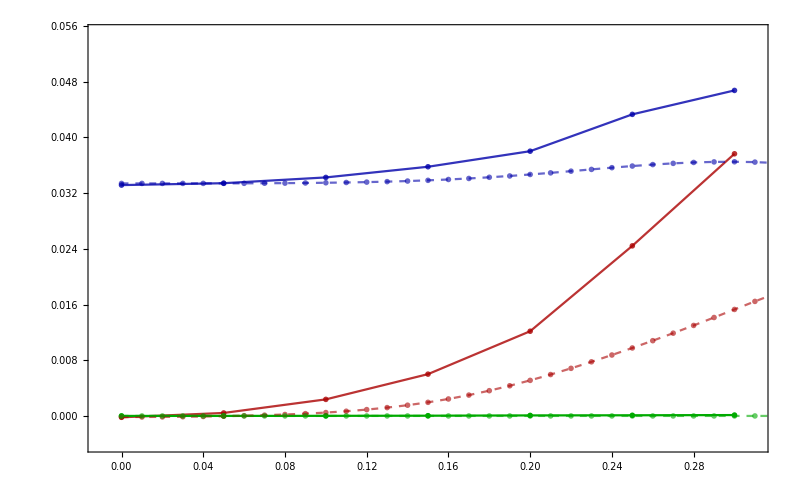

```mathematica
size=0.009;
fig8=Show[
 ListPlot[ { {#[[1]],-#[[2]]}&/@listQ3[[1]] , listQ3[[2]] , listQ3[[3]]  }  , Joined->True ,  PlotRange-> {{-.01,.31},{-.004,.055}} , FrameLabel->{MaTeX["h \\quad [001]",Magnification->2.5] , MaTeX["Q_{\\alpha\\beta}(h)",Magnification->2.5] } , Frame->True, PlotMarkers->"OpenMarkers" ,   FrameStyle ->Directive[Black,22], FrameTicksStyle->Directive[Black,22],ImageSize->800,PlotLegends->Placed[MaTeX[#,Magnification->1.9]&/@{"\\phantom{-Q_{33}}","\\phantom{Q_{11}-Q_{22}}" ,"\\phantom{ Q_{12} }"} ,{0.15,.825} ] ,  PlotStyle->{{ Darker@Blue,Opacity[.8],PointSize[size]} ,{ Darker@Red,Opacity[.8],PointSize[size]},{ Darker@Green,PointSize[size]}  }   ]  
 ,
 ListPlot[ { {#[[1]],-#[[2]]}&/@listpureQ3[[1]] , listpureQ3[[2]] , listpureQ3[[3]]  }  , Joined->True ,  PlotRange-> Automatic , FrameLabel->{MaTeX["h",Magnification->2] , MaTeX["Q_{\\alpha\\beta}(h)",Magnification->2] } , Frame->True, PlotMarkers->"OpenMarkers" ,   FrameStyle ->Directive[Black,20], FrameTicksStyle->Directive[Black,20],ImageSize->600,(* GridLines->None,*)  (*PlotLabel->Style[MaTeX[title,Magnification->2] ,20 ,Black ], *)PlotLegends->Placed[MaTeX[#,Magnification->1.9]&/@{"-Q_{33}","Q_{11}-Q_{22}" ,"Q_{12}"} ,{0.2,.825}  ] ,  PlotStyle->{{ Darker@Blue,Opacity[.6],PointSize[size],Dashed} ,{ Darker@Red,Opacity[.6],PointSize[size],Dashed},{ Darker@Green,Opacity[.6],PointSize[size],Dashed}  } (*, Epilog->Inset[logInset,Scaled[{0.25,0.74}],Center,{0.5,Automatic} ]*)   ]  
]
```

```mathematica
(*TwoAxisListPlot[{f_,g_}]:=Module[{fgraph,ggraph,frange,grange,fticks,gticks,colordata},
colordata={RGBColor[0,0,0.8],RGBColor[0.8,0,0]};
{fgraph,ggraph}=MapIndexed[ListPlot[#,Axes->True,Joined->True,PlotRange->All,ImageSize->600,PlotMarkers->Charting`CommonDump`GraphicsOpenPlotMarkers[][[#2]] ,PlotStyle->{Thickness[0.0038],colordata[[#2]]}  ]&,{f,g}];
(*Print[{fgraph,ggraph}];Abort[];*)
{frange,grange}=(PlotRange/. AbsoluteOptions[#,PlotRange])[[2]]&/@{fgraph,ggraph}; 
gticks=N@FindDivisions[grange,7]; Print[gticks];
gticks=Sort@Join[gticks[[3;;-1]],{g[[-1,2]]}  ]; Print[gticks];
fticks=Quiet@Transpose@{gticks,ToString[NumberForm[Abs[#],{2,4}],StandardForm]&/@Rescale[gticks,grange,frange]};  Print[fticks];
gticks=Quiet@Transpose@{gticks,ToString[NumberForm[#,{2,4}],StandardForm]&/@Rescale[gticks,grange,grange]}; Print[gticks];
Show[ggraph,fgraph/. Graphics[graph_,s___]:>Graphics[GeometricTransformation[graph,RescalingTransform[{{0,1},frange},{{0,1},grange}]],s],
ImageSize->650,Axes->False,Frame->True,FrameStyle->{
{Directive[20,Thickness[0.0042],colordata[[1]] ],Directive[20,Thickness[0.0042],colordata[[2]] ]},{Directive[20,Thickness[0.003], Black],Directive[20, Thickness[0.0032],Black]}
},FrameTicks->{{fticks,gticks},{Automatic,Automatic}}]];

fig8=Show[ TwoAxisListPlot[   listQ3[[{2,1}]]  ] ,   FrameLabel-> {{MaTeX["\\textcolor{darkblue}{Q_{11}-Q_{22} }",Magnification->1.95],MaTeX["\\textcolor{darkred}{Q_{33} }",Magnification->2]  },{MaTeX["h \\quad [001]",Magnification->1.85] , " " }  }  ]*)
```

```mathematica
Export["C:\\User\\lucas\\Desktop\\Wolfram Mathematica\\PhD-codes\\Figures_PhD\\New3\\fig08.pdf"  ,fig8  ];
```

#### now remaking it in units of Qzz(0)

```mathematica
Qzz0 = listQ2[[1,1,2]];
listQ4 =(     Table[{#[[i,1]],Abs[1/Qzz0]#[[i,2]]},{i,1,Length@#}]&/@listQ2  )
```

```mathematica
FindDivisions[  {-0.005867378152172965,1.1356769959604671},5 ]
```

```mathematica
TwoAxisListPlot[{f_,g_}]:=Module[{fgraph,ggraph,frange,grange,fticks,gticks,colordata},
colordata={RGBColor[0,0,0.8],RGBColor[0.8,0,0]};
{fgraph,ggraph}=MapIndexed[ListPlot[#,Axes->True,Joined->True,PlotRange->All,ImageSize->600,PlotMarkers->Charting`CommonDump`GraphicsOpenPlotMarkers[][[#2]] ,PlotStyle->{Thickness[0.0038],colordata[[#2]]}  ]&,{f,g}];
(*Print[{fgraph,ggraph}];Abort[];*)
{frange,grange}=(PlotRange/. AbsoluteOptions[#,PlotRange])[[2]]&/@{fgraph,ggraph}; 
gticks=N@FindDivisions[grange,7]; Print[gticks];
gticks=Sort@Join[gticks[[3;;-1]],{g[[-1,2]]}  ]; Print[gticks];
fticks=Quiet@Transpose@{gticks,ToString[NumberForm[Abs[#],{2,1}],StandardForm]&/@Rescale[gticks,grange,frange]};  Print[fticks];
gticks=Quiet@Transpose@{gticks,ToString[NumberForm[#,{2,1}],StandardForm]&/@Rescale[gticks,grange,grange]}; Print[gticks];
Show[ggraph,fgraph/. Graphics[graph_,s___]:>Graphics[GeometricTransformation[graph,RescalingTransform[{{0,1},frange},{{0,1},grange}]],s],
ImageSize->650,Axes->False,Frame->True,FrameStyle->{
{Directive[20,Thickness[0.0042],colordata[[1]] ],Directive[20,Thickness[0.0042],colordata[[2]] ]},{Directive[20,Thickness[0.003], Black],Directive[20, Thickness[0.0032],Black]}
},FrameTicks->{{fticks,gticks},{Automatic,Automatic}}]];




fig8=Show[ TwoAxisListPlot[   listQ4[[{2,1}]]  ] ,   FrameLabel-> {{MaTeX["\\textcolor{darkblue}{Q_{xx}-Q_{yy} }",Magnification->1.95],MaTeX["\\textcolor{darkred}{Q_{zz} }",Magnification->2]  },{MaTeX["h \\quad [001]",Magnification->1.85] ,}}  ]
```

```mathematica
Export["C:\\User\\lucas\\Desktop\\Wolfram Mathematica\\PhD-codes\\Figures_PhD\\Fig8.pdf"  ,fig8  ];
```

#### other

```mathematica
(*(*
*)pmax=Length@parameters[[1]];
Module[{epilog={},title,plots,fit=Array[Null,{3,pmax}] ,chargeList,listQ ,fitName,name,ceilpmax ,Np,ΔL=1},
Do[ Module[{ λ,  J,K,Γ, h , t, d,κ,tp=⌈p/Length@hV⌉,hp=Mod[p,Length@hV,1]}, 		 
	{J,K,Γ,h}=parameters⟦1,p⟧[[1;;4]]; 
	d=parameters[[1,p]][[8]];
	t=ts[[tp]]; 
title=StringReplace["\\text{Finite size analize: Quadrupole } J=X1,\\, \\Gamma=X3",
{"X1"->ToString@N@( Round[1000 #]/1000)&@J,"X2"->ToString@N@( Round[1000 #]/1000)&@K,"X3"->ToString@N@( Round[1000 #]/1000)&@Γ   }      ];
        AppendTo[epilog,
StringReplace["h=(Y1,Y2,Y3)",
{"Y1"->ToString@d[[1]],"Y2"->ToString@d[[2]],"Y3"->ToString@d[[3]]}]       ]
(*nameComplement=StringReplace["t=X1_h=X2-ac=X4",{"X1"-> ToString[tV[[tp]]],"X2"-> ToString[hV[[hp]]], "X4"-> ToString[acuracy]  }];      *)

],{p,1,pmax,Δp }];
Np=⌊(pmax-1)/Δp⌋+1;
ceilpmax=(1+(Np-1) Δp);
chargeList= chargeHex;
listQ={    
     Table[  {parameters[[1,p]][[8,1]],Qzz@chargeHex[[p,1]]   },{p,1,pmax}] ,
     Table[  {parameters[[1,p]][[8,1]],QxxQyy@chargeHex[[p,1]]   },{p,1,pmax}] ,
     Table[  {parameters[[1,p]][[8,1]],Qxy@chargeHex[[p,1]]   },{p,1,pmax}] ,
     Table[  {parameters[[1,p]][[8,1]],Ani@chargeHex[[p,1]]   },{p,1,pmax}]             };
listQ2=listQ;
(*Print[ToString[    Np==Length@listQ[[1]]     ] ];

 fit =Table[ Fit[listQ[[α]],{1,x},x],{α,1,4}];
fitt=fit;
fitName=Table[ 
StringReplace[ ToString@TeXForm@StandardForm[ ScientificForm[fit[[α]],4]  ] ,  {"\\left("->"","\\right)"->"","x"->" \\, L^{-1}"}  ]
,{α,1,4}  ];
fittName=fitName;*)
Print[ ListPlot[#, Joined->True ,Frame->True,ImageSize->600,PlotRange->{{0,0.36},Automatic}, FrameStyle->Directive[Black,20], PlotMarkers->"OpenMarkers"                ]&/@listQ ];
Abort[];
plots={
Show[{ListPlot[ listQ[[1]], Joined->True ,Frame->True,ImageSize->1000,PlotRange->{{0,0.04},Automatic},FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{"1/ L \\; ", " Q_{zz} "}, FrameStyle->Directive[Black,20],PlotStyle->{Darker[Red],Darker[Green],Darker[Blue]},   PlotLabel->MaTeX[title,Magnification->1.4]   , PlotMarkers->"OpenMarkers"    ,PlotLegends-> Placed[Table[MaTeX[epilog[[p]],Magnification->1.15],{p,1,Np}] ,{Scaled[{0.02,.77}],{0,0} } ] 
(*,Epilog->Placed[MaTeX[epilog,Magnification->1.3], {Scaled[{0.01,.9}],{0,0} }]  *)                 ],
Plot[Evaluate@fit[[1]] , {x,0.001,0.06} ,PlotStyle->{{Darker[Red],Opacity[0.8],Thickness[0.0023]},{Darker[Green],Opacity[0.8],Thickness[0.0023]},{Darker[Blue],Opacity[0.8],Thickness[0.0023]}   } ,PlotLegends-> Placed[ MaTeX[#,Magnification->1.2]&/@fitName[[1]] , {Scaled[{0.02,.05}],{0,0} } ]  ]     } 
],
(*Evaluate it needed to plot "fit" since Mathematica treats fit[[α]] as a Table and usually first evaluate the Plot and then the Table. This is a trick to properlly display the colors we. *)
Show[{ListPlot[ listQ[[2]], Joined->True ,Frame->True,ImageSize->1000,PlotRange->{{0,0.04},Full },FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{"1/ L \\; ", " Q_{xx}-Q_{yy} "}, FrameStyle->Directive[Black,20],PlotStyle->{{Darker[Red]},{Darker[Green]},{Darker[Blue]}},   PlotLabel->MaTeX[title,Magnification->1.4]   , PlotMarkers->{"OpenMarkers"}    ,PlotLegends-> Placed[Table[MaTeX[epilog[[p]],Magnification->1.15],{p,1,Np}] ,{Scaled[{0.02,.77}],{0,0} } ]            ],
Plot[ Evaluate@fit[[2]] , {x,0.001,0.06} ,PlotStyle->{{Darker[Red] ,Thickness[0.0023]},{Darker[Green] ,Thickness[0.0023]},{Darker[Blue] ,Thickness[0.0023]}   } ,PlotLegends-> Placed[   MaTeX[#,Magnification->1.2]&/@fitName[[2]] , {Scaled[{0.02,.025}],{0,0} } ]  ]     } 
],
Show[{ListPlot[ listQ[[3]], Joined->True ,Frame->True,ImageSize->1000,PlotRange->{{0,0.04},MinMax[ listQ[[3]][[;;,;;,2]],Scaled[1] ]       },FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{"1/ L \\; ", " 2 Q_{xy} "}, FrameStyle->Directive[Black,20],PlotStyle->{{Darker[Red]},{Darker[Green]},{Darker[Blue]}},   PlotLabel->MaTeX[title,Magnification->1.4]   , PlotMarkers->{"OpenMarkers"}    ,PlotLegends-> Placed[Table[MaTeX[epilog[[p]],Magnification->1.15],{p,1,Np}] ,{Scaled[{0.02,.77}],{0,0} } ]               ],
Plot[ Evaluate@fit[[3]] , {x,0.001,0.06} ,PlotStyle->{{Darker[Red] ,Thickness[0.0023]},{Darker[Green] ,Thickness[0.0023]},{Darker[Blue] ,Thickness[0.0023]}   } ,PlotLegends-> Placed[   MaTeX[#,Magnification->1.2]&/@fitName[[3]] , {Scaled[{0.02,.025}],{0,0} } ]  ]     } 
],
Show[{ListPlot[ listQ[[4]], Joined->True ,Frame->True,ImageSize->1000,PlotRange->{{0,0.04}, Full},FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{"1/ L \\; ", "\\text{Anisotropy } \\vert Q_{xx}^{\\prime}-Q_{yy}^{\\prime}\\vert "}, FrameStyle->Directive[Black,20],PlotStyle->{{Darker[Red]},{Darker[Green]},{Darker[Blue]}},   PlotLabel->MaTeX[title,Magnification->1.4]   , PlotMarkers->{"OpenMarkers"}    ,PlotLegends-> Placed[Table[MaTeX[epilog[[p]],Magnification->1.15],{p,1,Np}] ,{Scaled[{0.02,.82}],{0,0} } ]               ],
Plot[ Evaluate@fit[[4]] , {x,0.001,0.06} ,PlotStyle->{{Darker[Red] ,Thickness[0.0023]},{Darker[Green] ,Thickness[0.0023]},{Darker[Blue] ,Thickness[0.0023]}   } ,PlotLegends-> Placed[   MaTeX[#,Magnification->1.2]&/@fitName[[4]] , {Scaled[{0.02,.025}],{0,0} } ]  ]     } 
]};
Print[plots];
name=StringReplace["h=X1-X2_L=X3-X4",{"X1"->  ToString[hV[[1]]], "X2"->  ToString[hV[[ceilpmax]]], "X3"-> ToString[Ls[[1]] ], "X4"-> ToString[Ls[[-1]] ]  }]; ;
(*Export[ FileNameJoin[{ NotebookDirectory[], StringReplace["\\Figures\\pure\\QUADRUPOLE_FINITE_SIZE\\Qzz_FINITE_SIZE_XX_pure.pdf","XX"->name]  }],      plots[[1]]      ];
Export[ FileNameJoin[{ NotebookDirectory[], StringReplace["\\Figures\\pure\\QUADRUPOLE_FINITE_SIZE\\QxxQyy_FINITE_SIZE_XX_pure.pdf","XX"->name]  }],plots[[2]]      ];
Export[ FileNameJoin[{ NotebookDirectory[], StringReplace["\\Figures\\pure\\QUADRUPOLE_FINITE_SIZE\\Qxy_FINITE_SIZE_XX_pure.pdf","XX"-> name]  }],      plots[[3]]      ];
Export[ FileNameJoin[{ NotebookDirectory[], StringReplace["\\Figures\\pure\\QUADRUPOLE_FINITE_SIZE\\Qani_FINITE_SIZE_XX_pure.pdf","XX"-> name]  }],    plots[[4]]      ];*)
 ]*)
```

```mathematica
(*TeXForm@Column@N@(  Round[10000 chargeHex[[;;,-3]] ]/10000)
anisotropy[Q_]:=Module[{q1,q2},{q1,q2}=Eigenvalues@Q[[1;;2,1;;2]] ;q1-q2]
Column@N@(  Round[10000 chargeHex[[1]]    ]/10000)*)
```

```mathematica
(*plot1=ListPlot[ listQ2[[2]], 
Joined->True ,Frame->True,ImageSize->1000,PlotRange->{{-.004,0.354},Automatic},FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{"h \\quad [001]  \\; ", "Q_{xx}-Q_{yy} "}, (*FrameStyle->Directive[Black,20],*)
PlotStyle->{RGBColor[0,0,0.8] }   , PlotMarkers->"OpenMarkers"    ,
PlotLegends-> Placed[ {  MaTeX["\\textcolor{darkblue}{Q_{xx}-Q_{yy} }",Magnification->2] } ,{Scaled[{0.02,.85}],{0,0} } ],
(*ImagePadding->25,*)Frame->{True,True,True,False},FrameStyle->Directive[{Automatic,RGBColor[0,0,0.8],Automatic,Automatic} ,20]
];
plot2=ListPlot[ listQ2[[1]], 
Joined->True ,Frame->True,ImageSize->1000,PlotRange->{{-.004,0.354},Automatic},FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{"h \\quad [001]  \\; ", " Q_{zz}"},(* FrameStyle->Directive[Black,20],*)
PlotStyle->{RGBColor[0.8,0,0] }   , PlotMarkers->Charting`CommonDump`GraphicsOpenPlotMarkers[][[2]],
PlotLegends-> Placed[ {  MaTeX["\\textcolor{darkred}{Q_{zz} }",Magnification->2] } ,{Scaled[{0.02,.77}],{0,0} } ],
(*ImagePadding->25,*)Axes->False,Frame->{False,False,False,True},FrameTicks->{{None,All},{None,None}},FrameStyle->Directive[{Automatic,Automatic,Automatic,RGBColor[0.8,0,0]},20]
  ];
{plot1,plot2}*)
```

## Fig 8 -- quadrupole - h

```mathematica
NbName="705"; ρ=-1.92289705 10^(-6);
		Ls = Range[40,40,2]; 				tV={0};		
Qzz[charge_]:=1/2(charge[[5]][[3,3]] -charge[[5]][[1,1]] -charge[[5]][[2,2]] );
QxxQyy[charge_]:=charge[[5]][[1,1]] -charge[[5]][[2,2]];
Qxy[charge_]:=1/2(charge[[5]][[1,2]] +charge[[5]][[2,1]] );
anisotropy[Q_]:=√(Q⟦1,1⟧^2+4 Q⟦1,2⟧ Q⟦2,1⟧-2 Q⟦1,1⟧ Q⟦2,2⟧+Q⟦2,2⟧^2);    (*  2 Sqrt[ ((Qxx-Qyy)/2)^2+ QxyQyx   ] 00  *)
Ani[charge_]:=anisotropy@charge[[5]] ;


		(*tV={2};  hV= Table[{ h,180/π ArcTan[√2],180}  ,{h,{0,.05,.1,.15,.2,.25,.3}}];*)

		 acuracy=5;   
		tV={4}; 
		hV= Flatten[  Table[{ h+s*.0125,180/π ArcTan[Sqrt[2]],180}  ,{h,{  0,.05,.1 , .15,.2,.25  }} ,{s,{  0,1,2,3  }}   ], 1]; 	
steps=50;  
		ts = Table[ {5x,160,-12x,0,-60},{x,tV}];
		hs = Table[  h[[1]]  hAngle[h[[2]],h[[3]]] , {h,hV}];  hV=N@hV[[1;;21]];
		eVs= Table[1700 x, {x,0,0,0.099999}]; 

		parameters=Chop@Table[
Flatten[ Table[ {N@Jr[0,JH,U,ts[[t]] ],N@Kr[0,JH,U,ts[[t]]],N@Γr[0,JH,U,ts[[t]]],hs[[h]] ,N@Jr[eVs[[ev]],JH,U,ts[[t]] ],N@Kr[eVs[[ev]],JH,U,ts[[t]]],N@Γr[eVs[[ev]],JH,U,ts[[t]]],hV[[h]],tV[[t]],eVs[[ev]]} , {t,1,Length@tV},  {h,1,Length@hV}],1] ,  {ev,1,Length@eVs}];

sizeQzz[charge_]:=Table[ {charge[[i,1]],charge[[i,-1]][[3,3]]  },{i,1,Length@charge}   ];sizeQxxQyy[charge_]:=Table[ {charge[[i,1]],charge[[i,-1]][[1,1]] -charge[[i,-1]][[2,2]]  },{i,1,Length@charge}   ];sizeQxy[charge_]:=Table[ {charge[[i,1]],charge[[i,-1]][[1,2]] +charge[[i,-1]][[2,1]]  },{i,1,Length@charge}   ];

anisotropy[Q_]:=√(Q⟦1,1⟧^2+4 Q⟦1,2⟧ Q⟦2,1⟧-2 Q⟦1,1⟧ Q⟦2,2⟧+Q⟦2,2⟧^2);    (*  2 Sqrt[ ((Qxx-Qyy)/2)^2+ QxyQyx   ]   *)
sizeAni[charge_]:=Table[ {charge[[i,1]],anisotropy@charge[[i,-1]]  },{i,1,Length@charge}   ];
```

```mathematica
pmax=Length@parameters[[1]];Δp=1;     chargeHex=Table[{},pmax];
Module[ {J,K,Γ}, {J,K,Γ}=parameters⟦1,1⟧[[1;;3]];Print["J=",J,"; K=",K,"; Γ=",Γ,"; "];]
Do[ 
Module[{χ,ω,ξ,jG,LG,EnG ,gauge="g4", Jv,Kv,Γv,J,K,Γ,L,Nc,h ,u0,H,T,u,t,t0,c11,c21,c12,c22,sNN,sNNN,δn,δn1,d,title,κ,tp=⌈p/Length@hV⌉,hp=Mod[p,Length@hV,1]}, 		 
	{J,K,Γ,h}=parameters⟦1,p⟧[[1;;4]];L=Ls⟦l⟧; Nc=L^2;
	{jG,LG,χ,ω,ξ,EnG}=Chop@loadData[toPath[parameters[[1,p]],L,acuracy, gauge,NbName ]  ];

	Kv= uniform[K,L,L];Jv=uniform[J,L,L];Γv=uniform[Γ,L,L];
	d=parameters[[1,p]][[8]];
 	If[  Norm[h]==0, κ=0,κ= N@(Round[10000toKappa[h]   ]/10000) ];
	u0= gauge4v[ uniformU[-1,L] ,L];     
	t=ts[[tp]];     
nameComplement=StringReplace["t=X1_h=X2-L=X3-ac=X4",{"X1"-> ToString[tV[[tp]]],"X2"-> ToString[hV[[hp]]],"X3"-> ToString[L],"X4"-> ToString[acuracy]  }];               
c11=coefTriang11[JH,U,t];c21=coefTriang21[JH,U,t];  c12=coefTriang12[JH,U,t];c22=coefTriang22[JH,U,t];  
		sNN = sscNN[χ,ω,L]; sNNN= sscNNN[ξ,ω,L];
		(*δn=densityTriang[L,c11,c21,c12,c22,sNN,0sNNN];*)
δn=densityTriangVortexHex[L,c11,c21,c12,c22,sNN,sNNN,1,5];
(*δn0=δn; ξ0=ξ; sNN0=sNN;sNNN0=sNNN;χ0=χ;*)
(* graphics*)
title=StringReplace["J=X1,\\; \\Gamma=X3 \\;h=(Y1,Y2,Y3)",{"X1"->ToString[N@(Round[1000J]/1000)],"X2"->ToString@N@(Round[1000K]/1000),"X3"-> ToString@N@(Round[1000Γ]/1000),"Y1"->ToString@d[[1]],"Y2"->ToString@d[[2]],"Y3"->ToString@d[[3]]}];
Module[{R,q,dip,Q,v}, L=Ls[[l]]; R=Min[ 5 ];
Print["L=",L,"; R=",R,"; t=",t,"; ", nameComplement];
Do[     q[v]=chargeVortexHex[δn,L,v,R];dip[v]=dipoleVortexHex[δn,L,v,R];Q[v]=quadrupoleVortexHex[δn,L,v,R];      ,{v,{1} }];
AppendTo[chargeHex[[p]],  {L,R,q[1],dip[1],Q[1]}   ];
Print[ "q1=",q[1],"; d1= ",MatrixForm[dip[1]],"; Q1= "MatrixForm[Q[1]]    ];   
] ;
],{p,1, pmax,Δp  },{l,1,Length@Ls,1}]
```

J=-0.0398424; K=-1.; Γ=0.301485;

L=40; R=5; t={20,160,-48,0,-60}; t=4_h={0., 54.7356, 180.}-L=40-ac=5

q1=-0.00767007; d1= (1.82724×10^-8
-3.99557×10^-8); Q1=  (0.704702 | 2.79215×10^-6 | 0.
2.79215×10^-6 | 0.711989 | 0.
0. | 0. | -1.41669)

L=40; R=5; t={20,160,-48,0,-60}; t=4_h={0.0125, 54.7356, 180.}-L=40-ac=5

q1=-0.00769214; d1= (8.19446×10^-6
0.0000134989); Q1=  (0.707246 | 0.000151227 | 0.
0.000151227 | 0.71062 | 0.
0. | 0. | -1.41787)

L=40; R=5; t={20,160,-48,0,-60}; t=4_h={0.025, 54.7356, 180.}-L=40-ac=5

q1=-0.00775889; d1= (0.0000329556
0.0000540049); Q1=  (0.714928 | 0.00060699 | 0.
0.00060699 | 0.706493 | 0.
0. | 0. | -1.42142)

L=40; R=5; t={20,160,-48,0,-60}; t=4_h={0.0375, 54.7356, 180.}-L=40-ac=5

q1=-0.007871; d1= (0.0000735898
0.000123782); Q1=  (0.727864 | 0.00135551 | 0.
0.00135551 | 0.699575 | 0.
0. | 0. | -1.42744)

L=40; R=5; t={20,160,-48,0,-60}; t=4_h={0.05, 54.7356, 180.}-L=40-ac=5

q1=-0.00803007; d1= (0.000129079
0.000226912); Q1=  (0.746251 | 0.00237528 | 0.
0.00237528 | 0.689803 | 0.
0. | 0. | -1.43605)

L=40; R=5; t={20,160,-48,0,-60}; t=4_h={0.0625, 54.7356, 180.}-L=40-ac=5

q1=-0.00824041; d1= (0.000202089
0.000353037); Q1=  (0.770328 | 0.00376052 | 0.
0.00376052 | 0.67697 | 0.
0. | 0. | -1.4473)

L=40; R=5; t={20,160,-48,0,-60}; t=4_h={0.075, 54.7356, 180.}-L=40-ac=5

q1=-0.00850781; d1= (0.000287953
0.000521952); Q1=  (0.80061 | 0.00537429 | 0.
0.00537429 | 0.661044 | 0.
0. | 0. | -1.46165)

L=40; R=5; t={20,160,-48,0,-60}; t=4_h={0.0875, 54.7356, 180.}-L=40-ac=5

q1=-0.00884274; d1= (0.000387607
0.000732091); Q1=  (0.837652 | 0.00725095 | 0.
0.00725095 | 0.641754 | 0.
0. | 0. | -1.47941)

L=40; R=5; t={20,160,-48,0,-60}; t=4_h={0.1, 54.7356, 180.}-L=40-ac=5

q1=-0.00867384; d1= (0.000242823
0.000709526); Q1=  (0.841734 | 0.00529839 | 0.
0.00529839 | 0.63547 | 0.
0. | 0. | -1.4772)

L=40; R=5; t={20,160,-48,0,-60}; t=4_h={0.1125, 54.7356, 180.}-L=40-ac=5

q1=-0.00978547; d1= (0.000628355
0.00129567); Q1=  (0.935463 | 0.0117677 | 0.
0.0117677 | 0.591618 | 0.
0. | 0. | -1.52708)

L=40; R=5; t={20,160,-48,0,-60}; t=4_h={0.125, 54.7356, 180.}-L=40-ac=5

q1=-0.0104538; d1= (0.000771909
0.00166194); Q1=  (0.998837 | 0.014396 | 0.
0.014396 | 0.559609 | 0.
0. | 0. | -1.55845)

L=40; R=5; t={20,160,-48,0,-60}; t=4_h={0.1375, 54.7356, 180.}-L=40-ac=5

q1=-0.0113237; d1= (0.000935417
0.00209348); Q1=  (1.07443 | 0.0172885 | 0.
0.0172885 | 0.521713 | 0.
0. | 0. | -1.59614)

L=40; R=5; t={20,160,-48,0,-60}; t=4_h={0.15, 54.7356, 180.}-L=40-ac=5

q1=-0.0107565; d1= (0.000515506
0.00178007); Q1=  (1.05821 | 0.0112011 | 0.
0.0112011 | 0.526045 | 0.
0. | 0. | -1.58425)

L=40; R=5; t={20,160,-48,0,-60}; t=4_h={0.1625, 54.7356, 180.}-L=40-ac=5

q1=-0.0141394; d1= (0.00154547
0.00271016); Q1=  (1.27265 | 0.0243256 | 0.
0.0243256 | 0.41777 | 0.
0. | 0. | -1.69042)

L=40; R=5; t={20,160,-48,0,-60}; t=4_h={0.175, 54.7356, 180.}-L=40-ac=5

q1=-0.0146422; d1= (0.00210651
0.00559916); Q1=  (1.44262 | 0.0247247 | 0.
0.0247247 | 0.351535 | 0.
0. | 0. | -1.79416)

L=40; R=5; t={20,160,-48,0,-60}; t=4_h={0.1875, 54.7356, 180.}-L=40-ac=5

q1=-0.0166316; d1= (0.00241638
0.00735152); Q1=  (1.58801 | 0.0284457 | 0.
0.0284457 | 0.265156 | 0.
0. | 0. | -1.85317)

L=40; R=5; t={20,160,-48,0,-60}; t=4_h={0.2, 54.7356, 180.}-L=40-ac=5

q1=-0.0136735; d1= (-0.00115238
0.0127984); Q1=  (1.51496 | -0.0292122 | 0.
-0.0292122 | 0.334025 | 0.
0. | 0. | -1.84899)

L=40; R=5; t={20,160,-48,0,-60}; t=4_h={0.2125, 54.7356, 180.}-L=40-ac=5

q1=-0.0260417; d1= (0.0032193
0.0119418); Q1=  (2.08087 | 0.0421656 | 0.
0.0421656 | -0.052088 | 0.
0. | 0. | -2.02878)

L=40; R=5; t={20,160,-48,0,-60}; t=4_h={0.225, 54.7356, 180.}-L=40-ac=5

q1=-0.0373685; d1= (0.00447125
0.015049); Q1=  (2.58077 | 0.0621021 | 0.
0.0621021 | -0.538256 | 0.
0. | 0. | -2.04251)

L=40; R=5; t={20,160,-48,0,-60}; t=4_h={0.2375, 54.7356, 180.}-L=40-ac=5

q1=-0.0611931; d1= (0.00556544
0.0186629); Q1=  (3.6095 | 0.0995309 | 0.
0.0995309 | -1.30127 | 0.
0. | 0. | -2.30824)

L=40; R=5; t={20,160,-48,0,-60}; t=4_h={0.25, 54.7356, 180.}-L=40-ac=5

q1=-0.0470271; d1= (0.0013902
0.0147546); Q1=  (3.12282 | 0.0354729 | 0.
0.0354729 | -0.818785 | 0.
0. | 0. | -2.30403)

```mathematica
Module[{pmax=Length[chargeHex]   }  ,
listQ2 = {    
     Table[  {parameters[[1,p]][[8,1]],Qzz@chargeHex[[p,1]]   },{p,1,pmax}] ,
     Table[  {parameters[[1,p]][[8,1]],QxxQyy@chargeHex[[p,1]]   },{p,1,pmax}] ,
     Table[  {parameters[[1,p]][[8,1]],Qxy@chargeHex[[p,1]]   },{p,1,pmax}] ,
     Table[  {parameters[[1,p]][[8,1]],Ani@chargeHex[[p,1]]   },{p,1,pmax}]     }
];
```

```mathematica
Overlay[{plot1,plot2}]
```

```mathematica
SetOptions[MaTeX,"Preamble"->{"\\usepackage{color}","\\definecolor{darkred}{rgb}{.8,0,0}\\definecolor{darkblue}{rgb}{0,0,.8}"}]
```

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage{color},\definecolor{darkred}{rgb}{.8,0,0}\definecolor{darkblue}{rgb}{0,0,.8}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→12,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

```mathematica
{MaTeX["\\textcolor{darkred}{Q_{zz} }",Magnification->2.5] ,MaTeX["\\textcolor{darkblue}{Q_{xx}-Q_{yy} }",Magnification->2.5] }
```

#### pure Kitaev

```mathematica
NbName="709"; ρ=-1.92289705 10^(-6);
		Ls = Range[42,42,2]; 				tV={0};		hV=Table[{h,180/π ArcTan[Sqrt[2]],180} ,{h,0.,.35,.01}];

		steps=500;				acuracy=10;  eVs=Table[1700 x, {x,0,0,0.0499999}]; 

ts = Table[ {5x,160,-12x,0,-60},{x,tV}];
hs =Table[  h[[1]]  hAngle[h[[2]],h[[3]]] , {h,hV}]; hs=N@Simplify@hs;  hV=N@hV;
eV0=0;U=2600;JH=300;

parameters=Chop[#,10^-5]&@N@Table[Flatten[ Table[ {N@Jr[0,JH,U,ts[[t]] ],N@Kr[0,JH,U,ts[[t]]],N@Γr[0,JH,U,ts[[t]]],hs[[h]] ,
N@Jr[eVs[[ev]],JH,U,ts[[t]] ],N@Kr[eVs[[ev]],JH,U,ts[[t]]],N@Γr[eVs[[ev]],JH,U,ts[[t]]],hV[[h]],tV[[t]],eVs[[ev]]} , {t,1,Length@tV},  {h,1,Length@hV}],1] ,  {ev,1,Length@eVs}];
```

```mathematica
(*pmax=Length@parameters[[1]];Δp=1;     ChargeHex00=Table[{},pmax];*)
Module[{gauge="g4",ev=1,L=Ls[[1]],Nc,h ,p=1}, 		 
ChargeHex00=LoadquadrupolePure[parameters[[ev,p]],L,acuracy,gauge,{hV[[1]],hV[[-1]]}];(*

AppendTo[ChargeHex00[[p]] ,chargeHex00 ]*)

]
```

```mathematica
Module[{chargeHex=ChargeHex00,pmax=Length@ChargeHex00},
listpureQ = {    
     Table[  {parameters[[1,p]][[8,1]],Qzz@chargeHex[[p]]   },{p,1,pmax}] ,
     Table[  {parameters[[1,p]][[8,1]],QxxQyy@chargeHex[[p]]   },{p,1,pmax}] ,
     Table[  {parameters[[1,p]][[8,1]],Qxy@chargeHex[[p]]   },{p,1,pmax}] ,
     Table[  {parameters[[1,p]][[8,1]],Ani@chargeHex[[p]]   },{p,1,pmax}]     }
];
```

```mathematica
(*listpureQ3 =(     Table[{#[[i,1]],Abs[ρ 1/ttU]#[[i,2]]},{i,1,Length@#}]&/@listpureQ  );*)
```

#### now remaking it in units of (t_(2^))^2 t_2'/U^3

```mathematica
(*Module[{pmax=Length[chargeHex]   }  ,
listQ2 = {    
     Table[  {parameters[[1,p]][[8,1]],Qzz@chargeHex[[p,1]]   },{p,1,pmax}] ,
     Table[  {parameters[[1,p]][[8,1]],QxxQyy@chargeHex[[p,1]]   },{p,1,pmax}] ,
     Table[  {parameters[[1,p]][[8,1]],Qxy@chargeHex[[p,1]]   },{p,1,pmax}] ,
     Table[  {parameters[[1,p]][[8,1]],Ani@chargeHex[[p,1]]   },{p,1,pmax}]     }
];*)
```

```mathematica
ρ=-1.92289705 10^-6;
listQ3 =(     Table[{#[[i,1]],Abs[ρ 1/ttU]#[[i,2]]},{i,1,21}]&/@listQ2  );

listpureQ3 =(     Table[{#[[i,1]],Abs[ρ 1/ttU]#[[i,2]]},{i,1,Length@#}]&/@listpureQ  );
```

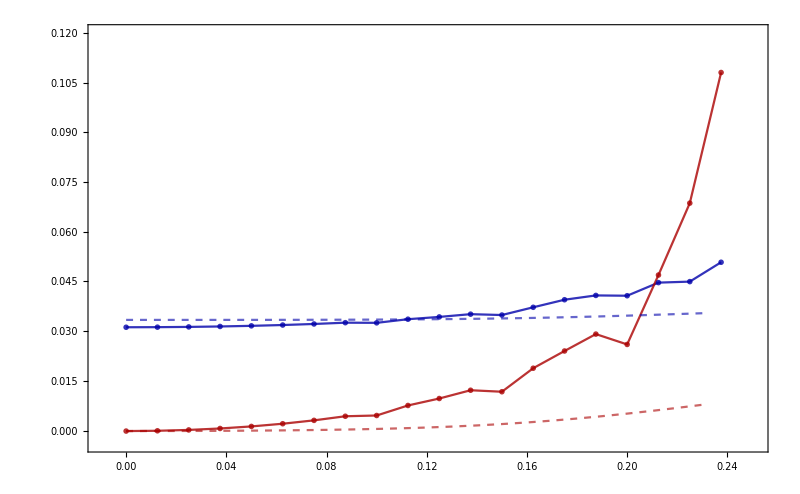

```mathematica
size=0.009;
fig8=Show[
 ListPlot[ { {#[[1]],-#[[2]]}&/@listQ3[[1]] , listQ3[[2]] (*, listQ3[[3]]  *)}  , Joined->True ,  PlotRange-> {{-.01,.251},{-.004,.12}} , FrameLabel->{MaTeX["h \\quad [001]",Magnification->2.5] , MaTeX["Q_{\\alpha\\beta}(h)",Magnification->2.5] } , Frame->True, PlotMarkers->"OpenMarkers" ,   FrameStyle ->Directive[Black,22], FrameTicksStyle->Directive[Black,22],ImageSize->800,PlotLegends->Placed[MaTeX[#,Magnification->1.9]&/@{"\\phantom{-Q_{33}}","\\phantom{Q_{11}-Q_{22}}" ,"\\phantom{ Q_{12} }"} ,{0.15,.825} ] ,  PlotStyle->{{ Darker@Blue,Opacity[.8],PointSize[size]} ,{ Darker@Red,Opacity[.8],PointSize[size]},{ Darker@Green,PointSize[size]}  }   ]  
 ,
 ListPlot[ { {#[[1]],-#[[2]]}&/@listpureQ3[[1]] , listpureQ3[[2]] (*, listpureQ3[[3]]*)  }  , Joined->True ,  PlotRange-> Automatic , FrameLabel->{MaTeX["h",Magnification->2] , MaTeX["Q_{\\alpha\\beta}(h)",Magnification->2] } , Frame->True, PlotMarkers->None ,   FrameStyle ->Directive[Black,20], FrameTicksStyle->Directive[Black,20],ImageSize->600,(* GridLines->None,*)  (*PlotLabel->Style[MaTeX[title,Magnification->2] ,20 ,Black ], *)PlotLegends->Placed[MaTeX[#,Magnification->1.9]&/@{"-Q_{33}","Q_{11}-Q_{22}" ,"Q_{12}"} ,{0.21,.825}  ] ,  PlotStyle->{{ Darker@Blue,Opacity[.6],PointSize[size],Dashed} ,{ Darker@Red,Opacity[.6],PointSize[size],Dashed},{ Darker@Green,Opacity[.6],PointSize[size],Dashed}  } (*, Epilog->Inset[logInset,Scaled[{0.25,0.74}],Center,{0.5,Automatic} ]*)   ]  

]
```

```mathematica
listΔQPure
```

{{0,0.00463873},{0.01,0.00450077},{0.02,0.00408193},{0.03,0.00336677}}

```mathematica
Module[{inset},
listΔQ =(     Table[{#[[1,i,1]],Abs[ #[[2,i,2]] /   #[[1,i,2]]    ]},{i,1,20}]&@listQ3  );
listΔQPure =(     Table[{#[[1,i,1]],Abs[ #[[2,i,2]] /   #[[1,i,2]]    ]},{i,1,Length@listpureQ3[[1]]}]&@listpureQ3  );

size=0.009;
inset=Show[
 ListPlot[ { {#[[1]],-#[[2]]}&/@listQ3[[1]][[1;;-2]] , listQ3[[2]][[1;;-2]](*, listQ3[[3]]  *)}  , Joined->True ,  PlotRange-> {{-.01,.251},{-.004,.12}} , FrameLabel->{MaTeX["h",Magnification->2.5] , MaTeX["  ",Magnification->2] } , Frame->True, PlotMarkers->"OpenMarkers" ,   FrameStyle ->Directive[Black,16], FrameTicksStyle->Directive[Black,18],ImageSize->800,PlotLegends->Placed[MaTeX[#,Magnification->1.4]&/@{"\\phantom{-Q_{33}}","\\phantom{Q_{11}-Q_{22}}" ,"\\phantom{ Q_{12} }"} ,{0.19,.825} ] ,  PlotStyle->{{ Darker@Blue,Opacity[.8],PointSize[size]} ,{ Darker@Red,Opacity[.8],PointSize[size]},{ Darker@Green,PointSize[size]}  }   ]  
 ,
 ListPlot[ { {#[[1]],-#[[2]]}&/@listpureQ3[[1]] , listpureQ3[[2]] (*, listpureQ3[[3]]*)  }  , Joined->True ,  PlotRange-> Automatic   , Frame->True, PlotMarkers->None ,   FrameStyle ->Directive[Black,20], FrameTicksStyle->Directive[Black,20],ImageSize->600, PlotLegends->Placed[MaTeX[#,Magnification->1.9]&/@{"-Q_{33}","Q_{11}-Q_{22}" ,"Q_{12}"} ,{0.25,.825}  ] ,  PlotStyle->{{ Darker@Blue,Opacity[.6],PointSize[size],Dashed} ,{ Darker@Red,Opacity[.6],PointSize[size],Dashed},{ Darker@Green,Opacity[.6],PointSize[size],Dashed}  } (*, Epilog->Inset[logInset,Scaled[{0.25,0.74}],Center,{0.5,Automatic} ]*)   ]  
];
Fig8inset=Show[
ListPlot[  listΔQ , Joined->True ,  PlotRange-> {{-.01,.251},{-.04,2.2}} , FrameLabel->{MaTeX["h \\quad [001]",Magnification->2.5] , MaTeX["\\Delta Q"(* "= |Q_{11}-Q_{22}|/|Q_{33}|"*),Magnification->2.5] } , Frame->True, PlotMarkers->"●" ,   FrameStyle ->Directive[Black,22], FrameTicksStyle->Directive[Black,22],ImageSize->800,(*PlotLegends->Placed[MaTeX[#,Magnification->1.9]&/@{"\\phantom{-Q_{33}}","\\phantom{Q_{11}-Q_{22}}" ,"\\phantom{ Q_{12} }"} ,{0.15,.825} ] ,*) 
Epilog->{ Dashed,White,  Line[{     {0.21,√(9/7)},{0.22,√(9/7)}    }]  ,
Inset[inset,{0.02,.9},{0,0},Scaled[.75]]},
  PlotStyle->{{ Orange,Opacity[.8],PointSize[size]} ,{ Darker@Red,Opacity[.8],PointSize[size]},{ Darker@Green,PointSize[size]}  }   ]  ,

ListPlot[  listΔQPure , Joined->True , PlotMarkers->None,     PlotStyle->{{ Orange,Dashed, Opacity[.8],PointSize[size]} }   ]  ]

]
```

-Graphics-

```mathematica
(*TwoAxisListPlot[{f_,g_}]:=Module[{fgraph,ggraph,frange,grange,fticks,gticks,colordata},
colordata={RGBColor[0,0,0.8],RGBColor[0.8,0,0]};
{fgraph,ggraph}=MapIndexed[ListPlot[#,Axes->True,Joined->True,PlotRange->All,ImageSize->600,PlotMarkers->Charting`CommonDump`GraphicsOpenPlotMarkers[][[#2]] ,PlotStyle->{Thickness[0.0038],colordata[[#2]]}  ]&,{f,g}];
(*Print[{fgraph,ggraph}];Abort[];*)
{frange,grange}=(PlotRange/. AbsoluteOptions[#,PlotRange])[[2]]&/@{fgraph,ggraph}; 
gticks=N@FindDivisions[grange,7]; Print[gticks];
gticks=Sort@Join[gticks[[3;;-1]],{g[[-1,2]]}  ]; Print[gticks];
fticks=Quiet@Transpose@{gticks,ToString[NumberForm[Abs[#],{2,4}],StandardForm]&/@Rescale[gticks,grange,frange]};  Print[fticks];
gticks=Quiet@Transpose@{gticks,ToString[NumberForm[#,{2,4}],StandardForm]&/@Rescale[gticks,grange,grange]}; Print[gticks];
Show[ggraph,fgraph/. Graphics[graph_,s___]:>Graphics[GeometricTransformation[graph,RescalingTransform[{{0,1},frange},{{0,1},grange}]],s],
ImageSize->650,Axes->False,Frame->True,FrameStyle->{
{Directive[20,Thickness[0.0042],colordata[[1]] ],Directive[20,Thickness[0.0042],colordata[[2]] ]},{Directive[20,Thickness[0.003], Black],Directive[20, Thickness[0.0032],Black]}
},FrameTicks->{{fticks,gticks},{Automatic,Automatic}}]];

fig8=Show[ TwoAxisListPlot[   listQ3[[{2,1}]]  ] ,   FrameLabel-> {{MaTeX["\\textcolor{darkblue}{Q_{11}-Q_{22} }",Magnification->1.95],MaTeX["\\textcolor{darkred}{Q_{33} }",Magnification->2]  },{MaTeX["h \\quad [001]",Magnification->1.85] , " " }  }  ]*)
```

```mathematica
Export["C:\\User\\lucas\\Desktop\\Wolfram Mathematica\\PhD-codes\\Figures_PhD\\New3\\fig08.pdf"  ,Fig8inset  ];
```

#### now remaking it in units of Qzz(0)

```mathematica
Qzz0 = listQ2[[1,1,2]];
listQ4 =(     Table[{#[[i,1]],Abs[1/Qzz0]#[[i,2]]},{i,1,Length@#}]&/@listQ2  )
```

```mathematica
FindDivisions[  {-0.005867378152172965,1.1356769959604671},5 ]
```

```mathematica
TwoAxisListPlot[{f_,g_}]:=Module[{fgraph,ggraph,frange,grange,fticks,gticks,colordata},
colordata={RGBColor[0,0,0.8],RGBColor[0.8,0,0]};
{fgraph,ggraph}=MapIndexed[ListPlot[#,Axes->True,Joined->True,PlotRange->All,ImageSize->600,PlotMarkers->Charting`CommonDump`GraphicsOpenPlotMarkers[][[#2]] ,PlotStyle->{Thickness[0.0038],colordata[[#2]]}  ]&,{f,g}];
(*Print[{fgraph,ggraph}];Abort[];*)
{frange,grange}=(PlotRange/. AbsoluteOptions[#,PlotRange])[[2]]&/@{fgraph,ggraph}; 
gticks=N@FindDivisions[grange,7]; Print[gticks];
gticks=Sort@Join[gticks[[3;;-1]],{g[[-1,2]]}  ]; Print[gticks];
fticks=Quiet@Transpose@{gticks,ToString[NumberForm[Abs[#],{2,1}],StandardForm]&/@Rescale[gticks,grange,frange]};  Print[fticks];
gticks=Quiet@Transpose@{gticks,ToString[NumberForm[#,{2,1}],StandardForm]&/@Rescale[gticks,grange,grange]}; Print[gticks];
Show[ggraph,fgraph/. Graphics[graph_,s___]:>Graphics[GeometricTransformation[graph,RescalingTransform[{{0,1},frange},{{0,1},grange}]],s],
ImageSize->650,Axes->False,Frame->True,FrameStyle->{
{Directive[20,Thickness[0.0042],colordata[[1]] ],Directive[20,Thickness[0.0042],colordata[[2]] ]},{Directive[20,Thickness[0.003], Black],Directive[20, Thickness[0.0032],Black]}
},FrameTicks->{{fticks,gticks},{Automatic,Automatic}}]];




fig8=Show[ TwoAxisListPlot[   listQ4[[{2,1}]]  ] ,   FrameLabel-> {{MaTeX["\\textcolor{darkblue}{Q_{xx}-Q_{yy} }",Magnification->1.95],MaTeX["\\textcolor{darkred}{Q_{zz} }",Magnification->2]  },{MaTeX["h \\quad [001]",Magnification->1.85] ,}}  ]
```

```mathematica
Export["C:\\User\\lucas\\Desktop\\Wolfram Mathematica\\PhD-codes\\Figures_PhD\\Fig8.pdf"  ,fig8  ];
```

#### other

```mathematica
(*(*
*)pmax=Length@parameters[[1]];
Module[{epilog={},title,plots,fit=Array[Null,{3,pmax}] ,chargeList,listQ ,fitName,name,ceilpmax ,Np,ΔL=1},
Do[ Module[{ λ,  J,K,Γ, h , t, d,κ,tp=⌈p/Length@hV⌉,hp=Mod[p,Length@hV,1]}, 		 
	{J,K,Γ,h}=parameters⟦1,p⟧[[1;;4]]; 
	d=parameters[[1,p]][[8]];
	t=ts[[tp]]; 
title=StringReplace["\\text{Finite size analize: Quadrupole } J=X1,\\, \\Gamma=X3",
{"X1"->ToString@N@( Round[1000 #]/1000)&@J,"X2"->ToString@N@( Round[1000 #]/1000)&@K,"X3"->ToString@N@( Round[1000 #]/1000)&@Γ   }      ];
        AppendTo[epilog,
StringReplace["h=(Y1,Y2,Y3)",
{"Y1"->ToString@d[[1]],"Y2"->ToString@d[[2]],"Y3"->ToString@d[[3]]}]       ]
(*nameComplement=StringReplace["t=X1_h=X2-ac=X4",{"X1"-> ToString[tV[[tp]]],"X2"-> ToString[hV[[hp]]], "X4"-> ToString[acuracy]  }];      *)

],{p,1,pmax,Δp }];
Np=⌊(pmax-1)/Δp⌋+1;
ceilpmax=(1+(Np-1) Δp);
chargeList= chargeHex;
listQ={    
     Table[  {parameters[[1,p]][[8,1]],Qzz@chargeHex[[p,1]]   },{p,1,pmax}] ,
     Table[  {parameters[[1,p]][[8,1]],QxxQyy@chargeHex[[p,1]]   },{p,1,pmax}] ,
     Table[  {parameters[[1,p]][[8,1]],Qxy@chargeHex[[p,1]]   },{p,1,pmax}] ,
     Table[  {parameters[[1,p]][[8,1]],Ani@chargeHex[[p,1]]   },{p,1,pmax}]             };
listQ2=listQ;
(*Print[ToString[    Np==Length@listQ[[1]]     ] ];

 fit =Table[ Fit[listQ[[α]],{1,x},x],{α,1,4}];
fitt=fit;
fitName=Table[ 
StringReplace[ ToString@TeXForm@StandardForm[ ScientificForm[fit[[α]],4]  ] ,  {"\\left("->"","\\right)"->"","x"->" \\, L^{-1}"}  ]
,{α,1,4}  ];
fittName=fitName;*)
Print[ ListPlot[#, Joined->True ,Frame->True,ImageSize->600,PlotRange->{{0,0.36},Automatic}, FrameStyle->Directive[Black,20], PlotMarkers->"OpenMarkers"                ]&/@listQ ];
Abort[];
plots={
Show[{ListPlot[ listQ[[1]], Joined->True ,Frame->True,ImageSize->1000,PlotRange->{{0,0.04},Automatic},FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{"1/ L \\; ", " Q_{zz} "}, FrameStyle->Directive[Black,20],PlotStyle->{Darker[Red],Darker[Green],Darker[Blue]},   PlotLabel->MaTeX[title,Magnification->1.4]   , PlotMarkers->"OpenMarkers"    ,PlotLegends-> Placed[Table[MaTeX[epilog[[p]],Magnification->1.15],{p,1,Np}] ,{Scaled[{0.02,.77}],{0,0} } ] 
(*,Epilog->Placed[MaTeX[epilog,Magnification->1.3], {Scaled[{0.01,.9}],{0,0} }]  *)                 ],
Plot[Evaluate@fit[[1]] , {x,0.001,0.06} ,PlotStyle->{{Darker[Red],Opacity[0.8],Thickness[0.0023]},{Darker[Green],Opacity[0.8],Thickness[0.0023]},{Darker[Blue],Opacity[0.8],Thickness[0.0023]}   } ,PlotLegends-> Placed[ MaTeX[#,Magnification->1.2]&/@fitName[[1]] , {Scaled[{0.02,.05}],{0,0} } ]  ]     } 
],
(*Evaluate it needed to plot "fit" since Mathematica treats fit[[α]] as a Table and usually first evaluate the Plot and then the Table. This is a trick to properlly display the colors we. *)
Show[{ListPlot[ listQ[[2]], Joined->True ,Frame->True,ImageSize->1000,PlotRange->{{0,0.04},Full },FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{"1/ L \\; ", " Q_{xx}-Q_{yy} "}, FrameStyle->Directive[Black,20],PlotStyle->{{Darker[Red]},{Darker[Green]},{Darker[Blue]}},   PlotLabel->MaTeX[title,Magnification->1.4]   , PlotMarkers->{"OpenMarkers"}    ,PlotLegends-> Placed[Table[MaTeX[epilog[[p]],Magnification->1.15],{p,1,Np}] ,{Scaled[{0.02,.77}],{0,0} } ]            ],
Plot[ Evaluate@fit[[2]] , {x,0.001,0.06} ,PlotStyle->{{Darker[Red] ,Thickness[0.0023]},{Darker[Green] ,Thickness[0.0023]},{Darker[Blue] ,Thickness[0.0023]}   } ,PlotLegends-> Placed[   MaTeX[#,Magnification->1.2]&/@fitName[[2]] , {Scaled[{0.02,.025}],{0,0} } ]  ]     } 
],
Show[{ListPlot[ listQ[[3]], Joined->True ,Frame->True,ImageSize->1000,PlotRange->{{0,0.04},MinMax[ listQ[[3]][[;;,;;,2]],Scaled[1] ]       },FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{"1/ L \\; ", " 2 Q_{xy} "}, FrameStyle->Directive[Black,20],PlotStyle->{{Darker[Red]},{Darker[Green]},{Darker[Blue]}},   PlotLabel->MaTeX[title,Magnification->1.4]   , PlotMarkers->{"OpenMarkers"}    ,PlotLegends-> Placed[Table[MaTeX[epilog[[p]],Magnification->1.15],{p,1,Np}] ,{Scaled[{0.02,.77}],{0,0} } ]               ],
Plot[ Evaluate@fit[[3]] , {x,0.001,0.06} ,PlotStyle->{{Darker[Red] ,Thickness[0.0023]},{Darker[Green] ,Thickness[0.0023]},{Darker[Blue] ,Thickness[0.0023]}   } ,PlotLegends-> Placed[   MaTeX[#,Magnification->1.2]&/@fitName[[3]] , {Scaled[{0.02,.025}],{0,0} } ]  ]     } 
],
Show[{ListPlot[ listQ[[4]], Joined->True ,Frame->True,ImageSize->1000,PlotRange->{{0,0.04}, Full},FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{"1/ L \\; ", "\\text{Anisotropy } \\vert Q_{xx}^{\\prime}-Q_{yy}^{\\prime}\\vert "}, FrameStyle->Directive[Black,20],PlotStyle->{{Darker[Red]},{Darker[Green]},{Darker[Blue]}},   PlotLabel->MaTeX[title,Magnification->1.4]   , PlotMarkers->{"OpenMarkers"}    ,PlotLegends-> Placed[Table[MaTeX[epilog[[p]],Magnification->1.15],{p,1,Np}] ,{Scaled[{0.02,.82}],{0,0} } ]               ],
Plot[ Evaluate@fit[[4]] , {x,0.001,0.06} ,PlotStyle->{{Darker[Red] ,Thickness[0.0023]},{Darker[Green] ,Thickness[0.0023]},{Darker[Blue] ,Thickness[0.0023]}   } ,PlotLegends-> Placed[   MaTeX[#,Magnification->1.2]&/@fitName[[4]] , {Scaled[{0.02,.025}],{0,0} } ]  ]     } 
]};
Print[plots];
name=StringReplace["h=X1-X2_L=X3-X4",{"X1"->  ToString[hV[[1]]], "X2"->  ToString[hV[[ceilpmax]]], "X3"-> ToString[Ls[[1]] ], "X4"-> ToString[Ls[[-1]] ]  }]; ;
(*Export[ FileNameJoin[{ NotebookDirectory[], StringReplace["\\Figures\\pure\\QUADRUPOLE_FINITE_SIZE\\Qzz_FINITE_SIZE_XX_pure.pdf","XX"->name]  }],      plots[[1]]      ];
Export[ FileNameJoin[{ NotebookDirectory[], StringReplace["\\Figures\\pure\\QUADRUPOLE_FINITE_SIZE\\QxxQyy_FINITE_SIZE_XX_pure.pdf","XX"->name]  }],plots[[2]]      ];
Export[ FileNameJoin[{ NotebookDirectory[], StringReplace["\\Figures\\pure\\QUADRUPOLE_FINITE_SIZE\\Qxy_FINITE_SIZE_XX_pure.pdf","XX"-> name]  }],      plots[[3]]      ];
Export[ FileNameJoin[{ NotebookDirectory[], StringReplace["\\Figures\\pure\\QUADRUPOLE_FINITE_SIZE\\Qani_FINITE_SIZE_XX_pure.pdf","XX"-> name]  }],    plots[[4]]      ];*)
 ]*)
```

```mathematica
(*TeXForm@Column@N@(  Round[10000 chargeHex[[;;,-3]] ]/10000)
anisotropy[Q_]:=Module[{q1,q2},{q1,q2}=Eigenvalues@Q[[1;;2,1;;2]] ;q1-q2]
Column@N@(  Round[10000 chargeHex[[1]]    ]/10000)*)
```

```mathematica
(*plot1=ListPlot[ listQ2[[2]], 
Joined->True ,Frame->True,ImageSize->1000,PlotRange->{{-.004,0.354},Automatic},FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{"h \\quad [001]  \\; ", "Q_{xx}-Q_{yy} "}, (*FrameStyle->Directive[Black,20],*)
PlotStyle->{RGBColor[0,0,0.8] }   , PlotMarkers->"OpenMarkers"    ,
PlotLegends-> Placed[ {  MaTeX["\\textcolor{darkblue}{Q_{xx}-Q_{yy} }",Magnification->2] } ,{Scaled[{0.02,.85}],{0,0} } ],
(*ImagePadding->25,*)Frame->{True,True,True,False},FrameStyle->Directive[{Automatic,RGBColor[0,0,0.8],Automatic,Automatic} ,20]
];
plot2=ListPlot[ listQ2[[1]], 
Joined->True ,Frame->True,ImageSize->1000,PlotRange->{{-.004,0.354},Automatic},FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{"h \\quad [001]  \\; ", " Q_{zz}"},(* FrameStyle->Directive[Black,20],*)
PlotStyle->{RGBColor[0.8,0,0] }   , PlotMarkers->Charting`CommonDump`GraphicsOpenPlotMarkers[][[2]],
PlotLegends-> Placed[ {  MaTeX["\\textcolor{darkred}{Q_{zz} }",Magnification->2] } ,{Scaled[{0.02,.77}],{0,0} } ],
(*ImagePadding->25,*)Axes->False,Frame->{False,False,False,True},FrameTicks->{{None,All},{None,None}},FrameStyle->Directive[{Automatic,Automatic,Automatic,RGBColor[0.8,0,0]},20]
  ];
{plot1,plot2}*)
```

## new fig: sign Q-Q int

```mathematica
enF/.{δ->5,θ-> 0}
```

163/6

```mathematica
163/6//N
```

27.1667

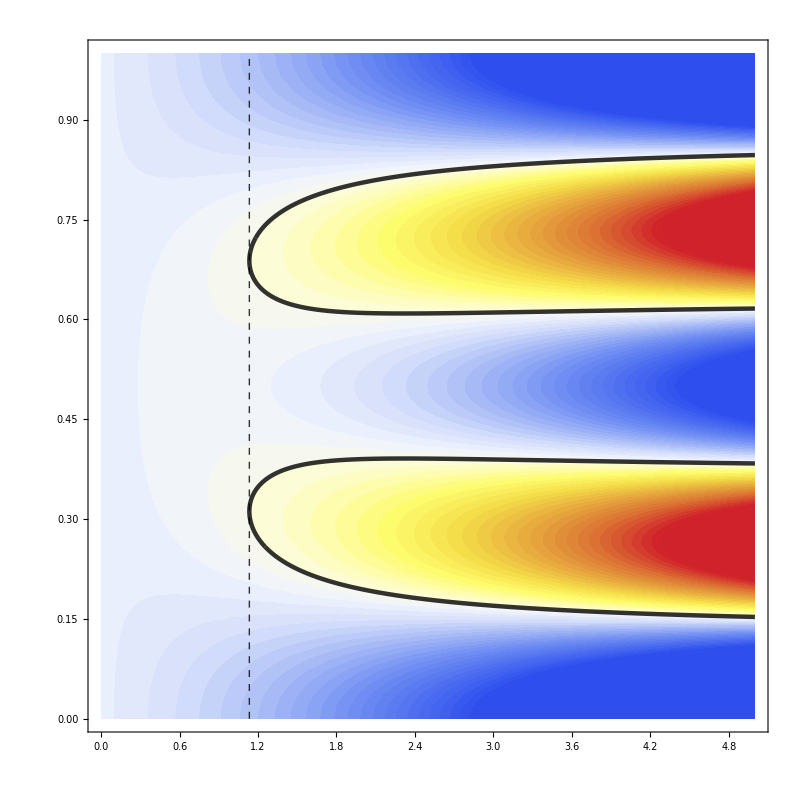

```mathematica
enF=1/24(27 + 30 δ Cos[2θ π] + δ^2 (  35 Cos[2θ π]^2-16 )  );
δdomain={0,5};
scale[x_]:=Sign[x] Power[Abs[x], .7];

(*cf[x_]:=If[ x>0,ColorData["TemperatureMap"][.5-scale[x/150]  ], ColorData[{"SunsetColors","Reverse"}] [-x/30] ];
cf[x_]:=If[ x>0,Blend[{White,Blue},scale[x/150]  ], ColorData[{"SunsetColors","Reverse"}] [-x/30] ];*)

figQQ=Show[
ContourPlot[  enF, {δ,δdomain[[1]],δdomain[[2]]},{θ,0,1} , Contours->100, PlotRange->Full,PlotLegends->BarLegend[ Automatic,None,LegendLabel->MaTeX["F(\\Delta Q, \\theta)" (*"4 \\pi \\epsilon_0 \\, r^5 \\, \\frac{\\mathcal{E}}{Q_{33} }  \\quad \\;  "*),Magnification->2.5],LabelStyle->{Black,FontSize->20,FontFamily->"Helvetica"},LegendMarkerSize-> {30,500}],ColorFunction->(ColorData["TemperatureMap"][ 1/2 -scale[ #/30]  ]&) ,
ColorFunctionScaling->False,ContourStyle->None,FrameLabel->{MaTeX["\\Delta Q"(*" = (Q_{1}-Q_{2})/|Q_{33}|"*),Magnification->3] , MaTeX["\\theta/\\pi",Magnification->3] }, Frame->True ,  ImageSize->800 , (*PlotLabel->MaTeX[ "f(\\delta,\\theta) = (r^5/ k Q^2) \\,  \\mathcal{E}(\\tilde{x},\\tilde{y};Q,\\Delta)",Magnification->2]  ,*)
  FrameStyle ->Directive[Black,24], FrameTicksStyle->Directive[Black,24], PlotLegends-> Placed[ MaTeX[#,Magnification->1.4]&/@{"\\mathcal{G}_0","\\mathcal{G}_4"  } , {Scaled[{.85,.008}], Scaled[{0,0}]}  ],Epilog->{         AbsoluteDashing[5,5],Black,Opacity[.8], Line[{{-√(9/7),0},{-√(9/7),1}} ] ,Line[{{√(9/7),0},{√(9/7),1}} ]  } 
 ],
ContourPlot[enF==0, {δ,δdomain[[1]],δdomain[[2]]},{θ,0,1}  , MaxRecursion->10,ContourStyle->{Thickness[.004],Opacity[.8], Black} ,Epilog->{         AbsoluteDashing[5,5],Black,Opacity[.8], Line[{{-√(9/7),0},{-√(9/7),1}} ] ,Line[{{√(9/7),0},{√(9/7),1}} ]  } ] 
]
```

```mathematica
Export[ "C:\\User\\lucas\\Desktop\\Wolfram Mathematica\\PhD-codes\\Figures_PhD\\New3\\fig8.pdf",figQQ]
```

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\Figures_PhD\New3\fig8.pdf

```mathematica
N[√(16/35) ]
```

0.676123

```mathematica
Simplify[(30 δ)^2 - 4 35 δ^2(27-16 δ^2) ]//TeXForm
```

320 \delta ^2 \left(7 \delta ^2-9\right)

```mathematica
(27-16 δ^2)+30 x δ+35 x^2 δ^2
```

27+30 x δ-16 δ^2+35 x^2 δ^2

```mathematica
Solve[ enF==0,x]
```

{{x→(-15 δ-4 √5 √(-9 δ^2+7 δ^4))/(35 δ^2)},{x→(-15 δ+4 √5 √(-9 δ^2+7 δ^4))/(35 δ^2)}}

```mathematica
N[√(9/7)]
```

1.13389

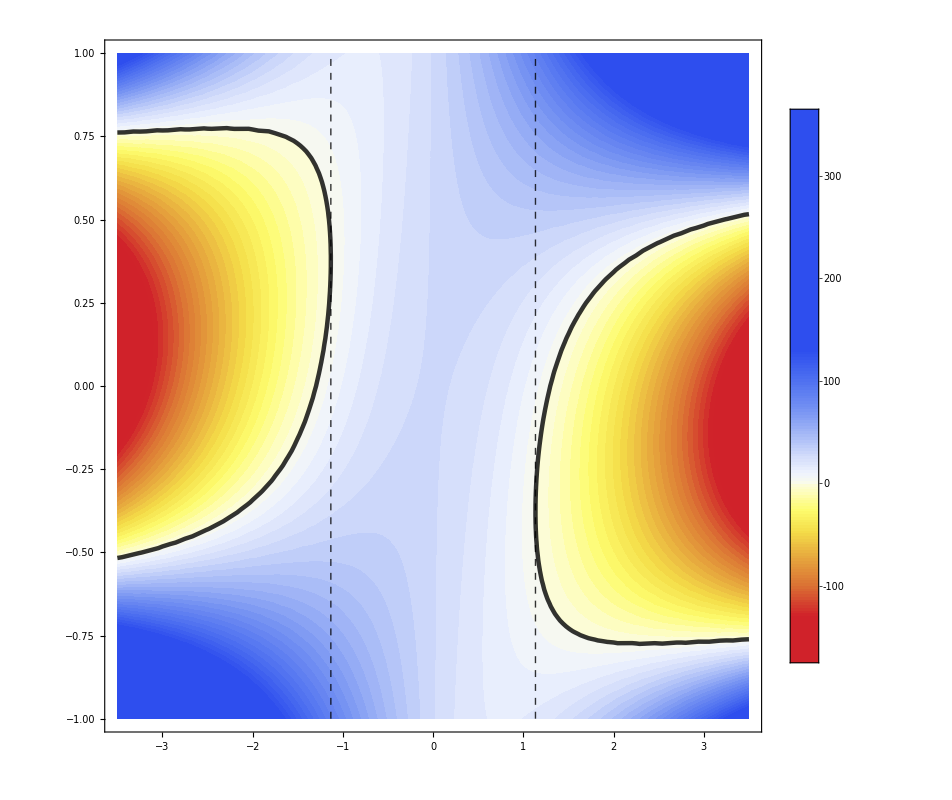

```mathematica
enF=27 + 30 δ x+ δ^2 (  35 x^2-16 );
δdomain={-3.5,3.5};
scale[x_]:=Sign[x] Power[Abs[x], .7];

(*cf[x_]:=If[ x>0,ColorData["TemperatureMap"][.5-scale[x/150]  ], ColorData[{"SunsetColors","Reverse"}] [-x/30] ];
cf[x_]:=If[ x>0,Blend[{White,Blue},scale[x/150]  ], ColorData[{"SunsetColors","Reverse"}] [-x/30] ];*)

figQQ2=Show[
ContourPlot[  enF, {δ,δdomain[[1]],δdomain[[2]]},{x,-1,1} , Contours->100, PlotRange->Full,PlotLegends->BarLegend[ Automatic,None,LegendMarkerSize->{30,500}],ColorFunction->(ColorData["TemperatureMap"][ 1/2 -scale[#/350]  ]&) ,
ColorFunctionScaling->False,ContourStyle->None,FrameLabel->{MaTeX["\\delta \\; [\\Delta/Q\\,]",Magnification->2] , MaTeX["\\cos(2\\theta)",Magnification->2] }, Frame->True ,  ImageSize->800 , (*PlotLabel->MaTeX[ "f(\\delta,\\theta) = (r^5/ k Q^2) \\,  \\mathcal{E}(\\tilde{x},\\tilde{y};Q,\\Delta)",Magnification->2]  ,*)
  FrameStyle ->Directive[Black,14], FrameTicksStyle->Directive[Black,12], PlotLegends-> Placed[ MaTeX[#,Magnification->1.4]&/@{"\\mathcal{G}_0","\\mathcal{G}_4"  } , {Scaled[{.85,.008}], Scaled[{0,0}]}  ]
,Epilog->{         AbsoluteDashing[5,5],Black,Opacity[.8], Line[{{-√(9/7),-1},{-√(9/7),1}} ] ,Line[{{√(9/7),-1},{√(9/7),1}} ]              }
 ],
ContourPlot[enF==0, {δ,δdomain[[1]],δdomain[[2]]},{x,-1,1}  , ContourStyle->{Thickness[.004],Opacity[.8], Black},Epilog->{         AbsoluteDashing[5,5],Black,Opacity[.8], Line[{{-√(9/7),-1},{-√(9/7),1}} ] ,Line[{{√(9/7),-1},{√(9/7),1}} ]  } ]
]
```

```mathematica
Export[ "C:\\User\\lucas\\Desktop\\Wolfram Mathematica\\PhD-codes\\Figures_PhD\\New3\\QQint2.pdf",figQQ2]
```

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\Figures_PhD\New3\QQint2.pdf

```mathematica
figQQ3=Show[  Legended[  GraphicsRow[{figQQ[[1]],figQQ2[[1]]},1,ImageSize->1400], figQQ2[[2]] ]   , PlotLabel->MaTeX[ "f(\\delta,\\theta) = (r^5/ k Q^2) \\,  \\mathcal{E}(\\tilde{x},\\tilde{y};Q,\\Delta)",Magnification->2]   ]
```

-Graphics-

```mathematica
Export[ "C:\\User\\lucas\\Desktop\\Wolfram Mathematica\\PhD-codes\\Figures_PhD\\New3\\QQint3.pdf",figQQ3]
```

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\Figures_PhD\New3\QQint3.pdf

```mathematica
(*Show[
ContourPlot[  enF,{δ,-10,10},{θ,0,1} , Contours->100, PlotRange->Full,PlotLegends->BarLegend[ Automatic,None],ColorFunction->(ColorData["TemperatureMap"][ 1/2 -scale[#/350]  ]&) ,
ColorFunctionScaling->False,ContourStyle->None,FrameLabel->{MaTeX["\\delta \\; [\\Delta/Q\\,]",Magnification->2] , MaTeX["\\theta/\\pi",Magnification->2] }, Frame->True ,  ImageSize->800 , PlotLabel->MaTeX[ "f(\\delta,\\theta) = (r^5/k) \\,  \\mathcal{E}(\\tilde{x},\\tilde{y};Q,\\Delta)",Magnification->2]  ,
  FrameStyle ->Directive[Black,14], FrameTicksStyle->Directive[Black,12], PlotLegends-> Placed[ MaTeX[#,Magnification->1.4]&/@{"\\mathcal{G}_0","\\mathcal{G}_4"  } , {Scaled[{.85,.008}], Scaled[{0,0}]}  ]
,Epilog->{         AbsoluteDashing[5,5],Black,Opacity[.8], Line[{{-1,0},{-1,1}} ] ,Line[{{1,0},{1,1}} ]              }
 ],
ContourPlot[enF==0,{δ,-10,10},{θ,0,1}  , ContourStyle->{Thickness[.004],Opacity[.8], Black} ]
]*)
```

```mathematica
(*DensityPlot[ enF, {δ,-10,10},{θ,0,1} ,  PlotRange->Full,PlotLegends->Automatic,ColorFunction->(ColorData["TemperatureMap"][ 1/2 -scale[#/5000]  ]&),ColorFunctionScaling->False,FrameLabel->{MaTeX["\\delta \\; [\\Delta/Q\\,]",Magnification->2] , MaTeX["\\theta/\\pi",Magnification->2] }, Frame->True ,  ImageSize->600 , PlotLabel->MaTeX[ "f(\\delta,\\theta) = r^5 \\mathcal{E}(\\tilde{x},\\tilde{y})/k",Magnification->2]  ,
  FrameStyle ->Directive[Black,14],MeshFunctions->{#1&,#2&}, MaxRecursion->2,FrameTicksStyle->Directive[Black,12], PlotLegends-> Placed[ MaTeX[#,Magnification->1.4]&/@{"\\mathcal{G}_0","\\mathcal{G}_4"  } , {Scaled[{.85,.008}], Scaled[{0,0}]}  ]
 ]*)
```

## Fig 9 --

```mathematica
NbName="805";  Ls =Range[20,20,2]; tV={0};  hV={{.01,0,0}}; steps=25;acuracy=2.9;    dmax=1; s0=1; ΔeV=2 0.05; ξs=Sort@Join[Table[ ξ, {ξ,0,.9,ΔeV} ][[1;;-2]] , {}] ;
eVs=Table[ 1700Abs[ξ], {ξ,ξs} ];
tV={0,1,1}; ts = Table[ {5x,160,-12x,0,-60},{x,tV}]; hs =Table[  h[[1]]  hAngle[h[[2]],h[[3]]] , {h,hV}];   eV0=0;U=2600;JH=300;  d0={.1,.1,.2};


parametersMat=
N@Table[Flatten[ Table[{
JmatMicro[              0,JH,U,ts[[t]],d0[[t]],s0],hs[[h]],
JmatMicro[eVs[[ev]],JH,U,ts[[t]],d0[[t]],s0],hV[[h]],tV[[t]],eVs[[ev]]
} , {t,1,Length@tV},  {h,1,Length@hV}],1] ,  {ev,1,Length@eVs} ];
		


    
Ls ={16,28,40};  tV={2};  hV={{.05,0,0}}; acuracy=4;   ΔeV= 0.1; 
ξs=Sort@Join[Table[ ξ, {ξ,0,.7,ΔeV} ] , {.75}];
eVs=Table[ 1700Abs[ξ], {ξ,ξs} ]
tV={2,2,2};ts = Table[ {5x,160,-12x,0,-60},{x,tV}];hs =Table[  h[[1]]  hAngle[h[[2]],h[[3]]] , {h,hV}];  
eV0=0;U=2600;JH=300; 
d0={.2,.2,.2};

parametersMat=
N@Table[Flatten[ Table[{
JmatMicro[              0,JH,U,ts[[t]],d0[[t]],s0],hs[[h]],
JmatMicro[eVs[[ev]],JH,U,ts[[t]],d0[[t]],s0],hV[[h]],tV[[t]],eVs[[ev]]
} , {t,1,Length@tV},  {h,1,Length@hV}],1] ,  {ev,1,Length@eVs} ];
```

{0.,170.,340.,510.,680.,850.,1020.,1190.,1275.}

```mathematica
(*Module[{p0,p,l},p0=1;p=1;l=-1;    enV0pure={};enV4pure={};enVΔpure={};
Do[Module[{jG0,LG0,χ0,ω0,ξ0,EnG0,χ,ω,ξ,jG,LG,EnG ,gauge="g4", 
Jv,Kv,Γv,J,K,Γ,L,Nc,h ,u0,H,enH,T,u,t,t0,c11,c21,c12,c22,sNN,sNNN,δn,tp,hp,λ1,λ2,Heff,Jmod,Kmod,Γmod}, 		 
	tp=⌈p/(Length@hV)⌉;hp=Mod[p,Length@hV,1];
	(*{J,K,Γ,h}=parameters⟦ev,p⟧[[1;;4]];*)    L=Ls⟦l⟧; Nc=L^2;
	{jG0,LG0,χ0,ω0,ξ0,EnG0}=Chop@loadDataPure[toPathPure800[parametersMat[[ev,p0]],L,acuracy, "g0",NbName ]  ]; 
	{jG,LG,χ,ω,ξ,EnG}=Chop@loadDataPure[toPathPure800[parametersMat[[ev,p0]],L,acuracy, "g4",NbName ]  ];  

AppendTo[enV0pure,{eVs[[ev]]/(U-3JH),EnG0[[-1]]}  ];
AppendTo[enV4pure,{eVs[[ev]]/(U-3JH),EnG[[-1]]}  ];
AppendTo[enVΔpure,{eVs[[ev]]/(U-3JH), L^2(EnG[[-1]]-EnG0[[-1]])}  ];           
]; ,{ev,1, Length@eVs}]; 

Module[ {En, Disp,h0,θ,φ,L, Nc,J,K,Γ, h ,η, χ0,ω0 ,title, color, j0, L0,tp,hp,size,plotInset,Jmat,JmatMod},
{h0,θ,φ}=ToString/@(NumberForm[#,2]&/@hV[[ 1]]);size=0.012; 
{Jmat,h}=parametersMat[[1,p]][[1;;2]]; {JmatMod,hv}=parametersMat[[1,p]][[3;;4]];
(*title=StringReplace[" a ",{"X1"-> ToString[J],"X2"-> ToString[K],"X3"-> ToString[Γ] ,"X4"-> ToString[Norm@h]  }] ;*)
title=
StringReplace["J\\!=\\!X1, \\; \\Gamma\\!=\\!X3, \\; \\mathbf{h}=Y1",{"X1"->ToString@NumberForm[J,{2,2}],"X2"->ToString@NumberForm[K,{2,2}],"X3"->ToString@NumberForm[Γ,{2,2}], "Y1"->StringJoin@{  "(",h0,",",θ,",",φ,")" }   }      ];

 ListPlot[ enVΔpure, Joined->True ,(*  PlotRange-> {-1.635,-1.6175} ,*)FrameLabel->{MaTeX["\\xi",Magnification->1] , MaTeX["E_{4\\textrm{v}\\!}\\!-\\!E_{0\\textrm{v}}",Magnification->1.2] }, Frame->True ,  ImageSize->600,  FrameStyle ->Directive[Black,14], PlotMarkers->"OpenMarkers",FrameTicksStyle->Directive[Black,12], PlotStyle->  {{ Black,PointSize[2*size]}    } ]
]  ]*)
```

```mathematica
Module[{Np=Length@parametersMat[[1]]},
enVΔpure=Table[{},Np]; 
Do[Module[{JmatMod,Jmat,jG0,LG0,χ0,ω0,ξ0,EnG0,χ,ω,ξ,jG,LG,EnG ,L,Nc,h ,u0,H,enH,T,u,t,t0,sNN,sNNN,δn,tp,hp,p,l=pt}, 		 
p=Length[hV](pt-1)+ph;      L=Ls⟦l⟧;    Nc=L^2; T=Tmat[L,L]; 

{Jmat,h}=parametersMat[[ev,p]][[1;;2]]; {JmatMod,hv}=parametersMat[[ev,p]][[3;;4]];
          Print["JmatMod ",fromJmat[JmatMod],"; L=",L,"; h=(", hV[[ ph,1 ]],",",hV[[ ph,2 ]],",",hV[[ ph,3]],"); "];

{jG0,LG0,χ0,ω0,ξ0,EnG0}=Chop@loadDataPure[toPathPure800[parametersMat[[ev,p]],L,acuracy, "g0",NbName ]  ]; 
	{jG,LG,χ,ω,ξ,EnG}=Chop@loadDataPure[toPathPure800[parametersMat[[ev,p]],L,acuracy, "g4",NbName ]  ];  

AppendTo[enVΔpure[[p]],{eVs[[ev]]/(U-3JH), L^2(EnG[[-1]]-EnG0[[-1]])}  ];  
    
]; ,{ev,1,Length[parametersMat]} , {pt,1,Length@tV},  {ph,1,Length@hV} ]; 
]
```

JmatMod {-0.00950395,-1.,0.143832,0.,0.2}; L=16; h=(0.05,0,0);

JmatMod {-0.00950395,-1.,0.143832,0.,0.2}; L=28; h=(0.05,0,0);

JmatMod {-0.00950395,-1.,0.143832,0.,0.2}; L=40; h=(0.05,0,0);

JmatMod {-0.009734,-1.02316,0.147162,0.,0.204631}; L=16; h=(0.05,0,0);

JmatMod {-0.009734,-1.02316,0.147162,0.,0.204631}; L=28; h=(0.05,0,0);

JmatMod {-0.009734,-1.02316,0.147162,0.,0.204631}; L=40; h=(0.05,0,0);

JmatMod {-0.0104622,-1.09642,0.1577,0.,0.219285}; L=16; h=(0.05,0,0);

JmatMod {-0.0104622,-1.09642,0.1577,0.,0.219285}; L=28; h=(0.05,0,0);

JmatMod {-0.0104622,-1.09642,0.1577,0.,0.219285}; L=40; h=(0.05,0,0);

JmatMod {-0.0118166,-1.23261,0.177288,0.,0.246521}; L=16; h=(0.05,0,0);

JmatMod {-0.0118166,-1.23261,0.177288,0.,0.246521}; L=28; h=(0.05,0,0);

JmatMod {-0.0118166,-1.23261,0.177288,0.,0.246521}; L=40; h=(0.05,0,0);

JmatMod {-0.0140682,-1.45877,0.209818,0.,0.291755}; L=16; h=(0.05,0,0);

JmatMod {-0.0140682,-1.45877,0.209818,0.,0.291755}; L=28; h=(0.05,0,0);

JmatMod {-0.0140682,-1.45877,0.209818,0.,0.291755}; L=40; h=(0.05,0,0);

JmatMod {-0.0177648,-1.82959,0.263153,0.,0.365919}; L=16; h=(0.05,0,0);

JmatMod {-0.0177648,-1.82959,0.263153,0.,0.365919}; L=28; h=(0.05,0,0);

JmatMod {-0.0177648,-1.82959,0.263153,0.,0.365919}; L=40; h=(0.05,0,0);

JmatMod {-0.0240846,-2.46258,0.354198,0.,0.492517}; L=16; h=(0.05,0,0);

JmatMod {-0.0240846,-2.46258,0.354198,0.,0.492517}; L=28; h=(0.05,0,0);

JmatMod {-0.0240846,-2.46258,0.354198,0.,0.492517}; L=40; h=(0.05,0,0);

JmatMod {-0.0359323,-3.64728,0.524595,0.,0.729457}; L=16; h=(0.05,0,0);

JmatMod {-0.0359323,-3.64728,0.524595,0.,0.729457}; L=28; h=(0.05,0,0);

JmatMod {-0.0359323,-3.64728,0.524595,0.,0.729457}; L=40; h=(0.05,0,0);

JmatMod {-0.0461886,-4.67162,0.671927,0.,0.934324}; L=16; h=(0.05,0,0);

JmatMod {-0.0461886,-4.67162,0.671927,0.,0.934324}; L=28; h=(0.05,0,0);

JmatMod {-0.0461886,-4.67162,0.671927,0.,0.934324}; L=40; h=(0.05,0,0);

```mathematica
enVΔpure
```

{{{0.,0.68413},{0.1,0.662401},{0.2,0.599029},{0.3,0.500832},{0.4,0.383003},{0.5,0.270343},{0.6,0.187866},{0.7,0.142324},{0.75,0.129803}},{{0.,0.650667},{0.1,0.628434},{0.2,0.563739},{0.3,0.464033},{0.4,0.34564},{0.5,0.234698},{0.6,0.156671},{0.7,0.116837},{0.75,0.106862}}}

```mathematica
linfit[list_]:=(a x +b )/.FindFit[list, a x+b,{a,b},x];
gapFit[list_]:=(b )/.FindFit[list, a x+b,{a,b},x];

Module[{LsInverse},LsInverse=(1/#)&/@Ls; 
enVΔpureFIT=Table[    {enVΔpure[[1,i,1]],gapFit@ Thread[ {LsInverse,enVΔpure[[;;,i,2]]}]  }  ,{i,1,Length[parametersMat] }]
]
```

{{0.,0.608396},{0.1,0.585605},{0.2,0.519445},{0.3,0.41805},{0.4,0.298961},{0.5,0.189732},{0.6,0.116319},{0.7,0.0824759},{0.75,0.0751866}}

```mathematica
Module[{Np=Length@parametersMat[[1]]},
enV0=Table[{},Np]; enV4=Table[{},Np];enVΔ=Table[{},Np];enVΔ1=Table[{},Np];enVΔ2=Table[{},Np];
Do[Module[{JmatMod,Jmat,jG0,LG0,χ0,ω0,ξ0,EnG0,χ,ω,ξ,jG,LG,EnG ,L,Nc,h ,u0,H,enH,T,u,t,t0,sNN,sNNN,δn,tp,hp,p,l=pt}, 		 
p=Length[hV](pt-1)+ph;      L=Ls⟦l⟧;    Nc=L^2; T=Tmat[L,L]; 

{Jmat,h}=parametersMat[[ev,p]][[1;;2]]; {JmatMod,hv}=parametersMat[[ev,p]][[3;;4]];
          Print["JmatMod ",fromJmat[JmatMod],"; L=",L,"; h=(", hV[[ ph,1 ]],",",hV[[ ph,2 ]],",",hV[[ ph,3]],"); "];
	(*{jG0,LG0,χ0,ω0,ξ0,EnG0}*)
EnG0=loadData[toPath800[N@parametersMat[[ev,p]],L,acuracy, "g0",NbName ]  ][[6]];  
EnG=  loadData[toPath800[parametersMat[[ev,p]],L,acuracy, "g4",NbName ]   ][[6]];  

AppendTo[enV0[[p]],{eVs[[ev]],EnG0[[;;,-1,2]]}  ];
AppendTo[enV4[[p]],{eVs[[ev]],EnG[[;;,-1,2]]}  ];
AppendTo[enVΔ[[p]],{eVs[[ev]]/(U-3JH), 2L^2(EnG[[3,-1,2]]-EnG0[[3,-1,2]])}  ];           
AppendTo[enVΔ1[[p]],{eVs[[ev]]/(U-3JH),2 L^2(EnG[[1,-1,2]]-EnG0[[1,-1,2]])}  ];    
AppendTo[enVΔ2[[p]],{eVs[[ev]]/(U-3JH), 2L^2(EnG[[2,-1,2]]-EnG0[[2,-1,2]])}  ];           
]; ,{ev,1,Length[parametersMat]} , {pt,1,Length@tV},  {ph,1,Length@hV} ]; 
]
```

JmatMod {-0.00950395,-1.,0.143832,0.,0.2}; L=16; h=(0.05,0,0);

JmatMod {-0.00950395,-1.,0.143832,0.,0.2}; L=28; h=(0.05,0,0);

JmatMod {-0.00950395,-1.,0.143832,0.,0.2}; L=40; h=(0.05,0,0);

JmatMod {-0.009734,-1.02316,0.147162,0.,0.204631}; L=16; h=(0.05,0,0);

JmatMod {-0.009734,-1.02316,0.147162,0.,0.204631}; L=28; h=(0.05,0,0);

JmatMod {-0.009734,-1.02316,0.147162,0.,0.204631}; L=40; h=(0.05,0,0);

JmatMod {-0.0104622,-1.09642,0.1577,0.,0.219285}; L=16; h=(0.05,0,0);

JmatMod {-0.0104622,-1.09642,0.1577,0.,0.219285}; L=28; h=(0.05,0,0);

JmatMod {-0.0104622,-1.09642,0.1577,0.,0.219285}; L=40; h=(0.05,0,0);

JmatMod {-0.0118166,-1.23261,0.177288,0.,0.246521}; L=16; h=(0.05,0,0);

JmatMod {-0.0118166,-1.23261,0.177288,0.,0.246521}; L=28; h=(0.05,0,0);

JmatMod {-0.0118166,-1.23261,0.177288,0.,0.246521}; L=40; h=(0.05,0,0);

JmatMod {-0.0140682,-1.45877,0.209818,0.,0.291755}; L=16; h=(0.05,0,0);

JmatMod {-0.0140682,-1.45877,0.209818,0.,0.291755}; L=28; h=(0.05,0,0);

JmatMod {-0.0140682,-1.45877,0.209818,0.,0.291755}; L=40; h=(0.05,0,0);

JmatMod {-0.0177648,-1.82959,0.263153,0.,0.365919}; L=16; h=(0.05,0,0);

JmatMod {-0.0177648,-1.82959,0.263153,0.,0.365919}; L=28; h=(0.05,0,0);

JmatMod {-0.0177648,-1.82959,0.263153,0.,0.365919}; L=40; h=(0.05,0,0);

JmatMod {-0.0240846,-2.46258,0.354198,0.,0.492517}; L=16; h=(0.05,0,0);

JmatMod {-0.0240846,-2.46258,0.354198,0.,0.492517}; L=28; h=(0.05,0,0);

JmatMod {-0.0240846,-2.46258,0.354198,0.,0.492517}; L=40; h=(0.05,0,0);

JmatMod {-0.0359323,-3.64728,0.524595,0.,0.729457}; L=16; h=(0.05,0,0);

JmatMod {-0.0359323,-3.64728,0.524595,0.,0.729457}; L=28; h=(0.05,0,0);

JmatMod {-0.0359323,-3.64728,0.524595,0.,0.729457}; L=40; h=(0.05,0,0);

JmatMod {-0.0461886,-4.67162,0.671927,0.,0.934324}; L=16; h=(0.05,0,0);

JmatMod {-0.0461886,-4.67162,0.671927,0.,0.934324}; L=28; h=(0.05,0,0);

JmatMod {-0.0461886,-4.67162,0.671927,0.,0.934324}; L=40; h=(0.05,0,0);

```mathematica
Module[{LsInverse},LsInverse=(1/#)&/@Ls; 
enVΔFIT=Table[    {enVΔ[[1,i,1]],gapFit@ Thread[ {LsInverse,enVΔ[[;;,i,2]]}]  }  ,{i,1,Length[parametersMat] }]
]
```

{{0.,0.55256},{0.1,0.523426},{0.2,0.440099},{0.3,0.317042},{0.4,0.183771},{0.5,0.0690043},{0.6,0.0687379},{0.7,0.0678298},{0.75,0.0679455}}

```mathematica
Join[ enVΔ,{enVΔFIT}]
```

{{{0.,0.631501},{0.1,0.603662},{0.2,0.523624},{0.3,0.403406},{0.4,0.267954},{0.5,0.112166},{0.6,0.11213},{0.7,0.111363},{0.75,0.112103}},{{0.,0.596626},{0.1,0.568173},{0.2,0.486591},{0.3,0.365053},{0.4,0.23072},{0.5,0.0950109},{0.6,0.0948534},{0.7,0.0940758},{0.75,0.0945374}},{{0.,0.550127},{0.1,0.520854},{0.2,0.437215},{0.3,0.313917},{0.4,0.181074},{0.5,0.0721381},{0.6,0.071818},{0.7,0.0710263},{0.75,0.0711159}}}

```mathematica
Module[{J,K,Γ,Γp,DM,h,ev=1,p=1,L,l=1,title,h0,θ,φ,Jmat},
{Jmat,h}=parametersMat[[ev,p]][[1;;2]]; (*{JmatMod,hv}=parametersMat[[ev,p]][[3;;4]];*)
{J,K,Γ,Γp,DM}=fromJmat[Jmat];L=Ls[[l]]; Print[Γ];
{h0,θ,φ}=ToString/@parametersMat⟦ev,p⟧[[4]];
title=StringReplace["\\mathbf{h}=Y1, \\; \\Gamma=0.07, \\; \\mathrm{D}(1)=0.2, ",{"X1"->ToString@NumberForm[J,{2,2}],"X2"->ToString@NumberForm[K,{2,2}],"X3"->ToString@NumberForm[Γ,{2,2}],"Y2"-> ToString[L], "Y1"->StringJoin@{  "(",h0,",",θ,",",φ,")" }   }      ];
 
Show[
ListPlot[  Join[ enVΔ,{enVΔFIT}]    , Joined->True ,  PlotRange-> {{0,1},{0,.7}},FrameLabel->{MaTeX["\\xi=eV_0/(U-3J_H)",Magnification->1.94] , MaTeX["E_{4\\textrm{v}\\!}\\!-\\!E_{0\\textrm{v}}",Magnification->1.9] }, Frame->True ,  ImageSize->800,
PlotLegends-> Placed[ MaTeX[#,Magnification->2]&/@{
"\\; L=16",
"\\; L=28" ,
"\\; L=40",
"\\; L\\to \\infty"  } , {Scaled[{0.99,.99}], Scaled[{1,1}]}  ]   , PlotLabel->MaTeX[ title,Magnification->1.4]  ,  FrameStyle ->Directive[Black,14], PlotMarkers->"OpenMarkers",FrameTicksStyle->Directive[Black,12], PlotStyle->  {{ Darker@Red,PointSize[0.05]} ,{ Darker@Green,PointSize[0.05]},{ Darker@Blue,PointSize[0.05]},{ Hue[0.5,0.5,0,0.5],PointSize[0.05]}    } ]
,
ListPlot[  Join[ enVΔpure,{enVΔpureFIT} ]    , Joined->True , 
PlotLegends-> Placed[ MaTeX[#,Magnification->2]&/@{"\\phantom{\\; L=16}","\\phantom{\\; L=28}","\\phantom{\\; L=40}","\\phantom{\\; L\\to\\infty}"(*"\\Gamma=0.0, \\; \\mathrm{D}(1)=0.0, \\; L=16","\\Gamma=0.0, \\; \\mathrm{D}(1)=0.0, \\; L=28"  *)}  , {Scaled[{0.95,.99}], Scaled[{1,1}]}  ]  , PlotLabel->MaTeX[ title,Magnification->1.8]  ,  FrameStyle ->Directive[Black,14], PlotMarkers->"OpenMarkers",FrameTicksStyle->Directive[Black,12], PlotStyle->  {{ Red,PointSize[0.05],Opacity[.7],Dashed} ,{ Green,PointSize[0.05],Opacity[.7],Dashed},{ Blue,PointSize[0.05],Opacity[.7],Dashed},{ Hue[0.5,0.5,0,0.5],PointSize[0.05],Dashed}    } ]

]

]
```

0.143832

-Graphics-

```mathematica
Module[{J,K,Γ,Γp,DM,h,ev=1,p=1,L,l=1,title,h0,θ,φ,Jmat},
{Jmat,h}=parametersMat[[ev,p]][[1;;2]]; (*{JmatMod,hv}=parametersMat[[ev,p]][[3;;4]];*)
{J,K,Γ,Γp,DM}=fromJmat[Jmat];L=Ls[[l]];
{h0,θ,φ}=ToString/@parametersMat⟦ev,p⟧[[4]];
title=StringReplace["\\mathbf{h}=Y1, \\; L=Y2",{"X1"->ToString@NumberForm[J,{2,2}],"X2"->ToString@NumberForm[K,{2,2}],"X3"->ToString@NumberForm[Γ,{2,2}],"Y2"-> ToString[L], "Y1"->StringJoin@{  "(",h0,",",θ,",",φ,")" }   }      ];

ListPlot[   {enVΔpure,enVΔ2[[1]],enVΔ2[[2]],enVΔ2[[3]]}   , Joined->True ,  PlotRange-> {{0,1},Full},FrameLabel->{MaTeX["\\xi=eV_0/(U-3J_H)",Magnification->1.4] , MaTeX["E_{4\\textrm{v}\\!}\\!-\\!E_{0\\textrm{v}}",Magnification->1.5] }, Frame->True ,  ImageSize->600,
PlotLegends-> Placed[ MaTeX[#,Magnification->1.4]&/@{"\\Gamma=0, \\; \\mathrm{D}(\\xi)=0","\\Gamma=0.0, \\; \\mathrm{D}(1)=0.5","\\Gamma=0.0, \\; \\mathrm{D}(1)=1"  } , {Scaled[{0.01,.008}], Scaled[{0,0}]}  ]   , PlotLabel->MaTeX[ title,Magnification->1.4]  ,  FrameStyle ->Directive[Black,14], PlotMarkers->"OpenMarkers",FrameTicksStyle->Directive[Black,12], PlotStyle->  {{ Darker@Red,PointSize[0.05]} ,{ Darker@Green,PointSize[0.05]},{ Darker@Blue,PointSize[0.05]},{ Hue[0.5,0.5,0,0.5],PointSize[0.05]}    } ]
]
```

## Fig 9 v3 - Fit --

```mathematica
NbName="805";  Ls =Range[20,20,2]; tV={0};  hV={{.01,0,0}}; steps=25;acuracy=2.9;    dmax=1; s0=1; ΔeV=2 0.05; ξs=Sort@Join[Table[ ξ, {ξ,0,.9,ΔeV} ][[1;;-2]] , {}] ;
eVs=Table[ 1700Abs[ξ], {ξ,ξs} ];
tV={0,1,1}; ts = Table[ {5x,160,-12x,0,-60},{x,tV}]; hs =Table[  h[[1]]  hAngle[h[[2]],h[[3]]] , {h,hV}];   eV0=0;U=2600;JH=300;  d0={.1,.1,.2};


parametersMat=
N@Table[Flatten[ Table[{
JmatMicro[              0,JH,U,ts[[t]],d0[[t]],s0],hs[[h]],
JmatMicro[eVs[[ev]],JH,U,ts[[t]],d0[[t]],s0],hV[[h]],tV[[t]],eVs[[ev]]
} , {t,1,Length@tV},  {h,1,Length@hV}],1] ,  {ev,1,Length@eVs} ];


Ls ={16,28,40};  tV={2};  hV={{.05,0,0}}; acuracy=4;   ΔeV= 0.1; 
ξs=Sort@Join[Table[ ξ, {ξ,0,.7,ΔeV} ] , {.75}];
eVs=Table[ 1700Abs[ξ], {ξ,ξs} ]
tV={2,2,2};ts = Table[ {5x,160,-12x,0,-60},{x,tV}];hs =Table[  h[[1]]  hAngle[h[[2]],h[[3]]] , {h,hV}];  
eV0=0;U=2600;JH=300; 
d0={.2,.2,.2};

parametersMat=
N@Table[Flatten[ Table[{
JmatMicro[              0,JH,U,ts[[t]],d0[[t]],s0],hs[[h]],
JmatMicro[eVs[[ev]],JH,U,ts[[t]],d0[[t]],s0],hV[[h]],tV[[t]],eVs[[ev]]
} , {t,1,Length@tV},  {h,1,Length@hV}],1] ,  {ev,1,Length@eVs} ];
```

{0.,170.,340.,510.,680.,850.,1020.,1190.,1275.}

```mathematica
(*
Module[{p0,p,l},p0=1;p=1;l=-1;    enV0pure={};enV4pure={};enVΔpure={};
Do[Module[{jG0,LG0,χ0,ω0,ξ0,EnG0,χ,ω,ξ,jG,LG,EnG ,gauge="g4", 
Jv,Kv,Γv,J,K,Γ,L,Nc,h ,u0,H,enH,T,u,t,t0,c11,c21,c12,c22,sNN,sNNN,δn,tp,hp,λ1,λ2,Heff,Jmod,Kmod,Γmod}, 		 
	tp=⌈p/(Length@hV)⌉;hp=Mod[p,Length@hV,1];
	(*{J,K,Γ,h}=parameters⟦ev,p⟧[[1;;4]];*)    L=Ls⟦l⟧; Nc=L^2;
	{jG0,LG0,χ0,ω0,ξ0,EnG0}=Chop@loadDataPure[toPathPure800[parametersMat[[ev,p0]],L,acuracy, "g0",NbName ]  ]; 
	{jG,LG,χ,ω,ξ,EnG}=Chop@loadDataPure[toPathPure800[parametersMat[[ev,p0]],L,acuracy, "g4",NbName ]  ];  

AppendTo[enV0pure,{eVs[[ev]]/(U-3JH),EnG0[[-1]]}  ];
AppendTo[enV4pure,{eVs[[ev]]/(U-3JH),EnG[[-1]]}  ];
AppendTo[enVΔpure,{eVs[[ev]]/(U-3JH), L^2(EnG[[-1]]-EnG0[[-1]])}  ];           
]; ,{ev,1, Length@eVs}]; 

Module[ {En, Disp,h0,θ,φ,L, Nc,J,K,Γ, h ,η, χ0,ω0 ,title, color, j0, L0,tp,hp,size,plotInset,Jmat,JmatMod},
{h0,θ,φ}=ToString/@(NumberForm[#,2]&/@hV[[ 1]]);size=0.012; 
{Jmat,h}=parametersMat[[1,p]][[1;;2]]; {JmatMod,hv}=parametersMat[[1,p]][[3;;4]];
(*title=StringReplace[" a ",{"X1"-> ToString[J],"X2"-> ToString[K],"X3"-> ToString[Γ] ,"X4"-> ToString[Norm@h]  }] ;*)
title=
StringReplace["J\\!=\\!X1, \\; \\Gamma\\!=\\!X3, \\; \\mathbf{h}=Y1",{"X1"->ToString@NumberForm[J,{2,2}],"X2"->ToString@NumberForm[K,{2,2}],"X3"->ToString@NumberForm[Γ,{2,2}], "Y1"->StringJoin@{  "(",h0,",",θ,",",φ,")" }   }      ];

 ListPlot[ enVΔpure, Joined->True ,(*  PlotRange-> {-1.635,-1.6175} ,*)FrameLabel->{MaTeX["\\xi",Magnification->1] , MaTeX["E_{4\\textrm{v}\\!}\\!-\\!E_{0\\textrm{v}}",Magnification->1.2] }, Frame->True ,  ImageSize->600,  FrameStyle ->Directive[Black,14], PlotMarkers->"OpenMarkers",FrameTicksStyle->Directive[Black,12], PlotStyle->  {{ Black,PointSize[2*size]}    } ]
]  ]*)
```

```mathematica
Module[{Np=Length@parametersMat[[1]]},
enVΔpure=Table[{},Np]; 
Do[Module[{JmatMod,Jmat,jG0,LG0,χ0,ω0,ξ0,EnG0,χ,ω,ξ,jG,LG,EnG ,L,Nc,h ,u0,H,enH,T,u,t,t0,sNN,sNNN,δn,tp,hp,p,l=pt}, 		 
p=Length[hV](pt-1)+ph;      L=Ls⟦l⟧;    Nc=L^2; T=Tmat[L,L]; 

{Jmat,h}=parametersMat[[ev,p]][[1;;2]]; {JmatMod,hv}=parametersMat[[ev,p]][[3;;4]];
          Print["JmatMod ",fromJmat[JmatMod],"; L=",L,"; h=(", hV[[ ph,1 ]],",",hV[[ ph,2 ]],",",hV[[ ph,3]],"); "];

{jG0,LG0,χ0,ω0,ξ0,EnG0}=Chop@loadDataPure[toPathPure800[parametersMat[[ev,p]],L,acuracy, "g0",NbName ]  ]; 
	{jG,LG,χ,ω,ξ,EnG}=Chop@loadDataPure[toPathPure800[parametersMat[[ev,p]],L,acuracy, "g4",NbName ]  ];  

AppendTo[enVΔpure[[p]],{eVs[[ev]]/(U-3JH), L^2(EnG[[-1]]-EnG0[[-1]])}  ];  
    
]; ,{ev,1,Length[parametersMat]} , {pt,1,Length@tV},  {ph,1,Length@hV} ]; 
]
```

JmatMod {-0.00950395,-1.,0.143832,0.,0.2}; L=16; h=(0.05,0,0);

JmatMod {-0.00950395,-1.,0.143832,0.,0.2}; L=28; h=(0.05,0,0);

JmatMod {-0.00950395,-1.,0.143832,0.,0.2}; L=40; h=(0.05,0,0);

JmatMod {-0.009734,-1.02316,0.147162,0.,0.204631}; L=16; h=(0.05,0,0);

JmatMod {-0.009734,-1.02316,0.147162,0.,0.204631}; L=28; h=(0.05,0,0);

JmatMod {-0.009734,-1.02316,0.147162,0.,0.204631}; L=40; h=(0.05,0,0);

JmatMod {-0.0104622,-1.09642,0.1577,0.,0.219285}; L=16; h=(0.05,0,0);

JmatMod {-0.0104622,-1.09642,0.1577,0.,0.219285}; L=28; h=(0.05,0,0);

JmatMod {-0.0104622,-1.09642,0.1577,0.,0.219285}; L=40; h=(0.05,0,0);

JmatMod {-0.0118166,-1.23261,0.177288,0.,0.246521}; L=16; h=(0.05,0,0);

JmatMod {-0.0118166,-1.23261,0.177288,0.,0.246521}; L=28; h=(0.05,0,0);

JmatMod {-0.0118166,-1.23261,0.177288,0.,0.246521}; L=40; h=(0.05,0,0);

JmatMod {-0.0140682,-1.45877,0.209818,0.,0.291755}; L=16; h=(0.05,0,0);

JmatMod {-0.0140682,-1.45877,0.209818,0.,0.291755}; L=28; h=(0.05,0,0);

JmatMod {-0.0140682,-1.45877,0.209818,0.,0.291755}; L=40; h=(0.05,0,0);

JmatMod {-0.0177648,-1.82959,0.263153,0.,0.365919}; L=16; h=(0.05,0,0);

JmatMod {-0.0177648,-1.82959,0.263153,0.,0.365919}; L=28; h=(0.05,0,0);

JmatMod {-0.0177648,-1.82959,0.263153,0.,0.365919}; L=40; h=(0.05,0,0);

JmatMod {-0.0240846,-2.46258,0.354198,0.,0.492517}; L=16; h=(0.05,0,0);

JmatMod {-0.0240846,-2.46258,0.354198,0.,0.492517}; L=28; h=(0.05,0,0);

JmatMod {-0.0240846,-2.46258,0.354198,0.,0.492517}; L=40; h=(0.05,0,0);

JmatMod {-0.0359323,-3.64728,0.524595,0.,0.729457}; L=16; h=(0.05,0,0);

JmatMod {-0.0359323,-3.64728,0.524595,0.,0.729457}; L=28; h=(0.05,0,0);

JmatMod {-0.0359323,-3.64728,0.524595,0.,0.729457}; L=40; h=(0.05,0,0);

JmatMod {-0.0461886,-4.67162,0.671927,0.,0.934324}; L=16; h=(0.05,0,0);

JmatMod {-0.0461886,-4.67162,0.671927,0.,0.934324}; L=28; h=(0.05,0,0);

JmatMod {-0.0461886,-4.67162,0.671927,0.,0.934324}; L=40; h=(0.05,0,0);

```mathematica
enVΔpure
```

{{{0.,0.68413},{0.1,0.662401},{0.2,0.599029},{0.3,0.500832},{0.4,0.383003},{0.5,0.270343},{0.6,0.187866},{0.7,0.142324},{0.75,0.129803}},{{0.,0.650667},{0.1,0.628434},{0.2,0.563739},{0.3,0.464033},{0.4,0.34564},{0.5,0.234698},{0.6,0.156671},{0.7,0.116837},{0.75,0.106862}}}

```mathematica
linfit[list_]:=(a x +b )/.FindFit[list, a x+b,{a,b},x];
gapFit[list_]:=(b )/.FindFit[list, a x+b,{a,b},x];

Module[{LsInverse},LsInverse=(1/#)&/@Ls; 
enVΔpureFIT=Table[    {enVΔpure[[1,i,1]],gapFit@ Thread[ {LsInverse,enVΔpure[[;;,i,2]]}]  }  ,{i,1,Length[parametersMat] }]
]
```

{{0.,0.608396},{0.1,0.585605},{0.2,0.519445},{0.3,0.41805},{0.4,0.298961},{0.5,0.189732},{0.6,0.116319},{0.7,0.0824759},{0.75,0.0751866}}

```mathematica
Module[{Np=Length@parametersMat[[1]]},
enV0=Table[{},Np]; enV4=Table[{},Np];enVΔ=Table[{},Np];enVΔ1=Table[{},Np];enVΔ2=Table[{},Np];
Do[Module[{JmatMod,Jmat,jG0,LG0,χ0,ω0,ξ0,EnG0,χ,ω,ξ,jG,LG,EnG ,L,Nc,h ,u0,H,enH,T,u,t,t0,sNN,sNNN,δn,tp,hp,p,l=pt}, 		 
p=Length[hV](pt-1)+ph;      L=Ls⟦l⟧;    Nc=L^2; T=Tmat[L,L]; 

{Jmat,h}=parametersMat[[ev,p]][[1;;2]]; {JmatMod,hv}=parametersMat[[ev,p]][[3;;4]];
          Print["JmatMod ",fromJmat[JmatMod],"; L=",L,"; h=(", hV[[ ph,1 ]],",",hV[[ ph,2 ]],",",hV[[ ph,3]],"); "];
	(*{jG0,LG0,χ0,ω0,ξ0,EnG0}*)
EnG0=loadData[toPath800[N@parametersMat[[ev,p]],L,acuracy, "g0",NbName ]  ][[6]];  
EnG=  loadData[toPath800[parametersMat[[ev,p]],L,acuracy, "g4",NbName ]   ][[6]];  

AppendTo[enV0[[p]],{eVs[[ev]],EnG0[[;;,-1,2]]}  ];
AppendTo[enV4[[p]],{eVs[[ev]],EnG[[;;,-1,2]]}  ];
AppendTo[enVΔ[[p]],{eVs[[ev]]/(U-3JH), 2L^2(EnG[[3,-1,2]]-EnG0[[3,-1,2]])}  ];           
AppendTo[enVΔ1[[p]],{eVs[[ev]]/(U-3JH),2 L^2(EnG[[1,-1,2]]-EnG0[[1,-1,2]])}  ];    
AppendTo[enVΔ2[[p]],{eVs[[ev]]/(U-3JH), 2L^2(EnG[[2,-1,2]]-EnG0[[2,-1,2]])}  ];           
]; ,{ev,1,Length[parametersMat]} , {pt,1,Length@tV},  {ph,1,Length@hV} ]; 
]
```

JmatMod {-0.00950395,-1.,0.143832,0.,0.2}; L=16; h=(0.05,0,0);

JmatMod {-0.00950395,-1.,0.143832,0.,0.2}; L=28; h=(0.05,0,0);

JmatMod {-0.00950395,-1.,0.143832,0.,0.2}; L=40; h=(0.05,0,0);

JmatMod {-0.009734,-1.02316,0.147162,0.,0.204631}; L=16; h=(0.05,0,0);

JmatMod {-0.009734,-1.02316,0.147162,0.,0.204631}; L=28; h=(0.05,0,0);

JmatMod {-0.009734,-1.02316,0.147162,0.,0.204631}; L=40; h=(0.05,0,0);

JmatMod {-0.0104622,-1.09642,0.1577,0.,0.219285}; L=16; h=(0.05,0,0);

JmatMod {-0.0104622,-1.09642,0.1577,0.,0.219285}; L=28; h=(0.05,0,0);

JmatMod {-0.0104622,-1.09642,0.1577,0.,0.219285}; L=40; h=(0.05,0,0);

JmatMod {-0.0118166,-1.23261,0.177288,0.,0.246521}; L=16; h=(0.05,0,0);

JmatMod {-0.0118166,-1.23261,0.177288,0.,0.246521}; L=28; h=(0.05,0,0);

JmatMod {-0.0118166,-1.23261,0.177288,0.,0.246521}; L=40; h=(0.05,0,0);

JmatMod {-0.0140682,-1.45877,0.209818,0.,0.291755}; L=16; h=(0.05,0,0);

JmatMod {-0.0140682,-1.45877,0.209818,0.,0.291755}; L=28; h=(0.05,0,0);

JmatMod {-0.0140682,-1.45877,0.209818,0.,0.291755}; L=40; h=(0.05,0,0);

JmatMod {-0.0177648,-1.82959,0.263153,0.,0.365919}; L=16; h=(0.05,0,0);

JmatMod {-0.0177648,-1.82959,0.263153,0.,0.365919}; L=28; h=(0.05,0,0);

JmatMod {-0.0177648,-1.82959,0.263153,0.,0.365919}; L=40; h=(0.05,0,0);

JmatMod {-0.0240846,-2.46258,0.354198,0.,0.492517}; L=16; h=(0.05,0,0);

JmatMod {-0.0240846,-2.46258,0.354198,0.,0.492517}; L=28; h=(0.05,0,0);

JmatMod {-0.0240846,-2.46258,0.354198,0.,0.492517}; L=40; h=(0.05,0,0);

JmatMod {-0.0359323,-3.64728,0.524595,0.,0.729457}; L=16; h=(0.05,0,0);

JmatMod {-0.0359323,-3.64728,0.524595,0.,0.729457}; L=28; h=(0.05,0,0);

JmatMod {-0.0359323,-3.64728,0.524595,0.,0.729457}; L=40; h=(0.05,0,0);

JmatMod {-0.0461886,-4.67162,0.671927,0.,0.934324}; L=16; h=(0.05,0,0);

JmatMod {-0.0461886,-4.67162,0.671927,0.,0.934324}; L=28; h=(0.05,0,0);

JmatMod {-0.0461886,-4.67162,0.671927,0.,0.934324}; L=40; h=(0.05,0,0);

```mathematica
Module[{LsInverse},LsInverse=(1/#)&/@Ls; 
enVΔFIT=Table[    {enVΔ[[1,i,1]],gapFit@ Thread[ {LsInverse,enVΔ[[;;,i,2]]}]  }  ,{i,1,Length[parametersMat] }]
]
```

{{0.,0.55256},{0.1,0.523426},{0.2,0.440099},{0.3,0.317042},{0.4,0.183771},{0.5,0.0690043},{0.6,0.0687379},{0.7,0.0678298},{0.75,0.0679455}}

```mathematica
Join[ enVΔ,{enVΔFIT}]
```

{{{0.,0.631501},{0.1,0.603662},{0.2,0.523624},{0.3,0.403406},{0.4,0.267954},{0.5,0.112166},{0.6,0.11213},{0.7,0.111363},{0.75,0.112103}},{{0.,0.596626},{0.1,0.568173},{0.2,0.486591},{0.3,0.365053},{0.4,0.23072},{0.5,0.0950109},{0.6,0.0948534},{0.7,0.0940758},{0.75,0.0945374}},{{0.,0.550127},{0.1,0.520854},{0.2,0.437215},{0.3,0.313917},{0.4,0.181074},{0.5,0.0721381},{0.6,0.071818},{0.7,0.0710263},{0.75,0.0711159}}}

```mathematica
Module[{J,K,Γ,Γp,DM,h,ev=1,p=1,L,l=1,title,h0,θ,φ,Jmat},
{Jmat,h}=parametersMat[[ev,p]][[1;;2]]; (*{JmatMod,hv}=parametersMat[[ev,p]][[3;;4]];*)
{J,K,Γ,Γp,DM}=fromJmat[Jmat];L=Ls[[l]]; Print[Γ];
{h0,θ,φ}=ToString/@parametersMat⟦ev,p⟧[[4]];
title=StringReplace["\\mathbf{h}=Y1, \\; \\Gamma=0.07, \\; \\mathrm{D}(1)=0.2, ",{"X1"->ToString@NumberForm[J,{2,2}],"X2"->ToString@NumberForm[K,{2,2}],"X3"->ToString@NumberForm[Γ,{2,2}],"Y2"-> ToString[L], "Y1"->StringJoin@{  "(",h0,",",θ,",",φ,")" }   }      ];
 
Show[
ListPlot[  Join[ enVΔ,{enVΔFIT}]    , Joined->True ,  PlotRange-> {{0,1},{0,.7}},FrameLabel->{MaTeX["\\xi=eV_0/(U-3J_H)",Magnification->1.94] , MaTeX["E_{4\\textrm{v}\\!}\\!-\\!E_{0\\textrm{v}}",Magnification->1.9] }, Frame->True ,  ImageSize->800,
PlotLegends-> Placed[ MaTeX[#,Magnification->2]&/@{
"\\; L=16",
"\\; L=28" ,
"\\; L=40",
"\\; L\\to \\infty"  } , {Scaled[{0.99,.99}], Scaled[{1,1}]}  ]   , PlotLabel->MaTeX[ title,Magnification->1.4]  ,  FrameStyle ->Directive[Black,14], PlotMarkers->"OpenMarkers",FrameTicksStyle->Directive[Black,12], PlotStyle->  {{ Darker@Red,PointSize[0.05]} ,{ Darker@Green,PointSize[0.05]},{ Darker@Blue,PointSize[0.05]},{ Hue[0.5,0.5,0,0.5],PointSize[0.05]}    } ]
,
ListPlot[  Join[ enVΔpure,{enVΔpureFIT} ]    , Joined->True , 
PlotLegends-> Placed[ MaTeX[#,Magnification->2]&/@{"\\phantom{\\; L=16}","\\phantom{\\; L=28}","\\phantom{\\; L=40}","\\phantom{\\; L\\to\\infty}"(*"\\Gamma=0.0, \\; \\mathrm{D}(1)=0.0, \\; L=16","\\Gamma=0.0, \\; \\mathrm{D}(1)=0.0, \\; L=28"  *)}  , {Scaled[{0.95,.99}], Scaled[{1,1}]}  ]  , PlotLabel->MaTeX[ title,Magnification->1.8]  ,  FrameStyle ->Directive[Black,14], PlotMarkers->"OpenMarkers",FrameTicksStyle->Directive[Black,12], PlotStyle->  {{ Red,PointSize[0.05],Opacity[.7],Dashed} ,{ Green,PointSize[0.05],Opacity[.7],Dashed},{ Blue,PointSize[0.05],Opacity[.7],Dashed},{ Hue[0.5,0.5,0,0.5],PointSize[0.05],Dashed}    } ]

]

]
```

0.143832

-Graphics-

```mathematica
Module[{J,K,Γ,Γp,DM,h,ev=1,p=1,L,l=1,title,h0,θ,φ,Jmat},
{Jmat,h}=parametersMat[[ev,p]][[1;;2]]; (*{JmatMod,hv}=parametersMat[[ev,p]][[3;;4]];*)
{J,K,Γ,Γp,DM}=fromJmat[Jmat];L=Ls[[l]];
{h0,θ,φ}=ToString/@parametersMat⟦ev,p⟧[[4]];
title=StringReplace["\\mathbf{h}=Y1, \\; L=Y2",{"X1"->ToString@NumberForm[J,{2,2}],"X2"->ToString@NumberForm[K,{2,2}],"X3"->ToString@NumberForm[Γ,{2,2}],"Y2"-> ToString[L], "Y1"->StringJoin@{  "(",h0,",",θ,",",φ,")" }   }      ];

ListPlot[   {enVΔpure,enVΔ2[[1]],enVΔ2[[2]],enVΔ2[[3]]}   , Joined->True ,  PlotRange-> {{0,1},Full},FrameLabel->{MaTeX["\\xi=eV_0/(U-3J_H)",Magnification->1.4] , MaTeX["E_{4\\textrm{v}\\!}\\!-\\!E_{0\\textrm{v}}",Magnification->1.5] }, Frame->True ,  ImageSize->600,
PlotLegends-> Placed[ MaTeX[#,Magnification->1.4]&/@{"\\Gamma=0, \\; \\mathrm{D}(\\xi)=0","\\Gamma=0.0, \\; \\mathrm{D}(1)=0.5","\\Gamma=0.0, \\; \\mathrm{D}(1)=1"  } , {Scaled[{0.01,.008}], Scaled[{0,0}]}  ]   , PlotLabel->MaTeX[ title,Magnification->1.4]  ,  FrameStyle ->Directive[Black,14], PlotMarkers->"OpenMarkers",FrameTicksStyle->Directive[Black,12], PlotStyle->  {{ Darker@Red,PointSize[0.05]} ,{ Darker@Green,PointSize[0.05]},{ Darker@Blue,PointSize[0.05]},{ Hue[0.5,0.5,0,0.5],PointSize[0.05]}    } ]
]
```

## fig 9 correlations

let

#### quadrupole-quadrupole interaction

```mathematica
Q1Q2int=Simplify[  Norm[{x,y,z}]^9 Tr[Transpose[Array[Q2,{3,3}]].ResourceFunction["HessianMatrix"][  Simplify[1/Norm[{x,y,z}]^5{x,y,z}.Array[Q1,{3,3}].{x,y,z},Assumptions->{x,y,z}∈Reals] ,{x,y,z}] ] 
,Assumptions->{x,y,z}∈Reals ]
```

(12 x^4 Q1[1,1]+20 x^3 (y (Q1[1,2]+Q1[2,1])+z (Q1[1,3]+Q1[3,1]))-15 x (y^2+z^2) (y (Q1[1,2]+Q1[2,1])+z (Q1[1,3]+Q1[3,1]))+(y^2+z^2) (y^2 (2 Q1[1,1]-5 Q1[2,2])-5 y z (Q1[2,3]+Q1[3,2])+z^2 (2 Q1[1,1]-5 Q1[3,3]))+x^2 (y^2 (-21 Q1[1,1]+30 Q1[2,2])+30 y z (Q1[2,3]+Q1[3,2])+3 z^2 (-7 Q1[1,1]+10 Q1[3,3]))) Q2[1,1]+((x^2+y^2+z^2)^2 (Q1[1,2]+Q1[2,1])-5 y (x^2+y^2+z^2) (2 x Q1[1,1]+y (Q1[1,2]+Q1[2,1])+z (Q1[1,3]+Q1[3,1]))-5 x (x^2+y^2+z^2) (x (Q1[1,2]+Q1[2,1])+2 y Q1[2,2]+z (Q1[2,3]+Q1[3,2]))+35 x y (x^2 Q1[1,1]+x y (Q1[1,2]+Q1[2,1])+y^2 Q1[2,2]+x z (Q1[1,3]+Q1[3,1])+y z (Q1[2,3]+Q1[3,2])+z^2 Q1[3,3])) Q2[1,2]+((x^2+y^2+z^2)^2 (Q1[1,3]+Q1[3,1])-5 z (x^2+y^2+z^2) (2 x Q1[1,1]+y (Q1[1,2]+Q1[2,1])+z (Q1[1,3]+Q1[3,1]))-5 x (x^2+y^2+z^2) (x (Q1[1,3]+Q1[3,1])+y (Q1[2,3]+Q1[3,2])+2 z Q1[3,3])+35 x z (x^2 Q1[1,1]+x y (Q1[1,2]+Q1[2,1])+y^2 Q1[2,2]+x z (Q1[1,3]+Q1[3,1])+y z (Q1[2,3]+Q1[3,2])+z^2 Q1[3,3])) Q2[1,3]+((x^2+y^2+z^2)^2 (Q1[1,2]+Q1[2,1])-5 y (x^2+y^2+z^2) (2 x Q1[1,1]+y (Q1[1,2]+Q1[2,1])+z (Q1[1,3]+Q1[3,1]))-5 x (x^2+y^2+z^2) (x (Q1[1,2]+Q1[2,1])+2 y Q1[2,2]+z (Q1[2,3]+Q1[3,2]))+35 x y (x^2 Q1[1,1]+x y (Q1[1,2]+Q1[2,1])+y^2 Q1[2,2]+x z (Q1[1,3]+Q1[3,1])+y z (Q1[2,3]+Q1[3,2])+z^2 Q1[3,3])) Q2[2,1]+(2 (x^2+y^2+z^2)^2 Q1[2,2]-10 y (x^2+y^2+z^2) (x (Q1[1,2]+Q1[2,1])+2 y Q1[2,2]+z (Q1[2,3]+Q1[3,2]))+35 y^2 (x^2 Q1[1,1]+x y (Q1[1,2]+Q1[2,1])+y^2 Q1[2,2]+x z (Q1[1,3]+Q1[3,1])+y z (Q1[2,3]+Q1[3,2])+z^2 Q1[3,3])-5 (x^2+y^2+z^2) (x^2 Q1[1,1]+x y (Q1[1,2]+Q1[2,1])+y^2 Q1[2,2]+x z (Q1[1,3]+Q1[3,1])+y z (Q1[2,3]+Q1[3,2])+z^2 Q1[3,3])) Q2[2,2]+((x^2+y^2+z^2)^2 (Q1[2,3]+Q1[3,2])-5 z (x^2+y^2+z^2) (x (Q1[1,2]+Q1[2,1])+2 y Q1[2,2]+z (Q1[2,3]+Q1[3,2]))-5 y (x^2+y^2+z^2) (x (Q1[1,3]+Q1[3,1])+y (Q1[2,3]+Q1[3,2])+2 z Q1[3,3])+35 y z (x^2 Q1[1,1]+x y (Q1[1,2]+Q1[2,1])+y^2 Q1[2,2]+x z (Q1[1,3]+Q1[3,1])+y z (Q1[2,3]+Q1[3,2])+z^2 Q1[3,3])) Q2[2,3]+((x^2+y^2+z^2)^2 (Q1[1,3]+Q1[3,1])-5 z (x^2+y^2+z^2) (2 x Q1[1,1]+y (Q1[1,2]+Q1[2,1])+z (Q1[1,3]+Q1[3,1]))-5 x (x^2+y^2+z^2) (x (Q1[1,3]+Q1[3,1])+y (Q1[2,3]+Q1[3,2])+2 z Q1[3,3])+35 x z (x^2 Q1[1,1]+x y (Q1[1,2]+Q1[2,1])+y^2 Q1[2,2]+x z (Q1[1,3]+Q1[3,1])+y z (Q1[2,3]+Q1[3,2])+z^2 Q1[3,3])) Q2[3,1]+((x^2+y^2+z^2)^2 (Q1[2,3]+Q1[3,2])-5 z (x^2+y^2+z^2) (x (Q1[1,2]+Q1[2,1])+2 y Q1[2,2]+z (Q1[2,3]+Q1[3,2]))-5 y (x^2+y^2+z^2) (x (Q1[1,3]+Q1[3,1])+y (Q1[2,3]+Q1[3,2])+2 z Q1[3,3])+35 y z (x^2 Q1[1,1]+x y (Q1[1,2]+Q1[2,1])+y^2 Q1[2,2]+x z (Q1[1,3]+Q1[3,1])+y z (Q1[2,3]+Q1[3,2])+z^2 Q1[3,3])) Q2[3,2]+(2 (x^2+y^2+z^2)^2 Q1[3,3]-10 z (x^2+y^2+z^2) (x (Q1[1,3]+Q1[3,1])+y (Q1[2,3]+Q1[3,2])+2 z Q1[3,3])+35 z^2 (x^2 Q1[1,1]+x y (Q1[1,2]+Q1[2,1])+y^2 Q1[2,2]+x z (Q1[1,3]+Q1[3,1])+y z (Q1[2,3]+Q1[3,2])+z^2 Q1[3,3])-5 (x^2+y^2+z^2) (x^2 Q1[1,1]+x y (Q1[1,2]+Q1[2,1])+y^2 Q1[2,2]+x z (Q1[1,3]+Q1[3,1])+y z (Q1[2,3]+Q1[3,2])+z^2 Q1[3,3])) Q2[3,3]

```mathematica
Series[ Q1Q2int/.{x->ϵ,y->ϵ,z->ϵ} , {ϵ,0,5}]
```

(-2 (11 Q1[1,1]+5 Q1[1,2]+5 Q1[1,3]+5 Q1[2,1]-10 Q1[2,2]-10 Q1[2,3]+5 Q1[3,1]-10 Q1[3,2]-10 Q1[3,3]) Q2[1,1]+(5 Q1[1,1]+14 Q1[1,2]+20 Q1[1,3]+14 Q1[2,1]+5 Q1[2,2]+20 Q1[2,3]+20 Q1[3,1]+20 Q1[3,2]+35 Q1[3,3]) Q2[1,2]+(5 Q1[1,1]+20 Q1[1,2]+14 Q1[1,3]+20 Q1[2,1]+35 Q1[2,2]+20 Q1[2,3]+14 Q1[3,1]+20 Q1[3,2]+5 Q1[3,3]) Q2[1,3]+(5 Q1[1,1]+14 Q1[1,2]+20 Q1[1,3]+14 Q1[2,1]+5 Q1[2,2]+20 Q1[2,3]+20 Q1[3,1]+20 Q1[3,2]+35 Q1[3,3]) Q2[2,1]-2 (-10 Q1[1,1]+5 Q1[1,2]-10 Q1[1,3]+5 Q1[2,1]+11 Q1[2,2]+5 Q1[2,3]-10 Q1[3,1]+5 Q1[3,2]-10 Q1[3,3]) Q2[2,2]+(35 Q1[1,1]+20 Q1[1,2]+20 Q1[1,3]+20 Q1[2,1]+5 Q1[2,2]+14 Q1[2,3]+20 Q1[3,1]+14 Q1[3,2]+5 Q1[3,3]) Q2[2,3]+(5 Q1[1,1]+20 Q1[1,2]+14 Q1[1,3]+20 Q1[2,1]+35 Q1[2,2]+20 Q1[2,3]+14 Q1[3,1]+20 Q1[3,2]+5 Q1[3,3]) Q2[3,1]+(35 Q1[1,1]+20 Q1[1,2]+20 Q1[1,3]+20 Q1[2,1]+5 Q1[2,2]+14 Q1[2,3]+20 Q1[3,1]+14 Q1[3,2]+5 Q1[3,3]) Q2[3,2]-2 (-10 Q1[1,1]-10 Q1[1,2]+5 Q1[1,3]-10 Q1[2,1]-10 Q1[2,2]+5 Q1[2,3]+5 Q1[3,1]+5 Q1[3,2]+11 Q1[3,3]) Q2[3,3]) ϵ^4+O[ϵ]^6

```mathematica
Tr[  Transpose[Array[Q2,{3,3}]].Array[Q1,{3,3}]   ]
```

Q1[1,1] Q2[1,1]+Q1[1,2] Q2[1,2]+Q1[1,3] Q2[1,3]+Q1[2,1] Q2[2,1]+Q1[2,2] Q2[2,2]+Q1[2,3] Q2[2,3]+Q1[3,1] Q2[3,1]+Q1[3,2] Q2[3,2]+Q1[3,3] Q2[3,3]

```mathematica
{q1,q2}=Eigenvalues[ {{Q[1,1],Q[1,2]},{Q[1,2],Q[2,2]} } ]
```

{1/2 (Q[1,1]+Q[2,2]-√(Q[1,1]^2+4 Q[1,2]^2-2 Q[1,1] Q[2,2]+Q[2,2]^2)),1/2 (Q[1,1]+Q[2,2]+√(Q[1,1]^2+4 Q[1,2]^2-2 Q[1,1] Q[2,2]+Q[2,2]^2))}

```mathematica
FullSimplify[q1-q2]
```

-√(4 Q[1,2]^2+(Q[1,1]-Q[2,2])^2)

```mathematica
Array[Q,{3,3}]
```

{{Q[1,1],Q[1,2],Q[1,3]},{Q[2,1],Q[2,2],Q[2,3]},{Q[3,1],Q[3,2],Q[3,3]}}

```mathematica
V=Simplify[  {x,y,z}.{{Q[1,1],Q[1,2],0},{Q[1,2],Q[2,2],0},{0,0,-Q[1,1]-Q[2,2]}}.{x,y,z} ]
```

x^2 Q[1,1]+2 x y Q[1,2]+y^2 Q[2,2]-z^2 (Q[1,1]+Q[2,2])

```mathematica
r=Simplify[Norm[{x,y,z}],Assumptions->{x,y,z}∈Reals]
```

√(x^2+y^2+z^2)

```mathematica
ℰtensor= ResourceFunction["HessianMatrix"][  1/r^5 V,{x,y,z}]
```

{{(2 Q[1,1])/((x^2+y^2+z^2)^(5/2))-(10 x (2 x Q[1,1]+2 y Q[1,2]))/((x^2+y^2+z^2)^(7/2))+(35 x^2 (x^2 Q[1,1]+2 x y Q[1,2]+y^2 Q[2,2]-z^2 (Q[1,1]+Q[2,2])))/((x^2+y^2+z^2)^(9/2))-(5 (x^2 Q[1,1]+2 x y Q[1,2]+y^2 Q[2,2]-z^2 (Q[1,1]+Q[2,2])))/((x^2+y^2+z^2)^(7/2)),(2 Q[1,2])/((x^2+y^2+z^2)^(5/2))-(5 y (2 x Q[1,1]+2 y Q[1,2]))/((x^2+y^2+z^2)^(7/2))-(5 x (2 x Q[1,2]+2 y Q[2,2]))/((x^2+y^2+z^2)^(7/2))+(35 x y (x^2 Q[1,1]+2 x y Q[1,2]+y^2 Q[2,2]-z^2 (Q[1,1]+Q[2,2])))/((x^2+y^2+z^2)^(9/2)),-(5 z (2 x Q[1,1]+2 y Q[1,2]))/((x^2+y^2+z^2)^(7/2))+(10 x z (Q[1,1]+Q[2,2]))/((x^2+y^2+z^2)^(7/2))+(35 x z (x^2 Q[1,1]+2 x y Q[1,2]+y^2 Q[2,2]-z^2 (Q[1,1]+Q[2,2])))/((x^2+y^2+z^2)^(9/2))},{(2 Q[1,2])/((x^2+y^2+z^2)^(5/2))-(5 y (2 x Q[1,1]+2 y Q[1,2]))/((x^2+y^2+z^2)^(7/2))-(5 x (2 x Q[1,2]+2 y Q[2,2]))/((x^2+y^2+z^2)^(7/2))+(35 x y (x^2 Q[1,1]+2 x y Q[1,2]+y^2 Q[2,2]-z^2 (Q[1,1]+Q[2,2])))/((x^2+y^2+z^2)^(9/2)),(2 Q[2,2])/((x^2+y^2+z^2)^(5/2))-(10 y (2 x Q[1,2]+2 y Q[2,2]))/((x^2+y^2+z^2)^(7/2))+(35 y^2 (x^2 Q[1,1]+2 x y Q[1,2]+y^2 Q[2,2]-z^2 (Q[1,1]+Q[2,2])))/((x^2+y^2+z^2)^(9/2))-(5 (x^2 Q[1,1]+2 x y Q[1,2]+y^2 Q[2,2]-z^2 (Q[1,1]+Q[2,2])))/((x^2+y^2+z^2)^(7/2)),(10 y z (Q[1,1]+Q[2,2]))/((x^2+y^2+z^2)^(7/2))-(5 z (2 x Q[1,2]+2 y Q[2,2]))/((x^2+y^2+z^2)^(7/2))+(35 y z (x^2 Q[1,1]+2 x y Q[1,2]+y^2 Q[2,2]-z^2 (Q[1,1]+Q[2,2])))/((x^2+y^2+z^2)^(9/2))},{-(5 z (2 x Q[1,1]+2 y Q[1,2]))/((x^2+y^2+z^2)^(7/2))+(10 x z (Q[1,1]+Q[2,2]))/((x^2+y^2+z^2)^(7/2))+(35 x z (x^2 Q[1,1]+2 x y Q[1,2]+y^2 Q[2,2]-z^2 (Q[1,1]+Q[2,2])))/((x^2+y^2+z^2)^(9/2)),(10 y z (Q[1,1]+Q[2,2]))/((x^2+y^2+z^2)^(7/2))-(5 z (2 x Q[1,2]+2 y Q[2,2]))/((x^2+y^2+z^2)^(7/2))+(35 y z (x^2 Q[1,1]+2 x y Q[1,2]+y^2 Q[2,2]-z^2 (Q[1,1]+Q[2,2])))/((x^2+y^2+z^2)^(9/2)),(20 z^2 (Q[1,1]+Q[2,2]))/((x^2+y^2+z^2)^(7/2))-(2 (Q[1,1]+Q[2,2]))/((x^2+y^2+z^2)^(5/2))+(35 z^2 (x^2 Q[1,1]+2 x y Q[1,2]+y^2 Q[2,2]-z^2 (Q[1,1]+Q[2,2])))/((x^2+y^2+z^2)^(9/2))-(5 (x^2 Q[1,1]+2 x y Q[1,2]+y^2 Q[2,2]-z^2 (Q[1,1]+Q[2,2])))/((x^2+y^2+z^2)^(7/2))}}

```mathematica
ℰ=FullSimplify@Tr[ Transpose[{{Q[1,1],Q[1,2],0},{Q[1,2],Q[2,2],0},{0,0,-Q[1,1]-Q[2,2]}}].ℰtensor]
```

1/((x^2+y^2+z^2)^(9/2))(20 x^3 y Q[1,2] (5 Q[1,1]-2 Q[2,2])-6 y^2 z^2 (2 (Q[1,1]^2+Q[1,2]^2)+17 Q[1,1] Q[2,2]+17 Q[2,2]^2)+y^4 (4 Q[1,1]^2-16 Q[1,2]^2+4 Q[1,1] Q[2,2]+19 Q[2,2]^2)+z^4 (19 Q[1,1]^2+4 Q[1,2]^2+34 Q[1,1] Q[2,2]+19 Q[2,2]^2)-20 x y Q[1,2] (y^2 (2 Q[1,1]-5 Q[2,2])+9 z^2 (Q[1,1]+Q[2,2]))+x^4 (19 Q[1,1]^2+4 Q[1,1] Q[2,2]+4 (-4 Q[1,2]^2+Q[2,2]^2))-6 x^2 (y^2 (2 Q[1,1]^2-13 Q[1,1] Q[2,2]+2 (-9 Q[1,2]^2+Q[2,2]^2))+z^2 (17 Q[1,1]^2+17 Q[1,1] Q[2,2]+2 (Q[1,2]^2+Q[2,2]^2))))

```mathematica
Simplify[4 r^9 ℰ /. {Q[1,2]->0,Q[1,1]-> (Q+Δ)/2,Q[2,2]-> (Q-Δ)/2,z^4->(R^2-x^2-y^2)^2,z^2->R^2-x^2-y^2} ]
```

9 Q^2 (8 R^4-40 R^2 (x^2+y^2)+35 (x^2+y^2)^2)+30 Q (x^2-y^2) (-6 R^2+7 (x^2+y^2)) Δ+(4 R^4+35 (x^2-y^2)^2-20 R^2 (x^2+y^2)) Δ^2

```mathematica
(*Manipulate[Module[{Qmat},

Qmat = {{Q11,Q12,0},{Q12,Q22,0},{0,0,-Q11-Q22} };

DensityPlot[ 35 ({x,y,0}.Qmat.{x,y,0})^2 -  20 Norm[{x,y,0}]^2({x,y,0}.Qmat.Qmat.{x,y,0}) + 4 Norm[{x,y,0}]^4 Tr[Qmat.Qmat]   , {x,-10,10},{y,-10,10}, ColorFunction->"TemperatureMap"(*Blend[{Blue,Gray,Red},1/2+1/2#]&*),ColorFunctionScaling->True,PlotLegends->Automatic]

],{Q11,-1,1},{Q22,-1,1},{Q12,-1,1}]*)
```

```mathematica
ClearAll[R];
```

```mathematica
35 (R0.Qmat.R0)^2 -  20 r^2(R0.Qmat.Qmat.R0) + 4 r^4 Tr[Qmat.Qmat]
```

35 (R0.{{Q_11,Q_12,0},{Q_12,Q_22,0},{0,0,-Q_11-Q_22}}.R0)^2-20 r^2 R0.{{Q_11^2+Q_12^2,Q_11 Q_12+Q_12 Q_22,0},{Q_11 Q_12+Q_12 Q_22,Q_12^2+Q_22^2,0},{0,0,(-Q_11-Q_22)^2}}.R0+4 r^4 (Q_11^2+2 Q_12^2+(-Q_11-Q_22)^2+Q_22^2)

```mathematica
Qmat = {{Subscript[Q, 11],Subscript[Q, 12],0},{Subscript[Q, 12],Subscript[Q, 22],0},{0,0,-Subscript[Q, 11]-Subscript[Q, 22]} };
Qmat = 1/2{{Q+ΔQ,0,0},{0,Q-ΔQ,0},{0,0,-2Q} };
Rvec={Subscript[R, 1],Subscript[R, 2],0};
Rvec={x̃,ỹ,0};
```

```mathematica
enQ =FullSimplify[   Module[{r=Norm[Rvec],R0=Rvec}, 35 (R0.Qmat.R0)^2 -  20 r^2(R0.Qmat.Qmat.R0) + 4 r^4 Tr[Qmat.Qmat] ] , Assumptions->{Subscript[R, 1]∈Reals,Subscript[R, 2]∈Reals,Subscript[R, 3]∈Reals,x̃∈Reals,ỹ∈Reals} ]
```

1/4 ((39 Q^2+30 Q ΔQ+23 ΔQ^2) (x̃)^4+2 (39 Q^2-47 ΔQ^2) (x̃)^2 (ỹ)^2+(39 Q^2-30 Q ΔQ+23 ΔQ^2) (ỹ)^4)

```mathematica
FullSimplify[   Sign[ enQ], Assumptions->{Q∈Reals,ΔQ∈Reals,x̃∈Reals,ỹ∈Reals } ]
```

Sign[(27 Q^2+30 Q ΔQ+23 ΔQ^2) (x̃)^4+2 (27 Q^2-47 ΔQ^2) (x̃)^2 (ỹ)^2+(27 Q^2-30 Q ΔQ+23 ΔQ^2) (ỹ)^4]

```mathematica
ToString@TeXForm[Simplify@enQ]
```

\tilde{x}^4 \left(23 \text{$\Delta $Q}^2+27 Q^2+30 \text{$\Delta $Q} Q\right)+2 \tilde{x}^2 \tilde{y}^2 \left(27 Q^2-47 \text{$\Delta $Q}^2\right)+\tilde{y}^4 \left(23 \text{$\Delta $Q}^2+27 Q^2-30 \text{$\Delta $Q} Q\right)

```mathematica
TeXForm[Simplify@enQ]
```

\tilde{x}^4 \left(23 \text{$\Delta $Q}^2+27 Q^2+30 \text{$\Delta $Q} Q\right)+2 \tilde{x}^2 \tilde{y}^2 \left(27 Q^2-47 \text{$\Delta $Q}^2\right)+\tilde{y}^4 \left(23 \text{$\Delta $Q}^2+27 Q^2-30 \text{$\Delta $Q} Q\right)

#### sign Q-Q int

```mathematica
enF=27 + 30 δ Cos[2θ π] + δ^2 (  35 Cos[2θ π]^2-16 );
δdomain={-3.5,3.5};
scale[x_]:=Sign[x] Power[Abs[x], .7];

(*cf[x_]:=If[ x>0,ColorData["TemperatureMap"][.5-scale[x/150]  ], ColorData[{"SunsetColors","Reverse"}] [-x/30] ];
cf[x_]:=If[ x>0,Blend[{White,Blue},scale[x/150]  ], ColorData[{"SunsetColors","Reverse"}] [-x/30] ];*)

figQQ=Show[
ContourPlot[  enF, {δ,δdomain[[1]],δdomain[[2]]},{θ,0,1/2} , Contours->100, PlotRange->Full,PlotLegends->BarLegend[ Automatic,None,LegendLabel->MaTeX["4 \\pi \\epsilon_0 \\, r^5 \\, \\frac{\\mathcal{E}}{Q_{33} }  \\quad \\;  ",Magnification->2.5],LabelStyle->{Black,FontSize->15,FontFamily->"Helvetica"},LegendMarkerSize-> {30,500}],ColorFunction->(ColorData["TemperatureMap"][ 1/2 -scale[#/350]  ]&) ,
ColorFunctionScaling->False,ContourStyle->None,FrameLabel->{MaTeX["\\Delta Q = (Q_{1}-Q_{2})/|Q_{33}|",Magnification->3] , MaTeX["\\theta/\\pi",Magnification->3] }, Frame->True ,  ImageSize->800 , (*PlotLabel->MaTeX[ "f(\\delta,\\theta) = (r^5/ k Q^2) \\,  \\mathcal{E}(\\tilde{x},\\tilde{y};Q,\\Delta)",Magnification->2]  ,*)
  FrameStyle ->Directive[Black,22], FrameTicksStyle->Directive[Black,20], PlotLegends-> Placed[ MaTeX[#,Magnification->1.4]&/@{"\\mathcal{G}_0","\\mathcal{G}_4"  } , {Scaled[{.85,.008}], Scaled[{0,0}]}  ],Epilog->{         AbsoluteDashing[5,5],Black,Opacity[.8], Line[{{-√(9/7),0},{-√(9/7),1}} ] ,Line[{{√(9/7),0},{√(9/7),1}} ]  } 
 ],
ContourPlot[enF==0, {δ,δdomain[[1]],δdomain[[2]]},{θ,0,1}  , MaxRecursion->10,ContourStyle->{Thickness[.004],Opacity[.8], Black} ,Epilog->{         AbsoluteDashing[5,5],Black,Opacity[.8], Line[{{-√(9/7),0},{-√(9/7),1}} ] ,Line[{{√(9/7),0},{√(9/7),1}} ]  } ] 
]
```

-Graphics-

```mathematica
Export[ "C:\\User\\lucas\\Desktop\\Wolfram Mathematica\\PhD-codes\\Figures_PhD\\New3\\QQint.pdf",figQQ]
```

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\Figures_PhD\New3\QQint.pdf

```mathematica
N[√(16/35) ]
```

0.676123

```mathematica
Simplify[(30 δ)^2 - 4 35 δ^2(27-16 δ^2) ]//TeXForm
```

320 \delta ^2 \left(7 \delta ^2-9\right)

```mathematica
(27-16 δ^2)+30 x δ+35 x^2 δ^2
```

27+30 x δ-16 δ^2+35 x^2 δ^2

```mathematica
Solve[ enF==0,x]
```

{{x→(-15 δ-4 √5 √(-9 δ^2+7 δ^4))/(35 δ^2)},{x→(-15 δ+4 √5 √(-9 δ^2+7 δ^4))/(35 δ^2)}}

```mathematica
N[√(9/7)]
```

1.13389

```mathematica
enF=27 + 30 δ x+ δ^2 (  35 x^2-16 );
δdomain={-3.5,3.5};
scale[x_]:=Sign[x] Power[Abs[x], .7];

(*cf[x_]:=If[ x>0,ColorData["TemperatureMap"][.5-scale[x/150]  ], ColorData[{"SunsetColors","Reverse"}] [-x/30] ];
cf[x_]:=If[ x>0,Blend[{White,Blue},scale[x/150]  ], ColorData[{"SunsetColors","Reverse"}] [-x/30] ];*)

figQQ2=Show[
ContourPlot[  enF, {δ,δdomain[[1]],δdomain[[2]]},{x,-1,1} , Contours->100, PlotRange->Full,PlotLegends->BarLegend[ Automatic,None,LegendMarkerSize->{30,500}],ColorFunction->(ColorData["TemperatureMap"][ 1/2 -scale[#/350]  ]&) ,
ColorFunctionScaling->False,ContourStyle->None,FrameLabel->{MaTeX["\\delta \\; [\\Delta/Q\\,]",Magnification->2] , MaTeX["\\cos(2\\theta)",Magnification->2] }, Frame->True ,  ImageSize->800 , (*PlotLabel->MaTeX[ "f(\\delta,\\theta) = (r^5/ k Q^2) \\,  \\mathcal{E}(\\tilde{x},\\tilde{y};Q,\\Delta)",Magnification->2]  ,*)
  FrameStyle ->Directive[Black,14], FrameTicksStyle->Directive[Black,12], PlotLegends-> Placed[ MaTeX[#,Magnification->1.4]&/@{"\\mathcal{G}_0","\\mathcal{G}_4"  } , {Scaled[{.85,.008}], Scaled[{0,0}]}  ]
,Epilog->{         AbsoluteDashing[5,5],Black,Opacity[.8], Line[{{-√(9/7),-1},{-√(9/7),1}} ] ,Line[{{√(9/7),-1},{√(9/7),1}} ]              }
 ],
ContourPlot[enF==0, {δ,δdomain[[1]],δdomain[[2]]},{x,-1,1}  , ContourStyle->{Thickness[.004],Opacity[.8], Black},Epilog->{         AbsoluteDashing[5,5],Black,Opacity[.8], Line[{{-√(9/7),-1},{-√(9/7),1}} ] ,Line[{{√(9/7),-1},{√(9/7),1}} ]  } ]
]
```

-Graphics-

```mathematica
Export[ "C:\\User\\lucas\\Desktop\\Wolfram Mathematica\\PhD-codes\\Figures_PhD\\New3\\QQint2.pdf",figQQ2]
```

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\Figures_PhD\New3\QQint2.pdf

```mathematica
figQQ3=Show[  Legended[  GraphicsRow[{figQQ[[1]],figQQ2[[1]]},1,ImageSize->1400], figQQ2[[2]] ]   , PlotLabel->MaTeX[ "f(\\delta,\\theta) = (r^5/ k Q^2) \\,  \\mathcal{E}(\\tilde{x},\\tilde{y};Q,\\Delta)",Magnification->2]   ]
```

-Graphics-

```mathematica
Export[ "C:\\User\\lucas\\Desktop\\Wolfram Mathematica\\PhD-codes\\Figures_PhD\\New3\\QQint3.pdf",figQQ3]
```

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\Figures_PhD\New3\QQint3.pdf

```mathematica
(*Show[
ContourPlot[  enF,{δ,-10,10},{θ,0,1} , Contours->100, PlotRange->Full,PlotLegends->BarLegend[ Automatic,None],ColorFunction->(ColorData["TemperatureMap"][ 1/2 -scale[#/350]  ]&) ,
ColorFunctionScaling->False,ContourStyle->None,FrameLabel->{MaTeX["\\delta \\; [\\Delta/Q\\,]",Magnification->2] , MaTeX["\\theta/\\pi",Magnification->2] }, Frame->True ,  ImageSize->800 , PlotLabel->MaTeX[ "f(\\delta,\\theta) = (r^5/k) \\,  \\mathcal{E}(\\tilde{x},\\tilde{y};Q,\\Delta)",Magnification->2]  ,
  FrameStyle ->Directive[Black,14], FrameTicksStyle->Directive[Black,12], PlotLegends-> Placed[ MaTeX[#,Magnification->1.4]&/@{"\\mathcal{G}_0","\\mathcal{G}_4"  } , {Scaled[{.85,.008}], Scaled[{0,0}]}  ]
,Epilog->{         AbsoluteDashing[5,5],Black,Opacity[.8], Line[{{-1,0},{-1,1}} ] ,Line[{{1,0},{1,1}} ]              }
 ],
ContourPlot[enF==0,{δ,-10,10},{θ,0,1}  , ContourStyle->{Thickness[.004],Opacity[.8], Black} ]
]*)
```

```mathematica
(*DensityPlot[ enF, {δ,-10,10},{θ,0,1} ,  PlotRange->Full,PlotLegends->Automatic,ColorFunction->(ColorData["TemperatureMap"][ 1/2 -scale[#/5000]  ]&),ColorFunctionScaling->False,FrameLabel->{MaTeX["\\delta \\; [\\Delta/Q\\,]",Magnification->2] , MaTeX["\\theta/\\pi",Magnification->2] }, Frame->True ,  ImageSize->600 , PlotLabel->MaTeX[ "f(\\delta,\\theta) = r^5 \\mathcal{E}(\\tilde{x},\\tilde{y})/k",Magnification->2]  ,
  FrameStyle ->Directive[Black,14],MeshFunctions->{#1&,#2&}, MaxRecursion->2,FrameTicksStyle->Directive[Black,12], PlotLegends-> Placed[ MaTeX[#,Magnification->1.4]&/@{"\\mathcal{G}_0","\\mathcal{G}_4"  } , {Scaled[{.85,.008}], Scaled[{0,0}]}  ]
 ]*)
```

#### free finite size scaling

```mathematica
NbName="805";   
Ls =Range[12,60,4]; 	    
tV={0};	  
hV={{.001,0,0},{.1,0,0},{.2,0,0}};
steps=100;
acuracy=4;    
dmax=1; s0=1;
ΔeV= 0.05; 
ξs=Sort@Join[Table[ ξ, {ξ,0,.9,ΔeV} ] , {.99}];
ξs={.99};
eVs=Table[ 1700Abs[ξ], {ξ,ξs} ]

 
tV={0};
ts = Table[ {5x,160,-12x,0,-60},{x,tV}];
hs =Table[  h[[1]]  hAngle[h[[2]],h[[3]]] , {h,hV}];  
eV0=0;U=2600;JH=300; 
d0={0};

parametersMat=
N@Table[Flatten[ Table[{
JmatMicro[              0,JH,U,ts[[t]],d0[[t]],s0],hs[[h]],
JmatMicro[eVs[[ev]],JH,U,ts[[t]],d0[[t]],s0],hV[[h]],tV[[t]],eVs[[ev]]
} , {t,1,Length@tV},  {h,1,Length@hV}],1] ,  {ev,1,Length@eVs} ];
```

{1683.}

```mathematica
Module[{p,l,ev=1},p=1;    ΔpureL=Table[{},Length[parametersMat[[1]] ]  ]; Δpure1L=Table[{},Length[parametersMat[[1]] ]  ];

Do[Module[{jG0,LG0,χ0,ω0,ξ0,EnG0,χ,ω,ξ,jG,LG,EnG ,L,Nc},
	(*{J,K,Γ,h}=parameters⟦ev,p⟧[[1;;4]];*)    L=Ls⟦l⟧; Nc=L^2;
	{jG0,LG0,χ0,ω0,ξ0,EnG0}=Chop@loadDataPure[toPathPure800[parametersMat[[ev,p0]],L,acuracy, "g0",NbName ]  ]; 
	{jG,LG,χ,ω,ξ,EnG}=Chop@loadDataPure[toPathPure800[parametersMat[[ev,p0]],L,acuracy, "g4",NbName ]  ];  
AppendTo[ΔpureL[[p0]],{L, L^2(EnG[[-1]]-EnG0[[-1]])}  ];           
AppendTo[Δpure1L[[p0]],{1/L, L^2(EnG[[-1]]-EnG0[[-1]])}  ];           
]; ,{l,1, Length@Ls},{p0,1,Length[parametersMat[[1]] ] }]; 

  ]
```

```mathematica
Module[ {En, Disp,h0,θ,φ,L, Nc,J,K,Γ, h ,η, χ0,ω0 ,title, color, j0, L0,tp,hp,size,plotInset,Jmat,JmatMod,p=1},
{h0,θ,φ}=ToString/@(NumberForm[#,2]&/@hV[[ 1]]);size=0.012; 
{Jmat,h}=parametersMat[[1,p]][[1;;2]]; {JmatMod,hv}=parametersMat[[1,p]][[3;;4]];
(*title=StringReplace[" a ",{"X1"-> ToString[J],"X2"-> ToString[K],"X3"-> ToString[Γ] ,"X4"-> ToString[Norm@h]  }] ;*)
title=
StringReplace["J\\!=\\!X1, \\; \\Gamma\\!=\\!X3, \\; \\mathbf{h}=Y1",{"X1"->ToString@NumberForm[J,{2,2}],"X2"->ToString@NumberForm[K,{2,2}],"X3"->ToString@NumberForm[Γ,{2,2}], "Y1"->StringJoin@{  "(",h0,",",θ,",",φ,")" }   }      ];

figΔpureL= ListPlot[ ΔpureL, Joined->True ,(*  PlotRange-> {-1.635,-1.6175} ,*)FrameLabel->{MaTeX["L \\quad  \\text{system size}",Magnification->1.5] , MaTeX["\\Delta_{4v} \\; \\text{vison gap } \\; eV_0 = 1",Magnification->1.5] }, Frame->True ,  ImageSize->600,  FrameStyle ->Directive[Black,14], PlotMarkers->"OpenMarkers",FrameTicksStyle->Directive[Black,12], PlotLegends-> Placed[ MaTeX[#,Magnification->1]&/@{"h=0\\; \\kappa=0",StringJoin["h=0.1\\; \\kappa=",ToString[NumberForm[toKappa[hs[[2]] ],{3,3}]] ],StringJoin["h=0.2\\; \\kappa=",ToString[NumberForm[toKappa[hs[[3]] ],{3,3}]] ]   } , {Scaled[{.05,.008}], Scaled[{0,0}]}  ], PlotStyle->  {{ Orange,PointSize[2*size]} ,{ Darker@Cyan,PointSize[2*size]} ,{Darker@ Magenta,PointSize[2*size]}    } ];

figΔpure1L=Show[
 ListPlot[ Δpure1L, Joined->True ,  PlotRange->{{0,.07},Full} , FrameLabel->{MaTeX["1/L \\quad  \\text{system size} ",Magnification->1.5] ,(* MaTeX["\\Delta_{4v} \\; \\text{vison gap } \\; eV_0 = 1",Magnification->1.5]*) }, Frame->True ,  ImageSize->600,  FrameStyle ->Directive[Black,14], PlotMarkers->"OpenMarkers",FrameTicksStyle->Directive[Black,12], PlotLegends-> Placed[ MaTeX[#,Magnification->1.2]&/@{"h=0,\\; \\kappa=0",StringJoin["h=0.1,\\; \\kappa=",ToString[NumberForm[toKappa[hs[[2]] ],{3,3}]] ],StringJoin["h=0.2,\\; \\kappa=",ToString[NumberForm[toKappa[hs[[3]] ],{3,3}]] ]   } , {Scaled[{.685,.008}], Scaled[{0,0}]}  ], PlotStyle->  {{ Orange,PointSize[2*size]} ,{ Darker@Cyan,PointSize[2*size]} ,{Darker@ Magenta,PointSize[2*size]}    } ]
,Plot[    func,{y,0,.06}, PlotStyle->  { Orange,Darker@Cyan,Darker@ Magenta    }]  ];
]
```

```mathematica
GraphicsRow[{figΔpureL,figΔpure1L},-10,ImageSize->1600]
```

-Graphics-

```mathematica
Export[ "C:\\User\\lucas\\Desktop\\Wolfram Mathematica\\PhD-codes\\Figures_PhD\\Videos\\correlations_eV\\gap_h_fin_size(pure).pdf", GraphicsRow[{figΔpureL,figΔpure1L},-10,ImageSize->1600] ]
```

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\Figures_PhD\Videos\correlations_eV\gap_h_fin_size(pure).pdf

```mathematica
(*Table[   Module[   {σ=Mod[i,2],m,n},m=Mod[m0+⌊(i-1)/2⌋,L];n=Mod[n0-⌊(i-1)/2⌋-1+σ,L]; 
Style[   {position[σ,m,n][[1]]-xVortexCenter, 1/Abs[ttU] Abs@δn[[m+n L+1,σ+1]]    } , chargeCFgray[δn[[m+n L+1,σ+1]]/max ], Bold      ]     ]     ,{i,1,2L+1}]
fit[list_]:=Table[ Module[{a,b,x},(a x +b)/.Join[FindFit[  list[[i+3;;-1;;3]] , a x +b,{a,b},x ],{x->"L^-1"}]  ]  ,{i,1,3}];
fit[list_]:=Table[ Module[{a,b,x},(a x +b)/.Join[FindFit[  list[[i+3;;-1;;3]] , a x +b,{a,b},x ],{x->y}]  ]  ,{i,1,3}];
fit[list_]:= Module[{a,b,x},(a x +b)/.Join[FindFit[  list [[-12;;-1;;3]], a x +b,{a,b},x ],{x->y}]  ] ;
func = fit/@Δpure1L
Plot[  fit/@Δpure1L, {y,0,.06}]*)
```

#### pure v2

```mathematica
NbName="805";   
Ls =Range[44,44,4]; 	    
tV={0};	  
hV={  {.1,0,0},{.2,0,0},{.3,0,0}  };
steps=100;
acuracy=4;    
dmax=1; s0=1;
ΔeV= 0.05; 
ξs=Sort@Join[Table[ ξ, {ξ,0,.9,ΔeV} ] , {.99}];
eVs=Table[ 1700Abs[ξ], {ξ,ξs} ]

 
tV={0};
ts = Table[ {5x,160,-12x,0,-60},{x,tV}];
hs =Table[  h[[1]]  hAngle[h[[2]],h[[3]]] , {h,hV}];  
eV0=0;U=2600;JH=300; 
d0={0};

parametersMat=
N@Table[Flatten[ Table[{
JmatMicro[              0,JH,U,ts[[t]],d0[[t]],s0],hs[[h]],
JmatMicro[eVs[[ev]],JH,U,ts[[t]],d0[[t]],s0],hV[[h]],tV[[t]],eVs[[ev]]
} , {t,1,Length@tV},  {h,1,Length@hV}],1] ,  {ev,1,Length@eVs} ];
```

{0.,85.,170.,255.,340.,425.,510.,595.,680.,765.,850.,935.,1020.,1105.,1190.,1275.,1360.,1445.,1530.,1683.}

```mathematica
figvec=Table[{},Length[parametersMat[[1]] ] ];gapvec=Table[{},Length[parametersMat[[1]] ] ];  Do[
Module[{p0,l=1,L,Nc, jG0,LG0,χ0,ω0,ξ0,EnG0,jG,LG,χ,ω,ξ,EnG,Jmat,h,JmatMod,hv,t,eV,fig},
p0=p; (*{J,K,Γ,h}=parameters⟦ev,p⟧[[1;;4]];*)     L=Ls⟦l⟧; Nc=L^2;
{Jmat,h,JmatMod,hv,t,eV}=parametersMat[[ev,p0]];
Print["eV=",N[eV/(U-3JH)],"; t=",t, "; h=",hv,"; JmatMod=",fromJmat[JmatMod]];
	{jG0,LG0,χ0,ω0,ξ0,EnG0}=Chop@loadDataPure[toPathPure800[parametersMat[[ev,p0]],L,acuracy, "g0",NbName ]  ]; 
	{jG,LG,χ,ω,ξ,EnG}=Chop@loadDataPure[toPathPure800[parametersMat[[ev,p0]],L,acuracy, "g4",NbName ]  ];  
(* χ=χgauge4v[χ,L]; *)(* Print["En0=",EnG0,"; En=",EnG, "; En0-En=",(EnG0 -EnG)Nc ]; *)
 Module[{d1,d2,mS,nS,mN,nN,r2 },   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;  mS=r2-1;nS=r2-1;mN=L-r2-1;nN=L-r2-1;
en0linear=Sort@Table[  Module[{r,m,n,γ,σ=Mod[i,2]}, γ=Mod[i+1,2,1];  m =Mod[mS+⌊(i-1)/2⌋+1,L] ; n=Mod[nS+d1-⌊(i-1)/2⌋+1+σ,L] ; r = m+n L+1;   { position[σ,m,n][[1]],χ0[[γ,r]][[1,1]] χ0[[γ,r]][[γ+1,γ+1]]}    ]  , {i,0,2L-1}];
enlinear=Sort@Table[  Module[{r,m,n,γ,σ=Mod[i,2]}, γ=Mod[i+1,2,1];  m =Mod[mS+⌊(i-1)/2⌋+1,L] ; n=Mod[nS+d1-⌊(i-1)/2⌋+1+σ,L] ; r = m+n L+1;   { position[σ,m,n][[1]],χ[[γ,r]][[1,1]] χ[[γ,r]][[γ+1,γ+1]]}    ]  , {i,0,2L-1}];
(*enlinear=Table[  Module[{r,m,n,γ}, γ=Mod[i+1,2,1];  m =Mod[mS+i,L] ; n=Mod[nS+d1-i,L] ;        r = m+n L+1;    χ[[γ,r]][[1,1]] χ[[γ,r]][[γ+1,γ+1]]    ]   , {i,-3,L-1}];*)
gap =Sum[  χ[[γ,r]][[1,1]] χ[[γ,r]][[γ+1,γ+1]]-χ0[[γ,r]][[1,1]] χ0[[γ,r]][[γ+1,γ+1]],{r,1,Nc},{γ,1,3}];
 ];(*
Print["En0=",3(Total[en0linear[[1;;L,2]]]/L),"; En=",3(Total[enlinear[[1;;L,2]]]/L), "; En0-En=",3(Total[en0linear[[1;;L,2]] ]-Total[enlinear[[1;;L,2]]]) ];*)
κLξ=ToString/@(NumberForm[#,2]&/@Chop[{toKappa[h],L,eV/(U-3JH)},10^-6]);

fig=ListPlot[   {en0linear,enlinear}   , Joined->True ,  PlotRange->Full(*{Full,{-0.605,-0.395}}*),FrameLabel->{MaTeX["r \\; [\\text{ along } \\;  R_1\\,]",Magnification->1.4] , MaTeX["-K\\, \\mathrm{U}_\\gamma^{\\gamma\\gamma}(r) \\, \\mathrm{U}_\\gamma^{00}(r)",Magnification->1.5] }, Frame->True ,  ImageSize->600 , PlotLabel->MaTeX[ StringReplace["\\kappa=X1, \\; L=X2, \\; \\xi=X3 ",{"X1"->κLξ[[1]],"X2"->κLξ[[2]],"X3"->κLξ[[3]]}],Magnification->1.4]  ,
  FrameStyle ->Directive[Black,14], PlotMarkers->"OpenMarkers",FrameTicksStyle->Directive[Black,12], PlotLegends-> Placed[ MaTeX[#,Magnification->1.4]&/@{"\\mathcal{G}_0","\\mathcal{G}_4"  } , {Scaled[{.85,.008}], Scaled[{0,0}]}  ], PlotStyle->  {{ Orange,PointSize[0.05]} ,{ Blue,PointSize[0.05]},{ Darker@Blue,PointSize[0.05]},{ Hue[0.5,0.5,0,0.5],PointSize[0.05]}    } ,
Epilog->Inset[ MaTeX[StringJoin["\\Delta_{4v}=",ToString[NumberForm[gap,2]]   ],Magnification->1.4], Scaled[{.1,.85}], Scaled[{0.5,0.5}] ]];
AppendTo[figvec[[p]],fig];
AppendTo[gapvec[[p]],{eV/(U-3JH),gap} ];

];,{ev,1,Length[parametersMat]},{p,1,Length[parametersMat[[1]] ]}]
```

```mathematica
figvec//Length
```

20

```mathematica
gapvec
```

{{{0.,0.616749},{0.05,0.616628},{0.1,0.615954},{0.15,0.613782},{0.2,0.608493},{0.25,0.597784},{0.3,0.578783},{0.35,0.548428},{0.4,0.504271},{0.45,0.445754},{0.5,0.375631},{0.55,0.300608},{0.6,0.229977},{0.65,0.172027},{0.7,0.130394},{0.75,0.103477},{0.8,0.0871284},{0.85,0.0775609},{0.9,0.0723168},{0.99,0.0693092}},{{0.,0.616749},{0.05,0.616628},{0.1,0.615954},{0.15,0.613782},{0.2,0.608493},{0.25,0.597784},{0.3,0.578783},{0.35,0.548428},{0.4,0.504271},{0.45,0.445754},{0.5,0.375631},{0.55,0.300608},{0.6,0.229977},{0.65,0.172027},{0.7,0.130394},{0.75,0.103477},{0.8,0.0871284},{0.85,0.0775609},{0.9,0.0723168},{0.99,0.0693092}},{{0.,0.616749},{0.05,0.616628},{0.1,0.615954},{0.15,0.613782},{0.2,0.608493},{0.25,0.597784},{0.3,0.578783},{0.35,0.548428},{0.4,0.504271},{0.45,0.445754},{0.5,0.375631},{0.55,0.300608},{0.6,0.229977},{0.65,0.172027},{0.7,0.130394},{0.75,0.103477},{0.8,0.0871284},{0.85,0.0775609},{0.9,0.0723168},{0.99,0.0693092}}}

```mathematica
listgap1=Thread[ {{.1,.2,.3},gapvec[[;;,-1,2]]  }];
funcfit1=( a x + b)/.FindFit[ Thread[ {{.1,.2,.3},gapvec[[;;,-1,2]]  }]  , a x + b,{a,b},x];
fitfig1=Show[ 
Plot[funcfit1,{x,0,.35},PlotLegends-> Placed[ MaTeX[#,Magnification->1.4]&/@{".003+.65 \\, h"} , {Scaled[{.05,.008}], Scaled[{0,0}]}  ],PlotStyle->{{Black,Opacity[.8],Thin}},FrameLabel->{MaTeX["h",Magnification->1.4] , MaTeX["\\Delta_{4v}(1)",Magnification->1.5] },Frame->True ,  ImageSize->600 , 
  FrameStyle ->Directive[Black,14], FrameTicksStyle->Directive[Black,12] ],
ListPlot[  {#}&/@listgap1 , PlotRange->{{0,.35},Full} ,PlotStyle->  {{ Orange,PointSize[0.05]} ,{ Darker@Cyan,PointSize[0.05]},{Darker@Magenta,PointSize[0.05]}    } , PlotMarkers->"OpenMarkers"]
]
```

-Graphics-

```mathematica
gapevhL = ListPlot[   gapvec   , Joined->True ,  PlotRange->{{-.01,1.04},{0,.8}},FrameLabel->{MaTeX["\\xi \\; [eV/(U-3J_H)]",Magnification->1.4] , MaTeX["\\Delta_{4v} ",Magnification->1.5] }, Frame->True ,  ImageSize->600 , PlotLabel->MaTeX[ StringReplace["J=\\Gamma=0, \\; L=X2 ",{"X1"->κLξ[[1]],"X2"->κLξ[[2]],"X3"->κLξ[[3]]}],Magnification->1.4]  ,
  FrameStyle ->Directive[Black,14], PlotMarkers->"OpenMarkers",FrameTicksStyle->Directive[Black,12], PlotLegends-> Placed[ MaTeX[#,Magnification->1.4]&/@{"h=.1","h=.2","h=.3"  } , {Scaled[{.8,.67}], Scaled[{0,0}]}  ], PlotStyle->  {{ Orange,PointSize[0.05]} ,{ Darker@Cyan,PointSize[0.05]},{Darker@Magenta,PointSize[0.05]}    } ,
Epilog->{Inset[ fitfig1, {.05,.051}, Scaled[{0,0}],Scaled[.5] ],
Inset[Graphics[{Black,Thin,Arrow[{{0,0},{-1,0}}]  }    ] , {.99,.04}, Scaled[{1,0.5}],Scaled[1.5]  ],
 Inset[ Graphics[ {Black,Thin,Circle[{0,0},{1,2}]}   ], {.99,.14}, Scaled[{0.5,0.5}],Scaled[.3]]}      ]
```

-Graphics-

```mathematica
Export[ "C:\\User\\lucas\\Desktop\\Wolfram Mathematica\\PhD-codes\\Figures_PhD\\Videos\\correlations_eV\\gap_ev2_h_L=44.pdf",gapevhL]
```

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\Figures_PhD\Videos\correlations_eV\gap_ev2_h_L=44.pdf

```mathematica
Module[{FigVec},FigVec=Rasterize[#,RasterSize-> 3000]&/@figvec[[1]];Export[ "C:\\User\\lucas\\Desktop\\Wolfram Mathematica\\PhD-codes\\Figures_PhD\\Videos\\correlations_eV\\CORR4_h=.1_L=44.mkv", FigVec, FrameRate->2,VideoEncoding->"PNG" ] ]
```

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\Figures_PhD\Videos\correlations_eV\CORR4_h=.1_L=44.mkv

```mathematica
(*Manipulate[ figvec[[p]][[ev]], {ev,Range[1,Length[parametersMat] ]}, {p,Range[1,Length[parametersMat[[1]]] ]}  ]*)
```

```mathematica
invertRγ[χ0_]:= Module[{χ=χ0,M=Length[χ0],Nc=Length[χ0[[1]] ] },Table[ χ[[γ,r]],{r,1,Nc},{γ,1,M}] 
];
Module[{ev,p0,l=1,L,Nc, jG0,LG0,χ0,ω0,ξ0,EnG0,jG,LG,χ,ω,ξ,EnG,Jmat,h,JmatMod,hv,t,eV},
p0=1;ev=-1;
	(*{J,K,Γ,h}=parameters⟦ev,p⟧[[1;;4]];*)    L=Ls⟦l⟧; Nc=L^2;

{Jmat,h,JmatMod,hv,t,eV}=parametersMat[[ev,p0]];
Print["eV=",N[eV/(U-3JH)],"; t=",t, "; h=",hv,"; JmatMod=",fromJmat[JmatMod]];
	{jG0,LG0,χ0,ω0,ξ0,EnG0}=Chop@loadDataPure[toPathPure800[parametersMat[[ev,p0]],L,acuracy, "g0",NbName ]  ]; 
	{jG,LG,χ,ω,ξ,EnG}=Chop@loadDataPure[toPathPure800[parametersMat[[ev,p0]],L,acuracy, "g4",NbName ]  ];  
Print[EnG0[[-1]],EnG[[-1]]];
configg0=MFKconfig[ invertRγ[χ0],(*ω0,*)L]; 
configg4=MFKconfig[ invertRγ[χ],(*ω,*)L];
Print@{ configg0,configg4} ;
];
```

eV=0.99; t=0.; h={0.1,0.,0.}; JmatMod={0,-186.531,0,0,0}

-3.88409-3.88405

max=0.999963

max=0.999963

#### energy density per bond

like the Mf config,    
use thickness ~  2^( en/en0 ) -1   --> 0 for en=0, 1 for en-en0, exponential on difference

#### pure

```mathematica
figvec={};
Do[
Module[{p0,l=1,L,Nc, jG0,LG0,χ0,ω0,ξ0,EnG0,jG,LG,χ,ω,ξ,EnG,Jmat,h,JmatMod,hv,t,eV,fig},
p0=1; (*{J,K,Γ,h}=parameters⟦ev,p⟧[[1;;4]];*)     L=Ls⟦l⟧; Nc=L^2;
{Jmat,h,JmatMod,hv,t,eV}=parametersMat[[ev,p0]];
Print["eV=",N[eV/(U-3JH)],"; t=",t, "; h=",hv,"; JmatMod=",fromJmat[JmatMod]];
	{jG0,LG0,χ0,ω0,ξ0,EnG0}=Chop@loadDataPure[toPathPure800[parametersMat[[ev,p0]],L,acuracy, "g0",NbName ]  ]; 
	{jG,LG,χ,ω,ξ,EnG}=Chop@loadDataPure[toPathPure800[parametersMat[[ev,p0]],L,acuracy, "g4",NbName ]  ];  
χ=χgauge4v[χ,L];
Print["En0=",EnG0,"; En=",EnG, "; En0-En=",(EnG0 -EnG)Nc ];(*
configg0=MFKconfig[ χ0,(*ω0,*)L]; 
configg4=MFKconfig[χgauge4v[χ,L],(*ω,*)L];
Print@{ configg0,configg4} ;*)
 Module[{d1,d2,mS,nS,mN,nN,r2 },   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;  mS=r2-1;nS=r2-1;mN=L-r2-1;nN=L-r2-1;(*
χb0linear=Table[  Module[{r,m,n,γ}, γ=Mod[i+1,2,1];  m =mS+i ; n=nS+d1-i ;       r = m+n L+1;  χ0[[γ,r]][[γ+1,γ+1]]     ]   , {i,0,d1-1}];
χc0linear=Table[  Module[{r,m,n,γ}, γ=Mod[i+1,2,1];  m =mS+i ; n=nS+d1-i ;       r = m+n L+1;    χ0[[γ,r]][[1,1]]     ]   , {i,0,d1-1}];*)
en0linear=Table[  Module[{r,m,n,γ}, γ=Mod[i+1,2,1];  m =Mod[mS+i,L] ; n=Mod[nS+d1-i,L] ;       r = m+n L+1;   { position[γ,m,n][[1]],χ0[[γ,r]][[1,1]] χ0[[γ,r]][[γ+1,γ+1]]}    ]   , {i,-3,L-1}];
 ];
 Module[{d1,d2,mS,nS,mN,nN,r2 },   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;  mS=r2-1;nS=r2-1;mN=L-r2-1;nN=L-r2-1;(*
χblinear=Table[  Module[{r,m,n,γ}, γ=Mod[i+1,2,1];  m =mS+i ; n=nS+d1-i ;       r = m+n L+1;   χ[[γ,r]][[γ+1,γ+1]]     ]   , {i,0,d1-1}];
χclinear=Table[  Module[{r,m,n,γ}, γ=Mod[i+1,2,1];  m =mS+i ; n=nS+d1-i ;       r = m+n L+1;    χ[[γ,r]][[1,1]]     ]   , {i,0,d1-1}];*)
enlinear=Table[  Module[{r,m,n,γ}, γ=Mod[i+1,2,1];  m =Mod[mS+i,L] ; n=Mod[nS+d1-i,L] ;        r = m+n L+1;    χ[[γ,r]][[1,1]] χ[[γ,r]][[γ+1,γ+1]]    ]   , {i,-3,L-1}];
 ];
Print["En0=",3(Total[en0linear]/L),"; En=",3(Total[enlinear]/L), "; En0-En=",3(Total[en0linear]-Total[enlinear])L ];
κLξ=ToString/@(NumberForm[#,2]&/@Chop[{toKappa[h],L,eV/(U-3JH)},10^-6]);

fig=ListPlot[   {en0linear,enlinear}   , Joined->True ,  PlotRange->{Full,{-1.05,0.05}},FrameLabel->{MaTeX["r \\; [\\text{ along } \\;  R_1\\,]",Magnification->1.4] , MaTeX["-K\\, \\mathrm{U}_\\gamma^{\\gamma\\gamma}(r) \\, \\mathrm{U}_\\gamma^{00}(r)",Magnification->1.5] }, Frame->True ,  ImageSize->600 , PlotLabel->MaTeX[ StringReplace["\\kappa=X1, \\; L=X2, \\; \\xi=X3 ",{"X1"->κLξ[[1]],"X2"->κLξ[[2]],"X3"->κLξ[[3]]}],Magnification->1.4]  ,
  FrameStyle ->Directive[Black,14], PlotMarkers->"OpenMarkers",FrameTicksStyle->Directive[Black,12], PlotLegends-> Placed[ MaTeX[#,Magnification->1.4]&/@{"\\mathcal{G}_0","\\mathcal{G}_4"  } , {Scaled[{.85,.008}], Scaled[{0,0}]}  ], PlotStyle->  {{ Orange,PointSize[0.05]} ,{ Blue,PointSize[0.05]},{ Darker@Blue,PointSize[0.05]},{ Hue[0.5,0.5,0,0.5],PointSize[0.05]}    } ];
AppendTo[figvec,fig];

];,{ev,1,Length[parametersMat]}]
```

eV=0.99; t=0.; h={0.001,0.,0.}; JmatMod={0,-186.531,0,0,0}

En0={-3.86394}; En={-3.8639}; En0-En={-0.0775338}

En0=-1.54027; En=-1.54078; En0-En=0.990906

```mathematica
κLξ
```

{0,44.00,0.99}

```mathematica
figvec
```

```mathematica
Export[ "C:\\User\\lucas\\Desktop\\Wolfram Mathematica\\PhD-codes\\Figures_PhD\\Videos\\correlations_eV\\CORR_h=0_L=44.mkv", figvec ]
```

```mathematica
(*Manipulate[ figvec[[ev]], {ev,Range[1,Length[parametersMat] ]}]*)
```

```mathematica
en0linear
```

{-0.524883,-0.524883,-0.524883,-0.524883,-0.524883,-0.524883,-0.524883,-0.524883,-0.524883,-0.524883}

```mathematica
ListPlot[   {en0linear,enlinear}   , Joined->True ,  PlotRange->Full,FrameLabel->{MaTeX["r \\; [\\text{ along } \\;  R_1\\,]",Magnification->1.4] , MaTeX["-K\\, \\mathrm{U}_\\gamma^{\\gamma\\gamma}(r) \\, \\mathrm{U}_\\gamma^{00}(r)",Magnification->1.5] }, Frame->True ,  ImageSize->600 , PlotLabel->MaTeX[ "\\kappa=0, \\; L=20, \\; \\xi=0 ",Magnification->1.4]  ,
  FrameStyle ->Directive[Black,14], PlotMarkers->"OpenMarkers",FrameTicksStyle->Directive[Black,12], PlotLegends-> Placed[ MaTeX[#,Magnification->1.4]&/@{"\\mathcal{G}_0","\\mathcal{G}_4"  } , {Scaled[{.85,.008}], Scaled[{0,0}]}  ], PlotStyle->  {{ Orange,PointSize[0.05]} ,{ Blue,PointSize[0.05]},{ Darker@Blue,PointSize[0.05]},{ Hue[0.5,0.5,0,0.5],PointSize[0.05]}    } ]
```

-Graphics-

```mathematica
ListPlot[{enlinear,en0linear}]
```

-Graphics-

#### correlation

```mathematica
scale[χx_]:=Abs[χx]^0.15;
scale[χx_]:=Power[ 2,Abs[χx]^(.2) ]-1;
scale2[χx_]:=1/2+1/2 Sign[χx] Abs[χx]^1;
MFKconfig[χ_,L_]:=Module[{bonds,linethick=.02 (Log[7]/Log[L]),lattice,size,Kx,Ky,Kz,max,meanX,meanY,meanZ,mset,nset}, size = 0.015 (Log[7]/Log[L])^2 ; 
mset=Round@Range[0,L/2];nset=Round@Range[L/2-1,L-1];
Kx=Table[χ[[r,1]][[1,1]](χ[[r,1]][[2,2]]- (χ[[r,1]][[3,3]]+χ[[r,1]][[4,4]])/2), {r,1,L^2} ];  
Ky=Table[ χ[[r,2]][[1,1]](χ[[r,2]][[3,3]]- (χ[[r,2]][[2,2]]+χ[[r,2]][[4,4]])/2), {r,1,L^2} ]; 
Kz=Table[χ[[r,3]][[1,1]](χ[[r,3]][[4,4]]- (χ[[r,3]][[2,2]]+χ[[r,3]][[3,3]])/2), {r,1,L^2} ];  
max=Max@Abs@Union[Kx,Ky,Kz];meanX=(Mean@Kx)/max; meanY=(Mean@Ky)/max; meanZ=(Mean@Kz)/max; Print["max=",max];
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , 
{Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,mset},{n,nset}   ], 2    ];
bonds=Flatten[Table[
Module[{χx,χy,χz(*,ux,uy,uz*)},(*ux=Sign[χ[[m+n L+1,1]][[1,1]] ];u=Sign[χ[[m+n L+1,2]][[1,1]] ];uz=Sign[χ[[m+n L+1,3]][[1,1]] ];*)
χx=1/max Abs[χ[[m+n L+1,1]][[1,1]]](χ[[m+n L+1,1]][[2,2]]-(χ[[m+n L+1,1]][[3,3]]+χ[[m+n L+1,1]][[4,4]])/2);
χy=1/max Abs[χ[[m+n L+1,2]][[1,1]]](χ[[m+n L+1,2]][[3,3]]-(χ[[m+n L+1,2]][[2,2]]+χ[[m+n L+1,2]][[4,4]])/2);
χz=1/max Abs[χ[[m+n L+1,3]][[1,1]]](χ[[m+n L+1,3]][[4,4]]-(χ[[m+n L+1,3]][[2,2]]+χ[[m+n L+1,3]][[3,3]])/2); (*Print["x=",χx,"; y=",χy,"; z=",χz,"; "];*)
{    
{Blend[ {Cyan,Gray,Darker@Red},scale2[χx]],Thickness[  scale[χx] linethick],Line[{asites[m,n],bsites[m+1,n]}]},   (*x-bonds*)
{Blend[ {Magenta,Gray,Darker@Green},scale2[χy]],Thickness[scale[χy]linethick],Line[{asites[m,n],bsites[m,n+1]}]}, (*y-bonds*)
{Blend[ {Darker@Yellow,Gray,Darker@Blue},scale2[χz]],Thickness[scale[χz]linethick],Line[{asites[m,n],bsites[m,n]}]}     (*z-bonds*)
}],{m,mset},{n,nset} ], 2    ];
Graphics[{bonds,lattice},ImageSize->600]
];
```

```mathematica
Module[{ev,p0,l=1,L,Nc, jG0,LG0,χ0,ω0,ξ0,EnG0,jG,LG,χ,ω,ξ,EnG,Jmat,h,JmatMod,hv,t,eV},
p0=1;ev=9;
	(*{J,K,Γ,h}=parameters⟦ev,p⟧[[1;;4]];*)    L=Ls⟦l⟧; Nc=L^2;

{Jmat,h,JmatMod,hv,t,eV}=parametersMat[[ev,p0]];
Print["eV=",N[eV/(U-3JH)],"; t=",t, "; h=",hv,"; JmatMod=",fromJmat[JmatMod]];
	{jG0,LG0,χ0,ω0,ξ0,EnG0}=Chop@loadData[toPath800[parametersMat[[ev,p0]],L,acuracy, "g0",NbName ]  ]; 
	{jG,LG,χ,ω,ξ,EnG}=Chop@loadData[toPath800[parametersMat[[ev,p0]],L,acuracy, "g4",NbName ]  ];  
Print[EnG0[[3,-1,2]],EnG[[3,-1,2]]];
configg0=MFKconfig[ χ0,(*ω0,*)L]; 
configg4=MFKconfig[(*χgauge4v[χ,L],*)χ,(*ω,*)L];
Print@{ configg0,configg4} ;
];
```

eV=0.8; t=0.; h={0.01,0.,0.}; JmatMod={0,-6.29158,0,0,0.629158}

-0.96371-0.963609

{-Graphics-,-Graphics-}

## Fig 9 v2 --

```mathematica
NbName="805";  (*λ0=0.5; *)
Ls =Range[20,20,2]  
tV={0};	  
hV={{.01,0,0}};
steps=50;
acuracy=3.1;    
dmax=1; s0=1;
ΔeV=2 0.05; 
ξs=Sort@Join[Table[ ξ, {ξ,0,.9,ΔeV} ][[1;;-2]] , {.85}]
eVs=Table[ 1700Abs[ξ], {ξ,ξs} ]

(*ηs=Join[ Table[3 η-.113,{η,-1,1,.1}]    ]; *)   (*, Table[η,{η,-.5+.02,.5,0.05}], Table[η,{η,-.5+.04,.5,0.05}] *) 
tV={0,2,-2};
ts = Table[ {5x,160,-12x,0,-60},{x,tV}];
hs =Table[  h[[1]]  hAngle[h[[2]],h[[3]]] , {h,hV}];  
eV0=0;U=2600;JH=300; 
d0={.1,.1,.1};

parametersMat=
N@Table[Flatten[ Table[{
JmatMicro[              0,JH,U,ts[[t]],d0[[t]],s0],hs[[h]],
JmatMicro[eVs[[ev]],JH,U,ts[[t]],d0[[t]],s0],hV[[h]],tV[[t]],eVs[[ev]]
} , {t,1,Length@tV},  {h,1,Length@hV}],1] ,  {ev,1,Length@eVs} ];
```

{20}

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.85}

{0.,170.,340.,510.,680.,850.,1020.,1190.,1360.,1445.}

```mathematica
Module[{p0,p,l},p0=1;p=1;l=1;    enV0pure={};enV4pure={};enVΔpure={};
Do[Module[{jG0,LG0,χ0,ω0,ξ0,EnG0,χ,ω,ξ,jG,LG,EnG ,gauge="g2", 
Jv,Kv,Γv,J,K,Γ,L,Nc,h ,u0,H,enH,T,u,t,t0,c11,c21,c12,c22,sNN,sNNN,δn,tp,hp,λ1,λ2,Heff,Jmod,Kmod,Γmod}, 		 
	tp=⌈p/(Length@hV)⌉;hp=Mod[p,Length@hV,1];
	(*{J,K,Γ,h}=parameters⟦ev,p⟧[[1;;4]];*)    L=Ls⟦l⟧; Nc=L^2;
	{jG0,LG0,χ0,ω0,ξ0,EnG0}=Chop@loadDataPure[toPathPure800[parametersMat[[ev,p0]],L,acuracy, "g0",NbName ]  ]; 
	{jG,LG,χ,ω,ξ,EnG}=Chop@loadDataPure[toPathPure800[parametersMat[[ev,p0]],L,acuracy, "g2",NbName ]  ];  

AppendTo[enV0pure,{eVs[[ev]]/(U-3JH),EnG0[[-1]]}  ];
AppendTo[enV4pure,{eVs[[ev]]/(U-3JH),EnG[[-1]]}  ];
AppendTo[enVΔpure,{eVs[[ev]]/(U-3JH), L^2(EnG[[-1]]-EnG0[[-1]])}  ];           
]; ,{ev,1, Length@eVs}]; 

Module[ {En, Disp,h0,θ,φ,L, Nc,J,K,Γ, h ,η, χ0,ω0 ,title, color, j0, L0,tp,hp,size,plotInset,Jmat,JmatMod},
{h0,θ,φ}=ToString/@(NumberForm[#,2]&/@hV[[ 1]]);size=0.012; 
{Jmat,h}=parametersMat[[1,p]][[1;;2]]; {JmatMod,hv}=parametersMat[[1,p]][[3;;4]];
(*title=StringReplace[" a ",{"X1"-> ToString[J],"X2"-> ToString[K],"X3"-> ToString[Γ] ,"X4"-> ToString[Norm@h]  }] ;*)
title=
StringReplace["J\\!=\\!X1, \\; \\Gamma\\!=\\!X3, \\; \\mathbf{h}=Y1",{"X1"->ToString@NumberForm[J,{2,2}],"X2"->ToString@NumberForm[K,{2,2}],"X3"->ToString@NumberForm[Γ,{2,2}], "Y1"->StringJoin@{  "(",h0,",",θ,",",φ,")" }   }      ];

 ListPlot[ enVΔpure, Joined->True ,(*  PlotRange-> {-1.635,-1.6175} ,*)FrameLabel->{MaTeX["\\xi",Magnification->1] , MaTeX["E_{2\\textrm{v}\\!}\\!-\\!E_{0\\textrm{v}}",Magnification->1.2] }, Frame->True ,  ImageSize->600,  FrameStyle ->Directive[Black,14], PlotMarkers->"OpenMarkers",FrameTicksStyle->Directive[Black,12], PlotStyle->  {{ Black,PointSize[2*size]}    } ]
]  ]
```

-Graphics-

```mathematica
Module[{Np=Length@parametersMat[[1]],l=1},
enV0=Table[{},Np]; enV4=Table[{},Np];enVΔ=Table[{},Np];enVΔ1=Table[{},Np];enVΔ2=Table[{},Np];
Do[Module[{JmatMod,Jmat,jG0,LG0,χ0,ω0,ξ0,EnG0,χ,ω,ξ,jG,LG,EnG ,L,Nc,h ,u0,H,enH,T,u,t,t0,sNN,sNNN,δn,tp,hp,p}, 		 
p=Length[hV](pt-1)+ph;      L=Ls⟦l⟧;    Nc=L^2; T=Tmat[L,L]; 

{Jmat,h}=parametersMat[[ev,p]][[1;;2]]; {JmatMod,hv}=parametersMat[[ev,p]][[3;;4]];
          Print["JmatMod ",fromJmat[JmatMod],"; L=",L,"; h=(", hV[[ ph,1 ]],",",hV[[ ph,2 ]],",",hV[[ ph,3]],"); "];
	(*{jG0,LG0,χ0,ω0,ξ0,EnG0}*)
EnG0=loadData[toPath800[parametersMat[[ev,p]],L,acuracy, "g0",NbName ]  ][[6]];  
EnG=  loadData[toPath800[parametersMat[[ev,p]],L,acuracy, "g2",NbName ]   ][[6]];  

AppendTo[enV0[[p]],{eVs[[ev]],EnG0[[;;,-1,2]]}  ];
AppendTo[enV4[[p]],{eVs[[ev]],EnG[[;;,-1,2]]}  ];
AppendTo[enVΔ[[p]],{eVs[[ev]]/(U-3JH), 2L^2(EnG[[3,-1,2]]-EnG0[[3,-1,2]])}  ];           
AppendTo[enVΔ1[[p]],{eVs[[ev]]/(U-3JH),2 L^2(EnG[[1,-1,2]]-EnG0[[1,-1,2]])}  ];    
AppendTo[enVΔ2[[p]],{eVs[[ev]]/(U-3JH), 2L^2(EnG[[2,-1,2]]-EnG0[[2,-1,2]])}  ];           
]; ,{ev,1,Length[parametersMat]} , {pt,1,Length@tV},  {ph,1,Length@hV} ]; 
]
```

```mathematica
Module[{J,K,Γ,Γp,DM,h,ev=1,L,l=1,title,h0,θ,φ,Jmat},
Do[
{Jmat,h}=parametersMat[[ev,p]][[1;;2]]; (*{JmatMod,hv}=parametersMat[[ev,p]][[3;;4]];*)
{J,K,Γ,Γp,DM}=fromJmat[Jmat];L=Ls[[l]]; Print[Γ];
{h0,θ,φ}=ToString/@parametersMat⟦ev,p⟧[[4]];
title=StringReplace["\\mathbf{h}=Y1, \\; L=Y2",{"X1"->ToString@NumberForm[J,{2,2}],"X2"->ToString@NumberForm[K,{2,2}],"X3"->ToString@NumberForm[Γ,{2,2}],"Y2"-> ToString[L], "Y1"->StringJoin@{  "(",h0,",",θ,",",φ,")" }   }      ];
,{p,1,Length[parametersMat[[1]] ]} ];
ListPlot[   {enVΔpure,enVΔ[[1]],enVΔ[[2]],enVΔ[[3]]}   , Joined->True ,  PlotRange-> {{0,1},Full},FrameLabel->{MaTeX["\\xi=eV_0/(U-3J_H)",Magnification->1.4] , MaTeX["E_{2\\textrm{v}\\!}\\!-\\!E_{0\\textrm{v}}",Magnification->1.5] }, Frame->True ,  ImageSize->800,
PlotLegends-> Placed[ MaTeX[#,Magnification->1]&/@{
"\\Gamma=0.0, \\; \\mathrm{D}(\\xi)=0",
"\\Gamma=0.0, \\; \\mathrm{D}(1)=0.1",
"\\Gamma=0.15, \\; \\mathrm{D}(1)=0.1",
"\\Gamma=-0.15, \\; \\mathrm{D}(1)=0.1"  } , {Scaled[{0.01,.008}], Scaled[{0,0}]}  ]   , PlotLabel->MaTeX[ title,Magnification->1.4]  ,  FrameStyle ->Directive[Black,14], PlotMarkers->"OpenMarkers",FrameTicksStyle->Directive[Black,12], PlotStyle->  {{ Darker@Red,PointSize[0.05]} ,{ Darker@Green,PointSize[0.05]},{ Darker@Blue,PointSize[0.05]},{ Hue[0.5,0.5,0,0.5],PointSize[0.05]}    } ]
]
```

0

0.143832

-0.143832

-Graphics-

```mathematica
0.6425839813802625
```

2.47148

```mathematica
0.3257501418557851/0.04859624533004592
```

6.7032

```mathematica
enVΔpure
```

{{0.,0.32575},{0.1,0.314612},{0.2,0.282208},{0.3,0.232288},{0.4,0.173049},{0.5,0.117574},{0.6,0.0785499},{0.7,0.0585634},{0.8,0.0504315},{0.85,0.0485962}}

```mathematica
enVΔ[[2]]
```

{{0.,0.637736},{0.1,0.613512},{0.2,0.543187},{0.3,0.435292},{0.4,0.308102},{0.5,0.189345},{0.6,0.0774721},{0.7,0.0763117},{0.8,0.0758782}}

```mathematica
Module[{J,K,Γ,Γp,DM,h,ev=1,p=1,L,l=1,title,h0,θ,φ,Jmat},
{Jmat,h}=parametersMat[[ev,p]][[1;;2]]; (*{JmatMod,hv}=parametersMat[[ev,p]][[3;;4]];*)
{J,K,Γ,Γp,DM}=fromJmat[Jmat];L=Ls[[l]];
{h0,θ,φ}=ToString/@parametersMat⟦ev,p⟧[[4]];
title=StringReplace["\\mathbf{h}=Y1, \\; L=Y2",{"X1"->ToString@NumberForm[J,{2,2}],"X2"->ToString@NumberForm[K,{2,2}],"X3"->ToString@NumberForm[Γ,{2,2}],"Y2"-> ToString[L], "Y1"->StringJoin@{  "(",h0,",",θ,",",φ,")" }   }      ];

ListPlot[   {enVΔpure,enVΔ2[[1]],enVΔ2[[2]],enVΔ2[[3]]}   , Joined->True ,  PlotRange-> {{0,1},Full},FrameLabel->{MaTeX["\\xi=eV_0/(U-3J_H)",Magnification->1.4] , MaTeX["E_{4\\textrm{v}\\!}\\!-\\!E_{0\\textrm{v}}",Magnification->1.5] }, Frame->True ,  ImageSize->600,
PlotLegends-> Placed[ MaTeX[#,Magnification->1.4]&/@{"\\Gamma=0, \\; \\mathrm{D}(\\xi)=0","\\Gamma=0.0, \\; \\mathrm{D}(1)=0.5","\\Gamma=0.0, \\; \\mathrm{D}(1)=1"  } , {Scaled[{0.01,.008}], Scaled[{0,0}]}  ]   , PlotLabel->MaTeX[ title,Magnification->1.4]  ,  FrameStyle ->Directive[Black,14], PlotMarkers->"OpenMarkers",FrameTicksStyle->Directive[Black,12], PlotStyle->  {{ Darker@Red,PointSize[0.05]} ,{ Darker@Green,PointSize[0.05]},{ Darker@Blue,PointSize[0.05]},{ Hue[0.5,0.5,0,0.5],PointSize[0.05]}    } ]
]
```

-Graphics-

## Fig 9 v4 - tanh fit --

```mathematica
NbName="806"; 
Ls={28};
tV={0}; 
hV={{.2,0,0}};
steps=100;
acuracy=4;    
dmax=1; s0=1;
ΔeV= 0.05; 
ξs=Sort@Join[Table[ ξ, {ξ,0,.9,ΔeV} ] , {.99}] 
eVs=Table[ 1700Abs[ξ], {ξ,ξs} ];

DMr[eV0_,JH_,U_,t_,Dmax_:1,s_:1]:=(Dmax eV0)/(U-3 JH);
ts = Table[ {5x,160,-12x,0,-60},{x,tV}];
hs =Table[  h[[1]]  hAngle[h[[2]],h[[3]]] , {h,hV}];  
U=2600;JH=300; 

parametersMat=N@Table[Flatten[ Table[{
JmatMicro[              0,JH,U,ts[[t]],dmax,s0],hs[[h]],
JmatMicro[eVs[[ev]],JH,U,ts[[t]],dmax,s0],hV[[h]],tV[[t]],eVs[[ev]]
} , {t,1,Length@tV},  {h,1,Length@hV}],1] ,  {ev,1,Length@eVs} ];

tV={2.,2.,2.(*,4.*)};
ts = Table[ {5x,160,-12x,0,-60},{x,tV}];
hs =Table[  h[[1]]  hAngle[h[[2]],h[[3]]] , {h,hV}];  
eV0=0;U=2600;JH=300; 
d0={0,.5,1,.5};

labels9={
"\\Gamma=0.00, \\; \\mathrm{D}_1=0",
"\\Gamma=0.15, \\; \\mathrm{D}_1=0",
"\\Gamma=0.15, \\; \\mathrm{D}_1=0.5" ,
"\\Gamma=0.15, \\; \\mathrm{D}_1=1" ,
"\\Gamma=0.3, \\; \\mathrm{D}_1=.5",
"\\Gamma=0.3, \\; \\mathrm{D}_1=.5",
"\\Gamma=0.3, \\; \\mathrm{D}_1=.5" } ;

parametersMat=
N@Table[Flatten[ Table[{
JmatMicro[              0,JH,U,ts[[t]],d0[[t]],s0],hs[[h]],
JmatMicro[eVs[[ev]],JH,U,ts[[t]],d0[[t]],s0],hV[[h]],tV[[t]],eVs[[ev]]
} , {t,1,Length@tV},  {h,1,Length@hV}],1] ,  {ev,1,Length@eVs} ];


evList=Range[1,Min[11,Length[parametersMat]] ];
```

{0.,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.99}

```mathematica
Module[{p0,p,l},p0=1;p=1;l=1;    enV0pure={};enV4pure={};enVΔpure={};
Do[Module[{jG0,LG0,χ0,ω0,ξ0,EnG0,χ,ω,ξ,jG,LG,EnG ,gauge="g4", 
Jv,Kv,Γv,J,K,Γ,L,Nc,h ,u0,H,enH,T,u,t,t0,c11,c21,c12,c22,sNN,sNNN,δn,tp,hp,λ1,λ2,Heff,Jmod,Kmod,Γmod}, 		 
	tp=⌈p/(Length@hV)⌉;hp=Mod[p,Length@hV,1];
	(*{J,K,Γ,h}=parameters⟦ev,p⟧[[1;;4]];*)    L=Ls⟦l⟧; Nc=L^2;
	{jG0,LG0,χ0,ω0,ξ0,EnG0}=Chop@loadDataPure[toPathPure800[parametersMat[[ev,p0]],L,acuracy, "g0",NbName ]  ]; 
	{jG,LG,χ,ω,ξ,EnG}=Chop@loadDataPure[toPathPure800[parametersMat[[ev,p0]],L,acuracy, "g4",NbName ]  ];  

AppendTo[enV0pure,{eVs[[ev]]/(U-3JH),EnG0[[-1]]}  ];
AppendTo[enV4pure,{eVs[[ev]]/(U-3JH),EnG[[-1]]}  ];
AppendTo[enVΔpure,{eVs[[ev]]/(U-3JH), L^2(EnG[[-1]]-EnG0[[-1]])}  ];           
]; ,{ev,1, Length@eVs }]; 

Module[ {En, Disp,h0,θ,φ,L, Nc,J,K,Γ, h ,η, χ0,ω0 ,title, color, j0, L0,tp,hp,size,plotInset,Jmat,JmatMod},
{h0,θ,φ}=ToString/@(NumberForm[#,2]&/@hV[[ 1]]);size=0.012; 
{Jmat,h}=parametersMat[[1,p]][[1;;2]]; {JmatMod,hv}=parametersMat[[1,p]][[3;;4]];
(*title=StringReplace[" a ",{"X1"-> ToString[J],"X2"-> ToString[K],"X3"-> ToString[Γ] ,"X4"-> ToString[Norm@h]  }] ;*)
title=
StringReplace["J\\!=\\!X1, \\; \\Gamma\\!=\\!X3, \\; \\mathbf{h}=Y1",{"X1"->ToString@NumberForm[J,{2,2}],"X2"->ToString@NumberForm[K,{2,2}],"X3"->ToString@NumberForm[Γ,{2,2}], "Y1"->StringJoin@{  "(",h0,",",θ,",",φ,")" }   }      ];

 ListPlot[ enVΔpure, Joined->True ,(*  PlotRange-> {-1.635,-1.6175} ,*)FrameLabel->{MaTeX["\\xi",Magnification->1] , MaTeX["E_{2\\textrm{v}\\!}\\!-\\!E_{0\\textrm{v}}",Magnification->1.2] }, Frame->True ,  ImageSize->600,  FrameStyle ->Directive[Black,14], PlotMarkers->"OpenMarkers",FrameTicksStyle->Directive[Black,12], PlotStyle->  {{ Black,PointSize[2*size]}    } ]
]  ];
```

```mathematica
Module[{Np=Length@parametersMat[[1]],l=1},
enV0=Table[{},Np]; enV4=Table[{},Np];enVΔ=Table[{},Np];enVΔ1=Table[{},Np];enVΔ2=Table[{},Np];
Do[Module[{JmatMod,Jmat,jG0,LG0,χ0,ω0,ξ0,EnG0,χ,ω,ξ,jG,LG,EnG ,L,Nc,h ,u0,H,enH,T,u,t,t0,sNN,sNNN,δn,tp,hp,p}, 		 
p=Length[hV](pt-1)+ph;      L=Ls⟦l⟧;    Nc=L^2; T=Tmat[L,L]; 

{Jmat,h}=parametersMat[[ev,p]][[1;;2]]; {JmatMod,hv}=parametersMat[[ev,p]][[3;;4]];
          Print["JmatMod ",fromJmat[JmatMod],"; L=",L,"; h=(", hV[[ ph,1 ]],",",hV[[ ph,2 ]],",",hV[[ ph,3]],"); "];
	(*{jG0,LG0,χ0,ω0,ξ0,EnG0}*)
EnG0=loadData[toPath800[parametersMat[[ev,p]],L,acuracy, "g0",NbName ]  ][[6]];  
EnG=  loadData[toPath800[parametersMat[[ev,p]],L,acuracy, "g4",NbName ]   ][[6]];  

AppendTo[enV0[[p]],{eVs[[ev]],EnG0[[;;,-1,2]]}  ];
AppendTo[enV4[[p]],{eVs[[ev]],EnG[[;;,-1,2]]}  ];
AppendTo[enVΔ[[p]],{eVs[[ev]]/(U-3JH), 2L^2(EnG[[3,-1,2]]-EnG0[[3,-1,2]])}  ];           
AppendTo[enVΔ1[[p]],{eVs[[ev]]/(U-3JH),2 L^2(EnG[[1,-1,2]]-EnG0[[1,-1,2]])}  ];    
AppendTo[enVΔ2[[p]],{eVs[[ev]]/(U-3JH), 2L^2(EnG[[2,-1,2]]-EnG0[[2,-1,2]])}  ];           
]; ,{ev,1,Length[evList]} , {pt,1,Length@tV},  {ph,1,Length@hV} ]; 
]
```

JmatMod {-0.00950395,-1.,0.143832,0.,0.}; L=28; h=(0.2,0,0);

JmatMod {-0.00950395,-1.,0.143832,0.,0.}; L=28; h=(0.2,0,0);

JmatMod {-0.00950395,-1.,0.143832,0.,0.}; L=28; h=(0.2,0,0);

JmatMod {-0.00956089,-1.00573,0.144656,0.,0.}; L=28; h=(0.2,0,0);

JmatMod {-0.00956089,-1.00573,0.144656,0.,0.025}; L=28; h=(0.2,0,0);

JmatMod {-0.00956089,-1.00573,0.144656,0.,0.05}; L=28; h=(0.2,0,0);

JmatMod {-0.009734,-1.02316,0.147162,0.,0.}; L=28; h=(0.2,0,0);

JmatMod {-0.009734,-1.02316,0.147162,0.,0.05}; L=28; h=(0.2,0,0);

JmatMod {-0.009734,-1.02316,0.147162,0.,0.1}; L=28; h=(0.2,0,0);

JmatMod {-0.0100303,-1.05297,0.151451,0.,0.}; L=28; h=(0.2,0,0);

JmatMod {-0.0100303,-1.05297,0.151451,0.,0.075}; L=28; h=(0.2,0,0);

JmatMod {-0.0100303,-1.05297,0.151451,0.,0.15}; L=28; h=(0.2,0,0);

JmatMod {-0.0104622,-1.09642,0.1577,0.,0.}; L=28; h=(0.2,0,0);

JmatMod {-0.0104622,-1.09642,0.1577,0.,0.1}; L=28; h=(0.2,0,0);

JmatMod {-0.0104622,-1.09642,0.1577,0.,0.2}; L=28; h=(0.2,0,0);

JmatMod {-0.0110485,-1.15539,0.166182,0.,0.}; L=28; h=(0.2,0,0);

JmatMod {-0.0110485,-1.15539,0.166182,0.,0.125}; L=28; h=(0.2,0,0);

JmatMod {-0.0110485,-1.15539,0.166182,0.,0.25}; L=28; h=(0.2,0,0);

JmatMod {-0.0118166,-1.23261,0.177288,0.,0.}; L=28; h=(0.2,0,0);

JmatMod {-0.0118166,-1.23261,0.177288,0.,0.15}; L=28; h=(0.2,0,0);

JmatMod {-0.0118166,-1.23261,0.177288,0.,0.3}; L=28; h=(0.2,0,0);

JmatMod {-0.012805,-1.33192,0.191572,0.,0.}; L=28; h=(0.2,0,0);

JmatMod {-0.012805,-1.33192,0.191572,0.,0.175}; L=28; h=(0.2,0,0);

JmatMod {-0.012805,-1.33192,0.191572,0.,0.35}; L=28; h=(0.2,0,0);

JmatMod {-0.0140682,-1.45877,0.209818,0.,0.}; L=28; h=(0.2,0,0);

JmatMod {-0.0140682,-1.45877,0.209818,0.,0.2}; L=28; h=(0.2,0,0);

JmatMod {-0.0140682,-1.45877,0.209818,0.,0.4}; L=28; h=(0.2,0,0);

JmatMod {-0.0156839,-1.62092,0.233139,0.,0.}; L=28; h=(0.2,0,0);

JmatMod {-0.0156839,-1.62092,0.233139,0.,0.225}; L=28; h=(0.2,0,0);

JmatMod {-0.0156839,-1.62092,0.233139,0.,0.45}; L=28; h=(0.2,0,0);

JmatMod {-0.0177648,-1.82959,0.263153,0.,0.}; L=28; h=(0.2,0,0);

JmatMod {-0.0177648,-1.82959,0.263153,0.,0.25}; L=28; h=(0.2,0,0);

JmatMod {-0.0177648,-1.82959,0.263153,0.,0.5}; L=28; h=(0.2,0,0);

```mathematica
(*f1= (a + b Tanh[  c (x -d) ] )/.FindFit[  enVΔ[[1]][[1;;-4]],
 (a + b Tanh[  c (x -d) ] ), {{a,.35},{b,.35},{c,-5},{d,.4}},x
]
*)
```

```mathematica
(*Plot[  (a + b Tanh[  c (x -d) ] )/.{a->0.35,b->0.35,c->-10/2,d->0.4}, {x,0,1} ]*)
```

```mathematica
(*Show[ ListPlot[enVΔ[[1]][[1;;-4]]], Plot[f1,{x,0,1}]]*)
```

```mathematica
Module[{J,K,Γ,Γp,DM,h,ev=1,L,l=1,title,h0,θ,φ,Jmat,VΔ,fitVΔ},
Do[
{Jmat,h}=parametersMat[[ev,p]][[1;;2]]; (*{JmatMod,hv}=parametersMat[[ev,p]][[3;;4]];*)
{J,K,Γ,Γp,DM}=fromJmat[Jmat];L=Ls[[l]]; Print[Γ];
{h0,θ,φ}=ToString/@parametersMat⟦ev,p⟧[[4]];
,{p,1,Length[parametersMat[[1]] ]} ];

VΔ={enVΔpure[[1;;-1]],enVΔ[[1]],enVΔ[[2]],enVΔ[[3]][[1;;-3]](*,enVΔ[[4]][[1;;-4]]*)};
fitVΔ= Table[  (a + b Tanh[  c (x -d) ] )/.FindFit[  VΔ[[i]], (a + b Tanh[  c (x -d) ] ), {{a,.35},{b,.35},{c,-5},{d,.4}},x], {i,1,Length@VΔ}];

fig9=Show[
ListPlot[  VΔ, Joined->False ,  PlotRange-> {{-.005,1},Full},FrameLabel->{MaTeX["\\xi_1",Magnification->2.5] , MaTeX["E_{4\\textrm{v}\\!}\\!-\\!E_{0\\textrm{v}}",Magnification->2.5] }, Frame->True ,  ImageSize->800,
PlotLegends-> Placed[ MaTeX[#,Magnification->2]&/@labels9, {Scaled[{1-.05,1-.05}], Scaled[{1,1}]}  ]   ,FrameStyle ->Directive[Black,20], PlotMarkers->"OpenMarkers",FrameTicksStyle->Directive[Black,20], PlotStyle->  {{ Darker@Red,PointSize[0.05]},{ Hue[0.5,0.5,0,0.5],PointSize[0.05]} ,{ Darker@Blue,PointSize[0.05]}  ,{ Darker@Green,PointSize[0.05]} ,{ Darker@Orange,PointSize[0.05]}      }        ]
,
Plot[fitVΔ,{x,0,1},PlotStyle->  {{ Darker@Red,PointSize[0.05]},{ Hue[0.5,0.5,0,0.5],PointSize[0.05]} ,{ Darker@Blue,PointSize[0.05]}  ,{ Darker@Green,PointSize[0.05]} ,{ Darker@Orange,PointSize[0.05]}   }      ]

]

]
```

0.143832

0.143832

0.143832

-Graphics-

```mathematica
Export[ "C:\\User\\lucas\\Desktop\\Wolfram Mathematica\\PhD-codes\\Figures_PhD\\New3\\fig9.pdf",fig9]
```

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\Figures_PhD\New3\fig9.pdf

```mathematica
(*Module[{J,K,Γ,Γp,DM,h,ev=1,p=1,L,l=1,title,h0,θ,φ,Jmat},
{Jmat,h}=parametersMat[[ev,p]][[1;;2]]; (*{JmatMod,hv}=parametersMat[[ev,p]][[3;;4]];*)
{J,K,Γ,Γp,DM}=fromJmat[Jmat];L=Ls[[l]];
{h0,θ,φ}=ToString/@parametersMat⟦ev,p⟧[[4]];
title=StringReplace["\\mathbf{h}=Y1, \\; L=Y2",{"X1"->ToString@NumberForm[J,{2,2}],"X2"->ToString@NumberForm[K,{2,2}],"X3"->ToString@NumberForm[Γ,{2,2}],"Y2"-> ToString[L], "Y1"->StringJoin@{  "(",h0,",",θ,",",φ,")" }   }      ];

ListPlot[   {enVΔpure,enVΔ2[[1]],enVΔ2[[2]],enVΔ2[[3]]}   , Joined->True ,  PlotRange-> {{0,1},Full},FrameLabel->{MaTeX["\\xi=eV_0/(U-3J_H)",Magnification->1.4] , MaTeX["E_{4\\textrm{v}\\!}\\!-\\!E_{0\\textrm{v}}",Magnification->1.5] }, Frame->True ,  ImageSize->600,
PlotLegends-> Placed[ MaTeX[#,Magnification->1.4]&/@{"\\Gamma=0, \\; \\mathrm{D}(\\xi)=0","\\Gamma=0.0, \\; \\mathrm{D}(1)=0.5","\\Gamma=0.0, \\; \\mathrm{D}(1)=1"  } , {Scaled[{0.01,.008}], Scaled[{0,0}]}  ]   , PlotLabel->MaTeX[ title,Magnification->1.4]  ,  FrameStyle ->Directive[Black,14], PlotMarkers->"OpenMarkers",FrameTicksStyle->Directive[Black,12], PlotStyle->  {{ Darker@Red,PointSize[0.05]} ,{ Darker@Green,PointSize[0.05]},{ Darker@Blue,PointSize[0.05]},{ Hue[0.5,0.5,0,0.5],PointSize[0.05]}    } ]
]*)
```

## Fig 9 v5 (t=2 & 4) - tanh fit --

```mathematica
NbName="806"; 
Ls={28};
tV={0}; 
hV={{.2,0,0}};
steps=100;
acuracy=4;    
dmax=1; s0=1;
ΔeV= 0.05; 
ξs=Sort@Join[Table[ ξ, {ξ,0,.9,ΔeV} ] , {.99}] 
eVs=Table[ 1700Abs[ξ], {ξ,ξs} ];

DMr[eV0_,JH_,U_,t_,Dmax_:1,s_:1]:=(Dmax eV0)/(U-3 JH);
ts = Table[ {5x,160,-12x,0,-60},{x,tV}];
hs =Table[  h[[1]]  hAngle[h[[2]],h[[3]]] , {h,hV}];  
U=2600;JH=300; 

parametersMat=N@Table[Flatten[ Table[{
JmatMicro[              0,JH,U,ts[[t]],dmax,s0],hs[[h]],
JmatMicro[eVs[[ev]],JH,U,ts[[t]],dmax,s0],hV[[h]],tV[[t]],eVs[[ev]]
} , {t,1,Length@tV},  {h,1,Length@hV}],1] ,  {ev,1,Length@eVs} ];

tV={2.,2.,2.,(*4.,*)4.,4.};
ts = Table[ {5x,160,-12x,0,-60},{x,tV}];
hs =Table[  h[[1]]  hAngle[h[[2]],h[[3]]] , {h,hV}];  
eV0=0;U=2600;JH=300; 
d0={0,.5,1,.5,1};

labels9={
"\\Gamma=0.00, \\; \\mathrm{D}_1=0",
"\\Gamma=0.15, \\; \\mathrm{D}_1=0",
"\\Gamma=0.15, \\; \\mathrm{D}_1=0.5" ,
"\\Gamma=0.15, \\; \\mathrm{D}_1=1" ,(*
"\\Gamma=0.3, \\; \\mathrm{D}_1=0",*)
"\\Gamma=0.3, \\; \\mathrm{D}_1=0.5",
"\\Gamma=0.3, \\; \\mathrm{D}_1=1" } ;

parametersMat=
N@Table[Flatten[ Table[{
JmatMicro[              0,JH,U,ts[[t]],d0[[t]],s0],hs[[h]],
JmatMicro[eVs[[ev]],JH,U,ts[[t]],d0[[t]],s0],hV[[h]],tV[[t]],eVs[[ev]]
} , {t,1,Length@tV},  {h,1,Length@hV}],1] ,  {ev,1,Length@eVs} ];


evList=Range[1,Min[11,Length[parametersMat]] ];
```

{0.,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.99}

```mathematica
Module[{p0,p,l},p0=1;p=1;l=1;    enV0pure={};enV4pure={};enVΔpure={};
Do[Module[{jG0,LG0,χ0,ω0,ξ0,EnG0,χ,ω,ξ,jG,LG,EnG ,gauge="g4", 
Jv,Kv,Γv,J,K,Γ,L,Nc,h ,u0,H,enH,T,u,t,t0,c11,c21,c12,c22,sNN,sNNN,δn,tp,hp,λ1,λ2,Heff,Jmod,Kmod,Γmod}, 		 
	tp=⌈p/(Length@hV)⌉;hp=Mod[p,Length@hV,1];
	(*{J,K,Γ,h}=parameters⟦ev,p⟧[[1;;4]];*)    L=Ls⟦l⟧; Nc=L^2;
	{jG0,LG0,χ0,ω0,ξ0,EnG0}=Chop@loadDataPure[toPathPure800[parametersMat[[ev,p0]],L,acuracy, "g0",NbName ]  ]; 
	{jG,LG,χ,ω,ξ,EnG}=Chop@loadDataPure[toPathPure800[parametersMat[[ev,p0]],L,acuracy, "g4",NbName ]  ];  

AppendTo[enV0pure,{eVs[[ev]]/(U-3JH),EnG0[[-1]]}  ];
AppendTo[enV4pure,{eVs[[ev]]/(U-3JH),EnG[[-1]]}  ];
AppendTo[enVΔpure,{eVs[[ev]]/(U-3JH), L^2(EnG[[-1]]-EnG0[[-1]])}  ];           
]; ,{ev,1, Length@eVs }]; 

Module[ {En, Disp,h0,θ,φ,L, Nc,J,K,Γ, h ,η, χ0,ω0 ,title, color, j0, L0,tp,hp,size,plotInset,Jmat,JmatMod},
{h0,θ,φ}=ToString/@(NumberForm[#,2]&/@hV[[ 1]]);size=0.012; 
{Jmat,h}=parametersMat[[1,p]][[1;;2]]; {JmatMod,hv}=parametersMat[[1,p]][[3;;4]];
(*title=StringReplace[" a ",{"X1"-> ToString[J],"X2"-> ToString[K],"X3"-> ToString[Γ] ,"X4"-> ToString[Norm@h]  }] ;*)
title=
StringReplace["J\\!=\\!X1, \\; \\Gamma\\!=\\!X3, \\; \\mathbf{h}=Y1",{"X1"->ToString@NumberForm[J,{2,2}],"X2"->ToString@NumberForm[K,{2,2}],"X3"->ToString@NumberForm[Γ,{2,2}], "Y1"->StringJoin@{  "(",h0,",",θ,",",φ,")" }   }      ];

 ListPlot[ enVΔpure, Joined->True ,(*  PlotRange-> {-1.635,-1.6175} ,*)FrameLabel->{MaTeX["\\xi",Magnification->1] , MaTeX["E_{2\\textrm{v}\\!}\\!-\\!E_{0\\textrm{v}}",Magnification->1.2] }, Frame->True ,  ImageSize->600,  FrameStyle ->Directive[Black,14], PlotMarkers->"OpenMarkers",FrameTicksStyle->Directive[Black,12], PlotStyle->  {{ Black,PointSize[2*size]}    } ]
]  ];
```

```mathematica
Module[{Np=Length@parametersMat[[1]],l=1},
enV0=Table[{},Np]; enV4=Table[{},Np];enVΔ=Table[{},Np];enVΔ1=Table[{},Np];enVΔ2=Table[{},Np];
Do[Module[{JmatMod,Jmat,jG0,LG0,χ0,ω0,ξ0,EnG0,χ,ω,ξ,jG,LG,EnG ,L,Nc,h ,u0,H,enH,T,u,t,t0,sNN,sNNN,δn,tp,hp,p}, 		 
p=Length[hV](pt-1)+ph;      L=Ls⟦l⟧;    Nc=L^2; T=Tmat[L,L]; 

{Jmat,h}=parametersMat[[ev,p]][[1;;2]]; {JmatMod,hv}=parametersMat[[ev,p]][[3;;4]];
          Print["JmatMod ",fromJmat[JmatMod],"; L=",L,"; h=(", hV[[ ph,1 ]],",",hV[[ ph,2 ]],",",hV[[ ph,3]],"); "];
	(*{jG0,LG0,χ0,ω0,ξ0,EnG0}*)
EnG0=loadData[toPath800[parametersMat[[ev,p]],L,acuracy, "g0",NbName ]  ][[6]];  
EnG=  loadData[toPath800[parametersMat[[ev,p]],L,acuracy, "g4",NbName ]   ][[6]];  

AppendTo[enVΔ[[p]],{eVs[[ev]]/(U-3JH), 2L^2(EnG[[3,-1,2]]-EnG0[[3,-1,2]])}  ];           
]; ,{ev,1,Length[evList]} , {pt,1,Length@tV},  {ph,1,Length@hV} ]; 
]
```

JmatMod {-0.00950395,-1.,0.143832,0.,0.}; L=28; h=(0.2,0,0);

JmatMod {-0.00950395,-1.,0.143832,0.,0.}; L=28; h=(0.2,0,0);

JmatMod {-0.00950395,-1.,0.143832,0.,0.}; L=28; h=(0.2,0,0);

JmatMod {-0.0398424,-1.,0.301485,0.,0.}; L=28; h=(0.2,0,0);

JmatMod {-0.0398424,-1.,0.301485,0.,0.}; L=28; h=(0.2,0,0);

JmatMod {-0.00956089,-1.00573,0.144656,0.,0.}; L=28; h=(0.2,0,0);

JmatMod {-0.00956089,-1.00573,0.144656,0.,0.025}; L=28; h=(0.2,0,0);

JmatMod {-0.00956089,-1.00573,0.144656,0.,0.05}; L=28; h=(0.2,0,0);

JmatMod {-0.0400811,-1.00573,0.303213,0.,0.025}; L=28; h=(0.2,0,0);

JmatMod {-0.0400811,-1.00573,0.303213,0.,0.05}; L=28; h=(0.2,0,0);

JmatMod {-0.009734,-1.02316,0.147162,0.,0.}; L=28; h=(0.2,0,0);

JmatMod {-0.009734,-1.02316,0.147162,0.,0.05}; L=28; h=(0.2,0,0);

JmatMod {-0.009734,-1.02316,0.147162,0.,0.1}; L=28; h=(0.2,0,0);

JmatMod {-0.0408069,-1.02316,0.308467,0.,0.05}; L=28; h=(0.2,0,0);

JmatMod {-0.0408069,-1.02316,0.308467,0.,0.1}; L=28; h=(0.2,0,0);

JmatMod {-0.0100303,-1.05297,0.151451,0.,0.}; L=28; h=(0.2,0,0);

JmatMod {-0.0100303,-1.05297,0.151451,0.,0.075}; L=28; h=(0.2,0,0);

JmatMod {-0.0100303,-1.05297,0.151451,0.,0.15}; L=28; h=(0.2,0,0);

JmatMod {-0.042049,-1.05297,0.317456,0.,0.075}; L=28; h=(0.2,0,0);

JmatMod {-0.042049,-1.05297,0.317456,0.,0.15}; L=28; h=(0.2,0,0);

Thread::tdlen: Objects of unequal length in … cannot be combined.

Part::partw: Part 6 of {9,28,{«1»},ξ$1260412,{{{1,-0.859834},{2,-0.861042},{3,-0.861056},{4,-0.861055},{5,-0.861055},{6,-0.861054},{7,-0.861054},{8,-0.861053}},{{1,-0.859233},{2,-0.859241},{3,-0.859244},{4,-0.859245},{5,-0.859245},{6,-0.859245},{7,-0.859245},{8,-0.859245}},{{1,-0.838959},{2,-0.840166},{3,-0.840191},{4,-0.840195},{5,-0.840196},{6,-0.840196},{7,-0.840196},{8,-0.840196}},{{2,0.0205129},{3,0.0107639},{4,0.00608958},{5,0.0032952},{6,0.0019049},{7,0.00105559},{8,0.000616599}},{{1,0.000874549},{2,0.000909189},{3,0.000928565},{4,0.000935716},{5,0.000944913},{6,0.000948763},{7,0.000953013},{8,0.000954996}}}} does not exist.

Part::partd: Part specification … is longer than depth of object.

Part::partw: Part 3 of {9,28,{«1»},ξ$1260412,{{{1,-0.859834},{2,-0.861042},{3,-0.861056},{4,-0.861055},{5,-0.861055},{6,-0.861054},{7,-0.861054},{8,-0.861053}},{{1,-0.859233},{2,-0.859241},{3,-0.859244},{4,-0.859245},{5,-0.859245},{6,-0.859245},{7,-0.859245},{8,-0.859245}},{{1,-0.838959},{2,-0.840166},{3,-0.840191},{4,-0.840195},{5,-0.840196},{6,-0.840196},{7,-0.840196},{8,-0.840196}},{{2,0.0205129},{3,0.0107639},{4,0.00608958},{5,0.0032952},{6,0.0019049},{7,0.00105559},{8,0.000616599}},{{1,0.000874549},{2,0.000909189},{3,0.000928565},{4,0.000935716},{5,0.000944913},{6,0.000948763},{7,0.000953013},{8,0.000954996}}}}⟦6⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification … is longer than depth of object.

JmatMod {-0.0104622,-1.09642,0.1577,0.,0.}; L=28; h=(0.2,0,0);

JmatMod {-0.0104622,-1.09642,0.1577,0.,0.1}; L=28; h=(0.2,0,0);

JmatMod {-0.0104622,-1.09642,0.1577,0.,0.2}; L=28; h=(0.2,0,0);

JmatMod {-0.0438594,-1.09642,0.330555,0.,0.1}; L=28; h=(0.2,0,0);

JmatMod {-0.0438594,-1.09642,0.330555,0.,0.2}; L=28; h=(0.2,0,0);

JmatMod {-0.0110485,-1.15539,0.166182,0.,0.}; L=28; h=(0.2,0,0);

JmatMod {-0.0110485,-1.15539,0.166182,0.,0.125}; L=28; h=(0.2,0,0);

JmatMod {-0.0110485,-1.15539,0.166182,0.,0.25}; L=28; h=(0.2,0,0);

JmatMod {-0.0463174,-1.15539,0.348334,0.,0.125}; L=28; h=(0.2,0,0);

JmatMod {-0.0463174,-1.15539,0.348334,0.,0.25}; L=28; h=(0.2,0,0);

JmatMod {-0.0118166,-1.23261,0.177288,0.,0.}; L=28; h=(0.2,0,0);

JmatMod {-0.0118166,-1.23261,0.177288,0.,0.15}; L=28; h=(0.2,0,0);

JmatMod {-0.0118166,-1.23261,0.177288,0.,0.3}; L=28; h=(0.2,0,0);

JmatMod {-0.0495374,-1.23261,0.371613,0.,0.15}; L=28; h=(0.2,0,0);

JmatMod {-0.0495374,-1.23261,0.371613,0.,0.3}; L=28; h=(0.2,0,0);

JmatMod {-0.012805,-1.33192,0.191572,0.,0.}; L=28; h=(0.2,0,0);

JmatMod {-0.012805,-1.33192,0.191572,0.,0.175}; L=28; h=(0.2,0,0);

JmatMod {-0.012805,-1.33192,0.191572,0.,0.35}; L=28; h=(0.2,0,0);

JmatMod {-0.053681,-1.33192,0.401555,0.,0.175}; L=28; h=(0.2,0,0);

JmatMod {-0.053681,-1.33192,0.401555,0.,0.35}; L=28; h=(0.2,0,0);

JmatMod {-0.0140682,-1.45877,0.209818,0.,0.}; L=28; h=(0.2,0,0);

JmatMod {-0.0140682,-1.45877,0.209818,0.,0.2}; L=28; h=(0.2,0,0);

JmatMod {-0.0140682,-1.45877,0.209818,0.,0.4}; L=28; h=(0.2,0,0);

JmatMod {-0.0589768,-1.45877,0.439799,0.,0.2}; L=28; h=(0.2,0,0);

JmatMod {-0.0589768,-1.45877,0.439799,0.,0.4}; L=28; h=(0.2,0,0);

JmatMod {-0.0156839,-1.62092,0.233139,0.,0.}; L=28; h=(0.2,0,0);

JmatMod {-0.0156839,-1.62092,0.233139,0.,0.225}; L=28; h=(0.2,0,0);

JmatMod {-0.0156839,-1.62092,0.233139,0.,0.45}; L=28; h=(0.2,0,0);

JmatMod {-0.0657502,-1.62092,0.488683,0.,0.225}; L=28; h=(0.2,0,0);

JmatMod {-0.0657502,-1.62092,0.488683,0.,0.45}; L=28; h=(0.2,0,0);

JmatMod {-0.0177648,-1.82959,0.263153,0.,0.}; L=28; h=(0.2,0,0);

JmatMod {-0.0177648,-1.82959,0.263153,0.,0.25}; L=28; h=(0.2,0,0);

JmatMod {-0.0177648,-1.82959,0.263153,0.,0.5}; L=28; h=(0.2,0,0);

JmatMod {-0.0744736,-1.82959,0.551595,0.,0.25}; L=28; h=(0.2,0,0);

JmatMod {-0.0744736,-1.82959,0.551595,0.,0.5}; L=28; h=(0.2,0,0);

```mathematica
(*f1= (a + b Tanh[  c (x -d) ] )/.FindFit[  enVΔ[[1]][[1;;-4]],
 (a + b Tanh[  c (x -d) ] ), {{a,.35},{b,.35},{c,-5},{d,.4}},x
]
*)
```

```mathematica
loadData[toPath800[parametersMat[[3,5]],Ls[[1]],acuracy, "g0",NbName ]   ]
```

{7,28,{1},{{{{0.+1. ⅈ,0.0558428,0.0558428,0.0558389},{-0.0558428,0.+1. ⅈ,-0.0541538,0.0541561},{-0.0558428,0.0541538,0.+1. ⅈ,-0.054156},{-0.0558389,-0.0541561,0.054156,0.+1. ⅈ}},{{0.+1. ⅈ,0.0558432,0.0558425,0.0558386},2,{1}}},782,{1}},ξ$1151170,{{{1,-0.859568},{2,-0.860729},{3,-0.860739},{4,-0.860738},{5,-0.860737},{6,-0.860737}},{{1,-0.85892},{2,-0.858922},{3,-0.858922},{4,-0.858922},{5,-0.858922},{6,-0.858922}},{{1,-0.838693},{2,-0.839849},{3,-0.839867},{4,-0.839869},{5,-0.839869},{6,-0.839869}},{{2,0.0112101},{3,0.00443237},{4,0.00291273},{5,0.00126768},{6,0.000838726}},{{1,0.000843143},{2,0.000875352},{3,0.000883405},{4,0.000888592},{5,0.000893272},{6,0.000896145}}}}
 |  |  |  |

```mathematica
loadData[toPath800[parametersMat[[4,5]],Ls[[1]],acuracy, "g0",NbName ]   ]
```

Thread::tdlen: Objects of unequal length in {{{0.+1. ⅈ,0.05584,0.0558407,0.0558551},{-0.05584,0.+1. ⅈ,-0.054163,0.0541521},«6»,{-0.055823,-0.0541646,0.054154,{{1,-0.859233},{2,-0.859241},{3,-0.859244},{4,-0.859245},{5,-0.859245},{6,-0.859245},{7,-0.859245},{8,-0.859245}},0.+1. ⅈ}},{{0.+1. ⅈ,{{1,-0.838959},«7»},«20»,«20»,0.0558183},«1»}} «1» cannot be combined.

{9,28,{{{{-0.521707,3.03081×10^-6,-0.00122529,0.00122458},{2.14823×10^-6,0.958618,0.00335017,0.00335095},{-0.00122636,0.00335061,0.020479,-0.118461},{0.00122686,0.00335096,-0.118458,0.0204788}},{1},{{-0.521677,-0.00122603,0.00122679,-4.75565×10^-7},3}},170,{1,{{1},2,{1}}}},ξ$1260412,1}
 |  |  |  |

```mathematica
(*Plot[  (a + b Tanh[  c (x -d) ] )/.{a->0.35,b->0.35,c->-10/2,d->0.4}, {x,0,1} ]*)
```

```mathematica
(*Show[ ListPlot[enVΔ[[1]][[1;;-4]]], Plot[f1,{x,0,1}]]*)
```

```mathematica
enVΔ[[5]][[3;;6]]
```

{{0.1,0.568032},{0.15,1568 (-0.839876-{9,28,{1},ξ$1260412,{{{1,-0.859834},{2,-0.861042},{3,-0.861056},{4,-0.861055},{5,-0.861055},{6,-0.861054},{7,-0.861054},{8,-0.861053}},{{1,-0.859233},{2,-0.859241},{3,-0.859244},{4,-0.859245},{5,-0.859245},{6,-0.859245},{7,-0.859245},{8,-0.859245}},{{1,-0.838959},{2,-0.840166},{3,-0.840191},{4,-0.840195},{5,-0.840196},{6,-0.840196},{7,-0.840196},{8,-0.840196}},{{2,0.0205129},{3,0.0107639},{4,0.00608958},{5,0.0032952},{6,0.0019049},{7,0.00105559},{8,0.000616599}},{{1,0.000874549},{2,0.000909189},{3,0.000928565},{4,0.000935716},{5,0.000944913},{6,0.000948763},{7,0.000953013},{8,0.000954996}}}}⟦6⟧⟦3,-1,2⟧)},{0.2,0.400482},{0.25,-2.95298}}
 |  |  |  |

```mathematica
ListPlot@enVΔ[[5]]
```

Thread::tdlen: Objects of unequal length in … cannot be combined.

Part::partw: Part 6 of … does not exist.

Part::partw: Part 3 of … does not exist.

Thread::tdlen: Objects of unequal length in … cannot be combined.

Part::partw: Part 6 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Thread::tdlen: Objects of unequal length in … cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

-Graphics-

```mathematica
Module[{J,K,Γ,Γp,DM,h,ev=1,L,l=1,title,h0,θ,φ,Jmat,VΔ,fitVΔ},
Do[
{Jmat,h}=parametersMat[[ev,p]][[1;;2]]; (*{JmatMod,hv}=parametersMat[[ev,p]][[3;;4]];*)
{J,K,Γ,Γp,DM}=fromJmat[Jmat];L=Ls[[l]]; Print[Γ];
{h0,θ,φ}=ToString/@parametersMat⟦ev,p⟧[[4]];
,{p,1,Length[parametersMat[[1]] ]} ];

VΔ={enVΔpure[[1;;-1]],enVΔ[[1]],enVΔ[[2]],enVΔ[[3]][[1;;-3]],(*enVΔ[[4]][[1;;-1]],*)enVΔ[[4]][[1;;-4]],enVΔ[[5]][[1;;-1]]};
fitVΔ= Table[  (a + b Tanh[  c (x -d) ] )/.FindFit[  VΔ[[i]], (a + b Tanh[  c (x -d) ] ), {{a,.35},{b,.35},{c,-5},{d,.4}},x], {i,1,Length@VΔ}];

fig9=Show[
ListPlot[  VΔ, Joined->False ,  PlotRange-> {{-.005,1},Full},FrameLabel->{MaTeX["\\xi_1",Magnification->2.5] , MaTeX["E_{4\\textrm{v}\\!}\\!-\\!E_{0\\textrm{v}}",Magnification->2.5] }, Frame->True ,  ImageSize->800,
PlotLegends-> Placed[ MaTeX[#,Magnification->2]&/@labels9, {Scaled[{1-.05,1-.05}], Scaled[{1,1}]}  ]   ,FrameStyle ->Directive[Black,20], PlotMarkers->"OpenMarkers",FrameTicksStyle->Directive[Black,20], PlotStyle->  {{ Darker@Red,PointSize[0.05]},{ Hue[0.5,0.5,0,0.5],PointSize[0.05]} ,{ Darker@Blue,PointSize[0.05]}  ,{ Darker@Green,PointSize[0.05]} ,{ Darker@Orange,PointSize[0.05]}      }        ]
,
Plot[fitVΔ,{x,0,1},PlotStyle->  {{ Darker@Red,PointSize[0.05]},{ Hue[0.5,0.5,0,0.5],PointSize[0.05]} ,{ Darker@Blue,PointSize[0.05]}  ,{ Darker@Green,PointSize[0.05]} ,{ Darker@Orange,PointSize[0.05]}   }      ]

]

]
```

0.143832

0.143832

0.143832

0.301485

0.301485

Thread::tdlen: Objects of unequal length in … cannot be combined.

Part::partw: Part 6 of … does not exist.

Part::partw: Part 3 of … does not exist.

FindFit::nrlnum: The function value {0.0675479,0.0721044,0.0987696,0.646899-1568. (-0.839876-1. {«5»}⟦6⟧⟦3,-1,2⟧),0.216076,3.52528,0.409839,0.333589,0.246321,0.160153,«1»} is not a list of real numbers with dimensions {11} at {a,b,c,d} = {0.35,0.35,-5.,0.4}.

ReplaceAll::reps: {FindFit[{{0.,0.619862},{0.05,0.607377},{0.1,0.568032},{0.15,1568 (-0.839876-Part[«4»])},{0.2,0.400482},{0.25,-2.95298},{0.3,0.101902},{0.35,0.102132},{0.4,0.103679},{0.45,0.104125},«1»},a+b Tanh[c (Times[«2»]+x)],{{a,0.35},{b,0.35},{c,-5},{d,0.4}},x]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Thread::tdlen: Objects of unequal length in … cannot be combined.

Part::partw: Part 6 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Thread::tdlen: Objects of unequal length in … cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

General::ivar: 0.0000204286 is not a valid variable.

ReplaceAll::reps: {FindFit[{{0.,0.619862},{0.05,0.607377},{0.1,0.568032},{0.15,1568 (-0.839876-Part[«4»])},{0.2,0.400482},{0.25,-2.95298},{0.3,0.101902},{0.35,0.102132},{0.4,0.103679},{0.45,0.104125},«1»},a+b Tanh[c (0.0000204286+Times[«2»])],{{a,0.35},{b,0.35},{c,-5},{d,0.4}},0.0000204286]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

General::ivar: 0.0000204286 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

-Graphics-

```mathematica
Export[ "C:\\User\\lucas\\Desktop\\Wolfram Mathematica\\PhD-codes\\Figures_PhD\\New3\\fig9.pdf",fig9]
```

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\Figures_PhD\New3\fig9.pdf

```mathematica
(*Module[{J,K,Γ,Γp,DM,h,ev=1,p=1,L,l=1,title,h0,θ,φ,Jmat},
{Jmat,h}=parametersMat[[ev,p]][[1;;2]]; (*{JmatMod,hv}=parametersMat[[ev,p]][[3;;4]];*)
{J,K,Γ,Γp,DM}=fromJmat[Jmat];L=Ls[[l]];
{h0,θ,φ}=ToString/@parametersMat⟦ev,p⟧[[4]];
title=StringReplace["\\mathbf{h}=Y1, \\; L=Y2",{"X1"->ToString@NumberForm[J,{2,2}],"X2"->ToString@NumberForm[K,{2,2}],"X3"->ToString@NumberForm[Γ,{2,2}],"Y2"-> ToString[L], "Y1"->StringJoin@{  "(",h0,",",θ,",",φ,")" }   }      ];

ListPlot[   {enVΔpure,enVΔ2[[1]],enVΔ2[[2]],enVΔ2[[3]]}   , Joined->True ,  PlotRange-> {{0,1},Full},FrameLabel->{MaTeX["\\xi=eV_0/(U-3J_H)",Magnification->1.4] , MaTeX["E_{4\\textrm{v}\\!}\\!-\\!E_{0\\textrm{v}}",Magnification->1.5] }, Frame->True ,  ImageSize->600,
PlotLegends-> Placed[ MaTeX[#,Magnification->1.4]&/@{"\\Gamma=0, \\; \\mathrm{D}(\\xi)=0","\\Gamma=0.0, \\; \\mathrm{D}(1)=0.5","\\Gamma=0.0, \\; \\mathrm{D}(1)=1"  } , {Scaled[{0.01,.008}], Scaled[{0,0}]}  ]   , PlotLabel->MaTeX[ title,Magnification->1.4]  ,  FrameStyle ->Directive[Black,14], PlotMarkers->"OpenMarkers",FrameTicksStyle->Directive[Black,12], PlotStyle->  {{ Darker@Red,PointSize[0.05]} ,{ Darker@Green,PointSize[0.05]},{ Darker@Blue,PointSize[0.05]},{ Hue[0.5,0.5,0,0.5],PointSize[0.05]}    } ]
]*)
```